# Response Function- Helion 11/01/24

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=True;
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIDNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5,1.5}; (*Spin of Excited states*)
J0=0.5; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

resultsDir="/home/kirscher/scratch/compton_IRS/testrun/latestresults_10-Feb-2024--18-10-40";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/scratch/compton_IRS/testrun/latestresults_10-Feb-2024--18-10-40
in
float64=Real64
format for
N_bases=1
evolved bases for the expansion of the final state.

### Read H_nm:=⟨n|(Ĥ)_(V18+UIX)|m⟩ and 𝕟_nm:=⟨n|OverHat[𝟙]|m⟩≠𝟙_nm

```mathematica
DNormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["Helion-basis Dimension = ",DBasisDim];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
```

Helion-basis Dimension = 335

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafonm=trafoToIDNorm[DNorm];

If[dbg,
Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]]]];Print[fulltrafonm//MatrixForm];
Print[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]//MatrixForm];
Print[DNorm//MatrixForm];];
```

{{1,1}→1.,{2,2}→1.,{3,3}→1.,{4,4}→1.,{5,5}→1.,{6,6}→1.,{7,7}→1.,{8,8}→1.,{9,9}→1.,{10,10}→1.,{11,11}→1.,{12,12}→1.,{13,13}→1.,{14,14}→1.,{15,15}→1.,{16,16}→1.,{17,17}→1.,{18,18}→1.,{19,19}→1.,{20,20}→1.,{21,21}→1.,{22,22}→1.,{23,23}→1.,{24,24}→1.,{25,25}→1.,{26,26}→1.,{27,27}→1.,{28,28}→1.,{29,29}→1.,{30,30}→1.,{31,31}→1.,{32,32}→1.,{33,33}→1.,{34,34}→1.,{35,35}→1.,{36,36}→1.,{37,37}→1.,{38,38}→1.,{39,39}→1.,{40,40}→1.,{41,41}→1.,{42,42}→1.,{43,43}→1.,{44,44}→1.,{45,45}→1.,{46,46}→1.,{47,47}→1.,{48,48}→1.,{49,49}→1.,{50,50}→1.,{51,51}→1.,{52,52}→1.,{53,53}→1.,{54,54}→1.,{55,55}→1.,{56,56}→1.,{57,57}→1.,{58,58}→1.,{59,59}→1.,{60,60}→1.,{61,61}→1.,{62,62}→1.,{63,63}→1.,{64,64}→1.,{65,65}→1.,{66,66}→1.,{67,67}→1.,{68,68}→1.,{69,69}→1.,{70,70}→1.,{71,71}→1.,{72,72}→1.,{73,73}→1.,{74,74}→1.,{75,75}→1.,{76,76}→1.,{77,77}→1.,{78,78}→1.,{79,79}→1.,{80,80}→1.,{81,81}→1.,{82,82}→1.,{83,83}→1.,{84,84}→1.,{85,85}→1.,{86,86}→1.,{87,87}→1.,{88,88}→1.,{89,89}→1.,{90,90}→1.,{91,91}→1.,{92,92}→1.,{93,93}→1.,{94,94}→1.,{95,95}→1.,{96,96}→1.,{97,97}→1.,{98,98}→1.,{99,99}→1.,{100,100}→1.,{101,101}→1.,{102,102}→1.,{103,103}→1.,{104,104}→1.,{105,105}→1.,{106,106}→1.,{107,107}→1.,{108,108}→1.,{109,109}→1.,{110,110}→1.,{111,111}→1.,{112,112}→1.,{113,113}→1.,{114,114}→1.,{115,115}→1.,{116,116}→1.,{117,117}→1.,{118,118}→1.,{119,119}→1.,{120,120}→1.,{121,121}→1.,{122,122}→1.,{123,123}→1.,{124,124}→1.,{125,125}→1.,{126,126}→1.,{127,127}→1.,{128,128}→1.,{129,129}→1.,{130,130}→1.,{131,131}→1.,{132,132}→1.,{133,133}→1.,{134,134}→1.,{135,135}→1.,{136,136}→1.,{137,137}→1.,{138,138}→1.,{139,139}→1.,{140,140}→1.,{141,141}→1.,{142,142}→1.,{143,143}→1.,{144,144}→1.,{145,145}→1.,{146,146}→1.,{147,147}→1.,{148,148}→1.,{149,149}→1.,{150,150}→1.,{151,151}→1.,{152,152}→1.,{153,153}→1.,{154,154}→1.,{155,155}→1.,{156,156}→1.,{157,157}→1.,{158,158}→1.,{159,159}→1.,{160,160}→1.,{161,161}→1.,{162,162}→1.,{163,163}→1.,{164,164}→1.,{165,165}→1.,{166,166}→1.,{167,167}→1.,{168,168}→1.,{169,169}→1.,{170,170}→1.,{171,171}→1.,{172,172}→1.,{173,173}→1.,{174,174}→1.,{175,175}→1.,{176,176}→1.,{177,177}→1.,{178,178}→1.,{179,179}→1.,{180,180}→1.,{181,181}→1.,{182,182}→1.,{183,183}→1.,{184,184}→1.,{185,185}→1.,{186,186}→1.,{187,187}→1.,{188,188}→1.,{189,189}→1.,{190,190}→1.,{191,191}→1.,{192,192}→1.,{193,193}→1.,{194,194}→1.,{195,195}→1.,{196,196}→1.,{197,197}→1.,{198,198}→1.,{199,199}→1.,{200,200}→1.,{201,201}→1.,{202,202}→1.,{203,203}→1.,{204,204}→1.,{205,205}→1.,{206,206}→1.,{207,207}→1.,{208,208}→1.,{209,209}→1.,{210,210}→1.,{211,211}→1.,{212,212}→1.,{213,213}→1.,{214,214}→1.,{215,215}→1.,{216,216}→1.,{217,217}→1.,{218,218}→1.,{219,219}→1.,{220,220}→1.,{221,221}→1.,{222,222}→1.,{223,223}→1.,{224,224}→1.,{225,225}→1.,{226,226}→1.,{227,227}→1.,{228,228}→1.,{229,229}→1.,{230,230}→1.,{231,231}→1.,{232,232}→1.,{233,233}→1.,{234,234}→1.,{235,235}→1.,{236,236}→1.,{237,237}→1.,{238,238}→1.,{239,239}→1.,{240,240}→1.,{241,241}→1.,{242,242}→1.,{243,243}→1.,{244,244}→1.,{245,245}→1.,{246,246}→1.,{247,247}→1.,{248,248}→1.,{249,249}→1.,{250,250}→1.,{251,251}→1.,{252,252}→1.,{253,253}→1.,{254,254}→1.,{255,255}→1.,{256,256}→1.,{257,257}→1.,{258,258}→1.,{259,259}→1.,{260,260}→1.,{261,261}→1.,{262,262}→1.,{263,263}→1.,{264,264}→1.,{265,265}→1.,{266,266}→1.,{267,267}→1.,{268,268}→1.,{269,269}→1.,{270,270}→1.,{271,271}→1.,{272,272}→1.,{273,273}→1.,{274,274}→1.,{275,275}→1.,{276,276}→1.,{277,277}→1.,{278,278}→1.,{279,279}→1.,{280,280}→1.,{281,281}→1.,{282,282}→1.,{283,283}→1.,{284,284}→1.,{285,285}→1.,{286,286}→1.,{287,287}→1.,{288,288}→1.,{289,289}→1.,{290,290}→1.,{291,291}→1.,{292,292}→1.,{293,293}→1.,{294,294}→1.,{295,295}→1.,{296,296}→1.,{297,297}→1.,{298,298}→1.,{299,299}→1.,{300,300}→1.,{301,301}→1.,{302,302}→1.,{303,303}→1.,{304,304}→1.,{305,305}→1.,{306,306}→1.,{307,307}→1.,{308,308}→1.,{309,309}→1.,{310,310}→1.,{311,311}→1.,{312,312}→1.,{313,313}→1.,{314,314}→1.,{315,315}→1.,{316,316}→1.,{317,317}→1.,{318,318}→1.,{319,319}→1.,{320,320}→1.,{321,321}→1.,{322,322}→1.,{323,323}→1.,{324,324}→1.,{325,325}→1.,{326,326}→1.,{327,327}→1.,{328,328}→1.,{329,329}→1.,{330,330}→1.,{331,331}→1.,{332,332}→1.,{333,333}→1.,{334,334}→1.,{335,335}→1.,{_,_}→0}

(0.0271188 | 0. | -0.0576119 | -0.017755 | 0. | 0. | -0.0378324 | 0. | 0. | 0.0120426 | 0. | 0.0318522 | 0. | 0. | 0. | 0. | -0.0237328 | 0. | -1.44561×10^-20 | -0.0732998 | 0. | -0.02749 | -0.00366501 | 4.7222×10^-21 | 0. | 0. | -1.32042×10^-30 | -0.0186435 | 0. | 0.0103712 | 9.50452×10^-19 | -3.87939×10^-21 | 0.0382279 | 0. | 1.50133×10^-20 | 0.0265191 | 0. | 7.01123×10^-21 | -4.75191×10^-18 | 0.0400241 | 1.7999×10^-20 | 0. | 3.05153×10^-31 | 8.97587×10^-17 | -0.0557023 | 2.33187×10^-17 | -6.13373×10^-24 | -0.00125601 | 4.37687×10^-25 | 1.43526×10^-17 | 0.101569 | -7.87877×10^-17 | 0.0757594 | -1.36749×10^-21 | 3.76668×10^-18 | 2.58631×10^-19 | -0.025799 | 3.06612×10^-22 | 5.50477×10^-16 | 0.0126332 | -0.0146887 | -8.60967×10^-17 | 7.57323×10^-18 | 0.0029071 | -2.76273×10^-23 | -1.76752×10^-17 | 6.94584×10^-20 | 6.97801×10^-17 | 3.00046×10^-20 | 1.51663×10^-17 | 7.58421×10^-21 | 0.00171052 | 5.02784×10^-20 | -1.4962×10^-16 | 0.0109945 | -0.0450483 | -3.33675×10^-16 | 3.67467×10^-21 | 1.09249×10^-16 | 1.46925×10^-16 | 0.0451895 | 4.37×10^-21 | -1.96168×10^-16 | 0.0150667 | -4.26848×10^-20 | -0.0136538 | -2.11916×10^-16 | -3.36712×10^-16 | 0.0514038 | 4.1978×10^-20 | -2.3331×10^-16 | 0.202251 | -7.24254×10^-15 | -1.18279×10^-19 | -7.86701×10^-20 | -0.0766102 | -9.7912×10^-16 | -0.111719 | -1.24361×10^-16 | -2.39661×10^-16 | -7.00124×10^-19 | 1.92409×10^-16 | 0.013132 | 1.48541×10^-16 | -0.127824 | 7.64327×10^-20 | 8.68823×10^-17 | 6.33869×10^-16 | 0.00742294 | 8.33656×10^-20 | 2.98125×10^-19 | -5.81269×10^-17 | -0.0203437 | -7.27498×10^-19 | 0.027988 | 1.37141×10^-16 | -5.30424×10^-17 | -2.36373×10^-19 | -0.0131921 | -3.37298×10^-17 | 2.7742×10^-17 | 1.43984×10^-16 | -0.00483491 | 2.99106×10^-15 | 0.0532127 | 5.26925×10^-19 | 4.94557×10^-16 | 0.105074 | 4.51942×10^-17 | -2.57279×10^-16 | 0.122377 | 1.46222×10^-15 | -6.12268×10^-17 | 0.283008 | 8.65573×10^-16 | -8.93419×10^-19 | 0.030241 | -3.06302×10^-16 | -9.6353×10^-17 | 0.0814759 | -1.46198×10^-16 | -0.0806072 | 6.49739×10^-16 | 4.77003×10^-16 | -0.0367545 | 6.67202×10^-15 | 0.0362532 | -3.47229×10^-16 | 8.66055×10^-18 | -3.15646×10^-15 | -0.0190943 | 5.49636×10^-17 | -1.15515×10^-16 | -1.2411×10^-16 | -3.59915×10^-16 | 0.0297834 | -5.52523×10^-14 | 5.45646×10^-18 | -1.1005×10^-16 | 0.0558254 | 1.16504×10^-16 | 0.0971047 | -0.0798392 | 1.48109×10^-16 | 0.09579 | 3.45623×10^-16 | 4.12991×10^-16 | 1.69327×10^-16 | 0.0898186 | 5.75991×10^-17 | -2.31345×10^-16 | -1.05402×10^-15 | 9.92137×10^-17 | -1.98959×10^-15 | -0.0777432 | -1.60425×10^-16 | 0.0885758 | 2.78057×10^-15 | 5.13925×10^-15 | 0.0862338 | -1.17709×10^-16 | 5.14145×10^-18 | -0.101463 | 0.270189 | -2.05083×10^-15 | -1.18572×10^-15 | -3.63137×10^-15 | -6.85254×10^-17 | 1.08826×10^-16 | 0.330032 | -6.47854×10^-17 | -0.00532695 | 2.57577×10^-16 | 6.80207×10^-17 | 0.0250708 | -1.06202×10^-16 | 1.69497×10^-15 | -1.54604×10^-16 | -0.156408 | -5.62441×10^-15 | -4.04731×10^-16 | -0.0046293 | 7.71411×10^-17 | 2.18616×10^-16 | -0.0592822 | 0.0107714 | 0.165399 | 8.25137×10^-16 | 0.0716189 | -1.62005×10^-15 | -2.49666×10^-15 | -0.0622632 | 0.0861655 | -3.44995×10^-15 | -1.3789×10^-15 | 0.0205028 | -8.57725×10^-16 | -6.37274×10^-15 | 0.0961457 | 2.42478×10^-16 | 3.76562×10^-16 | 3.72983×10^-16 | -1.10234×10^-15 | -7.89105×10^-15 | -1.81288×10^-15 | -0.0692581 | 1.78174×10^-15 | 1.01894×10^-15 | -3.55045×10^-16 | 1.51847×10^-16 | 1.27531×10^-15 | -5.97674×10^-16 | -2.46427×10^-16 | 2.24222×10^-15 | -0.0112573 | 6.02807×10^-15 | 8.93046×10^-15 | -1.10435 | -3.28196×10^-15 | -1.56018×10^-14 | 6.09099×10^-15 | 4.25641×10^-15 | -1.55591×10^-14 | -0.167596 | -0.0534524 | -4.16997×10^-15 | 1.04233×10^-14 | -0.573433 | -5.12314×10^-15 | -8.11115×10^-15 | 1.9229×10^-14 | 0.305551 | 3.81006×10^-15 | 3.1925×10^-14 | 6.27343×10^-15 | 3.97496×10^-14 | 0.334947 | -1.51562×10^-14 | 9.39214×10^-15 | -1.43452×10^-15 | -0.427985 | -6.40219×10^-15 | 1.25064×10^-14 | 1.22398×10^-14 | -3.84285×10^-14 | 0.326108 | 1.01666×10^-13 | -0.12286 | 4.56846×10^-14 | 2.55048×10^-14 | -0.683248 | 8.11191×10^-14 | 2.96533×10^-14 | 2.29085×10^-13 | -2.20079 | -2.19789 | 1.49586×10^-13 | 4.19502 | -2.07654×10^-13 | -1.13981 | -2.05488 | 1.36508 | 1.67367×10^-12 | 2.1606 | -2.00524×10^-13 | 1.44467 | -2.82042 | 2.72871×10^-13 | -4.16611×10^-13 | 1.93234 | -3.60562×10^-13 | 1.021 | 1.98741 | -9.66215×10^-14 | 2.51624 | 5.24592×10^-13 | -3.9749×10^-14 | 3.08915 | 0.299826 | 7.06927×10^-13 | 4.32825 | 4.58232 | 4.31028×10^-12 | 7.03709 | 8.78571×10^-12 | 4.68901 | -6.06578×10^-12 | 1.56299 | -8.91162×10^-14 | 0.993251 | -5.65086 | -1.10899×10^-11 | 3.44763 | 5.14172 | -3.45539×10^-13 | 0.553232 | -1.76053 | -2.22928 | -1.62362×10^-12 | -1.79527 | -3.98762×10^-12 | -1.687 | 3.34251 | 3.65975 | -5.22766×10^-12 | 4.68974 | 4.02637×10^-12 | -1.28977 | 1.98053 | 0.920642 | 0.210557 | -1.59297×10^-12 | 6.18213 | 0.234035 | 2.1092
0.0255545 | 0. | -0.0319907 | 0.0170464 | 0. | 0. | -0.0353743 | 0. | 0. | 0.0710477 | 0. | -0.0268446 | 0. | 0. | 0. | 0. | 0.000673651 | 0. | -1.37196×10^-20 | -0.0364342 | 0. | 0.0139934 | 0.0105126 | 7.74543×10^-22 | 0. | 0. | -2.12327×10^-30 | -0.128232 | 0. | -0.0141865 | -2.26062×10^-18 | -1.46963×10^-21 | -0.0041908 | 0. | 9.93697×10^-21 | 0.058314 | 0. | 1.01775×10^-19 | -2.17381×10^-17 | -0.0111761 | 3.85254×10^-21 | 0. | 4.65319×10^-31 | -1.99022×10^-16 | -0.0509902 | -5.96855×10^-18 | -5.88261×10^-24 | -0.0792228 | 4.32266×10^-25 | 1.83789×10^-17 | 0.100127 | 3.26502×10^-17 | 0.0524045 | -1.62829×10^-21 | 1.51194×10^-17 | 9.97865×10^-20 | 0.0770808 | 1.85505×10^-22 | -1.8821×10^-15 | -0.0447159 | -0.0137078 | 3.54886×10^-16 | 2.39173×10^-16 | 0.0293807 | 8.76045×10^-23 | 2.37461×10^-17 | 6.69989×10^-20 | 5.05522×10^-16 | -2.91912×10^-21 | -9.32165×10^-17 | 5.1671×10^-21 | 0.0882464 | -2.85028×10^-22 | -7.02761×10^-16 | 0.0229931 | -0.0800076 | -4.76408×10^-16 | -2.3111×10^-21 | 1.14263×10^-16 | 6.73898×10^-17 | 0.0894125 | -1.51303×10^-20 | 5.83839×10^-17 | -0.0676032 | 1.44424×10^-19 | 0.0245038 | 1.29814×10^-17 | 2.17541×10^-16 | -0.0429351 | 9.96308×10^-21 | 2.12882×10^-16 | 0.0325631 | -1.51645×10^-15 | 3.72386×10^-21 | 1.40227×10^-20 | -0.0100973 | -1.34994×10^-16 | 0.0237849 | 3.88429×10^-17 | 3.03163×10^-16 | 1.0124×10^-19 | -4.48316×10^-16 | -0.0169731 | -5.43279×10^-16 | 0.0872799 | 1.24971×10^-19 | -3.96863×10^-17 | 2.57697×10^-16 | 0.00123391 | -6.23971×10^-20 | 2.20234×10^-21 | -1.44969×10^-16 | 0.0193471 | 1.30023×10^-18 | -0.0584801 | -5.48582×10^-16 | 4.05049×10^-16 | -2.28911×10^-18 | -0.099203 | -1.91204×10^-16 | 2.19402×10^-16 | -2.50984×10^-16 | -0.0461196 | -5.03679×10^-15 | -0.0954943 | -1.84765×10^-18 | -6.97988×10^-16 | 0.0237571 | 5.39205×10^-18 | -3.24305×10^-16 | -0.0316415 | 6.4655×10^-17 | 2.31476×10^-17 | -0.00309098 | -3.9018×10^-16 | -4.28924×10^-18 | 0.0218703 | 2.53487×10^-16 | -1.43046×10^-16 | -0.0543973 | -5.85748×10^-18 | 0.0257969 | -8.67731×10^-16 | -8.55172×10^-16 | 0.0889171 | -1.55344×10^-14 | 0.0667175 | -7.09993×10^-16 | 6.55568×10^-17 | -1.06221×10^-14 | -0.0511098 | 1.69654×10^-16 | -2.19889×10^-15 | 1.14086×10^-15 | 6.60299×10^-16 | -0.133392 | 2.48438×10^-13 | 4.73654×10^-16 | 6.60437×10^-17 | -0.0415192 | -2.90474×10^-16 | -0.249873 | 0.109974 | -3.91491×10^-16 | -0.310287 | -2.17201×10^-15 | -1.21174×10^-15 | -2.45529×10^-16 | -0.0066182 | -5.97842×10^-17 | 5.10557×10^-17 | 2.22523×10^-15 | 1.90666×10^-16 | -1.64728×10^-15 | -0.0447198 | -1.6336×10^-16 | 0.0276664 | 8.80764×10^-16 | 2.73399×10^-15 | 0.0278045 | -1.34472×10^-16 | -1.92108×10^-17 | 0.541169 | -0.196518 | 8.53058×10^-16 | 6.98806×10^-16 | 1.52459×10^-15 | 1.58877×10^-16 | -4.96007×10^-17 | -0.129459 | 6.49546×10^-17 | 0.215429 | -5.70162×10^-17 | -5.50791×10^-16 | -0.189171 | 2.74653×10^-16 | 3.83932×10^-15 | -2.02147×10^-15 | -0.395406 | -1.4235×10^-14 | -2.06852×10^-15 | 0.00365685 | 7.23499×10^-16 | -2.81011×10^-16 | 0.0446059 | -0.00298001 | 0.0932525 | 1.43441×10^-15 | 0.233345 | -2.17926×10^-15 | -4.91056×10^-15 | -0.0986866 | 0.0801454 | -1.99403×10^-15 | -3.06326×10^-15 | 0.00579726 | 3.36963×10^-16 | -9.54087×10^-15 | 0.151059 | 2.22324×10^-15 | -2.41617×10^-15 | -1.23388×10^-15 | -3.60451×10^-16 | -1.16511×10^-14 | -1.26395×10^-14 | -0.155964 | 3.49628×10^-15 | -3.86102×10^-16 | 1.18571×10^-15 | -2.57787×10^-16 | -6.0264×10^-16 | -6.11366×10^-16 | -3.41929×10^-15 | -2.35133×10^-15 | -0.0195755 | -4.48256×10^-15 | -1.07013×10^-14 | 0.747752 | 3.90984×10^-15 | 6.66737×10^-15 | -2.66151×10^-15 | -3.43754×10^-15 | 1.30498×10^-14 | 0.168799 | 0.0828729 | 9.27287×10^-16 | -1.44934×10^-14 | 0.577159 | -7.13226×10^-15 | 1.12615×10^-14 | -2.66815×10^-14 | -0.498127 | 7.40759×10^-15 | -1.47784×10^-14 | -1.56806×10^-15 | -1.98056×10^-14 | -0.353784 | 6.01556×10^-15 | 1.84962×10^-14 | -3.25554×10^-14 | -0.0366603 | 1.55259×10^-15 | 2.30694×10^-14 | -2.55281×10^-14 | 4.68002×10^-14 | 0.380728 | 1.24694×10^-13 | -0.641404 | 1.73303×10^-13 | 8.48898×10^-14 | -0.193547 | 1.28508×10^-13 | -7.54732×10^-14 | 3.8226×10^-13 | -0.557856 | 3.55591 | -3.036×10^-14 | -2.47341 | 2.31111×10^-13 | 1.21307 | 2.03296 | -3.26246 | 5.08881×10^-13 | 0.876505 | 1.25362×10^-13 | -0.0566752 | -0.943073 | 1.62979×10^-13 | 6.55985×10^-13 | -1.67347 | -6.43758×10^-15 | -2.84461 | 2.15174 | 1.18646×10^-13 | -0.790113 | 2.19963×10^-13 | -7.22772×10^-13 | 0.0127456 | -2.32312 | -1.85163×10^-12 | 2.11034 | 0.31857 | 2.00389×10^-12 | 2.62174 | 1.14786×10^-11 | 6.56568 | -8.4353×10^-12 | 2.51606 | -1.6101×10^-12 | 1.82725 | -9.95997 | -1.89226×10^-11 | 4.97459 | 3.43761 | 1.53226×10^-12 | -0.918441 | -0.282403 | -1.06819 | -1.0267×10^-13 | -1.90546 | -4.05568×10^-12 | -1.71389 | 0.514393 | 2.00703 | -2.53022×10^-12 | 1.6861 | 2.85627×10^-12 | -1.27905 | 1.64001 | -0.285261 | -1.61758 | -7.72751×10^-13 | 1.60239 | -0.717237 | -0.00406878
0.015454 | 0. | -0.00627108 | 0.0455372 | 0. | 0. | -0.0511558 | 0. | 0. | 0.0691515 | 0. | -0.055597 | 0. | 0. | 0. | 0. | 0.0532283 | 0. | -8.37377×10^-21 | -0.0169123 | 0. | -0.0239159 | -0.000669768 | 1.14038×10^-21 | 0. | 0. | -2.10391×10^-30 | -0.0247066 | 0. | -0.0427474 | -3.20315×10^-18 | 7.99084×10^-22 | -0.0398982 | 0. | 1.41655×10^-20 | 0.00869129 | 0. | 1.39368×10^-19 | -2.41767×10^-17 | -0.0874124 | -3.01441×10^-20 | 0. | 4.39708×10^-31 | -8.84099×10^-17 | -0.0954704 | 2.35491×10^-17 | -3.64068×10^-24 | -0.0387786 | 2.77871×10^-25 | -1.45043×10^-17 | -0.14638 | 1.48918×10^-16 | 0.080942 | -2.33036×10^-21 | 1.90913×10^-17 | -5.00963×10^-20 | -0.0657632 | -3.19305×10^-22 | -6.96434×10^-17 | -0.00748706 | 0.0350913 | 7.8747×10^-19 | -3.22567×10^-16 | -0.0202117 | -8.81883×10^-23 | 2.5247×10^-17 | -1.06841×10^-19 | -3.89974×10^-17 | 6.20473×10^-20 | 5.81946×10^-17 | -6.14845×10^-21 | 0.0249253 | 1.02642×10^-19 | 1.17127×10^-16 | -0.0250276 | -0.00678049 | -9.07062×10^-17 | -4.44829×10^-21 | 3.81528×10^-18 | -1.33016×10^-16 | 0.0112111 | 1.05479×10^-20 | 4.0628×10^-18 | -0.0227406 | -9.48816×10^-20 | -0.0169879 | 1.13939×10^-16 | 2.61016×10^-16 | -0.0250904 | -2.3027×10^-21 | -1.10125×10^-16 | 0.024057 | -8.8378×10^-16 | 1.14208×10^-19 | 6.77746×10^-20 | 0.0632889 | 4.16716×10^-16 | 0.0558767 | -2.35102×10^-16 | 7.21049×10^-17 | 3.36644×10^-19 | -4.37685×10^-16 | -0.0252837 | -6.46487×10^-16 | 0.143896 | 1.86082×10^-20 | -3.58081×10^-16 | 1.48739×10^-15 | 0.0162512 | 4.98444×10^-19 | 3.03806×10^-19 | 4.90089×10^-17 | -0.101521 | -4.07371×10^-18 | 0.173941 | 1.06504×10^-15 | -6.69277×10^-16 | 2.44771×10^-18 | 0.102651 | 1.92849×10^-16 | -3.82004×10^-16 | -2.08047×10^-17 | 0.0122473 | -1.82161×10^-15 | -0.0310434 | -1.024×10^-19 | -2.54934×10^-16 | -0.0633428 | -2.59741×10^-17 | 3.74999×10^-16 | -0.0231337 | 8.35903×10^-16 | -1.41405×10^-17 | 0.143237 | -7.24638×10^-17 | 1.26825×10^-17 | -0.137439 | -6.813×10^-16 | 8.47497×10^-16 | 0.00955462 | -3.75347×10^-16 | -0.0995334 | 9.38541×10^-17 | -4.1076×10^-16 | 0.0208585 | -3.93296×10^-15 | 0.0383645 | -3.82685×10^-16 | -4.06093×10^-17 | 2.31575×10^-15 | 0.0175536 | -4.0523×10^-16 | -2.53964×10^-16 | -1.32461×10^-16 | 2.11225×10^-16 | 0.0304221 | -5.619×10^-14 | -2.86411×10^-16 | -1.08501×10^-15 | -0.0395553 | 3.04908×10^-18 | -0.0193341 | 0.0733445 | -1.27647×10^-16 | -0.189629 | -8.91346×10^-16 | -1.4297×10^-15 | -7.49925×10^-16 | -0.113717 | 1.86629×10^-16 | 6.23163×10^-16 | 1.85886×10^-15 | -4.85698×10^-17 | -4.16645×10^-16 | -0.050167 | -2.15552×10^-16 | -0.0967865 | 4.92208×10^-17 | -2.40489×10^-15 | -0.0410848 | 1.31362×10^-16 | 6.92903×10^-18 | -0.331791 | -0.0903617 | 1.08506×10^-15 | 1.84446×10^-16 | 1.98028×10^-15 | 6.93731×10^-16 | 8.92815×10^-18 | 0.276919 | -1.2624×10^-16 | -0.209156 | 4.85384×10^-16 | 1.0636×10^-15 | 0.386555 | -9.3432×10^-16 | -9.17324×10^-16 | 1.98187×10^-15 | 0.297843 | 1.09116×10^-14 | 2.29418×10^-15 | 0.0396637 | -2.5393×10^-16 | 8.23583×10^-16 | -0.0711213 | -0.0551536 | -0.210067 | -4.80052×10^-15 | -0.276652 | 2.6761×10^-15 | 2.05813×10^-14 | 0.431879 | -0.413085 | 1.18376×10^-14 | 1.39696×10^-14 | -0.0299768 | -2.54254×10^-15 | 1.2872×10^-14 | -0.193902 | -5.57777×10^-16 | 8.50973×10^-16 | -7.0263×10^-17 | -5.3296×10^-16 | 1.10618×10^-15 | -2.80709×10^-15 | -0.0196003 | 1.8646×10^-16 | 9.53438×10^-16 | 1.03275×10^-15 | -6.62831×10^-15 | 1.35694×10^-15 | 2.24232×10^-16 | 4.73328×10^-15 | -9.30071×10^-16 | 0.0351015 | 3.41065×10^-16 | 4.07797×10^-16 | -0.531183 | 7.85486×10^-17 | -1.04437×10^-14 | 2.75426×10^-15 | 3.46808×10^-15 | -2.84578×10^-15 | -0.0551634 | -0.0307867 | -5.38288×10^-15 | -3.26349×10^-14 | 0.796647 | 5.20017×10^-16 | 2.22339×10^-14 | 7.6347×10^-15 | 0.0206261 | 8.99383×10^-16 | -3.4413×10^-15 | -2.30334×10^-15 | -6.80489×10^-15 | -0.159931 | 1.67173×10^-14 | 1.41395×10^-14 | 5.41889×10^-16 | -0.296933 | 2.91337×10^-15 | -2.42846×10^-14 | -1.75474×10^-14 | 1.36114×10^-14 | -0.388959 | -1.6302×10^-13 | 0.345684 | -1.05363×10^-13 | -2.62796×10^-14 | 0.38022 | 5.2198×10^-14 | 1.2924×10^-13 | 1.0012×10^-13 | -0.854739 | -0.967513 | 8.81965×10^-14 | 0.63704 | -1.24432×10^-14 | -0.583805 | -0.376438 | 3.66106 | -3.5273×10^-14 | -0.223782 | 2.98557×10^-13 | -0.96366 | 4.35402 | -7.26546×10^-13 | -1.71718×10^-12 | 2.21177 | 3.04773×10^-13 | 0.54754 | -2.68679 | -5.07963×10^-13 | -3.27564 | 4.76254×10^-13 | -9.11859×10^-13 | -2.28328 | -2.77451 | -2.51289×10^-12 | 0.357032 | -6.76671 | -3.88867×10^-12 | -4.54982 | 9.30731×10^-13 | 1.63042 | -4.70919×10^-12 | 2.25839 | -1.78682×10^-12 | 1.6632 | -10.9003 | -2.05613×10^-11 | 5.15235 | 2.17335 | 2.43095×10^-12 | -1.55229 | 0.58984 | -0.490746 | 1.04536×10^-12 | -1.69429 | -3.44602×10^-12 | -1.50972 | -1.31208 | 1.52008 | -1.42503×10^-12 | 0.0639134 | 2.18918×10^-12 | -0.95333 | 1.14547 | 0.216789 | -0.919205 | -1.14454×10^-12 | 1.03548 | -0.508755 | -0.072378
0.00743662 | 0. | 0.00324089 | 0.0482684 | 0. | 0. | -0.0626686 | 0. | 0. | 0.00152503 | 0. | -0.0297912 | 0. | 0. | 0. | 0. | 0.096944 | 0. | -4.07809×10^-21 | 0.0470803 | 0. | -0.0897093 | -0.021877 | 4.9552×10^-21 | 0. | 0. | -1.34659×10^-30 | 0.0497833 | 0. | 0.00457421 | 8.72463×10^-19 | 1.44142×10^-21 | 0.0376453 | 0. | 2.09853×10^-20 | 0.0209409 | 0. | 9.69821×10^-20 | -1.50172×10^-18 | -0.0117713 | -1.22357×10^-21 | 0. | 2.8451×10^-31 | -7.68943×10^-17 | -0.0258297 | 7.98463×10^-19 | -1.80493×10^-24 | -0.0277112 | 1.44118×10^-25 | -4.33542×10^-18 | -0.0682962 | 9.47346×10^-17 | 0.0645709 | -2.49669×10^-21 | 1.91751×10^-17 | -9.30047×10^-20 | -0.0445242 | 1.86366×10^-23 | -3.23963×10^-16 | -0.012499 | 0.050499 | -1.68606×10^-16 | -5.04324×10^-16 | -0.0323898 | -5.41259×10^-23 | -6.56826×10^-17 | -5.22781×10^-20 | -1.48046×10^-16 | 1.26748×10^-20 | 9.81233×10^-17 | -3.98314×10^-21 | 0.0213082 | 2.15351×10^-20 | 4.78331×10^-16 | -0.0705949 | 0.0451879 | 1.35755×10^-16 | -1.60577×10^-20 | 1.01643×10^-16 | 1.05786×10^-16 | -0.0860332 | 7.57741×10^-21 | 1.48618×10^-16 | -0.0817053 | -7.33826×10^-20 | -0.0300932 | -3.53378×10^-16 | -5.54089×10^-16 | 0.154081 | -6.23112×10^-20 | -1.401×10^-17 | 0.00935249 | 3.78475×10^-18 | 2.05606×10^-19 | 1.14947×10^-19 | -0.0164507 | -3.51189×10^-16 | -0.044776 | -2.05115×10^-16 | -3.93622×10^-16 | -1.71012×10^-19 | 8.50139×10^-16 | 0.037515 | 8.1213×10^-16 | -0.205888 | -5.1295×10^-20 | 1.99336×10^-16 | -3.36794×10^-15 | -0.0375157 | -8.83349×10^-19 | -6.36359×10^-19 | 6.29654×10^-17 | 0.133655 | 4.51047×10^-18 | -0.174792 | -1.16169×10^-15 | 5.10169×10^-16 | -2.55811×10^-18 | -0.0979421 | -1.68611×10^-16 | -2.00524×10^-17 | -3.82546×10^-18 | 0.0395291 | -1.95288×10^-15 | -0.0382279 | -1.046×10^-18 | -2.04937×10^-16 | -0.0361706 | -2.04026×10^-17 | -2.29673×10^-16 | -0.0358385 | 2.63822×10^-16 | 2.62835×10^-17 | -0.028986 | 2.73826×10^-17 | 1.85113×10^-17 | -0.238837 | -3.76149×10^-16 | 1.36651×10^-15 | -0.114406 | -4.54774×10^-16 | 0.0332826 | -1.6751×10^-15 | -5.6909×10^-16 | 0.13572 | -2.40578×10^-14 | 0.2184 | -2.3303×10^-15 | 1.30496×10^-16 | -2.4177×10^-14 | -0.132329 | 5.58838×10^-16 | -3.77663×10^-15 | -7.42809×10^-17 | -4.96937×10^-18 | -0.112501 | 2.09428×10^-13 | 6.55966×10^-16 | 1.26982×10^-16 | 0.0503842 | 5.85334×10^-17 | -0.0304674 | 0.0354179 | 3.83293×10^-16 | 0.203379 | 1.10787×10^-15 | 1.04244×10^-15 | 3.40958×10^-16 | -0.0515258 | -1.44345×10^-16 | 1.54507×10^-16 | -1.29812×10^-15 | -2.00325×10^-16 | 3.59601×10^-15 | 0.141093 | -6.71447×10^-17 | 0.0608594 | -1.16233×10^-15 | -9.23674×10^-16 | -0.00400693 | -4.31199×10^-18 | 8.17977×10^-19 | 0.0885562 | 0.0212267 | -2.76468×10^-17 | 6.27952×10^-17 | -7.36899×10^-16 | -2.14623×10^-17 | -1.72178×10^-17 | -0.0511887 | -5.76576×10^-18 | -0.0145549 | -3.80947×10^-16 | -1.98167×10^-16 | -0.0923075 | 4.42618×10^-16 | -2.55721×10^-15 | -5.35206×10^-19 | 0.116039 | 4.04602×10^-15 | 6.11754×10^-16 | -0.0464069 | -1.13282×10^-16 | -5.78052×10^-16 | 0.0583525 | 0.0680543 | 0.227604 | 4.58802×10^-15 | 0.202448 | -2.79603×10^-15 | -2.01934×10^-14 | -0.410589 | 0.395038 | -1.1212×10^-14 | -1.27081×10^-14 | 0.0150613 | 4.50306×10^-16 | -4.14295×10^-15 | 0.0687155 | -6.03045×10^-16 | 9.56643×10^-16 | 1.26692×10^-15 | 1.00762×10^-15 | 2.98223×10^-15 | 1.64408×10^-15 | 0.0358765 | -2.92783×10^-15 | -4.30368×10^-16 | 2.39712×10^-15 | 1.47786×10^-15 | 2.38942×10^-16 | 2.79821×10^-15 | -5.09582×10^-16 | -4.9182×10^-16 | 0.350068 | 3.51589×10^-15 | -3.41851×10^-15 | 0.245842 | 2.70111×10^-15 | 9.99673×10^-15 | -4.60736×10^-16 | -1.77201×10^-15 | 6.71265×10^-15 | -0.00819461 | -0.0265965 | 2.50135×10^-15 | 1.82934×10^-14 | -0.735602 | 5.33742×10^-15 | -7.65275×10^-15 | 2.23596×10^-14 | 0.575168 | 2.7308×10^-14 | 9.75647×10^-15 | 9.38438×10^-15 | 1.58891×10^-14 | 0.16163 | 1.62078×10^-14 | 1.3995×10^-14 | 3.40847×10^-14 | 1.06679 | 1.75092×10^-14 | 8.61247×10^-15 | -2.93723×10^-14 | -2.41837×10^-14 | 0.873351 | 4.16376×10^-13 | -0.858844 | 3.19349×10^-13 | 1.56764×10^-14 | 0.501765 | -1.11089×10^-13 | -1.79536×10^-13 | -3.02616×10^-13 | 2.1071 | 0.196852 | -7.01384×10^-14 | 1.28599 | -1.22455×10^-13 | 1.03955 | 1.66716 | -2.41238 | 9.36215×10^-13 | 1.00788 | -1.70125×10^-13 | 0.891313 | -4.5123 | 5.30208×10^-13 | -8.39769×10^-14 | 2.25028 | 2.97251×10^-13 | 6.76568 | -5.84127 | -6.66129×10^-13 | -3.21062 | 1.15928×10^-12 | -4.1309×10^-13 | 0.21454 | -1.70993 | -1.59379×10^-12 | -0.392638 | -1.58278 | -1.23091×10^-12 | -1.70082 | -2.12979×10^-12 | -0.767244 | -5.956×10^-13 | 0.546233 | -4.1842×10^-13 | 0.565878 | -3.59871 | -6.14158×10^-12 | 1.23051 | 0.682648 | 5.82949×10^-13 | -0.227439 | -0.741254 | 0.288164 | 6.87065×10^-14 | -0.568515 | 7.03335×10^-13 | 0.495625 | 0.0253256 | -0.140713 | 5.71152×10^-13 | 0.195119 | -3.85883×10^-13 | -0.166441 | -0.0532233 | 0.0694671 | -0.0718559 | -1.04297×10^-12 | 0.356747 | -0.219066 | 0.0305914
0.00314405 | 0. | 0.00436685 | 0.0345413 | 0. | 0. | -0.0515546 | 0. | 0. | -0.0402367 | 0. | -0.00320621 | 0. | 0. | 0. | 0. | 0.0785722 | 0. | -1.74914×10^-21 | 0.0819939 | 0. | -0.0898211 | -0.0215074 | 5.87427×10^-21 | 0. | 0. | -6.69177×10^-31 | 0.00708657 | 0. | 0.068331 | 4.2792×10^-18 | 1.15541×10^-21 | 0.0775382 | 0. | 1.90968×10^-20 | 0.0379668 | 0. | 2.72297×10^-20 | 1.35914×10^-17 | 0.0875517 | 3.7526×10^-20 | 0. | 1.44968×10^-31 | 1.36413×10^-16 | -0.0339952 | 2.45243×10^-17 | -7.90258×10^-25 | 0.040427 | 6.61647×10^-26 | 1.31799×10^-17 | 0.100008 | -7.73382×10^-17 | -0.0752951 | -1.86626×10^-21 | -1.94099×10^-17 | -7.49036×10^-20 | 0.0519392 | 4.58896×10^-22 | -8.29311×10^-16 | -0.016784 | -0.0242043 | -4.15609×10^-17 | 1.82462×10^-16 | 0.00843976 | 8.17769×10^-23 | -6.03062×10^-17 | 7.76707×10^-20 | 5.3802×10^-17 | 3.05316×10^-20 | -7.21027×10^-17 | 8.58472×10^-21 | 0.0221513 | 4.93308×10^-20 | -1.87403×10^-16 | 0.0215732 | 0.016169 | 5.02276×10^-17 | -7.87437×10^-22 | -4.40225×10^-18 | 1.88456×10^-16 | -0.0517061 | -9.17375×10^-21 | 5.01129×10^-16 | -0.169904 | 7.59289×10^-20 | 0.181094 | -2.35026×10^-16 | -5.28127×10^-16 | 0.0548259 | -5.52142×10^-20 | 3.90424×10^-16 | -0.0944036 | 3.29526×10^-15 | -1.04125×10^-19 | -6.33121×10^-20 | -0.072108 | -3.84489×10^-16 | 0.0357211 | 2.35286×10^-16 | 1.97821×10^-16 | 2.20943×10^-19 | -1.50255×10^-15 | -0.0953868 | -1.31717×10^-15 | 0.0862678 | 3.19511×10^-19 | -1.6181×10^-16 | 6.93236×10^-15 | 0.0863715 | 1.48572×10^-18 | 7.76329×10^-19 | -2.50941×10^-16 | -0.12544 | -3.63069×10^-18 | 0.14062 | 9.01608×10^-16 | -2.55578×10^-16 | 1.45455×10^-18 | 0.0471971 | 7.28236×10^-17 | 7.9566×10^-17 | 4.63311×10^-17 | -0.0696541 | 3.97921×10^-16 | 0.00873085 | 4.04056×10^-19 | -2.87858×10^-17 | 0.0483049 | 2.42549×10^-17 | 1.6419×10^-17 | 0.0256339 | 2.02188×10^-16 | -2.34759×10^-17 | 0.0716398 | 1.96662×10^-16 | -1.40298×10^-17 | 0.177618 | 2.31262×10^-16 | -8.65775×10^-16 | 0.0888092 | 1.76008×10^-16 | -0.0731549 | 1.2726×10^-15 | 2.22405×10^-16 | -0.0555816 | 9.55083×10^-15 | -0.0828054 | 8.90899×10^-16 | -8.34078×10^-17 | 1.10748×10^-14 | 0.0612133 | -6.41865×10^-16 | 1.5397×10^-15 | 8.77531×10^-17 | 3.22107×10^-16 | 0.0496143 | -9.23277×10^-14 | -4.43677×10^-16 | -3.37448×10^-16 | -0.0480954 | 3.61686×10^-17 | -0.0094029 | 0.0816063 | 4.31843×10^-17 | -0.0477788 | 8.57352×10^-16 | -6.95764×10^-16 | -6.02111×10^-16 | -0.21951 | 1.17358×10^-16 | 7.45453×10^-16 | 1.45979×10^-15 | -7.2638×10^-16 | 8.87791×10^-15 | 0.334167 | -4.09414×10^-16 | -0.0257305 | 6.52317×10^-15 | 5.38409×10^-15 | 0.09304 | -2.13728×10^-16 | 3.14604×10^-18 | -0.107822 | 0.230129 | -1.48986×10^-15 | -8.05605×10^-16 | -2.26554×10^-15 | -7.83569×10^-16 | 4.53324×10^-17 | -0.132479 | 8.59662×10^-17 | 0.138038 | -4.46873×10^-16 | -2.44926×10^-16 | -0.076712 | 5.54907×10^-17 | 2.21142×10^-15 | -4.01031×10^-16 | -0.230294 | -8.30819×10^-15 | -2.11205×10^-15 | 0.0380228 | 4.32363×10^-16 | 1.47106×10^-16 | -0.0436048 | -0.0547192 | -0.152354 | -2.66505×10^-15 | 0.0565769 | -8.93632×10^-16 | 1.27914×10^-14 | 0.263797 | -0.266971 | 7.0026×10^-15 | 7.54977×10^-15 | 0.00811419 | -1.32947×10^-15 | -7.32333×10^-16 | 0.0505535 | 1.34307×10^-15 | -8.4576×10^-16 | -6.75062×10^-16 | 2.01856×10^-15 | -1.70546×10^-15 | -4.18617×10^-16 | 0.00085738 | 4.00138×10^-15 | 2.22262×10^-16 | -5.43833×10^-15 | -8.51051×10^-16 | -5.23681×10^-15 | -4.9827×10^-15 | -3.47766×10^-15 | 1.61809×10^-14 | -1.31447 | -1.1144×10^-14 | 5.60028×10^-15 | 0.0105707 | -6.94315×10^-16 | -5.19053×10^-15 | 5.49067×10^-15 | -1.29326×10^-15 | 4.83072×10^-15 | 0.152419 | -0.022222 | 5.02703×10^-15 | 3.4805×10^-15 | 0.0743541 | -1.51565×10^-15 | -1.90434×10^-16 | -1.27214×10^-14 | -0.167226 | 7.15811×10^-15 | 2.87854×10^-15 | 6.02887×10^-15 | 1.01243×10^-14 | 0.032094 | -1.23968×10^-15 | -3.91057×10^-15 | -4.61395×10^-15 | -0.369431 | -1.92681×10^-14 | 3.66531×10^-15 | -1.89715×10^-14 | 4.12818×10^-14 | -0.697088 | -2.74385×10^-13 | 1.24872 | -4.2177×10^-13 | -9.50825×10^-14 | -1.07002 | 1.47499×10^-13 | 2.67628×10^-13 | 6.80141×10^-13 | -2.88562 | -1.95883 | 3.26252×10^-13 | -4.52882 | 2.28189×10^-13 | -0.811734 | -2.98424 | -0.977143 | -7.93013×10^-13 | -0.894406 | 6.35369×10^-14 | 0.345157 | -3.6277 | 2.49946×10^-13 | 9.00938×10^-13 | -1.18879 | 8.08091×10^-14 | 3.4608 | -1.71275 | -2.28784×10^-13 | -2.28839 | -2.21719×10^-13 | 1.47089×10^-13 | -0.982818 | -0.299265 | -3.67821×10^-13 | -0.0949017 | -0.104662 | 2.23723×10^-13 | 0.0562829 | 5.28308×10^-13 | 0.290614 | -4.70415×10^-13 | 0.142912 | -2.9407×10^-13 | 0.100185 | -0.703774 | -1.22811×10^-12 | 0.26318 | 0.0248468 | 1.52521×10^-13 | -0.0636972 | -0.00465947 | 0.0247686 | 1.07164×10^-13 | 0.0356928 | -4.49174×10^-13 | -0.0269323 | -0.00508188 | 0.163951 | 8.82361×10^-14 | -0.00577381 | 2.26612×10^-13 | 0.0350204 | -0.0675721 | 0.0550933 | 0.01717 | 2.66742×10^-14 | 0.00284642 | -0.0585326 | 0.0213478
0.0469398 | 0. | -0.0139336 | -0.00131772 | 0. | 0. | 0.0356685 | 0. | 0. | -0.000453238 | 0. | 0.0150294 | 0. | 0. | 0. | 0. | 0.0408263 | 0. | -2.52682×10^-20 | 0.0772432 | 0. | 0.0461727 | -0.0111055 | -2.31957×10^-21 | 0. | 0. | -3.52059×10^-30 | -0.0253329 | 0. | 0.0471416 | 1.66699×10^-18 | -9.10385×10^-22 | -0.0267587 | 0. | -1.18972×10^-20 | -0.0278346 | 0. | 6.42816×10^-20 | -1.17973×10^-18 | -0.0297697 | -1.29508×10^-20 | 0. | 7.89829×10^-31 | -1.67461×10^-16 | 0.0946953 | -5.36897×10^-17 | -1.08605×10^-23 | -0.0602566 | 8.00758×10^-25 | -3.47709×10^-18 | -0.0155819 | 7.4624×10^-17 | -0.0170874 | 1.47717×10^-21 | 4.06857×10^-18 | 6.09291×10^-20 | 0.00891333 | -1.42313×10^-22 | -7.56376×10^-16 | -0.0179933 | 0.0113503 | 7.45471×10^-17 | 2.28958×10^-17 | -0.00464639 | 1.58106×10^-23 | 2.3074×10^-17 | -1.50248×10^-20 | 4.22472×10^-17 | -8.65453×10^-20 | -3.21626×10^-17 | -6.31768×10^-21 | 0.0283421 | -1.3988×10^-19 | 6.27195×10^-17 | -0.0237482 | 0.00977352 | 1.00692×10^-16 | -2.4495×10^-21 | 2.22864×10^-17 | -3.91862×10^-17 | -0.0226741 | -2.03969×10^-21 | 1.65396×10^-17 | 0.011438 | 1.69345×10^-20 | -0.0293823 | -7.52386×10^-17 | -3.44454×10^-17 | 0.0372233 | -6.58444×10^-21 | 6.10707×10^-17 | -0.0663646 | 2.38112×10^-15 | 5.0758×10^-21 | -7.20323×10^-21 | -0.0582959 | -3.8909×10^-16 | -0.0114211 | 7.16576×10^-17 | -1.4127×10^-17 | -3.01417×10^-19 | 2.52637×10^-16 | 0.00849581 | 1.19622×10^-16 | 0.00840068 | 6.05069×10^-20 | -2.61765×10^-17 | 6.36435×10^-16 | 0.00766867 | 6.75395×10^-20 | 5.86495×10^-20 | 3.16682×10^-17 | 0.0032439 | -3.88189×10^-19 | 0.0252844 | 2.08946×10^-16 | -1.13615×10^-17 | -1.13302×10^-19 | -0.000934781 | -3.31428×10^-18 | 1.06424×10^-16 | -8.20201×10^-17 | -0.0130099 | 1.45736×10^-15 | 0.026724 | 4.16019×10^-19 | 2.14602×10^-16 | 0.0141918 | 7.42211×10^-18 | -2.03317×10^-16 | 0.0135747 | 1.22988×10^-16 | -1.15297×10^-17 | 0.0437859 | 8.22751×10^-17 | 4.54676×10^-19 | 0.00182821 | -2.14816×10^-16 | -1.76882×10^-16 | -0.00164823 | 1.49513×10^-16 | -0.0965892 | -3.70165×10^-17 | -2.08809×10^-16 | 0.013134 | -2.29253×10^-15 | 0.087497 | -9.42196×10^-16 | -2.67936×10^-17 | -4.65752×10^-15 | -0.0265211 | -4.17467×10^-16 | -5.96827×10^-16 | -7.15427×10^-16 | -2.25574×10^-18 | 0.0204529 | -3.81178×10^-14 | -1.17854×10^-16 | -6.3622×10^-16 | -0.017086 | 1.04195×10^-18 | -0.00906112 | -0.0177475 | 1.18218×10^-16 | 0.00264194 | -4.48102×10^-16 | -1.97372×10^-16 | -8.67255×10^-17 | 0.0853729 | 1.53375×10^-16 | -3.93199×10^-16 | -1.32024×10^-16 | 3.85239×10^-17 | -1.69142×10^-15 | -0.0739834 | 2.18963×10^-16 | -0.0989462 | 1.00215×10^-14 | 6.07257×10^-15 | 0.113254 | -1.89858×10^-16 | 1.6772×10^-19 | 0.0490659 | 0.29547 | -2.37717×10^-15 | -1.33994×10^-15 | -3.50197×10^-15 | 1.05866×10^-16 | 1.26252×10^-16 | 0.373195 | -6.51521×10^-17 | -0.00385266 | 5.41291×10^-16 | 2.33954×10^-16 | 0.0942434 | -3.38327×10^-16 | 1.21428×10^-15 | 2.86012×10^-16 | -0.0255249 | -8.26364×10^-16 | 6.7169×10^-16 | 0.0226266 | -3.61905×10^-16 | 2.27889×10^-18 | 0.00860915 | -0.0174075 | -0.133784 | -4.86205×10^-16 | -0.132288 | 2.5644×10^-15 | 8.33843×10^-16 | 0.0326854 | 0.0107152 | 1.47545×10^-15 | 6.44704×10^-16 | 0.00214418 | 2.78454×10^-15 | 4.23144×10^-15 | -0.0614576 | -8.40799×10^-16 | 1.9209×10^-16 | 6.28063×10^-16 | 3.72705×10^-16 | -2.45157×10^-15 | -6.3569×10^-15 | -0.0618056 | 1.683×10^-15 | -7.5712×10^-16 | 5.59023×10^-16 | 1.91045×10^-15 | -1.93414×10^-15 | 1.44813×10^-15 | -4.21348×10^-15 | 1.3386×10^-15 | 0.022918 | -3.4925×10^-15 | -9.29408×10^-15 | 1.02877 | 1.84882×10^-15 | 1.61589×10^-14 | -4.81706×10^-15 | -3.3415×10^-15 | 1.3842×10^-14 | 0.147029 | 0.0293722 | 3.393×10^-15 | 1.46597×10^-14 | -0.343164 | 4.38829×10^-16 | -1.21293×10^-14 | -8.10498×10^-15 | -0.0659487 | 1.4846×10^-15 | 1.39577×10^-15 | 4.43108×10^-15 | 1.62445×10^-14 | 0.0108363 | -8.72977×10^-15 | 1.06917×10^-14 | -6.93583×10^-15 | -0.422017 | -1.50012×10^-14 | -2.20675×10^-15 | 5.54091×10^-15 | 1.20798×10^-14 | 0.261423 | 1.02858×10^-13 | -0.226303 | 6.23451×10^-14 | 2.46192×10^-14 | -0.308892 | 5.10407×10^-14 | 5.77376×10^-14 | 1.48817×10^-13 | -1.0268 | -0.358076 | 1.97116×10^-14 | 1.05754 | -1.48086×10^-14 | -0.193461 | -0.250843 | -0.836507 | -3.06392×10^-13 | -0.0374587 | 3.90581×10^-13 | -1.04285 | 0.463404 | -2.5391×10^-13 | -1.95473×10^-13 | 0.0294239 | -4.95712×10^-15 | -1.22234 | -0.620703 | -7.1046×10^-14 | -1.62884 | 4.24657×10^-14 | -3.79462×10^-13 | -0.566774 | -2.72411 | -2.96996×10^-12 | -2.18692 | 2.21472 | 1.05757×10^-12 | -1.13629 | -9.27196×10^-13 | -0.49379 | 1.22967×10^-12 | -0.678594 | 1.57472×10^-12 | 1.27416 | -1.08251 | -2.56013×10^-12 | 0.0840106 | -0.250216 | -3.8359×10^-12 | 4.22532 | -3.39895 | -3.64987 | 4.57393×10^-14 | 10.2035 | -2.56978×10^-11 | -2.07736 | 21.2712 | -0.938671 | 8.21776×10^-12 | -11.2415 | 2.13314×10^-11 | 19.6007 | -24.8073 | 11.4139 | 33.4678 | 4.42587×10^-11 | 67.9245 | -262.038 | 23.2266
0.0396852 | 0. | 0.0210195 | 0.0443173 | 0. | 0. | 0.0363569 | 0. | 0. | 0.040814 | 0. | 0.0049623 | 0. | 0. | 0. | 0. | 0.0025641 | 0. | -2.14994×10^-20 | -0.00178897 | 0. | 0.0578862 | -0.00768412 | -4.14741×10^-21 | 0. | 0. | -4.38832×10^-30 | 0.0244203 | 0. | 0.0120042 | 1.00061×10^-18 | 2.32227×10^-21 | 0.00121395 | 0. | -1.44328×10^-20 | -0.018054 | 0. | 7.46139×10^-20 | 9.1701×10^-18 | 0.018762 | 4.84486×10^-21 | 0. | 9.21099×10^-31 | 3.34513×10^-16 | -0.0032282 | 1.44533×10^-17 | -9.32402×10^-24 | 0.0405653 | 7.03869×10^-25 | -1.83175×10^-18 | 0.0260367 | -8.74181×10^-17 | -0.135956 | 1.44699×10^-21 | -3.28788×10^-17 | -1.52453×10^-19 | -0.0622523 | 2.22333×10^-23 | 2.03386×10^-15 | 0.0504494 | -0.067783 | -2.85677×10^-16 | 1.477×10^-16 | 0.013814 | -7.09555×10^-23 | 6.97822×10^-18 | 2.76826×10^-20 | -8.4675×10^-17 | 1.50843×10^-20 | -3.3217×10^-17 | 3.4673×10^-21 | -0.063295 | 2.33259×10^-20 | -2.71092×10^-16 | 0.0729503 | -0.00243704 | 8.27989×10^-17 | 1.59873×10^-20 | -8.25544×10^-17 | -1.02548×10^-16 | 0.0211479 | 1.08242×10^-20 | 1.49634×10^-16 | -0.03992 | -9.58362×10^-20 | 0.0335977 | 1.74676×10^-17 | -2.07733×10^-16 | -0.000406865 | -8.10624×10^-21 | -7.40182×10^-17 | 0.00257083 | 5.17874×10^-17 | -1.89713×10^-19 | -1.01007×10^-19 | 0.0345559 | 3.39858×10^-16 | 0.0218138 | -7.36322×10^-17 | -1.34662×10^-16 | 3.19925×10^-19 | -1.28877×10^-15 | -0.0621206 | -6.94825×10^-16 | -0.160412 | 4.32026×10^-20 | 4.50558×10^-17 | 3.68762×10^-15 | 0.0473062 | 8.51869×10^-19 | 3.0383×10^-19 | -8.47733×10^-17 | -0.0435904 | -3.11401×10^-19 | -0.0096176 | -1.92176×10^-16 | 3.99778×10^-17 | -2.95483×10^-19 | -0.0182105 | -3.89184×10^-17 | 1.64704×10^-16 | 1.5397×10^-16 | -0.0187453 | -2.08979×10^-15 | -0.0410116 | -6.9716×10^-19 | -2.35238×10^-16 | 0.0238679 | 8.53927×10^-18 | 8.33717×10^-17 | 0.0245514 | 9.64477×10^-16 | -1.77709×10^-17 | 0.145168 | 5.00964×10^-16 | 1.0328×10^-17 | -0.120273 | -3.69067×10^-16 | 1.13106×10^-15 | 0.0514287 | -7.1865×10^-16 | 0.0849363 | 1.23686×10^-16 | -1.36197×10^-16 | 0.0274895 | -5.0712×10^-15 | 0.000432336 | -7.59151×10^-18 | 7.23975×10^-18 | -1.9695×10^-15 | -0.0113875 | -1.99598×10^-16 | -7.13451×10^-16 | -2.30035×10^-16 | 2.88793×10^-16 | -0.00830056 | 1.569×10^-14 | -1.02094×10^-16 | -5.4361×10^-16 | -0.0269671 | 1.21628×10^-17 | -0.0429845 | 0.0225802 | 1.12302×10^-16 | 0.046428 | 7.45482×10^-16 | 5.52515×10^-16 | 3.14559×10^-16 | -0.112733 | -3.81139×10^-16 | 5.52755×10^-16 | 2.20991×10^-17 | 3.49931×10^-16 | -1.36258×10^-15 | -0.0538718 | -1.65369×10^-16 | 0.0698024 | -1.12092×10^-14 | -8.41562×10^-15 | -0.142909 | 1.78192×10^-16 | -9.53863×10^-18 | 0.0131591 | -0.20011 | 1.53135×10^-15 | 4.66717×10^-16 | 1.53547×10^-15 | 6.54149×10^-17 | -8.08262×10^-18 | 0.050591 | 2.12109×10^-17 | -0.111709 | -6.1752×10^-17 | -7.18614×10^-16 | -0.195956 | -1.3217×10^-16 | 3.96507×10^-15 | -5.74866×10^-16 | -0.083105 | -2.6112×10^-15 | 1.59159×10^-16 | -0.139911 | 1.45542×10^-17 | 6.66605×10^-16 | -0.00458779 | 0.0737773 | -0.0470195 | -2.63151×10^-16 | 0.0739588 | -2.13043×10^-16 | -6.26177×10^-15 | -0.227355 | -0.159268 | 7.3881×10^-16 | -1.60099×10^-15 | -0.296771 | -2.69284×10^-15 | 4.40896×10^-14 | -0.71167 | -6.84252×10^-15 | 5.0409×10^-15 | 2.25923×10^-15 | 2.20937×10^-15 | 9.49941×10^-15 | 1.49807×10^-15 | 0.0357861 | 7.47908×10^-16 | 7.8802×10^-17 | -1.78999×10^-15 | -2.40418×10^-15 | -8.80531×10^-16 | 8.42126×10^-16 | 5.88509×10^-15 | -7.59556×10^-16 | -0.00641347 | -5.7685×10^-15 | 8.80796×10^-15 | -0.0988814 | -1.24841×10^-14 | -1.03978×10^-14 | 3.17776×10^-15 | 6.63606×10^-15 | 1.05314×10^-14 | 0.317104 | -0.399968 | -4.36599×10^-15 | -1.09327×10^-14 | -0.0219098 | -7.33127×10^-15 | 3.88299×10^-15 | 1.13579×10^-13 | 2.12338 | 2.70215×10^-14 | 4.9568×10^-14 | 3.74024×10^-14 | 5.1778×10^-14 | 0.515021 | -8.82659×10^-15 | -8.76206×10^-15 | -1.26079×10^-14 | -0.63573 | 7.84213×10^-15 | -1.7014×10^-14 | 8.22899×10^-16 | 6.07221×10^-14 | -2.24554 | -9.55226×10^-13 | 1.68944 | -5.61536×10^-13 | -8.07499×10^-14 | 0.0577206 | 9.62754×10^-14 | 2.64284×10^-14 | 1.55036×10^-13 | -0.596144 | 1.69533 | -3.63982×10^-14 | -0.295196 | 1.0224×10^-13 | -0.412231 | -0.199579 | -1.54855 | 1.23566×10^-12 | 1.68001 | -1.94839×10^-13 | 0.462909 | 2.79664 | -2.62469×10^-13 | -3.78779×10^-13 | 0.176205 | 1.27149×10^-13 | 0.0602979 | -0.996291 | -3.3333×10^-13 | -1.78412 | 1.66102×10^-12 | -1.04406×10^-12 | 2.46982 | -2.1126 | -1.83105×10^-12 | 0.0767962 | 0.470164 | 1.01642×10^-12 | -1.14569 | 2.39011×10^-12 | 1.33057 | -2.35389×10^-12 | 1.23912 | 8.49635×10^-13 | 1.09124 | 3.60891 | 7.223×10^-12 | -3.77059 | 10.1224 | -3.13063×10^-14 | 2.54688 | -12.0935 | 2.04439 | -4.28499×10^-12 | -12.4172 | 4.47649×10^-11 | 12.92 | 2.08255 | -14.193 | 5.32197×10^-12 | 10.8566 | -1.74411×10^-11 | -5.66968 | -10.7158 | -0.160726 | 7.72809 | 4.43578×10^-12 | -2.28431 | 8.6928 | 2.97321
0.0203277 | 0. | 0.023626 | 0.0646494 | 0. | 0. | -0.0214435 | 0. | 0. | -0.00465823 | 0. | 0.0090187 | 0. | 0. | 0. | 0. | -0.0285867 | 0. | -1.10964×10^-20 | -0.0572142 | 0. | 0.0406392 | -0.000772617 | 1.93435×10^-21 | 0. | 0. | -3.2746×10^-30 | 0.120568 | 0. | -0.056807 | -1.6411×10^-18 | 3.02929×10^-21 | -0.01707 | 0. | 6.76927×10^-21 | -0.0376548 | 0. | -4.30323×10^-20 | 5.72166×10^-18 | -0.012989 | -1.06367×10^-20 | 0. | 6.54125×10^-31 | -8.48917×10^-17 | 0.106451 | -4.62168×10^-17 | -4.86648×10^-24 | -0.0240887 | 3.78308×10^-25 | 1.68417×10^-18 | 0.030315 | -3.58051×10^-17 | -0.00554777 | -6.48997×10^-22 | -1.04816×10^-17 | -1.98387×10^-19 | -0.0183062 | -1.36634×10^-22 | 1.45108×10^-15 | 0.0346342 | -0.0415701 | -2.5689×10^-16 | -1.20996×10^-16 | 0.0170492 | -1.86292×10^-23 | 5.68114×10^-17 | 1.7737×10^-20 | -2.31096×10^-17 | -8.42065×10^-20 | -4.90102×10^-17 | -3.13197×10^-21 | -0.0447059 | -1.37283×10^-19 | -2.28208×10^-16 | 0.0517001 | -0.021348 | -1.1086×10^-17 | 1.50543×10^-20 | -3.06201×10^-17 | -4.3245×10^-17 | 0.025866 | 4.08482×10^-21 | -2.02739×10^-16 | 0.0693452 | -4.20886×10^-20 | 0.0134647 | -9.04392×10^-18 | -2.74911×10^-17 | -0.00711597 | 3.87653×10^-20 | -1.78402×10^-16 | 0.0224249 | -8.21003×10^-16 | -1.24144×10^-19 | -6.68383×10^-20 | -0.188363 | -1.53529×10^-15 | -0.131755 | 1.72124×10^-16 | 6.28117×10^-17 | -1.30274×10^-18 | 6.07686×10^-16 | 0.0484854 | 5.8683×10^-16 | 0.0646209 | 2.59047×10^-19 | -5.66293×10^-17 | -2.52951×10^-15 | -0.0335141 | -4.67953×10^-19 | 4.13536×10^-19 | -1.66738×10^-17 | 0.00262622 | 1.41076×10^-18 | -0.0848705 | -8.90521×10^-16 | 2.56544×10^-16 | -1.29447×10^-18 | -0.0688613 | -1.47148×10^-16 | 6.80222×10^-16 | -2.06283×10^-16 | -0.106045 | -2.28365×10^-15 | -0.0429694 | -6.23062×10^-19 | -2.65029×10^-16 | 0.0483378 | 2.15971×10^-17 | -3.12218×10^-16 | -0.00749421 | -6.24685×10^-17 | -1.45628×10^-18 | 0.00881156 | 2.31846×10^-16 | -1.6092×10^-17 | 0.187391 | 2.11981×10^-16 | -7.53293×10^-16 | 0.0468639 | 2.5981×10^-16 | -0.119455 | 5.15605×10^-16 | -3.69074×10^-16 | -0.000756526 | 2.87312×10^-16 | 0.0242838 | -2.53596×10^-16 | -5.65146×10^-17 | 1.39897×10^-15 | 0.00856009 | -7.38868×10^-16 | -7.14829×10^-18 | 1.29531×10^-16 | 5.37877×10^-16 | -0.00196164 | 3.74827×10^-15 | -2.35896×10^-16 | -2.01249×10^-16 | -0.0593869 | -5.10378×10^-17 | -0.0912762 | 0.130258 | -3.9571×10^-17 | -0.126871 | 1.00438×10^-16 | -1.08264×10^-15 | -7.4929×10^-16 | -0.241679 | 1.46316×10^-16 | 6.16919×10^-16 | 2.02243×10^-15 | -7.7141×10^-16 | 9.59001×10^-15 | 0.343398 | -4.03346×10^-16 | -0.0133248 | 6.04522×10^-15 | 5.0674×10^-15 | 0.0875635 | -1.68951×10^-16 | -1.69904×10^-18 | 0.187875 | -0.154298 | 5.85869×10^-16 | 8.51411×10^-16 | 2.09448×10^-15 | 2.75562×10^-16 | -7.94848×10^-17 | 0.0564244 | -1.2989×10^-16 | -0.027856 | 3.80027×10^-17 | 1.27547×10^-15 | 0.391195 | -3.03262×10^-16 | -5.38401×10^-15 | 1.66091×10^-15 | 0.414333 | 1.47698×10^-14 | 1.85208×10^-15 | 0.0229083 | -6.13629×10^-16 | -1.8459×10^-16 | 0.085464 | 0.0453725 | 0.682128 | 2.72759×10^-15 | -0.196602 | -1.72833×10^-15 | -5.99477×10^-16 | 0.107471 | 0.078941 | 8.50554×10^-16 | -2.58229×10^-15 | 0.131713 | -3.85976×10^-16 | -1.85208×10^-14 | 0.325492 | 4.50985×10^-15 | -4.01004×10^-15 | -6.11792×10^-16 | 1.66512×10^-15 | 5.88873×10^-15 | 1.43241×10^-14 | 0.169707 | -4.85507×10^-15 | 1.54712×10^-16 | -1.241×10^-15 | -1.73742×10^-15 | -3.70161×10^-15 | -2.37745×10^-15 | -2.701×10^-15 | 2.70947×10^-15 | -0.168083 | -2.33873×10^-17 | 1.85923×10^-16 | -0.0442256 | -3.35901×10^-15 | 1.98855×10^-15 | 8.47816×10^-16 | 3.38495×10^-15 | -1.45654×10^-14 | -0.263834 | 0.083379 | -8.83529×10^-16 | 8.81035×10^-15 | -0.191555 | 8.38851×10^-15 | -2.05941×10^-15 | -3.73258×10^-14 | -0.664294 | -3.43429×10^-15 | 3.65198×10^-16 | -1.86665×10^-14 | -3.89775×10^-14 | -0.413924 | -3.32145×10^-14 | 2.80187×10^-15 | -3.84154×10^-14 | -1.47547 | -8.44245×10^-14 | -1.60751×10^-14 | -4.0554×10^-14 | 1.45639×10^-15 | -0.512943 | -1.00006×10^-13 | -0.626362 | 2.69467×10^-13 | -4.49677×10^-15 | 1.77007 | -1.44646×10^-13 | -5.93238×10^-14 | -3.20567×10^-13 | 1.02264 | -0.150826 | -1.05653×10^-13 | 2.09433 | -2.09908×10^-13 | -0.202173 | -0.269737 | 1.0499 | -1.11349×10^-12 | -1.84639 | -1.19279×10^-12 | 1.64061 | -1.37946 | 4.34747×10^-13 | 2.50666×10^-12 | -5.8938 | 9.67308×10^-13 | 1.25458 | 1.67087 | 6.82853×10^-13 | -1.26959 | -1.44881×10^-12 | 1.05072×10^-12 | -2.05903 | 3.91607 | 2.70176×10^-12 | -6.58814 | 3.29031 | 1.54982×10^-12 | -2.55466 | -4.10761×10^-12 | -2.05589 | -1.25834×10^-13 | -0.0684896 | 1.59411×10^-12 | 2.05949 | -6.40317 | -1.1568×10^-11 | 0.628428 | 2.5888 | 6.5347×10^-13 | -0.0887375 | -5.07627 | 1.87058 | -2.36328×10^-12 | -4.90429 | 1.35323×10^-11 | 3.89709 | 0.151652 | -1.88521 | 5.49545×10^-13 | 2.50321 | -3.32391×10^-12 | -2.22106 | -2.56047 | 0.510712 | 0.78698 | 4.98284×10^-13 | -0.250223 | 1.45471 | 0.26332
0.00837494 | 0. | 0.016395 | 0.057642 | 0. | 0. | -0.0545042 | 0. | 0. | -0.0819825 | 0. | 0.0354409 | 0. | 0. | 0. | 0. | -0.0310183 | 0. | -4.62632×10^-21 | 0.000380828 | 0. | 0.0285383 | 0.00600984 | 7.82566×10^-21 | 0. | 0. | -1.72577×10^-30 | 0.00173274 | 0. | -0.00828452 | -3.5562×10^-19 | 2.44268×10^-21 | -0.0104342 | 0. | 2.14463×10^-20 | -0.0168824 | 0. | -1.51036×10^-19 | 4.3426×10^-18 | -0.00401106 | -4.85297×10^-21 | 0. | 3.51837×10^-31 | -1.13763×10^-16 | 0.106927 | -5.09753×10^-17 | -2.06425×10^-24 | -0.0364462 | 1.67361×10^-25 | 7.36638×10^-18 | 0.0676808 | -2.93433×10^-17 | 0.0393902 | -1.64968×10^-21 | 1.62358×10^-17 | -1.59643×10^-19 | 0.0566196 | -5.58065×10^-23 | -4.93221×10^-16 | -0.00970852 | 0.00681249 | -4.93919×10^-17 | -1.13473×10^-16 | 0.0203001 | 5.80769×10^-23 | 6.68111×10^-17 | 4.12586×10^-20 | 2.82686×10^-16 | -9.1957×10^-20 | -1.36679×10^-17 | -1.58661×10^-21 | 0.0157677 | -1.49207×10^-19 | -2.24288×10^-16 | -0.00536697 | -0.0547162 | -2.25185×10^-16 | 2.29415×10^-21 | -1.13113×10^-17 | -6.18984×10^-17 | 0.106028 | -9.19384×10^-21 | -3.31291×10^-16 | 0.131946 | 8.39779×10^-20 | -0.159819 | 1.96669×10^-16 | 5.95813×10^-16 | -0.106311 | 6.33554×10^-20 | -1.4984×10^-16 | 0.070796 | -2.77496×10^-15 | 1.87436×10^-20 | 1.27284×10^-20 | 0.182435 | 1.45804×10^-15 | 0.0858537 | -5.19391×10^-17 | 1.56725×10^-16 | 7.99807×10^-19 | -1.3183×10^-16 | 0.000597502 | 9.36334×10^-17 | -0.0446166 | -4.53374×10^-19 | 1.15264×10^-16 | -2.14456×10^-16 | -0.0031488 | -1.7062×10^-21 | -5.12291×10^-19 | 7.72101×10^-17 | 0.0300927 | 2.54655×10^-19 | 0.0148314 | 3.20115×10^-16 | 5.48007×10^-17 | -2.67923×10^-20 | 0.0057128 | 2.56386×10^-17 | -3.39634×10^-16 | 1.67×10^-16 | 0.0622474 | -5.46924×10^-16 | -0.0123063 | -4.07766×10^-19 | -1.06899×10^-16 | -0.0149317 | -8.48268×10^-18 | 7.35294×10^-17 | -0.00174182 | 3.91185×10^-16 | 2.78866×10^-18 | 0.035155 | -2.02861×10^-16 | 6.71222×10^-18 | -0.0856357 | 8.54924×10^-17 | 6.2982×10^-16 | -0.00859462 | -3.47647×10^-16 | 0.0832608 | -1.92955×10^-16 | -1.27171×10^-16 | 0.0261713 | -4.48531×10^-15 | -0.0366282 | 3.97728×10^-16 | 2.74461×10^-17 | 1.41221×10^-15 | 0.0113424 | 2.0429×10^-16 | -4.0191×10^-16 | 8.66407×10^-16 | 3.05737×10^-16 | -0.0410925 | 7.66353×10^-14 | 7.91436×10^-17 | -3.51239×10^-17 | -0.0352341 | -9.33619×10^-17 | -0.113997 | 0.0994216 | -1.1052×10^-16 | -0.205863 | -7.30397×10^-16 | -1.46727×10^-15 | -8.1227×10^-16 | -0.205106 | 1.30927×10^-16 | 9.19555×10^-16 | 2.4495×10^-15 | -3.91581×10^-16 | 4.99091×10^-15 | 0.156144 | -3.76477×10^-16 | -0.0575242 | 1.31409×10^-15 | -1.98901×10^-16 | -0.0119621 | 3.89091×10^-17 | 1.52436×10^-17 | -0.433855 | 0.372803 | -1.9422×10^-15 | -1.38863×10^-15 | -3.43423×10^-15 | -8.88097×10^-16 | 9.41212×10^-17 | -0.0284575 | 7.0086×10^-17 | 0.0423492 | 6.51822×10^-16 | -3.41038×10^-16 | -0.102669 | 9.75228×10^-17 | 5.98144×10^-16 | -9.54576×10^-17 | -0.0462024 | -1.65452×10^-15 | -5.46196×10^-16 | -0.00198354 | -8.16291×10^-16 | -2.27801×10^-16 | -0.0716739 | -0.0260497 | -0.50797 | 1.20304×10^-15 | 0.536941 | -8.72216×10^-16 | -1.07189×10^-14 | -0.301258 | 0.191762 | -7.05257×10^-15 | -6.23514×10^-15 | -0.0293944 | -5.45938×10^-16 | 7.76854×10^-16 | -0.0367411 | -6.98759×10^-16 | 6.32327×10^-16 | -1.87583×10^-16 | -1.52959×10^-15 | -5.8397×10^-15 | -8.60274×10^-15 | -0.107907 | 1.36231×10^-15 | -1.76016×10^-17 | 3.31106×10^-15 | -5.43549×10^-16 | 3.30348×10^-15 | 4.70341×10^-15 | 2.61358×10^-15 | -7.25378×10^-15 | 0.620397 | 3.60545×10^-15 | -3.25965×10^-15 | 0.0573471 | 4.92739×10^-15 | 6.19263×10^-16 | 9.95522×10^-16 | 7.97737×10^-16 | 5.70472×10^-15 | 0.0758267 | 0.0355728 | -7.91852×10^-16 | -1.25308×10^-14 | 0.415047 | -9.88655×10^-17 | 8.44326×10^-15 | -1.28694×10^-14 | -0.367618 | -2.87372×10^-15 | 2.94644×10^-14 | 3.38598×10^-14 | 8.82697×10^-14 | 1.11317 | -8.11517×10^-15 | 1.09488×10^-14 | -4.60491×10^-15 | 0.325804 | 1.60495×10^-14 | -1.9594×10^-14 | 2.53513×10^-14 | 3.32364×10^-14 | 0.368944 | 1.76485×10^-13 | 0.679648 | -3.27788×10^-13 | 9.13445×10^-14 | -3.33836 | 1.49791×10^-13 | -2.25411×10^-14 | 9.63058×10^-14 | 0.223697 | 1.13025 | -6.10623×10^-14 | -1.11158 | 1.33446×10^-14 | -0.513884 | -1.3152 | -0.190402 | -1.87638×10^-13 | -0.195474 | -2.85769×10^-13 | 0.587235 | -0.589659 | 1.04295×10^-13 | -1.39164×10^-13 | 0.984922 | -1.56783×10^-13 | -0.422458 | -0.799412 | -7.03393×10^-14 | 5.02512 | 1.25065×10^-12 | 4.76602×10^-14 | 5.531 | 0.174323 | 2.96963×10^-13 | -3.51908 | 2.10996 | -1.03878×10^-12 | -4.57452 | -1.59236×10^-11 | -8.04629 | 5.24124×10^-12 | -1.59096 | 3.60238×10^-12 | 1.4961 | -7.54807 | -1.3692×10^-11 | 1.97077 | -0.671313 | 5.09939×10^-13 | -0.823868 | -1.63227 | 1.0506 | -5.79528×10^-13 | -2.1405 | 4.74123×10^-12 | 1.11773 | -0.447501 | -0.182017 | -6.32691×10^-14 | 0.688662 | -6.2923×10^-13 | -1.04263 | -0.55249 | 0.311425 | -0.0988574 | 2.04154×10^-13 | 0.157108 | 0.0709123 | 0.0340591
0.00313318 | 0. | 0.00890552 | 0.0350223 | 0. | 0. | -0.0439117 | 0. | 0. | -0.0868647 | 0. | 0.0370486 | 0. | 0. | 0. | 0. | -0.0383792 | 0. | -1.75408×10^-21 | 0.0332145 | 0. | 0.0347267 | 0.0145189 | 7.11388×10^-21 | 0. | 0. | -7.47623×10^-31 | -0.125538 | 0. | 0.0519209 | 1.07714×10^-18 | 1.42561×10^-21 | -0.0311344 | 0. | 1.81969×10^-20 | -0.00634313 | 0. | -1.609×10^-19 | -6.18946×10^-18 | 0.00576279 | 2.77828×10^-21 | 0. | 1.56385×10^-31 | 2.10201×10^-16 | -0.0972105 | 5.53764×10^-17 | -7.97398×10^-25 | 0.0573386 | 6.74054×10^-26 | -1.00732×10^-17 | -0.0531023 | -2.28862×10^-17 | -0.0722745 | -1.26372×10^-21 | -2.60976×10^-17 | -9.31096×10^-20 | -0.0569881 | 9.66045×10^-24 | 1.54394×10^-15 | 0.0398933 | -0.0509522 | -3.03088×10^-16 | 1.94438×10^-16 | 0.00947421 | -6.29×10^-23 | 7.70628×10^-18 | -2.86502×10^-20 | 1.29991×10^-17 | 9.20395×10^-20 | -3.2866×10^-17 | 2.82246×10^-21 | -0.0519906 | 1.48538×10^-19 | -2.9924×10^-16 | 0.0625285 | -0.0199535 | -8.94663×10^-17 | 8.02715×10^-21 | -1.99666×10^-16 | -1.51627×10^-16 | 0.0476844 | 1.03757×10^-20 | -3.79897×10^-16 | 0.119892 | -1.00483×10^-19 | -0.00980471 | 3.57845×10^-16 | 3.84992×10^-16 | -0.108974 | 5.59211×10^-20 | -1.73478×10^-16 | 0.0436793 | -1.60071×10^-15 | -2.48112×10^-19 | -1.43593×10^-19 | -0.0763924 | -6.51528×10^-16 | -0.0771238 | 1.03387×10^-16 | -2.71772×10^-18 | -7.69622×10^-19 | 9.99354×10^-16 | 0.0769902 | 7.62909×10^-16 | 0.179041 | -5.87549×10^-20 | -2.53913×10^-16 | -5.37803×10^-15 | -0.0718859 | -1.05102×10^-18 | 1.1607×10^-19 | 1.78071×10^-16 | -0.0112487 | -3.76149×10^-19 | 0.00159658 | -5.21024×10^-17 | -2.90973×10^-16 | 9.44391×10^-19 | 0.0346041 | 5.89207×10^-17 | 1.40032×10^-16 | 2.9588×10^-17 | 0.000191215 | -1.55034×10^-15 | -0.0261177 | -2.98808×10^-19 | -8.49218×10^-17 | -0.0822173 | -3.60326×10^-17 | 3.74559×10^-16 | -0.0489502 | 4.37873×10^-16 | 1.27025×10^-17 | 0.00926551 | 3.68672×10^-16 | 1.87114×10^-17 | -0.221278 | -8.54693×10^-16 | 8.6957×10^-16 | -0.0889316 | -3.91603×10^-16 | -0.122222 | -1.29539×10^-15 | -2.30757×10^-16 | 0.0936478 | -1.68224×10^-14 | 0.247568 | -2.62621×10^-15 | 6.57643×10^-17 | -2.05324×10^-14 | -0.11403 | 7.77966×10^-17 | -2.87967×10^-15 | -1.14351×10^-15 | -2.98364×10^-16 | -0.0294355 | 5.44794×10^-14 | 3.09672×10^-16 | -8.42898×10^-16 | 0.0595995 | 1.55816×10^-16 | 0.0840672 | -0.0188015 | 3.93697×10^-16 | 0.290529 | 1.51152×10^-15 | 1.53099×10^-15 | 5.38042×10^-16 | -0.0113362 | -1.48567×10^-16 | -2.16448×10^-16 | -1.94663×10^-15 | -2.61914×10^-16 | 4.83056×10^-15 | 0.179301 | -2.39548×10^-17 | 0.053584 | 1.54288×10^-15 | 1.44695×10^-15 | 0.044315 | -1.34112×10^-16 | -3.64425×10^-18 | 0.111013 | 0.0634937 | -6.56762×10^-16 | -1.88133×10^-16 | -1.05744×10^-15 | -3.13975×10^-16 | 2.73767×10^-18 | -0.169983 | 8.84098×10^-17 | 0.113226 | -7.09045×10^-16 | -6.95104×10^-16 | -0.233734 | 3.6749×10^-16 | 2.96807×10^-15 | -1.02499×10^-15 | -0.325276 | -1.17214×10^-14 | -2.43586×10^-15 | -0.00808436 | -1.84475×10^-16 | 2.31425×10^-17 | 0.039842 | 0.00700714 | 0.195657 | -1.92095×10^-15 | -0.66232 | 4.08028×10^-15 | 1.0321×10^-14 | 0.275988 | -0.212856 | 7.66547×10^-15 | 7.98896×10^-15 | -0.0223719 | 3.0633×10^-17 | 5.38066×10^-15 | -0.105444 | -1.19861×10^-16 | -5.28951×10^-16 | -5.63669×10^-16 | -1.04198×10^-15 | 5.27221×10^-15 | 2.92694×10^-15 | 0.0285718 | -6.76307×10^-16 | -2.2659×10^-16 | 8.17712×10^-16 | 1.85748×10^-15 | -6.94936×10^-16 | 7.99884×10^-16 | 2.3444×10^-15 | 2.74992×10^-16 | 0.0718336 | 1.39544×10^-15 | 1.62657×10^-15 | -0.102041 | -8.08691×10^-16 | -1.05689×10^-15 | -1.58706×10^-15 | -8.99963×10^-17 | -6.71265×10^-15 | -0.0756497 | -0.0237146 | -5.6309×10^-16 | 1.01675×10^-14 | -0.259687 | -2.11624×10^-15 | -7.60582×10^-15 | 2.12578×10^-14 | 0.581002 | -1.00842×10^-14 | -8.75094×10^-14 | -8.06808×10^-14 | -2.61445×10^-13 | -2.86611 | 3.51614×10^-14 | -3.48651×10^-14 | -9.02184×10^-15 | -0.310392 | 1.18145×10^-14 | -1.2277×10^-14 | -1.83226×10^-14 | 5.86433×10^-15 | -0.0654583 | -8.97995×10^-14 | 0.352677 | -5.78726×10^-14 | -2.10703×10^-14 | 0.689035 | -8.28114×10^-14 | 1.3757×10^-13 | 1.69221×10^-13 | -1.68937 | -3.09878 | 3.58546×10^-13 | -1.12549 | -1.06128×10^-14 | 2.06597 | 3.86076 | -0.589551 | 5.04112×10^-13 | 0.172403 | -1.16611×10^-12 | 2.50962 | 1.06353 | 3.5432×10^-13 | 2.15304×10^-13 | -0.0558814 | 1.81156×10^-13 | -0.830812 | -0.580264 | -4.66587×10^-14 | 2.59978 | 1.3563×10^-12 | -4.01078×10^-13 | 4.0463 | -1.27989 | -8.27296×10^-13 | -0.0139734 | 1.02439 | -3.62743×10^-13 | -1.31336 | -7.16747×10^-12 | -3.59124 | 2.66149×10^-12 | -0.841218 | 1.66899×10^-12 | 0.360469 | -2.08136 | -3.8044×10^-12 | 0.585315 | -0.624423 | -5.84449×10^-15 | -0.24809 | -0.272315 | 0.289054 | -8.84787×10^-14 | -0.42789 | 1.12069×10^-12 | 0.208701 | -0.113662 | 0.00109243 | 1.2703×10^-14 | 0.0974322 | -3.35541×10^-13 | -0.212643 | -0.0758775 | 0.0733524 | -0.0561768 | -9.42158×10^-14 | 0.0514706 | -0.029631 | 0.000910671
0.0422019 | 0. | 0.0299103 | 0.0130884 | 0. | 0. | 0.0610379 | 0. | 0. | 0.00149624 | 0. | 0.0127104 | 0. | 0. | 0. | 0. | 0.0176055 | 0. | -2.28404×10^-20 | 0.0353228 | 0. | 0.00270491 | -0.00602251 | -5.10795×10^-21 | 0. | 0. | -4.06817×10^-30 | -0.0116512 | 0. | 0.0329134 | 1.62995×10^-18 | 2.06303×10^-21 | 0.0166025 | 0. | -2.1561×10^-20 | 0.0155843 | 0. | 3.54645×10^-20 | -7.42331×10^-19 | 0.0347054 | 1.67785×10^-20 | 0. | 8.75156×10^-31 | 9.5867×10^-17 | -0.0553551 | 2.47456×10^-17 | -9.88627×10^-24 | 0.0135115 | 7.41759×10^-25 | 4.26961×10^-18 | -0.00236452 | -1.18827×10^-18 | 0.0450262 | 2.4676×10^-21 | 1.01199×10^-17 | -1.37092×10^-19 | 0.00430274 | 2.29826×10^-22 | 3.52375×10^-16 | 0.00978636 | 0.0186422 | -2.23641×10^-16 | -1.55251×10^-16 | -0.000157867 | -2.09978×10^-24 | -4.51624×10^-17 | -2.08×10^-21 | 4.13445×10^-17 | 4.3267×10^-20 | 4.76662×10^-17 | 2.21643×10^-21 | 0.00679333 | 7.05248×10^-20 | -5.32738×10^-17 | -0.044752 | -0.0464911 | -2.37013×10^-16 | -3.8842×10^-21 | 9.26918×10^-17 | 5.43746×10^-17 | -0.014966 | 4.58151×10^-23 | -3.90229×10^-17 | 0.000774739 | -1.53163×10^-21 | -0.141183 | -1.51581×10^-16 | -2.9763×10^-16 | 0.0912571 | 5.63847×10^-21 | -2.26731×10^-16 | 0.129467 | -4.41317×10^-15 | 1.5046×10^-19 | 8.61014×10^-20 | 0.0565456 | 4.35838×10^-16 | 0.0441334 | 4.63646×10^-17 | 1.63948×10^-16 | 2.7417×10^-19 | 1.04×10^-15 | 0.0620557 | 8.14176×10^-16 | 0.0740085 | -3.93955×10^-19 | 2.45887×10^-16 | 2.29161×10^-15 | 0.0276209 | -2.1428×10^-20 | -8.2431×10^-19 | 2.43577×10^-16 | 0.119013 | 6.03351×10^-19 | 0.0933042 | 1.81552×10^-15 | -1.41469×10^-16 | -1.16025×10^-18 | -0.0165072 | 1.32478×10^-17 | -1.73221×10^-16 | 3.21866×10^-17 | 0.0313832 | 1.01552×10^-15 | 0.0156468 | 4.44922×10^-19 | 1.18711×10^-16 | 0.0479316 | 2.44739×10^-17 | -2.21768×10^-16 | -0.023226 | -3.36314×10^-16 | 2.40621×10^-18 | -0.0510601 | 1.76247×10^-17 | -1.69673×10^-17 | 0.200263 | 1.01297×10^-16 | -9.16733×10^-16 | 0.144164 | -3.94979×10^-16 | -0.0770924 | 1.02114×10^-17 | -6.25081×10^-16 | 0.0328999 | -5.55674×10^-15 | 0.0835046 | -9.14219×10^-16 | -2.11826×10^-17 | -2.15351×10^-15 | -0.0115727 | -1.73988×10^-16 | -1.66818×10^-16 | -5.66896×10^-16 | 1.11808×10^-16 | -0.015205 | 2.81063×10^-14 | 4.00035×10^-17 | 1.30431×10^-16 | -0.0117956 | 5.37697×10^-17 | 0.0353149 | 0.064439 | 9.6157×10^-18 | 0.048737 | 3.4032×10^-16 | 3.43194×10^-16 | 1.57413×10^-16 | 0.0102493 | -3.65056×10^-17 | -2.17165×10^-16 | -2.22989×10^-16 | -1.25874×10^-16 | 2.12242×10^-15 | 0.0821326 | 8.68532×10^-17 | -0.0156391 | 1.21422×10^-16 | -7.35798×10^-16 | -0.00820032 | 5.46355×10^-18 | 5.88158×10^-19 | -0.0931204 | -0.304694 | 2.03808×10^-15 | 1.39158×10^-15 | 3.13364×10^-15 | 9.6939×10^-18 | -1.29628×10^-16 | -0.324938 | 2.28595×10^-17 | -0.198577 | -4.77309×10^-16 | -1.21248×10^-16 | -0.0367808 | 4.18822×10^-17 | 7.18894×10^-16 | -2.27979×10^-16 | -0.0840457 | -3.04209×10^-15 | 2.72542×10^-16 | -0.0259071 | 1.66735×10^-16 | 1.97163×10^-16 | -0.118245 | 0.0159336 | 0.0326161 | 1.82041×10^-15 | -0.0164817 | 1.02795×10^-16 | -7.93124×10^-15 | -0.152938 | 0.151943 | -4.10161×10^-15 | -3.75749×10^-15 | -0.0275547 | -1.50715×10^-15 | -1.37564×10^-15 | -0.00420503 | 1.98194×10^-16 | -2.16352×10^-16 | -2.62738×10^-15 | -2.75716×10^-15 | -2.18261×10^-14 | -2.15098×10^-14 | -0.341506 | 7.69751×10^-15 | 1.26391×10^-15 | 1.08849×10^-17 | 7.57471×10^-16 | 8.20001×10^-16 | 1.1038×10^-15 | 4.68592×10^-15 | 4.74645×10^-15 | -0.125089 | 8.01989×10^-16 | 8.03063×10^-15 | -0.499863 | -3.68337×10^-15 | -7.74477×10^-15 | 2.52724×10^-15 | 5.57503×10^-15 | -2.37575×10^-14 | -0.314056 | -0.0790573 | -7.11662×10^-15 | -2.32311×10^-14 | 0.738156 | 4.69602×10^-15 | 1.92128×10^-14 | 2.77722×10^-14 | 0.565706 | 1.19646×10^-14 | -7.13945×10^-16 | 8.33597×10^-15 | 1.23662×10^-14 | 0.1431 | -1.69802×10^-14 | 2.76036×10^-14 | -3.23923×10^-14 | -0.866734 | -3.05217×10^-14 | 5.31358×10^-15 | 1.21188×10^-15 | -3.53169×10^-14 | 0.866025 | 3.77593×10^-13 | -0.82051 | 2.33028×10^-13 | 5.38367×10^-14 | 0.234237 | -1.70287×10^-13 | -6.89231×10^-14 | -3.79136×10^-13 | 2.298 | -0.85799 | -7.55446×10^-14 | -1.48986 | 7.85899×10^-14 | 0.175924 | -0.70675 | 0.434012 | 1.71932×10^-13 | -0.21048 | -8.99708×10^-13 | 2.01866 | -0.898316 | 1.74314×10^-13 | 4.8295×10^-14 | 0.360646 | -1.12505×10^-13 | 0.43416 | 1.33121 | -4.70474×10^-14 | 2.93185 | -1.95943×10^-13 | -4.14615×10^-14 | 0.515193 | 3.0358 | 3.24072×10^-12 | 3.49983 | -6.19142 | -3.60271×10^-12 | 2.04815 | 6.31185×10^-12 | 3.19024 | -2.41823×10^-12 | 0.652036 | -2.21514×10^-12 | -3.13893 | -3.15732 | -3.67517×10^-12 | -0.960485 | -8.57105 | 2.02259×10^-12 | -9.12833 | -0.77871 | 11.7282 | -1.89635×10^-12 | -2.18744 | 2.04127×10^-11 | 12.6175 | 8.2051 | 1.89654 | -1.61803×10^-14 | 10.2578 | 1.23234×10^-11 | 19.5656 | -18.8715 | -1.24433 | 28.1833 | 4.52498×10^-12 | 0.633037 | -14.1683 | 3.59404
0.0299752 | 0. | 0.0420565 | 0.0367973 | 0. | 0. | 0.0439887 | 0. | 0. | 0.0100815 | 0. | 0.0420098 | 0. | 0. | 0. | 0. | -0.011204 | 0. | -1.63076×10^-20 | -0.0671099 | 0. | -0.00747769 | -0.00602013 | -2.60033×10^-21 | 0. | 0. | -3.49582×10^-30 | 0.040739 | 0. | -0.0594873 | -1.78772×10^-18 | 3.39073×10^-21 | 0.0676993 | 0. | -1.47945×10^-20 | 0.0571091 | 0. | 2.57187×10^-20 | 2.48813×10^-18 | 0.0204914 | 1.12616×10^-20 | 0. | 7.44606×10^-31 | 1.34113×10^-16 | -0.0913334 | 4.67521×10^-17 | -7.10909×10^-24 | 0.0437902 | 5.43019×10^-25 | 1.39847×10^-18 | 0.019901 | -3.2533×10^-17 | -0.0341538 | 1.97181×10^-21 | -8.9317×10^-18 | -2.24524×10^-19 | -0.00494921 | 1.22629×10^-22 | 1.48122×10^-17 | -0.0023218 | 0.00739661 | 3.34237×10^-17 | -1.29449×10^-16 | -0.0126199 | -5.05621×10^-24 | -8.114×10^-17 | 2.0354×10^-20 | -1.83613×10^-16 | 7.73688×10^-20 | 7.99603×10^-17 | 6.18275×10^-21 | -0.0294609 | 1.25597×10^-19 | 1.15615×10^-16 | 0.0282667 | 0.0298641 | 9.79754×10^-17 | 3.54993×10^-21 | 3.14027×10^-17 | 5.5195×10^-17 | -0.0309769 | 1.01482×10^-21 | 1.53784×10^-16 | -0.055783 | -7.06697×10^-21 | 0.0869309 | 7.96675×10^-17 | -2.18761×10^-17 | -0.0296391 | -2.1115×10^-20 | 8.80089×10^-17 | 0.00808988 | -3.94606×10^-16 | -8.15011×10^-20 | -4.90688×10^-20 | -0.0229063 | -2.5448×10^-16 | -0.0339666 | 6.88312×10^-17 | -4.01797×10^-17 | -2.03564×10^-19 | 4.81559×10^-16 | 0.0333069 | 3.42693×10^-16 | 0.0844412 | 2.4596×10^-19 | -2.80124×10^-16 | -3.60882×10^-15 | -0.0444423 | -6.73736×10^-19 | -9.33226×10^-20 | 3.56551×10^-17 | 0.0122541 | 2.09378×10^-19 | -0.0153978 | -2.20812×10^-16 | -9.80892×10^-17 | 5.31165×10^-19 | 0.0241003 | 4.71438×10^-17 | -3.87969×10^-16 | 1.1717×10^-16 | 0.0557208 | 1.29535×10^-15 | 0.024276 | 3.1471×10^-19 | 1.67838×10^-16 | -0.0625328 | -2.85655×10^-17 | 3.85735×10^-16 | -0.0103344 | 1.78517×10^-17 | 1.34101×10^-17 | -0.0571732 | -4.87629×10^-16 | 1.57763×10^-17 | -0.189864 | -1.02092×10^-16 | 9.2282×10^-16 | -0.0505849 | -2.19447×10^-16 | 0.183335 | -7.09622×10^-16 | 2.64744×10^-16 | -0.00193045 | 3.5423×10^-16 | -0.100495 | 1.09696×10^-15 | 1.14526×10^-16 | 4.17816×10^-15 | 0.0241791 | 1.63465×10^-15 | 1.81153×10^-16 | 1.24337×10^-15 | -6.5076×10^-16 | -0.039104 | 7.3134×10^-14 | 5.15889×10^-16 | 6.80278×10^-16 | 0.0431945 | -1.41742×10^-16 | 0.00356244 | -0.0381364 | -4.50966×10^-16 | -0.0531302 | -5.54801×10^-17 | 2.64205×10^-16 | 2.12673×10^-16 | -0.0686844 | -2.45393×10^-16 | 2.93384×10^-16 | 6.20341×10^-16 | 3.4096×10^-16 | -3.29633×10^-15 | -0.130986 | 2.55718×10^-16 | 0.0196331 | 2.31959×10^-15 | 3.16985×10^-15 | 0.0526504 | -8.9521×10^-17 | 4.81728×10^-19 | 0.116556 | 0.253823 | -1.74946×10^-15 | -1.06391×10^-15 | -3.17382×10^-15 | 1.08861×10^-18 | 9.5841×10^-17 | 0.338727 | -8.06755×10^-17 | 0.170777 | 8.93745×10^-16 | 2.4435×10^-16 | 0.0224955 | 5.79206×10^-16 | -4.84436×10^-15 | -7.89045×10^-16 | 0.0812297 | 2.45391×10^-15 | 2.10494×10^-15 | -0.0301986 | -3.26611×10^-16 | -2.36462×10^-15 | -0.00135331 | 0.0290375 | -0.975315 | 6.25476×10^-15 | -0.705596 | 1.51068×10^-14 | -3.43405×10^-14 | -0.59802 | 0.78858 | -1.50163×10^-14 | -1.38039×10^-14 | 0.113735 | 3.50442×10^-15 | -1.37483×10^-14 | 0.171113 | 1.92723×10^-15 | -2.49978×10^-15 | -6.33611×10^-15 | -4.35437×10^-15 | -2.80373×10^-14 | -2.56065×10^-14 | -0.364006 | 8.34837×10^-15 | 6.00311×10^-16 | 1.71941×10^-15 | -7.9455×10^-16 | 1.07647×10^-15 | -1.15839×10^-15 | -1.8084×10^-15 | 3.735×10^-15 | -0.458444 | -5.36933×10^-15 | -3.56438×10^-15 | 0.108091 | 1.57318×10^-15 | -1.6798×10^-15 | 1.36363×10^-15 | -4.63926×10^-15 | 4.25791×10^-14 | 0.619455 | 0.0547859 | 7.67492×10^-15 | -1.79843×10^-14 | 0.747167 | -6.39879×10^-16 | 1.57993×10^-14 | -2.3002×10^-14 | -0.395387 | 1.11468×10^-14 | -1.89655×10^-14 | -1.08226×10^-14 | -3.1719×10^-14 | -0.289911 | 1.48043×10^-14 | -2.96675×10^-15 | 1.84242×10^-14 | 0.577086 | 2.81421×10^-14 | 3.05417×10^-15 | -3.34153×10^-14 | -2.15178×10^-14 | 0.688017 | 2.36761×10^-13 | 0.50887 | -2.05853×10^-13 | -2.97571×10^-14 | -0.629784 | 3.31302×10^-14 | 3.31293×10^-14 | 7.24104×10^-14 | -0.122243 | -1.90794 | 1.38353×10^-13 | 0.828162 | -1.15083×10^-13 | 0.705453 | 1.43919 | -0.73934 | 3.21108×10^-13 | 0.907692 | 1.4257×10^-12 | -2.76728 | -0.623693 | -1.28473×10^-13 | -8.61794×10^-13 | 1.18994 | -2.94833×10^-13 | -0.833871 | 2.6018 | 4.65562×10^-13 | -3.3777 | -2.43798×10^-12 | 6.62514×10^-13 | -5.77437 | 1.45692 | 1.17262×10^-12 | 1.90248 | 2.98718 | 1.75514×10^-12 | 2.95479 | -1.05612×10^-11 | -5.66026 | 5.90038×10^-12 | -3.53934 | 3.94949×10^-12 | 0.465013 | -3.72262 | -7.50076×10^-12 | 0.676282 | -5.70401 | -7.19974×10^-13 | -1.15387 | -3.98071 | 3.30662 | -2.02252×10^-12 | -7.71683 | 2.4165×10^-11 | 5.53237 | -3.21219 | 0.73106 | -6.98414×10^-12 | 4.35582 | -4.63885×10^-12 | -9.52221 | -7.70731 | 6.75398 | -0.462542 | 2.08624×10^-12 | 0.696612 | -0.774068 | 1.66841
0.0147492 | 0. | 0.0282321 | 0.0480647 | 0. | 0. | -0.00795513 | 0. | 0. | -0.0358284 | 0. | 0.0449032 | 0. | 0. | 0. | 0. | -0.0554793 | 0. | -8.07934×10^-21 | -0.08461 | 0. | 0.0339889 | 0.00580442 | 2.85177×10^-21 | 0. | 0. | -2.3925×10^-30 | 0.074781 | 0. | -0.0888263 | -3.51761×10^-18 | 2.87991×10^-21 | 0.0147433 | 0. | 4.2931×10^-21 | 0.020341 | 0. | -1.0375×10^-19 | -4.91563×10^-20 | -0.0261881 | -8.96464×10^-21 | 0. | 4.82087×10^-31 | -3.06817×10^-16 | 0.0703094 | -4.95149×10^-17 | -3.5577×10^-24 | -0.0668157 | 2.78858×10^-25 | 1.13493×10^-17 | 0.0496028 | 5.08568×10^-17 | 0.076867 | 8.75525×10^-23 | 2.95962×10^-17 | -1.89612×10^-19 | 0.0688686 | -7.39024×10^-23 | -2.06851×10^-15 | -0.0539346 | 0.0552939 | 3.16038×10^-16 | -3.53828×10^-16 | -0.015031 | 7.11881×10^-23 | -1.55918×10^-17 | 2.64126×10^-20 | -6.13849×10^-17 | -7.70022×10^-20 | 3.48275×10^-17 | -2.27236×10^-21 | 0.051847 | -1.23362×10^-19 | 2.04027×10^-16 | -0.0356621 | 0.0340006 | 1.30237×10^-16 | -1.92853×10^-20 | 1.96903×10^-16 | 1.87097×10^-16 | -0.0691992 | -1.27018×10^-20 | 4.37848×10^-16 | -0.151541 | 1.23813×10^-19 | 0.132681 | -2.6443×10^-16 | -1.87767×10^-16 | 0.0554797 | -6.51452×10^-20 | 2.62753×10^-16 | -0.0728589 | 2.41106×10^-15 | 1.58715×10^-19 | 9.69819×10^-20 | -0.0928239 | -6.89859×10^-16 | -0.0204325 | 1.14076×10^-16 | 1.63749×10^-16 | -2.15656×10^-19 | -2.38345×10^-17 | -0.0134523 | -3.39079×10^-16 | 0.140715 | 1.90218×10^-19 | -2.22106×10^-16 | -1.11188×10^-16 | -0.00150331 | 9.25475×10^-20 | 4.66104×10^-19 | -1.46913×10^-16 | -0.0689157 | -1.68351×10^-18 | 0.0339487 | -2.2649×10^-16 | -6.43181×10^-17 | 1.03934×10^-18 | 0.032865 | 3.74601×10^-17 | 2.84844×10^-16 | -2.17966×10^-16 | -0.0741038 | -3.67044×10^-16 | -0.0027835 | 2.48975×10^-19 | -2.15352×10^-16 | -0.0355756 | -1.35446×10^-17 | -3.86003×10^-17 | -0.0360099 | -4.17742×10^-16 | 1.11522×10^-17 | -0.0651945 | -2.29674×10^-16 | 5.21394×10^-19 | -0.00325886 | -3.28164×10^-16 | -5.3526×10^-16 | -0.0629387 | 1.8607×10^-16 | -0.214997 | -1.01297×10^-15 | -6.75923×10^-16 | 0.0398452 | -7.53871×10^-15 | 0.253675 | -2.69704×10^-15 | 2.65826×10^-17 | -2.0732×10^-14 | -0.117079 | -2.66742×10^-16 | -2.45822×10^-15 | -1.3636×10^-15 | -3.96547×10^-16 | -0.00310307 | 4.93443×10^-15 | 2.33074×10^-16 | -7.12604×10^-16 | 0.0729269 | 9.26451×10^-17 | 0.0657787 | -0.113675 | 2.12257×10^-16 | 0.0780068 | -1.13903×10^-15 | 5.06973×10^-16 | 4.9092×10^-16 | 0.287683 | 3.49865×10^-17 | -9.19914×10^-16 | -1.62728×10^-15 | 5.4472×10^-16 | -7.2301×10^-15 | -0.255018 | -7.11722×10^-17 | 0.0133543 | -9.66662×10^-15 | -8.306×10^-15 | -0.149489 | 3.0411×10^-16 | 6.49398×10^-18 | -0.304473 | -0.0749547 | 8.25426×10^-16 | 2.97322×10^-16 | 9.79067×10^-16 | 2.31572×10^-16 | -3.0601×10^-17 | -0.215074 | 7.81918×10^-17 | -0.106099 | 1.54062×10^-17 | -9.36043×10^-16 | -0.303134 | 4.12147×10^-16 | 3.10657×10^-15 | -3.51088×10^-16 | -0.2911 | -1.04289×10^-14 | -2.09137×10^-15 | -0.00277136 | 2.18239×10^-16 | 5.2383×10^-16 | -0.0386015 | -0.0347053 | 0.0284237 | -2.73432×10^-15 | 0.367731 | -4.30369×10^-15 | 1.26474×10^-14 | 0.184771 | -0.355475 | 6.26777×10^-15 | 6.34629×10^-15 | -0.114768 | -1.84411×10^-15 | 1.7697×10^-14 | -0.264258 | -3.33092×10^-15 | 3.67899×10^-15 | 3.20953×10^-15 | -1.23013×10^-15 | 7.69954×10^-15 | 3.04172×10^-15 | 0.0592609 | 1.46539×10^-15 | 2.28714×10^-16 | -1.13642×10^-15 | -6.42702×10^-16 | -1.84916×10^-16 | 2.33735×10^-15 | 5.53768×10^-16 | -4.93357×10^-16 | -0.0143561 | 1.42273×10^-15 | 1.82636×10^-15 | -0.0606723 | 1.1046×10^-16 | 2.59095×10^-15 | 3.55241×10^-16 | -1.82156×10^-15 | -7.76579×10^-15 | -0.147746 | -0.0736037 | -5.29659×10^-15 | 1.09038×10^-14 | -0.459311 | 1.09789×10^-15 | -3.47815×10^-15 | 3.00361×10^-14 | 0.62125 | -7.02258×10^-16 | -1.343×10^-14 | -2.13829×10^-14 | -4.93585×10^-14 | -0.666294 | 2.46126×10^-14 | 2.43809×10^-15 | -5.8047×10^-15 | -0.0118873 | -1.93658×10^-14 | 9.05811×10^-15 | -3.54491×10^-15 | 8.71444×10^-15 | -0.469795 | -1.84109×10^-13 | -0.995512 | 4.22212×10^-13 | -6.03813×10^-14 | 3.06364 | -1.0649×10^-13 | -4.97257×10^-14 | -3.44766×10^-14 | 0.00321863 | 2.20973 | -1.84647×10^-13 | -0.0919002 | -1.80853×10^-14 | -1.66207 | -3.22575 | -0.0989694 | -3.86224×10^-13 | 0.212594 | 1.14169×10^-12 | -2.30731 | -0.287476 | -3.20782×10^-13 | 3.54476×10^-13 | -0.643742 | 8.03081×10^-14 | -0.218806 | 0.607691 | 8.24247×10^-15 | -1.42675 | 1.31779×10^-12 | -7.50874×10^-13 | 2.82881 | -3.99695 | -2.73827×10^-12 | 5.49422 | 1.81146 | 2.12175×10^-14 | 0.902255 | -1.61582×10^-11 | -8.25635 | 7.20504×10^-12 | -3.03037 | 3.43847×10^-12 | -0.0941235 | -2.89092 | -5.84429×10^-12 | 1.37209 | -4.80744 | -4.53991×10^-13 | -1.17672 | 0.688102 | 1.1128 | -1.91419×10^-13 | -0.810823 | 2.02911×10^-12 | 0.0348994 | -1.1789 | 1.33468 | -1.55764×10^-12 | 0.0137626 | 6.99796×10^-13 | -1.25246 | -0.468701 | 0.948129 | -0.541356 | 8.83407×10^-13 | 0.516302 | -0.966686 | 0.0882895
0.0058095 | 0. | 0.0153205 | 0.0410696 | 0. | 0. | -0.0358328 | 0. | 0. | -0.0840729 | 0. | 0.0491651 | 0. | 0. | 0. | 0. | -0.0690173 | 0. | -3.21978×10^-21 | -0.0247515 | 0. | 0.0602141 | 0.0188048 | 6.58693×10^-21 | 0. | 0. | -1.20844×10^-30 | -0.0644746 | 0. | -0.022887 | -2.12353×10^-18 | 1.95199×10^-21 | -0.0347731 | 0. | 1.54459×10^-20 | -0.00238272 | 0. | -1.89764×10^-19 | -8.79591×10^-18 | -0.0426043 | -1.59461×10^-20 | 0. | 2.46757×10^-31 | -1.35475×10^-16 | 0.0169917 | -2.02867×10^-17 | -1.44193×10^-24 | -0.0426886 | 1.17696×10^-25 | 6.29799×10^-20 | -0.0213858 | 6.69312×10^-17 | 0.0805949 | -8.83335×10^-22 | 2.72091×10^-17 | -1.27981×10^-19 | 0.02968 | -1.71022×10^-22 | -1.59175×10^-15 | -0.041805 | 0.0640689 | 1.94243×10^-16 | -3.26486×10^-16 | -0.017286 | 4.06454×10^-23 | -8.06472×10^-19 | -2.17182×10^-20 | 5.48853×10^-17 | -2.59027×10^-20 | 2.33213×10^-17 | -3.53931×10^-21 | 0.0646266 | -4.09563×10^-20 | 3.58181×10^-16 | -0.0817895 | 0.0214009 | 7.11355×10^-17 | -2.59685×10^-20 | 2.09938×10^-16 | 9.02612×10^-17 | -0.0457588 | -5.34103×10^-21 | 4.55936×10^-16 | -0.138807 | 4.20997×10^-20 | -0.00887873 | -2.7135×10^-16 | -2.81301×10^-16 | 0.100914 | -6.7994×10^-20 | 1.78607×10^-16 | -0.04545 | 1.72755×10^-15 | 1.3395×10^-19 | 6.27932×10^-20 | 0.180676 | 1.54041×10^-15 | 0.157631 | -2.74045×10^-16 | -7.08219×10^-17 | 1.44949×10^-18 | -1.55027×10^-15 | -0.118114 | -1.33412×10^-15 | -0.172371 | -5.07178×10^-20 | 3.76851×10^-16 | 8.35672×10^-15 | 0.106219 | 1.53038×10^-18 | -1.08612×10^-19 | -1.79335×10^-16 | -0.0405564 | -2.18689×10^-18 | 0.12334 | 1.12121×10^-15 | -2.18799×10^-16 | 9.09245×10^-19 | 0.0472311 | 1.04616×10^-16 | -5.37041×10^-16 | 1.14645×10^-16 | 0.0540061 | 1.93289×10^-15 | 0.0362 | 6.37617×10^-19 | 2.65622×10^-16 | 0.0271653 | 1.30218×10^-17 | -5.92208×10^-17 | 0.0441552 | 1.44738×10^-16 | -2.45275×10^-17 | 0.0899492 | 4.78395×10^-16 | 5.86816×10^-19 | 0.00425178 | 9.85497×10^-17 | 2.38576×10^-16 | 0.0663958 | -4.42395×10^-17 | 0.103761 | 5.76102×10^-16 | 7.85215×10^-16 | -0.0578809 | 1.03185×10^-14 | -0.171097 | 1.8131×10^-15 | -3.52384×10^-17 | 1.56425×10^-14 | 0.0848799 | 2.0298×10^-16 | 2.49518×10^-15 | -2.44619×10^-17 | -1.98179×10^-16 | 0.0578216 | -1.07194×10^-13 | -2.54723×10^-16 | 4.49734×10^-16 | -0.0105503 | 5.73756×10^-17 | 0.108918 | -0.0184042 | -2.0741×10^-17 | 0.232208 | 2.48422×10^-15 | 1.56274×10^-15 | 6.03296×10^-16 | -0.0244756 | -2.15285×10^-16 | -1.68851×10^-16 | -1.83895×10^-15 | -5.76681×10^-17 | 1.14646×10^-15 | 0.0674582 | 1.26622×10^-16 | 0.0471717 | 5.5453×10^-15 | 5.81727×10^-15 | 0.117084 | -2.60498×10^-16 | -1.69912×10^-17 | 0.518247 | -0.212371 | 5.13451×10^-16 | 7.45138×10^-16 | 1.74468×10^-15 | 1.73173×10^-16 | -4.26789×10^-17 | 0.133667 | -8.47005×10^-17 | 0.0264059 | -6.75836×10^-16 | 6.74874×10^-16 | 0.206048 | -1.5156×10^-16 | -2.65504×10^-15 | -2.74861×10^-16 | 0.166546 | 5.86623×10^-15 | 8.58757×10^-16 | 0.00152444 | -1.00378×10^-16 | -5.95851×10^-16 | 0.0515731 | 0.0292599 | 0.22479 | 2.47743×10^-15 | -0.412712 | 3.1517×10^-15 | -3.94737×10^-15 | 0.0431835 | 0.0838814 | 2.01211×10^-15 | -1.05301×10^-15 | 0.0626122 | -4.50306×10^-16 | -8.42734×10^-15 | 0.123106 | 3.94243×10^-15 | -4.92919×10^-15 | -1.03445×10^-15 | 3.11287×10^-17 | -2.35077×10^-15 | 2.06945×10^-15 | 0.0127238 | -1.52929×10^-15 | -5.14789×10^-16 | -8.68678×10^-17 | 3.90212×10^-16 | -2.37183×10^-16 | -1.91979×10^-15 | -9.44752×10^-16 | 2.6896×10^-15 | -0.122982 | -3.98948×10^-15 | 2.64555×10^-15 | 0.0143007 | 1.04913×10^-16 | -6.1902×10^-15 | 2.34959×10^-15 | 1.75699×10^-15 | -3.2968×10^-15 | 0.0447235 | 0.0326767 | -3.24936×10^-15 | -1.01545×10^-14 | 0.285359 | -1.85921×10^-15 | -3.29112×10^-15 | -2.04148×10^-14 | -0.607136 | -9.61909×10^-15 | 6.21823×10^-14 | 5.69149×10^-14 | 1.68275×10^-13 | 1.95645 | -2.94547×10^-14 | 2.91725×10^-14 | -1.31544×10^-14 | -0.0930069 | -2.74871×10^-15 | 2.51186×10^-15 | 2.1824×10^-14 | -3.77911×10^-14 | -0.00183977 | 4.81967×10^-14 | 0.217345 | -1.16325×10^-13 | 9.54699×10^-14 | -0.850711 | -9.44357×10^-14 | -4.68382×10^-14 | -1.90402×10^-13 | 0.217117 | -1.01849 | -2.51369×10^-14 | 0.447041 | -4.42238×10^-14 | 0.921156 | 1.90438 | 1.12518 | -2.85812×10^-13 | -1.23857 | -2.0075×10^-12 | 3.84972 | 1.8592 | 2.0458×10^-13 | 2.25445×10^-12 | -5.18074 | 1.06935×10^-12 | 0.800169 | -0.620143 | -5.94465×10^-14 | -3.37914 | 2.05616×10^-12 | -1.10668×10^-12 | 3.09649 | -5.31665 | -3.98774×10^-12 | 6.11222 | 0.557359 | 4.23525×10^-13 | 2.01521 | -5.57697×10^-12 | -2.75803 | 2.71386×10^-12 | -1.20992 | 1.15076×10^-12 | -0.47844 | 1.07649 | 1.69805×10^-12 | 0.103662 | -2.06123 | -4.52914×10^-13 | -0.131719 | 0.871879 | 0.0948979 | 1.97967×10^-13 | 0.458173 | -6.83825×10^-13 | -0.393199 | -0.150593 | 0.441135 | -4.01101×10^-13 | -0.321356 | 3.42002×10^-13 | 0.0363818 | 0.156247 | 0.125272 | -0.180367 | 4.1401×10^-13 | 0.107805 | -0.260234 | -0.00907201
0.00205138 | 0. | 0.00707508 | 0.0231876 | 0. | 0. | -0.0277969 | 0. | 0. | -0.0700599 | 0. | 0.0357356 | 0. | 0. | 0. | 0. | -0.0562532 | 0. | -1.1516×10^-21 | 0.00826101 | 0. | 0.0547456 | 0.0205711 | 5.15186×10^-21 | 0. | 0. | -4.94381×10^-31 | -0.13729 | 0. | 0.0285518 | -5.30844×10^-19 | 1.01146×10^-21 | -0.0535523 | 0. | 1.21194×10^-20 | -0.00747686 | 0. | -1.5582×10^-19 | -1.52391×10^-17 | -0.0342132 | -1.13241×10^-20 | 0. | 1.02989×10^-31 | 1.4299×10^-16 | -0.139096 | 6.63285×10^-17 | -5.2496×10^-25 | 0.0425253 | 4.45673×10^-26 | -1.87564×10^-17 | -0.142491 | 6.62158×10^-17 | -0.0256572 | -7.03596×10^-22 | -1.29925×10^-17 | -6.62064×10^-20 | -0.107119 | -1.47732×10^-22 | 1.35268×10^-15 | 0.0304447 | -0.00690982 | -2.33791×10^-16 | -2.00426×10^-16 | -0.0243188 | -1.25458×10^-22 | -3.90691×10^-17 | -9.39321×10^-20 | -1.60323×10^-16 | 1.22116×10^-19 | 1.42055×10^-17 | -1.29758×10^-21 | -0.0331102 | 1.97951×10^-19 | 2.82616×10^-16 | -0.00583341 | 0.0509278 | 2.44087×10^-16 | 1.66255×10^-20 | 4.20659×10^-17 | -7.0818×10^-17 | -0.0971431 | 1.78707×10^-20 | 1.97923×10^-16 | -0.0736116 | -1.58308×10^-19 | 0.0767624 | -1.73113×10^-16 | -5.84132×10^-16 | 0.134447 | -4.55828×10^-20 | -8.08951×10^-17 | -0.0307925 | 1.58986×10^-15 | 1.69139×10^-19 | 1.06627×10^-19 | -0.175296 | -1.49179×10^-15 | -0.117687 | -1.01353×10^-16 | -2.12268×10^-16 | -9.34746×10^-19 | 5.6151×10^-16 | 0.0312997 | 4.2705×10^-16 | -0.104743 | 2.83365×10^-19 | -1.15276×10^-16 | -1.81554×10^-15 | -0.0190458 | -3.92823×10^-19 | 5.53896×10^-20 | 1.28822×10^-16 | 0.0720606 | 3.414×10^-18 | -0.157218 | -1.12704×10^-15 | 4.51669×10^-16 | -2.44975×10^-18 | -0.105978 | -2.0626×10^-16 | 5.17459×10^-16 | -1.35123×10^-16 | -0.0578197 | 1.83187×10^-17 | -0.00198426 | -2.61445×10^-19 | -9.25624×10^-17 | 0.0736117 | 3.11242×10^-17 | -3.26491×10^-16 | 0.0172887 | -5.40107×10^-16 | 7.27758×10^-18 | -0.0896467 | -5.54088×10^-16 | -2.05568×10^-17 | 0.23309 | 8.11164×10^-16 | -1.17545×10^-15 | 0.0375882 | 4.43884×10^-16 | 0.0406665 | 5.38909×10^-16 | -1.63804×10^-16 | -0.0471665 | 8.46451×10^-15 | -0.107039 | 1.12898×10^-15 | -3.6906×10^-17 | 7.58875×10^-15 | 0.0427988 | -2.77109×10^-16 | 8.72643×10^-16 | 9.3799×10^-16 | 3.95718×10^-16 | -0.0136811 | 2.55478×10^-14 | -9.94968×10^-17 | 6.85703×10^-16 | -0.0431951 | -1.70256×10^-16 | -0.138162 | 0.0246771 | -3.08798×10^-16 | -0.363418 | -2.60052×10^-15 | -2.06684×10^-15 | -7.35374×10^-16 | 0.0289718 | 2.2926×10^-16 | -2.3476×10^-17 | 2.47749×10^-15 | 2.30145×10^-16 | -4.06903×10^-15 | -0.168724 | -3.15082×10^-17 | -0.0607313 | -4.01863×10^-15 | -3.94551×10^-15 | -0.0928985 | 2.28716×10^-16 | 1.07133×10^-17 | -0.323649 | 0.0590118 | -1.19604×10^-17 | -2.22572×10^-16 | -5.22454×10^-16 | -1.70657×10^-16 | 1.63782×10^-17 | 0.0283606 | -9.99076×10^-18 | -0.0750926 | 8.4722×10^-16 | 4.6957×10^-17 | 0.0219168 | -7.01442×10^-17 | -5.27669×10^-16 | 3.04109×10^-16 | 0.0792314 | 2.88181×10^-15 | 4.17695×10^-16 | 0.00312861 | -7.04979×10^-16 | 1.10893×10^-16 | -0.040938 | -0.016657 | -0.175025 | 2.00526×10^-16 | 0.477264 | -3.72992×10^-15 | -3.3959×10^-15 | -0.125663 | 0.0370228 | -3.00232×10^-15 | -1.95601×10^-15 | -0.0225159 | -1.69228×10^-15 | 2.80122×10^-15 | -0.0219171 | -2.33424×10^-16 | 5.48601×10^-16 | 4.79417×10^-16 | 4.33679×10^-16 | 5.3026×10^-17 | -8.65929×10^-16 | -0.0118008 | -3.62599×10^-16 | 4.68962×10^-16 | -1.24156×10^-15 | -2.8185×10^-15 | 2.86515×10^-16 | 5.2382×10^-16 | 1.501×10^-15 | -3.06227×10^-16 | -0.0261102 | -2.19158×10^-15 | 9.62484×10^-16 | 0.0291942 | -4.60385×10^-16 | -3.85079×10^-15 | 5.39856×10^-15 | -1.43566×10^-15 | -6.03097×10^-15 | -0.00755192 | -0.0245808 | 6.39374×10^-15 | 7.11036×10^-15 | -0.243648 | -6.84497×10^-16 | -1.4492×10^-14 | 2.90594×10^-14 | 0.626998 | -2.07813×10^-14 | -9.11302×10^-14 | -9.12314×10^-14 | -2.45547×10^-13 | -2.6231 | 4.02608×10^-14 | -5.2631×10^-14 | -4.03348×10^-17 | 0.242006 | 5.1165×10^-14 | -1.03613×10^-14 | 2.36356×10^-14 | -7.65231×10^-15 | 0.809195 | 3.36979×10^-13 | 0.688269 | -4.11355×10^-13 | 1.60854×10^-13 | -4.18312 | 1.57968×10^-13 | -1.90451×10^-13 | -2.37824×10^-13 | 1.86682 | 1.44659 | -2.86742×10^-13 | 1.29319 | -6.27526×10^-14 | -0.765908 | -1.30946 | 1.33572 | -5.68351×10^-13 | -1.05871 | -6.31874×10^-13 | 0.927443 | 0.380954 | -1.04413×10^-13 | 1.05208×10^-12 | -2.82562 | 4.47919×10^-13 | 0.85115 | 0.0848361 | -3.41007×10^-15 | -2.72529 | -7.825×10^-15 | -1.34033×10^-13 | -0.950905 | -1.20151 | -9.89377×10^-13 | 1.90776 | -0.2908 | 3.81558×10^-13 | 1.22382 | 1.80796×10^-12 | 0.93797 | -5.83864×10^-13 | 0.0749892 | -4.24925×10^-13 | -0.272199 | 1.23956 | 2.08805×10^-12 | -0.244545 | -0.192933 | -4.77088×10^-14 | 0.0987177 | 0.295192 | -0.101959 | 1.13319×10^-13 | 0.267059 | -4.70785×10^-13 | -0.16 | 0.0346451 | 0.0699498 | -2.3253×10^-13 | -0.103907 | 2.06313×10^-13 | 0.0995227 | 0.0633432 | -0.0135932 | -0.0104369 | 3.00904×10^-13 | -0.00715429 | -0.0180498 | -0.00385049
0.0252034 | 0. | -0.0562841 | -0.0194691 | 0. | 0. | -0.0372697 | 0. | 0. | 0.00573744 | 0. | 0.0342138 | 0. | 0. | 0. | 0. | -0.0259069 | 0. | -1.34246×10^-20 | -0.0758814 | 0. | -0.0327418 | -0.00439231 | 4.8743×10^-21 | 0. | 0. | -1.15715×10^-30 | -0.000374033 | 0. | 0.00798991 | 1.0669×10^-18 | -3.84266×10^-21 | 0.0393303 | 0. | 1.5043×10^-20 | 0.0196793 | 0. | -5.18846×10^-21 | -1.00357×10^-18 | 0.0415715 | 1.75784×10^-20 | 0. | 2.68557×10^-31 | 1.37154×10^-16 | -0.0658007 | 3.39051×10^-17 | -5.68975×10^-24 | 0.0223439 | 4.04753×10^-25 | 1.18932×10^-17 | 0.0842319 | -9.22874×10^-17 | 0.0675033 | -1.32385×10^-21 | 7.61506×10^-19 | 2.56046×10^-19 | -0.0376059 | 2.71261×10^-22 | 8.54431×10^-16 | 0.0196853 | -0.0109228 | -1.46994×10^-16 | -3.27586×10^-17 | -0.00187431 | -4.40241×10^-23 | -2.60087×10^-17 | 5.87243×10^-20 | -1.64295×10^-17 | 4.72247×10^-20 | 2.45108×10^-17 | 7.72873×10^-21 | -0.0149964 | 7.74084×10^-20 | -5.62964×10^-17 | 0.0128373 | -0.0371637 | -2.73912×10^-16 | 3.65356×10^-21 | 9.46728×10^-17 | 9.63463×10^-17 | 0.0415467 | 6.64006×10^-21 | -1.64293×10^-16 | 0.0125245 | -6.2084×10^-20 | -0.0182497 | -1.9465×10^-16 | -3.42171×10^-16 | 0.0463947 | 4.25893×10^-20 | -2.94771×10^-16 | 0.219904 | -7.86806×10^-15 | -1.19997×10^-19 | -7.87487×10^-20 | -0.033638 | -6.646×10^-16 | -0.0941903 | -1.58822×10^-16 | -2.14251×10^-16 | -5.14794×10^-19 | 8.98427×10^-17 | 0.00430092 | 6.45281×10^-17 | -0.140376 | 7.54133×10^-20 | 5.67077×10^-17 | 8.75849×10^-16 | 0.0110353 | 2.0749×10^-19 | 2.82706×10^-19 | -1.86097×10^-17 | -0.0303646 | -9.67742×10^-19 | 0.034997 | 1.99185×10^-16 | -1.18945×10^-16 | -9.78644×10^-20 | -0.00693875 | -2.15738×10^-17 | 4.47429×10^-17 | 2.87661×10^-17 | -0.0118934 | 1.48976×10^-15 | 0.0248536 | 9.38588×10^-20 | 2.09476×10^-16 | 0.111883 | 4.79848×10^-17 | -3.54264×10^-16 | 0.1148 | 1.59237×10^-15 | -6.15942×10^-17 | 0.305344 | 1.14686×10^-15 | -5.4835×10^-18 | 0.0833369 | -4.03464×10^-16 | -3.56763×10^-16 | 0.127553 | -2.10275×10^-16 | -0.132976 | 6.92372×10^-16 | 2.53616×10^-16 | -0.0298301 | 5.45392×10^-15 | 0.0892739 | -9.11449×10^-16 | -1.28575×10^-17 | -6.67837×10^-15 | -0.0399651 | -3.66532×10^-16 | -6.3137×10^-16 | -7.81054×10^-16 | -2.52324×10^-16 | 0.044067 | -8.17989×10^-14 | -1.27208×10^-16 | -6.08746×10^-16 | 0.0306542 | 1.04313×10^-16 | 0.0778279 | -0.0593298 | 2.03783×10^-16 | 0.131449 | 7.3736×10^-17 | 6.33324×10^-16 | 3.16×10^-16 | 0.144616 | 5.33785×10^-17 | -2.60382×10^-16 | -1.36056×10^-15 | 1.65502×10^-16 | -2.70738×10^-15 | -0.0999912 | -1.02154×10^-16 | 0.105962 | -3.34538×10^-15 | -6.86044×10^-16 | -0.00961947 | 7.86×10^-17 | 9.79647×10^-18 | -0.116138 | 0.441871 | -3.20755×10^-15 | -1.91312×10^-15 | -5.80437×10^-15 | -1.68395×10^-16 | 1.76083×10^-16 | 0.557391 | -1.09788×10^-16 | 0.0246747 | 1.22044×10^-15 | 3.96503×10^-17 | 0.0103144 | -5.52392×10^-17 | 2.02753×10^-15 | -8.6665×10^-16 | -0.204139 | -7.35747×10^-15 | -9.86546×10^-16 | -0.00145624 | 7.46083×10^-16 | -1.01607×10^-16 | 0.025679 | 0.0290235 | 0.449508 | 2.41152×10^-15 | 0.0799693 | -3.81027×10^-15 | -6.31398×10^-15 | -0.0937155 | 0.150996 | -4.14283×10^-15 | -4.60603×10^-15 | 0.0347521 | 4.59496×10^-17 | -1.79624×10^-14 | 0.257696 | 1.99178×10^-15 | -1.23756×10^-15 | -1.50121×10^-15 | -1.55408×10^-15 | -2.06131×10^-14 | -1.43612×10^-14 | -0.262633 | 6.13349×10^-15 | 1.5908×10^-15 | 5.21337×10^-16 | 2.43662×10^-16 | 3.56737×10^-15 | -4.96777×10^-16 | 8.0421×10^-15 | -5.68809×10^-16 | -0.109396 | 4.26818×10^-15 | 9.16876×10^-15 | -1.1261 | -1.1563×10^-17 | -1.74068×10^-14 | 2.35531×10^-15 | 9.76684×10^-16 | -1.17723×10^-14 | -0.0967273 | 0.00919184 | -1.309×10^-15 | -5.98699×10^-15 | 0.189214 | 6.07383×10^-15 | 9.3721×10^-16 | -1.43368×10^-14 | -0.287503 | -3.53901×10^-15 | -2.23517×10^-14 | -4.71052×10^-15 | -1.9711×10^-14 | -0.175314 | 9.83131×10^-15 | -3.53518×10^-15 | -6.16246×10^-15 | 0.415717 | 6.97762×10^-15 | -3.55654×10^-15 | -4.76816×10^-15 | 3.44133×10^-14 | -0.0562389 | -1.99745×10^-14 | 0.188071 | -7.14908×10^-14 | -2.61136×10^-14 | 0.316309 | -6.86413×10^-14 | -4.11236×10^-14 | -1.94278×10^-13 | 1.81 | 1.66166 | -1.27223×10^-13 | -3.21468 | 1.42565×10^-13 | 0.871184 | 1.65772 | -3.10534 | -1.90017×10^-12 | -2.12782 | 4.12718×10^-13 | -1.94431 | 2.50045 | -3.47807×10^-13 | 5.1481×10^-13 | -2.29954 | 3.25519×10^-13 | -2.05715 | -2.1519 | 4.555×10^-14 | -2.32408 | -2.30504×10^-13 | -2.3837×10^-13 | -2.34436 | -1.3268 | -1.56544×10^-12 | -4.22933 | -3.32292 | -3.02315×10^-12 | -5.56028 | -4.66569×10^-12 | -2.53161 | 3.71484×10^-12 | -1.04194 | -1.2721×10^-13 | -0.80646 | 3.67213 | 7.31462×10^-12 | -2.28849 | -4.87917 | 5.1943×10^-13 | -0.889659 | 1.66558 | 2.15469 | 1.56223×10^-12 | 1.60899 | 2.81659×10^-12 | 1.38147 | -2.5654 | -2.82063 | 3.60512×10^-12 | -3.31034 | -2.27578×10^-12 | 1.01027 | -2.63709 | -2.12641 | -1.86444 | 8.1526×10^-13 | -8.56859 | -1.26329 | -2.38689
0.0262134 | 0. | -0.0368654 | 0.0108063 | 0. | 0. | -0.0347439 | 0. | 0. | 0.0632647 | 0. | -0.016896 | 0. | 0. | 0. | 0. | -0.00374275 | 0. | -1.40549×10^-20 | -0.0405397 | 0. | 0.0108382 | 0.00905958 | 1.31678×10^-21 | 0. | 0. | -1.98971×10^-30 | -0.125358 | 0. | -0.00887455 | -1.81398×10^-18 | -1.91933×10^-21 | 0.0062519 | 0. | 1.03912×10^-20 | 0.0630229 | 0. | 8.97095×10^-20 | -2.26324×10^-17 | 0.000717619 | 8.72241×10^-21 | 0. | 4.40944×10^-31 | -2.28506×10^-16 | -0.0438517 | -1.03217×10^-17 | -6.01477×10^-24 | -0.0878741 | 4.39622×10^-25 | 2.11785×10^-17 | 0.12361 | 3.45154×10^-17 | 0.0623251 | -1.54871×10^-21 | 1.57909×10^-17 | 1.29446×10^-19 | 0.0752448 | 2.68048×10^-22 | -1.75737×10^-15 | -0.0417088 | -0.0203405 | 2.96789×10^-16 | 2.50357×10^-16 | 0.0319501 | 8.88327×10^-23 | 1.70255×10^-17 | 8.25912×10^-20 | 4.73747×10^-16 | -1.28706×10^-20 | -9.33995×10^-17 | 5.92531×10^-21 | 0.0896198 | -1.60804×10^-20 | -8.35756×10^-16 | 0.024408 | -0.087318 | -5.25906×10^-16 | -1.63792×10^-21 | 1.54177×10^-16 | 8.60983×10^-17 | 0.0916672 | -1.47201×10^-20 | -1.11351×10^-17 | -0.0589515 | 1.37809×10^-19 | 0.0147367 | -3.32595×10^-17 | 1.45126×10^-16 | -0.0190754 | 1.61452×10^-20 | 2.45483×10^-16 | 0.0538772 | -2.27872×10^-15 | -4.86009×10^-20 | -2.20715×10^-20 | -0.0526576 | -5.60326×10^-16 | -0.0133011 | 8.77254×10^-18 | 2.46385×10^-16 | -2.03954×10^-19 | -2.30994×10^-16 | -0.00321392 | -3.9755×10^-16 | 0.0558995 | 1.54091×10^-19 | 3.3799×10^-17 | -3.23806×10^-16 | -0.00607801 | -2.28392×10^-19 | 1.70195×10^-20 | -1.18954×10^-16 | 0.0345644 | 1.87977×10^-18 | -0.0827109 | -7.22156×10^-16 | 4.74959×10^-16 | -2.69291×10^-18 | -0.116096 | -2.23147×10^-16 | 2.34125×10^-16 | -2.59042×10^-16 | -0.049244 | -4.2828×10^-15 | -0.0824733 | -1.69013×10^-18 | -5.10078×10^-16 | 0.0373193 | 1.14527×10^-17 | -3.78142×10^-16 | -0.0146366 | 3.50134×10^-16 | 1.5068×10^-17 | 0.0225894 | -2.72587×10^-16 | -3.47034×10^-18 | 0.0165875 | 4.2715×10^-16 | 5.37148×10^-17 | -0.056277 | 6.59362×10^-17 | 0.0259704 | -3.83795×10^-16 | -6.48105×10^-16 | 0.0763096 | -1.33412×10^-14 | 0.0467975 | -4.91037×10^-16 | 6.13084×10^-17 | -8.33556×10^-15 | -0.0382 | 2.13072×10^-16 | -1.70388×10^-15 | 1.07171×10^-15 | 5.90894×10^-16 | -0.116686 | 2.17353×10^-13 | 3.97826×10^-16 | 2.76001×10^-16 | -0.0323215 | -1.8621×10^-16 | -0.204204 | 0.0841627 | -1.17345×10^-16 | -0.248177 | -1.36948×10^-15 | -1.35655×10^-15 | -4.69567×10^-16 | -0.00364514 | 1.21748×10^-16 | -6.23065×10^-17 | 1.58914×10^-15 | 7.59207×10^-18 | -1.29748×10^-15 | -0.0235361 | 5.72846×10^-17 | 0.0220605 | 6.5163×10^-15 | 7.51813×10^-15 | 0.11733 | -2.51626×10^-16 | -1.72885×10^-17 | 0.608508 | -0.176842 | 7.5428×10^-16 | 7.27547×10^-16 | 1.3623×10^-15 | -2.80549×10^-16 | -5.78995×10^-17 | -0.0856059 | 1.91546×10^-17 | 0.203881 | -3.56966×10^-16 | -3.02255×10^-16 | -0.125838 | 3.36617×10^-16 | 3.14717×10^-15 | -1.38939×10^-15 | -0.428689 | -1.55392×10^-14 | -2.1414×10^-15 | 0.0251943 | 5.98459×10^-16 | 1.96456×10^-16 | -0.0639831 | -0.0595259 | -0.352374 | -2.99457×10^-15 | 0.404059 | -3.20721×10^-15 | 6.49757×10^-15 | 0.0251946 | -0.136666 | -3.54397×10^-17 | 3.48728×10^-15 | -0.0655552 | -4.93192×10^-16 | 6.60354×10^-15 | -0.120896 | -2.76724×10^-15 | 3.17952×10^-15 | 1.10822×10^-15 | -1.19982×10^-15 | -8.25529×10^-15 | -9.31084×10^-15 | -0.141184 | 2.36129×10^-15 | 6.16563×10^-16 | 1.12652×10^-15 | 1.58204×10^-15 | 3.74959×10^-16 | 3.54039×10^-15 | 3.18809×10^-15 | 1.27562×10^-15 | 0.24962 | 3.85111×10^-15 | 5.67013×10^-16 | 0.0516376 | -9.88685×10^-16 | 5.90736×10^-15 | -9.05986×10^-16 | 3.24628×10^-16 | 3.90121×10^-15 | 0.0281948 | -0.051042 | 1.55892×10^-15 | 6.68049×10^-15 | -0.0369136 | 3.08214×10^-15 | -4.74726×10^-16 | 1.8956×10^-14 | 0.450057 | -5.07289×10^-15 | 1.04193×10^-14 | 1.73612×10^-16 | 4.32883×10^-15 | 0.21257 | 3.2566×10^-16 | -2.40218×10^-14 | 3.62206×10^-14 | 0.0044981 | -5.24407×10^-15 | -2.58284×10^-14 | 2.07522×10^-14 | -4.72132×10^-14 | -0.402554 | -1.27802×10^-13 | 0.489599 | -1.11537×10^-13 | -8.10341×10^-14 | 0.355459 | -1.06779×10^-13 | 1.12011×10^-13 | -2.76353×10^-13 | -0.0455618 | -3.27771 | 5.68389×10^-14 | 2.60977 | -2.34813×10^-13 | -1.20876 | -1.91946 | 3.11811 | -5.73403×10^-13 | -1.01452 | -2.8784×10^-13 | 0.32095 | 1.3319 | -1.81691×10^-13 | -6.17129×10^-13 | 1.33016 | 7.86204×10^-14 | 2.71615 | -2.06071 | -9.94397×10^-14 | 0.362185 | -3.37516×10^-13 | 7.48967×10^-13 | -0.729043 | 2.47319 | 1.98175×10^-12 | -1.90343 | -2.74366 | -3.79428×10^-12 | -4.29583 | -1.32885×10^-11 | -7.30156 | 8.75696×10^-12 | -2.21015 | 1.10235×10^-12 | -1.92131 | 9.74524 | 1.84786×10^-11 | -4.70048 | -3.17974 | -1.04067×10^-12 | 0.67789 | 0.467453 | 1.18474 | 2.54284×10^-13 | 1.49477 | 4.74627×10^-12 | 1.69686 | -1.47503 | -2.11514 | 3.00706×10^-12 | -2.30769 | -3.30242×10^-12 | 1.09313 | -1.38293 | 0.532009 | 1.58415 | 7.7848×10^-13 | -1.14776 | 0.517496 | 0.0117265
0.0166491 | 0. | -0.00892342 | 0.0423774 | 0. | 0. | -0.0480962 | 0. | 0. | 0.0745318 | 0. | -0.0553873 | 0. | 0. | 0. | 0. | 0.0440284 | 0. | -9.00755×10^-21 | -0.0219797 | 0. | -0.0147248 | 0.00259842 | 7.21667×10^-22 | 0. | 0. | -2.13606×10^-30 | -0.0458049 | 0. | -0.0412239 | -3.35391×10^-18 | 5.59169×10^-22 | -0.0417582 | 0. | 1.29718×10^-20 | 0.0141202 | 0. | 1.38012×10^-19 | -2.30823×10^-17 | -0.0822908 | -2.72832×10^-20 | 0. | 4.47696×10^-31 | -1.159×10^-16 | -0.100036 | 2.42333×10^-17 | -3.90729×10^-24 | -0.0398898 | 2.96417×10^-25 | -1.03086×10^-17 | -0.119734 | 1.375×10^-16 | 0.0739843 | -2.22788×10^-21 | 1.86108×10^-17 | -3.42491×10^-20 | -0.0440112 | -2.79551×10^-22 | -4.21325×10^-16 | -0.0143379 | 0.0281803 | 1.12696×10^-16 | -1.57189×10^-16 | -0.0123091 | -6.502×10^-23 | 2.69272×10^-17 | -8.74316×10^-20 | -3.97196×10^-17 | 6.26479×10^-20 | 1.45372×10^-17 | -4.44429×10^-21 | 0.0365163 | 1.03922×10^-19 | 2.04027×10^-17 | -0.0146813 | -0.0211283 | -1.82579×10^-16 | -2.12802×10^-21 | 1.77068×10^-17 | -1.28462×10^-16 | 0.0306694 | 6.43804×10^-21 | 1.53985×10^-17 | -0.0350351 | -5.36441×10^-20 | -0.00324086 | 1.32068×10^-16 | 3.37635×10^-16 | -0.0465904 | 7.92781×10^-22 | -9.08189×10^-17 | 0.0215399 | -8.69667×10^-16 | 1.25858×10^-19 | 8.00799×10^-20 | 0.0779834 | 5.65953×10^-16 | 0.0779882 | -1.70406×10^-16 | 1.82767×10^-16 | 5.04579×10^-19 | -7.86319×10^-16 | -0.0423797 | -9.35413×10^-16 | 0.173817 | 2.93219×10^-20 | -3.97245×10^-16 | 2.40171×10^-15 | 0.0281925 | 7.16839×10^-19 | 3.73224×10^-19 | -8.94434×10^-18 | -0.116819 | -4.51232×10^-18 | 0.190613 | 1.19505×10^-15 | -6.14118×10^-16 | 2.38435×10^-18 | 0.0994357 | 1.84895×10^-16 | -3.83664×10^-16 | -1.6819×10^-17 | 0.00468579 | -2.2443×10^-15 | -0.0411235 | -2.82708×10^-19 | -3.70277×10^-16 | -0.0546184 | -2.27058×10^-17 | 4.0049×10^-16 | -0.0236092 | 7.25258×10^-16 | -1.22271×10^-17 | 0.144252 | -2.38583×10^-16 | 1.09366×10^-17 | -0.121254 | -5.81557×10^-16 | 7.49044×10^-16 | 0.00601738 | -3.42763×10^-16 | -0.0848261 | 3.43132×10^-16 | -5.8752×10^-16 | 0.0336046 | -6.12981×10^-15 | 0.0416241 | -4.05303×10^-16 | -3.80344×10^-18 | 4.26302×10^-16 | 0.00862899 | -5.47536×10^-17 | -6.7622×10^-16 | 2.8407×10^-16 | 1.91222×10^-16 | -0.00149801 | 3.28369×10^-15 | -9.96445×10^-17 | -1.04892×10^-15 | -0.0511688 | -1.09319×10^-16 | -0.0974223 | 0.101268 | -2.70042×10^-16 | -0.313303 | -1.88518×10^-15 | -2.10296×10^-15 | -9.93717×10^-16 | -0.113626 | 2.56464×10^-16 | 7.73612×10^-16 | 2.54636×10^-15 | 2.53478×10^-17 | -2.04379×10^-15 | -0.108056 | -2.16018×10^-17 | -0.0983723 | -3.06922×10^-15 | -4.21748×10^-15 | -0.0856502 | 2.54798×10^-16 | 1.10744×10^-17 | -0.33404 | -0.117811 | 9.75737×10^-16 | 4.14315×10^-16 | 2.23275×10^-15 | 9.43726×10^-16 | -1.72605×10^-17 | 0.246466 | -1.40307×10^-16 | -0.199488 | 7.66502×10^-16 | 7.79362×10^-16 | 0.257971 | -3.90447×10^-16 | -2.2383×10^-15 | 1.67787×10^-15 | 0.231408 | 8.32044×10^-15 | 1.11281×10^-15 | -0.00547319 | -4.40067×10^-16 | 1.57951×10^-17 | 0.0279775 | 0.0223817 | 0.270483 | -2.9253×10^-16 | -0.647553 | 4.41882×10^-15 | 7.14851×10^-15 | 0.25387 | -0.155335 | 7.783×10^-15 | 4.863×10^-15 | 0.000812345 | -4.59496×10^-16 | 5.90243×10^-15 | -0.0996918 | 1.01951×10^-15 | -2.05505×10^-15 | -6.35926×10^-16 | -2.61387×10^-16 | 4.32777×10^-15 | 2.12178×10^-15 | 0.0356635 | -1.66658×10^-15 | -9.69314×10^-16 | -5.75335×10^-16 | 3.90565×10^-15 | -5.0634×10^-16 | -1.46459×10^-15 | -3.69294×10^-16 | 4.91703×10^-15 | -0.199941 | -2.05808×10^-15 | 6.73636×10^-15 | -0.0397699 | -3.23547×10^-15 | -1.45525×10^-15 | 1.99931×10^-15 | -4.84861×10^-16 | -3.32656×10^-15 | 0.0355496 | -0.0793497 | 8.17432×10^-16 | 1.6548×10^-14 | -0.328663 | 3.86512×10^-15 | -1.19688×10^-14 | 2.98273×10^-14 | 0.774698 | 1.5425×10^-14 | 9.94191×10^-15 | 7.10978×10^-15 | 1.61813×10^-14 | 0.325279 | 2.62936×10^-15 | -2.54075×10^-14 | 3.20425×10^-14 | 1.22994 | 3.15477×10^-14 | 3.91009×10^-14 | 1.63914×10^-14 | -3.84565×10^-14 | 0.944321 | 3.78015×10^-13 | -0.722841 | 2.45836×10^-13 | 5.35185×10^-14 | -0.289537 | -6.3322×10^-14 | -1.21949×10^-13 | -9.32237×10^-14 | 0.766914 | 0.93898 | -9.00523×10^-14 | -0.387496 | 6.90852×10^-16 | 0.522355 | 0.382312 | -2.80643 | 9.78863×10^-15 | 0.111248 | -2.92144×10^-13 | 0.894662 | -4.39048 | 7.10512×10^-13 | 1.61705×10^-12 | -1.86091 | -2.25924×10^-13 | 0.379714 | 1.69008 | 4.06522×10^-13 | 2.91699 | -3.49208×10^-13 | 9.09353×10^-13 | 2.33649 | 2.72263 | 2.39511×10^-12 | -1.04923 | 6.99531 | 3.945×10^-12 | 4.23957 | -1.52334×10^-12 | -1.94266 | 4.84204×10^-12 | -2.27033 | 1.8687×10^-12 | -1.56776 | 10.5073 | 1.99556×10^-11 | -5.19264 | -2.20367 | -2.49651×10^-12 | 1.63984 | -0.833916 | 0.635184 | -1.06405×10^-12 | 1.86881 | 3.68456×10^-12 | 1.81424 | 1.52373 | -1.59921 | 1.59366×10^-12 | -0.0549377 | -2.14276×10^-12 | 1.18087 | -1.5224 | -0.168201 | 1.17491 | 1.06861×10^-12 | -1.21427 | 0.581969 | 0.138281
0.0082332 | 0. | 0.00234123 | 0.0483322 | 0. | 0. | -0.0613415 | 0. | 0. | 0.0125526 | 0. | -0.0347278 | 0. | 0. | 0. | 0. | 0.0936199 | 0. | -4.50546×10^-21 | 0.0362069 | 0. | -0.082167 | -0.0195978 | 4.37148×10^-21 | 0. | 0. | -1.43942×10^-30 | 0.0468269 | 0. | -0.00740708 | 5.91024×10^-20 | 1.38906×10^-21 | 0.024119 | 0. | 2.00544×10^-20 | 0.0171416 | 0. | 1.07556×10^-19 | -6.43726×10^-18 | -0.0318407 | -9.0618×10^-21 | 0. | 3.03231×10^-31 | -1.08841×10^-16 | -0.0366556 | 2.99994×10^-18 | -1.988×10^-24 | -0.0347376 | 1.57568×10^-25 | -8.51311×10^-18 | -0.101354 | 1.21037×10^-16 | 0.0801681 | -2.49382×10^-21 | 2.36907×10^-17 | -8.94785×10^-20 | -0.0629765 | -7.14333×10^-23 | -1.49681×10^-16 | -0.00948348 | 0.0559161 | -1.91968×10^-16 | -6.0577×10^-16 | -0.0365651 | -7.67918×10^-23 | -5.95445×10^-17 | -7.65279×10^-20 | -1.68628×10^-16 | 2.00098×10^-20 | 1.14834×10^-16 | -5.72951×10^-21 | 0.0189817 | 3.36402×10^-20 | 4.94955×10^-16 | -0.074049 | 0.0447452 | 1.32692×10^-16 | -1.73105×10^-20 | 7.77731×10^-17 | 6.15617×10^-17 | -0.0828196 | 1.08277×10^-20 | 1.00416×10^-16 | -0.0681585 | -1.04613×10^-19 | -0.0439212 | -3.0574×10^-16 | -4.69043×10^-16 | 0.146619 | -5.72628×10^-20 | -8.79213×10^-17 | 0.0199114 | -3.21309×10^-16 | 2.01719×10^-19 | 1.10959×10^-19 | -0.013791 | -3.55017×10^-16 | -0.0478965 | -2.33694×10^-16 | -4.16612×10^-16 | -2.28695×10^-19 | 1.00275×10^-15 | 0.0449109 | 8.61391×10^-16 | -0.181297 | -4.8465×10^-20 | 1.97125×10^-16 | -3.8069×10^-15 | -0.044245 | -9.58053×10^-19 | -6.12164×10^-19 | 5.23323×10^-17 | 0.122314 | 4.01159×10^-18 | -0.154196 | -1.10231×10^-15 | 4.26464×10^-16 | -2.11294×10^-18 | -0.08001 | -1.3549×10^-16 | -7.52802×10^-17 | -4.40008×10^-18 | 0.0420045 | -2.20853×10^-15 | -0.0427776 | -1.05168×10^-18 | -2.18746×10^-16 | -0.0532335 | -2.75393×10^-17 | -1.60578×10^-16 | -0.042488 | 3.80735×10^-16 | 2.43827×10^-17 | -0.00429057 | 2.0478×10^-16 | 2.19451×10^-17 | -0.276381 | -6.39746×10^-16 | 1.65742×10^-15 | -0.116295 | -4.32031×10^-16 | 0.0000816351 | -1.47008×10^-15 | -6.48746×10^-16 | 0.140781 | -2.5037×10^-14 | 0.241072 | -2.55543×10^-15 | 1.31097×10^-16 | -2.42641×10^-14 | -0.133772 | 5.67834×10^-16 | -3.66578×10^-15 | -4.19864×10^-16 | -8.95811×10^-17 | -0.0978776 | 1.8209×10^-13 | 6.0308×10^-16 | -2.26869×10^-16 | 0.0502349 | 8.35061×10^-17 | -0.00200736 | 0.0385971 | 3.68068×10^-16 | 0.234782 | 1.38545×10^-15 | 1.25802×10^-15 | 4.10572×10^-16 | -0.0752931 | -1.91811×10^-16 | 9.59759×10^-17 | -1.0963×10^-15 | -2.41153×10^-16 | 4.66351×10^-15 | 0.175757 | 6.40257×10^-17 | 0.0502146 | 6.15667×10^-16 | 4.57309×10^-16 | 0.0187117 | -8.04661×10^-17 | -3.69472×10^-18 | 0.0899981 | -0.0167121 | 5.81496×10^-17 | 7.13817×10^-17 | -1.58974×10^-16 | 7.66111×10^-17 | -5.78462×10^-18 | 0.0140178 | -1.91056×10^-17 | -0.0523241 | -3.05406×10^-16 | 2.61901×10^-16 | 0.0922196 | -1.62037×10^-16 | -1.99116×10^-15 | 9.94984×10^-16 | 0.254556 | 9.22641×10^-15 | 8.45885×10^-16 | -0.00556508 | 2.91693×10^-16 | 1.37716×10^-16 | -0.0107485 | 0.0110226 | -0.0312465 | 1.98988×10^-15 | 0.684748 | -5.41113×10^-15 | -1.06866×10^-14 | -0.288732 | 0.217489 | -8.00793×10^-15 | -8.08862×10^-15 | 0.0213215 | 1.01089×10^-15 | -6.68995×10^-15 | 0.113437 | 1.47612×10^-16 | -1.14994×10^-16 | -2.45291×10^-16 | -7.03333×10^-17 | -2.90359×10^-15 | 1.9361×10^-15 | 0.00144386 | 2.40945×10^-15 | 2.59713×10^-16 | -2.70756×10^-15 | 2.33068×10^-16 | -8.25848×10^-16 | -2.28058×10^-15 | -2.79053×10^-15 | -7.28585×10^-16 | -0.307525 | -3.33951×10^-15 | 1.84177×10^-15 | 0.0514875 | -2.17181×10^-15 | -3.29482×10^-15 | 8.04424×10^-16 | -5.59363×10^-17 | -3.02435×10^-15 | 0.0291528 | 0.00306719 | 2.84434×10^-16 | -4.82725×10^-15 | 0.238694 | -2.51323×10^-15 | 9.66455×10^-16 | -6.12915×10^-15 | -0.225894 | -1.86776×10^-14 | -6.3466×10^-15 | -5.20104×10^-15 | -5.59147×10^-15 | -0.0762985 | -8.04517×10^-15 | -1.96462×10^-14 | -2.20465×10^-14 | -0.619587 | -2.6908×10^-15 | 6.25198×10^-15 | 2.85339×10^-14 | 1.46595×10^-14 | -0.657907 | -3.36819×10^-13 | 0.755138 | -2.77621×10^-13 | -1.50354×10^-14 | -0.410694 | 9.25481×10^-14 | 2.11466×10^-13 | 3.71583×10^-13 | -2.4223 | -0.624546 | 1.22205×10^-13 | -2.04667 | 1.4938×10^-13 | -0.978892 | -1.87487 | 2.0588 | -1.08385×10^-12 | -1.20406 | 8.36784×10^-14 | -0.642827 | 3.71032 | -4.15628×10^-13 | 4.05304×10^-13 | -2.74886 | -2.74055×10^-13 | -6.3227 | 5.82995 | 6.81042×10^-13 | 3.07514 | -1.23561×10^-12 | 4.96392×10^-13 | -0.273695 | 1.84301 | 1.68731×10^-12 | 0.303976 | 2.00788 | 1.54309×10^-12 | 1.9755 | 2.28521×10^-12 | 0.789017 | 7.1524×10^-13 | -0.651218 | 4.72555×10^-13 | -0.616786 | 3.93946 | 6.78585×10^-12 | -1.38306 | -0.842875 | -6.54265×10^-13 | 0.258011 | 0.836296 | -0.303105 | -7.23227×10^-14 | 0.715216 | -9.52185×10^-13 | -0.560201 | -0.00365347 | 0.240568 | -6.06116×10^-13 | -0.234343 | 4.93804×10^-13 | 0.241006 | -0.0108538 | -0.0499147 | 0.119352 | 1.09291×10^-12 | -0.450438 | 0.240538 | -0.0224115
0.00356734 | 0. | 0.00444144 | 0.0370117 | 0. | 0. | -0.0545628 | 0. | 0. | -0.0375404 | 0. | -0.00618353 | 0. | 0. | 0. | 0. | 0.0855122 | 0. | -1.98067×10^-21 | 0.0824527 | 0. | -0.0957986 | -0.0232061 | 6.00384×10^-21 | 0. | 0. | -7.45811×10^-31 | 0.0160282 | 0. | 0.064131 | 4.15289×10^-18 | 1.22388×10^-21 | 0.079275 | 0. | 1.99975×10^-20 | 0.0385658 | 0. | 3.76182×10^-20 | 1.32089×10^-17 | 0.082051 | 3.55372×10^-20 | 0. | 1.61108×10^-31 | 1.15077×10^-16 | -0.0291828 | 2.01439×10^-17 | -8.92384×10^-25 | 0.0320718 | 7.42617×10^-26 | 1.25279×10^-17 | 0.0905402 | -6.31521×10^-17 | -0.0593686 | -1.99934×10^-21 | -1.43207×10^-17 | -7.93043×10^-20 | 0.0474587 | 4.39916×10^-22 | -9.05537×10^-16 | -0.0197188 | -0.0134667 | -9.09965×10^-18 | 1.95847×10^-16 | 0.00351394 | 7.4377×10^-23 | -7.44642×10^-17 | 6.96154×10^-20 | 6.49957×10^-17 | 2.4872×10^-20 | -5.41685×10^-17 | 7.53937×10^-21 | 0.0269348 | 4.03062×10^-20 | -2.18007×10^-16 | 0.00646531 | 0.0219862 | 6.99685×10^-17 | -2.71797×10^-21 | 1.81471×10^-17 | 1.91199×10^-16 | -0.0623265 | -8.44091×10^-21 | 5.25355×10^-16 | -0.176275 | 6.98877×10^-20 | 0.162188 | -3.01481×10^-16 | -5.92039×10^-16 | 0.0808751 | -6.35811×10^-20 | 3.71978×10^-16 | -0.0883038 | 3.12449×10^-15 | -4.57168×10^-20 | -2.90566×10^-20 | -0.0613612 | -3.6337×10^-16 | 0.0324926 | 1.54822×10^-16 | 1.06299×10^-16 | 2.57568×10^-19 | -1.34762×10^-15 | -0.0877427 | -1.17275×10^-15 | 0.0274593 | 2.65381×10^-19 | -3.06448×10^-17 | 6.26653×10^-15 | 0.0789623 | 1.29647×10^-18 | 5.79979×10^-19 | -2.13662×10^-16 | -0.0880622 | -2.41077×10^-18 | 0.0944455 | 6.86598×10^-16 | -1.31642×10^-16 | 7.2146×10^-19 | 0.0194949 | 2.52116×10^-17 | 3.86838×10^-17 | 1.57529×10^-17 | -0.0558469 | 1.28634×10^-16 | 0.00314051 | 1.66793×10^-19 | -2.73419×10^-17 | 0.0474818 | 2.25374×10^-17 | -7.59304×10^-17 | 0.0220221 | 1.10236×10^-16 | -1.66993×10^-17 | 0.0556227 | 1.34288×10^-16 | -1.14911×10^-17 | 0.141415 | 2.59328×10^-16 | -6.60508×10^-16 | 0.0669078 | 5.09293×10^-17 | -0.039496 | 9.21072×10^-16 | 1.39738×10^-16 | -0.0321673 | 5.51062×10^-15 | -0.0611802 | 6.59874×10^-16 | -4.90998×10^-17 | 7.20951×10^-15 | 0.0406264 | -4.02232×10^-16 | 8.33636×10^-16 | 4.15597×10^-16 | 3.16266×10^-16 | 0.0192311 | -3.57382×10^-14 | -2.64723×10^-16 | -5.97728×10^-17 | -0.041762 | -1.35654×10^-18 | -0.038888 | 0.0899742 | 1.40718×10^-17 | -0.0552847 | 6.65224×10^-16 | -6.33496×10^-16 | -5.37109×10^-16 | -0.219615 | 7.0466×10^-17 | 6.203×10^-16 | 1.49238×10^-15 | -6.69272×10^-16 | 8.66793×10^-15 | 0.320793 | -5.71393×10^-16 | -0.0177428 | 5.1584×10^-15 | 3.92432×10^-15 | 0.0717692 | -1.76457×10^-16 | 4.25417×10^-18 | -0.134395 | 0.267293 | -1.649×10^-15 | -9.60936×10^-16 | -2.46397×10^-15 | -7.07136×10^-16 | 5.72524×10^-17 | -0.151459 | 1.12025×10^-16 | 0.14374 | 1.43298×10^-16 | -6.06129×10^-16 | -0.192065 | 1.89262×10^-16 | 3.19678×10^-15 | -7.75099×10^-16 | -0.288529 | -1.03481×10^-14 | -1.24132×10^-15 | 0.00125006 | -6.79318×10^-16 | 8.61263×10^-17 | 0.00378072 | -0.00709764 | -0.0224619 | -1.696×10^-15 | -0.385798 | 3.15512×10^-15 | 5.72424×10^-15 | 0.128577 | -0.0916634 | 2.9104×10^-15 | 3.05288×10^-15 | -0.0152505 | -4.04356×10^-16 | 1.55591×10^-15 | -0.0716228 | -6.55005×10^-16 | 6.7733×10^-16 | -6.81358×10^-16 | -1.13515×10^-15 | 5.66622×10^-16 | -2.06608×10^-15 | -0.0170873 | -1.18957×10^-15 | 1.51903×10^-17 | 1.52024×10^-15 | -1.19712×10^-15 | 1.18419×10^-15 | 1.49497×10^-15 | 2.3429×10^-15 | -6.33268×10^-15 | 0.485834 | 3.6796×10^-15 | -1.59421×10^-15 | -0.0404862 | -7.48631×10^-16 | 1.33434×10^-15 | -6.38977×10^-15 | 1.68464×10^-15 | -8.56252×10^-16 | -0.0577864 | 0.0087862 | -5.83921×10^-15 | -8.8571×10^-15 | 0.0355314 | 1.9842×10^-15 | 8.13427×10^-16 | 1.35971×10^-14 | 0.102235 | -1.26807×10^-14 | 3.5382×10^-15 | -1.25334×10^-15 | 9.54483×10^-15 | 0.214719 | -2.72244×10^-15 | 7.4986×10^-15 | 3.78972×10^-15 | 0.418302 | 2.64303×10^-14 | -8.25174×10^-15 | 2.94998×10^-14 | -4.85739×10^-14 | 0.726925 | 2.85809×10^-13 | -1.20261 | 3.90389×10^-13 | 1.13309×10^-13 | 0.751864 | -1.34944×10^-13 | -2.96559×10^-13 | -7.44516×10^-13 | 3.18726 | 2.33699 | -3.79243×10^-13 | 5.01017 | -2.40517×10^-13 | 0.761899 | 3.10946 | 1.29137 | 8.74963×10^-13 | 1.00465 | -1.50352×10^-14 | -0.516039 | 4.46152 | -3.50866×10^-13 | -1.1336×10^-12 | 1.47175 | -1.42058×10^-13 | -4.30692 | 2.14286 | 2.58971×10^-13 | 2.87518 | 2.44489×10^-13 | -1.70724×10^-13 | 1.23164 | 0.342589 | 4.39151×10^-13 | 0.150081 | 0.0663287 | -3.07496×10^-13 | -0.121584 | -7.30861×10^-13 | -0.397656 | 6.22163×10^-13 | -0.183844 | 3.79728×10^-13 | -0.124321 | 0.842686 | 1.44666×10^-12 | -0.294164 | -0.0552593 | -1.75617×10^-13 | 0.0643906 | 0.060773 | -0.050502 | -9.65056×10^-14 | -0.0276073 | 4.28508×10^-13 | -0.0151454 | -0.0125358 | -0.183158 | -1.38048×10^-13 | -0.0120824 | -2.27005×10^-13 | -0.03976 | 0.111309 | -0.0732883 | -0.0318071 | 1.7588×10^-14 | -0.00592499 | 0.07272 | -0.0297477
0.0396401 | 0. | -0.0608008 | -0.0214359 | 0. | 0. | -0.0226891 | 0. | 0. | -0.000752635 | 0. | 0.0350574 | 0. | 0. | 0. | 0. | -0.00356409 | 0. | -2.11935×10^-20 | -0.0198248 | 0. | -0.00343912 | -0.00872848 | 3.83649×10^-21 | 0. | 0. | -2.19007×10^-30 | 0.00330383 | 0. | 0.031744 | 1.80655×10^-18 | -4.17813×10^-21 | 0.00229972 | 0. | 1.01066×10^-20 | -0.0213941 | 0. | 1.54256×10^-20 | 3.18569×10^-18 | 0.00101945 | -1.82839×10^-21 | 0. | 5.02361×10^-31 | -8.37371×10^-17 | 0.0399432 | -1.59807×10^-17 | -9.02703×10^-24 | -0.00502021 | 6.50409×10^-25 | 1.17405×10^-18 | 0.0149862 | -5.43139×10^-18 | 0.00818536 | -7.35314×10^-22 | -1.41569×10^-18 | 2.78377×10^-19 | -0.0158154 | -2.7096×10^-23 | -2.43579×10^-16 | -0.00646102 | 0.0207475 | -7.33222×10^-17 | -1.17517×10^-16 | -0.0169827 | -1.53852×10^-23 | -2.74872×10^-17 | 8.76637×10^-21 | -1.09771×10^-16 | -3.03322×10^-20 | 2.06778×10^-17 | -9.04865×10^-22 | 0.00861738 | -4.9621×10^-20 | 3.86896×10^-16 | -0.0407008 | 0.0414703 | 1.65379×10^-16 | -2.02283×10^-21 | 2.92138×10^-17 | 6.54675×10^-17 | -0.0401522 | 2.68188×10^-21 | -5.29543×10^-17 | 0.0334304 | -2.7379×10^-20 | 0.0682552 | 4.34757×10^-17 | 1.12216×10^-16 | -0.0369257 | -5.70952×10^-21 | 4.23824×10^-17 | -0.058163 | 1.99266×10^-15 | 1.52425×10^-19 | 8.72382×10^-20 | -0.0550922 | -3.57983×10^-16 | -0.0207414 | 5.23261×10^-17 | -1.20026×10^-16 | -1.87292×10^-19 | 8.75661×10^-16 | 0.0438938 | 6.43025×10^-16 | 0.00888778 | 1.97235×10^-20 | -3.60396×10^-17 | -7.82318×10^-16 | -0.00998936 | -3.37922×10^-19 | -2.45843×10^-19 | 1.18501×10^-16 | 0.0450007 | 1.92302×10^-19 | 0.0297436 | 5.87029×10^-16 | -7.69048×10^-17 | 3.94226×10^-19 | 0.0274928 | 7.03716×10^-17 | -3.12812×10^-16 | 2.04301×10^-16 | 0.0729251 | 2.87836×10^-15 | 0.0549231 | 9.41676×10^-19 | 4.43366×10^-16 | -0.0484858 | -2.00503×10^-17 | 2.24621×10^-16 | -0.0108451 | -4.72149×10^-16 | 1.01389×10^-17 | -0.0802994 | -4.95687×10^-16 | 7.46805×10^-18 | -0.0886118 | 2.42973×10^-16 | 1.86884×10^-16 | -0.0912743 | 1.76951×10^-16 | 0.100518 | -2.07994×10^-16 | 5.02483×10^-16 | -0.0133496 | 2.51644×10^-15 | -0.124392 | 1.34219×10^-15 | 7.48308×10^-17 | 7.46151×10^-15 | 0.0453106 | 1.29224×10^-15 | 1.19494×10^-15 | 1.94336×10^-15 | -3.76443×10^-16 | -0.0549008 | 1.02309×10^-13 | 4.9698×10^-16 | 1.64277×10^-15 | 0.100354 | 7.71657×10^-17 | 0.0954801 | -0.00883138 | -2.46992×10^-16 | -0.0555758 | 2.67827×10^-16 | -1.83409×10^-16 | -1.08076×10^-16 | -0.0680854 | -8.0058×10^-18 | 3.14047×10^-16 | 5.51138×10^-16 | -1.86839×10^-16 | 2.21603×10^-15 | 0.0908649 | -2.82465×10^-16 | 0.0187665 | 6.77895×10^-15 | 7.43376×10^-15 | 0.118745 | -2.46442×10^-16 | -2.78208×10^-18 | -0.0978166 | -0.227798 | 1.7459×10^-15 | 1.04124×10^-15 | 3.20334×10^-15 | 6.28038×10^-17 | -1.04686×10^-16 | -0.377085 | 5.96814×10^-17 | -0.0928937 | -1.00278×10^-15 | 2.57873×10^-16 | 0.0789225 | 5.02292×10^-17 | -3.96448×10^-15 | 4.94813×10^-16 | 0.290588 | 1.03326×10^-14 | 8.38381×10^-16 | 0.00542559 | -2.78722×10^-16 | -9.95639×10^-17 | -0.0910695 | -0.0213922 | -0.342623 | -8.6061×10^-16 | -0.154522 | 3.16917×10^-15 | 2.80327×10^-15 | 0.0653095 | -0.0512047 | 1.70545×10^-15 | 2.88657×10^-15 | 0.00668579 | -1.63351×10^-15 | 1.07109×10^-14 | -0.149489 | -1.83699×10^-15 | 2.75047×10^-15 | 7.77564×10^-18 | 1.48563×10^-15 | 9.84347×10^-15 | 7.44479×10^-15 | 0.137282 | -1.7388×10^-15 | 3.4021×10^-16 | -2.02597×10^-15 | -3.48984×10^-15 | 9.40912×10^-16 | -6.77359×10^-16 | 4.00752×10^-15 | 8.28367×10^-16 | -0.0180262 | 4.52447×10^-15 | 9.10148×10^-15 | -1.10134 | -3.30536×10^-15 | -1.17613×10^-14 | 3.53758×10^-15 | 5.42444×10^-15 | -1.39267×10^-14 | -0.287849 | -0.0873057 | -6.90926×10^-15 | 7.57205×10^-15 | -1.23334 | -2.70247×10^-17 | -1.61305×10^-14 | 3.65187×10^-14 | 0.503573 | 2.64941×10^-14 | 2.41925×10^-14 | 1.73061×10^-14 | 5.14312×10^-14 | 0.503956 | -1.8205×10^-14 | 1.49647×10^-14 | -3.83891×10^-14 | -0.829007 | -1.4594×10^-14 | 5.22769×10^-15 | -1.7122×10^-14 | -3.23907×10^-14 | 1.37624 | 5.60717×10^-13 | -1.3759 | 4.63875×10^-13 | 1.62725×10^-13 | -1.22509 | 1.80506×10^-13 | 1.47978×10^-13 | 8.27444×10^-13 | -3.99032 | 1.96982 | 1.8859×10^-13 | 1.63575 | 5.48458×10^-15 | 0.352577 | 0.725264 | -3.7742 | 9.44042×10^-13 | 1.32486 | -7.0657×10^-13 | 1.8862 | -1.46618 | 2.98205×10^-13 | 6.7192×10^-13 | -1.94744 | -6.39268×10^-14 | -1.65421 | 2.87247 | 4.22254×10^-13 | -0.578934 | -1.08128×10^-12 | 6.97269×10^-13 | -3.11983 | 2.56405 | 2.37144×10^-12 | 2.68799 | -9.50356 | -7.6452×10^-12 | -4.7365 | -1.40367×10^-11 | -6.24882 | 3.83007×10^-12 | 1.68089 | -2.50284×10^-12 | -1.87193 | 1.55038 | 2.26498×10^-12 | 2.30735 | 2.14187 | 6.4049×10^-13 | 1.17524 | -0.341549 | -0.978172 | 7.10219×10^-13 | 1.10045 | -1.89071×10^-12 | -0.444527 | -2.56343 | -5.53806 | 9.79212×10^-12 | -10.1686 | -4.86655×10^-12 | 2.87861 | -4.28276 | 0.769461 | 1.8589 | 2.78656×10^-12 | 12.579 | 7.39689 | 3.61459
0.0389348 | 0. | -0.0233184 | 0.0260012 | 0. | 0. | -0.0100392 | 0. | 0. | 0.0688723 | 0. | -0.0231259 | 0. | 0. | 0. | 0. | 0.00339845 | 0. | -2.09645×10^-20 | 0.00557549 | 0. | 0.0521049 | 0.00509508 | -1.44378×10^-21 | 0. | 0. | -3.50822×10^-30 | -0.0876207 | 0. | 0.0192014 | -1.31183×10^-19 | -7.51433×10^-22 | -0.0233325 | 0. | 8.34535×10^-22 | -0.00334812 | 0. | 1.06882×10^-19 | 1.15082×10^-18 | -0.00595826 | -2.72305×10^-21 | 0. | 7.57697×10^-31 | -2.64602×10^-17 | 0.0461569 | -2.27503×10^-17 | -9.02088×10^-24 | -0.00793348 | 6.68236×10^-25 | 7.28014×10^-18 | 0.0593208 | -5.04392×10^-17 | -0.0845386 | -5.95441×10^-22 | -1.70728×10^-17 | 5.22616×10^-20 | 0.0448446 | -6.36586×10^-23 | -6.01497×10^-16 | -0.0134385 | -0.0089649 | -7.7347×10^-17 | 5.03928×10^-17 | 0.00936938 | 6.2549×10^-23 | 2.23124×10^-17 | 4.52215×10^-20 | 8.95497×10^-17 | -3.95212×10^-20 | -1.46859×10^-17 | 1.74876×10^-21 | 0.00421325 | -6.41398×10^-20 | 6.64978×10^-17 | 0.00528974 | 0.0252 | 1.42952×10^-16 | -3.3056×10^-21 | -3.34571×10^-17 | 9.6481×10^-18 | -0.00492679 | -7.72491×10^-21 | 1.51577×10^-16 | -0.0168921 | 6.87789×10^-20 | 0.0683767 | 1.69638×10^-16 | 3.11567×10^-16 | -0.0815433 | -1.71955×10^-20 | 2.43629×10^-16 | -0.122867 | 4.21956×10^-15 | -4.25968×10^-20 | -2.38273×10^-20 | 0.0631796 | 7.56897×10^-16 | 0.0751139 | 1.11928×10^-16 | 1.0864×10^-16 | 6.73579×10^-19 | -1.24348×10^-16 | -0.0100271 | 1.00982×10^-17 | -0.0733456 | -9.88838×10^-20 | 2.21256×10^-16 | 1.43221×10^-15 | 0.0188044 | 2.46716×10^-19 | -3.85239×10^-19 | -8.0569×10^-17 | 0.0480972 | 1.66458×10^-18 | -0.0615274 | -2.48864×10^-16 | 2.99348×10^-16 | -8.18184×10^-19 | -0.0271171 | -4.0775×10^-17 | 1.25275×10^-16 | -3.88507×10^-17 | 0.00634462 | -3.69156×10^-16 | -0.00627525 | -1.38466×10^-19 | -1.48819×10^-16 | -0.00236899 | -7.48122×10^-19 | -1.63006×10^-16 | -0.0326081 | -1.22602×10^-15 | 2.6827×10^-17 | -0.177626 | -1.296×10^-16 | -8.1767×10^-18 | 0.0857901 | 4.82732×10^-16 | -7.86789×10^-16 | -0.0283193 | 9.49591×10^-17 | 0.0403553 | -3.28963×10^-16 | 8.71037×10^-17 | 0.00674535 | -1.27119×10^-15 | 0.0317518 | -3.68173×10^-16 | 4.92681×10^-17 | -7.89011×10^-15 | -0.0477643 | 4.00104×10^-16 | -7.01654×10^-16 | 7.98516×10^-17 | -2.59542×10^-16 | -0.0449403 | 8.31524×10^-14 | 4.05669×10^-16 | 1.08465×10^-15 | 0.0777486 | 9.71668×10^-17 | 0.0540722 | -0.0695804 | 2.84769×10^-16 | 0.157129 | 8.23651×10^-17 | 8.36748×10^-16 | 4.3507×10^-16 | 0.166989 | 4.64756×10^-17 | -9.23402×10^-16 | -1.54381×10^-15 | -7.3307×10^-17 | 5.84861×10^-16 | 0.0480122 | -2.97451×10^-16 | 0.0495109 | -3.01374×10^-15 | -2.07611×10^-15 | -0.034251 | 1.02321×10^-16 | 1.60513×10^-17 | -0.208035 | 0.328804 | -2.00189×10^-15 | -8.02529×10^-16 | -3.28946×10^-15 | -7.56088×10^-16 | 7.89751×10^-18 | -0.345192 | 9.2413×10^-17 | -0.0160569 | -7.34193×10^-16 | -2.91464×10^-16 | -0.137538 | 7.94233×10^-16 | -8.2502×10^-15 | 2.10444×10^-15 | 0.586233 | 2.08941×10^-14 | 1.76383×10^-15 | -0.0404191 | 1.22743×10^-16 | -6.26321×10^-16 | 0.149385 | 0.0940929 | 0.67857 | 4.85919×10^-15 | 0.00688188 | -3.85105×10^-15 | -1.23232×10^-14 | -0.154658 | 0.259816 | -5.27437×10^-15 | -9.92022×10^-15 | 0.135216 | 1.83032×10^-16 | -2.74218×10^-14 | 0.456742 | 5.32309×10^-15 | -4.59193×10^-15 | -1.44812×10^-15 | -2.41459×10^-15 | -4.14688×10^-15 | 5.56777×10^-15 | 0.0559386 | -1.59085×10^-15 | 1.87754×10^-16 | 1.10057×10^-15 | -1.67032×10^-15 | 8.4892×10^-16 | -7.39629×10^-15 | 4.11533×10^-16 | 3.73815×10^-15 | -0.389172 | -1.75259×10^-15 | 1.1121×10^-14 | -1.04873 | 3.07607×10^-15 | -2.53108×10^-14 | 4.488×10^-15 | -1.5513×10^-15 | -1.68446×10^-14 | -0.0262982 | 0.112877 | -2.55539×10^-15 | -6.79439×10^-14 | 3.23449 | -4.96668×10^-15 | 6.1326×10^-14 | -4.515×10^-14 | -0.662999 | -1.35601×10^-14 | -3.69219×10^-14 | -3.0492×10^-14 | -9.56295×10^-14 | -0.859133 | 3.85411×10^-14 | -2.63717×10^-14 | 3.37721×10^-14 | 0.875294 | 2.89673×10^-14 | 6.2537×10^-15 | -5.60497×10^-15 | -3.20718×10^-14 | 1.0435 | 4.14832×10^-13 | -1.00777 | 3.93399×10^-13 | 6.21684×10^-14 | 0.28554 | 1.57063×10^-13 | 1.08553×10^-13 | 5.2148×10^-13 | -2.84079 | 1.73148 | 5.0845×10^-14 | 1.00531 | 4.09571×10^-14 | -0.27477 | 0.516484 | 2.24191 | 4.26014×10^-13 | 0.424024 | 2.17938×10^-13 | -0.409325 | 0.000237 | -1.5005×10^-14 | -1.40748×10^-13 | 0.817512 | 9.79609×10^-14 | 1.85461 | -2.39745 | -2.58498×10^-13 | -0.658412 | 6.55402×10^-13 | -4.12846×10^-14 | 1.35188 | -0.00884914 | 2.79185×10^-15 | -1.18636 | 2.19008 | 1.18915×10^-12 | 1.08097 | -1.48599×10^-12 | -1.02984 | 1.20226×10^-12 | -0.142782 | 2.01655×10^-13 | -0.54112 | 2.99526 | 6.2853×10^-12 | -2.03007 | 0.331415 | -1.15514×10^-12 | 1.16213 | -2.12682 | 0.91362 | -7.97177×10^-13 | 0.716509 | 4.63566×10^-12 | 2.68478 | 1.3404 | -1.42156 | 1.64223×10^-12 | 0.237153 | -1.4251×10^-12 | 1.21948 | -2.71131 | 0.454415 | 2.19074 | 5.56643×10^-13 | -0.29821 | 1.28833 | 0.659662
0.0224894 | 0. | 0.00413811 | 0.0608533 | 0. | 0. | -0.0422559 | 0. | 0. | 0.0605554 | 0. | -0.0484304 | 0. | 0. | 0. | 0. | 0.022361 | 0. | -1.22106×10^-20 | -0.0241983 | 0. | 0.0111313 | 0.000720379 | 4.43826×10^-22 | 0. | 0. | -3.22821×10^-30 | 0.0423793 | 0. | -0.0363326 | -1.96053×10^-18 | 1.79293×10^-21 | -0.0515616 | 0. | 1.08951×10^-20 | -0.0438848 | 0. | 9.18991×10^-20 | -8.30502×10^-18 | -0.0522478 | -2.59831×10^-20 | 0. | 6.58254×10^-31 | 8.5726×10^-17 | 0.00670711 | 6.9579×10^-18 | -5.31961×10^-24 | 0.0284284 | 4.07468×10^-25 | -1.65322×10^-17 | -0.0961388 | 1.17089×10^-17 | -0.0257733 | -1.89659×10^-21 | -1.29648×10^-17 | -1.15635×10^-19 | -0.0629538 | -3.82795×10^-22 | 1.74351×10^-15 | 0.040324 | -0.0150577 | -3.97235×10^-16 | -2.25436×10^-16 | -0.00439693 | -6.23783×10^-23 | 5.48849×10^-17 | -6.60075×10^-20 | -2.04737×10^-16 | 1.35543×10^-20 | 2.73645×10^-17 | -4.8306×10^-21 | -0.0682182 | 2.01665×10^-20 | 2.07806×10^-16 | 0.0263476 | 0.0175566 | 1.67239×10^-16 | 7.13169×10^-21 | -1.28961×10^-16 | -1.92154×10^-16 | 0.000750116 | 1.21723×10^-20 | -2.97638×10^-16 | 0.110846 | -1.20313×10^-19 | -0.0126348 | 2.45766×10^-16 | 2.68124×10^-16 | -0.054288 | 3.38043×10^-20 | -2.28355×10^-16 | -0.01172 | 5.21969×10^-16 | -1.7091×10^-19 | -1.0923×10^-19 | -0.0371989 | -2.73638×10^-16 | -0.0346563 | 1.30393×10^-17 | -7.83523×10^-17 | -3.4874×10^-19 | 2.83886×10^-16 | 0.0138825 | 1.16839×10^-16 | 0.0231604 | -6.52619×10^-20 | -2.3796×10^-17 | 5.3425×10^-16 | 0.00540037 | 1.45673×10^-19 | 3.36739×10^-19 | 1.20195×10^-16 | -0.0456771 | -1.4944×10^-18 | 0.0551696 | 3.49352×10^-16 | -3.11203×10^-16 | 1.51455×10^-18 | 0.0604168 | 1.08747×10^-16 | 1.78931×10^-16 | 2.17864×10^-17 | -0.0157957 | 4.70817×10^-15 | 0.0899878 | 1.82164×10^-18 | 7.11948×10^-16 | 0.0510828 | 2.83339×10^-17 | 6.63066×10^-17 | 0.0595279 | -5.58701×10^-16 | -3.10407×10^-17 | -0.0322167 | 3.66579×10^-16 | -1.75147×10^-17 | 0.236533 | 3.79729×10^-16 | -1.46218×10^-15 | 0.108049 | 5.51681×10^-16 | 0.00978504 | 1.83197×10^-15 | 1.34032×10^-15 | -0.165059 | 2.933×10^-14 | -0.231177 | 2.42847×10^-15 | -1.25084×10^-16 | 2.38501×10^-14 | 0.125268 | -2.40244×10^-16 | 4.48085×10^-15 | -7.01876×10^-16 | -5.84197×10^-16 | 0.148989 | -2.77502×10^-13 | -5.88264×10^-16 | 5.97705×10^-16 | 0.0107432 | 1.36257×10^-16 | 0.205258 | -0.143282 | 4.44137×10^-17 | 0.234037 | 1.92931×10^-15 | 1.504×10^-15 | 6.87944×10^-16 | 0.101172 | -1.34908×10^-16 | -5.37559×10^-16 | -2.24932×10^-15 | -1.81249×10^-17 | 9.22641×10^-16 | 0.0613817 | 5.12318×10^-16 | 0.0315416 | 8.32315×10^-15 | 8.50064×10^-15 | 0.150836 | -3.76405×10^-16 | -1.16023×10^-17 | 0.25802 | 0.161751 | -1.64373×10^-15 | -6.63578×10^-16 | -2.20664×10^-15 | -8.66536×10^-16 | 4.2429×10^-17 | -0.17195 | 1.27174×10^-16 | 0.225257 | -2.82552×10^-16 | -7.47301×10^-16 | -0.246169 | 3.19059×10^-16 | 4.23098×10^-15 | -2.3399×10^-15 | -0.434981 | -1.56628×10^-14 | -2.28424×10^-15 | 0.0140858 | -1.42249×10^-17 | -5.70508×10^-17 | -0.0752492 | -0.0470884 | -0.442679 | -1.65767×10^-16 | 0.474454 | -1.38157×10^-15 | -4.35803×10^-15 | -0.163967 | 0.0381438 | -2.68836×10^-15 | -2.02109×10^-15 | -0.0698031 | -1.49183×10^-15 | 7.44593×10^-15 | -0.143856 | -7.68961×10^-16 | 1.39155×10^-16 | 4.8074×10^-16 | -3.21861×10^-15 | -5.8338×10^-15 | -1.09077×10^-14 | -0.136468 | -2.60085×10^-16 | -2.69172×10^-16 | 4.00791×10^-15 | 3.40774×10^-16 | 3.93219×10^-15 | 5.22587×10^-15 | 3.57215×10^-15 | -6.56347×10^-15 | 0.665926 | 2.80355×10^-15 | -8.91094×10^-16 | 0.198552 | -1.90955×10^-16 | 5.73247×10^-15 | -5.84801×10^-16 | -3.08803×10^-15 | 9.27682×10^-15 | 0.0904 | -0.152252 | 1.29021×10^-15 | 3.34804×10^-15 | -0.339415 | 1.22994×10^-14 | 5.63346×10^-15 | 1.01778×10^-13 | 2.20185 | 5.75359×10^-14 | 1.28767×10^-14 | 1.73198×10^-14 | 4.77471×10^-14 | 0.589063 | 6.49578×10^-14 | -4.3542×10^-14 | 1.04051×10^-13 | 3.46249 | 1.24929×10^-13 | 9.81758×10^-14 | -1.02387×10^-14 | -9.87245×10^-14 | 2.20178 | 8.38753×10^-13 | -1.74495 | 6.24705×10^-13 | 1.23585×10^-13 | 0.95011 | -9.17629×10^-14 | 1.17576×10^-13 | 2.13813×10^-13 | -1.26045 | -0.578011 | 1.02958×10^-13 | -1.62593 | 8.00862×10^-14 | 0.138408 | -0.16139 | 1.98416 | -9.07454×10^-13 | -1.4291 | -4.70307×10^-13 | 0.566455 | 0.38732 | 7.43545×10^-14 | 9.74186×10^-13 | -2.65924 | 3.46495×10^-13 | -0.362153 | 0.857604 | 1.93186×10^-13 | -0.493204 | -6.15656×10^-13 | 2.94726×10^-13 | -1.20569 | 0.759371 | 3.80214×10^-13 | -2.02908 | 1.06644 | 1.1115×10^-12 | -0.0734706 | 2.86895×10^-12 | 1.52139 | -1.96566×10^-12 | 0.491359 | -2.5974×10^-13 | 0.66474 | -2.78475 | -5.33763×10^-12 | 1.08855 | 0.458873 | 4.10474×10^-13 | -0.233246 | 0.305356 | -0.156973 | 1.04478×10^-13 | 0.168934 | -2.29755×10^-12 | -0.628023 | -0.0466652 | 1.4238 | -1.2627×10^-12 | -0.0646645 | 2.18927×10^-12 | 0.373318 | -0.678769 | 0.357305 | 0.401195 | -2.3793×10^-14 | -0.543975 | 0.349381 | 0.105906
0.0100698 | 0. | 0.00987208 | 0.0614389 | 0. | 0. | -0.0668413 | 0. | 0. | -0.0264948 | 0. | -0.0113968 | 0. | 0. | 0. | 0. | 0.0563927 | 0. | -5.52979×10^-21 | 0.0314322 | 0. | -0.0495782 | -0.0146642 | 6.35455×10^-21 | 0. | 0. | -1.90458×10^-30 | 0.0686649 | 0. | -0.00257724 | 7.78183×10^-19 | 2.16403×10^-21 | 0.0213435 | 0. | 2.32849×10^-20 | -0.00980532 | 0. | 1.33082×10^-20 | 9.00011×10^-18 | 0.00174203 | -1.89688×10^-21 | 0. | 3.92807×10^-31 | -7.87039×10^-17 | 0.0801967 | -3.55393×10^-17 | -2.44981×10^-24 | -0.0179624 | 1.95729×10^-25 | 8.84667×10^-19 | 0.0127704 | -8.07565×10^-18 | 0.0275889 | -2.47868×10^-21 | 7.86323×10^-18 | -1.40548×10^-19 | 0.00283907 | -3.9118×10^-23 | 3.97764×10^-16 | 0.00893281 | 0.0106507 | -2.29066×10^-16 | -1.60667×10^-16 | 0.00087483 | -1.14684×10^-23 | 7.8855×10^-18 | 4.41127×10^-21 | 3.61087×10^-17 | -6.24466×10^-20 | 4.2445×10^-17 | -3.07281×10^-21 | -0.0233111 | -1.01921×10^-19 | 2.04027×10^-17 | -0.0118319 | -0.00705521 | -1.15723×10^-17 | 8.91074×10^-21 | -3.88376×10^-17 | -1.768×10^-17 | 0.0318194 | -3.30596×10^-22 | -4.45202×10^-16 | 0.142019 | 1.49159×10^-20 | -0.136842 | 1.02887×10^-16 | 2.47236×10^-16 | -0.0269478 | 4.22482×10^-20 | -2.55488×10^-16 | 0.0615005 | -2.15021×10^-15 | 1.28465×10^-19 | 8.07804×10^-20 | 0.0232193 | 6.55676×10^-17 | -0.0584423 | -2.73304×10^-17 | -1.86831×10^-16 | -3.56773×10^-19 | 1.3597×10^-15 | 0.0874961 | 1.41227×10^-15 | -0.145709 | -2.50805×10^-19 | 2.17226×10^-16 | -6.14773×10^-15 | -0.0741112 | -1.35758×10^-18 | -7.18504×10^-19 | 1.70666×10^-16 | 0.148699 | 5.00804×10^-18 | -0.205763 | -1.42253×10^-15 | 6.33463×10^-16 | -2.51081×10^-18 | -0.0967269 | -1.73128×10^-16 | 1.61226×10^-16 | -1.0665×10^-16 | 0.0311376 | 1.48692×10^-15 | 0.0243723 | -3.66109×10^-20 | 2.30477×10^-16 | 0.0322433 | 1.1621×10^-17 | -3.78315×10^-16 | 0.012963 | -8.12651×10^-16 | 2.02594×10^-17 | -0.160273 | -5.07753×10^-16 | -9.97591×10^-18 | 0.104918 | 7.04312×10^-16 | -7.16138×10^-16 | -0.0190546 | 4.21784×10^-16 | 0.130638 | -3.51285×10^-16 | 2.99927×10^-16 | -0.0469644 | 8.82547×10^-15 | -0.105069 | 1.09659×10^-15 | 1.91335×10^-17 | 4.50064×10^-15 | 0.0231702 | 4.86327×10^-16 | 9.38365×10^-16 | 5.36553×10^-16 | -2.62283×10^-16 | -0.0100487 | 1.82538×10^-14 | 1.93693×10^-16 | 9.48217×10^-16 | 0.0165904 | -1.69559×10^-16 | -0.0347529 | -0.124307 | -3.89678×10^-16 | -0.165162 | -2.09656×10^-15 | -2.74746×10^-16 | 3.83025×10^-16 | 0.311436 | -4.30373×10^-18 | -9.34978×10^-16 | -2.99446×10^-16 | 9.29373×10^-16 | -1.22132×10^-14 | -0.449618 | 5.68012×10^-16 | 0.00449629 | -6.28524×10^-15 | -4.02986×10^-15 | -0.0892488 | 1.99199×10^-16 | -3.95015×10^-18 | 0.113899 | -0.134428 | 6.67103×10^-16 | 4.36572×10^-16 | 1.33401×10^-15 | 4.63052×10^-16 | -2.62735×10^-17 | -0.0571356 | 3.50668×10^-17 | 0.0804132 | 3.22612×10^-16 | -5.23385×10^-16 | -0.183346 | 3.31242×10^-16 | 3.27791×10^-15 | -1.49103×10^-15 | -0.414098 | -1.50014×10^-14 | -2.28476×10^-15 | 0.012906 | 7.36444×10^-16 | -7.03705×10^-17 | 0.0465402 | -0.0184585 | 0.292822 | -4.26959×10^-15 | -1.11912 | 6.24035×10^-15 | 2.65505×10^-14 | 0.695653 | -0.551 | 1.8833×10^-14 | 1.78695×10^-14 | 0.0077016 | -2.58543×10^-15 | 1.69952×10^-15 | -0.0387063 | 2.38305×10^-15 | -2.10608×10^-15 | -2.71809×10^-15 | 4.65173×10^-15 | 1.53337×10^-15 | 1.18496×10^-15 | 0.0533793 | 4.13695×10^-15 | -2.35812×10^-16 | -8.3683×10^-15 | -9.25209×10^-16 | -9.32997×10^-15 | -1.03015×10^-14 | -7.35456×10^-15 | 2.64979×10^-14 | -2.1688 | -1.89164×10^-14 | 1.15354×10^-14 | -0.0388284 | -3.88924×10^-15 | -8.87183×10^-15 | 4.35499×10^-15 | 9.62316×10^-16 | 1.00827×10^-14 | 0.25611 | -0.0918399 | 4.30838×10^-16 | -1.90649×10^-15 | -0.13166 | 4.62546×10^-15 | -5.19206×10^-15 | 2.33413×10^-14 | 0.303823 | -3.7885×10^-15 | 1.97144×10^-14 | 1.44427×10^-14 | 5.38363×10^-14 | 0.623738 | 3.07489×10^-15 | 5.09571×10^-15 | 1.26932×10^-14 | 0.600449 | 3.41661×10^-14 | -3.84514×10^-15 | 2.36167×10^-14 | -7.4078×10^-15 | 0.222299 | 7.88326×10^-14 | 0.246456 | -1.31565×10^-13 | 3.83678×10^-14 | -1.12965 | 4.18679×10^-14 | -3.49284×10^-14 | -7.51892×10^-14 | 0.486931 | 0.499969 | -7.27158×10^-14 | 0.465484 | -5.9918×10^-15 | -0.259384 | -0.240566 | 0.639556 | 1.48743×10^-13 | 0.231289 | 1.69277×10^-13 | -0.407877 | 1.23863 | -2.04161×10^-13 | -6.77093×10^-13 | 1.23175 | -1.56644×10^-13 | -0.832224 | -0.0710031 | -7.80605×10^-14 | 1.0861 | 2.02229×10^-13 | -9.49772×10^-14 | 0.644406 | -0.102753 | -4.65136×10^-14 | -0.331547 | -0.571591 | -6.35748×10^-13 | -0.978188 | -1.42774×10^-12 | -0.64637 | 2.93561×10^-13 | 0.015086 | 2.12376×10^-13 | 0.188343 | -1.09123 | -2.05278×10^-12 | 0.451413 | 0.0763387 | 1.93957×10^-13 | -0.154125 | 0.0732508 | -0.0339498 | 1.04366×10^-13 | -0.174916 | -1.62273×10^-13 | -0.136356 | -0.139134 | 0.0447589 | -1.12787×10^-13 | -0.0181918 | 1.54574×10^-13 | -0.0866234 | 0.127412 | -0.0171326 | -0.0732111 | -7.78681×10^-14 | 0.0349766 | 0.0125851 | -0.0168096
0.00407996 | 0. | 0.00780817 | 0.0429365 | 0. | 0. | -0.0583024 | 0. | 0. | -0.0694705 | 0. | 0.0145978 | 0. | 0. | 0. | 0. | 0.0380297 | 0. | -2.27222×10^-21 | 0.0725131 | 0. | -0.0472626 | -0.00963242 | 7.57234×10^-21 | 0. | 0. | -9.09904×10^-31 | -0.034403 | 0. | 0.0694309 | 3.66307×10^-18 | 1.57083×10^-21 | 0.0435067 | 0. | 2.24283×10^-20 | 0.016869 | 0. | -5.7012×10^-20 | 1.16319×10^-17 | 0.0729893 | 2.91331×10^-20 | 0. | 1.9307×10^-31 | 1.79413×10^-16 | -0.0178432 | 2.26214×10^-17 | -1.02696×10^-24 | 0.0517849 | 8.59086×10^-26 | 8.97396×10^-18 | 0.0912759 | -1.07352×10^-16 | -0.0931205 | -1.95878×10^-21 | -2.76508×10^-17 | -1.02195×10^-19 | 0.0423916 | 3.30812×10^-22 | 1.94724×10^-16 | 0.0100807 | -0.0536546 | -1.83743×10^-16 | 3.61049×10^-16 | 0.0274456 | 4.59536×10^-23 | -1.23211×10^-17 | 7.23621×10^-20 | 2.20816×10^-16 | 2.44362×10^-20 | -9.04029×10^-17 | 7.87208×10^-21 | -0.0205007 | 3.87028×10^-20 | -5.39539×10^-16 | 0.0691605 | -0.0356839 | -1.66546×10^-16 | 9.93554×10^-21 | -1.44186×10^-16 | 3.66456×10^-17 | 0.0704658 | -7.71848×10^-21 | -2.14752×10^-16 | 0.0755171 | 8.07686×10^-20 | 0.0310838 | 2.9756×10^-16 | 4.34829×10^-16 | -0.145693 | 5.58836×10^-20 | 6.92882×10^-17 | 0.00411146 | -4.75449×10^-16 | -2.20799×10^-19 | -1.23987×10^-19 | 0.00173382 | 1.7145×10^-16 | 0.015378 | 2.65296×10^-16 | 2.4114×10^-16 | -8.97207×10^-20 | -1.57605×10^-16 | 0.00357002 | -2.13429×10^-16 | 0.212443 | 1.71671×10^-19 | -1.86713×10^-16 | -2.04613×10^-16 | -0.0067128 | 1.18619×10^-19 | 3.79936×10^-19 | -3.28605×10^-17 | -0.0887444 | -3.28354×10^-18 | 0.121583 | 8.46156×10^-16 | -3.68753×10^-16 | 2.14424×10^-18 | 0.0897452 | 1.59911×10^-16 | 4.78571×10^-18 | -3.95986×10^-17 | -0.0035625 | 7.91125×10^-16 | 0.0183204 | 7.37669×10^-19 | 1.03199×10^-16 | -0.032812 | -1.15955×10^-17 | 3.79093×10^-16 | -0.00320063 | -3.86402×10^-16 | -8.2889×10^-18 | 0.0104649 | 5.05506×10^-17 | 2.18292×10^-18 | -0.0124543 | -3.17266×10^-16 | -2.68631×10^-16 | 0.00832387 | 1.16857×10^-16 | -0.0516194 | -1.49525×10^-16 | -9.87261×10^-18 | -0.0399151 | 7.01624×10^-15 | -0.0168127 | 1.81096×10^-16 | -2.18345×10^-17 | 4.43109×10^-15 | 0.0226269 | 1.50019×10^-16 | 1.09796×10^-15 | -8.37447×10^-16 | -5.35747×10^-16 | 0.0623211 | -1.15862×10^-13 | -1.03949×10^-16 | -3.14514×10^-16 | 0.0237263 | 3.25168×10^-18 | 0.110216 | -0.117246 | -2.11076×10^-16 | 0.061858 | -6.65278×10^-16 | 8.60467×10^-16 | 7.06948×10^-16 | 0.267988 | -1.04968×10^-16 | -1.00092×10^-15 | -1.75542×10^-15 | 8.46979×10^-16 | -1.11462×10^-14 | -0.406918 | 5.47936×10^-16 | 0.00236992 | -4.6045×10^-15 | -3.62966×10^-15 | -0.0642928 | 1.59331×10^-16 | -1.14532×10^-17 | 0.236866 | -0.504901 | 3.3894×10^-15 | 1.74966×10^-15 | 5.65901×10^-15 | 1.6435×10^-15 | -9.85093×10^-17 | 0.329264 | -2.27164×10^-16 | -0.304296 | 5.90682×10^-16 | 1.65591×10^-15 | 0.559648 | -9.3479×10^-16 | -6.26288×10^-15 | 1.83374×10^-15 | 0.762322 | 2.7571×10^-14 | 4.5158×10^-15 | 0.020683 | 7.58036×10^-16 | 5.56206×10^-16 | -0.047062 | -0.00400794 | -0.0482352 | 2.46196×10^-15 | 1.43175 | -1.28672×10^-14 | -1.4104×10^-14 | -0.427013 | 0.299306 | -1.30982×10^-14 | -1.26158×10^-14 | 0.0534927 | -5.69775×10^-16 | -1.30852×10^-14 | 0.256258 | 6.8807×10^-16 | 7.72372×10^-16 | 4.94969×10^-16 | 3.72387×10^-15 | -7.95631×10^-17 | 2.51508×10^-15 | 0.0442068 | 1.83011×10^-15 | 2.2405×10^-16 | -2.29062×10^-15 | -9.74648×10^-16 | -7.05482×10^-15 | -4.57187×10^-15 | -6.98602×10^-15 | 9.79664×10^-15 | -1.04876 | -9.03139×10^-15 | 3.64655×10^-15 | 0.213256 | -2.74657×10^-16 | 6.99555×10^-16 | 9.9897×10^-16 | -7.91845×10^-16 | 4.25378×10^-15 | 0.0863679 | -0.0324736 | 1.15646×10^-15 | 8.08048×10^-15 | -0.371907 | 2.78178×10^-15 | -6.29114×10^-15 | 1.70944×10^-14 | 0.276213 | -2.61191×10^-15 | 3.32664×10^-15 | 3.39693×10^-16 | -1.02409×10^-15 | 0.00833417 | 5.64872×10^-15 | 2.83362×10^-15 | 6.09055×10^-15 | 0.405543 | 1.78458×10^-14 | 8.18646×10^-16 | 8.47758×10^-15 | -1.60086×10^-14 | 0.327905 | 1.24781×10^-13 | -0.395904 | 1.40626×10^-13 | 2.61689×10^-14 | 0.410907 | -6.85377×10^-14 | -7.74601×10^-14 | -2.07373×10^-13 | 0.860065 | 0.185186 | -5.51826×10^-14 | 1.18322 | -7.13353×10^-14 | 0.587266 | 1.44039 | -0.194964 | 4.32721×10^-13 | 0.474457 | -1.05226×10^-13 | 0.197755 | 0.554745 | 2.79263×10^-14 | -3.37731×10^-13 | 0.858874 | -2.27088×10^-14 | -0.319656 | -0.2744 | -2.91534×10^-14 | 0.762463 | 3.34256×10^-13 | -1.17048×10^-13 | 0.768 | -0.145931 | -8.42127×10^-14 | -0.133809 | -0.0585489 | -2.65255×10^-13 | -0.406778 | -1.09803×10^-12 | -0.525585 | 3.57476×10^-13 | -0.0602078 | 1.96814×10^-13 | 0.0674495 | -0.362999 | -6.11095×10^-13 | 0.100359 | 0.0202292 | 2.4225×10^-14 | -0.0262022 | -0.0836639 | 0.0356839 | -2.31088×10^-14 | -0.0946028 | 2.33116×10^-13 | 0.0586751 | -0.00855755 | -0.0638888 | 6.05189×10^-14 | 0.0213074 | -1.52322×10^-13 | -0.0365025 | 0.0175482 | -0.0102312 | -0.0148829 | -1.73608×10^-13 | 0.0274116 | 0.00286311 | -0.00501311
0.046609 | 0. | -0.0216648 | -0.0073665 | 0. | 0. | 0.027907 | 0. | 0. | -0.00648364 | 0. | 0.0143581 | 0. | 0. | 0. | 0. | 0.0345598 | 0. | -2.50636×10^-20 | 0.0750913 | 0. | 0.0395036 | -0.00893517 | -1.53759×10^-21 | 0. | 0. | -3.33824×10^-30 | -0.017335 | 0. | 0.044029 | 1.56131×10^-18 | -1.51817×10^-21 | -0.0301784 | 0. | -8.97188×10^-21 | -0.0314571 | 0. | 4.60099×10^-20 | -3.5201×10^-19 | -0.029452 | -1.32687×10^-20 | 0. | 7.5125×10^-31 | -1.5217×10^-16 | 0.101655 | -5.56267×10^-17 | -1.07572×10^-23 | -0.0573884 | 7.90239×10^-25 | -4.57697×10^-18 | -0.0269374 | 7.68847×10^-17 | -0.00933425 | 1.1733×10^-21 | 8.2904×10^-18 | 1.01239×10^-19 | 0.0194506 | -1.56283×10^-22 | -8.86654×10^-16 | -0.0210843 | 0.0200973 | 8.29468×10^-17 | -7.04487×10^-18 | -0.00554934 | 2.59961×10^-23 | 1.96241×10^-17 | -2.3645×10^-20 | 3.15952×10^-17 | -8.92998×10^-20 | -1.01223×10^-17 | -7.19869×10^-21 | 0.0336862 | -1.44664×10^-19 | 1.45086×10^-16 | -0.0408894 | 0.0165558 | 1.24609×10^-16 | -3.86878×10^-21 | 1.22101×10^-17 | -2.62966×10^-17 | -0.0388041 | -3.72935×10^-21 | -1.46712×10^-17 | 0.0166642 | 3.2904×10^-20 | -0.0171053 | -5.90151×10^-17 | -7.30924×10^-19 | 0.0336084 | -6.55817×10^-21 | 1.08447×10^-16 | -0.0880769 | 3.1654×10^-15 | 5.22508×10^-20 | 1.81807×10^-20 | -0.0805389 | -5.32062×10^-16 | -0.0169568 | 1.11494×10^-16 | 8.8245×10^-18 | -4.24247×10^-19 | 6.52969×10^-16 | 0.0289761 | 3.71206×10^-16 | 0.0552684 | 1.10204×10^-19 | -6.56827×10^-17 | -1.10192×10^-16 | -0.00205785 | -1.23775×10^-19 | -3.20404×10^-21 | 3.88304×10^-17 | 0.0144724 | -3.21298×10^-19 | 0.0276222 | 2.8759×10^-16 | -6.34888×10^-17 | 1.94193×10^-19 | 0.0123831 | 2.19325×10^-17 | 5.53367×10^-17 | -2.19873×10^-17 | -0.00314563 | 3.02845×10^-15 | 0.055413 | 9.06414×10^-19 | 4.322×10^-16 | 0.00301762 | 3.05587×10^-18 | -1.19889×10^-16 | 0.0200031 | 6.96936×10^-17 | -1.11428×10^-17 | 0.0165271 | -1.66059×10^-16 | 4.63877×10^-18 | -0.045409 | -1.97746×10^-16 | 1.87931×10^-16 | -0.0223794 | 1.93495×10^-16 | -0.0408931 | -2.69473×10^-16 | 5.07262×10^-17 | 0.000265072 | -5.4674×10^-17 | 0.0419365 | -4.55577×10^-16 | -7.51443×10^-18 | -1.59246×10^-15 | -0.00967925 | -4.02824×10^-17 | -3.00244×10^-16 | -4.7016×10^-16 | -1.73431×10^-16 | 0.0228641 | -4.25475×10^-14 | -6.29066×10^-17 | -5.65186×10^-16 | -0.0130452 | -2.35092×10^-17 | -0.0114929 | -0.0337077 | 6.32817×10^-17 | -0.0198007 | -3.63596×10^-16 | -3.26199×10^-16 | -1.93531×10^-16 | 0.0115821 | 1.12573×10^-16 | -2.57385×10^-16 | 2.43568×10^-16 | 3.371×10^-17 | -1.41513×10^-15 | -0.0708736 | 2.00301×10^-16 | -0.0866196 | 9.40552×10^-15 | 5.98323×10^-15 | 0.111613 | -1.78049×10^-16 | 4.74045×10^-19 | 0.0600796 | 0.269134 | -2.14765×10^-15 | -1.27369×10^-15 | -3.2337×10^-15 | 7.91912×10^-17 | 1.30602×10^-16 | 0.532527 | -1.29695×10^-16 | 0.019708 | 8.97295×10^-16 | 3.09743×10^-16 | 0.10143 | -2.37458×10^-16 | 2.29566×10^-15 | -4.75663×10^-16 | -0.217723 | -7.84021×10^-15 | -6.8836×10^-16 | 0.0230317 | 2.46655×10^-17 | -1.13159×10^-16 | 0.00513961 | -0.0109232 | -0.094456 | -2.25954×10^-16 | -0.114134 | 1.61183×10^-15 | -2.05088×10^-15 | -0.0461201 | 0.128201 | -2.91184×10^-15 | 5.13761×10^-16 | 0.0202543 | 4.44179×10^-16 | 2.38363×10^-15 | -0.0505189 | -7.99074×10^-16 | 4.11451×10^-16 | -5.49776×10^-16 | -2.65159×10^-15 | -1.11048×10^-14 | -9.02726×10^-15 | -0.162613 | 2.40775×10^-15 | 5.54794×10^-16 | 1.55606×10^-17 | 1.75154×10^-15 | -3.10003×10^-15 | 2.63804×10^-15 | -2.3849×10^-15 | 6.41912×10^-16 | -0.0293066 | -8.71177×10^-16 | -4.92028×10^-15 | 0.661233 | 7.20727×10^-16 | 1.28468×10^-14 | -1.48659×10^-15 | 3.15066×10^-15 | 4.31789×10^-15 | 0.0177219 | -0.0187815 | 2.88241×10^-15 | 3.81479×10^-14 | -1.37747 | -2.12361×10^-15 | -2.80945×10^-14 | 9.89105×10^-15 | 0.0716199 | -2.00852×10^-14 | -6.72512×10^-15 | -7.27586×10^-15 | 1.96254×10^-14 | 0.130306 | -2.90081×10^-14 | 2.12969×10^-14 | -5.06482×10^-14 | -1.66993 | -6.41268×10^-14 | -2.03638×10^-14 | 3.68141×10^-14 | -5.28958×10^-15 | 0.303206 | 1.7658×10^-13 | -1.27977 | 4.6412×10^-13 | 1.04648×10^-13 | -0.418021 | 2.24846×10^-13 | 1.50693×10^-13 | 6.82284×10^-13 | -3.63088 | 3.61787 | -3.05841×10^-14 | 0.0268836 | 1.8546×10^-13 | 0.29492 | 1.34359 | 2.10851 | -1.02878×10^-12 | -2.10877 | -8.59829×10^-13 | 1.27619 | 2.10369 | 3.16547×10^-14 | -6.39824×10^-13 | 1.6584 | 1.80021×10^-13 | 3.07018 | -2.72668 | -4.05833×10^-13 | 0.887517 | 6.73037×10^-14 | -5.88121×10^-14 | 0.388687 | 1.41788 | 1.43217×10^-12 | -2.05815 | 1.48666 | 1.78886×10^-12 | 2.43181 | 8.87181×10^-12 | 3.68165 | -4.69196×10^-14 | -2.74608 | 1.69092×10^-12 | -2.68602 | 1.36685 | 3.68186×10^-12 | -1.19824 | -8.66783 | 3.48116×10^-12 | -8.52035 | 1.51662 | 6.07684 | -1.61993×10^-12 | -9.70221 | 1.88139×10^-11 | 1.37351 | -6.96884 | 0.940567 | -5.28173×10^-12 | 10.1837 | -7.19317×10^-12 | -9.2432 | 12.6443 | -9.11406 | -16.2604 | -1.34209×10^-11 | -5.12123 | 54.1413 | -8.09575
0.0419183 | 0. | 0.0165745 | 0.0379891 | 0. | 0. | 0.0406655 | 0. | 0. | 0.0392549 | 0. | 0.00689254 | 0. | 0. | 0. | 0. | 0.0132634 | 0. | -2.26844×10^-20 | 0.0162726 | 0. | 0.0604441 | -0.00933184 | -4.30448×10^-21 | 0. | 0. | -4.32584×10^-30 | 0.00247171 | 0. | 0.0221923 | 1.25564×10^-18 | 1.89434×10^-21 | 0.00167269 | 0. | -1.56704×10^-20 | -0.0150698 | 0. | 8.78168×10^-20 | 6.87227×10^-18 | 0.0119484 | 2.48339×10^-21 | 0. | 9.20851×10^-31 | 2.37113×10^-16 | 0.00993724 | 5.05255×10^-18 | -9.82267×10^-24 | 0.0254018 | 7.385×10^-25 | -2.29187×10^-18 | 0.0273979 | -6.80057×10^-17 | -0.130629 | 1.61668×10^-21 | -3.95149×10^-17 | -1.24239×10^-19 | -0.056156 | 2.79797×10^-24 | 1.6879×10^-15 | 0.0415135 | -0.0559684 | -2.54528×10^-16 | 1.56572×10^-16 | 0.0105993 | -6.42253×10^-23 | 2.17859×10^-17 | 2.74312×10^-20 | -8.65707×10^-17 | 2.24845×10^-22 | -2.85526×10^-17 | 2.55472×10^-21 | -0.054605 | -4.37828×10^-22 | -1.82302×10^-16 | 0.0622551 | 0.00128069 | 7.742×10^-17 | 1.32145×10^-20 | -8.3282×10^-17 | -1.06809×10^-16 | 0.0222072 | 9.66427×10^-21 | 2.00938×10^-16 | -0.0421883 | -8.49634×10^-20 | 0.0157954 | 3.0287×10^-17 | -1.66195×10^-16 | -0.00321056 | -1.44911×10^-20 | -1.01727×10^-16 | -0.00475885 | 2.89059×10^-16 | -1.48384×10^-19 | -7.62953×10^-20 | 0.0622143 | 5.24313×10^-16 | 0.0360069 | -4.18939×10^-17 | -1.81081×10^-16 | 4.68038×10^-19 | -1.22212×10^-15 | -0.0632945 | -6.99374×10^-16 | -0.185514 | -2.96125×10^-20 | 1.02038×10^-16 | 3.5228×10^-15 | 0.0460803 | 8.38172×10^-19 | 2.3815×10^-19 | -9.50109×10^-17 | -0.043038 | -2.06639×10^-19 | -0.0197607 | -3.40495×10^-16 | 3.85125×10^-17 | -2.6584×10^-19 | -0.0192883 | -4.54865×10^-17 | 1.67501×10^-16 | 5.76263×10^-17 | -0.0295802 | -2.39012×10^-15 | -0.0459987 | -8.13107×10^-19 | -3.05029×10^-16 | 0.0241603 | 8.53723×10^-18 | -5.86844×10^-18 | 0.0193912 | 6.31721×10^-16 | -1.50063×10^-17 | 0.133023 | 5.02518×10^-16 | 7.93357×10^-18 | -0.0924646 | -3.59737×10^-16 | 9.01222×10^-16 | 0.0529644 | -7.21815×10^-16 | 0.0265133 | -8.33509×10^-17 | -1.57284×10^-16 | 0.0274804 | -5.0592×10^-15 | 0.0543551 | -5.6632×10^-16 | 2.55422×10^-17 | -5.74521×10^-15 | -0.0333628 | -6.30487×10^-18 | -1.1159×10^-15 | -6.65331×10^-16 | -3.20527×10^-17 | 0.00436723 | -8.01844×10^-15 | -2.93133×10^-17 | -5.93304×10^-16 | -0.0194274 | -1.84354×10^-18 | -0.0287522 | -0.00541832 | 1.851×10^-16 | 0.046101 | 4.73647×10^-16 | 4.91591×10^-17 | -6.11964×10^-17 | -0.0494344 | -3.58603×10^-17 | 1.45726×10^-16 | -2.91277×10^-16 | 1.25752×10^-16 | -1.61927×10^-15 | -0.0656307 | 2.59857×10^-17 | 0.0542184 | -1.09933×10^-14 | -8.42181×10^-15 | -0.14666 | 3.33111×10^-16 | 5.92716×10^-18 | -0.0660283 | -0.174072 | 1.51888×10^-15 | 8.091×10^-16 | 1.53911×10^-15 | 2.43783×10^-16 | -6.95731×10^-17 | -0.0613128 | -3.37276×10^-17 | -0.085055 | -7.34531×10^-17 | -3.50616×10^-16 | -0.150495 | 5.68363×10^-16 | -8.79772×10^-16 | -5.05828×10^-17 | -0.0811797 | -3.06538×10^-15 | -1.29462×10^-15 | -0.108656 | 6.0558×10^-16 | 1.13709×10^-16 | -0.00438122 | 0.0497586 | 0.208011 | -1.03226×10^-15 | 0.2548 | -5.12948×10^-15 | 5.52334×10^-15 | 0.0232492 | -0.390089 | 4.67262×10^-15 | 3.10845×10^-15 | -0.2504 | -3.65452×10^-15 | 2.84887×10^-14 | -0.486958 | -7.01207×10^-15 | 8.19192×10^-15 | 1.45437×10^-15 | 3.07899×10^-15 | 1.24937×10^-14 | 3.39535×10^-15 | 0.114376 | -1.01446×10^-15 | 2.01615×10^-16 | -1.64226×10^-15 | -2.47149×10^-15 | 3.30622×10^-15 | 6.52423×10^-16 | 4.0783×10^-15 | 2.86118×10^-15 | -0.0035754 | 9.77881×10^-16 | 7.51395×10^-16 | -0.0749434 | -9.99197×10^-15 | -9.06831×10^-17 | 4.09093×10^-15 | 7.66941×10^-15 | 1.0105×10^-14 | 0.174423 | -0.302577 | -7.12772×10^-15 | -2.00486×10^-14 | 1.01654 | 1.68762×10^-15 | 2.11324×10^-14 | 6.59225×10^-14 | 1.66618 | 4.42069×10^-14 | 5.46191×10^-14 | 4.1063×10^-14 | 5.36166×10^-14 | 0.637495 | -1.36701×10^-14 | -7.8016×10^-15 | -7.92469×10^-15 | -0.96772 | -6.17369×10^-14 | -2.67347×10^-14 | -4.32565×10^-15 | 6.50357×10^-14 | -1.72163 | -7.16872×10^-13 | 1.295 | -4.06855×10^-13 | -1.38334×10^-13 | -0.617184 | 3.96505×10^-14 | -4.09089×10^-14 | -6.02254×10^-14 | 0.419682 | -0.0874744 | 2.93173×10^-14 | 1.25295 | -3.59738×10^-14 | 0.617013 | 1.48543 | -0.784605 | 8.41659×10^-13 | 0.754092 | -5.02119×10^-13 | 1.34934 | -1.35126 | 3.45338×10^-13 | 4.92285×10^-13 | -0.546105 | -1.40619×10^-14 | 0.24675 | 1.2964 | 4.97119×10^-13 | -0.33443 | -1.94979×10^-12 | 1.18103×10^-12 | -4.1201 | 3.74125 | 3.11666×10^-12 | -1.89207 | 1.50319 | 3.29503×10^-13 | 2.14863 | -3.68725×10^-12 | -2.01828 | 3.23579×10^-12 | -1.96095 | -1.10657×10^-13 | -0.456178 | -5.45457 | -1.03818×10^-11 | 3.32016 | -11.2535 | -5.82648×10^-13 | -1.90932 | 9.87845 | -1.89882 | 3.36971×10^-12 | 12.7048 | -4.70918×10^-11 | -13.5137 | 0.286744 | 8.31652 | 1.90745×10^-12 | -11.963 | 9.40081×10^-12 | 3.10623 | 21.4441 | -5.16075 | -16.5009 | -4.83758×10^-12 | 6.80671 | -14.7472 | -4.24041
0.0229851 | 0. | 0.0239582 | 0.0641624 | 0. | 0. | -0.0144464 | 0. | 0. | 0.00868021 | 0. | 0.00357925 | 0. | 0. | 0. | 0. | -0.026843 | 0. | -1.25292×10^-20 | -0.0569093 | 0. | 0.0430638 | -0.00124374 | 7.83473×10^-22 | 0. | 0. | -3.54745×10^-30 | 0.119079 | 0. | -0.0501578 | -1.35623×10^-18 | 3.03255×10^-21 | -0.0196492 | 0. | 3.77698×10^-21 | -0.0407102 | 0. | -2.20609×10^-20 | 8.72123×10^-18 | -0.00767758 | -8.72291×10^-21 | 0. | 7.08424×10^-31 | 1.04965×10^-17 | 0.0833271 | -3.08648×10^-17 | -5.48354×10^-24 | -0.00544243 | 4.24066×10^-25 | -2.15839×10^-18 | 0.019682 | -5.60072×10^-17 | -0.0333478 | -4.33444×10^-22 | -1.67498×10^-17 | -1.98625×10^-19 | -0.0358809 | -1.23295×10^-22 | 1.88349×10^-15 | 0.0459745 | -0.0564944 | -2.6459×10^-16 | 1.4442×10^-17 | 0.018097 | -3.56326×10^-23 | 6.46969×10^-17 | 1.31144×10^-20 | -5.34409×10^-17 | -6.061×10^-20 | -7.50021×10^-17 | -2.15121×10^-21 | -0.0573224 | -9.93549×10^-20 | -2.16118×10^-16 | 0.0647615 | -0.0181859 | 1.38576×10^-17 | 1.76059×10^-20 | -7.91427×10^-17 | -4.11391×10^-17 | 0.0199708 | 7.15994×10^-21 | -2.30627×10^-16 | 0.0609647 | -7.15467×10^-20 | 0.034565 | 1.41568×10^-17 | -4.57933×10^-17 | -0.00289367 | 3.77804×10^-20 | -1.509×10^-16 | 0.0151142 | -5.30043×10^-16 | -1.931×10^-19 | -1.09452×10^-19 | -0.198718 | -1.58078×10^-15 | -0.13084 | 1.37431×10^-16 | 9.13288×10^-17 | -1.2899×10^-18 | 4.61445×10^-16 | 0.0366411 | 3.66314×10^-16 | 0.0591779 | 3.21786×10^-19 | -5.39227×10^-17 | -1.39452×10^-15 | -0.0203113 | -3.06481×10^-19 | 4.87991×10^-19 | 8.05716×10^-17 | -0.0112198 | 8.4014×10^-19 | -0.0621502 | -6.02074×10^-16 | 1.17338×10^-16 | -9.75264×10^-19 | -0.0582618 | -1.31745×10^-16 | 6.66476×10^-16 | -1.30593×10^-16 | -0.0986014 | -1.8109×10^-15 | -0.0354038 | -6.12406×10^-19 | -1.92655×10^-16 | 0.0531181 | 2.25703×10^-17 | -1.63056×10^-16 | 0.00406371 | 1.62776×10^-16 | -3.81599×10^-18 | 0.0383922 | 3.87395×10^-16 | -1.4531×10^-17 | 0.16653 | 1.51337×10^-16 | -6.01122×10^-16 | 0.0596771 | 2.30598×10^-16 | -0.0790496 | 4.25233×10^-16 | -2.6782×10^-16 | -0.011142 | 2.20863×10^-15 | -0.023371 | 2.88003×10^-16 | -2.31217×10^-17 | 5.391×10^-15 | 0.0308154 | -1.87686×10^-16 | 4.71034×10^-16 | 2.69881×10^-16 | 2.6182×10^-16 | 0.0084594 | -1.53328×10^-14 | -1.80663×10^-16 | -8.65815×10^-17 | -0.0625452 | -1.17893×10^-16 | -0.0676434 | 0.125013 | -2.65312×10^-16 | -0.0630692 | 8.84498×10^-16 | -3.86706×10^-16 | -4.31457×10^-16 | -0.25566 | 1.35703×10^-19 | 9.13593×10^-16 | 1.52843×10^-15 | -6.87761×10^-16 | 8.86504×10^-15 | 0.332491 | -3.748×10^-16 | 0.00116318 | 7.62756×10^-15 | 6.34584×10^-15 | 0.115363 | -2.69717×10^-16 | -1.32646×10^-17 | 0.337252 | -0.182236 | 1.04946×10^-15 | 6.10111×10^-16 | 1.91427×10^-15 | 1.73722×10^-16 | -3.16737×10^-17 | 0.157443 | -9.85044×10^-17 | -0.031958 | -6.64873×10^-17 | 1.17747×10^-15 | 0.387722 | -5.34918×10^-16 | -4.60103×10^-15 | 1.24861×10^-15 | 0.432739 | 1.55105×10^-14 | 1.04121×10^-15 | -0.00795431 | -1.25285×10^-15 | -4.93576×10^-16 | 0.0769846 | 0.0640796 | 0.42016 | 3.74842×10^-15 | -0.310114 | 5.64688×10^-16 | -1.11526×10^-14 | -0.118831 | 0.257522 | -3.4919×10^-15 | -6.20955×10^-15 | 0.0712837 | 2.40776×10^-15 | -9.07951×10^-15 | 0.117918 | 1.41826×10^-15 | -2.10598×10^-15 | -5.80357×10^-16 | -1.61578×10^-15 | 2.97433×10^-15 | 2.54546×10^-15 | 0.0296565 | -3.44631×10^-15 | -1.00401×10^-15 | 1.19865×10^-15 | 4.26408×10^-15 | 4.43499×10^-15 | 7.53603×10^-16 | 3.73332×10^-16 | -6.83367×10^-15 | 0.473417 | 3.71663×10^-15 | -1.00974×10^-15 | 0.0180835 | 6.23333×10^-15 | 5.44099×10^-16 | -4.7943×10^-16 | -4.46456×10^-15 | 7.32622×10^-17 | 0.0105956 | -0.0150443 | -7.19264×10^-16 | -6.52205×10^-15 | 0.0847504 | -8.71166×10^-15 | -7.99825×10^-16 | 1.96222×10^-14 | 0.28686 | -9.81622×10^-15 | -1.65549×10^-14 | 1.46223×10^-15 | -3.51347×10^-15 | -0.079344 | 2.77183×10^-14 | 3.01106×10^-15 | 1.48301×10^-14 | 0.752425 | 5.78567×10^-14 | -1.08153×10^-15 | 4.35071×10^-14 | 1.6469×10^-14 | 0.408981 | 7.62254×10^-14 | 0.692152 | -3.01807×10^-13 | -3.68043×10^-15 | -1.97819 | 1.61544×10^-13 | 4.0481×10^-14 | 2.75915×10^-13 | -0.731978 | 0.257506 | 7.05102×10^-14 | -1.96272 | 1.80995×10^-13 | -0.220849 | -0.629078 | -1.00239 | 9.27165×10^-13 | 1.78031 | 1.5329×10^-12 | -2.31545 | 0.958365 | -5.07615×10^-13 | -2.76341×10^-12 | 6.57342 | -1.08573×10^-12 | -1.22072 | -1.72566 | -6.9583×10^-13 | 1.77277 | 1.46927×10^-12 | -1.02275×10^-12 | 2.40178 | -4.02504 | -2.71994×10^-12 | 6.86077 | -3.49561 | -2.08032×10^-12 | 2.07966 | 1.08118×10^-12 | 0.51531 | 1.44024×10^-12 | -0.400911 | -1.10952×10^-12 | -2.13998 | 5.57315 | 1.00204×10^-11 | -0.196254 | -3.604 | -5.90693×10^-13 | -0.281457 | 5.77695 | -1.89585 | 2.66783×10^-12 | 5.32465 | -1.51784×10^-11 | -4.48511 | -0.509142 | 2.44876 | -9.24416×10^-13 | -2.89171 | 4.01201×10^-12 | 2.24628 | 3.03943 | -0.427683 | -1.15464 | -5.89648×10^-13 | 0.473438 | -2.01681 | -0.342022
0.00959944 | 0. | 0.0173211 | 0.0600015 | 0. | 0. | -0.0529778 | 0. | 0. | -0.0728487 | 0. | 0.0313919 | 0. | 0. | 0. | 0. | -0.027581 | 0. | -5.29167×10^-21 | -0.00800922 | 0. | 0.0267494 | 0.00394996 | 7.32028×10^-21 | 0. | 0. | -1.91727×10^-30 | 0.029141 | 0. | -0.0201584 | -6.46509×10^-19 | 2.55625×10^-21 | -0.00858395 | 0. | 2.05176×10^-20 | -0.0203379 | 0. | -1.35711×10^-19 | 4.62869×10^-18 | -0.00722219 | -6.86078×10^-21 | 0. | 3.8945×10^-31 | -1.42839×10^-16 | 0.129148 | -6.20552×10^-17 | -2.35417×10^-24 | -0.0455226 | 1.89559×10^-25 | 8.109×10^-18 | 0.0726092 | -3.03426×10^-17 | 0.0481253 | -1.62577×10^-21 | 1.57228×10^-17 | -1.67074×10^-19 | 0.0572214 | -7.8216×10^-23 | -4.03308×10^-16 | -0.00863262 | 0.00813679 | -8.39968×10^-17 | -1.37441×10^-16 | 0.0201547 | 5.65721×10^-23 | 5.78195×10^-17 | 4.32689×10^-20 | 2.46623×10^-16 | -1.10925×10^-19 | -7.84048×10^-18 | -2.48567×10^-21 | 0.0127253 | -1.79987×10^-19 | -1.90048×10^-16 | -0.00579246 | -0.0531825 | -2.10003×10^-16 | 4.91501×10^-21 | 1.12747×10^-17 | -7.01079×10^-17 | 0.101742 | -9.28137×10^-21 | -3.3503×10^-16 | 0.136297 | 8.64648×10^-20 | -0.160167 | 1.67809×10^-16 | 5.54229×10^-16 | -0.0943637 | 6.3376×10^-20 | -1.53909×10^-16 | 0.0724618 | -2.8254×10^-15 | 5.87397×10^-20 | 3.91773×10^-20 | 0.14821 | 1.17753×10^-15 | 0.0581528 | -2.40424×10^-17 | 1.14078×10^-16 | 5.6568×10^-19 | 5.90072×10^-17 | 0.0141611 | 2.97971×10^-16 | -0.0547452 | -4.3538×10^-19 | 1.55768×10^-16 | -1.15184×10^-15 | -0.0142506 | -1.79014×10^-19 | -5.09898×10^-19 | -2.58427×10^-17 | 0.0472437 | 1.13927×10^-18 | -0.0275667 | -6.78587×10^-17 | 1.64934×10^-16 | -6.32732×10^-19 | -0.0215499 | -2.84465×10^-17 | -1.68259×10^-16 | 3.49453×10^-17 | 0.0407915 | -8.08122×10^-16 | -0.0175869 | -5.26683×10^-19 | -2.39295×10^-16 | -0.000219952 | -2.10423×10^-18 | -1.14759×10^-16 | -0.00312774 | 1.74288×10^-16 | 5.92518×10^-18 | 0.00789393 | -3.60935×10^-16 | 1.55559×10^-18 | -0.026976 | 2.11261×10^-16 | 3.05053×10^-16 | -0.00673012 | -2.79829×10^-16 | 0.0644288 | 9.21856×10^-17 | -2.00422×10^-16 | 0.0238281 | -3.99041×10^-15 | -0.0275196 | 2.89594×10^-16 | 2.12158×10^-19 | 4.26067×10^-16 | 0.00596341 | -2.38277×10^-16 | -4.66387×10^-16 | 1.01646×10^-15 | 6.08882×10^-16 | -0.0493446 | 9.19924×10^-14 | -8.35293×10^-18 | 7.1911×10^-17 | -0.0426185 | -7.15492×10^-17 | -0.152681 | 0.108841 | -2.76087×10^-18 | -0.294665 | -1.41775×10^-15 | -2.18053×10^-15 | -1.11698×10^-15 | -0.198589 | 2.47131×10^-16 | 9.88497×10^-16 | 2.91078×10^-15 | -4.10879×10^-16 | 4.77899×10^-15 | 0.143947 | -5.10921×10^-16 | -0.0698542 | 1.40378×10^-16 | -1.50604×10^-15 | -0.036042 | 9.33771×10^-17 | 1.79576×10^-17 | -0.517451 | 0.368461 | -1.61321×10^-15 | -1.33894×10^-15 | -3.20997×10^-15 | -5.39776×10^-16 | 8.62636×10^-17 | -0.0777216 | 8.65683×10^-17 | 0.0305377 | 2.02338×10^-16 | -4.37329×10^-16 | -0.12013 | -4.79716×10^-17 | 2.29074×10^-15 | -2.27868×10^-17 | -0.0855512 | -2.90812×10^-15 | 2.94051×10^-16 | 0.00737254 | 6.48894×10^-16 | 6.10035×10^-16 | -0.0611511 | -0.0314116 | -0.296876 | -2.00908×10^-15 | 0.488158 | -3.66927×10^-15 | 6.67413×10^-16 | -0.102312 | 0.00537638 | -3.78708×10^-15 | -8.2688×10^-16 | -0.0232591 | 5.25548×10^-16 | 3.18792×10^-15 | -0.0171953 | -2.13846×10^-15 | 2.9074×10^-15 | 7.47849×10^-16 | 1.22704×10^-16 | -1.21783×10^-15 | -9.09605×10^-16 | -0.0106178 | 2.45709×10^-15 | 4.96238×10^-16 | -1.90961×10^-15 | -6.12465×10^-16 | -2.45556×10^-15 | -2.19566×10^-15 | -1.48965×10^-15 | 3.38275×10^-15 | -0.32856 | -1.37193×10^-15 | 3.9958×10^-16 | 0.0365413 | -3.18405×10^-15 | 2.07114×10^-15 | -2.35155×10^-15 | -1.45666×10^-15 | 1.63667×10^-15 | 0.00491538 | -0.0281466 | 1.04777×10^-15 | 9.17269×10^-15 | -0.27812 | -3.31116×10^-15 | -4.52707×10^-15 | 9.80741×10^-15 | 0.315787 | 6.81314×10^-15 | -2.26772×10^-14 | -1.99201×10^-14 | -6.58607×10^-14 | -0.83805 | 6.69427×10^-15 | -7.60368×10^-15 | 7.89192×10^-15 | -0.165827 | -1.06372×10^-14 | 2.32358×10^-14 | -2.73782×10^-14 | -3.70931×10^-14 | -0.34181 | -1.79459×10^-13 | -0.620072 | 3.20449×10^-13 | -9.6168×10^-14 | 3.45463 | -1.67075×10^-13 | 5.27942×10^-14 | -3.13306×10^-14 | -0.659487 | -1.72037 | 1.45749×10^-13 | 0.636347 | 9.42364×10^-15 | 1.09784 | 2.3665 | -0.268604 | 4.37702×10^-13 | 0.405451 | 3.87315×10^-14 | 0.0513412 | 0.678334 | -6.03362×10^-15 | 1.68493×10^-13 | -0.828741 | 1.71824×10^-13 | 0.449998 | 0.399434 | -5.44197×10^-15 | -4.80392 | -7.518×10^-13 | -2.74863×10^-13 | -4.49046 | -1.041 | -9.1419×10^-13 | 4.47904 | -2.0437 | 1.01876×10^-12 | 4.9036 | 1.51716×10^-11 | 7.6546 | -4.73009×10^-12 | 1.41174 | -3.45021×10^-12 | -1.67716 | 8.12397 | 1.47694×10^-11 | -2.0658 | 0.296622 | -6.53783×10^-13 | 0.853977 | 1.97642 | -1.14006 | 7.38374×10^-13 | 2.51382 | -5.53376×10^-12 | -1.336 | 0.47714 | 0.28938 | 8.99553×10^-14 | -0.860856 | 7.37423×10^-13 | 1.21279 | 0.691313 | -0.338811 | 0.0629531 | -2.44112×10^-13 | -0.14256 | -0.169003 | -0.0452033
0.00367656 | 0. | 0.00993421 | 0.0390585 | 0. | 0. | -0.0479748 | 0. | 0. | -0.0912327 | 0. | 0.038328 | 0. | 0. | 0. | 0. | -0.0365722 | 0. | -2.05455×10^-21 | 0.034295 | 0. | 0.0322872 | 0.0134349 | 7.62801×10^-21 | 0. | 0. | -8.63455×10^-31 | -0.116593 | 0. | 0.0503232 | 1.14999×10^-18 | 1.58993×10^-21 | -0.0267161 | 0. | 1.97343×10^-20 | -0.00641428 | 0. | -1.65467×10^-19 | -4.28558×10^-18 | 0.00950518 | 3.83374×10^-21 | 0. | 1.8013×10^-31 | 1.79959×10^-16 | -0.07443 | 4.44344×10^-17 | -9.31714×10^-25 | 0.0498359 | 7.83514×10^-26 | -7.29534×10^-18 | -0.0308554 | -3.12947×10^-17 | -0.0651931 | -1.39787×10^-21 | -2.36386×10^-17 | -1.03834×10^-19 | -0.0377391 | 2.41079×10^-23 | 1.24734×10^-15 | 0.0336197 | -0.0474732 | -3.26187×10^-16 | 1.20555×10^-16 | 0.0136253 | -4.08178×10^-23 | 1.93553×10^-17 | -1.42213×10^-20 | 7.22175×10^-17 | 7.19299×10^-20 | -3.96671×10^-17 | 2.94285×10^-21 | -0.0433766 | 1.15948×10^-19 | -3.82362×10^-16 | 0.059095 | -0.0298772 | -1.38624×10^-16 | 5.80913×10^-21 | -1.75307×10^-16 | -1.39138×10^-16 | 0.0664953 | 7.10948×10^-21 | -4.30055×10^-16 | 0.131619 | -7.08729×10^-20 | -0.0327152 | 3.84081×10^-16 | 4.8322×10^-16 | -0.129416 | 6.37272×10^-20 | -1.3593×10^-16 | 0.049904 | -1.86816×10^-15 | -2.59283×10^-19 | -1.51825×10^-19 | -0.0240934 | -1.94937×10^-16 | -0.0417897 | 6.73174×10^-17 | 1.53251×10^-17 | -4.70397×10^-19 | 7.48152×10^-16 | 0.0627279 | 5.66556×10^-16 | 0.173712 | -1.11743×10^-19 | -2.00605×10^-16 | -4.48082×10^-15 | -0.059824 | -8.49565×10^-19 | 5.81736×10^-20 | 1.35009×10^-16 | -0.0212725 | -9.89849×10^-19 | 0.0340208 | 2.65424×10^-16 | -3.27359×10^-16 | 1.31075×10^-18 | 0.0522374 | 9.56522×10^-17 | -3.13239×10^-17 | 6.84593×10^-17 | 0.018467 | -1.26291×10^-15 | -0.0216904 | -2.10619×10^-19 | 2.18672×10^-17 | -0.0861459 | -3.77071×10^-17 | 3.80231×10^-16 | -0.044066 | 5.30792×10^-16 | 9.10285×10^-18 | 0.030727 | 3.17531×10^-16 | 2.07514×10^-17 | -0.243653 | -9.20991×10^-16 | 1.18488×10^-15 | -0.0816463 | -3.75938×10^-16 | -0.0980454 | -1.40757×10^-15 | -1.02994×10^-16 | 0.087681 | -1.5754×10^-14 | 0.21728 | -2.30907×10^-15 | 5.32197×10^-17 | -1.76747×10^-14 | -0.098446 | 1.21611×10^-17 | -2.36618×10^-15 | -9.65765×10^-16 | -2.22537×10^-16 | -0.0223001 | 4.12604×10^-14 | 2.3793×10^-16 | -8.90042×10^-16 | 0.0549454 | 1.73918×10^-16 | 0.0936559 | -0.0149792 | 4.16619×10^-16 | 0.303886 | 1.74114×10^-15 | 1.54874×10^-15 | 4.99443×10^-16 | -0.0305211 | -1.38467×10^-16 | -1.16454×10^-16 | -1.97137×10^-15 | -2.9584×10^-16 | 4.59814×10^-15 | 0.18505 | 2.88372×10^-18 | 0.0518613 | 2.67294×10^-15 | 2.36582×10^-15 | 0.0595098 | -1.50224×10^-16 | -3.80388×10^-18 | 0.152676 | 0.0495799 | -5.77215×10^-16 | -1.24655×10^-16 | -7.06532×10^-16 | -1.70807×10^-16 | -1.03867×10^-19 | -0.105044 | 4.94742×10^-17 | 0.0959558 | -2.23777×10^-16 | -3.75366×10^-16 | -0.137268 | 3.30815×10^-16 | 9.48294×10^-16 | -1.33375×10^-16 | -0.189453 | -6.91494×10^-15 | -1.09267×10^-15 | -0.00693728 | 2.13951×10^-16 | -3.21677×10^-16 | 0.0279083 | 0.00984723 | 0.0872807 | 3.7659×10^-17 | -0.420021 | 3.51628×10^-15 | 2.32714×10^-15 | 0.0992463 | -0.0434265 | 2.75924×10^-15 | 1.7553×10^-15 | 0.000322942 | -3.10925×10^-16 | 1.1849×10^-15 | -0.0292272 | 1.81661×10^-16 | -1.3695×10^-16 | 1.30489×10^-16 | 7.12874×10^-16 | -1.61206×10^-15 | -1.53099×10^-15 | -0.0111672 | -2.96481×10^-16 | 5.59553×10^-17 | -1.01735×10^-15 | -1.52554×10^-15 | 2.99848×10^-15 | 1.04767×10^-15 | 8.42535×10^-16 | -2.66328×10^-15 | 0.258336 | 1.80277×10^-15 | -2.15866×10^-15 | -0.0128451 | -6.70132×10^-16 | 4.52336×10^-16 | 1.89073×10^-15 | 5.03802×10^-16 | 3.15485×10^-15 | 0.0145698 | 0.0253708 | 2.19175×10^-16 | -1.10142×10^-14 | 0.296413 | 2.10879×10^-15 | 6.68289×10^-15 | -2.17266×10^-14 | -0.550878 | 9.92094×10^-15 | 7.45828×10^-14 | 6.66586×10^-14 | 2.27064×10^-13 | 2.46934 | -3.20851×10^-14 | 2.75441×10^-14 | 8.29318×10^-15 | 0.157886 | -1.51369×10^-14 | 1.22642×10^-14 | 1.51425×10^-14 | -3.50838×10^-15 | -0.00290777 | 6.69755×10^-14 | -0.273457 | 2.1024×10^-14 | 1.85751×10^-14 | -0.861815 | 1.09271×10^-13 | -1.38641×10^-13 | -1.52612×10^-13 | 1.7026 | 3.29973 | -3.88251×10^-13 | 1.12329 | 1.90296×10^-14 | -2.43671 | -4.59259 | 0.881784 | -7.11581×10^-13 | -0.402365 | 1.27566×10^-12 | -2.78737 | -1.14946 | -4.18967×10^-13 | -5.96892×10^-14 | -0.49198 | -1.43949×10^-13 | 0.999488 | 0.855397 | 7.58563×10^-14 | -3.59709 | -1.69773×10^-12 | 4.68443×10^-13 | -5.15566 | 1.39053 | 8.7608×10^-13 | 0.398494 | -1.276 | 5.74651×10^-13 | 1.94866 | 9.44082×10^-12 | 4.73128 | -3.44883×10^-12 | 1.06094 | -2.16187×10^-12 | -0.528445 | 2.97062 | 5.3738×10^-12 | -0.818666 | 0.727526 | -3.48048×10^-14 | 0.339852 | 0.440069 | -0.402071 | 1.37679×10^-13 | 0.637465 | -1.5944×10^-12 | -0.32399 | 0.154911 | 0.0303142 | -5.1289×10^-14 | -0.157123 | 4.58389×10^-13 | 0.308595 | 0.112764 | -0.0973364 | 0.0728674 | 1.87187×10^-13 | -0.0766555 | 0.0322262 | -0.0016669
0.0426895 | 0. | 0.0237203 | 0.00899007 | 0. | 0. | 0.0574714 | 0. | 0. | -0.00166706 | 0. | 0.00566474 | 0. | 0. | 0. | 0. | 0.0138322 | 0. | -2.30832×10^-20 | 0.0506748 | 0. | 0.00777822 | -0.0040011 | -5.06384×10^-21 | 0. | 0. | -4.03367×10^-30 | -0.0108717 | 0. | 0.0447089 | 2.09999×10^-18 | 1.59339×10^-21 | 0.00500135 | 0. | -2.05206×10^-20 | 0.0050998 | 0. | 2.24377×10^-20 | -2.36407×10^-18 | 0.0370038 | 1.73128×10^-20 | 0. | 8.64244×10^-31 | 2.52761×10^-17 | -0.0318103 | 1.18975×10^-17 | -9.97925×10^-24 | 0.000107706 | 7.46523×10^-25 | 4.68812×10^-18 | -0.0100028 | 1.37571×10^-17 | 0.0526939 | 2.29396×10^-21 | 1.64515×10^-17 | -1.05904×10^-19 | 0.00826584 | 2.46129×10^-22 | 4.92008×10^-16 | 0.0143284 | 0.0246275 | -2.4814×10^-16 | -1.61504×10^-16 | 0.00470544 | -4.16075×10^-24 | -3.12508×10^-17 | -9.11179×10^-21 | 9.42438×10^-17 | 2.26767×10^-20 | 4.35201×10^-17 | 4.13419×10^-22 | 0.0210299 | 3.71439×10^-20 | 2.60702×10^-17 | -0.0777967 | -0.0570211 | -2.68533×10^-16 | -4.09477×10^-21 | 1.05226×10^-16 | 7.14731×10^-17 | -0.0239747 | -4.46155×10^-22 | -4.35936×10^-17 | -0.00810675 | 3.90873×10^-21 | -0.150449 | -2.02305×10^-16 | -3.2944×10^-16 | 0.102163 | 6.44829×10^-21 | -2.59217×10^-16 | 0.123051 | -4.14134×10^-15 | 2.47566×10^-19 | 1.4036×10^-19 | 0.0365344 | 3.25234×10^-16 | 0.0520092 | 1.41772×10^-16 | 2.25614×10^-16 | 1.84025×10^-19 | 1.64718×10^-15 | 0.0907746 | 1.18116×10^-15 | 0.108583 | -3.8469×10^-19 | 2.99076×10^-16 | 2.9828×10^-15 | 0.0353495 | -4.63863×10^-21 | -9.42369×10^-19 | 3.21057×10^-16 | 0.141632 | 8.13707×10^-19 | 0.101877 | 2.05823×10^-15 | -9.11011×10^-17 | -1.38581×10^-18 | -0.0225425 | 3.24527×10^-18 | 8.1536×10^-18 | 2.58186×10^-17 | 0.000531197 | 2.10957×10^-15 | 0.0354404 | 9.23741×10^-19 | 2.43439×10^-16 | 0.0619225 | 3.26069×10^-17 | -3.2391×10^-16 | -0.0146339 | -3.58578×10^-16 | -6.66176×10^-18 | -0.04635 | -8.84071×10^-17 | -1.61312×10^-17 | 0.200189 | -6.1945×10^-17 | -9.03556×10^-16 | 0.170468 | -5.28968×10^-16 | -0.115848 | 2.49196×10^-16 | -7.50733×10^-16 | 0.0246164 | -4.12344×10^-15 | 0.124166 | -1.36827×10^-15 | -7.46891×10^-17 | -3.12922×10^-15 | -0.0196657 | -8.75694×10^-16 | -3.11238×10^-16 | -1.17095×10^-15 | 2.91375×10^-16 | 0.0209575 | -3.92724×10^-14 | -2.50193×10^-16 | -1.42156×10^-16 | -0.0225906 | 1.32398×10^-16 | 0.0522803 | 0.00643284 | 1.6591×10^-16 | 0.0203634 | -1.77349×10^-17 | 1.63843×10^-16 | 1.45588×10^-16 | 0.0100503 | -9.59103×10^-17 | -1.13704×10^-16 | 7.53095×10^-17 | -4.43514×10^-17 | 2.32714×10^-15 | 0.0857414 | -1.54147×10^-16 | 0.00145481 | -1.85251×10^-15 | -2.02421×10^-15 | -0.035321 | -1.59115×10^-17 | -6.04804×10^-18 | -0.063297 | -0.244545 | 1.58019×10^-15 | 9.25759×10^-16 | 2.04698×10^-15 | 8.51758×10^-17 | -7.39403×10^-17 | -0.178741 | 1.97103×10^-17 | -0.201331 | -8.16255×10^-19 | -1.77855×10^-16 | -0.0302664 | -2.36242×10^-16 | 2.81744×10^-15 | -1.73743×10^-16 | -0.130284 | -4.52941×10^-15 | -5.9795×10^-16 | -0.0375634 | 7.01247×10^-16 | 4.50513×10^-16 | -0.123684 | 0.0297215 | -0.138992 | 1.65633×10^-15 | -0.179519 | 2.45338×10^-15 | -1.53392×10^-14 | -0.331559 | 0.351222 | -9.13405×10^-15 | -7.32671×10^-15 | -0.0412566 | 5.11572×10^-16 | 6.83726×10^-15 | -0.154988 | -1.8611×10^-15 | 5.94518×10^-16 | -1.40813×10^-15 | -3.56765×10^-15 | -2.57648×10^-14 | -2.33902×10^-14 | -0.385472 | 8.80282×10^-15 | 7.0179×10^-16 | -1.25798×10^-15 | 5.58833×10^-15 | 1.27784×10^-15 | 2.91576×10^-15 | 3.18151×10^-15 | 7.79728×10^-15 | -0.247053 | -2.35042×10^-15 | 8.43945×10^-15 | 0.0729681 | -4.33162×10^-15 | 5.41939×10^-16 | 2.81609×10^-15 | 4.21092×10^-15 | -1.84987×10^-14 | -0.206479 | -0.151231 | -1.10595×10^-14 | -1.5509×10^-14 | 0.687789 | -5.79717×10^-15 | 2.03833×10^-14 | 4.85514×10^-14 | 0.962127 | 5.90913×10^-15 | 4.92861×10^-15 | 6.78555×10^-15 | 2.5977×10^-14 | 0.322006 | -4.94786×10^-14 | 1.57846×10^-14 | -7.01808×10^-14 | -2.65371 | -1.05138×10^-13 | -7.41225×10^-15 | -7.96515×10^-15 | -8.7289×10^-14 | 2.57885 | 1.0899×10^-12 | -2.10999 | 6.7905×10^-13 | 1.95985×10^-13 | -0.551745 | -4.94578×10^-14 | -4.64472×10^-14 | -1.17455×10^-13 | 0.560777 | -1.2935 | 7.10623×10^-15 | -0.498182 | -2.30941×10^-14 | 0.615692 | -0.120487 | -0.0863471 | -1.55575×10^-12 | -1.46212 | 1.0765×10^-12 | -2.59398 | -0.0389068 | -2.25593×10^-13 | -3.56747×10^-13 | 0.495148 | -8.41306×10^-14 | -0.398012 | -0.352085 | 4.59873×10^-14 | -0.786267 | -2.70455×10^-13 | 2.35421×10^-16 | -0.786253 | -3.65558 | -3.63219×10^-12 | -1.06798 | 4.38343 | 2.87934×10^-12 | -2.3741 | -4.04969×10^-12 | -2.0924 | 1.83218×10^-12 | -0.818898 | 2.29875×10^-12 | 2.50687 | 3.58378 | 3.78074×10^-12 | 2.00253 | 7.80856 | -3.7295×10^-13 | 6.45528 | 2.93118 | -10.4048 | 2.93528×10^-12 | -2.21141 | -6.51769×10^-12 | -8.94763 | -8.34713 | -7.15747 | -1.17706×10^-12 | -1.29458 | -1.35301×10^-11 | -16.9833 | 11.0298 | -1.59267 | -16.6825 | -1.14282×10^-12 | -2.19551 | 13.6788 | 0.5026
0.0326686 | 0. | 0.0423455 | 0.0342816 | 0. | 0. | 0.0506828 | 0. | 0. | 0.0122384 | 0. | 0.0404857 | 0. | 0. | 0. | 0. | -0.00156005 | 0. | -1.77571×10^-20 | -0.0533107 | 0. | -0.00737305 | -0.00764357 | -3.24514×10^-21 | 0. | 0. | -3.62578×10^-30 | 0.0267227 | 0. | -0.0491636 | -1.38169×10^-18 | 3.34031×10^-21 | 0.0694173 | 0. | -1.71981×10^-20 | 0.0571649 | 0. | 4.11045×10^-20 | 2.47879×10^-18 | 0.0229554 | 1.21869×10^-20 | 0. | 7.816×10^-31 | 1.85969×10^-16 | -0.100178 | 5.24485×10^-17 | -7.7314×10^-24 | 0.0518091 | 5.88693×10^-25 | 1.28651×10^-18 | 0.0188612 | -4.33334×10^-17 | -0.0361058 | 2.21594×10^-21 | -1.15525×10^-17 | -2.21312×10^-19 | -0.0137972 | 1.28295×10^-22 | 2.83684×10^-16 | 0.00409669 | 0.00561429 | -9.39276×10^-17 | -1.51817×10^-16 | -0.0121136 | -1.55358×10^-23 | -8.61468×10^-17 | 2.0269×10^-20 | -1.95709×10^-16 | 8.65429×10^-20 | 8.66856×10^-17 | 6.7189×10^-21 | -0.0390391 | 1.40329×10^-19 | 6.10193×10^-17 | 0.0321775 | 0.0233654 | 6.17269×10^-17 | 4.30306×10^-21 | 3.39462×10^-17 | 1.64556×10^-17 | -0.0180645 | 2.73068×10^-21 | 1.48668×10^-16 | -0.043744 | -2.32884×10^-20 | 0.0497475 | 1.06096×10^-16 | -1.61707×10^-17 | -0.0274223 | -1.78162×10^-20 | -8.36716×10^-18 | 0.0359749 | -1.29183×10^-15 | -7.88876×10^-20 | -4.5288×10^-20 | 0.0221771 | 6.66035×10^-17 | -0.0177804 | 3.35054×10^-18 | -2.55763×10^-17 | 1.71801×10^-21 | 3.07838×10^-16 | 0.0253885 | 2.64761×10^-16 | 0.0424565 | 1.34037×10^-19 | -2.12823×10^-16 | -3.15211×10^-15 | -0.0384568 | -5.84489×10^-19 | -1.79902×10^-19 | 9.11252×10^-17 | 0.0170819 | 3.27757×10^-19 | -0.0148809 | -6.98165×10^-17 | -2.07122×10^-17 | 4.58539×10^-19 | 0.0217233 | 4.6227×10^-17 | -3.7186×10^-16 | 1.25706×10^-16 | 0.0622997 | 8.66813×10^-16 | 0.0154429 | 1.53303×10^-19 | 7.54961×10^-17 | -0.0545626 | -2.5332×10^-17 | 3.41728×10^-16 | -0.00974912 | -2.53327×10^-17 | 1.29974×10^-17 | -0.0497894 | -3.96917×10^-16 | 1.29782×10^-17 | -0.157925 | -1.9207×10^-17 | 8.58407×10^-16 | -0.0265499 | -2.54025×10^-16 | 0.187379 | 2.06782×10^-17 | 3.90243×10^-16 | -0.00618268 | 1.20742×10^-15 | -0.114962 | 1.24785×10^-15 | 7.195×10^-17 | 5.50269×10^-15 | 0.0318646 | 9.785×10^-16 | 3.73457×10^-16 | 1.18742×10^-15 | -1.38072×10^-16 | -0.0391225 | 7.31373×10^-14 | 2.82847×10^-16 | 7.77525×10^-16 | 0.0383197 | 1.20013×10^-17 | 0.00299148 | -0.0154889 | -2.39555×10^-17 | -0.0524571 | 2.70404×10^-16 | -4.63542×10^-16 | -3.17426×10^-16 | -0.112718 | 8.67808×10^-18 | 2.14789×10^-16 | 8.42246×10^-16 | 7.20047×10^-17 | -1.68642×10^-15 | -0.0784193 | -4.49729×10^-17 | 0.0326887 | 1.00148×10^-15 | 2.48009×10^-15 | 0.0389176 | 9.23311×10^-18 | 6.40072×10^-18 | 0.0828399 | 0.12169 | -6.71184×10^-16 | -3.41467×10^-16 | -1.58309×10^-15 | 8.73974×10^-17 | 2.46978×10^-17 | 0.221488 | -9.56719×10^-17 | 0.145185 | 3.61885×10^-16 | 2.59504×10^-16 | 0.017519 | 6.36164×10^-16 | -4.20438×10^-15 | -3.93164×10^-16 | 0.0296664 | 6.47044×10^-16 | 1.85234×10^-15 | -0.027426 | 3.79344×10^-17 | -1.32246×10^-15 | -0.00437364 | 0.0214533 | -0.709705 | 1.94684×10^-15 | -0.485054 | 9.04871×10^-15 | -2.01117×10^-14 | -0.426722 | 0.545946 | -1.41318×10^-14 | -9.58516×10^-15 | 0.0790043 | 2.08917×10^-15 | -1.14883×10^-14 | 0.158157 | -4.08984×10^-16 | 8.15883×10^-16 | -2.59224×10^-15 | -3.46308×10^-15 | -2.00985×10^-14 | -1.48322×10^-14 | -0.250513 | 5.60011×10^-15 | 9.43974×10^-16 | -5.67126×10^-16 | 3.02988×10^-15 | -1.90126×10^-15 | -2.41339×10^-15 | -6.35334×10^-16 | 6.21946×10^-15 | -0.46977 | -1.40908×10^-15 | 7.96694×10^-15 | -0.279751 | -1.88309×10^-15 | -6.33486×10^-15 | -2.42757×10^-15 | 1.2364×10^-15 | 4.15763×10^-15 | 0.227467 | 0.0209043 | 2.85752×10^-15 | 2.52311×10^-14 | -0.0606005 | 5.86374×10^-15 | -8.13155×10^-15 | -1.40652×10^-14 | -0.0859527 | -2.86078×10^-14 | -2.05176×10^-14 | -2.78842×10^-14 | -7.17258×10^-14 | -0.804862 | 3.81435×10^-15 | -1.35336×10^-14 | -6.01515×10^-15 | -0.325059 | -3.96183×10^-14 | 3.27779×10^-15 | 2.83559×10^-14 | 1.61515×10^-14 | -0.741054 | -2.77136×10^-13 | -0.775855 | 3.48815×10^-13 | -4.87588×10^-14 | 2.41768 | -1.12778×10^-13 | -8.1662×10^-14 | -2.26492×10^-13 | 0.493666 | 2.24177 | -2.0918×10^-13 | -0.0876156 | 4.92194×10^-14 | -1.20758 | -2.27295 | 1.12292 | -5.2679×10^-13 | -1.02 | -1.28026×10^-12 | 2.34065 | -0.161635 | 2.20851×10^-13 | 1.82153×10^-12 | -2.86916 | 5.55295×10^-13 | 1.56946 | -1.89971 | -3.18603×10^-13 | 3.51835 | 2.63942×10^-12 | -5.13974×10^-13 | 6.63418 | -0.798142 | -4.95444×10^-13 | -1.81411 | -2.55835 | -1.80738×10^-12 | -3.58996 | 8.13584×10^-12 | 4.48745 | -5.59568×10^-12 | 4.03619 | -4.93948×10^-12 | -0.138883 | 2.61647 | 4.84197×10^-12 | 0.637818 | 4.88813 | 1.28333×10^-12 | 0.134772 | 7.25345 | -2.35129 | 1.68455×10^-12 | 10.5178 | -3.7685×10^-11 | -8.75113 | 3.79108 | 1.89908 | 1.10718×10^-11 | -6.93537 | 1.11735×10^-11 | 18.3498 | 13.2841 | -14.2435 | 2.32299 | -4.20505×10^-12 | -0.130667 | -0.840881 | -2.8065
0.0169468 | 0. | 0.0306753 | 0.0484873 | 0. | 0. | -0.00107502 | 0. | 0. | -0.0263911 | 0. | 0.0436566 | 0. | 0. | 0. | 0. | -0.0514252 | 0. | -9.27058×10^-21 | -0.0891571 | 0. | 0.0290263 | 0.0036754 | 1.99158×10^-21 | 0. | 0. | -2.63258×10^-30 | 0.0851632 | 0. | -0.0901361 | -3.40179×10^-18 | 3.03191×10^-21 | 0.0221322 | 0. | 1.61093×10^-21 | 0.0245811 | 0. | -8.45735×10^-20 | 8.70093×10^-19 | -0.0190654 | -5.72925×10^-21 | 0. | 5.3164×10^-31 | -1.96982×10^-16 | 0.0523112 | -3.93656×10^-17 | -4.07426×10^-24 | -0.055032 | 3.17788×10^-25 | 1.12493×10^-17 | 0.0476409 | 3.70691×10^-17 | 0.0569398 | 3.29241×10^-22 | 1.90144×10^-17 | -1.99755×10^-19 | 0.0568743 | -3.91507×10^-23 | -1.67629×10^-15 | -0.0449393 | 0.0417613 | 2.92589×10^-16 | -3.05571×10^-16 | -0.013862 | 5.87156×10^-23 | -3.91587×10^-17 | 2.71057×10^-20 | -4.08029×10^-17 | -6.01513×10^-20 | 9.50465×10^-18 | -1.23329×10^-21 | 0.0368698 | -9.61511×10^-20 | 1.7229×10^-16 | -0.0167529 | 0.0350178 | 1.32595×10^-16 | -1.44143×10^-20 | 1.50459×10^-16 | 2.1505×10^-16 | -0.0695386 | -1.05813×10^-20 | 3.92582×10^-16 | -0.139202 | 1.04283×10^-19 | 0.151521 | -2.2527×10^-16 | -1.952×10^-16 | 0.0425208 | -5.73166×10^-20 | 2.47674×10^-16 | -0.0680321 | 2.26615×10^-15 | 1.04104×10^-19 | 6.56792×10^-20 | -0.137773 | -1.11298×10^-15 | -0.0552821 | 1.5184×10^-16 | 1.2508×10^-16 | -5.50443×10^-19 | 2.83598×10^-16 | 0.0082272 | -9.739×10^-17 | 0.177702 | 2.91933×10^-19 | -2.75557×10^-16 | -1.60398×10^-15 | -0.0214668 | -1.96824×10^-19 | 5.10998×10^-19 | -8.90484×10^-17 | -0.0621474 | -1.31371×10^-18 | 0.0138939 | -3.61244×10^-16 | -6.55281×10^-17 | 8.95309×10^-19 | 0.026421 | 2.47788×10^-17 | 2.75887×10^-16 | -1.08639×10^-16 | -0.0767713 | -7.43603×10^-16 | -0.00864395 | 1.69241×10^-19 | -2.37284×10^-16 | -0.0426477 | -1.67606×10^-17 | 9.71363×10^-17 | -0.04197 | -3.42438×10^-16 | 1.40116×10^-17 | -0.0751161 | -2.55912×10^-16 | 1.60041×10^-18 | -0.0168808 | -4.09031×10^-16 | -4.71373×10^-16 | -0.0684957 | 1.27284×10^-16 | -0.199581 | -1.05477×10^-15 | -5.9416×10^-16 | 0.0437904 | -8.35437×10^-15 | 0.244857 | -2.61645×10^-15 | 1.00508×10^-17 | -2.00543×10^-14 | -0.113577 | -4.85527×10^-16 | -2.59514×10^-15 | -1.18094×10^-15 | -2.01474×10^-16 | -0.0111236 | 2.02315×10^-14 | 1.95668×10^-16 | -5.95266×10^-16 | 0.0698563 | 9.73037×10^-17 | 0.0516537 | -0.102159 | 2.04417×10^-16 | 0.0518543 | -1.46947×10^-15 | 4.185×10^-16 | 4.63756×10^-16 | 0.251294 | -2.02696×10^-17 | -9.67303×10^-16 | -1.27166×10^-15 | 5.66366×10^-16 | -6.72687×10^-15 | -0.246862 | 7.48281×10^-17 | 0.00956569 | -8.43507×10^-15 | -7.48023×10^-15 | -0.130921 | 2.36302×10^-16 | 2.37053×10^-18 | -0.253989 | -0.0304206 | 4.05268×10^-16 | -2.14368×10^-17 | -1.74897×10^-16 | -1.31648×10^-16 | 7.29412×10^-18 | -0.119278 | 8.45485×10^-17 | -0.0556808 | -1.94262×10^-16 | -7.06978×10^-16 | -0.197628 | -4.91686×10^-17 | 3.71641×10^-15 | -2.48919×10^-16 | -0.1646 | -5.68507×10^-15 | -7.93538×10^-16 | -0.00708371 | 6.82159×10^-16 | 4.74323×10^-16 | -0.0209833 | -0.0139657 | -0.153748 | -1.29117×10^-15 | 0.0814878 | 5.75653×10^-16 | 1.16766×10^-15 | -0.0273592 | -0.0233911 | -3.39932×10^-16 | 1.48818×10^-15 | -0.0299198 | -7.35193×10^-17 | 3.32079×10^-15 | -0.0590202 | -3.10183×10^-16 | -1.24317×10^-16 | -3.89307×10^-16 | 2.15771×10^-15 | -3.46178×10^-15 | -4.09164×10^-15 | -0.0522044 | 7.00383×10^-17 | -1.02608×10^-16 | 1.48475×10^-15 | -4.41417×10^-16 | 1.27712×10^-15 | -7.77774×10^-17 | 1.91073×10^-15 | -1.29619×10^-15 | 0.249056 | 1.98792×10^-16 | -2.13863×10^-15 | 0.00888435 | -1.21569×10^-15 | -3.51505×10^-15 | -6.16359×10^-16 | 3.47167×10^-15 | 5.75108×10^-15 | 0.118657 | 0.0402464 | 3.70862×10^-15 | -1.40883×10^-14 | 0.444964 | -2.30849×10^-15 | 3.35981×10^-15 | -2.35804×10^-14 | -0.554258 | 7.34599×10^-15 | 4.35945×10^-14 | 5.17662×10^-14 | 1.3481×10^-13 | 1.60876 | -3.16436×10^-14 | 6.0725×10^-15 | 1.18321×10^-14 | 0.290445 | 2.89419×10^-14 | -3.49763×10^-15 | 1.18454×10^-14 | -1.37223×10^-14 | 0.435373 | 1.75852×10^-13 | 1.03615 | -4.46242×10^-13 | 8.56646×10^-14 | -3.45222 | 1.1423×10^-13 | 5.66569×10^-14 | 6.74133×10^-14 | -0.13521 | -1.98611 | 1.79634×10^-13 | -0.321119 | 6.25983×10^-14 | 1.75322 | 3.38252 | 0.179427 | 4.64345×10^-13 | -0.271053 | -1.50578×10^-12 | 3.08519 | 0.751961 | 3.38684×10^-13 | -2.50465×10^-13 | 0.466261 | -1.76289×10^-14 | 0.21106 | -1.12676 | -1.2498×10^-13 | 1.73411 | -7.55426×10^-13 | 5.11013×10^-13 | -1.70785 | 3.15138 | 2.09273×10^-12 | -4.98155 | -2.13974 | -1.7531×10^-13 | -0.938539 | 1.70331×10^-11 | 8.73453 | -7.61122×10^-12 | 3.28829 | -3.70114×10^-12 | -0.000882293 | 3.60759 | 7.18444×10^-12 | -1.4948 | 5.20682 | 4.16334×10^-13 | 1.39443 | -0.326474 | -1.45794 | 4.36583×10^-13 | 1.40652 | -3.6325×10^-12 | -0.422149 | 1.4514 | -1.45352 | 1.98123×10^-12 | -0.302507 | -4.87654×10^-13 | 1.79246 | 0.874521 | -1.25559 | 0.573796 | -9.19535×10^-13 | -0.616267 | 1.10152 | -0.147582
0.00679164 | 0. | 0.0169741 | 0.043692 | 0. | 0. | -0.0349279 | 0. | 0. | -0.0811213 | 0. | 0.0494739 | 0. | 0. | 0. | 0. | -0.0682751 | 0. | -3.75653×10^-21 | -0.0332834 | 0. | 0.0582847 | 0.0171156 | 6.44171×10^-21 | 0. | 0. | -1.36982×10^-30 | -0.0405307 | 0. | -0.0351391 | -2.41773×10^-18 | 2.11536×10^-21 | -0.0283173 | 0. | 1.50325×10^-20 | -0.00105041 | 0. | -1.84992×10^-19 | -7.14158×10^-18 | -0.0422673 | -1.6086×10^-20 | 0. | 2.78958×10^-31 | -2.11555×10^-16 | 0.0462615 | -3.61696×10^-17 | -1.67754×10^-24 | -0.0569964 | 1.36036×10^-25 | 3.90377×10^-18 | 0.00180965 | 6.64908×10^-17 | 0.0946869 | -8.47894×10^-22 | 3.27807×10^-17 | -1.38741×10^-19 | 0.0502346 | -1.67696×10^-22 | -1.92334×10^-15 | -0.0507946 | 0.0711606 | 1.82693×10^-16 | -4.34492×10^-16 | -0.0153731 | 6.2002×10^-23 | 6.40697×10^-18 | -7.44431×10^-21 | 8.6661×10^-17 | -5.30768×10^-20 | 1.97756×10^-17 | -3.85271×10^-21 | 0.0741514 | -8.48592×10^-20 | 3.63471×10^-16 | -0.0858091 | 0.016915 | 7.12813×10^-17 | -2.84231×10^-20 | 2.30042×10^-16 | 1.04513×10^-16 | -0.0380352 | -8.91906×10^-21 | 4.80263×10^-16 | -0.140066 | 7.60616×10^-20 | -0.0129455 | -2.69914×10^-16 | -2.27032×10^-16 | 0.090564 | -6.71814×10^-20 | 1.94731×10^-16 | -0.0452101 | 1.66753×10^-15 | 1.53868×10^-19 | 7.57416×10^-20 | 0.194676 | 1.66984×10^-15 | 0.168187 | -2.35322×10^-16 | -6.39033×10^-17 | 1.54438×10^-18 | -1.57594×10^-15 | -0.120611 | -1.3945×10^-15 | -0.153528 | -1.0874×10^-19 | 3.70642×10^-16 | 8.30282×10^-15 | 0.105729 | 1.55815×10^-18 | -9.98265×10^-20 | -1.92676×10^-16 | -0.0491305 | -2.48199×10^-18 | 0.133993 | 1.16332×10^-15 | -1.95615×10^-16 | 1.10973×10^-18 | 0.0552345 | 1.18683×10^-16 | -5.9143×10^-16 | 1.08063×10^-16 | 0.0511939 | 1.708×10^-15 | 0.0327207 | 6.2122×10^-19 | 2.41166×10^-16 | 0.0176185 | 9.08184×10^-18 | 1.6043×10^-17 | 0.0368518 | 1.40058×10^-16 | -2.28501×10^-17 | 0.0863843 | 3.1575×10^-16 | 1.99097×10^-18 | -0.011864 | -5.95649×10^-17 | 3.18805×10^-16 | 0.054203 | -1.15353×10^-16 | 0.0749369 | 7.4022×10^-16 | 6.61883×10^-16 | -0.0451269 | 7.98251×10^-15 | -0.126607 | 1.33669×10^-15 | -4.04143×10^-17 | 1.17772×10^-14 | 0.0635187 | -4.07072×10^-17 | 1.90724×10^-15 | 1.33716×10^-17 | -7.12557×10^-17 | 0.0507994 | -9.42725×10^-14 | -2.66815×10^-16 | 3.05859×10^-16 | -0.00163722 | 1.1779×10^-16 | 0.106242 | -0.0226857 | 1.72264×10^-16 | 0.224377 | 2.07588×10^-15 | 1.20936×10^-15 | 3.99404×10^-16 | -0.00425722 | -8.98328×10^-17 | -7.37458×10^-17 | -1.63387×10^-15 | -9.69238×10^-17 | 6.92225×10^-16 | 0.0511008 | -1.89598×10^-17 | 0.0426373 | 3.7504×10^-15 | 4.19394×10^-15 | 0.0840995 | -1.55158×10^-16 | -9.50589×10^-18 | 0.373607 | -0.166244 | 7.31842×10^-16 | 6.79104×10^-16 | 1.48738×10^-15 | 2.8745×10^-16 | -4.85974×10^-17 | 0.0592622 | -6.3052×10^-17 | 0.0117065 | -3.37011×10^-16 | 3.21109×10^-16 | 0.0863253 | 3.67003×10^-17 | -1.29146×10^-15 | 2.8281×10^-16 | 0.0482542 | 1.65601×10^-15 | 3.67125×10^-16 | 0.00124974 | -1.94323×10^-16 | 3.91733×10^-17 | 0.0251489 | 0.00890615 | 0.140833 | -7.76718×10^-16 | -0.159705 | 3.01532×10^-17 | 3.75681×10^-15 | 0.0784298 | -0.0487205 | 8.17284×10^-16 | 1.6286×10^-15 | 0.00549191 | 6.29509×10^-16 | -1.42149×10^-17 | 0.00627976 | -1.23089×10^-15 | 2.01665×10^-15 | 1.2565×10^-16 | 2.2236×10^-16 | 3.83398×10^-15 | 1.50736×10^-15 | 0.027151 | -7.92291×10^-16 | 2.82714×10^-16 | -2.86595×10^-16 | -7.76893×10^-17 | -1.45002×10^-15 | -6.16932×10^-16 | -9.07545×10^-16 | 1.00019×10^-15 | -0.150771 | 1.34477×10^-15 | -6.53298×10^-16 | -0.0262464 | -7.05297×10^-16 | 3.71153×10^-15 | -1.49327×10^-15 | -2.12749×10^-15 | 1.83155×10^-16 | -0.0470037 | -0.0302027 | 5.38044×10^-15 | 1.41506×10^-14 | -0.366973 | 3.4371×10^-15 | -8.99123×10^-16 | 2.48925×10^-14 | 0.728201 | 3.08932×10^-15 | -9.19174×10^-14 | -8.85046×10^-14 | -2.51911×10^-13 | -2.87015 | 3.97945×10^-14 | -4.32883×10^-14 | 1.14156×10^-14 | 0.0179368 | 1.08663×10^-14 | -7.39359×10^-15 | -2.15431×10^-14 | 3.67578×10^-14 | 0.163325 | 1.17067×10^-14 | -0.0290948 | 2.56725×10^-14 | -7.38946×10^-14 | 0.174812 | 1.15439×10^-13 | 2.85694×10^-14 | 1.44732×10^-13 | 0.0217408 | 0.705258 | 2.21332×10^-14 | -0.0868777 | 2.31793×10^-14 | -0.75619 | -1.52329 | -0.865438 | 2.48492×10^-13 | 1.07003 | 1.82064×10^-12 | -3.54204 | -1.69641 | -1.8911×10^-13 | -2.16529×10^-12 | 4.83371 | -1.00791×10^-12 | -0.719819 | 0.712762 | 8.64178×10^-14 | 2.97446 | -2.34564×10^-12 | 1.21077×10^-12 | -3.92477 | 5.74858 | 4.26969×10^-12 | -6.4633 | -0.847385 | -3.35936×10^-13 | -1.82756 | 8.03214×10^-12 | 4.01359 | -3.73683×10^-12 | 1.58135 | -1.67882×10^-12 | 0.427317 | -0.495153 | -6.16361×10^-13 | -0.317659 | 2.5472 | 5.00517×10^-13 | 0.261308 | -0.911016 | -0.215942 | -1.84682×10^-13 | -0.36717 | 4.89333×10^-13 | 0.384092 | 0.249361 | -0.551416 | 4.69146×10^-13 | 0.329073 | -3.98869×10^-13 | 0.0611648 | -0.134005 | -0.19681 | 0.233657 | -5.00155×10^-13 | -0.154873 | 0.342772 | 0.00532179
0.00246001 | 0. | 0.00818924 | 0.0265172 | 0. | 0. | -0.0310265 | 0. | 0. | -0.0769256 | 0. | 0.0393851 | 0. | 0. | 0. | 0. | -0.0606234 | 0. | -1.37871×10^-21 | 0.00736152 | 0. | 0.0584024 | 0.0216748 | 5.7098×10^-21 | 0. | 0. | -5.8394×10^-31 | -0.140794 | 0. | 0.0273638 | -6.32004×10^-19 | 1.16234×10^-21 | -0.0549113 | 0. | 1.34823×10^-20 | -0.00760241 | 0. | -1.70041×10^-19 | -1.54496×10^-17 | -0.0356681 | -1.1945×10^-20 | 0. | 1.21424×10^-31 | 1.35507×10^-16 | -0.132316 | 6.23278×10^-17 | -6.27096×10^-25 | 0.038099 | 5.29882×10^-26 | -1.78526×10^-17 | -0.13681 | 6.63278×10^-17 | -0.019099 | -7.89397×10^-22 | -1.01789×10^-17 | -7.60875×10^-20 | -0.0986866 | -1.53457×10^-22 | 1.18775×10^-15 | 0.025733 | -0.0022309 | -2.34491×10^-16 | -1.70662×10^-16 | -0.0236282 | -1.13461×10^-22 | -1.52334×10^-17 | -9.06318×10^-20 | -2.05098×10^-16 | 1.15383×10^-19 | 2.57117×10^-17 | -1.4022×10^-21 | -0.0259053 | 1.87107×10^-19 | 3.52136×10^-16 | -0.0112425 | 0.0475285 | 2.47783×10^-16 | 1.16727×10^-20 | 3.37506×10^-17 | -7.07201×10^-17 | -0.0906033 | 1.65278×10^-20 | 2.08457×10^-16 | -0.0760595 | -1.48698×10^-19 | 0.066934 | -1.85587×10^-16 | -5.33545×10^-16 | 0.12774 | -4.6288×10^-20 | -1.53889×10^-17 | -0.0303922 | 1.51749×10^-15 | 1.41056×10^-19 | 8.65842×10^-20 | -0.13837 | -1.15845×10^-15 | -0.0898829 | -1.40465×10^-16 | -2.37236×10^-16 | -7.01964×10^-19 | 3.92427×10^-16 | 0.0170976 | 3.55272×10^-16 | -0.107541 | 2.53487×10^-19 | -8.52032×10^-17 | -8.11398×10^-16 | -0.00700909 | -2.16655×10^-19 | 4.33857×10^-20 | 2.40362×10^-17 | 0.0586599 | 2.73762×10^-18 | -0.12321 | -1.06733×10^-15 | 3.15285×10^-16 | -2.0023×10^-18 | -0.0858101 | -1.65262×10^-16 | 3.34553×10^-16 | -1.80063×10^-16 | -0.0427231 | 2.3995×10^-16 | 0.00166747 | -1.62562×10^-19 | 5.23344×10^-17 | 0.0640579 | 2.72153×10^-17 | -3.78862×10^-16 | 0.0190112 | -3.87851×10^-16 | 3.39434×10^-18 | -0.063624 | -2.93363×10^-16 | -1.67252×10^-17 | 0.190594 | 6.34664×10^-16 | -9.00028×10^-16 | 0.0383313 | 3.71101×10^-16 | 0.0465345 | 4.90514×10^-16 | -1.87297×10^-16 | -0.0444329 | 8.17722×10^-15 | -0.107414 | 1.13761×10^-15 | -2.59307×10^-17 | 7.99181×10^-15 | 0.0448844 | -8.43926×10^-17 | 1.01167×10^-15 | 6.74278×10^-16 | 2.26962×10^-16 | -0.00452386 | 8.3864×10^-15 | -8.04404×10^-17 | 6.10231×10^-16 | -0.0361815 | -1.45779×10^-16 | -0.0958525 | 0.0193789 | -2.98904×10^-16 | -0.250573 | -1.52737×10^-15 | -1.2891×10^-15 | -4.20713×10^-16 | 0.0123876 | 1.04062×10^-16 | 3.53852×10^-16 | 1.89154×10^-15 | 1.77062×10^-16 | -2.72552×10^-15 | -0.109494 | 2.93428×10^-16 | -0.0381976 | -2.15505×10^-15 | -1.69885×10^-15 | -0.0479434 | 1.07986×10^-16 | 3.72831×10^-18 | -0.14437 | 0.0111848 | 1.7886×10^-16 | -8.50245×10^-17 | 2.02079×10^-16 | 2.67563×10^-16 | 1.06526×10^-17 | 0.0439624 | -1.20683×10^-17 | -0.0383037 | 3.72525×10^-17 | 1.41401×10^-16 | 0.0572396 | -1.80784×10^-16 | -1.76623×10^-16 | 2.12199×10^-16 | 0.0843203 | 3.10474×10^-15 | 6.91396×10^-16 | 0.0020493 | 8.60302×10^-16 | 1.72483×10^-16 | -0.00819834 | -0.000450653 | -0.0377985 | 8.53213×10^-18 | 0.111821 | -2.16641×10^-16 | -1.35326×10^-15 | -0.0559811 | 0.0540719 | -2.05266×10^-15 | -1.92325×10^-15 | 0.0124157 | 1.49164×10^-15 | -2.98044×10^-15 | 0.0379758 | -6.21054×10^-16 | 8.50873×10^-16 | -2.63791×10^-16 | -4.29424×10^-16 | -2.16658×10^-15 | -1.03304×10^-15 | -0.00437109 | 1.09005×10^-15 | -3.4041×10^-16 | 1.034×10^-15 | 2.35871×10^-15 | -6.94951×10^-16 | -6.1997×10^-16 | -2.49989×10^-15 | -9.76059×10^-17 | -0.0126394 | 2.29999×10^-15 | -1.90044×10^-15 | 0.013241 | 1.44517×10^-15 | 5.21671×10^-15 | -6.51124×10^-15 | 1.44183×10^-15 | 8.7823×10^-15 | 0.027261 | 0.0238001 | -6.63759×10^-15 | -7.65581×10^-15 | 0.253942 | 2.62317×10^-16 | 1.69958×10^-14 | -3.13879×10^-14 | -0.684113 | 2.53675×10^-14 | 1.06535×10^-13 | 1.08426×10^-13 | 2.90336×10^-13 | 3.10837 | -4.59345×10^-14 | 6.00603×10^-14 | 3.18491×10^-15 | -0.169854 | -5.53654×10^-14 | 1.34669×10^-14 | -2.48221×10^-14 | 1.02528×10^-14 | -0.869208 | -3.63609×10^-13 | -0.847196 | 4.84221×10^-13 | -1.84907×10^-13 | 4.68044 | -1.65358×10^-13 | 1.99343×10^-13 | 2.61341×10^-13 | -1.91025 | -1.18317 | 2.86977×10^-13 | -1.37164 | 7.41891×10^-14 | 0.622777 | 1.01857 | -1.60347 | 6.54744×10^-13 | 1.32871 | 9.7988×10^-13 | -1.5739 | -0.679328 | 7.42683×10^-14 | -1.42115×10^-12 | 3.72634 | -6.17579×10^-13 | -0.972392 | -0.0547722 | 3.02798×10^-15 | 3.29619 | -1.9298×10^-13 | 2.53067×10^-13 | 0.72004 | 1.82557 | 1.46639×10^-12 | -2.65356 | 0.256082 | -4.74148×10^-13 | -1.53983 | -1.56031×10^-12 | -0.822341 | 4.32279×10^-13 | 0.0153484 | 3.68688×10^-13 | 0.34278 | -1.48981 | -2.49427×10^-12 | 0.272126 | 0.371336 | 9.73286×10^-14 | -0.105276 | -0.398834 | 0.110955 | -1.39303×10^-13 | -0.338916 | 5.77779×10^-13 | 0.211439 | -0.0325293 | -0.108701 | 2.84152×10^-13 | 0.141351 | -2.41939×10^-13 | -0.11953 | -0.0835113 | 0.00907111 | 0.0227833 | -3.7631×10^-13 | 0.00416224 | 0.0343076 | 0.00528075
0.0331662 | 0. | -0.0649388 | -0.0260359 | 0. | 0. | -0.0350091 | 0. | 0. | -0.00660494 | 0. | 0.0408014 | 0. | 0. | 0. | 0. | -0.0214224 | 0. | -1.76878×10^-20 | -0.0578703 | 0. | -0.0291153 | -0.00715541 | 5.23901×10^-21 | 0. | 0. | -1.59112×10^-30 | 0.0292339 | 0. | 0.0145811 | 1.55225×10^-18 | -4.53008×10^-21 | 0.023607 | 0. | 1.48731×10^-20 | -0.0101226 | 0. | -1.54213×10^-20 | 6.37834×10^-18 | 0.0240462 | 7.36375×10^-21 | 0. | 3.68521×10^-31 | 1.70599×10^-16 | -0.0266017 | 2.45239×10^-17 | -7.50815×10^-24 | 0.0450259 | 5.36121×10^-25 | 2.2791×10^-18 | 0.0199591 | -7.48972×10^-17 | 0.0222603 | -1.18521×10^-21 | -3.4037×10^-18 | 3.01633×10^-19 | -0.0388151 | 6.71702×10^-23 | 6.40996×10^-16 | 0.0146303 | 0.0130638 | -1.77093×10^-16 | -1.65378×10^-16 | -0.0168429 | -4.87935×10^-23 | -3.47231×10^-17 | 1.52242×10^-20 | -1.91737×10^-16 | 3.39082×10^-20 | 5.19267×10^-17 | 3.4102×10^-21 | -0.026479 | 5.39096×10^-20 | 3.49113×10^-16 | -0.0153354 | 0.0221159 | 6.37204×10^-17 | -1.35099×10^-21 | -5.38053×10^-18 | 8.88409×10^-17 | -0.0146108 | 7.09524×10^-21 | -7.55254×10^-17 | 0.0192806 | -6.45433×10^-20 | 0.0287623 | -8.7599×10^-18 | -5.56981×10^-17 | -0.0158595 | 7.56254×10^-21 | -1.67668×10^-16 | 0.0659622 | -2.36414×10^-15 | 9.4382×10^-20 | 5.9115×10^-20 | 0.0231848 | 1.14826×10^-16 | -0.0154938 | -6.18059×10^-17 | -1.53922×10^-16 | 4.1369×10^-20 | 3.19956×10^-16 | 0.0175885 | 3.11822×10^-16 | -0.0467953 | -2.85219×10^-20 | 4.63924×10^-17 | -2.61448×10^-16 | -0.00209244 | -6.18628×10^-20 | -1.18705×10^-19 | 3.94113×10^-17 | 0.00889038 | -2.76622×10^-19 | 0.0298489 | 3.88143×10^-16 | -1.20165×10^-16 | 4.83577×10^-19 | 0.0246572 | 5.70313×10^-17 | -1.96743×10^-16 | 1.74965×10^-16 | 0.0347991 | -2.32922×10^-16 | -0.00555398 | -5.17081×10^-20 | -5.52637×10^-17 | -0.00278843 | -1.14024×10^-18 | 1.04506×10^-16 | 0.000327897 | 1.25949×10^-16 | -2.86291×10^-18 | 0.0255953 | 1.90212×10^-16 | -2.93766×10^-18 | 0.0349556 | -2.199×10^-17 | -1.42918×10^-16 | 0.0328942 | -1.01114×10^-16 | -0.0129364 | 1.82529×10^-16 | 1.66529×10^-16 | -0.00831704 | 1.61309×10^-15 | -0.0122856 | 1.49439×10^-16 | 9.31007×10^-18 | 6.45589×10^-16 | 0.00386614 | 1.32817×10^-16 | 2.05321×10^-16 | 9.81749×10^-17 | -8.10715×10^-17 | -0.00454616 | 8.50183×10^-15 | 6.49982×10^-17 | 3.10566×10^-16 | 0.0276982 | 4.09757×10^-17 | 0.047302 | 0.0245865 | -1.00574×10^-16 | 0.0424523 | 3.18987×10^-16 | 4.81209×10^-16 | 2.5485×10^-16 | -0.000365908 | -1.23608×10^-16 | 2.2242×10^-16 | -3.1858×10^-16 | 3.35312×10^-18 | 1.17472×10^-15 | 0.0537448 | -6.75569×10^-17 | 0.0556008 | -8.31748×10^-15 | -6.25732×10^-15 | -0.11044 | 1.73121×10^-16 | 7.39021×10^-20 | -0.124556 | -0.119787 | 9.30039×10^-16 | 4.32824×10^-16 | 1.48073×10^-15 | 1.67531×10^-17 | -3.4043×10^-17 | -0.12376 | 3.64067×10^-17 | -0.0557538 | -1.27263×10^-16 | 3.539×10^-17 | 0.0352576 | -2.46958×10^-16 | -1.83118×10^-16 | 7.86614×10^-16 | 0.143677 | 5.30208×10^-15 | 1.13678×10^-15 | -0.0034528 | -1.55072×10^-17 | -3.89769×10^-17 | 0.0225018 | -0.00095089 | -0.101509 | 7.06107×10^-17 | -0.140041 | 2.63841×10^-15 | 9.83712×10^-16 | 0.0659323 | -0.0800593 | 4.75326×10^-15 | 2.13557×10^-15 | -0.0146062 | 8.97548×10^-16 | 8.14614×10^-15 | -0.119673 | 5.97928×10^-16 | -1.82185×10^-15 | 4.01817×10^-16 | 5.72703×10^-16 | 1.50336×10^-14 | 8.89729×10^-15 | 0.180225 | -4.97208×10^-15 | -1.5206×10^-15 | 8.67083×10^-16 | -1.99873×10^-15 | -4.80963×10^-15 | -1.38016×10^-16 | -5.40997×10^-15 | -8.98127×10^-16 | 0.0287335 | -9.58489×10^-15 | -1.34994×10^-14 | 1.73502 | 2.15081×10^-15 | 2.55899×10^-14 | -5.31412×10^-15 | -4.24614×10^-15 | 2.65095×10^-14 | 0.25188 | 0.0583821 | 6.58356×10^-15 | -1.48597×10^-14 | 0.543394 | -4.92484×10^-16 | 1.01556×10^-14 | -9.4611×10^-15 | -0.155696 | 2.03901×10^-15 | -5.22878×10^-15 | 5.68402×10^-16 | -3.96478×10^-14 | -0.236268 | -2.00981×10^-15 | -6.18142×10^-15 | 1.3314×10^-14 | 0.155964 | 1.29654×10^-14 | 8.53731×10^-15 | -1.63619×10^-14 | 1.56648×10^-15 | -0.341257 | -1.03307×10^-13 | 0.058553 | -2.05408×10^-14 | -1.8333×10^-14 | 0.427229 | -4.95105×10^-14 | -3.58411×10^-14 | -6.52605×10^-14 | 0.625136 | 0.102782 | 1.51527×10^-14 | -0.600801 | 2.25461×10^-14 | -0.0514251 | -0.0781316 | 1.5811 | -1.96485×10^-14 | -0.347815 | -1.12239×10^-13 | 0.210518 | 0.455054 | 4.9317×10^-14 | -2.87503×10^-13 | 0.420208 | 1.78024×10^-13 | 0.990223 | -1.22566 | 5.2083×10^-14 | 0.94912 | 5.37955×10^-13 | 1.15319×10^-13 | 0.84919 | 1.43529 | 1.40826×10^-12 | 0.101426 | 1.28705 | 9.93884×10^-13 | 3.96454 | 9.44654×10^-13 | 0.771106 | -1.92959×10^-12 | 1.02986 | -1.10265×10^-13 | -2.63914 | -0.625325 | -6.41619×10^-13 | 2.80554 | 0.0562968 | 1.59244×10^-12 | -2.31933 | -0.0142836 | 2.24988 | 2.26657×10^-12 | -4.85361 | 2.18775×10^-11 | 2.96036 | -20.6647 | -25.1655 | 4.48014×10^-11 | -38.3189 | -3.78021×10^-11 | 4.72098 | 10.9998 | 22.0335 | 34.0879 | 2.7177×10^-11 | 65.2689 | 27.1113 | 3.33446
0.0385071 | 0. | -0.0497723 | -0.00107375 | 0. | 0. | -0.0235891 | 0. | 0. | 0.0416451 | 0. | 0.0086496 | 0. | 0. | 0. | 0. | -0.00185469 | 0. | -2.06352×10^-20 | -0.0183776 | 0. | 0.0212314 | -0.000120732 | 1.89654×10^-21 | 0. | 0. | -2.59284×10^-30 | -0.0846966 | 0. | 0.0248602 | 4.69791×10^-19 | -3.00527×10^-21 | 0.00544644 | 0. | 8.13587×10^-21 | 0.0218156 | 0. | 7.35153×10^-20 | -8.16162×10^-18 | 0.00678405 | 5.61788×10^-21 | 0. | 5.82037×10^-31 | -2.20095×10^-16 | 0.0401821 | -3.50089×10^-17 | -8.81977×10^-24 | -0.0658435 | 6.41772×10^-25 | 1.38989×10^-17 | 0.0963287 | 8.34889×10^-18 | 0.00889404 | -9.56946×10^-22 | 8.30316×10^-19 | 2.01279×10^-19 | 0.0358073 | 1.53208×10^-22 | -9.71543×10^-16 | -0.0232973 | -0.00589148 | 3.32487×10^-17 | 7.44114×10^-17 | 0.00904778 | 5.38562×10^-23 | 8.9608×10^-19 | 6.44129×10^-20 | 1.76211×10^-16 | -5.99975×10^-20 | -1.30046×10^-17 | 1.95252×10^-21 | 0.0456962 | -9.49421×10^-20 | -7.32987×10^-17 | -0.015873 | -0.00238379 | -7.99362×10^-17 | -5.78869×10^-21 | 8.64798×10^-17 | 8.75186×10^-17 | 0.00467451 | -6.70492×10^-21 | -1.10348×10^-17 | 0.00393732 | 5.4553×10^-20 | 0.0586488 | 3.59252×10^-17 | 1.79981×10^-16 | -0.0399549 | 2.28119×10^-21 | 1.8292×10^-16 | -0.0651259 | 2.08604×10^-15 | -1.86289×10^-20 | -1.73166×10^-20 | -0.0684269 | -5.29511×10^-16 | -0.0175121 | 1.02829×10^-16 | 4.84578×10^-17 | -1.93248×10^-19 | 8.67889×10^-16 | 0.0449601 | 5.89203×10^-16 | -0.0219924 | 2.65442×10^-20 | 1.40964×10^-16 | -1.06936×10^-15 | -0.0144293 | -4.69665×10^-19 | -4.10022×10^-19 | -2.69839×10^-17 | 0.0887488 | 2.35986×10^-18 | -0.0684501 | -1.78557×10^-16 | 2.78486×10^-16 | -1.40403×10^-18 | -0.048855 | -7.447×10^-17 | 4.53898×10^-20 | 2.08423×10^-17 | 0.0310165 | -3.58047×10^-16 | -0.00575742 | -2.23482×10^-19 | -2.22594×10^-17 | -0.0246386 | -1.15706×10^-17 | -1.07931×10^-16 | -0.0391553 | -9.02194×10^-16 | 2.8663×10^-17 | -0.143471 | -2.68457×10^-16 | -3.11627×10^-18 | 0.0224408 | 5.23091×10^-16 | -4.03374×10^-16 | -0.0895354 | 3.55336×10^-16 | 0.0679402 | 7.75817×10^-17 | 1.82874×10^-16 | 0.00644394 | -1.081×10^-15 | -0.0803644 | 8.75011×10^-16 | 7.69932×10^-17 | 3.13317×10^-15 | 0.0215398 | 1.09836×10^-15 | 7.5086×10^-16 | 1.52419×10^-15 | -2.17259×10^-16 | -0.0662929 | 1.23144×10^-13 | 4.92085×10^-16 | 1.65303×10^-15 | 0.0941051 | 1.50688×10^-16 | 0.10135 | -0.00864341 | 1.26829×10^-16 | 0.0929097 | 3.96436×10^-16 | 2.80615×10^-16 | 2.32122×10^-17 | 0.0819904 | 2.11317×10^-16 | -2.29912×10^-16 | -9.48989×10^-16 | -4.25931×10^-16 | 3.30366×10^-15 | 0.152358 | -6.26422×10^-17 | 0.0188215 | 1.04763×10^-14 | 9.51352×10^-15 | 0.168015 | -2.80783×10^-16 | 4.25306×10^-18 | -0.00693521 | 0.0871132 | -5.75699×10^-16 | 3.67585×10^-17 | -7.79809×10^-18 | -5.08047×10^-16 | -4.80997×10^-17 | -0.385296 | 6.42053×10^-17 | -0.145007 | -8.8321×10^-16 | 5.22879×10^-16 | 0.159376 | 1.18687×10^-16 | -9.77182×10^-15 | 2.6265×10^-15 | 0.846355 | 3.03323×10^-14 | 4.09606×10^-15 | 0.0299645 | -9.83397×10^-16 | 2.58025×10^-16 | -0.116894 | -0.0623468 | -0.889263 | -5.05472×10^-15 | -0.305457 | 7.67537×10^-15 | 1.42982×10^-14 | 0.239383 | -0.287397 | 7.21488×10^-15 | 1.04397×10^-14 | -0.0498842 | -2.42307×10^-15 | 3.72544×10^-14 | -0.517015 | -5.47031×10^-15 | 5.68712×10^-15 | 1.75262×10^-15 | 4.79361×10^-15 | 4.32168×10^-14 | 3.65547×10^-14 | 0.548607 | -9.62381×10^-15 | -1.30865×10^-16 | -2.61724×10^-15 | -5.10984×10^-15 | 1.00878×10^-15 | 8.13875×10^-16 | 5.37484×10^-15 | -4.32069×10^-15 | 0.0509098 | 5.02047×10^-15 | 1.19545×10^-14 | -1.3077 | -5.78948×10^-15 | -1.78397×10^-14 | 3.99419×10^-15 | 8.0379×10^-15 | -3.34327×10^-14 | -0.485505 | -0.119446 | -7.58625×10^-15 | 2.26596×10^-14 | -1.66524 | 8.73265×10^-15 | -2.97867×10^-14 | 2.88341×10^-14 | 0.295005 | 3.16324×10^-15 | 1.28857×10^-14 | 1.24791×10^-14 | 4.98489×10^-14 | 0.428709 | -2.59567×10^-14 | 1.39663×10^-14 | -2.40439×10^-14 | -0.383318 | -1.22742×10^-14 | 1.38219×10^-15 | -7.05618×10^-15 | 4.30535×10^-14 | -0.710311 | -2.8519×10^-13 | 0.928048 | -3.54307×10^-13 | -6.19309×10^-14 | 0.169581 | -1.2773×10^-13 | -1.35816×10^-13 | -5.70732×10^-13 | 3.69582 | -0.434227 | -1.46593×10^-13 | -3.13538 | 1.33058×10^-13 | 0.703262 | 0.862627 | 1.2853 | -5.59275×10^-13 | -0.703213 | 6.62038×10^-13 | -1.6867 | 1.16544 | -1.89061×10^-13 | -3.15396×10^-13 | 0.694458 | 2.08767×10^-14 | -0.0805091 | -1.17126 | -7.76983×10^-14 | -0.487792 | 1.4547×10^-13 | -3.56198×10^-13 | 0.39048 | -1.60903 | -1.62794×10^-12 | -2.23466 | 6.5839 | 5.26164×10^-12 | 3.41852 | 7.35396×10^-12 | 3.33707 | -2.10896×10^-12 | -0.951417 | 1.49349×10^-12 | 1.06489 | -2.3473 | -4.26801×10^-12 | 0.119805 | -1.95719 | -7.8987×10^-13 | -0.0283982 | 0.345697 | -0.23525 | 2.44119×10^-13 | 1.29074 | -4.5303×10^-12 | -0.77641 | 2.79804 | 0.625235 | -2.07097×10^-12 | 1.89721 | 2.16123×10^-12 | 0.279144 | -0.0548002 | -1.44415 | -0.937285 | -1.86878×10^-13 | -3.45735 | 0.91105 | -1.3106
0.0280868 | 0. | -0.0115692 | 0.0451357 | 0. | 0. | -0.0345994 | 0. | 0. | 0.0865669 | 0. | -0.0539197 | 0. | 0. | 0. | 0. | 0.011654 | 0. | -1.51701×10^-20 | -0.021483 | 0. | 0.0272257 | 0.00938066 | -9.52501×10^-22 | 0. | 0. | -3.23119×10^-30 | -0.060224 | 0. | -0.0205342 | -2.26623×10^-18 | 4.55482×10^-22 | -0.0485859 | 0. | 7.65389×10^-21 | -0.00969778 | 0. | 1.22419×10^-19 | 7.82545×10^-20 | -0.0412241 | -1.59166×10^-20 | 0. | 6.74241×10^-31 | 7.17675×10^-17 | -0.0332696 | 1.51715×10^-17 | -6.55963×10^-24 | 0.0189547 | 4.92801×10^-25 | -3.69408×10^-18 | -0.0321052 | -2.48011×10^-17 | -0.0390483 | -1.71211×10^-21 | -7.34237×10^-18 | -2.71274×10^-20 | 0.010488 | -2.46623×10^-22 | -5.95953×10^-17 | -0.00223256 | -0.00407352 | -7.96219×10^-17 | 1.03031×10^-17 | 0.0045487 | 1.55492×10^-23 | 5.21518×10^-17 | -1.8896×10^-20 | -2.52761×10^-17 | 3.2223×10^-20 | -1.46287×10^-17 | 2.00311×10^-22 | -0.00956795 | 5.19292×10^-20 | -2.26697×10^-17 | 0.0194051 | 0.00512952 | 4.6435×10^-17 | -1.38077×10^-21 | -7.99253×10^-17 | -9.62851×10^-17 | 0.0178471 | -1.84937×10^-21 | 2.52796×10^-17 | 0.00608567 | 1.84579×10^-20 | 0.0439526 | 2.67445×10^-16 | 3.70415×10^-16 | -0.0926856 | 4.5568×10^-21 | 9.19532×10^-17 | -0.05731 | 1.88683×10^-15 | -4.24871×10^-20 | -1.9007×10^-20 | 0.0893234 | 8.88645×10^-16 | 0.0891922 | 8.87336×10^-18 | 1.96596×10^-16 | 7.95653×10^-19 | -8.40754×10^-16 | -0.0477077 | -6.98839×10^-16 | 0.0554721 | -1.66565×10^-19 | -5.51303×10^-17 | 3.48311×10^-15 | 0.042181 | 7.62682×10^-19 | 1.11007×10^-19 | -6.2315×10^-17 | -0.0599559 | -2.28263×10^-18 | 0.0936068 | 7.23188×10^-16 | -3.26038×10^-16 | 1.5228×10^-18 | 0.0626339 | 1.13357×10^-16 | -2.12868×10^-16 | 9.79123×10^-17 | 0.0121253 | 2.10816×10^-15 | 0.0398323 | 7.34925×10^-19 | 2.32863×10^-16 | 0.0133034 | 7.21376×10^-18 | 6.84637×10^-17 | 0.0142876 | -5.71519×10^-16 | 1.44444×10^-18 | -0.0747199 | -1.8811×10^-16 | -9.41143×10^-18 | 0.111839 | 4.01913×10^-16 | -8.2802×10^-16 | 0.0375845 | 1.30848×10^-16 | 0.0584917 | 5.76773×10^-16 | 4.7223×10^-16 | -0.0549045 | 9.6076×10^-15 | -0.0801255 | 8.65319×10^-16 | 1.69655×10^-17 | 3.9394×10^-15 | 0.0175866 | 3.8254×10^-16 | 1.12931×10^-15 | 2.23702×10^-16 | -2.83206×10^-16 | 0.0114638 | -2.16169×10^-14 | 6.79068×10^-17 | 7.27522×10^-16 | 0.0309783 | 9.75881×10^-18 | 0.0293047 | -0.0686192 | 4.77074×10^-17 | 0.0590991 | -2.8519×10^-16 | 3.83989×10^-16 | 2.46608×10^-16 | 0.122926 | 3.42318×10^-17 | -4.22096×10^-16 | -8.3539×10^-16 | 1.45482×10^-16 | -2.54213×10^-15 | -0.0759246 | -1.13768×10^-16 | 0.0573367 | -1.03255×10^-14 | -7.70411×10^-15 | -0.137659 | 3.37177×10^-16 | 1.8072×10^-17 | -0.274554 | 0.250349 | -1.13947×10^-15 | -6.15613×10^-16 | -3.27235×10^-15 | -8.43978×10^-16 | 5.8318×10^-18 | -0.32929 | 1.21141×10^-16 | 0.0469978 | -7.64406×10^-16 | -1.46803×10^-15 | -0.569032 | 1.85884×10^-15 | -5.70604×10^-15 | -1.38109×10^-15 | -0.00293808 | -6.84789×10^-16 | -9.16315×10^-16 | -0.13762 | -1.03584×10^-15 | -2.58206×10^-15 | 0.239692 | 0.216016 | 0.981043 | 1.45636×10^-14 | -0.206446 | -8.92262×10^-16 | -5.28694×10^-14 | -0.93948 | 1.04929 | -2.56511×10^-14 | -3.18638×10^-14 | 0.12085 | 4.71749×10^-15 | -2.75772×10^-14 | 0.421399 | 1.23955×10^-15 | -8.55184×10^-16 | -6.77955×10^-16 | 3.93813×10^-15 | 1.40273×10^-14 | 2.53668×10^-14 | 0.314687 | -5.65466×10^-15 | -8.47361×10^-16 | -5.3647×10^-15 | 4.45831×10^-15 | -3.14105×10^-15 | -2.80977×10^-15 | -1.14787×10^-14 | 1.47758×10^-15 | -0.265436 | -3.1378×10^-16 | -5.5294×10^-15 | 0.714983 | 2.19425×10^-15 | 1.8793×10^-14 | -4.55485×10^-15 | -2.81398×10^-15 | 6.14715×10^-15 | -0.0713944 | 0.0760175 | 6.83101×10^-15 | 5.60257×10^-14 | -2.44053 | 3.05771×10^-15 | -4.59301×10^-14 | -2.11951×10^-14 | -0.72565 | -2.43326×10^-14 | 9.2159×10^-15 | 4.25509×10^-15 | 3.90335×10^-14 | 0.250437 | -3.51009×10^-14 | 2.99323×10^-14 | -4.7702×10^-14 | -1.39743 | -4.29171×10^-14 | -3.61785×10^-14 | 1.62458×10^-14 | 3.04296×10^-14 | -1.13453 | -4.39326×10^-13 | 1.18137 | -4.42325×10^-13 | -7.70401×10^-14 | -0.480344 | -5.24163×10^-14 | -7.47058×10^-15 | -2.8878×10^-13 | 1.17933 | -1.8679 | 4.76664×10^-15 | 0.243936 | -6.66776×10^-14 | -0.479189 | -1.25241 | -0.139639 | -1.61246×10^-13 | -0.0804735 | 9.48721×10^-14 | -0.184827 | 1.3325 | -2.46216×10^-13 | -6.63541×10^-13 | 0.847921 | -1.57085×10^-13 | -0.99994 | 0.829659 | 5.9632×10^-15 | 0.460574 | -2.11215×10^-13 | -7.45542×10^-14 | -0.732957 | -0.18694 | -9.30524×10^-14 | 1.12234 | -2.69058 | -1.90742×10^-12 | -1.61921 | -1.68429×10^-12 | -0.646598 | 5.16343×10^-13 | -0.0938979 | -5.98575×10^-14 | -0.0128297 | -0.906519 | -2.09298×10^-12 | 0.94438 | -0.481586 | 6.90041×10^-13 | -0.730444 | 1.42065 | -0.480915 | 6.35143×10^-13 | -0.379919 | -2.21391×10^-12 | -1.47388 | -1.17008 | 0.620727 | -7.69559×10^-13 | -0.418429 | 5.43652×10^-13 | -0.657287 | 1.30009 | -0.0757831 | -0.868485 | -2.04734×10^-13 | 0.281299 | -0.36284 | -0.265657
0.0179541 | 0. | 0.00174844 | 0.0594696 | 0. | 0. | -0.0543569 | 0. | 0. | 0.0554957 | 0. | -0.0515379 | 0. | 0. | 0. | 0. | 0.0480444 | 0. | -9.75836×10^-21 | -0.0143032 | 0. | -0.0175462 | -0.00385955 | 1.73901×10^-21 | 0. | 0. | -2.69615×10^-30 | 0.0379824 | 0. | -0.0423121 | -2.35714×10^-18 | 1.62603×10^-21 | -0.0412374 | 0. | 1.54286×10^-20 | -0.0254304 | 0. | 1.11836×10^-19 | -1.49701×10^-17 | -0.071312 | -3.03869×10^-20 | 0. | 5.53805×10^-31 | -6.31856×10^-17 | -0.0189062 | 6.80672×10^-18 | -4.25958×10^-24 | -0.00401319 | 3.28165×10^-25 | -1.89975×10^-17 | -0.135523 | 8.04159×10^-17 | 0.0316386 | -2.37635×10^-21 | 9.26642×10^-18 | -1.04529×10^-19 | -0.0788608 | -3.92662×10^-22 | 1.24319×10^-15 | 0.0261609 | 0.0144962 | -2.75264×10^-16 | -3.73642×10^-16 | -0.0177358 | -8.72186×10^-23 | 2.71064×10^-17 | -9.75245×10^-20 | -2.0257×10^-16 | 2.19723×10^-20 | 7.15251×10^-17 | -7.29485×10^-21 | -0.0436362 | 3.51499×10^-20 | 2.83371×10^-16 | -0.00531672 | 0.0208097 | 1.03956×10^-16 | -9.12664×10^-22 | -1.04358×10^-16 | -1.63663×10^-16 | -0.00964067 | 1.44687×10^-20 | -2.55643×10^-16 | 0.0916893 | -1.40096×10^-19 | -0.0438947 | 2.17238×10^-16 | 2.45364×10^-16 | -0.0288103 | 2.20764×10^-20 | -2.707×10^-16 | 0.0116263 | -2.64858×10^-16 | -6.56689×10^-20 | -4.88629×10^-20 | -0.0183466 | -2.52093×10^-16 | -0.0370716 | -1.13888×10^-16 | -1.14022×10^-16 | -3.45689×10^-19 | 6.63742×10^-16 | 0.035173 | 4.07268×10^-16 | 0.0271375 | -1.00204×10^-19 | -2.04347×10^-17 | -1.49262×10^-15 | -0.019969 | -2.91275×10^-19 | 1.2528×10^-19 | 1.25823×10^-16 | -0.0220773 | -9.6529×10^-19 | 0.0362607 | 1.66215×10^-16 | -3.20725×10^-16 | 1.42336×10^-18 | 0.0573061 | 1.04475×10^-16 | 2.31007×10^-17 | -7.19391×10^-18 | 0.000215987 | 3.00946×10^-15 | 0.0585751 | 1.22395×10^-18 | 5.54542×10^-16 | 0.00910571 | 8.13241×10^-18 | 1.07736×10^-16 | 0.0285639 | -3.07424×10^-16 | -1.80423×10^-17 | -0.0251634 | 3.26143×10^-16 | -1.05009×10^-17 | 0.146476 | 1.97554×10^-16 | -9.77816×10^-16 | 0.0802393 | 5.30548×10^-16 | -0.0285895 | 1.2156×10^-15 | 1.06153×10^-15 | -0.133025 | 2.37675×10^-14 | -0.168843 | 1.79277×10^-15 | -1.25521×10^-16 | 2.0373×10^-14 | 0.106765 | -5.19538×10^-16 | 3.84091×10^-15 | -1.01024×10^-15 | -3.84232×10^-16 | 0.148974 | -2.77398×10^-13 | -6.79758×10^-16 | 1.98626×10^-16 | 0.0111424 | 1.80882×10^-16 | 0.223715 | -0.137449 | 3.76278×10^-17 | 0.229015 | 1.61312×10^-15 | 1.43246×10^-15 | 6.38041×10^-16 | 0.125346 | -6.22421×10^-17 | -5.43636×10^-16 | -2.16067×10^-15 | 5.7842×10^-18 | -6.78743×10^-17 | 0.0122178 | 5.45109×10^-16 | 0.0149936 | 6.82728×10^-15 | 6.46675×10^-15 | 0.120819 | -2.65053×10^-16 | -8.35558×10^-18 | 0.193211 | 0.083155 | -9.54828×10^-16 | -4.04822×10^-16 | -1.09377×10^-15 | -5.28473×10^-16 | 3.07195×10^-17 | -0.128113 | 1.12957×10^-16 | 0.206553 | -2.36656×10^-16 | -2.85729×10^-16 | -0.0563259 | -3.69905×10^-16 | 6.07453×10^-15 | -1.47226×10^-15 | -0.389922 | -1.38107×10^-14 | -1.30058×10^-15 | 0.0932035 | 1.20897×10^-15 | 1.13064×10^-15 | -0.154392 | -0.153986 | -0.844128 | -8.08661×10^-15 | 0.608081 | -2.09085×10^-15 | 2.40057×10^-14 | 0.302695 | -0.416863 | 6.01137×10^-15 | 1.27242×10^-14 | -0.0282919 | 3.8904×10^-16 | -4.88878×10^-17 | 0.0321016 | -1.44129×10^-15 | 2.59442×10^-15 | 1.72582×10^-15 | 2.40061×10^-16 | -7.24358×10^-15 | -8.70824×10^-15 | -0.116348 | 5.03848×10^-15 | 8.3995×10^-16 | 1.72668×10^-15 | -1.58204×10^-15 | -1.39387×10^-15 | 2.03201×10^-15 | 1.87733×10^-15 | -4.07371×10^-15 | 0.191474 | 3.70396×10^-15 | -5.65575×10^-15 | -0.126269 | 2.51689×10^-15 | -3.1534×10^-15 | -3.01917×10^-15 | 2.10549×10^-15 | -7.10529×10^-15 | -0.0802096 | 0.227904 | -6.70539×10^-16 | -1.28285×10^-14 | 0.953693 | -1.63984×10^-14 | 6.75566×10^-15 | -1.1682×10^-13 | -2.33263 | -4.87084×10^-14 | -2.24273×10^-14 | -2.1173×10^-14 | -6.9633×10^-14 | -0.763319 | -5.96646×10^-14 | 3.29355×10^-14 | -9.17095×10^-14 | -3.07022 | -1.22342×10^-13 | -7.63378×10^-14 | -5.40688×10^-15 | 8.17263×10^-14 | -1.65508 | -6.07916×10^-13 | 0.952167 | -3.28995×10^-13 | -8.92897×10^-14 | -0.28293 | 5.31521×10^-14 | -1.59309×10^-13 | -1.95379×10^-13 | 1.31053 | 1.28547 | -1.21005×10^-13 | 1.55062 | -7.36468×10^-14 | 0.469992 | 1.19482 | -2.96605 | 9.47914×10^-13 | 1.37998 | 1.56955×10^-13 | 0.101487 | -1.99953 | 2.53512×10^-13 | -1.10746×10^-13 | 1.28335 | -2.03898×10^-13 | 0.979889 | -0.679758 | -6.78745×10^-14 | 0.310041 | 5.049×10^-13 | -9.68218×10^-14 | 1.3349 | -0.192375 | 4.50046×10^-14 | 1.42125 | 0.779001 | 2.2113×10^-13 | 1.28968 | -1.39702×10^-12 | -0.957177 | 1.76944×10^-12 | -0.567884 | 3.23266×10^-13 | -0.732905 | 4.01747 | 7.77331×10^-12 | -1.83617 | -0.314404 | -8.07702×10^-13 | 0.610206 | -0.848224 | 0.346504 | -4.8274×10^-13 | -0.0086944 | 3.24706×10^-12 | 1.16763 | 0.50105 | -1.50916 | 1.42925×10^-12 | 0.212124 | -2.35228×10^-12 | -0.094308 | 0.0701484 | -0.276724 | -0.018893 | 9.65083×10^-14 | 0.284526 | -0.0965563 | -0.03825
0.00596021 | 0. | 0.00766543 | 0.0515818 | 0. | 0. | -0.0678961 | 0. | 0. | -0.0493998 | 0. | -0.00254317 | 0. | 0. | 0. | 0. | 0.0755248 | 0. | -3.29665×10^-21 | 0.0743533 | 0. | -0.081378 | -0.020208 | 7.50631×10^-21 | 0. | 0. | -1.2287×10^-30 | 0.0260981 | 0. | 0.0496216 | 3.393×10^-18 | 1.78689×10^-21 | 0.0618789 | 0. | 2.48316×10^-20 | 0.0208917 | 0. | 7.43007×10^-21 | 1.29452×10^-17 | 0.061586 | 2.48132×10^-20 | 0. | 2.59671×10^-31 | 5.1305×10^-17 | 0.0238548 | -4.04808×10^-18 | -1.47626×10^-24 | 0.0167947 | 1.21038×10^-25 | 1.00285×10^-17 | 0.0826719 | -6.39023×10^-17 | -0.0344625 | -2.44508×10^-21 | -8.16172×10^-18 | -1.15997×10^-19 | 0.0453305 | 2.96125×10^-22 | -3.74896×10^-16 | -0.00769878 | -0.0108039 | -1.37818×10^-16 | 9.52818×10^-17 | 0.0103923 | 4.44379×10^-23 | -5.07181×10^-17 | 6.04575×10^-20 | 1.79099×10^-16 | -1.64312×10^-20 | -2.26465×10^-17 | 4.44639×10^-21 | 0.00366924 | -2.70969×10^-20 | -1.82491×10^-16 | 0.00924415 | -0.00735574 | -3.95791×10^-17 | 6.71844×10^-21 | -3.71746×10^-17 | 6.34228×10^-17 | 0.0152727 | -8.4878×10^-21 | -5.97883×10^-17 | 0.0147029 | 9.16874×10^-20 | -0.00670354 | -8.99254×10^-20 | 3.77563×10^-19 | -0.0241457 | 1.02247×10^-20 | 6.9479×10^-17 | -0.00162747 | -2.99367×10^-17 | 4.35231×10^-20 | 3.17519×10^-20 | 0.0307454 | 2.74588×10^-16 | 0.0152987 | 8.69408×10^-17 | 1.14865×10^-17 | 1.59847×10^-19 | -5.53134×10^-17 | 0.00150597 | 1.08861×10^-16 | -0.0319461 | 1.80702×10^-20 | 1.58533×10^-17 | -2.70131×10^-16 | -0.00243983 | -6.14264×10^-20 | -1.69392×10^-19 | 1.89804×10^-17 | 0.029595 | 8.58641×10^-19 | -0.0354943 | -1.33756×10^-16 | 2.26621×10^-16 | -6.21111×10^-19 | -0.0190066 | -3.22756×10^-17 | -7.986×10^-17 | 2.62355×10^-17 | 0.018209 | 1.21987×10^-15 | 0.0220048 | 2.77025×10^-19 | 1.10299×10^-16 | 0.0240227 | 9.97421×10^-18 | -9.4337×10^-17 | 0.0172303 | -4.61935×10^-16 | 4.41147×10^-18 | -0.0709941 | -3.44372×10^-16 | -7.16634×10^-18 | 0.0814381 | 4.65147×10^-16 | -4.83761×10^-16 | 0.0102304 | 2.65967×10^-16 | 0.103729 | 2.14185×10^-16 | 1.47133×10^-16 | -0.0502797 | 8.94362×10^-15 | -0.123132 | 1.29203×10^-15 | -1.27022×10^-17 | 7.90394×10^-15 | 0.0435324 | 1.82932×10^-16 | 1.16548×10^-15 | 4.43866×10^-16 | -6.612×10^-17 | 0.00620034 | -1.15315×10^-14 | 5.08366×10^-18 | 6.24253×10^-16 | 0.00237432 | -1.07826×10^-16 | -0.025518 | -0.0933073 | -2.70709×10^-16 | -0.169449 | -2.14938×10^-15 | -5.81619×10^-16 | 1.56673×10^-16 | 0.279034 | 7.47088×10^-17 | -7.55823×10^-16 | -1.30194×10^-16 | 9.67061×10^-16 | -1.37907×10^-14 | -0.51317 | 3.45776×10^-16 | -0.0112088 | -9.13621×10^-15 | -7.23264×10^-15 | -0.136945 | 3.58935×10^-16 | 1.47516×10^-18 | 0.0248163 | -0.258709 | 1.52276×10^-15 | 9.30411×10^-16 | 2.14425×10^-15 | 5.09686×10^-16 | -5.34478×10^-17 | 0.17178 | -1.10212×10^-16 | -0.151633 | 8.75009×10^-17 | 1.24408×10^-16 | 0.0174354 | 2.28251×10^-16 | -2.45543×10^-15 | 3.69179×10^-16 | 0.112475 | 3.90803×10^-15 | 1.20892×10^-15 | -0.0531476 | -1.06156×10^-15 | -7.35374×10^-16 | 0.0677468 | 0.0673764 | 0.174661 | 3.29248×10^-15 | -0.77956 | 9.22004×10^-15 | -1.00186×10^-14 | -0.10961 | 0.172169 | -3.35593×10^-16 | -1.794×10^-15 | -0.0472566 | 3.25323×10^-15 | 1.30811×10^-14 | -0.242562 | -2.00595×10^-15 | -3.00768×10^-16 | 1.4983×10^-15 | -7.15101×10^-15 | 1.70453×10^-15 | 1.43815×10^-15 | -0.0353755 | -7.65634×10^-15 | -1.56742×10^-16 | 1.04789×10^-14 | 2.10821×10^-15 | 1.52833×10^-14 | 1.18415×10^-14 | 1.28673×10^-14 | -3.18251×10^-14 | 2.80181 | 2.44592×10^-14 | -1.2012×10^-14 | -0.272021 | 3.11342×10^-15 | 4.29665×10^-15 | -2.61998×10^-15 | 3.13366×10^-16 | -1.58521×10^-14 | -0.324514 | 0.0876843 | -1.59665×10^-15 | -6.09348×10^-15 | 0.43676 | -5.61952×10^-15 | 9.68087×10^-15 | -2.91503×10^-14 | -0.390995 | 4.66324×10^-15 | -2.4645×10^-14 | -1.96701×10^-14 | -6.15006×10^-14 | -0.739156 | -3.8307×10^-15 | -1.09467×10^-14 | -1.66583×10^-14 | -0.920818 | -4.29913×10^-14 | 2.1364×10^-15 | -2.62641×10^-14 | 2.76409×10^-14 | -0.582955 | -2.32156×10^-13 | 0.287298 | -6.33485×10^-14 | -6.31116×10^-14 | 0.556933 | 3.92254×10^-14 | 1.37821×10^-13 | 3.06613×10^-13 | -1.55762 | -0.836557 | 1.45082×10^-13 | -1.72462 | 8.43183×10^-14 | -0.453822 | -1.35372 | 0.0412495 | -6.21375×10^-13 | -0.729329 | -3.49001×10^-15 | 0.0197615 | -0.985048 | 7.01085×10^-14 | 7.45488×10^-13 | -1.74512 | 1.13024×10^-13 | 0.412567 | 0.651001 | 1.24697×10^-13 | -1.17302 | -5.45592×10^-13 | 2.11161×10^-13 | -1.19487 | 0.379184 | 2.50119×10^-13 | 0.151718 | 0.454049 | 6.58771×10^-13 | 0.902302 | 1.89066×10^-12 | 0.881669 | -5.33658×10^-13 | 0.0398586 | -2.75422×10^-13 | -0.140943 | 0.868034 | 1.52967×10^-12 | -0.324197 | -0.0523007 | -1.15825×10^-13 | 0.0915485 | 0.0390893 | -0.0165012 | -5.38665×10^-14 | 0.149414 | -1.02645×10^-13 | 0.00331636 | 0.0625098 | 0.063258 | -4.81059×10^-14 | 0.00310694 | 1.00494×10^-13 | 0.0607624 | -0.103006 | 0.0274948 | 0.0580112 | 2.65573×10^-13 | -0.0649498 | 0.00876832 | 0.0152748
-0.0259533 | 0. | 0.0513607 | 0.0281493 | 0. | 0. | 0.0280068 | 0. | 0. | 0.0274874 | 0. | -0.0260328 | 0. | 0. | 0. | 0. | 0.0294815 | 0. | 1.38307×10^-20 | 0.0358437 | 0. | 0.0356904 | -0.00226152 | -4.2123×10^-21 | 0. | 0. | 1.16545×10^-30 | -0.0746453 | 0. | 0.0339444 | 5.98301×10^-19 | 3.76902×10^-21 | -0.0235501 | 0. | -1.19909×10^-20 | -0.00424894 | 0. | 6.80708×10^-20 | -9.57218×10^-18 | -0.0191157 | -6.2173×10^-21 | 0. | -2.71139×10^-31 | -2.70343×10^-16 | 0.0536774 | -4.25938×10^-17 | 5.86372×10^-24 | -0.0750771 | -4.17224×10^-25 | 1.28258×10^-17 | 0.0849892 | 1.85423×10^-17 | 0.0666955 | 9.46614×10^-22 | 1.16921×10^-17 | -2.50573×10^-19 | 0.0160561 | 8.66714×10^-24 | -1.32842×10^-15 | -0.0335712 | 0.0252183 | 2.4849×10^-17 | -1.394×10^-16 | -0.0115942 | 2.66448×10^-23 | -1.77424×10^-17 | 5.23535×10^-20 | 8.01614×10^-17 | -7.16452×10^-20 | 1.271×10^-18 | 2.01877×10^-22 | 0.0653819 | -1.13879×10^-19 | 1.75312×10^-16 | -0.06108 | 0.0098859 | -5.42633×10^-17 | -1.03676×10^-20 | 1.50215×10^-16 | 1.00154×10^-16 | -0.00661403 | -3.93665×10^-21 | -2.04845×10^-16 | 0.0417353 | 3.47972×10^-20 | 0.137167 | -5.11515×10^-17 | 1.45505×10^-16 | -0.0543654 | 3.32602×10^-20 | 4.99634×10^-17 | 0.0666184 | -2.87363×10^-15 | 1.81758×10^-19 | 1.01212×10^-19 | -0.173252 | -1.56608×10^-15 | -0.129694 | 7.18133×10^-18 | -2.95227×10^-16 | -9.53432×10^-19 | 1.82301×10^-15 | 0.0949849 | 1.13944×10^-15 | -0.0376574 | 1.94551×10^-19 | 3.97623×10^-17 | -1.69215×10^-15 | -0.0215272 | -6.73819×10^-19 | -2.1814×10^-19 | 1.25202×10^-16 | 0.0708228 | 1.30787×10^-19 | 0.0611835 | 1.02919×10^-15 | -8.1241×10^-17 | -1.04987×10^-19 | 0.0097561 | 4.37033×10^-17 | -4.96852×10^-16 | 3.42837×10^-16 | 0.127674 | 6.40254×10^-15 | 0.115067 | 1.49072×10^-18 | 1.0535×10^-15 | 0.0346853 | 1.40085×10^-17 | 3.80346×10^-17 | 0.111574 | 8.70211×10^-16 | -4.53764×10^-17 | 0.204446 | 1.64072×10^-16 | 1.06855×10^-17 | -0.114754 | 2.12239×10^-16 | 3.93429×10^-16 | -0.050859 | -9.25328×10^-17 | 0.125001 | 1.16713×10^-15 | 1.24256×10^-15 | -0.0462733 | 8.74672×10^-15 | -0.188694 | 2.09424×10^-15 | 1.29119×10^-16 | 7.47×10^-15 | 0.0495913 | 1.80146×10^-15 | 1.32634×10^-15 | 3.81049×10^-15 | -3.31728×10^-16 | -0.110218 | 2.05995×10^-13 | 8.44163×10^-16 | 2.85323×10^-15 | 0.239043 | 3.18727×10^-16 | 0.221554 | -0.0402464 | -1.9909×10^-16 | -0.0520409 | 4.6565×10^-16 | -7.58833×10^-17 | -3.15271×10^-18 | -0.0544524 | -7.56906×10^-17 | 5.41418×10^-16 | 4.89107×10^-16 | -9.69274×10^-17 | 1.65401×10^-15 | 0.083516 | -1.07149×10^-15 | 0.327324 | -4.71489×10^-15 | 6.39385×10^-15 | 0.0783561 | -1.77664×10^-16 | -2.62565×10^-18 | -0.282125 | -0.259968 | 1.96916×10^-15 | 8.18467×10^-16 | 2.95763×10^-15 | 4.7698×10^-16 | -4.92606×10^-17 | -0.065991 | 1.29412×10^-17 | -0.101134 | 2.99554×10^-16 | 1.90381×10^-16 | 0.114906 | -7.44111×10^-16 | 4.82309×10^-15 | -6.31931×10^-16 | -0.19695 | -6.8101×10^-15 | -1.22002×10^-15 | -0.0101713 | 1.33247×10^-15 | 9.58469×10^-16 | -0.166235 | 0.00180323 | 0.181142 | 7.88823×10^-16 | 0.00301317 | -8.97059×10^-16 | -1.74505×10^-15 | -0.0151054 | 0.0185965 | 1.74667×10^-16 | -1.51765×10^-15 | -0.00730665 | 3.04799×10^-16 | -8.37867×10^-15 | 0.121309 | 2.19942×10^-15 | -2.76285×10^-15 | 1.32361×10^-17 | -5.3264×10^-16 | -1.30627×10^-14 | -1.20015×10^-14 | -0.19259 | 2.93986×10^-15 | 1.89532×10^-16 | 8.49692×10^-16 | 8.43106×10^-16 | -1.20828×10^-15 | 9.78867×10^-16 | 3.34568×10^-17 | 2.41934×10^-16 | 0.0243864 | -1.79692×10^-15 | -4.05075×10^-15 | 0.280921 | 5.63165×10^-16 | 1.38508×10^-15 | 2.37228×10^-15 | -1.96815×10^-15 | 1.39278×10^-14 | 0.227504 | 0.0173629 | 7.6481×10^-15 | -2.3922×10^-15 | 0.17029 | 4.94843×10^-16 | 3.92431×10^-15 | -6.19361×10^-17 | -0.0272139 | -3.65221×10^-15 | 1.15323×10^-14 | -9.66561×10^-16 | 5.84721×10^-15 | -0

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |

(1. | 0.504782 | 0.124449 | 0.0269024 | 0.00571357 | 0.251466 | 0.0815498 | 0.0196566 | 0.00422193 | 0.000895898 | 0.0739144 | 0.0185765 | 0.00466351 | 0.00101911 | 0.000215985 | 0.982979 | 0.599957 | 0.155767 | 0.0339151 | 0.00721305 | 0.718252 | 0.332341 | 0.0818575 | 0.0176505 | 0.00374691 | 0.295907 | 0.102111 | 0.025485 | 0.00550313 | 0.0011674 | 0.091982 | 0.0236805 | 0.00603668 | 0.00133446 | 0.000283298 | 0.858013 | 0.660545 | 0.209593 | 0.0759558 | 0.00950018 | -0.532743 | -0.167687 | -0.0374377 | -0.00798288 | -0.0016936 | -0.563475 | -0.173611 | -0.0392309 | -0.00836551 | -0.00177509 | -0.281303 | -0.0779608 | -0.0184598 | -0.0039557 | -0.000838581 | -0.0883416 | -0.02005 | -0.00498129 | -0.00109056 | -0.000231426 | -0.489163 | -0.145022 | -0.0320753 | -0.00683193 | -0.00144962 | -0.521321 | -0.154074 | -0.0343704 | -0.00731942 | -0.00155104 | -0.258668 | -0.0713567 | -0.0165844 | -0.00354438 | -0.000751042 | -0.0800753 | -0.018481 | -0.00454565 | -0.000987755 | -0.000209426 | -0.876269 | -0.802608 | -0.753483 | -0.154063 | -0.0202183 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0369715 | 0.00174383 | 0.0000471959 | 1.19567×10^-6 | 3.00469×10^-8 | 0.00751651 | 0.000289084 | 7.74071×10^-6 | 1.95384×10^-7 | 4.9125×10^-9 | 0.000365647 | 0.0000113938 | 3.13133×10^-7 | 7.8979×10^-9 | 1.96992×10^-10 | 0.0133137 | 0.000713699 | 0.0000445532 | 1.0639×10^-6 | 3.32124×10^-7 | -0.24878 | -0.0219264 | -0.000670206 | -0.0000171983 | -4.32888×10^-7 | -0.0686973 | -0.00377969 | -0.000113114 | -2.88008×10^-6 | -7.23467×10^-8 | -0.00429635 | -0.000157435 | -4.6135×10^-6 | -1.17698×10^-7 | -2.96421×10^-9 | -0.0162745 | -0.0054624 | -0.000502363 | -0.0000164876 | -2.13324×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.504782 | 1. | 0.500817 | 0.123842 | 0.0267839 | 0.284435 | 0.236617 | 0.0769687 | 0.0173074 | 0.00369458 | 0.139956 | 0.0699228 | 0.0208073 | 0.00465919 | 0.000990548 | 0.42222 | 0.981371 | 0.596064 | 0.155248 | 0.0338459 | 0.416367 | 0.68399 | 0.310332 | 0.0746981 | 0.016092 | 0.282626 | 0.266853 | 0.0977606 | 0.0224676 | 0.00480524 | 0.149003 | 0.0834202 | 0.0265606 | 0.00606989 | 0.00129415 | 0.363717 | 0.729557 | 0.659499 | 0.307373 | 0.042009 | -0.160378 | -0.0522542 | -0.0117314 | -0.00250332 | -0.000531139 | -0.280689 | -0.0949924 | -0.0217817 | -0.00465353 | -0.000987679 | -0.328015 | -0.114022 | -0.0279734 | -0.00602211 | -0.00127739 | -0.210181 | -0.0644092 | -0.0167606 | -0.00369157 | -0.000783982 | -0.146765 | -0.0447974 | -0.00995306 | -0.00212121 | -0.000450118 | -0.257883 | -0.0823888 | -0.0185961 | -0.00396619 | -0.000840629 | -0.304957 | -0.101821 | -0.0243586 | -0.00522538 | -0.00110776 | -0.197375 | -0.0589117 | -0.0150586 | -0.00328852 | -0.000697678 | -0.362277 | -0.350523 | -0.338113 | -0.0817835 | -0.0108672 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0560624 | 0.0031776 | 0.0000883958 | 2.24714×10^-6 | 5.6494×10^-8 | 0.0852176 | 0.00492782 | 0.000139999 | 3.55991×10^-6 | 8.95869×10^-8 | 0.0281095 | 0.00145094 | 0.0000428056 | 1.08919×10^-6 | 2.71962×10^-8 | 0.0555773 | 0.00366793 | 0.000236814 | 5.69777×10^-6 | 1.77958×10^-6 | -0.304172 | -0.0374716 | -0.00122027 | -0.0000315726 | -7.95501×10^-7 | -0.477172 | -0.0570204 | -0.00195909 | -0.0000507772 | -1.27829×10^-6 | -0.175182 | -0.0176122 | -0.000610486 | -0.0000159114 | -4.01779×10^-7 | -0.131958 | -0.188065 | -0.0469906 | -0.00212385 | -0.0000288041 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.124449 | 0.500817 | 1. | 0.501466 | 0.124017 | 0.0914986 | 0.216038 | 0.223369 | 0.0701287 | 0.0157402 | 0.0670304 | 0.0900898 | 0.063159 | 0.0173567 | 0.00379874 | 0.100168 | 0.414098 | 0.98134 | 0.596818 | 0.155565 | 0.105715 | 0.3794 | 0.682071 | 0.305629 | 0.0735738 | 0.0847974 | 0.196471 | 0.253827 | 0.089537 | 0.0204966 | 0.0642137 | 0.0889741 | 0.0748112 | 0.0223718 | 0.00496253 | 0.0857385 | 0.242059 | 0.721893 | 0.796509 | 0.187966 | -0.0355538 | -0.0116469 | -0.00261713 | -0.000558524 | -0.000118506 | -0.0684598 | -0.0236954 | -0.0054533 | -0.00116562 | -0.00024741 | -0.106924 | -0.0421461 | -0.0105756 | -0.00228356 | -0.000484567 | -0.117 | -0.0553223 | -0.0157447 | -0.00351058 | -0.000746712 | -0.032519 | -0.00997105 | -0.00221695 | -0.000472524 | -0.00010027 | -0.0627964 | -0.0204354 | -0.00462582 | -0.000986969 | -0.000209197 | -0.0999518 | -0.0370695 | -0.0090275 | -0.00194113 | -0.000411636 | -0.114484 | -0.0498877 | -0.013714 | -0.00302441 | -0.000642451 | -0.0849064 | -0.083069 | -0.0805842 | -0.0202493 | -0.00269885 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.016093 | 0.000949733 | 0.0000265861 | 6.76388×10^-7 | 1.70063×10^-8 | 0.0460463 | 0.00325768 | 0.0000955933 | 2.44072×10^-6 | 6.14528×10^-8 | 0.0616253 | 0.00640343 | 0.000213011 | 5.50398×10^-6 | 1.37689×10^-7 | 0.0206771 | 0.00145803 | 0.0000951975 | 2.29627×10^-6 | 7.17311×10^-7 | -0.083542 | -0.0110396 | -0.000364652 | -9.4525×10^-6 | -2.38219×10^-7 | -0.210833 | -0.0353526 | -0.00130631 | -0.0000341878 | -8.6169×10^-7 | -0.206744 | -0.063412 | -0.00287278 | -0.0000776671 | -1.97007×10^-6 | -0.0618679 | -0.194443 | -0.13149 | -0.00955294 | -0.000140307 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0269024 | 0.123842 | 0.501466 | 1. | 0.50131 | 0.020618 | 0.0665997 | 0.220938 | 0.221928 | 0.0695084 | 0.0165455 | 0.0330201 | 0.0852893 | 0.0602407 | 0.0163461 | 0.021537 | 0.0984079 | 0.41477 | 0.98135 | 0.596858 | 0.0229471 | 0.0966367 | 0.386162 | 0.682074 | 0.305244 | 0.0188903 | 0.0552627 | 0.201019 | 0.252732 | 0.0887345 | 0.0154621 | 0.028975 | 0.0814045 | 0.0719047 | 0.0211487 | 0.0184171 | 0.0548955 | 0.236917 | 0.553953 | 0.638536 | -0.00757491 | -0.00248318 | -0.000558048 | -0.000119095 | -0.0000252694 | -0.0147745 | -0.00513002 | -0.00118125 | -0.000252504 | -0.000053596 | -0.024147 | -0.00974015 | -0.00245482 | -0.000530374 | -0.000112553 | -0.0296948 | -0.0161865 | -0.00478031 | -0.00107154 | -0.000228075 | -0.00692786 | -0.00212549 | -0.000472622 | -0.000100737 | -0.0000213765 | -0.0135493 | -0.00442069 | -0.00100109 | -0.000213604 | -0.0000452756 | -0.0225939 | -0.00854205 | -0.00208736 | -0.000449036 | -0.0000952283 | -0.0293859 | -0.0145152 | -0.0041093 | -0.00090999 | -0.000193404 | -0.0182237 | -0.0178563 | -0.0173357 | -0.00437931 | -0.000583932 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00354708 | 0.000210504 | 5.89785×10^-6 | 1.50066×10^-7 | 3.77314×10^-9 | 0.0111782 | 0.000819259 | 0.0000241824 | 6.17896×10^-7 | 1.55589×10^-8 | 0.020281 | 0.00262621 | 0.0000912933 | 2.37262×10^-6 | 5.93963×10^-8 | 0.00473013 | 0.000336897 | 0.0000220344 | 5.31702×10^-7 | 1.66098×10^-7 | -0.018303 | -0.00244199 | -0.0000808215 | -2.0956×10^-6 | -5.28145×10^-8 | -0.0495235 | -0.00878908 | -0.000329031 | -8.62637×10^-6 | -2.17472×10^-7 | -0.0583902 | -0.0242455 | -0.00120594 | -0.0000330479 | -8.39695×10^-7 | -0.0146709 | -0.0533698 | -0.0464258 | -0.00394476 | -0.0000596554 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00571357 | 0.0267839 | 0.124017 | 0.50131 | 1. | 0.00440262 | 0.014913 | 0.0690854 | 0.221758 | 0.221907 | 0.00357849 | 0.00763603 | 0.0324442 | 0.0861688 | 0.0599553 | 0.00457089 | 0.021165 | 0.0985863 | 0.414665 | 0.981276 | 0.00487612 | 0.0209902 | 0.0986089 | 0.386607 | 0.682076 | 0.00402766 | 0.0121887 | 0.0573043 | 0.202179 | 0.252655 | 0.00333237 | 0.00654951 | 0.027174 | 0.0826919 | 0.0716509 | 0.00390828 | 0.0117322 | 0.0535958 | 0.150489 | 0.737657 | -0.00160579 | -0.000526451 | -0.000118312 | -0.0000252495 | -5.35737×10^-6 | -0.00313717 | -0.00108973 | -0.00025094 | -0.0000536416 | -0.0000113858 | -0.00515767 | -0.00208688 | -0.000526268 | -0.000113712 | -0.0000241315 | -0.00644611 | -0.00359104 | -0.00106698 | -0.000239382 | -0.000050958 | -0.00146861 | -0.000450608 | -0.000100198 | -0.0000213567 | -4.53191×10^-6 | -0.00287691 | -0.000938954 | -0.000212642 | -0.0000453722 | -9.61712×10^-6 | -0.00482656 | -0.00182946 | -0.000447258 | -0.0000962208 | -0.0000204059 | -0.00638955 | -0.00321735 | -0.000915213 | -0.000202809 | -0.0000431075 | -0.00386684 | -0.00378962 | -0.00367948 | -0.000930136 | -0.00012403 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000755187 | 0.0000448493 | 1.25671×10^-6 | 3.19765×10^-8 | 8.03993×10^-10 | 0.00240991 | 0.000177453 | 5.24206×10^-6 | 1.33956×10^-7 | 3.37311×10^-9 | 0.00456069 | 0.000610518 | 0.0000213708 | 5.55915×10^-7 | 1.39184×10^-8 | 0.00101189 | 0.0000721639 | 4.72087×10^-6 | 1.13923×10^-7 | 3.55883×10^-8 | -0.00389379 | -0.000520149 | -0.0000172195 | -4.46494×10^-7 | -1.12528×10^-8 | -0.0106307 | -0.00190082 | -0.0000712835 | -1.86932×10^-6 | -4.7127×10^-8 | -0.0128484 | -0.00557557 | -0.000281373 | -7.72734×10^-6 | -1.96392×10^-7 | -0.00315317 | -0.0116976 | -0.0105486 | -0.000918023 | -0.000013947 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.251466 | 0.284435 | 0.0914986 | 0.020618 | 0.00440262 | 1. | 0.57812 | 0.156543 | 0.0341619 | 0.00726394 | 0.667228 | 0.255174 | 0.068865 | 0.0151938 | 0.00322404 | 0.209089 | 0.300438 | 0.109225 | 0.0251533 | 0.00538924 | 0.591331 | 0.615282 | 0.191472 | 0.0427605 | 0.0091187 | 0.984508 | 0.672079 | 0.195721 | 0.0431886 | 0.00918727 | 0.724348 | 0.312543 | 0.0877983 | 0.0196642 | 0.00418155 | 0.359221 | 0.590052 | 0.303024 | 0.119527 | 0.0153666 | -0.240427 | -0.318795 | -0.110909 | -0.0253369 | -0.00542381 | -0.650157 | -0.630371 | -0.189206 | -0.042034 | -0.00896647 | -0.986498 | -0.646167 | -0.18253 | -0.0400745 | -0.00852191 | -0.666106 | -0.280307 | -0.0776326 | -0.0172437 | -0.00366601 | -0.254508 | -0.293476 | -0.0954239 | -0.0215421 | -0.00460545 | -0.674804 | -0.574976 | -0.163685 | -0.0360823 | -0.00768009 | -0.996437 | -0.597684 | -0.161442 | -0.0352141 | -0.00748119 | -0.655612 | -0.261251 | -0.07045 | -0.0154956 | -0.00329049 | -0.335989 | -0.416201 | -0.463241 | -0.571598 | -0.0976688 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000420522 | 0.000314495 | 0.0000166498 | 4.63108×10^-7 | 1.17734×10^-8 | 0.00153679 | 0.00038202 | 0.0000145408 | 3.84298×10^-7 | 9.71712×10^-9 | 0.000597136 | 0.0000586459 | 1.92999×10^-6 | 4.97992×10^-8 | 1.24558×10^-9 | 0.00115068 | 0.000373749 | 0.0000344394 | 9.02506×10^-7 | 2.83473×10^-7 | -0.000503457 | -0.00166088 | -0.000200144 | -6.42036×10^-6 | -1.66256×10^-7 | -0.00302417 | -0.00296677 | -0.000193213 | -5.49948×10^-6 | -1.40075×10^-7 | -0.00211052 | -0.000609576 | -0.0000271418 | -7.31987×10^-7 | -1.85615×10^-8 | -0.000655798 | -0.00199688 | -0.00128337 | -0.0000905274 | -1.32253×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0815498 | 0.236617 | 0.216038 | 0.0665997 | 0.014913 | 0.57812 | 1. | 0.504051 | 0.124259 | 0.0268625 | 0.65325 | 0.66577 | 0.269153 | 0.0636273 | 0.0136252 | 0.0631263 | 0.206825 | 0.231664 | 0.0796638 | 0.0182023 | 0.213306 | 0.599651 | 0.489652 | 0.142233 | 0.0315275 | 0.497681 | 0.982882 | 0.599175 | 0.155532 | 0.033842 | 0.607683 | 0.71702 | 0.332028 | 0.081614 | 0.0175735 | 0.109738 | 0.312783 | 0.504966 | 0.325862 | 0.0521109 | -0.0654726 | -0.10668 | -0.0422081 | -0.00988523 | -0.00212322 | -0.220016 | -0.268657 | -0.0891632 | -0.0201441 | -0.00430653 | -0.587943 | -0.509714 | -0.157682 | -0.0351013 | -0.00747773 | -0.899685 | -0.549176 | -0.167597 | -0.03775 | -0.00804007 | -0.0700227 | -0.0996578 | -0.0363686 | -0.00838523 | -0.00179772 | -0.230268 | -0.246178 | -0.0765238 | -0.0171086 | -0.00364828 | -0.596618 | -0.466617 | -0.136219 | -0.0300558 | -0.00639481 | -0.903553 | -0.507285 | -0.148491 | -0.033041 | -0.00702667 | -0.102493 | -0.129406 | -0.145874 | -0.244003 | -0.0458901 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00295613 | 0.00377946 | 0.000252285 | 7.28431×10^-6 | 1.86064×10^-7 | 0.0376161 | 0.0171392 | 0.000775918 | 0.0000210193 | 5.33113×10^-7 | 0.111361 | 0.0224128 | 0.000860203 | 0.0000226554 | 5.68091×10^-7 | 0.0146494 | 0.00776999 | 0.000838066 | 0.0000228908 | 7.20997×10^-6 | -0.00300559 | -0.0158641 | -0.00284029 | -0.0000993131 | -2.60151×10^-6 | -0.0556447 | -0.10594 | -0.00969066 | -0.000292421 | -7.50404×10^-6 | -0.245704 | -0.184444 | -0.0113979 | -0.000322873 | -8.23788×10^-6 | -0.0465695 | -0.213917 | -0.297705 | -0.0358352 | -0.000581712 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0196566 | 0.0769687 | 0.223369 | 0.220938 | 0.0690854 | 0.156543 | 0.504051 | 1. | 0.500869 | 0.123862 | 0.219033 | 0.457565 | 0.643869 | 0.248949 | 0.0578554 | 0.0150325 | 0.0616248 | 0.191588 | 0.235548 | 0.0826163 | 0.0522728 | 0.208419 | 0.580951 | 0.498501 | 0.146479 | 0.130667 | 0.421178 | 0.981368 | 0.596104 | 0.155162 | 0.193831 | 0.412282 | 0.683751 | 0.310021 | 0.0745356 | 0.0261589 | 0.0842696 | 0.282923 | 0.483075 | 0.224091 | -0.015344 | -0.025797 | -0.0104364 | -0.00245541 | -0.00052772 | -0.0533024 | -0.0678746 | -0.0230006 | -0.00521538 | -0.00111552 | -0.160381 | -0.151069 | -0.0482337 | -0.0107914 | -0.00230044 | -0.336614 | -0.265445 | -0.0884145 | -0.0201857 | -0.00430674 | -0.0164341 | -0.0241576 | -0.00899488 | -0.00208193 | -0.000446579 | -0.0558636 | -0.0622524 | -0.0197063 | -0.00441922 | -0.000942742 | -0.162945 | -0.137822 | -0.0413182 | -0.00915401 | -0.00194868 | -0.341926 | -0.243356 | -0.0765844 | -0.0172265 | -0.00366862 | -0.0244231 | -0.0309273 | -0.0349323 | -0.0616656 | -0.0118303 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00101475 | 0.00142543 | 0.0000996581 | 2.90002×10^-6 | 7.41496×10^-8 | 0.0165613 | 0.00891289 | 0.000426283 | 0.0000116419 | 2.95573×10^-7 | 0.103974 | 0.0332376 | 0.00144114 | 0.0000386067 | 9.7012×10^-7 | 0.00558716 | 0.00329008 | 0.00036845 | 0.0000101673 | 3.20464×10^-6 | -0.00100575 | -0.00573478 | -0.00110697 | -0.0000394 | -1.03458×10^-6 | -0.0229177 | -0.0515178 | -0.00521836 | -0.000160467 | -4.12796×10^-6 | -0.181893 | -0.231189 | -0.0181939 | -0.000536318 | -0.0000137532 | -0.0282414 | -0.152699 | -0.314888 | -0.0545998 | -0.000964033 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00422193 | 0.0173074 | 0.0701287 | 0.221928 | 0.221758 | 0.0341619 | 0.124259 | 0.500869 | 1. | 0.501472 | 0.0495484 | 0.12268 | 0.438839 | 0.639352 | 0.244731 | 0.00322359 | 0.0136555 | 0.0548191 | 0.189403 | 0.236371 | 0.0112516 | 0.0474184 | 0.195821 | 0.578424 | 0.500152 | 0.0283923 | 0.0998967 | 0.414148 | 0.981348 | 0.596505 | 0.04349 | 0.104555 | 0.379769 | 0.68208 | 0.305331 | 0.0056102 | 0.0183836 | 0.0715873 | 0.185689 | 0.502805 | -0.00328355 | -0.00554293 | -0.00224904 | -0.000529465 | -0.000113803 | -0.0114557 | -0.0146695 | -0.0049852 | -0.00113096 | -0.000241917 | -0.0350358 | -0.0334105 | -0.0107198 | -0.00240025 | -0.000511722 | -0.0774156 | -0.0643185 | -0.021866 | -0.00500864 | -0.00106909 | -0.00351749 | -0.00519233 | -0.00193847 | -0.000448905 | -0.0000962981 | -0.0120084 | -0.013456 | -0.00427018 | -0.000958007 | -0.000204381 | -0.0356021 | -0.0304647 | -0.0091707 | -0.00203306 | -0.000432828 | -0.0788025 | -0.0588662 | -0.0188378 | -0.00424826 | -0.000905028 | -0.00523767 | -0.00663507 | -0.00749622 | -0.0133281 | -0.0025639 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000227259 | 0.000323246 | 0.000022742 | 6.62495×10^-7 | 1.69414×10^-8 | 0.00383679 | 0.00211553 | 0.000102023 | 2.78973×10^-6 | 7.08388×10^-8 | 0.0271824 | 0.00951819 | 0.000423795 | 0.0000113961 | 2.86499×10^-7 | 0.00126892 | 0.000758046 | 0.000085342 | 2.35841×10^-6 | 7.43425×10^-7 | -0.000224499 | -0.00129312 | -0.000252147 | -8.9964×10^-6 | -2.36309×10^-7 | -0.00525996 | -0.0121073 | -0.00124513 | -0.0000383983 | -9.88149×10^-7 | -0.045662 | -0.0639417 | -0.00529353 | -0.000157415 | -4.04122×10^-6 | -0.00686327 | -0.0381006 | -0.0842516 | -0.0157264 | -0.000282809 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000895898 | 0.00369458 | 0.0157402 | 0.0695084 | 0.221907 | 0.00726394 | 0.0268625 | 0.123862 | 0.501472 | 1. | 0.0105857 | 0.0268508 | 0.118946 | 0.444398 | 0.63875 | 0.000683912 | 0.0029094 | 0.0121179 | 0.0540845 | 0.189287 | 0.00238825 | 0.0101381 | 0.0445039 | 0.194634 | 0.5784 | 0.00603379 | 0.0214791 | 0.0984262 | 0.414795 | 0.981466 | 0.00928132 | 0.0226932 | 0.0967539 | 0.386172 | 0.681996 | 0.00119027 | 0.00390881 | 0.015533 | 0.0432646 | 0.285112 | -0.00069645 | -0.00117628 | -0.000477451 | -0.00011241 | -0.0000241615 | -0.00243111 | -0.00311535 | -0.00105909 | -0.000240285 | -0.0000513983 | -0.00745075 | -0.00711642 | -0.00228476 | -0.000511631 | -0.000109079 | -0.0165747 | -0.0138689 | -0.00472848 | -0.00108361 | -0.000231309 | -0.000746085 | -0.00110192 | -0.000411522 | -0.0000953053 | -0.0000204449 | -0.00254845 | -0.0028577 | -0.000907159 | -0.00020353 | -0.0000434213 | -0.00757135 | -0.00648852 | -0.00195426 | -0.000433278 | -0.0000922436 | -0.0168763 | -0.0126903 | -0.00407051 | -0.000918308 | -0.000195641 | -0.00111122 | -0.00140776 | -0.00159053 | -0.00283051 | -0.000544685 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000484782 | 0.0000690635 | 4.86287×10^-6 | 1.41679×10^-7 | 3.62309×10^-9 | 0.000821999 | 0.000454651 | 0.0000219495 | 6.00285×10^-7 | 1.52432×10^-8 | 0.00591641 | 0.00209741 | 0.0000937289 | 2.52175×10^-6 | 6.34014×10^-8 | 0.000271165 | 0.00016229 | 0.0000182833 | 5.0535×10^-7 | 1.593×10^-7 | -0.0000478693 | -0.000276085 | -0.0000539033 | -1.92382×10^-6 | -5.05353×10^-8 | -0.00112555 | -0.00259866 | -0.000267774 | -8.26089×10^-6 | -2.12598×10^-7 | -0.00988529 | -0.0140232 | -0.00116902 | -0.0000348056 | -8.93684×10^-7 | -0.00147952 | -0.00824175 | -0.0183948 | -0.00346819 | -0.0000625267 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0739144 | 0.139956 | 0.0670304 | 0.0165455 | 0.00357849 | 0.667228 | 0.65325 | 0.219033 | 0.0495484 | 0.0105857 | 1. | 0.593499 | 0.183896 | 0.041448 | 0.00881945 | 0.0585641 | 0.134831 | 0.0771821 | 0.0200338 | 0.00436768 | 0.207985 | 0.36861 | 0.164434 | 0.0396458 | 0.00854436 | 0.597136 | 0.698052 | 0.264872 | 0.0613426 | 0.0131338 | 0.983536 | 0.681135 | 0.228178 | 0.0526038 | 0.0112287 | 0.107668 | 0.2469 | 0.211974 | 0.0982379 | 0.0134341 | -0.0723101 | -0.191513 | -0.120686 | -0.0317218 | -0.00692628 | -0.248627 | -0.527021 | -0.252009 | -0.061285 | -0.0132339 | -0.607808 | -0.916892 | -0.370857 | -0.0865261 | -0.0185481 | -0.732791 | -0.713515 | -0.259842 | -0.0602057 | -0.0128702 | -0.0793036 | -0.188842 | -0.106131 | -0.0270116 | -0.00587159 | -0.269986 | -0.508606 | -0.219854 | -0.0523258 | -0.0112524 | -0.648365 | -0.882143 | -0.326503 | -0.0749591 | -0.0160322 | -0.774797 | -0.687164 | -0.234819 | -0.0535143 | -0.0114161 | -0.0993804 | -0.129379 | -0.148935 | -0.504605 | -0.136749 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00152456 | 0.00718836 | 0.00113375 | 0.0000386899 | 1.01012×10^-6 | 0.0184544 | 0.0315353 | 0.00248709 | 0.0000736595 | 1.88944×10^-6 | 0.0357995 | 0.0208756 | 0.00109789 | 0.0000302565 | 7.62992×10^-7 | 0.00928816 | 0.016978 | 0.0032244 | 0.000104415 | 0.0000332794 | -0.00117958 | -0.0162145 | -0.0101048 | -0.00051046 | -0.000014099 | -0.0183695 | -0.114949 | -0.0273694 | -0.00101494 | -0.0000267723 | -0.0505175 | -0.12038 | -0.0137361 | -0.000433335 | -0.0000112102 | -0.00648 | -0.0408902 | -0.130804 | -0.0381766 | -0.000775807 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0185765 | 0.0699228 | 0.0900898 | 0.0330201 | 0.00763603 | 0.255174 | 0.66577 | 0.457565 | 0.12268 | 0.0268508 | 0.593499 | 1. | 0.530884 | 0.132831 | 0.0286681 | 0.0140512 | 0.0579973 | 0.0919265 | 0.0389063 | 0.00928058 | 0.0561864 | 0.212125 | 0.24557 | 0.0831376 | 0.0189287 | 0.205685 | 0.601153 | 0.516585 | 0.149428 | 0.0330624 | 0.506798 | 0.984286 | 0.627267 | 0.166182 | 0.0361662 | 0.0260388 | 0.0875229 | 0.197728 | 0.157739 | 0.0288278 | -0.0163283 | -0.0558876 | -0.0537082 | -0.0164619 | -0.00368262 | -0.0645751 | -0.189057 | -0.130036 | -0.0349124 | -0.00764825 | -0.238736 | -0.510197 | -0.270779 | -0.0670185 | -0.014484 | -0.646577 | -0.879048 | -0.385485 | -0.0924291 | -0.0198494 | -0.0180632 | -0.0571057 | -0.0483285 | -0.0140633 | -0.00312019 | -0.0707543 | -0.188664 | -0.11478 | -0.0297471 | -0.006475 | -0.25505 | -0.499694 | -0.237191 | -0.0572723 | -0.0123338 | -0.681116 | -0.847448 | -0.341875 | -0.080208 | -0.0171766 | -0.0240335 | -0.0316562 | -0.0367415 | -0.186898 | -0.07476 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000305803 | 0.000309873 | 0.000115878 | 4.96241×10^-6 | 1.3373×10^-7 | 0.000898948 | 0.00368486 | 0.000524366 | 0.0000174229 | 4.53691×10^-7 | 0.0111637 | 0.0146274 | 0.00108475 | 0.0000315889 | 8.02174×10^-7 | 0.000284731 | 0.00118577 | 0.000408174 | 0.0000165272 | 5.35524×10^-6 | -0.0000210244 | -0.000456271 | -0.00077598 | -0.0000620163 | -1.84764×10^-6 | -0.000736704 | -0.00867619 | -0.00484086 | -0.000231311 | -6.32836×10^-6 | -0.0120767 | -0.0591134 | -0.0121909 | -0.000436935 | -0.0000114974 | -0.00130514 | -0.00944723 | -0.0479925 | -0.029568 | -0.000776224 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00466351 | 0.0208073 | 0.063159 | 0.0852893 | 0.0324442 | 0.068865 | 0.269153 | 0.643869 | 0.438839 | 0.118946 | 0.183896 | 0.530884 | 1. | 0.499965 | 0.123204 | 0.00350268 | 0.0164075 | 0.0529773 | 0.0860794 | 0.0381488 | 0.014253 | 0.0659524 | 0.196853 | 0.233577 | 0.0815188 | 0.0544265 | 0.217166 | 0.587391 | 0.494234 | 0.144774 | 0.15198 | 0.452803 | 0.981631 | 0.595108 | 0.154556 | 0.00649636 | 0.0234314 | 0.0841623 | 0.15722 | 0.109291 | -0.00403491 | -0.0143496 | -0.0149748 | -0.00476642 | -0.00107314 | -0.016279 | -0.0503652 | -0.037595 | -0.0103687 | -0.00228079 | -0.0647681 | -0.150528 | -0.0869827 | -0.0219932 | -0.00476762 | -0.223388 | -0.358408 | -0.177287 | -0.0435877 | -0.00939273 | -0.00446885 | -0.0147498 | -0.0135471 | -0.0040754 | -0.000909115 | -0.0178609 | -0.0505916 | -0.0332864 | -0.00882944 | -0.00192853 | -0.0692157 | -0.148167 | -0.0760578 | -0.0187003 | -0.00403739 | -0.234956 | -0.34573 | -0.155146 | -0.0371619 | -0.0079806 | -0.00599571 | -0.00791061 | -0.00919224 | -0.050103 | -0.02195 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000021388 | 0.00024636 | 0.000111527 | 5.07521×10^-6 | 1.3799×10^-7 | 0.000731839 | 0.0036736 | 0.000624387 | 0.0000215811 | 5.64952×10^-7 | 0.0153181 | 0.0292123 | 0.00265595 | 0.0000801623 | 2.04504×10^-6 | 0.000212941 | 0.00104154 | 0.000415932 | 0.0000179651 | 5.85025×10^-6 | -0.0000144559 | -0.000336387 | -0.000696507 | -0.0000624838 | -1.90104×10^-6 | -0.000577823 | -0.00775658 | -0.00544477 | -0.000282833 | -7.83688×10^-6 | -0.0150149 | -0.0985523 | -0.0279119 | -0.00108389 | -0.0000288384 | -0.00153062 | -0.0116063 | -0.0703202 | -0.0624603 | -0.00191596 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00101911 | 0.00465919 | 0.0173567 | 0.0602407 | 0.0861688 | 0.0151938 | 0.0636273 | 0.248949 | 0.639352 | 0.444398 | 0.041448 | 0.132831 | 0.499965 | 1. | 0.500518 | 0.000764733 | 0.00364571 | 0.0136929 | 0.0495031 | 0.0867103 | 0.00311887 | 0.0148694 | 0.0567918 | 0.189803 | 0.236189 | 0.0119765 | 0.0502119 | 0.199242 | 0.57885 | 0.499798 | 0.0340928 | 0.10948 | 0.413699 | 0.981296 | 0.596255 | 0.00141848 | 0.00516486 | 0.0201508 | 0.0497751 | 0.182694 | -0.000879943 | -0.00314495 | -0.00331879 | -0.00106202 | -0.000239331 | -0.00355928 | -0.0110926 | -0.00837488 | -0.00231881 | -0.000510375 | -0.0143001 | -0.0336312 | -0.0196844 | -0.00499381 | -0.00108307 | -0.0511459 | -0.0844837 | -0.0427921 | -0.010576 | -0.00228067 | -0.000974726 | -0.00323517 | -0.00300461 | -0.000908167 | -0.000202746 | -0.00390584 | -0.0111524 | -0.00741834 | -0.00197442 | -0.00043147 | -0.0152827 | -0.0331277 | -0.0172073 | -0.00424276 | -0.000916374 | -0.0537809 | -0.0815045 | -0.0373453 | -0.00898358 | -0.00193037 | -0.00130915 | -0.00172764 | -0.00200785 | -0.0110442 | -0.00490062 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.16969×10^-6 | 0.0000605613 | 0.0000281525 | 1.29242×10^-6 | 3.51853×10^-8 | 0.000180481 | 0.000932032 | 0.000162664 | 5.65662×10^-6 | 1.48201×10^-7 | 0.0040805 | 0.00829848 | 0.000784071 | 0.0000238321 | 6.0854×10^-7 | 0.0000519217 | 0.000259547 | 0.000105863 | 4.61617×10^-6 | 1.50435×10^-6 | -3.48649×10^-6 | -0.0000818677 | -0.000174091 | -0.0000158771 | -4.84532×10^-7 | -0.000141785 | -0.00193767 | -0.00140622 | -0.0000739847 | -2.05405×10^-6 | -0.00393784 | -0.0271161 | -0.00813386 | -0.000320799 | -8.55388×10^-6 | -0.000397827 | -0.00303825 | -0.0189332 | -0.0179277 | -0.00056651 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000215985 | 0.000990548 | 0.00379874 | 0.0163461 | 0.0599553 | 0.00322404 | 0.0136252 | 0.0578554 | 0.244731 | 0.63875 | 0.00881945 | 0.0286681 | 0.123204 | 0.500518 | 1. | 0.000162055 | 0.000774306 | 0.0029695 | 0.0126256 | 0.0491279 | 0.000661111 | 0.00316406 | 0.0125244 | 0.054105 | 0.189108 | 0.00254048 | 0.0107202 | 0.0451656 | 0.194441 | 0.577955 | 0.00724997 | 0.0235147 | 0.0979691 | 0.413802 | 0.981177 | 0.000300596 | 0.00109583 | 0.00432274 | 0.0111462 | 0.0771333 | -0.000186443 | -0.000666773 | -0.000704633 | -0.000225639 | -0.0000508548 | -0.000754389 | -0.00235326 | -0.00177929 | -0.000492892 | -0.000108495 | -0.00303467 | -0.00714785 | -0.0041906 | -0.00106359 | -0.000230689 | -0.010905 | -0.0180828 | -0.00918863 | -0.00227257 | -0.000490121 | -0.00020653 | -0.00068597 | -0.000637989 | -0.000192954 | -0.0000430808 | -0.000827859 | -0.00236621 | -0.00157616 | -0.000419682 | -0.0000917193 | -0.00324321 | -0.0070415 | -0.00366312 | -0.000903539 | -0.000195161 | -0.0114665 | -0.0174454 | -0.00801606 | -0.00192942 | -0.000414622 | -0.000277427 | -0.000366121 | -0.00042551 | -0.00234325 | -0.00104146 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.10934×10^-6 | 0.0000130234 | 6.07466×10^-6 | 2.7919×10^-7 | 7.60202×10^-9 | 0.0000388274 | 0.000201242 | 0.0000352423 | 1.22652×10^-6 | 3.21378×10^-8 | 0.000886641 | 0.00181854 | 0.000172712 | 5.25465×10^-6 | 1.34191×10^-7 | 0.000011154 | 0.0000559116 | 0.0000228669 | 9.98345×10^-7 | 3.2538×10^-7 | -7.4794×10^-7 | -0.0000175829 | -0.0000375173 | -3.42882×10^-6 | -1.04681×10^-7 | -0.0000304832 | -0.000417544 | -0.000304326 | -0.0000160379 | -4.45376×10^-7 | -0.000853903 | -0.0059171 | -0.00178857 | -0.000070689 | -1.88543×10^-6 | -0.0000861662 | -0.000658673 | -0.0041197 | -0.00393412 | -0.000124816 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.982979 | 0.42222 | 0.100168 | 0.021537 | 0.00457089 | 0.209089 | 0.0631263 | 0.0150325 | 0.00322359 | 0.000683912 | 0.0585641 | 0.0140512 | 0.00350268 | 0.000764733 | 0.000162055 | 1. | 0.509304 | 0.125716 | 0.0271716 | 0.00577337 | 0.667148 | 0.270555 | 0.0647067 | 0.0138956 | 0.00294827 | 0.251624 | 0.079499 | 0.0195197 | 0.00420581 | 0.000891949 | 0.074056 | 0.0179691 | 0.00453716 | 0.00100173 | 0.000212626 | 0.857171 | 0.570071 | 0.168377 | 0.0603736 | 0.00752615 | -0.584626 | -0.180236 | -0.0401075 | -0.00854851 | -0.00181351 | -0.53646 | -0.161235 | -0.0363 | -0.00773682 | -0.00164159 | -0.233195 | -0.0629497 | -0.0148498 | -0.00318061 | -0.000674226 | -0.0686739 | -0.0152804 | -0.0037861 | -0.000828608 | -0.00017583 | -0.536636 | -0.15628 | -0.0344711 | -0.00733961 | -0.00155727 | -0.496691 | -0.143746 | -0.0319688 | -0.00680532 | -0.00144203 | -0.214069 | -0.0577509 | -0.0133806 | -0.00285852 | -0.00060568 | -0.0620844 | -0.0140901 | -0.00345783 | -0.000751158 | -0.000159256 | -0.881005 | -0.792985 | -0.738277 | -0.143953 | -0.0188301 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0242825 | 0.0010842 | 0.000029113 | 7.36826×10^-7 | 1.85141×10^-8 | 0.00346812 | 0.000126646 | 3.36758×10^-6 | 8.49283×10^-8 | 2.13511×10^-9 | 0.000141325 | 4.25737×10^-6 | 1.16497×10^-7 | 2.93673×10^-9 | 7.32442×10^-11 | 0.0070883 | 0.00036523 | 0.0000226599 | 5.40363×10^-7 | 1.68673×10^-7 | -0.17492 | -0.0138702 | -0.000416166 | -0.0000106539 | -2.68085×10^-7 | -0.0340554 | -0.00167994 | -0.0000494414 | -1.25623×10^-6 | -3.1548×10^-8 | -0.00174666 | -0.0000593054 | -1.71964×10^-6 | -4.38135×10^-8 | -1.10326×10^-9 | -0.00796306 | -0.00225489 | -0.000191496 | -6.1558×10^-6 | -7.94166×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.599957 | 0.981371 | 0.414098 | 0.0984079 | 0.021165 | 0.300438 | 0.206825 | 0.0616248 | 0.0136555 | 0.0029094 | 0.134831 | 0.0579973 | 0.0164075 | 0.00364571 | 0.000774306 | 0.509304 | 1. | 0.500589 | 0.123746 | 0.0267746 | 0.479182 | 0.646173 | 0.250918 | 0.058425 | 0.0125291 | 0.305185 | 0.239543 | 0.0787083 | 0.0177343 | 0.0037829 | 0.147191 | 0.0704471 | 0.0210264 | 0.00475494 | 0.0010124 | 0.432766 | 0.777213 | 0.567696 | 0.24662 | 0.0328137 | -0.194629 | -0.0625779 | -0.0140188 | -0.00299058 | -0.000634501 | -0.326329 | -0.10883 | -0.024896 | -0.00531723 | -0.0011285 | -0.345305 | -0.115614 | -0.0281856 | -0.00606275 | -0.00128588 | -0.194945 | -0.0557034 | -0.0143256 | -0.00315037 | -0.000668914 | -0.177848 | -0.0536608 | -0.0119008 | -0.00253571 | -0.000538058 | -0.299711 | -0.0945699 | -0.0213045 | -0.00454272 | -0.000962793 | -0.320391 | -0.103644 | -0.0246689 | -0.00528843 | -0.00112104 | -0.181655 | -0.0510437 | -0.0129211 | -0.00281815 | -0.00059779 | -0.432313 | -0.414986 | -0.398692 | -0.0939367 | -0.0124565 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0618746 | 0.00339934 | 0.0000941132 | 2.39105×10^-6 | 6.01075×10^-8 | 0.0751409 | 0.00407163 | 0.000114526 | 2.90853×10^-6 | 7.31836×10^-8 | 0.0177449 | 0.000815098 | 0.0000236312 | 5.99986×10^-7 | 1.49772×10^-8 | 0.0553187 | 0.00354199 | 0.000227532 | 5.46821×10^-6 | 1.70776×10^-6 | -0.34723 | -0.0404566 | -0.00130299 | -0.0000336641 | -8.48048×10^-7 | -0.451198 | -0.0480486 | -0.00161351 | -0.0000416948 | -1.04926×10^-6 | -0.125823 | -0.0102065 | -0.000339707 | -8.80732×10^-6 | -2.22249×10^-7 | -0.122153 | -0.139382 | -0.0283903 | -0.00118966 | -0.0000159485 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.155767 | 0.596064 | 0.98134 | 0.41477 | 0.0985863 | 0.109225 | 0.231664 | 0.191588 | 0.0548191 | 0.0121179 | 0.0771821 | 0.0919265 | 0.0529773 | 0.0136929 | 0.0029695 | 0.125716 | 0.500589 | 1. | 0.501422 | 0.124061 | 0.129283 | 0.43677 | 0.639537 | 0.245323 | 0.0571355 | 0.101745 | 0.216723 | 0.22401 | 0.0704113 | 0.0157906 | 0.0746297 | 0.0936148 | 0.064047 | 0.0177026 | 0.00387818 | 0.105929 | 0.292655 | 0.771317 | 0.725629 | 0.148161 | -0.0438677 | -0.0142042 | -0.00318569 | -0.000679691 | -0.00014421 | -0.0835529 | -0.028689 | -0.00659387 | -0.00140917 | -0.000299099 | -0.127608 | -0.0496805 | -0.0124373 | -0.00268471 | -0.00056967 | -0.133307 | -0.0600171 | -0.016881 | -0.00375769 | -0.000799104 | -0.0400557 | -0.0121572 | -0.00269868 | -0.000575081 | -0.000122029 | -0.0765726 | -0.0247454 | -0.00559529 | -0.00119365 | -0.000252999 | -0.119193 | -0.0437414 | -0.0106325 | -0.00228568 | -0.000484687 | -0.129901 | -0.054214 | -0.0147631 | -0.00325152 | -0.000690578 | -0.105005 | -0.102301 | -0.0990273 | -0.0245225 | -0.00326456 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.019706 | 0.00114105 | 0.0000318474 | 8.09939×10^-7 | 2.03632×10^-8 | 0.0536255 | 0.003713 | 0.000108567 | 2.77072×10^-6 | 6.97577×10^-8 | 0.063639 | 0.00611748 | 0.00020051 | 5.17101×10^-6 | 1.29329×10^-7 | 0.0246988 | 0.00171997 | 0.00011206 | 2.70172×10^-6 | 8.43939×10^-7 | -0.104319 | -0.0133277 | -0.000437213 | -0.0000113231 | -2.85331×10^-7 | -0.250571 | -0.0405534 | -0.00148652 | -0.0000388621 | -9.79374×10^-7 | -0.226292 | -0.0620509 | -0.00272265 | -0.0000732748 | -1.8576×10^-6 | -0.0727038 | -0.215241 | -0.132346 | -0.00910407 | -0.000132406 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0339151 | 0.155248 | 0.596818 | 0.98135 | 0.414665 | 0.0251533 | 0.0796638 | 0.235548 | 0.189403 | 0.0540845 | 0.0200338 | 0.0389063 | 0.0860794 | 0.0495031 | 0.0126256 | 0.0271716 | 0.123746 | 0.501422 | 1. | 0.501498 | 0.0283064 | 0.118204 | 0.444095 | 0.639122 | 0.244897 | 0.0230721 | 0.0665137 | 0.220552 | 0.221967 | 0.0694757 | 0.0187536 | 0.0344457 | 0.0850397 | 0.0603596 | 0.0163954 | 0.0228651 | 0.0679766 | 0.286846 | 0.62737 | 0.544802 | -0.00936344 | -0.00303465 | -0.000680708 | -0.000145237 | -0.0000308151 | -0.0181502 | -0.00625871 | -0.00143951 | -0.000307664 | -0.0000653029 | -0.0294739 | -0.0118341 | -0.00297991 | -0.000643747 | -0.00013661 | -0.0359157 | -0.0193803 | -0.00570762 | -0.00127888 | -0.000272194 | -0.00854894 | -0.00259668 | -0.000576486 | -0.000122849 | -0.0000260681 | -0.0166286 | -0.00539248 | -0.00121998 | -0.000260278 | -0.0000551678 | -0.0275655 | -0.010379 | -0.00253437 | -0.000545144 | -0.000115609 | -0.0355146 | -0.0173846 | -0.0049107 | -0.00108711 | -0.000231039 | -0.0226404 | -0.0221032 | -0.0214185 | -0.00534208 | -0.000711573 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00440445 | 0.000256954 | 7.18007×10^-6 | 1.8263×10^-7 | 4.5917×10^-9 | 0.0136602 | 0.000991612 | 0.0000292228 | 7.46533×10^-7 | 1.87976×10^-8 | 0.0242199 | 0.003085 | 0.000106877 | 2.77635×10^-6 | 6.94997×10^-8 | 0.00580649 | 0.000409833 | 0.0000267631 | 6.4558×10^-7 | 2.01667×10^-7 | -0.0231262 | -0.0029932 | -0.0000984507 | -2.55061×10^-6 | -6.42754×10^-8 | -0.0610524 | -0.0106654 | -0.000397814 | -0.0000104245 | -2.62788×10^-7 | -0.0704972 | -0.028631 | -0.00141385 | -0.0000387045 | -9.83289×10^-7 | -0.0179268 | -0.0645648 | -0.0551532 | -0.00463078 | -0.0000698704 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00721305 | 0.0338459 | 0.155565 | 0.596858 | 0.981276 | 0.00538924 | 0.0182023 | 0.0826163 | 0.236371 | 0.189287 | 0.00436768 | 0.00928058 | 0.0381488 | 0.0867103 | 0.0491279 | 0.00577337 | 0.0267746 | 0.124061 | 0.501498 | 1. | 0.00602451 | 0.0259209 | 0.120678 | 0.444736 | 0.639028 | 0.00493319 | 0.0148912 | 0.0689594 | 0.221785 | 0.221778 | 0.00406894 | 0.00797057 | 0.0322646 | 0.0861405 | 0.059986 | 0.0048575 | 0.0145817 | 0.0664499 | 0.184587 | 0.782741 | -0.00198635 | -0.000643841 | -0.000144424 | -0.0000308147 | -6.53799×10^-6 | -0.003859 | -0.00133143 | -0.000306257 | -0.0000654567 | -0.0000138935 | -0.00631744 | -0.0025472 | -0.000641921 | -0.000138689 | -0.0000294317 | -0.0078695 | -0.00437339 | -0.00129855 | -0.000291307 | -0.0000620107 | -0.00181354 | -0.000550903 | -0.000122307 | -0.0000260638 | -5.53063×10^-6 | -0.00353536 | -0.00114699 | -0.000259511 | -0.0000553662 | -0.0000117353 | -0.0059094 | -0.0022328 | -0.000545555 | -0.000117359 | -0.0000248885 | -0.00779904 | -0.00391827 | -0.00111397 | -0.000246833 | -0.0000524644 | -0.00480909 | -0.00469622 | -0.00455136 | -0.00113622 | -0.000151358 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000939845 | 0.000054883 | 1.53383×10^-6 | 3.90147×10^-8 | 9.80915×10^-10 | 0.00296527 | 0.000216629 | 6.39087×10^-6 | 1.63285×10^-7 | 4.11155×10^-9 | 0.00556807 | 0.000741876 | 0.0000259433 | 6.74772×10^-7 | 1.6894×10^-8 | 0.00124715 | 0.0000881807 | 5.76016×10^-6 | 1.38956×10^-7 | 4.34076×10^-8 | -0.00492964 | -0.0006391 | -0.0000210281 | -5.44808×10^-7 | -1.37292×10^-8 | -0.0131748 | -0.00232513 | -0.0000869314 | -2.27872×10^-6 | -5.74456×10^-8 | -0.015735 | -0.00678491 | -0.000341682 | -9.38068×10^-6 | -2.38402×10^-7 | -0.00387459 | -0.0143337 | -0.012859 | -0.00111521 | -0.0000169314 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.718252 | 0.416367 | 0.105715 | 0.0229471 | 0.00487612 | 0.591331 | 0.213306 | 0.0522728 | 0.0112516 | 0.00238825 | 0.207985 | 0.0561864 | 0.014253 | 0.00311887 | 0.000661111 | 0.667148 | 0.479182 | 0.129283 | 0.0283064 | 0.00602451 | 1. | 0.545318 | 0.138541 | 0.0299988 | 0.00637169 | 0.66631 | 0.263188 | 0.0671679 | 0.0145467 | 0.00308701 | 0.251637 | 0.0711672 | 0.0184006 | 0.00407509 | 0.000865317 | 0.897235 | 0.833614 | 0.283568 | 0.103784 | 0.0130208 | -0.605161 | -0.31464 | -0.0774796 | -0.0167419 | -0.00355789 | -0.924807 | -0.39516 | -0.0944318 | -0.0202858 | -0.00430853 | -0.636094 | -0.215969 | -0.0527735 | -0.0113551 | -0.00240846 | -0.236577 | -0.0610128 | -0.0154399 | -0.00338829 | -0.00071924 | -0.592444 | -0.275994 | -0.0663508 | -0.0142913 | -0.00303668 | -0.89205 | -0.352131 | -0.0823685 | -0.0176505 | -0.00374324 | -0.601443 | -0.197991 | -0.0472566 | -0.0101344 | -0.00214838 | -0.21879 | -0.0563538 | -0.0140776 | -0.00306509 | -0.000650031 | -0.874706 | -0.936871 | -0.954248 | -0.351506 | -0.0485483 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00837722 | 0.000882333 | 0.0000272912 | 7.03254×10^-7 | 1.77095×10^-8 | 0.00403884 | 0.000238608 | 6.80148×10^-6 | 1.73021×10^-7 | 4.35439×10^-9 | 0.000309661 | 0.0000120906 | 3.42487×10^-7 | 8.67052×10^-9 | 2.16362×10^-10 | 0.00577445 | 0.000476338 | 0.0000319712 | 7.76034×10^-7 | 2.42518×10^-7 | -0.0266475 | -0.00902813 | -0.000374894 | -0.0000100276 | -2.53695×10^-7 | -0.0224332 | -0.00281527 | -0.0000976984 | -2.53556×10^-6 | -6.3842×10^-8 | -0.00268194 | -0.000158867 | -5.00754×10^-6 | -1.28925×10^-7 | -3.25059×10^-9 | -0.00405387 | -0.00312382 | -0.000468013 | -0.0000176905 | -2.33552×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.332341 | 0.68399 | 0.3794 | 0.0966367 | 0.0209902 | 0.615282 | 0.599651 | 0.208419 | 0.0474184 | 0.0101381 | 0.36861 | 0.212125 | 0.0659524 | 0.0148694 | 0.00316406 | 0.270555 | 0.646173 | 0.43677 | 0.118204 | 0.0259209 | 0.545318 | 1. | 0.500046 | 0.123377 | 0.0266723 | 0.586409 | 0.657786 | 0.261176 | 0.0609753 | 0.0130688 | 0.379642 | 0.248772 | 0.0837413 | 0.0193154 | 0.00412324 | 0.369113 | 0.801564 | 0.803057 | 0.39292 | 0.0547981 | -0.192576 | -0.111887 | -0.0283236 | -0.00614426 | -0.0013064 | -0.446021 | -0.220667 | -0.0543482 | -0.0117233 | -0.00249123 | -0.683556 | -0.296533 | -0.0758173 | -0.0164126 | -0.00348386 | -0.541176 | -0.192038 | -0.0513333 | -0.011347 | -0.00241087 | -0.189736 | -0.0979016 | -0.024094 | -0.00520658 | -0.00110678 | -0.430563 | -0.193527 | -0.0464167 | -0.00998015 | -0.00211746 | -0.652368 | -0.265806 | -0.0658574 | -0.0141936 | -0.00301077 | -0.517199 | -0.175912 | -0.045997 | -0.0100751 | -0.0021383 | -0.356073 | -0.397135 | -0.414047 | -0.192022 | -0.027242 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0405504 | 0.00587301 | 0.000193624 | 5.03144×10^-6 | 1.26834×10^-7 | 0.125403 | 0.0118184 | 0.000364549 | 9.36753×10^-6 | 2.36042×10^-7 | 0.0707541 | 0.00480727 | 0.000148179 | 3.79137×10^-6 | 9.47318×10^-8 | 0.0703883 | 0.00777046 | 0.000551202 | 0.0000135511 | 4.23838×10^-6 | -0.102301 | -0.0540221 | -0.00257588 | -0.000070299 | -1.78301×10^-6 | -0.450898 | -0.120533 | -0.004999 | -0.000132923 | -3.35685×10^-6 | -0.33627 | -0.0544024 | -0.00208704 | -0.000055135 | -1.39453×10^-6 | -0.159857 | -0.339217 | -0.131343 | -0.00713996 | -0.0000997336 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0818575 | 0.310332 | 0.682071 | 0.386162 | 0.0986089 | 0.191472 | 0.489652 | 0.580951 | 0.195821 | 0.0445039 | 0.164434 | 0.24557 | 0.196853 | 0.0567918 | 0.0125244 | 0.0647067 | 0.250918 | 0.639537 | 0.444095 | 0.120678 | 0.138541 | 0.500046 | 1. | 0.501216 | 0.123934 | 0.171799 | 0.435271 | 0.640894 | 0.246468 | 0.0573742 | 0.154411 | 0.237441 | 0.22903 | 0.0728311 | 0.0163224 | 0.0882136 | 0.252812 | 0.773443 | 0.940448 | 0.247345 | -0.0440293 | -0.0260416 | -0.00662325 | -0.00143776 | -0.000305723 | -0.109983 | -0.0562527 | -0.0139568 | -0.00301363 | -0.000640489 | -0.215362 | -0.105205 | -0.0275893 | -0.00599327 | -0.00127274 | -0.279554 | -0.147954 | -0.0433449 | -0.00970469 | -0.00206532 | -0.0434227 | -0.0227771 | -0.00562777 | -0.00121681 | -0.00025868 | -0.106189 | -0.0491463 | -0.0118586 | -0.00255184 | -0.000541473 | -0.206362 | -0.0931658 | -0.0235574 | -0.0050911 | -0.00108032 | -0.276169 | -0.133767 | -0.0376884 | -0.00834031 | -0.00177244 | -0.0848813 | -0.0953988 | -0.099913 | -0.0486944 | -0.00695268 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0127591 | 0.00197651 | 0.0000661074 | 1.72113×10^-6 | 4.33969×10^-8 | 0.0668898 | 0.00772412 | 0.000247584 | 6.39384×10^-6 | 1.6121×10^-7 | 0.133979 | 0.0176309 | 0.00061495 | 0.000015989 | 4.00293×10^-7 | 0.0275367 | 0.00331004 | 0.00023888 | 5.89646×10^-6 | 1.84472×10^-6 | -0.0307869 | -0.0177616 | -0.000873089 | -0.0000239364 | -6.0745×10^-7 | -0.20537 | -0.0736244 | -0.00331876 | -0.0000892948 | -2.25838×10^-6 | -0.380911 | -0.163076 | -0.00819292 | -0.000224853 | -5.71421×10^-6 | -0.0941532 | -0.347209 | -0.309672 | -0.026752 | -0.000405852 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0176505 | 0.0746981 | 0.305629 | 0.682074 | 0.386607 | 0.0427605 | 0.142233 | 0.498501 | 0.578424 | 0.194634 | 0.0396458 | 0.0831376 | 0.233577 | 0.189803 | 0.054105 | 0.0138956 | 0.058425 | 0.245323 | 0.639122 | 0.444736 | 0.0299988 | 0.123377 | 0.501216 | 1. | 0.501308 | 0.0380044 | 0.116887 | 0.44221 | 0.639206 | 0.244915 | 0.0364988 | 0.0724441 | 0.217894 | 0.222375 | 0.069615 | 0.0189405 | 0.0566507 | 0.2371 | 0.572255 | 0.79071 | -0.00939836 | -0.00557174 | -0.00141795 | -0.000307833 | -0.0000654581 | -0.023715 | -0.0121857 | -0.00302652 | -0.0006536 | -0.000138913 | -0.0481902 | -0.0240323 | -0.00633174 | -0.00137635 | -0.000292307 | -0.0691664 | -0.0411708 | -0.0124696 | -0.00280553 | -0.000597441 | -0.00927006 | -0.00487303 | -0.00120465 | -0.000260484 | -0.0000553764 | -0.0228975 | -0.0106406 | -0.00256967 | -0.000553027 | -0.000117348 | -0.0462071 | -0.0212353 | -0.00538934 | -0.0011653 | -0.00024729 | -0.0688975 | -0.0370544 | -0.0107213 | -0.0023816 | -0.000506374 | -0.0182186 | -0.0204971 | -0.0214802 | -0.0105406 | -0.00150637 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00283663 | 0.000443495 | 0.0000148631 | 3.87069×10^-7 | 9.75996×10^-9 | 0.0160805 | 0.00192097 | 0.0000619859 | 1.60218×10^-6 | 4.04007×10^-8 | 0.0415845 | 0.0065928 | 0.000239381 | 6.25748×10^-6 | 1.56763×10^-7 | 0.00631243 | 0.000768389 | 0.000055597 | 1.37318×10^-6 | 4.2962×10^-7 | -0.00680364 | -0.00397257 | -0.0001961 | -5.37964×10^-6 | -1.36533×10^-7 | -0.0481603 | -0.0181 | -0.000827609 | -0.0000223135 | -5.64482×10^-7 | -0.105155 | -0.0573302 | -0.00313139 | -0.000087023 | -2.21499×10^-6 | -0.0230058 | -0.0938838 | -0.10174 | -0.010072 | -0.00015696 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00374691 | 0.016092 | 0.0735738 | 0.305244 | 0.682076 | 0.0091187 | 0.0315275 | 0.146479 | 0.500152 | 0.5784 | 0.00854436 | 0.0189287 | 0.0815188 | 0.236189 | 0.189108 | 0.00294827 | 0.0125291 | 0.0571355 | 0.244897 | 0.639028 | 0.00637169 | 0.0266723 | 0.123934 | 0.501308 | 1. | 0.00809444 | 0.0255899 | 0.120017 | 0.444469 | 0.639075 | 0.0078444 | 0.0161868 | 0.0677838 | 0.221477 | 0.221808 | 0.00401858 | 0.0120864 | 0.0530028 | 0.149088 | 0.790394 | -0.00199255 | -0.00118162 | -0.000300734 | -0.000065289 | -0.0000138832 | -0.0050343 | -0.00258836 | -0.000642947 | -0.000138852 | -0.0000295109 | -0.0102792 | -0.00514024 | -0.00135513 | -0.000294594 | -0.0000625665 | -0.0149573 | -0.00905979 | -0.00275838 | -0.000621088 | -0.000132275 | -0.00196538 | -0.00103343 | -0.00025549 | -0.0000552454 | -0.0000117447 | -0.00486077 | -0.00226 | -0.000545843 | -0.000117474 | -0.0000249272 | -0.00985708 | -0.00454066 | -0.00115295 | -0.000249312 | -0.0000529072 | -0.0149167 | -0.00814824 | -0.00236741 | -0.000526207 | -0.00011189 | -0.00386523 | -0.00434922 | -0.00455817 | -0.00223871 | -0.000319973 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000604499 | 0.0000946225 | 3.17194×10^-6 | 8.26077×10^-8 | 2.08296×10^-9 | 0.00346161 | 0.000415372 | 0.0000134151 | 3.46787×10^-7 | 8.74473×10^-9 | 0.00926923 | 0.00151021 | 0.0000551712 | 1.44337×10^-6 | 3.6163×10^-8 | 0.0013505 | 0.000164659 | 0.0000119179 | 2.94382×10^-7 | 9.21023×10^-8 | -0.00144878 | -0.000847222 | -0.0000418444 | -1.14802×10^-6 | -2.91366×10^-8 | -0.0103339 | -0.00390781 | -0.000179019 | -4.82792×10^-6 | -1.2214×10^-7 | -0.0230593 | -0.013012 | -0.000719689 | -0.0000200388 | -5.10168×10^-7 | -0.00496299 | -0.0205295 | -0.0228638 | -0.00230956 | -0.0000361392 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.295907 | 0.282626 | 0.0847974 | 0.0188903 | 0.00402766 | 0.984508 | 0.497681 | 0.130667 | 0.0283923 | 0.00603379 | 0.597136 | 0.205685 | 0.0544265 | 0.0119765 | 0.00254048 | 0.251624 | 0.305185 | 0.101745 | 0.0230721 | 0.00493319 | 0.66631 | 0.586409 | 0.171799 | 0.0380044 | 0.00809444 | 1. | 0.586533 | 0.164022 | 0.0359823 | 0.00764853 | 0.667263 | 0.254151 | 0.0695426 | 0.0155194 | 0.00329864 | 0.428081 | 0.614724 | 0.281079 | 0.108382 | 0.0138296 | -0.297457 | -0.359556 | -0.119077 | -0.0269625 | -0.00576499 | -0.741727 | -0.659027 | -0.191441 | -0.0423104 | -0.00901931 | -0.968671 | -0.591104 | -0.163725 | -0.0358429 | -0.00761924 | -0.575225 | -0.229534 | -0.0628387 | -0.0139354 | -0.00296206 | -0.313203 | -0.328979 | -0.102379 | -0.0229391 | -0.00489924 | -0.766447 | -0.599736 | -0.16592 | -0.0364149 | -0.00774647 | -0.97542 | -0.547213 | -0.145322 | -0.0316214 | -0.00671584 | -0.563667 | -0.213952 | -0.0571276 | -0.0125484 | -0.0026642 | -0.400765 | -0.492115 | -0.544598 | -0.596691 | -0.0988297 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0031853 | 0.00193199 | 0.0000946243 | 2.60077×10^-6 | 6.60195×10^-8 | 0.00818406 | 0.00173119 | 0.0000633029 | 1.66383×10^-6 | 4.20419×10^-8 | 0.00227285 | 0.000200862 | 6.48197×10^-6 | 1.66829×10^-7 | 4.17143×10^-9 | 0.00716955 | 0.00198438 | 0.000174727 | 4.52636×10^-6 | 1.42062×10^-6 | -0.00410046 | -0.0110928 | -0.00116132 | -0.0000362287 | -9.34719×10^-7 | -0.0175801 | -0.0142082 | -0.00085194 | -0.0000239302 | -6.08497×10^-7 | -0.00872863 | -0.00215262 | -0.000091745 | -2.45905×10^-6 | -6.23084×10^-8 | -0.00301009 | -0.00839453 | -0.00471251 | -0.000308319 | -4.44451×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.102111 | 0.266853 | 0.196471 | 0.0552627 | 0.0121887 | 0.672079 | 0.982882 | 0.421178 | 0.0998967 | 0.0214791 | 0.698052 | 0.601153 | 0.217166 | 0.0502119 | 0.0107202 | 0.079499 | 0.239543 | 0.216723 | 0.0665137 | 0.0148912 | 0.263188 | 0.657786 | 0.435271 | 0.116887 | 0.0255899 | 0.586533 | 1. | 0.508141 | 0.125377 | 0.0270799 | 0.661335 | 0.667008 | 0.270444 | 0.0645351 | 0.0138391 | 0.137604 | 0.372896 | 0.500136 | 0.284493 | 0.0425619 | -0.0824088 | -0.128583 | -0.0493958 | -0.0115002 | -0.00246811 | -0.271099 | -0.31569 | -0.102437 | -0.0230533 | -0.00492594 | -0.683999 | -0.561372 | -0.170295 | -0.037793 | -0.00804795 | -0.933854 | -0.525845 | -0.156715 | -0.0351753 | -0.00748832 | -0.0879265 | -0.119677 | -0.0425267 | -0.00975582 | -0.00209014 | -0.282958 | -0.28856 | -0.087935 | -0.0195956 | -0.00417682 | -0.692349 | -0.513789 | -0.147488 | -0.0324596 | -0.00690395 | -0.933495 | -0.48618 | -0.139493 | -0.0309492 | -0.00657937 | -0.128621 | -0.161821 | -0.181981 | -0.286079 | -0.0526479 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00341978 | 0.0039117 | 0.000247779 | 7.09223×10^-6 | 1.80958×10^-7 | 0.0382566 | 0.0154522 | 0.000673697 | 0.0000181504 | 4.60036×10^-7 | 0.0857955 | 0.0147682 | 0.000546289 | 0.0000143159 | 3.58753×10^-7 | 0.0158253 | 0.00758683 | 0.000790254 | 0.0000213833 | 6.73089×10^-6 | -0.00358456 | -0.0172307 | -0.00282827 | -0.0000969403 | -2.53252×10^-6 | -0.059481 | -0.0999364 | -0.00850826 | -0.00025345 | -6.49316×10^-6 | -0.206933 | -0.128075 | -0.00733277 | -0.000205256 | -5.22909×10^-6 | -0.0426709 | -0.182864 | -0.219057 | -0.0233832 | -0.000370058 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.025485 | 0.0977606 | 0.253827 | 0.201019 | 0.0573043 | 0.195721 | 0.599175 | 0.981368 | 0.414148 | 0.0984262 | 0.264872 | 0.516585 | 0.587391 | 0.199242 | 0.0451656 | 0.0195197 | 0.0787083 | 0.22401 | 0.220552 | 0.0689594 | 0.0671679 | 0.261176 | 0.640894 | 0.44221 | 0.120017 | 0.164022 | 0.508141 | 1. | 0.500632 | 0.12368 | 0.235647 | 0.4747 | 0.645702 | 0.250556 | 0.0582711 | 0.0338337 | 0.107792 | 0.342795 | 0.517031 | 0.188843 | -0.019799 | -0.0321868 | -0.0127147 | -0.00297685 | -0.000639361 | -0.0681263 | -0.0837695 | -0.0278965 | -0.00630622 | -0.00134829 | -0.201114 | -0.183403 | -0.0578235 | -0.0129108 | -0.0027515 | -0.406738 | -0.309269 | -0.101609 | -0.0231475 | -0.00493727 | -0.0211655 | -0.0300491 | -0.0109495 | -0.00252382 | -0.000541063 | -0.0712356 | -0.0766465 | -0.0238913 | -0.00534388 | -0.00113961 | -0.203898 | -0.167085 | -0.0495446 | -0.0109579 | -0.00233217 | -0.41238 | -0.283454 | -0.0881749 | -0.0197984 | -0.00421537 | -0.0316094 | -0.039928 | -0.0450228 | -0.0759271 | -0.0143219 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00137389 | 0.00177574 | 0.000119158 | 3.44352×10^-6 | 8.79683×10^-8 | 0.0213962 | 0.0106776 | 0.000497912 | 0.000013547 | 3.43781×10^-7 | 0.123002 | 0.0364963 | 0.00154947 | 0.0000413849 | 1.03955×10^-6 | 0.00732024 | 0.00401214 | 0.000437807 | 0.0000119959 | 3.77919×10^-6 | -0.00139154 | -0.00740877 | -0.00133749 | -0.0000468569 | -1.22774×10^-6 | -0.0304618 | -0.0634929 | -0.00613394 | -0.000186961 | -4.80398×10^-6 | -0.22266 | -0.260724 | -0.019689 | -0.00057633 | -0.000014766 | -0.0355677 | -0.187915 | -0.365046 | -0.0595689 | -0.00103638 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00550313 | 0.0224676 | 0.089537 | 0.252732 | 0.202179 | 0.0431886 | 0.155532 | 0.596104 | 0.981348 | 0.414795 | 0.0613426 | 0.149428 | 0.494234 | 0.57885 | 0.194441 | 0.00420581 | 0.0177343 | 0.0704113 | 0.221967 | 0.221785 | 0.0145467 | 0.0609753 | 0.246468 | 0.639206 | 0.444469 | 0.0359823 | 0.125377 | 0.500632 | 1. | 0.501155 | 0.0539744 | 0.127859 | 0.437146 | 0.639532 | 0.245073 | 0.00729111 | 0.0237762 | 0.0920802 | 0.232499 | 0.49588 | -0.00425382 | -0.00695258 | -0.00275677 | -0.000645926 | -0.000138745 | -0.0147234 | -0.0182387 | -0.00609591 | -0.0013789 | -0.000294838 | -0.0444411 | -0.0412011 | -0.013073 | -0.00292191 | -0.000622791 | -0.0963006 | -0.0784954 | -0.0264836 | -0.00605889 | -0.00129305 | -0.00454856 | -0.00649346 | -0.00237414 | -0.000547583 | -0.000117403 | -0.0153991 | -0.0166902 | -0.00521896 | -0.00116797 | -0.000249092 | -0.0450674 | -0.0375072 | -0.0111812 | -0.00247501 | -0.000526813 | -0.0979209 | -0.0717798 | -0.0228188 | -0.00514078 | -0.00109502 | -0.00681131 | -0.00860833 | -0.0097102 | -0.0165317 | -0.00312913 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000313477 | 0.000411902 | 0.0000278622 | 8.06267×10^-7 | 2.06004×10^-8 | 0.00511273 | 0.00263513 | 0.000124206 | 3.38474×10^-6 | 8.5911×10^-8 | 0.0345889 | 0.0115835 | 0.000509038 | 0.0000136627 | 3.43402×10^-7 | 0.00170241 | 0.000950918 | 0.00010447 | 2.86777×10^-6 | 9.03576×10^-7 | -0.000316077 | -0.00170586 | -0.000312005 | -0.0000109642 | -2.87401×10^-7 | -0.0071865 | -0.0154657 | -0.00152403 | -0.0000466237 | -1.19857×10^-6 | -0.059251 | -0.079049 | -0.00637889 | -0.00018885 | -4.84547×10^-6 | -0.00905004 | -0.0495889 | -0.105905 | -0.0190479 | -0.000339372 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0011674 | 0.00480524 | 0.0204966 | 0.0887345 | 0.252655 | 0.00918727 | 0.033842 | 0.155162 | 0.596505 | 0.981466 | 0.0131338 | 0.0330624 | 0.144774 | 0.499798 | 0.577955 | 0.000891949 | 0.0037829 | 0.0157906 | 0.0694757 | 0.221778 | 0.00308701 | 0.0130688 | 0.0573742 | 0.244915 | 0.639075 | 0.00764853 | 0.0270799 | 0.12368 | 0.501155 | 1. | 0.0115391 | 0.0279711 | 0.118262 | 0.44389 | 0.639063 | 0.0015463 | 0.00505758 | 0.0201365 | 0.0559501 | 0.34495 | -0.000901804 | -0.00147494 | -0.000585109 | -0.000137107 | -0.0000294511 | -0.00312368 | -0.00387313 | -0.00129512 | -0.000292981 | -0.0000626461 | -0.00945542 | -0.00878491 | -0.00278976 | -0.000623615 | -0.000132923 | -0.0206779 | -0.0170195 | -0.00576442 | -0.0013196 | -0.000281644 | -0.000964318 | -0.00137761 | -0.000503899 | -0.000116232 | -0.0000249205 | -0.00326713 | -0.00354435 | -0.00110875 | -0.000248149 | -0.0000529231 | -0.00958896 | -0.0079965 | -0.00238548 | -0.000528095 | -0.000112408 | -0.0210341 | -0.0155583 | -0.00496157 | -0.00111832 | -0.000238225 | -0.00144453 | -0.00182576 | -0.00205955 | -0.00351064 | -0.000664791 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000669592 | 0.0000881681 | 5.97006×10^-6 | 1.72789×10^-7 | 4.41493×10^-9 | 0.00109857 | 0.000568583 | 0.0000268376 | 7.31503×10^-7 | 1.85674×10^-8 | 0.00759415 | 0.00258626 | 0.000114213 | 3.06766×10^-6 | 7.71102×10^-8 | 0.000364524 | 0.000204108 | 0.0000224434 | 6.16232×10^-7 | 1.94165×10^-7 | -0.0000674761 | -0.000364797 | -0.0000668335 | -2.34951×10^-6 | -6.15906×10^-8 | -0.00154162 | -0.00333136 | -0.000329131 | -0.0000100737 | -2.58985×10^-7 | -0.0129124 | -0.0175364 | -0.00142839 | -0.0000423567 | -1.08701×10^-6 | -0.00196056 | -0.0107947 | -0.0233513 | -0.00425737 | -0.0000761098 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.091982 | 0.149003 | 0.0642137 | 0.0154621 | 0.00333237 | 0.724348 | 0.607683 | 0.193831 | 0.04349 | 0.00928132 | 0.983536 | 0.506798 | 0.15198 | 0.0340928 | 0.00724997 | 0.074056 | 0.147191 | 0.0746297 | 0.0187536 | 0.00406894 | 0.251637 | 0.379642 | 0.154411 | 0.0364988 | 0.0078444 | 0.667263 | 0.661335 | 0.235647 | 0.0539744 | 0.0115391 | 1. | 0.589614 | 0.189282 | 0.0433576 | 0.00924729 | 0.135505 | 0.278516 | 0.207843 | 0.0923687 | 0.0124255 | -0.0932945 | -0.223642 | -0.124773 | -0.031679 | -0.00688184 | -0.304077 | -0.577223 | -0.251653 | -0.0599434 | -0.012907 | -0.656699 | -0.903266 | -0.345548 | -0.0797717 | -0.0170759 | -0.680599 | -0.621436 | -0.219812 | -0.0506804 | -0.0108269 | -0.101926 | -0.217869 | -0.109129 | -0.0269572 | -0.00583471 | -0.328956 | -0.551611 | -0.218998 | -0.0512055 | -0.0109848 | -0.699459 | -0.865149 | -0.304465 | -0.069269 | -0.0147973 | -0.718572 | -0.597546 | -0.198982 | -0.0451573 | -0.00962801 | -0.125083 | -0.162045 | -0.185906 | -0.547497 | -0.134898 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00382015 | 0.0138072 | 0.00174435 | 0.0000567404 | 1.47194×10^-6 | 0.0349915 | 0.0472571 | 0.00329835 | 0.0000956499 | 2.44691×10^-6 | 0.0467957 | 0.0233666 | 0.00116417 | 0.0000318236 | 8.01692×10^-7 | 0.0200735 | 0.0286135 | 0.00473061 | 0.000146434 | 0.000046523 | -0.00310225 | -0.0357661 | -0.0166083 | -0.000757022 | -0.0000205884 | -0.0370758 | -0.191843 | -0.037541 | -0.00132681 | -0.0000347691 | -0.0700379 | -0.143283 | -0.01479 | -0.000457731 | -0.0000118118 | -0.00937253 | -0.057159 | -0.164861 | -0.0419927 | -0.000820416 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0236805 | 0.0834202 | 0.0889741 | 0.028975 | 0.00654951 | 0.312543 | 0.71702 | 0.412282 | 0.104555 | 0.0226932 | 0.681135 | 0.984286 | 0.452803 | 0.10948 | 0.0235147 | 0.0179691 | 0.0704471 | 0.0936148 | 0.0344457 | 0.00797057 | 0.0711672 | 0.248772 | 0.237441 | 0.0724441 | 0.0161868 | 0.254151 | 0.667008 | 0.4747 | 0.127859 | 0.0279711 | 0.589614 | 1. | 0.542606 | 0.137427 | 0.0297122 | 0.0332563 | 0.108464 | 0.213321 | 0.148855 | 0.0248069 | -0.0209185 | -0.0694506 | -0.0627879 | -0.018749 | -0.00417617 | -0.0818444 | -0.229776 | -0.14922 | -0.0393581 | -0.00859925 | -0.292372 | -0.591346 | -0.298262 | -0.0729339 | -0.0157357 | -0.721087 | -0.911391 | -0.381575 | -0.0906703 | -0.019448 | -0.0231174 | -0.0706332 | -0.0562818 | -0.0160065 | -0.00353839 | -0.0895541 | -0.228121 | -0.131396 | -0.0335351 | -0.00728319 | -0.311971 | -0.576711 | -0.261205 | -0.0624244 | -0.0134242 | -0.758968 | -0.876768 | -0.339372 | -0.0790184 | -0.0169047 | -0.0307015 | -0.0403855 | -0.046829 | -0.226014 | -0.0848738 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000253482 | 0.000232842 | 0.0000760568 | 3.12798×10^-6 | 8.38056×10^-8 | 0.000691535 | 0.00247412 | 0.00031569 | 0.0000102504 | 2.66103×10^-7 | 0.00695519 | 0.0076592 | 0.000522393 | 0.0000150008 | 3.80253×10^-7 | 0.000227165 | 0.000841915 | 0.000262265 | 0.0000101897 | 3.29139×10^-6 | -0.0000176608 | -0.000362875 | -0.000534175 | -0.0000394666 | -1.1597×10^-6 | -0.000581465 | -0.00625184 | -0.00301226 | -0.000136968 | -3.71969×10^-6 | -0.00790162 | -0.0334814 | -0.00601883 | -0.000208927 | -5.47387×10^-6 | -0.000880779 | -0.00622003 | -0.0289004 | -0.0150908 | -0.000371894 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00603668 | 0.0265606 | 0.0748112 | 0.0814045 | 0.027174 | 0.0877983 | 0.332028 | 0.683751 | 0.379769 | 0.0967539 | 0.228178 | 0.627267 | 0.981631 | 0.413699 | 0.0979691 | 0.00453716 | 0.0210264 | 0.064047 | 0.0850397 | 0.0322646 | 0.0184006 | 0.0837413 | 0.22903 | 0.217894 | 0.0677838 | 0.0695426 | 0.270444 | 0.645702 | 0.437146 | 0.118262 | 0.189282 | 0.542606 | 1. | 0.500069 | 0.123256 | 0.00840684 | 0.0301317 | 0.104415 | 0.178079 | 0.0944327 | -0.00521945 | -0.0182397 | -0.0183145 | -0.00572525 | -0.00128504 | -0.0209831 | -0.0633671 | -0.0455921 | -0.0124202 | -0.00272691 | -0.0827068 | -0.18643 | -0.104323 | -0.026161 | -0.00566444 | -0.27779 | -0.429748 | -0.2066 | -0.0504828 | -0.0108693 | -0.00577729 | -0.0186954 | -0.0165244 | -0.00489261 | -0.00108857 | -0.0230015 | -0.0634421 | -0.0402904 | -0.0105737 | -0.00230582 | -0.0882888 | -0.182913 | -0.0911253 | -0.0222474 | -0.00479845 | -0.291914 | -0.413566 | -0.18086 | -0.0430971 | -0.00924868 | -0.00776041 | -0.0102315 | -0.011883 | -0.0628309 | -0.0264145 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000291124 | 0.000316809 | 0.000131483 | 5.81716×10^-6 | 1.57509×10^-7 | 0.000974027 | 0.0045253 | 0.000717056 | 0.0000243939 | 6.37224×10^-7 | 0.0191878 | 0.0333897 | 0.00287938 | 0.0000860817 | 2.19335×10^-6 | 0.00028559 | 0.00130501 | 0.000488635 | 0.0000205122 | 6.66496×10^-6 | -0.0000198198 | -0.000447243 | -0.000847559 | -0.0000720892 | -2.17194×10^-6 | -0.000779214 | -0.00995446 | -0.00638803 | -0.00032089 | -8.84577×10^-6 | -0.0192212 | -0.117611 | -0.0307171 | -0.00116763 | -0.000030974 | -0.00198593 | -0.0148988 | -0.0865995 | -0.0702027 | -0.00206674 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00133446 | 0.00606989 | 0.0223718 | 0.0719047 | 0.0826919 | 0.0196642 | 0.081614 | 0.310021 | 0.68208 | 0.386172 | 0.0526038 | 0.166182 | 0.595108 | 0.981296 | 0.413802 | 0.00100173 | 0.00475494 | 0.0177026 | 0.0603596 | 0.0861405 | 0.00407509 | 0.0193154 | 0.0728311 | 0.222375 | 0.221477 | 0.0155194 | 0.0645351 | 0.250556 | 0.639532 | 0.44389 | 0.0433576 | 0.137427 | 0.500069 | 1. | 0.500752 | 0.00185635 | 0.00674003 | 0.0261056 | 0.0635615 | 0.192532 | -0.00115059 | -0.00404778 | -0.00412381 | -0.00129782 | -0.00029163 | -0.00464183 | -0.0141558 | -0.0103358 | -0.00282946 | -0.000621684 | -0.0185418 | -0.0424646 | -0.0241583 | -0.00608373 | -0.00131805 | -0.0654056 | -0.105222 | -0.0521608 | -0.0128303 | -0.00276499 | -0.00127383 | -0.00415321 | -0.00372427 | -0.00110923 | -0.000247034 | -0.00508955 | -0.0141891 | -0.00913883 | -0.00240849 | -0.000525553 | -0.0197944 | -0.0417019 | -0.021093 | -0.00516801 | -0.00111522 | -0.0687112 | -0.101267 | -0.0454938 | -0.0108995 | -0.00234077 | -0.00171359 | -0.00225989 | -0.00262522 | -0.0140516 | -0.00600483 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.35046×10^-6 | 0.0000818215 | 0.000035139 | 1.5718×10^-6 | 4.26276×10^-8 | 0.000252764 | 0.00121966 | 0.000199936 | 6.85388×10^-6 | 1.79222×10^-7 | 0.00552755 | 0.0104803 | 0.000949609 | 0.0000286435 | 7.30672×10^-7 | 0.0000729725 | 0.000343261 | 0.000132066 | 5.61048×10^-6 | 1.82468×10^-6 | -4.98925×10^-6 | -0.000113975 | -0.000223685 | -0.0000194255 | -5.87487×10^-7 | -0.000200827 | -0.00262849 | -0.00176164 | -0.0000899271 | -2.48507×10^-6 | -0.00542016 | -0.0353923 | -0.00996284 | -0.000386253 | -0.0000102745 | -0.000553075 | -0.00419055 | -0.0253124 | -0.0223302 | -0.000682836 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000283298 | 0.00129415 | 0.00496253 | 0.0211487 | 0.0716509 | 0.00418155 | 0.0175735 | 0.0745356 | 0.305331 | 0.681996 | 0.0112287 | 0.0361662 | 0.154556 | 0.596255 | 0.981177 | 0.000212626 | 0.0010124 | 0.00387818 | 0.0163954 | 0.059986 | 0.000865317 | 0.00412324 | 0.0163224 | 0.069615 | 0.221808 | 0.00329864 | 0.0138391 | 0.0582711 | 0.245073 | 0.639063 | 0.00924729 | 0.0297122 | 0.123256 | 0.500752 | 1. | 0.000394035 | 0.00143303 | 0.00563489 | 0.0145418 | 0.096575 | -0.000244177 | -0.000859741 | -0.00087752 | -0.000276406 | -0.00006212 | -0.00098552 | -0.00300922 | -0.00220133 | -0.000602999 | -0.000132503 | -0.00394335 | -0.00904965 | -0.00515951 | -0.00130003 | -0.000281676 | -0.0139994 | -0.0226411 | -0.0112715 | -0.00277511 | -0.000598126 | -0.000270336 | -0.000882253 | -0.000792596 | -0.000236247 | -0.0000526204 | -0.00108061 | -0.00301674 | -0.00194652 | -0.000513275 | -0.00011201 | -0.00420978 | -0.00888819 | -0.0045046 | -0.00110419 | -0.000238292 | -0.0147064 | -0.0217904 | -0.00982576 | -0.00235587 | -0.000505997 | -0.000363731 | -0.00047971 | -0.000557274 | -0.00298748 | -0.00127937 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.58602×10^-6 | 0.0000177058 | 7.6374×10^-6 | 3.42114×10^-7 | 9.28013×10^-9 | 0.0000547303 | 0.000265381 | 0.0000436963 | 1.49942×10^-6 | 3.92138×10^-8 | 0.00121325 | 0.002327 | 0.000212283 | 6.41108×10^-6 | 1.63568×10^-7 | 0.0000157693 | 0.0000744543 | 0.0000287463 | 1.2231×10^-6 | 3.97832×10^-7 | -1.07613×10^-6 | -0.0000246217 | -0.000048539 | -4.22661×10^-6 | -1.27889×10^-7 | -0.0000434464 | -0.000570409 | -0.000384452 | -0.0000196667 | -5.4365×10^-7 | -0.00118633 | -0.00781367 | -0.00222205 | -0.0000863823 | -2.29867×10^-6 | -0.000120856 | -0.000916896 | -0.00556661 | -0.00496709 | -0.000152684 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.858013 | 0.363717 | 0.0857385 | 0.0184171 | 0.00390828 | 0.359221 | 0.109738 | 0.0261589 | 0.0056102 | 0.00119027 | 0.107668 | 0.0260388 | 0.00649636 | 0.00141848 | 0.000300596 | 0.857171 | 0.432766 | 0.105929 | 0.0228651 | 0.0048575 | 0.897235 | 0.369113 | 0.0882136 | 0.0189405 | 0.00401858 | 0.428081 | 0.137604 | 0.0338337 | 0.00729111 | 0.0015463 | 0.135505 | 0.0332563 | 0.00840684 | 0.00185635 | 0.000394035 | 1. | 0.68213 | 0.20079 | 0.0719319 | 0.00896435 | -0.757259 | -0.306821 | -0.0716123 | -0.0153603 | -0.00326119 | -0.812452 | -0.287609 | -0.0664382 | -0.0142079 | -0.0030159 | -0.390835 | -0.115995 | -0.0277439 | -0.00595291 | -0.00126218 | -0.121172 | -0.0285522 | -0.00713072 | -0.00156217 | -0.000331535 | -0.722456 | -0.268146 | -0.0615887 | -0.0131835 | -0.00279908 | -0.770693 | -0.257385 | -0.0585029 | -0.012489 | -0.00264733 | -0.36425 | -0.106638 | -0.0249972 | -0.00534821 | -0.00113342 | -0.11062 | -0.0263631 | -0.00651294 | -0.00141604 | -0.000300252 | -0.996025 | -0.990072 | -0.968393 | -0.257691 | -0.0345082 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00408668 | 0.000273775 | 7.8204×10^-6 | 1.99471×10^-7 | 5.01684×10^-9 | 0.000782359 | 0.0000348749 | 9.53194×10^-7 | 2.41209×10^-8 | 6.06656×10^-10 | 0.0000365214 | 1.21588×10^-6 | 3.37059×10^-8 | 8.51039×10^-10 | 2.12297×10^-11 | 0.00154467 | 0.000097596 | 6.25561×10^-6 | 1.50265×10^-7 | 4.69272×10^-8 | -0.0191281 | -0.0031794 | -0.000110289 | -2.87759×10^-6 | -7.25784×10^-8 | -0.00595626 | -0.000442469 | -0.0000139098 | -3.5639×10^-7 | -8.95924×10^-9 | -0.00039095 | -0.0000165801 | -4.96165×10^-7 | -1.26911×10^-8 | -3.19725×10^-10 | -0.00107541 | -0.000483246 | -0.0000516851 | -1.76734×10^-6 | -2.29988×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.660545 | 0.729557 | 0.242059 | 0.0548955 | 0.0117322 | 0.590052 | 0.312783 | 0.0842696 | 0.0183836 | 0.00390881 | 0.2469 | 0.0875229 | 0.0234314 | 0.00516486 | 0.00109583 | 0.570071 | 0.777213 | 0.292655 | 0.0679766 | 0.0145817 | 0.833614 | 0.801564 | 0.252812 | 0.0566507 | 0.0120864 | 0.614724 | 0.372896 | 0.107792 | 0.0237762 | 0.00505758 | 0.278516 | 0.108464 | 0.0301317 | 0.00674003 | 0.00143303 | 0.68213 | 1. | 0.521205 | 0.207505 | 0.0267687 | -0.363887 | -0.162504 | -0.0386804 | -0.00831881 | -0.0017668 | -0.662202 | -0.265549 | -0.0627012 | -0.0134477 | -0.0028556 | -0.657756 | -0.230298 | -0.0565692 | -0.0121802 | -0.00258369 | -0.324318 | -0.0892002 | -0.0227994 | -0.00500981 | -0.00106362 | -0.348366 | -0.141039 | -0.0329324 | -0.00706508 | -0.00150046 | -0.626583 | -0.233141 | -0.0539612 | -0.0115469 | -0.00244838 | -0.617566 | -0.208409 | -0.0499445 | -0.0107165 | -0.00227193 | -0.301481 | -0.0820547 | -0.0206685 | -0.00450496 | -0.000955522 | -0.669369 | -0.700531 | -0.704377 | -0.231883 | -0.0316598 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0595011 | 0.0052365 | 0.000156704 | 4.0208×10^-6 | 1.01199×10^-7 | 0.0663552 | 0.00408001 | 0.000117033 | 2.97954×10^-6 | 7.49927×10^-8 | 0.0108665 | 0.000472619 | 0.0000135938 | 3.44799×10^-7 | 8.60601×10^-9 | 0.058664 | 0.00463376 | 0.000308602 | 7.4774×10^-6 | 2.33648×10^-6 | -0.215991 | -0.0556204 | -0.00214322 | -0.0000567273 | -1.43331×10^-6 | -0.350859 | -0.0470436 | -0.00165521 | -0.0000430361 | -1.08383×10^-6 | -0.0822275 | -0.00602287 | -0.000196825 | -5.09091×10^-6 | -1.2843×10^-7 | -0.0912289 | -0.0925321 | -0.0170762 | -0.000691322 | -9.21997×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.209593 | 0.659499 | 0.721893 | 0.236917 | 0.0535958 | 0.303024 | 0.504966 | 0.282923 | 0.0715873 | 0.015533 | 0.211974 | 0.197728 | 0.0841623 | 0.0201508 | 0.00432274 | 0.168377 | 0.567696 | 0.771317 | 0.286846 | 0.0664499 | 0.283568 | 0.803057 | 0.773443 | 0.2371 | 0.0530028 | 0.281079 | 0.500136 | 0.342795 | 0.0920802 | 0.0201365 | 0.207843 | 0.213321 | 0.104415 | 0.0261056 | 0.00563489 | 0.20079 | 0.521205 | 1. | 0.706679 | 0.118262 | -0.0951086 | -0.0437191 | -0.0104704 | -0.00225372 | -0.00047871 | -0.209762 | -0.0894168 | -0.0213582 | -0.00458788 | -0.000974417 | -0.345506 | -0.147006 | -0.0374395 | -0.00810045 | -0.00171934 | -0.348301 | -0.147296 | -0.0408395 | -0.00907264 | -0.00192888 | -0.0911416 | -0.0378631 | -0.00888632 | -0.00190773 | -0.000405192 | -0.19825 | -0.0777326 | -0.0181604 | -0.00389091 | -0.000825149 | -0.326927 | -0.130307 | -0.0321518 | -0.00692548 | -0.00146895 | -0.337798 | -0.133804 | -0.0360374 | -0.00792516 | -0.00168287 | -0.195507 | -0.20879 | -0.212313 | -0.0770536 | -0.0106255 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0317577 | 0.0031555 | 0.0000965395 | 2.48415×10^-6 | 6.25455×10^-8 | 0.109202 | 0.00942494 | 0.000286155 | 7.33814×10^-6 | 1.84859×10^-7 | 0.115946 | 0.010358 | 0.000334923 | 8.62225×10^-6 | 2.15599×10^-7 | 0.0514848 | 0.00472517 | 0.000323431 | 7.88602×10^-6 | 2.46518×10^-6 | -0.104148 | -0.0321636 | -0.0013012 | -0.000034676 | -8.76889×10^-7 | -0.420429 | -0.0975833 | -0.00390006 | -0.000103169 | -2.60379×10^-6 | -0.436169 | -0.107825 | -0.00459849 | -0.000123265 | -3.12337×10^-6 | -0.150167 | -0.419367 | -0.235913 | -0.015452 | -0.000222789 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0759558 | 0.307373 | 0.796509 | 0.553953 | 0.150489 | 0.119527 | 0.325862 | 0.483075 | 0.185689 | 0.0432646 | 0.0982379 | 0.157739 | 0.15722 | 0.0497751 | 0.0111462 | 0.0603736 | 0.24662 | 0.725629 | 0.62737 | 0.184587 | 0.103784 | 0.39292 | 0.940448 | 0.572255 | 0.149088 | 0.108382 | 0.284493 | 0.517031 | 0.232499 | 0.0559501 | 0.0923687 | 0.148855 | 0.178079 | 0.0635615 | 0.0145418 | 0.0719319 | 0.207505 | 0.706679 | 1. | 0.319326 | -0.0335387 | -0.0154739 | -0.00370883 | -0.0007984 | -0.000169589 | -0.0759264 | -0.0326626 | -0.00781567 | -0.00167926 | -0.000356668 | -0.136903 | -0.0609863 | -0.0156782 | -0.00339648 | -0.000721029 | -0.170867 | -0.0896672 | -0.0262093 | -0.00586618 | -0.00124837 | -0.0321438 | -0.0133975 | -0.00314642 | -0.000675538 | -0.000143483 | -0.0717471 | -0.0283518 | -0.00663319 | -0.00142144 | -0.000301455 | -0.129762 | -0.0537765 | -0.0133673 | -0.00288218 | -0.000611408 | -0.168631 | -0.0808245 | -0.0227142 | -0.00502476 | -0.00106779 | -0.0699583 | -0.0749209 | -0.0763052 | -0.0280898 | -0.00387936 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0122335 | 0.001237 | 0.0000379686 | 9.77419×10^-7 | 2.46106×10^-8 | 0.0510228 | 0.00474266 | 0.000145924 | 3.74848×10^-6 | 9.445×10^-8 | 0.0939229 | 0.0118511 | 0.000409769 | 0.0000106419 | 2.66388×10^-7 | 0.0214069 | 0.0020157 | 0.000138639 | 3.38409×10^-6 | 1.05795×10^-6 | -0.0395563 | -0.0125329 | -0.000510653 | -0.0000136222 | -3.44522×10^-7 | -0.184635 | -0.0479159 | -0.00197159 | -0.0000523664 | -1.32229×10^-6 | -0.274777 | -0.110743 | -0.00545516 | -0.000149282 | -3.79234×10^-6 | -0.0701657 | -0.251829 | -0.213771 | -0.0178751 | -0.000269493 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00950018 | 0.042009 | 0.187966 | 0.638536 | 0.737657 | 0.0153666 | 0.0521109 | 0.224091 | 0.502805 | 0.285112 | 0.0134341 | 0.0288278 | 0.109291 | 0.182694 | 0.0771333 | 0.00752615 | 0.0328137 | 0.148161 | 0.544802 | 0.782741 | 0.0130208 | 0.0547981 | 0.247345 | 0.79071 | 0.790394 | 0.0138296 | 0.0425619 | 0.188843 | 0.49588 | 0.34495 | 0.0124255 | 0.0248069 | 0.0944327 | 0.192532 | 0.096575 | 0.00896435 | 0.0267687 | 0.118262 | 0.319326 | 1. | -0.00415945 | -0.00192123 | -0.000460597 | -0.0000991562 | -0.000021062 | -0.00949256 | -0.00409528 | -0.000980489 | -0.000210682 | -0.0000447484 | -0.0176269 | -0.00797773 | -0.00205771 | -0.000445978 | -0.0000946808 | -0.0238252 | -0.0137992 | -0.00414596 | -0.000931686 | -0.000198373 | -0.00398661 | -0.00166329 | -0.000390704 | -0.0000838865 | -0.0000178174 | -0.00896957 | -0.00355311 | -0.000831659 | -0.000178229 | -0.0000377984 | -0.016717 | -0.00702166 | -0.00174994 | -0.000377443 | -0.0000800723 | -0.0236843 | -0.0123898 | -0.00355889 | -0.000789738 | -0.000167891 | -0.00871525 | -0.00934156 | -0.00951881 | -0.00351972 | -0.000486324 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0015586 | 0.000158461 | 4.86879×10^-6 | 1.25353×10^-7 | 3.15633×10^-9 | 0.00691765 | 0.000659376 | 0.0000203812 | 5.2386×10^-7 | 1.32006×10^-8 | 0.0156312 | 0.00230021 | 0.0000821617 | 2.14302×10^-6 | 5.36724×10^-8 | 0.00279377 | 0.00026524 | 0.0000182715 | 4.46157×10^-7 | 1.39483×10^-7 | -0.00501764 | -0.00160246 | -0.0000654378 | -1.74617×10^-6 | -4.41645×10^-8 | -0.0245257 | -0.00660618 | -0.000274547 | -7.30226×10^-6 | -1.84419×10^-7 | -0.0414127 | -0.0204367 | -0.00107743 | -0.0000297827 | -7.57551×10^-7 | -0.00951317 | -0.0372842 | -0.0373093 | -0.0034878 | -0.0000537346 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.532743 | -0.160378 | -0.0355538 | -0.00757491 | -0.00160579 | -0.240427 | -0.0654726 | -0.015344 | -0.00328355 | -0.00069645 | -0.0723101 | -0.0163283 | -0.00403491 | -0.000879943 | -0.000186443 | -0.584626 | -0.194629 | -0.0438677 | -0.00936344 | -0.00198635 | -0.605161 | -0.192576 | -0.0440293 | -0.00939836 | -0.00199255 | -0.297457 | -0.0824088 | -0.019799 | -0.00425382 | -0.000901804 | -0.0932945 | -0.0209185 | -0.00521945 | -0.00115059 | -0.000244177 | -0.757259 | -0.363887 | -0.0951086 | -0.0335387 | -0.00415945 | 1. | 0.506174 | 0.124827 | 0.0269826 | 0.00573445 | 0.666608 | 0.270053 | 0.0641587 | 0.0137729 | 0.00292498 | 0.251548 | 0.0808694 | 0.0196199 | 0.00421772 | 0.00089449 | 0.07399 | 0.018353 | 0.00462069 | 0.00101335 | 0.000215088 | 0.994267 | 0.454795 | 0.109516 | 0.0235965 | 0.00501412 | 0.652258 | 0.246612 | 0.0574184 | 0.0122971 | 0.00260774 | 0.238268 | 0.0749227 | 0.0177765 | 0.00380939 | 0.000807473 | 0.0681734 | 0.0169918 | 0.00422649 | 0.000919729 | 0.000195038 | 0.748051 | 0.759542 | 0.754847 | 0.248015 | 0.0340866 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0960269 | -0.00442766 | -0.000119441 | -3.02468×10^-6 | -7.60059×10^-8 | -0.0169936 | -0.000639643 | -0.0000170777 | -4.30903×10^-7 | -1.08337×10^-8 | -0.000768821 | -0.0000236175 | -6.47878×10^-7 | -1.63372×10^-8 | -4.07477×10^-10 | -0.0318613 | -0.00168028 | -0.000104626 | -2.49698×10^-6 | -7.79468×10^-7 | 0.0738188 | 0.00622931 | 0.000188944 | 4.84373×10^-6 | 1.21904×10^-7 | 0.0177736 | 0.000934811 | 0.0000277814 | 7.06745×10^-7 | 1.77513×10^-8 | 0.00102523 | 0.0000363839 | 1.06144×10^-6 | 2.70642×10^-8 | 6.81562×10^-10 | 0.00419089 | 0.00131181 | 0.000116681 | 3.79603×10^-6 | 4.90545×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.167687 | -0.0522542 | -0.0116469 | -0.00248318 | -0.000526451 | -0.318795 | -0.10668 | -0.025797 | -0.00554293 | -0.00117628 | -0.191513 | -0.0558876 | -0.0143496 | -0.00314495 | -0.000666773 | -0.180236 | -0.0625779 | -0.0142042 | -0.00303465 | -0.000643841 | -0.31464 | -0.111887 | -0.0260416 | -0.00557174 | -0.00118162 | -0.359556 | -0.128583 | -0.0321868 | -0.00695258 | -0.00147494 | -0.223642 | -0.0694506 | -0.0182397 | -0.00404778 | -0.000859741 | -0.306821 | -0.162504 | -0.0437191 | -0.0154739 | -0.00192123 | 0.506174 | 1. | 0.50074 | 0.123812 | 0.0267952 | 0.4668 | 0.644873 | 0.249815 | 0.0581771 | 0.0124884 | 0.291676 | 0.237661 | 0.0775798 | 0.017453 | 0.00372332 | 0.142638 | 0.0701155 | 0.0209027 | 0.00469652 | 0.00099997 | 0.55698 | 0.993721 | 0.450729 | 0.108854 | 0.0234863 | 0.50553 | 0.635757 | 0.22752 | 0.0522028 | 0.0111704 | 0.300063 | 0.23019 | 0.0707226 | 0.0157498 | 0.0033551 | 0.141699 | 0.0665188 | 0.0191341 | 0.0042498 | 0.000903582 | 0.295746 | 0.338992 | 0.364868 | 0.639769 | 0.140645 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.175048 | -0.00978777 | -0.000271712 | -6.90548×10^-6 | -1.73601×10^-7 | -0.245103 | -0.0138244 | -0.00039124 | -9.94365×10^-6 | -2.50222×10^-7 | -0.0712389 | -0.00351182 | -0.000102887 | -2.61568×10^-6 | -6.53044×10^-8 | -0.167045 | -0.0108919 | -0.000701797 | -0.0000168776 | -5.27122×10^-6 | 0.107073 | 0.0128742 | 0.000417228 | 0.0000107883 | 2.718×10^-7 | 0.156582 | 0.0179076 | 0.00060986 | 0.0000157885 | 3.97411×10^-7 | 0.0518503 | 0.00479529 | 0.000163554 | 4.25382×10^-6 | 1.07385×10^-7 | 0.0429369 | 0.0563323 | 0.0130064 | 0.000570499 | 7.70153×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0374377 | -0.0117314 | -0.00261713 | -0.000558048 | -0.000118312 | -0.110909 | -0.0422081 | -0.0104364 | -0.00224904 | -0.000477451 | -0.120686 | -0.0537082 | -0.0149748 | -0.00331879 | -0.000704633 | -0.0401075 | -0.0140188 | -0.00318569 | -0.000680708 | -0.000144424 | -0.0774796 | -0.0283236 | -0.00662325 | -0.00141795 | -0.000300734 | -0.119077 | -0.0493958 | -0.0127147 | -0.00275677 | -0.000585109 | -0.124773 | -0.0627879 | -0.0183145 | -0.00412381 | -0.00087752 | -0.0716123 | -0.0386804 | -0.0104704 | -0.00370883 | -0.000460597 | 0.124827 | 0.50074 | 1. | 0.501457 | 0.124096 | 0.125421 | 0.437871 | 0.639441 | 0.24527 | 0.0571784 | 0.0949382 | 0.216152 | 0.223572 | 0.0702086 | 0.0157478 | 0.0697325 | 0.09123 | 0.0634635 | 0.0174754 | 0.00382976 | 0.141141 | 0.553412 | 0.993803 | 0.4515 | 0.109157 | 0.141099 | 0.48816 | 0.629382 | 0.223647 | 0.0513118 | 0.101531 | 0.237255 | 0.216036 | 0.0641865 | 0.0142634 | 0.072748 | 0.0952615 | 0.0601561 | 0.0159114 | 0.00346645 | 0.0688091 | 0.0806981 | 0.0883512 | 0.49139 | 0.491435 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0520831 | -0.0030451 | -0.0000851181 | -2.16513×10^-6 | -5.44362×10^-8 | -0.146195 | -0.0102529 | -0.000300424 | -7.66912×10^-6 | -1.9309×10^-7 | -0.187386 | -0.0189274 | -0.000626212 | -0.0000161692 | -4.0446×10^-7 | -0.0662434 | -0.0046444 | -0.000302944 | -7.30572×10^-6 | -2.28214×10^-6 | 0.0303305 | 0.00394208 | 0.000129771 | 3.36243×10^-6 | 8.47343×10^-8 | 0.0749887 | 0.0123943 | 0.000456486 | 0.0000119416 | 3.00966×10^-7 | 0.0713271 | 0.0210092 | 0.00094071 | 0.0000253902 | 6.43902×10^-7 | 0.0218903 | 0.067354 | 0.0440137 | 0.00313454 | 0.0000458722 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00798288 | -0.00250332 | -0.000558524 | -0.000119095 | -0.0000252495 | -0.0253369 | -0.00988523 | -0.00245541 | -0.000529465 | -0.00011241 | -0.0317218 | -0.0164619 | -0.00476642 | -0.00106202 | -0.000225639 | -0.00854851 | -0.00299058 | -0.000679691 | -0.000145237 | -0.0000308147 | -0.0167419 | -0.00614426 | -0.00143776 | -0.000307833 | -0.000065289 | -0.0269625 | -0.0115002 | -0.00297685 | -0.000645926 | -0.000137107 | -0.031679 | -0.018749 | -0.00572525 | -0.00129782 | -0.000276406 | -0.0153603 | -0.00831881 | -0.00225372 | -0.0007984 | -0.0000991562 | 0.0269826 | 0.123812 | 0.501457 | 1. | 0.501576 | 0.027453 | 0.118606 | 0.444253 | 0.639127 | 0.245108 | 0.0214366 | 0.0665318 | 0.220818 | 0.221922 | 0.0694622 | 0.017322 | 0.0334577 | 0.085201 | 0.060285 | 0.0163802 | 0.0306288 | 0.140661 | 0.553885 | 0.993803 | 0.451711 | 0.0310705 | 0.137963 | 0.493565 | 0.628962 | 0.22328 | 0.0230782 | 0.0777236 | 0.242072 | 0.214368 | 0.0635284 | 0.0182644 | 0.0377439 | 0.0910701 | 0.0571148 | 0.0149539 | 0.0147533 | 0.0173557 | 0.0190463 | 0.138878 | 0.637231 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0115349 | -0.000678623 | -0.0000189876 | -4.83043×10^-7 | -1.2145×10^-8 | -0.0360871 | -0.00263275 | -0.0000776522 | -1.98393×10^-6 | -4.99558×10^-8 | -0.0648951 | -0.00835144 | -0.000289943 | -7.53403×10^-6 | -1.88604×10^-7 | -0.0152974 | -0.0010846 | -0.0000708817 | -1.71011×10^-6 | -5.34213×10^-7 | 0.00667205 | 0.000876561 | 0.0000289195 | 7.49532×10^-7 | 1.88891×10^-8 | 0.0178387 | 0.00314205 | 0.000117421 | 3.07775×10^-6 | 7.7588×10^-8 | 0.020845 | 0.00858366 | 0.000425782 | 0.0000116636 | 2.96338×10^-7 | 0.00526107 | 0.019067 | 0.0164733 | 0.00139345 | 0.0000210546 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0016936 | -0.000531139 | -0.000118506 | -0.0000252694 | -5.35737×10^-6 | -0.00542381 | -0.00212322 | -0.00052772 | -0.000113803 | -0.0000241615 | -0.00692628 | -0.00368262 | -0.00107314 | -0.000239331 | -0.0000508548 | -0.00181351 | -0.000634501 | -0.00014421 | -0.0000308151 | -6.53799×10^-6 | -0.00355789 | -0.0013064 | -0.000305723 | -0.0000654581 | -0.0000138832 | -0.00576499 | -0.00246811 | -0.000639361 | -0.000138745 | -0.0000294511 | -0.00688184 | -0.00417617 | -0.00128504 | -0.00029163 | -0.00006212 | -0.00326119 | -0.0017668 | -0.00047871 | -0.000169589 | -0.000021062 | 0.00573445 | 0.0267952 | 0.124096 | 0.501576 | 1. | 0.00584387 | 0.0260173 | 0.120753 | 0.444783 | 0.63916 | 0.00458179 | 0.0149046 | 0.0690809 | 0.221841 | 0.221751 | 0.00375254 | 0.00774178 | 0.032398 | 0.0861677 | 0.0599908 | 0.00651265 | 0.0305624 | 0.140889 | 0.554018 | 0.993826 | 0.00661909 | 0.0304632 | 0.139926 | 0.494014 | 0.628748 | 0.00493699 | 0.0176021 | 0.0805385 | 0.242859 | 0.214156 | 0.00396266 | 0.00887831 | 0.0376917 | 0.0917817 | 0.0568265 | 0.00313217 | 0.00368612 | 0.00404639 | 0.0306654 | 0.229006 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00245901 | -0.000144784 | -4.05152×10^-6 | -1.03072×10^-7 | -2.5915×10^-9 | -0.00780244 | -0.000572235 | -0.0000168928 | -4.31643×10^-7 | -1.0869×10^-8 | -0.0147126 | -0.00196535 | -0.0000687656 | -1.78868×10^-6 | -4.47829×10^-8 | -0.0032787 | -0.000232801 | -0.000015218 | -3.67174×10^-7 | -1.147×10^-7 | 0.00142111 | 0.00018696 | 6.16993×10^-6 | 1.59918×10^-7 | 4.03014×10^-9 | 0.00383819 | 0.000681759 | 0.0000255276 | 6.69289×10^-7 | 1.68729×10^-8 | 0.00461177 | 0.00199556 | 0.000100611 | 2.76269×10^-6 | 7.02131×10^-8 | 0.0011335 | 0.00419975 | 0.00377843 | 0.000328315 | 4.98641×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.563475 | -0.280689 | -0.0684598 | -0.0147745 | -0.00313717 | -0.650157 | -0.220016 | -0.0533024 | -0.0114557 | -0.00243111 | -0.248627 | -0.0645751 | -0.016279 | -0.00355928 | -0.000754389 | -0.53646 | -0.326329 | -0.0835529 | -0.0181502 | -0.003859 | -0.924807 | -0.446021 | -0.109983 | -0.023715 | -0.0050343 | -0.741727 | -0.271099 | -0.0681263 | -0.0147234 | -0.00312368 | -0.304077 | -0.0818444 | -0.0209831 | -0.00464183 | -0.00098552 | -0.812452 | -0.662202 | -0.209762 | -0.0759264 | -0.00949256 | 0.666608 | 0.4668 | 0.125421 | 0.027453 | 0.00584387 | 1. | 0.537512 | 0.135352 | 0.0292894 | 0.00622663 | 0.666429 | 0.265325 | 0.0668068 | 0.0144326 | 0.00306277 | 0.251641 | 0.0722646 | 0.0186119 | 0.0040938 | 0.000869255 | 0.674042 | 0.416466 | 0.107949 | 0.0235054 | 0.00500153 | 0.995631 | 0.485562 | 0.118785 | 0.0256112 | 0.00543578 | 0.645691 | 0.245191 | 0.0600326 | 0.012918 | 0.00273965 | 0.236748 | 0.0670094 | 0.0169901 | 0.00370641 | 0.000786231 | 0.776964 | 0.877155 | 0.921854 | 0.485348 | 0.0703594 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0407855 | -0.00458214 | -0.000143493 | -3.70358×10^-6 | -9.32828×10^-8 | -0.0247962 | -0.00154215 | -0.0000443158 | -1.12849×10^-6 | -2.84041×10^-8 | -0.00220996 | -0.0000892391 | -2.53977×10^-6 | -6.43353×10^-8 | -1.60552×10^-9 | -0.0321021 | -0.00276721 | -0.000187224 | -4.5528×10^-6 | -1.42296×10^-6 | 0.0137235 | 0.00510598 | 0.000217894 | 5.85096×10^-6 | 1.48099×10^-7 | 0.0145114 | 0.00199205 | 0.0000704391 | 1.83265×10^-6 | 4.61578×10^-8 | 0.00203846 | 0.000129195 | 4.11825×10^-6 | 1.0618×10^-7 | 2.6776×10^-9 | 0.00277815 | 0.0023478 | 0.000376065 | 0.0000145227 | 1.92334×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.173611 | -0.0949924 | -0.0236954 | -0.00513002 | -0.00108973 | -0.630371 | -0.268657 | -0.0678746 | -0.0146695 | -0.00311535 | -0.527021 | -0.189057 | -0.0503652 | -0.0110926 | -0.00235326 | -0.161235 | -0.10883 | -0.028689 | -0.00625871 | -0.00133143 | -0.39516 | -0.220667 | -0.0562527 | -0.0121857 | -0.00258836 | -0.659027 | -0.31569 | -0.0837695 | -0.0182387 | -0.00387313 | -0.577223 | -0.229776 | -0.0633671 | -0.0141558 | -0.00300922 | -0.287609 | -0.265549 | -0.0894168 | -0.0326626 | -0.00409528 | 0.270053 | 0.644873 | 0.437871 | 0.118606 | 0.0260173 | 0.537512 | 1. | 0.499959 | 0.12342 | 0.0267096 | 0.566359 | 0.655513 | 0.259077 | 0.0604128 | 0.0129503 | 0.369834 | 0.247619 | 0.0833381 | 0.0191026 | 0.00407794 | 0.293272 | 0.645138 | 0.391119 | 0.102188 | 0.0223002 | 0.581997 | 0.993668 | 0.449653 | 0.108433 | 0.0233616 | 0.594323 | 0.646211 | 0.235659 | 0.0541038 | 0.0115722 | 0.376532 | 0.238432 | 0.0763165 | 0.0172398 | 0.00367359 | 0.268997 | 0.331883 | 0.370211 | 0.993357 | 0.284 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.111931 | -0.0168209 | -0.000558935 | -0.0000145394 | -3.6656×10^-7 | -0.386331 | -0.0381513 | -0.00118697 | -0.0000305347 | -7.69515×10^-7 | -0.26479 | -0.0195241 | -0.000610199 | -0.0000156404 | -3.90878×10^-7 | -0.204887 | -0.0232977 | -0.00166247 | -0.0000409278 | -0.0000128022 | 0.0306374 | 0.0169959 | 0.000824152 | 0.0000225487 | 5.72087×10^-7 | 0.148667 | 0.0426087 | 0.001801 | 0.0000480162 | 1.21301×10^-6 | 0.129923 | 0.0239833 | 0.000949279 | 0.0000251846 | 6.37328×10^-7 | 0.0554453 | 0.129028 | 0.0562106 | 0.00323056 | 0.0000455454 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0392309 | -0.0217817 | -0.0054533 | -0.00118125 | -0.00025094 | -0.189206 | -0.0891632 | -0.0230006 | -0.0049852 | -0.00105909 | -0.252009 | -0.130036 | -0.037595 | -0.00837488 | -0.00177929 | -0.0363 | -0.024896 | -0.00659387 | -0.00143951 | -0.000306257 | -0.0944318 | -0.0543482 | -0.0139568 | -0.00302652 | -0.000642947 | -0.191441 | -0.102437 | -0.0278965 | -0.00609591 | -0.00129512 | -0.251653 | -0.14922 | -0.0455921 | -0.0103358 | -0.00220133 | -0.0664382 | -0.0627012 | -0.0213582 | -0.00781567 | -0.000980489 | 0.0641587 | 0.249815 | 0.639441 | 0.444253 | 0.120753 | 0.135352 | 0.499959 | 1. | 0.501317 | 0.124082 | 0.162294 | 0.434066 | 0.640516 | 0.246129 | 0.0573054 | 0.144732 | 0.231169 | 0.227822 | 0.0722264 | 0.0161938 | 0.0707711 | 0.271961 | 0.642222 | 0.397106 | 0.104089 | 0.150024 | 0.552824 | 0.993785 | 0.451335 | 0.10898 | 0.174914 | 0.482829 | 0.630715 | 0.224385 | 0.0514644 | 0.15251 | 0.247509 | 0.220367 | 0.0659429 | 0.0146459 | 0.061955 | 0.0775548 | 0.0874376 | 0.552738 | 0.866237 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0329562 | -0.00524407 | -0.000176422 | -4.5968×10^-6 | -1.15916×10^-7 | -0.178009 | -0.0209811 | -0.000675225 | -0.0000174468 | -4.39921×10^-7 | -0.378041 | -0.0517673 | -0.00182077 | -0.0000473936 | -1.18668×10^-6 | -0.072452 | -0.00886275 | -0.000641917 | -0.0000158584 | -4.96161×10^-6 | 0.00869046 | 0.00519431 | 0.000258536 | 7.10129×10^-6 | 1.80257×10^-7 | 0.059836 | 0.0220855 | 0.00100432 | 0.0000270564 | 6.84399×10^-7 | 0.116364 | 0.0525262 | 0.0026859 | 0.0000739071 | 1.87882×10^-6 | 0.0279734 | 0.105574 | 0.0983047 | 0.00874255 | 0.000133379 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00836551 | -0.00465353 | -0.00116562 | -0.000252504 | -0.0000536416 | -0.042034 | -0.0201441 | -0.00521538 | -0.00113096 | -0.000240285 | -0.061285 | -0.0349124 | -0.0103687 | -0.00231881 | -0.000492892 | -0.00773682 | -0.00531723 | -0.00140917 | -0.000307664 | -0.0000654567 | -0.0202858 | -0.0117233 | -0.00301363 | -0.0006536 | -0.000138852 | -0.0423104 | -0.0230533 | -0.00630622 | -0.0013789 | -0.000292981 | -0.0599434 | -0.0393581 | -0.0124202 | -0.00282946 | -0.000602999 | -0.0142079 | -0.0134477 | -0.00458788 | -0.00167926 | -0.000210682 | 0.0137729 | 0.0581771 | 0.24527 | 0.639127 | 0.444783 | 0.0292894 | 0.12342 | 0.501317 | 1. | 0.501684 | 0.0357962 | 0.116752 | 0.442747 | 0.639148 | 0.244876 | 0.0339184 | 0.0703734 | 0.218481 | 0.222253 | 0.0695918 | 0.015225 | 0.0644506 | 0.267923 | 0.642119 | 0.397671 | 0.032575 | 0.140309 | 0.553799 | 0.993799 | 0.451258 | 0.0387377 | 0.135515 | 0.492376 | 0.629009 | 0.223265 | 0.0359617 | 0.0797657 | 0.240133 | 0.214715 | 0.0636408 | 0.0132442 | 0.0166105 | 0.0187537 | 0.140289 | 0.779719 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00726802 | -0.00116549 | -0.0000392761 | -1.0236×10^-6 | -2.58124×10^-8 | -0.0418794 | -0.00507772 | -0.000164331 | -4.2492×10^-6 | -1.07153×10^-7 | -0.110121 | -0.0176579 | -0.000642778 | -0.0000168081 | -4.21094×10^-7 | -0.0163878 | -0.00202584 | -0.000147049 | -3.63465×10^-6 | -1.13721×10^-6 | 0.00190706 | 0.00115131 | 0.0000575082 | 1.58044×10^-6 | 4.01201×10^-8 | 0.0137912 | 0.00529366 | 0.000243617 | 6.57441×10^-6 | 1.66337×10^-7 | 0.0307282 | 0.0169997 | 0.000933468 | 0.0000259626 | 6.6089×10^-7 | 0.00667591 | 0.0274015 | 0.0300417 | 0.00299956 | 0.0000468256 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00177509 | -0.000987679 | -0.00024741 | -0.000053596 | -0.0000113858 | -0.00896647 | -0.00430653 | -0.00111552 | -0.000241917 | -0.0000513983 | -0.0132339 | -0.00764825 | -0.00228079 | -0.000510375 | -0.000108495 | -0.00164159 | -0.0011285 | -0.000299099 | -0.0000653029 | -0.0000138935 | -0.00430853 | -0.00249123 | -0.000640489 | -0.000138913 | -0.0000295109 | -0.00901931 | -0.00492594 | -0.00134829 | -0.000294838 | -0.0000626461 | -0.012907 | -0.00859925 | -0.00272691 | -0.000621684 | -0.000132503 | -0.0030159 | -0.0028556 | -0.000974417 | -0.000356668 | -0.0000447484 | 0.00292498 | 0.0124884 | 0.0571784 | 0.245108 | 0.63916 | 0.00622663 | 0.0267096 | 0.124082 | 0.501684 | 1. | 0.00762869 | 0.0255913 | 0.120303 | 0.444846 | 0.638903 | 0.00728812 | 0.0157365 | 0.0681139 | 0.221658 | 0.221739 | 0.00323427 | 0.0138682 | 0.0635532 | 0.26782 | 0.642119 | 0.00692814 | 0.0304857 | 0.140893 | 0.554148 | 0.993693 | 0.00825994 | 0.0299011 | 0.139553 | 0.494069 | 0.628633 | 0.00773357 | 0.0180184 | 0.0796464 | 0.242714 | 0.214145 | 0.0028112 | 0.00352658 | 0.00398233 | 0.0304813 | 0.233243 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00154879 | -0.000248607 | -8.37969×10^-6 | -2.18395×10^-7 | -5.50734×10^-9 | -0.00899893 | -0.00109512 | -0.0000354679 | -9.17198×10^-7 | -2.31295×10^-8 | -0.0243528 | -0.00399414 | -0.000146132 | -3.82384×10^-6 | -9.5807×10^-8 | -0.0035035 | -0.000433686 | -0.0000314886 | -7.78365×10^-7 | -2.43536×10^-7 | 0.000406131 | 0.000245498 | 0.0000122682 | 3.3718×10^-7 | 8.5595×10^-9 | 0.00295555 | 0.00114026 | 0.0000525574 | 1.41867×10^-6 | 3.58943×10^-8 | 0.0067046 | 0.00381597 | 0.000211728 | 5.89814×10^-6 | 1.5017×10^-7 | 0.00143718 | 0.00596487 | 0.0066885 | 0.000679069 | 0.0000106368 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.281303 | -0.328015 | -0.106924 | -0.024147 | -0.00515767 | -0.986498 | -0.587943 | -0.160381 | -0.0350358 | -0.00745075 | -0.607808 | -0.238736 | -0.0647681 | -0.0143001 | -0.00303467 | -0.233195 | -0.345305 | -0.127608 | -0.0294739 | -0.00631744 | -0.636094 | -0.683556 | -0.215362 | -0.0481902 | -0.0102792 | -0.968671 | -0.683999 | -0.201114 | -0.0444411 | -0.00945542 | -0.656699 | -0.292372 | -0.0827068 | -0.0185418 | -0.00394335 | -0.390835 | -0.657756 | -0.345506 | -0.136903 | -0.0176269 | 0.251548 | 0.291676 | 0.0949382 | 0.0214366 | 0.00458179 | 0.666429 | 0.566359 | 0.162294 | 0.0357962 | 0.00762869 | 1. | 0.58144 | 0.159189 | 0.0347932 | 0.00739454 | 0.66731 | 0.254655 | 0.0691066 | 0.0153072 | 0.00325315 | 0.26371 | 0.265892 | 0.0815047 | 0.0182189 | 0.00388993 | 0.683275 | 0.512591 | 0.140165 | 0.0307105 | 0.00653155 | 0.996108 | 0.534559 | 0.140571 | 0.030546 | 0.00648631 | 0.648216 | 0.236376 | 0.062648 | 0.0137473 | 0.00291837 | 0.367527 | 0.448753 | 0.494811 | 0.509522 | 0.0833331 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00314672 | -0.00215976 | -0.000110666 | -3.06266×10^-6 | -7.78115×10^-8 | -0.0100402 | -0.00232924 | -0.0000871239 | -2.29706×10^-6 | -5.80647×10^-8 | -0.0034039 | -0.000319004 | -0.0000104064 | -2.68208×10^-7 | -6.70749×10^-9 | -0.00798491 | -0.00242509 | -0.000219167 | -5.71511×10^-6 | -1.7945×10^-6 | 0.000430881 | 0.00131185 | 0.000149095 | 4.7268×10^-6 | 1.22212×10^-7 | 0.00227715 | 0.00205809 | 0.000129328 | 3.6599×10^-6 | 9.3152×10^-8 | 0.00138608 | 0.000373457 | 0.0000163065 | 4.38554×10^-7 | 1.11169×10^-8 | 0.000450462 | 0.00132076 | 0.000800014 | 0.0000545721 | 7.92491×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0779608 | -0.114022 | -0.0421461 | -0.00974015 | -0.00208688 | -0.646167 | -0.509714 | -0.151069 | -0.0334105 | -0.00711642 | -0.916892 | -0.510197 | -0.150528 | -0.0336312 | -0.00714785 | -0.0629497 | -0.115614 | -0.0496805 | -0.0118341 | -0.0025472 | -0.215969 | -0.296533 | -0.105205 | -0.0240323 | -0.00514024 | -0.591104 | -0.561372 | -0.183403 | -0.0412011 | -0.00878491 | -0.903266 | -0.591346 | -0.18643 | -0.0424646 | -0.00904965 | -0.115995 | -0.230298 | -0.147006 | -0.0609863 | -0.00797773 | 0.0808694 | 0.237661 | 0.216152 | 0.0665318 | 0.0149046 | 0.265325 | 0.655513 | 0.434066 | 0.116752 | 0.0255913 | 0.58144 | 1. | 0.505287 | 0.124569 | 0.026911 | 0.657359 | 0.66633 | 0.269756 | 0.0639731 | 0.0137192 | 0.0887819 | 0.240755 | 0.195033 | 0.057005 | 0.0126629 | 0.289155 | 0.654732 | 0.387124 | 0.100529 | 0.021893 | 0.621676 | 0.994201 | 0.453988 | 0.109299 | 0.0235308 | 0.689992 | 0.652386 | 0.246226 | 0.0572528 | 0.0122468 | 0.107113 | 0.139055 | 0.159831 | 0.650376 | 0.253079 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0095666 | -0.0116249 | -0.000757399 | -0.0000217804 | -5.56053×10^-7 | -0.115771 | -0.0500485 | -0.00222841 | -0.0000602201 | -1.5269×10^-6 | -0.308252 | -0.0582118 | -0.00220033 | -0.0000578302 | -1.44974×10^-6 | -0.0460961 | -0.0233617 | -0.0024801 | -0.0000674515 | -0.0000212392 | 0.00109567 | 0.00554268 | 0.000953443 | 0.0000330307 | 8.64158×10^-7 | 0.0194388 | 0.0350569 | 0.00310699 | 0.0000932203 | 2.39043×10^-6 | 0.0782996 | 0.0543795 | 0.00325632 | 0.0000917872 | 2.34042×10^-6 | 0.0153411 | 0.0685728 | 0.0898704 | 0.0102982 | 0.000165418 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0184598 | -0.0279734 | -0.0105756 | -0.00245482 | -0.000526268 | -0.18253 | -0.157682 | -0.0482337 | -0.0107198 | -0.00228476 | -0.370857 | -0.270779 | -0.0869827 | -0.0196844 | -0.0041906 | -0.0148498 | -0.0281856 | -0.0124373 | -0.00297991 | -0.000641921 | -0.0527735 | -0.0758173 | -0.0275893 | -0.00633174 | -0.00135513 | -0.163725 | -0.170295 | -0.0578235 | -0.013073 | -0.00278976 | -0.345548 | -0.298262 | -0.104323 | -0.0241583 | -0.00515951 | -0.0277439 | -0.0565692 | -0.0374395 | -0.0156782 | -0.00205771 | 0.0196199 | 0.0775798 | 0.223572 | 0.220818 | 0.0690809 | 0.0668068 | 0.259077 | 0.640516 | 0.442747 | 0.120303 | 0.159189 | 0.505287 | 1. | 0.500738 | 0.123741 | 0.22513 | 0.463073 | 0.644475 | 0.249519 | 0.0580602 | 0.0217225 | 0.0833558 | 0.228768 | 0.199832 | 0.0592334 | 0.0737876 | 0.280879 | 0.642666 | 0.395693 | 0.103547 | 0.173263 | 0.556342 | 0.993726 | 0.450739 | 0.108771 | 0.241306 | 0.502552 | 0.635323 | 0.227288 | 0.0520947 | 0.0255575 | 0.0334817 | 0.0387372 | 0.279014 | 0.633866 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00345937 | -0.00466261 | -0.000319349 | -9.26064×10^-6 | -2.36676×10^-7 | -0.0552645 | -0.0286675 | -0.00135415 | -0.0000369138 | -9.36978×10^-7 | -0.334389 | -0.103489 | -0.00444598 | -0.000118947 | -2.98845×10^-6 | -0.0187519 | -0.010657 | -0.00117813 | -0.0000323954 | -0.0000102083 | 0.000385057 | 0.00212238 | 0.000396205 | 0.0000139903 | 3.66964×10^-7 | 0.00861465 | 0.0186674 | 0.0018475 | 0.0000565648 | 1.45429×10^-6 | 0.0659613 | 0.0809099 | 0.00625339 | 0.000183769 | 4.71064×10^-6 | 0.0103672 | 0.0555008 | 0.111534 | 0.0188335 | 0.000330384 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0039557 | -0.00602211 | -0.00228356 | -0.000530374 | -0.000113712 | -0.0400745 | -0.0351013 | -0.0107914 | -0.00240025 | -0.000511631 | -0.0865261 | -0.0670185 | -0.0219932 | -0.00499381 | -0.00106359 | -0.00318061 | -0.00606275 | -0.00268471 | -0.000643747 | -0.000138689 | -0.0113551 | -0.0164126 | -0.00599327 | -0.00137635 | -0.000294594 | -0.0358429 | -0.037793 | -0.0129108 | -0.00292191 | -0.000623615 | -0.0797717 | -0.0729339 | -0.026161 | -0.00608373 | -0.00130003 | -0.00595291 | -0.0121802 | -0.00810045 | -0.00339648 | -0.000445978 | 0.00421772 | 0.017453 | 0.0702086 | 0.221922 | 0.221841 | 0.0144326 | 0.0604128 | 0.246129 | 0.639148 | 0.444846 | 0.0347932 | 0.124569 | 0.500738 | 1. | 0.501221 | 0.0511314 | 0.124283 | 0.438202 | 0.639464 | 0.245127 | 0.00467501 | 0.0189494 | 0.0764105 | 0.227636 | 0.200838 | 0.0159702 | 0.0666348 | 0.268661 | 0.642118 | 0.397313 | 0.0379652 | 0.140949 | 0.553394 | 0.993804 | 0.451202 | 0.0549699 | 0.140185 | 0.488455 | 0.629432 | 0.223486 | 0.00548209 | 0.00719028 | 0.00832602 | 0.0661924 | 0.401145 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000779432 | -0.00106516 | -0.0000734547 | -2.13254×10^-6 | -5.45098×10^-8 | -0.0129356 | -0.00689355 | -0.000328604 | -8.96979×10^-6 | -2.27718×10^-7 | -0.0896219 | -0.0307026 | -0.00135823 | -0.0000364898 | -9.17254×10^-7 | -0.00429206 | -0.00247837 | -0.000275568 | -7.58934×10^-6 | -2.39178×10^-6 | 0.0000864345 | 0.000481832 | 0.0000909504 | 3.21997×10^-6 | 8.44897×10^-8 | 0.00199526 | 0.00443982 | 0.000446817 | 0.0000137232 | 3.52967×10^-7 | 0.0168884 | 0.0230946 | 0.00188797 | 0.0000560201 | 1.43777×10^-6 | 0.0025584 | 0.0141125 | 0.0306799 | 0.00562309 | 0.000100658 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000838581 | -0.00127739 | -0.000484567 | -0.000112553 | -0.0000241315 | -0.00852191 | -0.00747773 | -0.00230044 | -0.000511722 | -0.000109079 | -0.0185481 | -0.014484 | -0.00476762 | -0.00108307 | -0.000230689 | -0.000674226 | -0.00128588 | -0.00056967 | -0.00013661 | -0.0000294317 | -0.00240846 | -0.00348386 | -0.00127274 | -0.000292307 | -0.0000625665 | -0.00761924 | -0.00804795 | -0.0027515 | -0.000622791 | -0.000132923 | -0.0170759 | -0.0157357 | -0.00566444 | -0.00131805 | -0.000281676 | -0.00126218 | -0.00258369 | -0.00171934 | -0.000721029 | -0.0000946808 | 0.00089449 | 0.00372332 | 0.0157478 | 0.0694622 | 0.221751 | 0.00306277 | 0.0129503 | 0.0573054 | 0.244876 | 0.638903 | 0.00739454 | 0.026911 | 0.123741 | 0.501221 | 1. | 0.0109222 | 0.0271855 | 0.118652 | 0.444026 | 0.639133 | 0.000991614 | 0.00404817 | 0.0173242 | 0.0757671 | 0.227481 | 0.00338986 | 0.0143177 | 0.0636488 | 0.267572 | 0.642109 | 0.00807131 | 0.0305694 | 0.140576 | 0.553633 | 0.993785 | 0.0117467 | 0.0308506 | 0.137991 | 0.493296 | 0.628938 | 0.00116231 | 0.00152471 | 0.00176573 | 0.0142227 | 0.105622 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000166277 | -0.000227632 | -0.0000157115 | -4.56203×10^-7 | -1.16612×10^-8 | -0.00277304 | -0.00148294 | -0.000070773 | -1.93221×10^-6 | -4.90544×10^-8 | -0.0195575 | -0.00679357 | -0.000301766 | -8.11191×10^-6 | -2.03926×10^-7 | -0.000917467 | -0.000530855 | -0.000059069 | -1.62713×10^-6 | -5.12797×10^-7 | 0.0000184304 | 0.000102889 | 0.0000194487 | 6.88784×10^-7 | 1.80741×10^-8 | 0.00042715 | 0.000953738 | 0.0000961911 | 2.95554×10^-6 | 7.6022×10^-8 | 0.00366301 | 0.00508299 | 0.000418771 | 0.0000124426 | 3.19396×10^-7 | 0.000552224 | 0.00305816 | 0.00671854 | 0.00124532 | 0.0000223552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0883416 | -0.210181 | -0.117 | -0.0296948 | -0.00644611 | -0.666106 | -0.899685 | -0.336614 | -0.0774156 | -0.0165747 | -0.732791 | -0.646577 | -0.223388 | -0.0511459 | -0.010905 | -0.0686739 | -0.194945 | -0.133307 | -0.0359157 | -0.0078695 | -0.236577 | -0.541176 | -0.279554 | -0.0691664 | -0.0149573 | -0.575225 | -0.933854 | -0.406738 | -0.0963006 | -0.0206779 | -0.680599 | -0.721087 | -0.27779 | -0.0654056 | -0.0139994 | -0.121172 | -0.324318 | -0.348301 | -0.170867 | -0.0238252 | 0.07399 | 0.142638 | 0.0697325 | 0.017322 | 0.00375254 | 0.251641 | 0.369834 | 0.144732 | 0.0339184 | 0.00728812 | 0.66731 | 0.657359 | 0.22513 | 0.0511314 | 0.0109222 | 1. | 0.592489 | 0.18599 | 0.0421517 | 0.00898505 | 0.0797008 | 0.136254 | 0.0607131 | 0.0147254 | 0.00317982 | 0.265888 | 0.346436 | 0.125306 | 0.0289049 | 0.00619008 | 0.681556 | 0.613362 | 0.196504 | 0.0441087 | 0.0094063 | 0.995141 | 0.552639 | 0.166312 | 0.0372088 | 0.0079188 | 0.113001 | 0.143635 | 0.162686 | 0.343565 | 0.0765376 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00656776 | -0.0279551 | -0.00403328 | -0.000134954 | -3.5141×10^-6 | -0.0716662 | -0.111266 | -0.00833627 | -0.000244693 | -6.26942×10^-6 | -0.120068 | -0.0653788 | -0.00335587 | -0.0000921457 | -2.32261×10^-6 | -0.0378747 | -0.0627386 | -0.0112577 | -0.000357785 | -0.000113882 | 0.000574923 | 0.00739384 | 0.00410289 | 0.000198747 | 5.45457×10^-6 | 0.00812474 | 0.0471046 | 0.0103388 | 0.000375672 | 9.88182×10^-6 | 0.0193104 | 0.0430464 | 0.00469706 | 0.000146906 | 3.7961×10^-6 | 0.00252255 | 0.0156859 | 0.0479685 | 0.0131802 | 0.000263143 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.02005 | -0.0644092 | -0.0553223 | -0.0161865 | -0.00359104 | -0.280307 | -0.549176 | -0.265445 | -0.0643185 | -0.0138689 | -0.713515 | -0.879048 | -0.358408 | -0.0844837 | -0.0180828 | -0.0152804 | -0.0557034 | -0.0600171 | -0.0193803 | -0.00437339 | -0.0610128 | -0.192038 | -0.147954 | -0.0411708 | -0.00905979 | -0.229534 | -0.525845 | -0.309269 | -0.0784954 | -0.0170195 | -0.621436 | -0.911391 | -0.429748 | -0.105222 | -0.0226411 | -0.0285522 | -0.0892002 | -0.147296 | -0.0896672 | -0.0137992 | 0.018353 | 0.0701155 | 0.09123 | 0.0334577 | 0.00774178 | 0.0722646 | 0.247619 | 0.231169 | 0.0703734 | 0.0157365 | 0.254655 | 0.66633 | 0.463073 | 0.124283 | 0.0271855 | 0.592489 | 1. | 0.534935 | 0.134381 | 0.0290477 | 0.0203822 | 0.0730573 | 0.0841761 | 0.0287627 | 0.00656694 | 0.0797195 | 0.253496 | 0.208281 | 0.0602652 | 0.0133474 | 0.275387 | 0.673065 | 0.413028 | 0.106967 | 0.0232712 | 0.635461 | 0.995561 | 0.482923 | 0.117925 | 0.0253935 | 0.0263022 | 0.0347896 | 0.0404982 | 0.251198 | 0.143943 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000903397 | -0.000878048 | -0.000309678 | -0.0000130284 | -3.50198×10^-7 | -0.0025819 | -0.00999083 | -0.00135626 | -0.0000446126 | -1.16015×10^-6 | -0.0296181 | -0.0360878 | -0.00258228 | -0.0000747459 | -1.89665×10^-6 | -0.000828637 | -0.00328389 | -0.00108257 | -0.0000430484 | -0.0000139296 | 6.93973×10^-6 | 0.000147168 | 0.000235249 | 0.0000181667 | 5.37957×10^-7 | 0.000237622 | 0.00269337 | 0.00141117 | 0.0000659883 | 1.79953×10^-6 | 0.00363189 | 0.0167469 | 0.00325846 | 0.000115192 | 3.02547×10^-6 | 0.000397488 | 0.0028484 | 0.0139481 | 0.00801602 | 0.000204814 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00498129 | -0.0167606 | -0.0157447 | -0.00478031 | -0.00106698 | -0.0776326 | -0.167597 | -0.0884145 | -0.021866 | -0.00472848 | -0.259842 | -0.385485 | -0.177287 | -0.0427921 | -0.00918863 | -0.0037861 | -0.0143256 | -0.016881 | -0.00570762 | -0.00129855 | -0.0154399 | -0.0513333 | -0.0433449 | -0.0124696 | -0.00275838 | -0.0628387 | -0.156715 | -0.101609 | -0.0264836 | -0.00576442 | -0.219812 | -0.381575 | -0.2066 | -0.0521608 | -0.0112715 | -0.00713072 | -0.0227994 | -0.0408395 | -0.0262093 | -0.00414596 | 0.00462069 | 0.0209027 | 0.0634635 | 0.085201 | 0.032398 | 0.0186119 | 0.0833381 | 0.227822 | 0.218481 | 0.0681139 | 0.0691066 | 0.269756 | 0.644475 | 0.438202 | 0.118652 | 0.18599 | 0.534935 | 1. | 0.500035 | 0.123354 | 0.0051567 | 0.0225465 | 0.0657615 | 0.0790219 | 0.0278906 | 0.0206933 | 0.0898799 | 0.231937 | 0.19757 | 0.0583159 | 0.0755971 | 0.292854 | 0.644875 | 0.391437 | 0.102208 | 0.202189 | 0.579813 | 0.993667 | 0.449789 | 0.108365 | 0.00655828 | 0.0087228 | 0.0101946 | 0.0890572 | 0.25631 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000734671 | -0.00082329 | -0.0003572 | -0.0000160308 | -4.3497×10^-7 | -0.00248897 | -0.0120373 | -0.00197733 | -0.000067815 | -1.77341×10^-6 | -0.0507818 | -0.0928252 | -0.00823331 | -0.000247388 | -6.30754×10^-6 | -0.000726458 | -0.00343824 | -0.00133052 | -0.0000566683 | -0.0000184337 | 5.53655×10^-6 | 0.000126939 | 0.000251747 | 0.0000220002 | 6.6612×10^-7 | 0.000219723 | 0.0028803 | 0.00193589 | 0.0000989271 | 2.73422×10^-6 | 0.00558591 | 0.0354968 | 0.00968058 | 0.000372168 | 9.88819×10^-6 | 0.000572945 | 0.0043233 | 0.0256989 | 0.0218779 | 0.000658284 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00109056 | -0.00369157 | -0.00351058 | -0.00107154 | -0.000239382 | -0.0172437 | -0.03775 | -0.0201857 | -0.00500864 | -0.00108361 | -0.0602057 | -0.0924291 | -0.0435877 | -0.010576 | -0.00227257 | -0.000828608 | -0.00315037 | -0.00375769 | -0.00127888 | -0.000291307 | -0.00338829 | -0.011347 | -0.00970469 | -0.00280553 | -0.000621088 | -0.0139354 | -0.0351753 | -0.0231475 | -0.00605889 | -0.0013196 | -0.0506804 | -0.0906703 | -0.0504828 | -0.0128303 | -0.00277511 | -0.00156217 | -0.00500981 | -0.00907264 | -0.00586618 | -0.000931686 | 0.00101335 | 0.00469652 | 0.0174754 | 0.060285 | 0.0861677 | 0.0040938 | 0.0191026 | 0.0722264 | 0.222253 | 0.221658 | 0.0153072 | 0.0639731 | 0.249519 | 0.639464 | 0.444026 | 0.0421517 | 0.134381 | 0.500035 | 1. | 0.500989 | 0.00113162 | 0.00509397 | 0.0188835 | 0.0631299 | 0.0800456 | 0.00455637 | 0.0207983 | 0.0782084 | 0.227868 | 0.2005 | 0.0167711 | 0.0705519 | 0.271698 | 0.642245 | 0.396828 | 0.0458971 | 0.14915 | 0.552899 | 0.993795 | 0.450975 | 0.00143647 | 0.00191193 | 0.00223567 | 0.0206077 | 0.119931 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000180169 | -0.000205741 | -0.0000918933 | -4.16329×10^-6 | -1.13122×10^-7 | -0.000624349 | -0.00311648 | -0.000526953 | -0.0000181918 | -4.7615×10^-7 | -0.0138906 | -0.0272794 | -0.00252381 | -0.0000764163 | -1.95028×10^-6 | -0.000179916 | -0.000872392 | -0.000345484 | -0.0000148665 | -4.8398×10^-6 | 1.35442×10^-6 | 0.0000313703 | 0.0000640731 | 5.70018×10^-6 | 1.73157×10^-7 | 0.0000548059 | 0.000733008 | 0.000511068 | 0.0000264797 | 7.3342×10^-7 | 0.00150125 | 0.0100684 | 0.00292557 | 0.000114392 | 3.04648×10^-6 | 0.000152417 | 0.00115947 | 0.00711459 | 0.00650274 | 0.000202118 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000231426 | -0.000783982 | -0.000746712 | -0.000228075 | -0.000050958 | -0.00366601 | -0.00804007 | -0.00430674 | -0.00106909 | -0.000231309 | -0.0128702 | -0.0198494 | -0.00939273 | -0.00228067 | -0.000490121 | -0.00017583 | -0.000668914 | -0.000799104 | -0.000272194 | -0.0000620107 | -0.00071924 | -0.00241087 | -0.00206532 | -0.000597441 | -0.000132275 | -0.00296206 | -0.00748832 | -0.00493727 | -0.00129305 | -0.000281644 | -0.0108269 | -0.019448 | -0.0108693 | -0.00276499 | -0.000598126 | -0.000331535 | -0.00106362 | -0.00192888 | -0.00124837 | -0.000198373 | 0.000215088 | 0.00099997 | 0.00382976 | 0.0163802 | 0.0599908 | 0.000869255 | 0.00407794 | 0.0161938 | 0.0695918 | 0.221739 | 0.00325315 | 0.0137192 | 0.0580602 | 0.245127 | 0.639133 | 0.00898505 | 0.0290477 | 0.123354 | 0.500989 | 1. | 0.000240212 | 0.00108538 | 0.00416544 | 0.0178925 | 0.0628851 | 0.000967604 | 0.00444555 | 0.0177251 | 0.0758796 | 0.227607 | 0.00356497 | 0.0151628 | 0.0643354 | 0.267775 | 0.642147 | 0.00978542 | 0.0323516 | 0.140231 | 0.55341 | 0.993786 | 0.00030485 | 0.000405789 | 0.00047453 | 0.00440481 | 0.0290609 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -3.87707×10^-6 | -0.0000443799 | -0.0000198959 | -9.02499×10^-7 | -2.45264×10^-8 | -0.000134741 | -0.000675306 | -0.000114614 | -3.96016×10^-6 | -1.03665×10^-7 | -0.00303155 | -0.00601063 | -0.000559268 | -0.0000169513 | -4.32686×10^-7 | -0.0000387647 | -0.000188548 | -0.0000748907 | -3.22691×10^-6 | -1.05063×10^-6 | 2.91368×10^-7 | 6.7572×10^-6 | 0.0000138534 | 1.23528×10^-6 | 3.75407×10^-8 | 0.0000118192 | 0.000158484 | 0.000111022 | 5.76268×10^-6 | 1.59656×10^-7 | 0.000326886 | 0.00220795 | 0.000647045 | 0.0000253582 | 6.75557×10^-7 | 0.0000331434 | 0.000252397 | 0.00155518 | 0.00143497 | 0.0000447988 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.489163 | -0.146765 | -0.032519 | -0.00692786 | -0.00146861 | -0.254508 | -0.0700227 | -0.0164341 | -0.00351749 | -0.000746085 | -0.0793036 | -0.0180632 | -0.00446885 | -0.000974726 | -0.00020653 | -0.536636 | -0.177848 | -0.0400557 | -0.00854894 | -0.00181354 | -0.592444 | -0.189736 | -0.0434227 | -0.00927006 | -0.00196538 | -0.313203 | -0.0879265 | -0.0211655 | -0.00454856 | -0.000964318 | -0.101926 | -0.0231174 | -0.00577729 | -0.00127383 | -0.000270336 | -0.722456 | -0.348366 | -0.0911416 | -0.0321438 | -0.00398661 | 0.994267 | 0.55698 | 0.141141 | 0.0306288 | 0.00651265 | 0.674042 | 0.293272 | 0.0707711 | 0.015225 | 0.00323427 | 0.26371 | 0.0887819 | 0.0217225 | 0.00467501 | 0.000991614 | 0.0797008 | 0.0203822 | 0.0051567 | 0.00113162 | 0.000240212 | 1. | 0.503259 | 0.124052 | 0.0268168 | 0.00570084 | 0.665272 | 0.268624 | 0.0633843 | 0.0135995 | 0.00288458 | 0.251294 | 0.0823503 | 0.0196798 | 0.00422127 | 0.000894886 | 0.0737712 | 0.0188843 | 0.00471665 | 0.00102694 | 0.000217789 | 0.711218 | 0.733181 | 0.735549 | 0.270177 | 0.0376722 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.119047 | -0.00554284 | -0.000149734 | -3.79248×10^-6 | -9.53017×10^-8 | -0.025337 | -0.000974359 | -0.0000260897 | -6.58531×10^-7 | -1.65573×10^-8 | -0.00126639 | -0.0000395431 | -1.08704×10^-6 | -2.74184×10^-8 | -6.83883×10^-10 | -0.0438128 | -0.00234068 | -0.000146041 | -3.48695×10^-6 | -1.08853×10^-6 | 0.0903069 | 0.00776074 | 0.000236153 | 6.05646×10^-6 | 1.52433×10^-7 | 0.0257226 | 0.00141471 | 0.0000423351 | 1.07792×10^-6 | 2.70771×10^-8 | 0.00164814 | 0.0000606719 | 1.77908×10^-6 | 4.53908×10^-8 | 1.14317×10^-9 | 0.00617661 | 0.00209356 | 0.00019346 | 6.3574×10^-6 | 8.22692×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.145022 | -0.0447974 | -0.00997105 | -0.00212549 | -0.000450608 | -0.293476 | -0.0996578 | -0.0241576 | -0.00519233 | -0.00110192 | -0.188842 | -0.0571057 | -0.0147498 | -0.00323517 | -0.00068597 | -0.15628 | -0.0536608 | -0.0121572 | -0.00259668 | -0.000550903 | -0.275994 | -0.0979016 | -0.0227771 | -0.00487303 | -0.00103343 | -0.328979 | -0.119677 | -0.0300491 | -0.00649346 | -0.00137761 | -0.217869 | -0.0706332 | -0.0186954 | -0.00415321 | -0.000882253 | -0.268146 | -0.141039 | -0.0378631 | -0.0133975 | -0.00166329 | 0.454795 | 0.993721 | 0.553412 | 0.140661 | 0.0305624 | 0.416466 | 0.645138 | 0.271961 | 0.0644506 | 0.0138682 | 0.265892 | 0.240755 | 0.0833558 | 0.0189494 | 0.00404817 | 0.136254 | 0.0730573 | 0.0225465 | 0.00509397 | 0.00108538 | 0.503259 | 1. | 0.500909 | 0.123869 | 0.026815 | 0.453913 | 0.64347 | 0.248632 | 0.0579008 | 0.0124145 | 0.27509 | 0.235232 | 0.0761658 | 0.0171131 | 0.00364979 | 0.136213 | 0.0696488 | 0.0206525 | 0.00460861 | 0.00098047 | 0.258539 | 0.297057 | 0.320472 | 0.647666 | 0.155032 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.160806 | -0.00892125 | -0.000247361 | -6.28564×10^-6 | -1.58016×10^-7 | -0.24884 | -0.0143784 | -0.000408439 | -0.0000103857 | -2.6136×10^-7 | -0.0862328 | -0.00452744 | -0.000133916 | -3.4086×10^-6 | -8.51134×10^-8 | -0.159525 | -0.0104429 | -0.000673309 | -0.0000161949 | -5.05805×10^-6 | 0.0991213 | 0.0117457 | 0.000379559 | 9.81057×10^-6 | 2.47156×10^-7 | 0.154907 | 0.0184767 | 0.000634579 | 0.0000164467 | 4.14035×10^-7 | 0.0586425 | 0.00607734 | 0.000211921 | 5.52773×10^-6 | 1.39594×10^-7 | 0.0427283 | 0.0626871 | 0.0161168 | 0.000736542 | 0.0000100063 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0320753 | -0.00995306 | -0.00221695 | -0.000472622 | -0.000100198 | -0.0954239 | -0.0363686 | -0.00899488 | -0.00193847 | -0.000411522 | -0.106131 | -0.0483285 | -0.0135471 | -0.00300461 | -0.000637989 | -0.0344711 | -0.0119008 | -0.00269868 | -0.000576486 | -0.000122307 | -0.0663508 | -0.024094 | -0.00562777 | -0.00120465 | -0.00025549 | -0.102379 | -0.0425267 | -0.0109495 | -0.00237414 | -0.000503899 | -0.109129 | -0.0562818 | -0.0165244 | -0.00372427 | -0.000792596 | -0.0615887 | -0.0329324 | -0.00888632 | -0.00314642 | -0.000390704 | 0.109516 | 0.450729 | 0.993803 | 0.553885 | 0.140889 | 0.107949 | 0.391119 | 0.642222 | 0.267923 | 0.0635532 | 0.0815047 | 0.195033 | 0.228768 | 0.0764105 | 0.0173242 | 0.0607131 | 0.0841761 | 0.0657615 | 0.0188835 | 0.00416544 | 0.124052 | 0.500909 | 1. | 0.501444 | 0.124123 | 0.121629 | 0.439231 | 0.639349 | 0.245172 | 0.0570871 | 0.0872617 | 0.216067 | 0.223123 | 0.0700104 | 0.0156998 | 0.0634487 | 0.0887568 | 0.0627765 | 0.0172218 | 0.00377267 | 0.0592271 | 0.069385 | 0.0759488 | 0.442205 | 0.518307 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0452682 | -0.00260763 | -0.0000727219 | -1.84927×10^-6 | -4.64932×10^-8 | -0.128255 | -0.00899288 | -0.000263496 | -6.72641×10^-6 | -1.69355×10^-7 | -0.173302 | -0.0181458 | -0.000604513 | -0.000015623 | -3.90839×10^-7 | -0.0574928 | -0.00400664 | -0.000261075 | -6.29456×10^-6 | -1.96624×10^-6 | 0.0267644 | 0.00338732 | 0.000110909 | 2.87165×10^-6 | 7.23601×10^-8 | 0.0657918 | 0.0108661 | 0.000400133 | 0.0000104672 | 2.63805×10^-7 | 0.0642431 | 0.0199155 | 0.000905049 | 0.0000244794 | 6.20967×10^-7 | 0.0190989 | 0.0603573 | 0.0411844 | 0.00300796 | 0.0000442213 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00683193 | -0.00212121 | -0.000472524 | -0.000100737 | -0.0000213567 | -0.0215421 | -0.00838523 | -0.00208193 | -0.000448905 | -0.0000953053 | -0.0270116 | -0.0140633 | -0.0040754 | -0.000908167 | -0.000192954 | -0.00733961 | -0.00253571 | -0.000575081 | -0.000122849 | -0.0000260638 | -0.0142913 | -0.00520658 | -0.00121681 | -0.000260484 | -0.0000552454 | -0.0229391 | -0.00975582 | -0.00252382 | -0.000547583 | -0.000116232 | -0.0269572 | -0.0160065 | -0.00489261 | -0.00110923 | -0.000236247 | -0.0131835 | -0.00706508 | -0.00190773 | -0.000675538 | -0.0000838865 | 0.0235965 | 0.108854 | 0.4515 | 0.993803 | 0.554018 | 0.0235054 | 0.102188 | 0.397106 | 0.642119 | 0.26782 | 0.0182189 | 0.057005 | 0.199832 | 0.227636 | 0.0757671 | 0.0147254 | 0.0287627 | 0.0790219 | 0.0631299 | 0.0178925 | 0.0268168 | 0.123869 | 0.501444 | 1. | 0.501675 | 0.0266186 | 0.119071 | 0.444373 | 0.639118 | 0.244839 | 0.0196157 | 0.0667348 | 0.221079 | 0.221904 | 0.0694382 | 0.0155297 | 0.0325415 | 0.0854009 | 0.0602189 | 0.0163556 | 0.0126739 | 0.0148861 | 0.0163264 | 0.119879 | 0.594176 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00995193 | -0.000576246 | -0.0000160833 | -4.09029×10^-7 | -1.02837×10^-8 | -0.0308977 | -0.00223995 | -0.0000659969 | -1.68593×10^-6 | -4.24512×10^-8 | -0.055752 | -0.00720355 | -0.000250298 | -6.50458×10^-6 | -1.62835×10^-7 | -0.0130921 | -0.000920978 | -0.0000601077 | -1.44973×10^-6 | -4.52866×10^-7 | 0.00585075 | 0.000747153 | 0.000024508 | 6.34713×10^-7 | 1.59941×10^-8 | 0.0153615 | 0.00267733 | 0.0000998099 | 2.61528×10^-6 | 6.59269×10^-8 | 0.0178616 | 0.00739347 | 0.000367365 | 0.0000100658 | 2.55752×10^-7 | 0.00449546 | 0.0163305 | 0.0141692 | 0.00120191 | 0.0000181702 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00144962 | -0.000450118 | -0.00010027 | -0.0000213765 | -4.53191×10^-6 | -0.00460545 | -0.00179772 | -0.000446579 | -0.0000962981 | -0.0000204449 | -0.00587159 | -0.00312019 | -0.000909115 | -0.000202746 | -0.0000430808 | -0.00155727 | -0.000538058 | -0.000122029 | -0.0000260681 | -5.53063×10^-6 | -0.00303668 | -0.00110678 | -0.00025868 | -0.0000553764 | -0.0000117447 | -0.00489924 | -0.00209014 | -0.000541063 | -0.000117403 | -0.0000249205 | -0.00583471 | -0.00353839 | -0.00108857 | -0.000247034 | -0.0000526204 | -0.00279908 | -0.00150046 | -0.000405192 | -0.000143483 | -0.0000178174 | 0.00501412 | 0.0234863 | 0.109157 | 0.451711 | 0.993826 | 0.00500153 | 0.0223002 | 0.104089 | 0.397671 | 0.642119 | 0.00388993 | 0.0126629 | 0.0592334 | 0.200838 | 0.227481 | 0.00317982 | 0.00656694 | 0.0278906 | 0.0800456 | 0.0628851 | 0.00570084 | 0.026815 | 0.124123 | 0.501675 | 1. | 0.00566768 | 0.026129 | 0.120819 | 0.444873 | 0.638915 | 0.00419125 | 0.0149612 | 0.0692002 | 0.221876 | 0.221701 | 0.00335777 | 0.00753436 | 0.0325479 | 0.0861912 | 0.0599701 | 0.00269078 | 0.00316147 | 0.00346824 | 0.0263063 | 0.199218 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00212013 | -0.000122843 | -3.42895×10^-6 | -8.72058×10^-8 | -2.1925×10^-9 | -0.00666084 | -0.000485018 | -0.0000143009 | -3.65358×10^-7 | -9.19973×10^-9 | -0.0125078 | -0.00166772 | -0.000058329 | -1.51713×10^-6 | -3.79839×10^-8 | -0.00280174 | -0.00019733 | -0.0000128814 | -3.107×10^-7 | -9.70565×10^-8 | 0.00124552 | 0.000159239 | 5.22453×10^-6 | 1.3531×10^-7 | 3.40967×10^-9 | 0.00329807 | 0.000578888 | 0.000021616 | 5.66522×10^-7 | 1.42815×10^-8 | 0.00392557 | 0.00169421 | 0.0000853444 | 2.34318×10^-6 | 5.95504×10^-8 | 0.000966177 | 0.00357568 | 0.00321014 | 0.000278539 | 4.22926×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.521321 | -0.257883 | -0.0627964 | -0.0135493 | -0.00287691 | -0.674804 | -0.230268 | -0.0558636 | -0.0120084 | -0.00254845 | -0.269986 | -0.0707543 | -0.0178609 | -0.00390584 | -0.000827859 | -0.496691 | -0.299711 | -0.0765726 | -0.0166286 | -0.00353536 | -0.89205 | -0.430563 | -0.106189 | -0.0228975 | -0.00486077 | -0.766447 | -0.282958 | -0.0712356 | -0.0153991 | -0.00326713 | -0.328956 | -0.0895541 | -0.0230015 | -0.00508955 | -0.00108061 | -0.770693 | -0.626583 | -0.19825 | -0.0717471 | -0.00896957 | 0.652258 | 0.50553 | 0.141099 | 0.0310705 | 0.00661909 | 0.995631 | 0.581997 | 0.150024 | 0.032575 | 0.00692814 | 0.683275 | 0.289155 | 0.0737876 | 0.0159702 | 0.00338986 | 0.265888 | 0.0797195 | 0.0206933 | 0.00455637 | 0.000967604 | 0.665272 | 0.453913 | 0.121629 | 0.0266186 | 0.00566768 | 1. | 0.528032 | 0.131808 | 0.0285009 | 0.00605133 | 0.666776 | 0.267789 | 0.0663193 | 0.014293 | 0.00303186 | 0.251632 | 0.0740134 | 0.0188909 | 0.0041247 | 0.00087506 | 0.734552 | 0.839081 | 0.888546 | 0.527866 | 0.078215 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0643776 | -0.00722397 | -0.000226171 | -5.83734×10^-6 | -1.47026×10^-7 | -0.046186 | -0.00292024 | -0.0000841384 | -2.14327×10^-6 | -5.39483×10^-8 | -0.00465586 | -0.000191237 | -5.45577×10^-6 | -1.38242×10^-7 | -3.45003×10^-9 | -0.054969 | -0.00477181 | -0.000323269 | -7.86339×10^-6 | -2.45772×10^-6 | 0.021647 | 0.00803688 | 0.000342752 | 9.20286×10^-6 | 2.3294×10^-7 | 0.0265517 | 0.00374899 | 0.000133364 | 3.47258×10^-6 | 8.74702×10^-8 | 0.0042033 | 0.00027556 | 8.83409×10^-6 | 2.27934×10^-7 | 5.74844×10^-9 | 0.00544953 | 0.00481448 | 0.000797256 | 0.0000311244 | 4.12861×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.154074 | -0.0823888 | -0.0204354 | -0.00442069 | -0.000938954 | -0.574976 | -0.246178 | -0.0622524 | -0.013456 | -0.0028577 | -0.508606 | -0.188664 | -0.0505916 | -0.0111524 | -0.00236621 | -0.143746 | -0.0945699 | -0.0247454 | -0.00539248 | -0.00114699 | -0.352131 | -0.193527 | -0.0491463 | -0.0106406 | -0.00226 | -0.599736 | -0.28856 | -0.0766465 | -0.0166902 | -0.00354435 | -0.551611 | -0.228121 | -0.0634421 | -0.0141891 | -0.00301674 | -0.257385 | -0.233141 | -0.0777326 | -0.0283518 | -0.00355311 | 0.246612 | 0.635757 | 0.48816 | 0.137963 | 0.0304632 | 0.485562 | 0.993668 | 0.552824 | 0.140309 | 0.0304857 | 0.512591 | 0.654732 | 0.280879 | 0.0666348 | 0.0143177 | 0.346436 | 0.253496 | 0.0898799 | 0.0207983 | 0.00444555 | 0.268624 | 0.64347 | 0.439231 | 0.119071 | 0.026129 | 0.528032 | 1. | 0.500032 | 0.123486 | 0.0266939 | 0.540096 | 0.652612 | 0.256477 | 0.0597543 | 0.0128062 | 0.354382 | 0.245799 | 0.0824378 | 0.0187734 | 0.00400467 | 0.240766 | 0.297244 | 0.331873 | 0.999965 | 0.320141 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.10778 | -0.0155995 | -0.000514217 | -0.000013362 | -3.36831×10^-7 | -0.389796 | -0.0385581 | -0.0012 | -0.0000308712 | -7.77999×10^-7 | -0.306891 | -0.0239637 | -0.000756426 | -0.0000194131 | -4.8524×10^-7 | -0.198766 | -0.0222464 | -0.00158241 | -0.0000389278 | -0.000012176 | 0.030202 | 0.0159267 | 0.000759064 | 0.0000207144 | 5.25378×10^-7 | 0.149705 | 0.0429727 | 0.00181716 | 0.00004845 | 1.22398×10^-6 | 0.143283 | 0.0289375 | 0.00117102 | 0.0000311618 | 7.88886×10^-7 | 0.0570439 | 0.140839 | 0.0664317 | 0.00397028 | 0.0000563452 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0343704 | -0.0185961 | -0.00462582 | -0.00100109 | -0.000212642 | -0.163685 | -0.0765238 | -0.0197063 | -0.00427018 | -0.000907159 | -0.219854 | -0.11478 | -0.0332864 | -0.00741834 | -0.00157616 | -0.0319688 | -0.0213045 | -0.00559529 | -0.00121998 | -0.000259511 | -0.0823685 | -0.0464167 | -0.0118586 | -0.00256967 | -0.000545843 | -0.16592 | -0.087935 | -0.0238913 | -0.00521896 | -0.00110875 | -0.218998 | -0.131396 | -0.0402904 | -0.00913883 | -0.00194652 | -0.0585029 | -0.0539612 | -0.0181604 | -0.00663319 | -0.000831659 | 0.0574184 | 0.22752 | 0.629382 | 0.493565 | 0.139926 | 0.118785 | 0.449653 | 0.993785 | 0.553799 | 0.140893 | 0.140165 | 0.387124 | 0.642666 | 0.268661 | 0.0636488 | 0.125306 | 0.208281 | 0.231937 | 0.0782084 | 0.0177251 | 0.0633843 | 0.248632 | 0.639349 | 0.444373 | 0.120819 | 0.131808 | 0.500032 | 1. | 0.50133 | 0.123941 | 0.151143 | 0.43379 | 0.640135 | 0.245812 | 0.0572191 | 0.132146 | 0.224865 | 0.22648 | 0.0715775 | 0.016043 | 0.0545916 | 0.0682265 | 0.0768644 | 0.500079 | 0.911336 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0298891 | -0.00453457 | -0.000150985 | -3.92859×10^-6 | -9.90489×10^-8 | -0.158824 | -0.018312 | -0.000586784 | -0.000015153 | -3.82057×10^-7 | -0.343693 | -0.0477778 | -0.00168583 | -0.0000438998 | -1.09926×10^-6 | -0.0644297 | -0.00766765 | -0.000552227 | -0.0000136245 | -4.26234×10^-6 | 0.00811713 | 0.00455465 | 0.000221734 | 6.07019×10^-6 | 1.54019×10^-7 | 0.0542286 | 0.0193881 | 0.000873245 | 0.0000234929 | 5.94155×10^-7 | 0.104782 | 0.048219 | 0.00248178 | 0.0000683565 | 1.73793×10^-6 | 0.0249391 | 0.0949058 | 0.0897635 | 0.0080687 | 0.000123355 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00731942 | -0.00396619 | -0.000986969 | -0.000213604 | -0.0000453722 | -0.0360823 | -0.0171086 | -0.00441922 | -0.000958007 | -0.00020353 | -0.0523258 | -0.0297471 | -0.00882944 | -0.00197442 | -0.000419682 | -0.00680532 | -0.00454272 | -0.00119365 | -0.000260278 | -0.0000553662 | -0.0176505 | -0.00998015 | -0.00255184 | -0.000553027 | -0.000117474 | -0.0364149 | -0.0195956 | -0.00534388 | -0.00116797 | -0.000248149 | -0.0512055 | -0.0335351 | -0.0105737 | -0.00240849 | -0.000513275 | -0.012489 | -0.0115469 | -0.00389091 | -0.00142144 | -0.000178229 | 0.0122971 | 0.0522028 | 0.223647 | 0.628962 | 0.494014 | 0.0256112 | 0.108433 | 0.451335 | 0.993799 | 0.554148 | 0.0307105 | 0.100529 | 0.395693 | 0.642118 | 0.267572 | 0.0289049 | 0.0602652 | 0.19757 | 0.227868 | 0.0758796 | 0.0135995 | 0.0579008 | 0.245172 | 0.639118 | 0.444873 | 0.0285009 | 0.123486 | 0.50133 | 1. | 0.501209 | 0.0332298 | 0.116895 | 0.443237 | 0.639144 | 0.244822 | 0.0306428 | 0.0684418 | 0.21916 | 0.222165 | 0.0695366 | 0.0116504 | 0.0145834 | 0.0164493 | 0.123499 | 0.72454 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00654377 | -0.000999055 | -0.0000333101 | -8.66878×10^-7 | -2.18565×10^-8 | -0.0367178 | -0.00433485 | -0.000139552 | -3.60595×10^-6 | -9.09245×10^-8 | -0.0952357 | -0.0151575 | -0.000550837 | -0.0000144007 | -3.60771×10^-7 | -0.0144091 | -0.00172971 | -0.000124796 | -3.08024×10^-6 | -9.63658×10^-7 | 0.00176978 | 0.00100127 | 0.0000488846 | 1.33884×10^-6 | 3.39723×10^-8 | 0.0123209 | 0.00455277 | 0.000207104 | 5.57968×10^-6 | 1.4114×10^-7 | 0.0266971 | 0.014623 | 0.00080006 | 0.0000222398 | 5.66087×10^-7 | 0.00582779 | 0.0238263 | 0.0259159 | 0.00257257 | 0.0000401126 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00155104 | -0.000840629 | -0.000209197 | -0.0000452756 | -9.61712×10^-6 | -0.00768009 | -0.00364828 | -0.000942742 | -0.000204381 | -0.0000434213 | -0.0112524 | -0.006475 | -0.00192853 | -0.00043147 | -0.0000917193 | -0.00144203 | -0.000962793 | -0.000252999 | -0.0000551678 | -0.0000117353 | -0.00374324 | -0.00211746 | -0.000541473 | -0.000117348 | -0.0000249272 | -0.00774647 | -0.00417682 | -0.00113961 | -0.000249092 | -0.0000529231 | -0.0109848 | -0.00728319 | -0.00230582 | -0.000525553 | -0.00011201 | -0.00264733 | -0.00244838 | -0.000825149 | -0.000301455 | -0.0000377984 | 0.00260774 | 0.0111704 | 0.0513118 | 0.22328 | 0.628748 | 0.00543578 | 0.0233616 | 0.10898 | 0.451258 | 0.993693 | 0.00653155 | 0.021893 | 0.103547 | 0.397313 | 0.642109 | 0.00619008 | 0.0133474 | 0.0583159 | 0.2005 | 0.227607 | 0.00288458 | 0.0124145 | 0.0570871 | 0.244839 | 0.638915 | 0.00605133 | 0.0266939 | 0.123941 | 0.501209 | 1. | 0.00707052 | 0.0255993 | 0.12032 | 0.444491 | 0.639071 | 0.00656686 | 0.015289 | 0.0683327 | 0.221574 | 0.221847 | 0.00246948 | 0.0030918 | 0.00348792 | 0.0266967 | 0.206175 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00139154 | -0.000212621 | -7.09034×10^-6 | -1.84527×10^-7 | -4.65247×10^-9 | -0.00786284 | -0.000931133 | -0.0000299941 | -7.75097×10^-7 | -1.95443×10^-8 | -0.0208925 | -0.00338894 | -0.000123682 | -3.2353×10^-6 | -8.10578×10^-8 | -0.00307243 | -0.000369235 | -0.0000266458 | -6.57713×10^-7 | -2.05767×10^-7 | 0.000376149 | 0.000213034 | 0.0000104046 | 2.84974×10^-7 | 7.23111×10^-9 | 0.00263252 | 0.000976917 | 0.0000444972 | 1.19904×10^-6 | 3.03309×10^-8 | 0.00579052 | 0.00324853 | 0.000179292 | 4.99053×10^-6 | 1.27049×10^-7 | 0.00124971 | 0.00515771 | 0.00571771 | 0.000575594 | 9.00042×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.258668 | -0.304957 | -0.0999518 | -0.0225939 | -0.00482656 | -0.996437 | -0.596618 | -0.162945 | -0.0356021 | -0.00757135 | -0.648365 | -0.25505 | -0.0692157 | -0.0152827 | -0.00324321 | -0.214069 | -0.320391 | -0.119193 | -0.0275655 | -0.0059094 | -0.601443 | -0.652368 | -0.206362 | -0.0462071 | -0.00985708 | -0.97542 | -0.692349 | -0.203898 | -0.0450674 | -0.00958896 | -0.699459 | -0.311971 | -0.0882888 | -0.0197944 | -0.00420978 | -0.36425 | -0.617566 | -0.326927 | -0.129762 | -0.016717 | 0.238268 | 0.300063 | 0.101531 | 0.0230782 | 0.00493699 | 0.645691 | 0.594323 | 0.174914 | 0.0387377 | 0.00825994 | 0.996108 | 0.621676 | 0.173263 | 0.0379652 | 0.00807131 | 0.681556 | 0.275387 | 0.0755971 | 0.0167711 | 0.00356497 | 0.251294 | 0.27509 | 0.0872617 | 0.0196157 | 0.00419125 | 0.666776 | 0.540096 | 0.151143 | 0.0332298 | 0.00707052 | 1. | 0.57316 | 0.153036 | 0.0333255 | 0.00707846 | 0.66704 | 0.256124 | 0.0685483 | 0.0150619 | 0.00319796 | 0.341444 | 0.420795 | 0.466779 | 0.536828 | 0.0900325 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000165912 | -0.000116474 | -6.01899×10^-6 | -1.66792×10^-7 | -4.23829×10^-9 | -0.000608891 | -0.00014298 | -5.36432×10^-6 | -1.41492×10^-7 | -3.57678×10^-9 | -0.000237226 | -0.0000223139 | -7.2841×10^-7 | -1.87753×10^-8 | -4.69547×10^-10 | -0.000449126 | -0.000138486 | -0.0000125701 | -3.28144×10^-7 | -1.03042×10^-7 | 0.0000225227 | 0.0000700485 | 8.08408×10^-6 | 2.57077×10^-7 | 6.64939×10^-9 | 0.000136958 | 0.000125603 | 7.94238×10^-6 | 2.24992×10^-7 | 5.72723×10^-9 | 0.0000962092 | 0.0000260661 | 1.1399×10^-6 | 3.06635×10^-8 | 7.77312×10^-10 | 0.0000311537 | 0.0000916235 | 0.0000557618 | 3.81382×10^-6 | 5.541×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0713567 | -0.101821 | -0.0370695 | -0.00854205 | -0.00182946 | -0.597684 | -0.466617 | -0.137822 | -0.0304647 | -0.00648852 | -0.882143 | -0.499694 | -0.148167 | -0.0331277 | -0.0070415 | -0.0577509 | -0.103644 | -0.0437414 | -0.010379 | -0.0022328 | -0.197991 | -0.265806 | -0.0931658 | -0.0212353 | -0.00454066 | -0.547213 | -0.513789 | -0.167085 | -0.0375072 | -0.0079965 | -0.865149 | -0.576711 | -0.182913 | -0.0417019 | -0.00888819 | -0.106638 | -0.208409 | -0.130307 | -0.0537765 | -0.00702166 | 0.0749227 | 0.23019 | 0.237255 | 0.0777236 | 0.0176021 | 0.245191 | 0.646211 | 0.482829 | 0.135515 | 0.0299011 | 0.534559 | 0.994201 | 0.556342 | 0.140949 | 0.0305694 | 0.613362 | 0.673065 | 0.292854 | 0.0705519 | 0.0151628 | 0.0823503 | 0.235232 | 0.216067 | 0.0667348 | 0.0149612 | 0.267789 | 0.652612 | 0.43379 | 0.116895 | 0.0255993 | 0.57316 | 1. | 0.502686 | 0.123894 | 0.0267616 | 0.645689 | 0.664807 | 0.268132 | 0.0631914 | 0.0135419 | 0.0984399 | 0.1279 | 0.147106 | 0.648359 | 0.289405 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0102913 | -0.0118342 | -0.000751448 | -0.0000215175 | -5.49044×10^-7 | -0.126546 | -0.0530495 | -0.0023395 | -0.0000631342 | -1.60051×10^-6 | -0.367909 | -0.0713653 | -0.00271478 | -0.0000714134 | -1.79044×10^-6 | -0.0493143 | -0.0239835 | -0.00251035 | -0.0000680156 | -0.0000214114 | 0.00119626 | 0.00577534 | 0.000951709 | 0.0000326493 | 8.53052×10^-7 | 0.0214998 | 0.0375315 | 0.0032649 | 0.0000976313 | 2.50246×10^-6 | 0.0920059 | 0.065973 | 0.0040015 | 0.000113019 | 2.88252×10^-6 | 0.0177803 | 0.0803803 | 0.107982 | 0.0126247 | 0.000203657 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0165844 | -0.0243586 | -0.0090275 | -0.00208736 | -0.000447258 | -0.161442 | -0.136219 | -0.0413182 | -0.0091707 | -0.00195426 | -0.326503 | -0.237191 | -0.0760578 | -0.0172073 | -0.00366312 | -0.0133806 | -0.0246689 | -0.0106325 | -0.00253437 | -0.000545555 | -0.0472566 | -0.0658574 | -0.0235574 | -0.00538934 | -0.00115295 | -0.145322 | -0.147488 | -0.0495446 | -0.0111812 | -0.00238548 | -0.304465 | -0.261205 | -0.0911253 | -0.021093 | -0.0045046 | -0.0249972 | -0.0499445 | -0.0321518 | -0.0133673 | -0.00174994 | 0.0177765 | 0.0707226 | 0.216036 | 0.242072 | 0.0805385 | 0.0600326 | 0.235659 | 0.630715 | 0.492376 | 0.139553 | 0.140571 | 0.453988 | 0.993726 | 0.553394 | 0.140576 | 0.196504 | 0.413028 | 0.644875 | 0.271698 | 0.0643354 | 0.0196798 | 0.0761658 | 0.223123 | 0.221079 | 0.0692002 | 0.0663193 | 0.256477 | 0.640135 | 0.443237 | 0.12032 | 0.153036 | 0.502686 | 1. | 0.500903 | 0.123769 | 0.21062 | 0.451164 | 0.643162 | 0.248429 | 0.0577931 | 0.0230289 | 0.0301505 | 0.0348701 | 0.25481 | 0.661588 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00335001 | -0.00419382 | -0.000277131 | -7.98818×10^-6 | -2.03999×10^-7 | -0.0521862 | -0.0255249 | -0.0011824 | -0.000032139 | -8.15486×10^-7 | -0.311384 | -0.0944522 | -0.00403484 | -0.000107861 | -2.70965×10^-6 | -0.0177347 | -0.00948108 | -0.00102548 | -0.0000280309 | -8.82941×10^-6 | 0.000380187 | 0.00197098 | 0.000346921 | 0.0000120825 | 3.16331×10^-7 | 0.00831696 | 0.0169826 | 0.00162012 | 0.000049266 | 1.26551×10^-6 | 0.0619865 | 0.0743077 | 0.00567731 | 0.000166513 | 4.26724×10^-6 | 0.00982055 | 0.0522339 | 0.103226 | 0.0171373 | 0.000299395 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00354438 | -0.00522538 | -0.00194113 | -0.000449036 | -0.0000962208 | -0.0352141 | -0.0300558 | -0.00915401 | -0.00203306 | -0.000433278 | -0.0749591 | -0.0572723 | -0.0187003 | -0.00424276 | -0.000903539 | -0.00285852 | -0.00528843 | -0.00228568 | -0.000545144 | -0.000117359 | -0.0101344 | -0.0141936 | -0.0050911 | -0.0011653 | -0.000249312 | -0.0316214 | -0.0324596 | -0.0109579 | -0.00247501 | -0.000528095 | -0.069269 | -0.0624244 | -0.0222474 | -0.00516801 | -0.00110419 | -0.00534821 | -0.0107165 | -0.00692548 | -0.00288218 | -0.000377443 | 0.00380939 | 0.0157498 | 0.0641865 | 0.214368 | 0.242859 | 0.012918 | 0.0541038 | 0.224385 | 0.629009 | 0.494069 | 0.030546 | 0.109299 | 0.450739 | 0.993804 | 0.553633 | 0.0441087 | 0.106967 | 0.391437 | 0.642245 | 0.267775 | 0.00422127 | 0.0171131 | 0.0700104 | 0.221904 | 0.221876 | 0.014293 | 0.0597543 | 0.245812 | 0.639144 | 0.444491 | 0.0333255 | 0.123894 | 0.500903 | 1. | 0.501123 | 0.0473977 | 0.120843 | 0.439517 | 0.639393 | 0.245002 | 0.00492582 | 0.00645547 | 0.00747133 | 0.059366 | 0.373741 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000745556 | -0.000943896 | -0.0000627098 | -1.80921×10^-6 | -4.62082×10^-8 | -0.0119927 | -0.0059979 | -0.000279891 | -7.61601×10^-6 | -1.93273×10^-7 | -0.0802187 | -0.0265252 | -0.00116136 | -0.0000311548 | -7.83001×10^-7 | -0.0039994 | -0.00216596 | -0.000235347 | -6.44107×10^-6 | -2.02904×10^-6 | 0.0000843492 | 0.000441382 | 0.0000783781 | 2.73533×10^-6 | 7.16334×10^-8 | 0.00189432 | 0.00395483 | 0.000382452 | 0.0000116592 | 2.99591×10^-7 | 0.0153544 | 0.0201975 | 0.00161789 | 0.0000478374 | 1.2272×10^-6 | 0.0023564 | 0.012862 | 0.0271903 | 0.00483824 | 0.0000859725 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000751042 | -0.00110776 | -0.000411636 | -0.0000952283 | -0.0000204059 | -0.00748119 | -0.00639481 | -0.00194868 | -0.000432828 | -0.0000922436 | -0.0160322 | -0.0123338 | -0.00403739 | -0.000916374 | -0.000195161 | -0.00060568 | -0.00112104 | -0.000484687 | -0.000115609 | -0.0000248885 | -0.00214838 | -0.00301077 | -0.00108032 | -0.00024729 | -0.0000529072 | -0.00671584 | -0.00690395 | -0.00233217 | -0.000526813 | -0.000112408 | -0.0147973 | -0.0134242 | -0.00479845 | -0.00111522 | -0.000238292 | -0.00113342 | -0.00227193 | -0.00146895 | -0.000611408 | -0.0000800723 | 0.000807473 | 0.0033551 | 0.0142634 | 0.0635284 | 0.214156 | 0.00273965 | 0.0115722 | 0.0514644 | 0.223265 | 0.628633 | 0.00648631 | 0.0235308 | 0.108771 | 0.451202 | 0.993785 | 0.0094063 | 0.0232712 | 0.102208 | 0.396828 | 0.642147 | 0.000894886 | 0.00364979 | 0.0156998 | 0.0694382 | 0.221701 | 0.00303186 | 0.0128062 | 0.0572191 | 0.244822 | 0.639071 | 0.00707846 | 0.0267616 | 0.123769 | 0.501123 | 1. | 0.010111 | 0.026425 | 0.119072 | 0.444046 | 0.639134 | 0.00104388 | 0.00136821 | 0.00158366 | 0.012723 | 0.0952446 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0

#### The initial state (Helion ground state D )

other parts of this section yield analytic information on the initial state

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGSp=orderedEVDp[[1]][[1]]
evecGSp=orderedEVDp[[1]][[2]]
Norm[evecGSp]
orderedEVD=Sort[Transpose[Eigensystem[Transpose[fulltrafonm].DHam.fulltrafonm]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGS=orderedEVD[[1]][[1]]
evecGS=orderedEVD[[1]][[2]]
Norm[evecGS]
```

-7.55099

{0.000646608,0.000202141,-0.00184614,-0.000121059,0.0000166211,0.0517374,0.0214429,-0.0201121,-0.00379326,-0.000153353,0.0439321,0.11405,-0.00903946,0.00560128,0.00121573,-0.000812582,0.000820878,0.00314557,0.000201263,-8.21977×10^-6,-0.00730134,-0.0133198,-0.00499853,-0.0000604365,-0.0000383853,-0.0167864,0.0158518,0.0277202,0.00498087,0.000424874,-0.0245063,-0.0577127,0.021091,-0.00554475,-0.00179057,-0.013768,-0.00643385,-0.0119411,-0.000547129,-0.000016317,0.0017396,0.00652102,0.000677596,0.000323743,-0.000284186,-0.0511892,0.0190053,0.00983068,-0.00572823,-0.00101341,-0.0284322,-0.0398144,-0.012831,-0.00368602,-0.00186486,0.0814442,-0.000309593,-0.064437,-0.0270232,-0.00117022,-0.00158715,-0.0077969,-0.000678976,-0.000280461,0.000241767,0.0474314,-0.68035,-0.00663947,0.00517768,0.000774547,0.0493118,0.022303,0.00938824,0.00309591,0.00155286,-0.117341,-0.0309395,0.0620989,0.0237414,0.000461132,-0.00106762,-0.0461038,0.0288999,0.679751,0.0010926,-0.0141944,0.00592528,0.000871152,-0.000203036,-0.0000676769,0.00889224,-0.0059003,-0.00260075,-0.000509677,-0.0000540589,-0.00344236,-0.00862642,0.000713081,-0.00093105,-0.000109806,0.00761409,0.000082955,-0.000124982,0.000171027,0.0000440993,-0.00417534,0.00247163,0.00184694,0.000304885,0.0000146482,-0.00833813,-0.00103257,-0.00144991,0.000511045,0.000053606,0.000187835,0.00221622,0.0102651,0.00913917,0.00123964,-0.00157107,0.0118779,-0.0200443,-0.00474666,-0.00124501,-0.00128288,-0.000887632,0.0225749,0.00440654,0.00131226,-0.000250074,0.0050315,0.000889599,-0.00294717,-0.00117575,-0.00732812,-0.0103643,0.01324,0.003362,0.000867045,-0.0214958,0.0199582,-0.0133733,-0.00386604,-0.000985001,-0.00206608,0.00927723,0.00112949,0.00270817,0.000909998,0.000610651,0.00153395,0.0227912,0.00300921,0.000426654,-0.0000107817,0.000263928,-0.0000228115,8.24663×10^-6,-1.88138×10^-6,-0.00240788,0.000622755,-0.0000331469,-1.82662×10^-6,1.62984×10^-6,-0.000242826,-0.000521967,0.0000242742,-0.0000107527,9.50933×10^-7,0.00238364,-0.00257982,0.000369626,-0.0000330448,9.14734×10^-6,-0.000365506,-0.000075625,0.0000311651,-5.50937×10^-6,5.63482×10^-7,0.00194431,-0.000300958,-0.0000287311,0.000011106,-1.5659×10^-6,-0.000481684,0.0000321459,0.0000758622,3.75466×10^-8,2.58157×10^-6,0.0000603907,0.000701401,-0.000896667,-0.0000509363,-9.89619×10^-6,0.005162,0.000462198,-0.000055778,7.38408×10^-6,9.26632×10^-7,-0.0307659,0.00067427,0.000201436,-0.000052873,3.53113×10^-6,-0.00258675,0.000545619,0.0000605999,-0.0000581672,4.73915×10^-6,0.00138329,-0.00394758,-0.00890534,-0.000475217,0.000113331,-0.0000246525,-0.000469034,0.0000508408,-5.78228×10^-6,-4.41548×10^-7,-0.000340272,-0.000421989,0.0000375456,-0.0000198851,4.21498×10^-8,-0.00109662,-0.00130555,0.000132873,-0.0000141224,1.12023×10^-6,-0.00245343,-0.000590655,-0.0000945129,-9.67067×10^-7,0.000011451,-0.000964349,0.000376747,-0.0000180189,2.81965×10^-6,-4.33151×10^-7,-0.0000310899,-0.000138884,0.0000102771,-1.7889×10^-6,1.03089×10^-6,-0.000851896,0.00234924,-0.000162171,-0.0000782631,3.41853×10^-6,0.0000839349,0.000581782,-0.000679191,0.000174256,0.000100537,0.0004891,-0.000978289,-0.0000909116,0.0000115774,-2.19367×10^-6,0.00398154,-0.00320214,-0.000118575,5.53398×10^-6,2.46625×10^-7,0.00108576,-0.0000743389,0.0000257674,-0.0000122964,-5.59638×10^-7,-0.00048961,0.000184661,-0.000301631,-0.000132835,0.00001264,-0.000368528,-0.000519165,-0.000138312,0.0000133927,-2.27699×10^-6,-0.00442191,-0.00298789,-0.00038956,-0.0000717048,-2.99918×10^-6,-0.000165997,-0.000713282,-0.0000167587,3.1371×10^-6,-1.64301×10^-6,0.00515847,0.000662288,0.000226948,0.000216718,0.0000334521,-0.000870241,-0.0001113,0.0000128201,-4.55897×10^-7,-1.6773×10^-7,-0.00624259,0.0000446508,-0.0000537515,7.13498×10^-6,-8.11201×10^-7,-0.00130108,-0.0000525249,-8.07348×10^-6,-1.74806×10^-8,2.72438×10^-7,-0.000232055,0.00155707,0.000248781,0.000107797,-1.66334×10^-6,-0.000720938,-0.000644732,-5.77388×10^-6,8.01096×10^-7,-5.54192×10^-7,0.00687895,-0.00069289,0.000215478,0.0000344993,-5.51678×10^-6,-0.000461625,-0.000149966,-5.983×10^-6,1.51514×10^-6,-2.15135×10^-7,-0.000168085,0.00370456,-0.00370314,-0.000329329,-0.0000731139}

1.

-7.55099

{-0.573645,0.216072,-0.412361,-0.291416,0.0438173,-0.0152528,-0.392032,0.129061,0.00423138,-0.0570734,-0.0157899,-0.256985,-0.0532788,-0.00171514,-0.0838394,-0.0000378881,-0.0196092,-0.0195893,0.0028105,0.143868,-0.0225996,-0.00117514,0.0400263,-0.00557843,0.0827126,0.0162458,0.00407294,-0.0832245,-0.0121292,0.0456678,0.000382931,-0.00154356,-0.137708,-0.0328909,-0.00359675,-0.0768189,-0.0147832,0.00120744,-0.00626734,-0.0561828,-0.00684344,-0.0309019,0.022401,0.00125091,0.124327,-0.016062,-0.0173933,-0.0730782,0.00732186,0.00320814,-0.0383577,-0.00378162,0.0488853,-0.0368186,-0.00669092,-0.0297839,0.0318177,0.00146744,0.00217461,-0.0156381,0.00603736,0.00147178,-0.00165975,0.00917865,-0.00128982,0.002603,0.0106602,-0.00300372,0.0076553,-0.00164443,0.0032219,0.0375852,-0.00597752,-0.00168546,-0.0277885,-0.00894461,0.000950081,0.00020894,-0.000330379,-0.00596529,0.0149049,-0.00220307,-0.00143332,0.0290916,0.000446062,-0.00122717,0.000661565,0.000492408,-0.0208947,0.0130041,0.000254007,-0.0276069,-0.00246021,0.00958527,-0.000123974,-0.000950487,-0.00269791,0.0113364,-0.000568795,-0.0000725964,0.00750515,-0.00212013,-0.00512089,0.00163202,-0.00222169,0.0212273,0.00243339,-0.00120394,0.006047,0.0150871,-0.0100541,-0.00360702,-0.00447885,-0.0105096,-0.00322711,0.000358746,-0.000747778,0.0063538,-0.00213091,0.00201743,0.00263797,-0.000485239,-0.0122407,-0.000735434,0.00585976,0.00315134,-0.00175202,0.0106248,-0.00209132,-0.00125075,0.00545778,0.000219663,0.00385372,-0.00344618,0.00109213,-0.00315407,0.0350554,-0.00217873,0.00122553,0.0112992,-0.000147605,-0.0156279,0.00162539,-0.0019974,-0.011004,0.000197939,-0.00307272,-0.00719089,-0.0000661929,-0.000416138,0.00396369,0.00325175,0.000714441,0.00061601,-0.000072611,0.0122462,-0.000402789,0.00156407,-0.000635807,-0.00333452,-0.0131429,0.00834011,-0.00577161,-0.00838249,0.0107141,0.00325291,0.00376959,-0.00229331,0.0089134,0.0157412,-0.000281148,0.000380797,0.00794609,-0.00236946,0.0109852,-0.00098733,0.00561588,-0.000381156,0.000317481,-0.0146264,0.00103019,-0.000326321,-0.0100262,0.00928159,0.000264171,0.000282116,0.0044548,-0.00164007,-0.00919178,-0.0268997,0.00791332,0.00387171,-0.000531468,0.00711813,-0.0150868,-0.0077277,0.0101183,-0.00618873,0.00344826,-0.0147056,0.000227633,0.00342647,-0.0000738984,-0.00414847,0.00369185,-0.000175855,0.0364271,-0.00387494,0.0199385,-0.0000557,-0.0018969,0.00962692,-0.00591194,-0.0024441,0.000926294,0.00338329,0.003115,-0.00205288,0.00672844,-0.00094577,0.000291227,0.00142932,-0.0000338885,-0.000325963,-0.00223584,0.0135671,0.000135389,-0.000231527,-0.000109846,0.00101088,0.000236489,-0.000890518,0.00279419,-0.000544838,-0.00444013,0.0101423,-0.00589761,-0.0130456,0.000202296,0.00644664,-0.000928813,0.00306484,0.00554667,-0.0119284,0.00113798,0.000508433,0.00505486,-0.0101644,-0.00146705,0.00204513,0.00322047,-0.00619864,0.00304324,-0.00156498,0.00224154,-0.000683672,-0.0120791,0.00203919,-0.000122178,0.00881528,-0.00462291,-0.00382885,-0.000888236,-0.00492045,0.00179627,-0.00909138,-0.000344259,-0.0139128,0.000110215,-0.00276784,0.0196804,0.00305408,0.000379136,-0.0033114,0.00518963,0.0135428,0.000622258,-0.00143785,0.00665712,-0.0033285,-0.0129941,0.0130614,0.000550712,-0.0101756,-0.00300015,0.0137051,-0.00835709,-0.000272135,0.00172621,-0.00628053,0.00153088,-0.00317241,-0.0084868,0.00527053,0.0114024,0.000318295,0.00145822,0.00346878,-0.00445572,-0.00142158,-0.00486672,-0.00375701,-0.0015457,-0.00204258,0.00104215,0.000938989,-0.00209857,0.00342654,0.00348385,0.00338934,0.0029486,-0.00449435,0.0113202,-0.0003011,-0.000100074,0.0100866,0.00326745,-0.00364439,-0.00372869,0.00167559,-0.0000989814,-0.00136643,0.00306978,-0.00785067,-0.000563339,0.00118985,0.000413509,-0.00171801,-0.0000291639,-0.00665336,-0.000539879,0.000298346,0.00259953,0.00076781,-0.00767129}

1.

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNorm=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHam=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{285},{330}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIDNorm[FSNorm[[Inn]][[1]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
If[dbg,Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[1]][[1]]].FSNorm[[1]][[1]].fulltrafosαβ[[1]][[1]]]]];fulltrafosαβ[[1]][[1]]//MatrixForm]];
```

(0.0138516 | 0.0443668 | 0.0175112 | -0.00621418 | 0. | -0.0457506 | 0.0123622 | -0.0696232 | 1.10425×10^-26 | 0.0219971 | 0.0229931 | 0. | -0.0585126 | -0.020767 | 0.0052008 | 1.74273×10^-20 | 0. | 0.0389982 | -9.94323×10^-21 | 0.0197948 | -6.94715×10^-22 | 0. | 0.0586368 | 0.0687798 | 0. | -0.0371896 | -0.0690325 | 0.00711929 | 2.83998×10^-19 | 0.0552584 | 9.77628×10^-18 | 0. | 0.00844785 | -0.00517014 | 3.85901×10^-17 | 0.0244605 | -0.041063 | -0.0159849 | -0.0458914 | 0. | -0.0438351 | 2.3358×10^-17 | 0. | 0.0178518 | -0.0432218 | 0.0535884 | 2.93388×10^-17 | -3.10909×10^-24 | -0.0417181 | 0.0482266 | 0.0130767 | -2.79805×10^-27 | -0.0521377 | 1.44784×10^-16 | 2.37374×10^-16 | 0.0401112 | -0.056844 | -0.010012 | -4.25665×10^-22 | 0.0151555 | 1.12861×10^-16 | 0.0379686 | 1.32228×10^-19 | 0.015183 | -0.0087078 | 1.77157×10^-16 | -0.0455472 | 0.0243642 | 1.01892×10^-17 | -2.81045×10^-20 | 0.0783029 | 0.0467819 | -6.4876×10^-16 | -1.0508×10^-20 | -0.0025673 | -3.84714×10^-16 | 3.98511×10^-20 | 0.0739497 | -0.00773415 | -1.86765×10^-16 | 1.97177×10^-20 | 2.2255×10^-18 | -0.00792545 | 0.0222664 | -2.04106×10^-21 | 1.42728×10^-16 | -0.0197793 | -1.69815×10^-20 | 0.0291401 | -3.23102×10^-21 | -0.0632943 | 1.23589×10^-17 | 0.0382126 | -0.0141759 | -0.0214855 | 2.3656×10^-16 | -0.0103666 | -2.58117×10^-21 | -5.3454×10^-16 | -0.0554614 | -1.78349×10^-20 | -1.78658×10^-20 | -0.0827944 | -3.94506×10^-16 | -0.0028378 | -0.0372996 | -1.05178×10^-15 | 0.0468563 | 6.45051×10^-16 | 0.0364352 | -0.0550173 | 1.26323×10^-19 | -1.83764×10^-16 | -0.0269976 | 0.0581782 | -7.8125×10^-18 | -0.0432305 | -8.80405×10^-17 | 1.24823×10^-19 | -0.0275994 | 0.0290871 | -0.0395965 | 3.76539×10^-16 | 1.36217×10^-15 | -5.49305×10^-19 | 0.0518062 | 6.96217×10^-16 | 0.0177886 | 0.0206616 | 0.0322166 | -2.15856×10^-18 | 0.0372997 | -0.0522098 | -2.32073×10^-16 | -0.049436 | -4.72828×10^-16 | -0.00614228 | 1.6011×10^-16 | -0.0541763 | 1.93194×10^-15 | -0.0294946 | -0.0629895 | 1.6877×10^-16 | -2.00463×10^-15 | 1.5099×10^-16 | -0.162425 | -3.26261×10^-15 | -0.135065 | 3.18937×10^-17 | -0.104434 | 0.102273 | 3.52318×10^-15 | 0.131545 | 7.45687×10^-17 | -0.0468159 | 0.0454663 | -2.90159×10^-16 | -0.0159365 | 0.0661099 | 0.0159191 | 1.21358×10^-15 | 1.30913×10^-16 | 0.0874807 | -0.0087319 | 4.05556×10^-17 | -0.121766 | -0.0473926 | -1.34324×10^-17 | -1.62458×10^-16 | 6.2279×10^-15 | 0.0394357 | 1.96848×10^-15 | -0.0371096 | -0.0228911 | 0.0375669 | 2.48707×10^-17 | -0.00448307 | 5.4178×10^-14 | 0.0526191 | 1.75178×10^-15 | 0.212124 | 0.130024 | -0.0576983 | 0.058434 | -3.34703×10^-16 | -0.224388 | -1.59012×10^-14 | -6.02455×10^-16 | -2.56505×10^-15 | 6.73801×10^-14 | -0.146444 | 0.0323518 | -0.0597449 | 0.0284288 | -8.63734×10^-17 | -0.115024 | 2.45625×10^-17 | -0.093007 | -0.0354937 | -3.51505×10^-15 | -0.302452 | 1.3703×10^-16 | 0.857378 | 0.378917 | -5.17123×10^-15 | -0.0896601 | 0.0283366 | -1.82226×10^-13 | -0.765306 | -1.29488 | -5.47476×10^-17 | 0.170042 | 0.189883 | -8.77073×10^-15 | -0.540206 | -0.451546 | 0.22503 | 3.37413×10^-14 | -0.0564762 | -0.442301 | 0.665655 | 0.781755 | 1.11127×10^-14 | 0.0997353 | -0.0697253 | 1.87647×10^-17 | -0.5517 | -0.184502 | 0.306139 | 0.606152 | 0.23735 | 0.826451 | 2.18808 | 0.789685 | -2.1825 | -1.75994×10^-14 | 0.611827 | 0.294188 | -0.444153 | -0.242968 | 0.707613 | 0.18731 | -9.6971×10^-16 | 0.262717 | 0.139734 | 0.168599 | -0.177544 | -3.24374×10^-14 | -0.384009 | -0.214832 | 0.622851 | 0.460006 | 1.10039 | -2.80489 | -0.0308517 | 0.540738 | 0.822674 | 0.634898 | 5.95663 | 2.25626 | 5.04834 | -3.71578 | -3.22343 | 10.2478 | -2.91271 | 5.31415 | -6.47913 | 2.25108 | 1.02665 | -3.80006 | -4.64325 | -23.7289 | -12.7385 | 9.08985×10^-11 | 21.1052 | 3.61376 | 24.7354 | -20.8697 | 22.149 | 37.8696 | 35.8073 | 1.86684 | -1.88151 | -2.85322×10^-11 | 0.827932
0.0178804 | 0.0353956 | 0.034766 | -0.0113203 | 0. | -0.0655926 | -0.0157206 | -0.0148875 | 1.63878×10^-26 | 0.0270764 | 0.0296932 | 0. | -0.0563823 | -0.0257369 | 0.0300381 | -1.06135×10^-20 | 0. | -0.0113265 | -1.6975×10^-20 | 0.0382798 | -6.72255×10^-21 | 0. | -0.0654678 | 0.0556041 | 0. | -0.0070088 | 0.0295083 | -0.0153609 | -4.88704×10^-18 | -0.0100019 | -1.07266×10^-17 | 0. | 0.00499739 | -0.0127662 | 1.62155×10^-17 | 0.013764 | -0.01495 | -0.018477 | -0.014799 | 0. | 0.00903542 | 1.45491×10^-17 | 0. | 0.0194093 | 0.109051 | -0.0507077 | -3.9188×10^-17 | -4.23269×10^-24 | 0.0633286 | 0.0347588 | -0.0242745 | -4.3017×10^-27 | 0.00230179 | -5.52875×10^-18 | -1.18513×10^-16 | -0.000741767 | 0.0734972 | 0.0417041 | -1.54701×10^-22 | -0.0174359 | -1.97519×10^-18 | -0.0242536 | 1.75667×10^-19 | -0.0508201 | -0.0370506 | 2.16611×10^-17 | 0.012183 | -0.0237843 | -1.26842×10^-16 | 1.56491×10^-21 | -0.0307221 | -0.00243292 | -2.17498×10^-16 | 4.03061×10^-20 | 0.00480054 | 3.37225×10^-16 | -3.00383×10^-20 | -0.114751 | 0.0459991 | 6.1178×10^-16 | -7.41757×10^-21 | 4.49891×10^-16 | 0.0216704 | 0.0326557 | 2.3686×10^-21 | -4.63665×10^-16 | -0.00237597 | 7.26306×10^-21 | -0.0180845 | 2.36159×10^-21 | 0.0728731 | 1.81379×10^-16 | -0.011354 | -0.0447213 | -0.0633478 | -1.24457×10^-15 | 0.0427725 | -1.07404×10^-20 | 5.90553×10^-16 | 0.0818932 | -3.60427×10^-20 | -1.59605×10^-20 | 0.109768 | 1.20879×10^-15 | 0.104413 | -0.00566011 | 8.35381×10^-16 | -0.0379199 | -6.4533×10^-16 | -0.0337861 | 0.108114 | -2.45168×10^-19 | 2.52221×10^-16 | 0.047674 | -0.0999186 | 1.19798×10^-17 | 0.07083 | -4.90057×10^-17 | -4.90725×10^-19 | 0.0597993 | -0.0200024 | 0.016526 | 3.05157×10^-17 | -6.33656×10^-16 | -6.61011×10^-20 | -0.0087981 | -1.19595×10^-16 | 0.00942136 | -0.0829416 | -0.00774841 | -6.6679×10^-18 | 0.024547 | -0.0402526 | 5.08638×10^-17 | 0.0149314 | -1.74563×10^-16 | -0.0292649 | -1.39809×10^-16 | -0.0117955 | -1.02202×10^-16 | -0.00391799 | 0.0647529 | -2.34448×10^-16 | 2.48125×10^-15 | -2.10708×10^-16 | 0.214678 | 5.37494×10^-15 | 0.226655 | -8.58857×10^-17 | 0.149933 | -0.122292 | -1.47986×10^-15 | -0.070762 | -5.13524×10^-17 | 0.0448242 | -0.0278051 | 4.19456×10^-16 | -0.0978958 | -0.0517176 | -0.0204196 | -1.59374×10^-15 | -1.72817×10^-16 | -0.124378 | 0.0164011 | -3.21392×10^-17 | 0.0117895 | 0.00018146 | -5.31947×10^-18 | 4.2854×10^-16 | 4.14411×10^-17 | -0.00234483 | 1.9622×10^-15 | -0.0402585 | 0.0373841 | -0.0288979 | -1.95287×10^-16 | -0.0796001 | -2.73463×10^-14 | -0.0246017 | -1.05156×10^-15 | -0.208587 | -0.184711 | 0.0812813 | -0.13535 | 3.17203×10^-16 | 0.113909 | 8.14862×10^-15 | 3.02522×10^-16 | 1.28987×10^-15 | -4.7792×10^-14 | 0.103361 | -0.0653005 | 0.033155 | -0.041711 | -7.11715×10^-17 | -0.0336695 | -2.77958×10^-18 | 0.0438559 | -0.0116473 | -5.07343×10^-16 | 0.115182 | -5.23666×10^-17 | -0.359088 | -0.24416 | 7.50256×10^-15 | -0.137377 | -0.20137 | 6.74922×10^-14 | 0.308723 | 0.2979 | 2.46011×10^-17 | -0.0769805 | -0.24512 | 1.48988×10^-14 | 0.155628 | 0.142484 | -0.360216 | -1.6137×10^-14 | -0.00261728 | 0.0678779 | 0.156204 | 0.564045 | -2.33349×10^-15 | -0.156479 | -0.111671 | 2.14888×10^-17 | -0.617828 | -0.157063 | 0.328699 | 0.806236 | 0.69195 | 1.17795 | 3.59771 | 1.44121 | -3.47346 | -2.91591×10^-14 | 0.960228 | 0.704199 | -0.886425 | -0.259456 | 1.12605 | -0.00234845 | -1.2295×10^-15 | 0.239401 | -0.706493 | 0.328011 | 0.166422 | -9.49159×10^-15 | 0.0335227 | 0.354919 | 1.2028 | 0.227749 | -0.686519 | -0.481679 | -0.608907 | 1.95977 | 1.9356 | 1.35108 | 7.65613 | -4.71636 | -0.553786 | -3.86962 | -1.72884 | 10.8109 | 1.39819 | 3.49177 | -3.99389 | -1.71642 | 0.241607 | -20.6495 | 6.53626 | 12.5654 | 7.71429 | -2.88518×10^-10 | -15.4096 | 3.60932 | 38.0206 | -3.46298 | -8.48804 | -25.983 | -43.6819 | -4.16675 | 0.000892168 | 7.01432×10^-12 | -3.11054
0.0152442 | 0.00663961 | 0.0442291 | -0.0259538 | 0. | -0.0375092 | -0.00475955 | 0.0466742 | 1.74139×10^-26 | 0.0390452 | 0.0310768 | 0. | -0.0165423 | 0.0306521 | -0.00669677 | -5.94719×10^-20 | 0. | 0.0022845 | -1.09725×10^-20 | 0.0295585 | 7.76715×10^-21 | 0. | -0.0903729 | 0.0171101 | 0. | 0.0106919 | 0.0985921 | -0.00587344 | -4.99914×10^-18 | -0.0375673 | -1.07395×10^-17 | 0. | 0.065045 | 0.00173408 | -2.95956×10^-17 | -0.0648353 | 0.00688113 | 0.0211215 | -0.057659 | 0. | -0.0413713 | 4.04788×10^-17 | 0. | 0.0142382 | 0.0395565 | -0.0119376 | 4.6494×10^-17 | -3.94828×10^-24 | 0.0149919 | 0.00655326 | -0.0381818 | -4.78602×10^-27 | -0.00260624 | 5.02771×10^-17 | -6.64945×10^-17 | 0.0159986 | 0.0372384 | 0.0113318 | 1.13209×10^-22 | -0.0330233 | -5.42946×10^-16 | -0.151311 | 1.5715×10^-19 | -0.0414966 | -0.00562727 | 2.02106×10^-16 | 0.0868078 | -0.0731277 | -3.14125×10^-17 | 2.00963×10^-20 | -0.0284448 | -0.00801772 | 7.8827×10^-17 | -6.81576×10^-20 | 0.031157 | -5.19554×10^-16 | -1.05335×10^-20 | 0.0779573 | 0.0451409 | -3.97809×10^-16 | 1.51506×10^-20 | 6.21109×10^-16 | 0.0535256 | -0.110787 | -4.15569×10^-21 | 1.0852×10^-15 | 0.00197128 | -1.14081×10^-20 | 0.0926953 | -5.22011×10^-22 | -0.066183 | -2.40561×10^-16 | 0.0262551 | 0.0363774 | 0.140648 | -1.16722×10^-15 | 0.0187494 | 1.85019×10^-20 | -4.62793×10^-16 | -0.017228 | 5.10922×10^-20 | 1.31953×10^-20 | -0.0812297 | -1.95527×10^-15 | -0.225847 | 0.0248475 | -1.55359×10^-15 | 0.0813378 | 8.77631×10^-17 | -0.0130346 | -0.0570701 | 2.22523×10^-19 | -2.62793×10^-16 | -0.022545 | 0.0320598 | -3.79326×10^-18 | -0.0201539 | -1.43548×10^-16 | 2.35961×10^-19 | -0.0403588 | -0.023551 | 0.0170809 | -9.24194×10^-17 | -8.44298×10^-16 | 1.33383×10^-19 | -0.0330476 | -7.09674×10^-16 | -0.0814139 | 0.0343555 | 0.016535 | 1.58187×10^-17 | -0.134278 | 0.089171 | 5.06277×10^-16 | 0.0558181 | 7.7273×10^-16 | 0.0969217 | 1.42619×10^-16 | 0.053135 | -6.41019×10^-16 | 0.0583331 | -0.0713304 | 3.33009×10^-16 | -3.39943×10^-15 | 2.81432×10^-16 | -0.268857 | -7.39801×10^-15 | -0.312971 | 1.05567×10^-16 | -0.173615 | 0.159093 | 2.68143×10^-16 | 0.0399602 | 5.04441×10^-17 | -0.066763 | 0.0283932 | -2.22428×10^-16 | 0.112614 | 0.00972452 | 0.0108657 | 8.10674×10^-16 | 1.00187×10^-16 | 0.0477557 | -0.0261884 | 2.18972×10^-17 | 0.0467802 | -0.0293411 | -2.2899×10^-18 | 7.47446×10^-17 | -6.401×10^-15 | -0.030732 | -7.00318×10^-15 | 0.150655 | -0.0482105 | -0.0103685 | 3.91114×10^-16 | 0.144086 | -4.94549×10^-14 | -0.0564884 | -4.03333×10^-16 | 0.268609 | 0.282781 | -0.0443335 | 0.129831 | -3.13753×10^-16 | -0.0167501 | -1.23057×10^-15 | 8.2351×10^-17 | 6.9922×10^-16 | 2.17416×10^-14 | -0.046231 | 0.122558 | -0.0348347 | 0.0196561 | 9.6466×10^-18 | 0.0375353 | -1.12172×10^-17 | 0.0250491 | 0.101587 | -2.28773×10^-16 | 0.0159766 | -8.61243×10^-18 | -0.110669 | -0.0282285 | -1.47165×10^-15 | 0.0600799 | 0.074822 | 3.22033×10^-14 | 0.14418 | 0.305845 | 2.12983×10^-17 | -0.0580639 | 0.0330617 | -1.457×10^-15 | 0.162058 | 0.101592 | 0.006925 | -1.38623×10^-14 | 0.0611558 | 0.19567 | -0.442311 | -0.750103 | 1.09029×10^-14 | -0.166634 | 0.109637 | -7.9579×10^-18 | -0.0264663 | 0.0092006 | 0.00452763 | -0.043094 | 0.0844643 | -0.0561242 | 0.201059 | 0.127652 | -0.125437 | -3.19114×10^-16 | -0.109466 | 0.0558601 | -0.179949 | 0.0281974 | 0.408592 | 0.0446587 | 1.0968×10^-15 | 0.307947 | -0.417785 | 0.553395 | -0.456945 | -4.21326×10^-15 | -0.280835 | -0.361871 | 1.90411 | 0.303911 | 0.186053 | -0.606778 | -3.70907 | 4.73686 | 3.35015 | 1.87756 | 17.3376 | -6.62748 | -2.64753 | 0.881747 | -7.30208 | -2.47701 | 10.81 | 3.119 | -6.93628 | -3.36051 | -1.22406 | -13.7121 | 2.06825 | 1.51268 | 11.3178 | 4.76978×10^-11 | -19.7955 | 2.076 | -32.0521 | 2.6904 | 20.1034 | 18.3602 | 20.3434 | 18.4239 | -1.60723 | -2.02714×10^-11 | 6.20927
0.0096697 | -0.0100436 | 0.0428336 | -0.0356352 | 0. | -0.000504633 | 0.0553448 | 0.0647921 | 1.3627×10^-26 | 0.0668484 | 0.0403867 | 0. | 0.0116448 | 0.0403402 | -0.0430595 | -8.11096×10^-20 | 0. | 0.0446126 | 3.12156×10^-21 | -0.0339549 | 8.20634×10^-21 | 0. | -0.00812235 | 0.0234433 | 0. | -0.0145861 | 0.0300772 | 0.00140575 | -1.6285×10^-18 | -0.0161288 | -8.94513×10^-18 | 0. | 0.0171214 | 0.00192493 | -4.07347×10^-17 | -0.0486224 | 0.0433198 | 0.0217939 | 0.00372041 | 0. | -0.0416252 | 3.13352×10^-17 | 0. | -0.0334349 | -0.100608 | 0.0419479 | -8.69049×10^-17 | -2.79419×10^-24 | -0.0166814 | 0.0355676 | 0.0143858 | -3.91643×10^-27 | -0.0200182 | 7.75753×10^-17 | 4.59793×10^-17 | -0.0208438 | -0.0103966 | 0.000884192 | 1.48728×10^-22 | 0.00651963 | 2.48092×10^-16 | 0.0540838 | 1.06006×10^-19 | 0.0147694 | 0.0024396 | -1.06565×10^-16 | -0.0175138 | 0.00111551 | -1.27154×10^-16 | 1.53455×10^-21 | -0.00258815 | 0.00730151 | -6.37174×10^-17 | 1.1621×10^-20 | -0.0289512 | 4.25463×10^-16 | -5.40004×10^-20 | -0.0557075 | -0.0114508 | 4.16863×10^-16 | -8.85894×10^-21 | -1.13075×10^-16 | -0.00505096 | -0.00254381 | 1.67075×10^-21 | -2.55393×10^-16 | -0.0126763 | -4.74523×10^-21 | -0.0166233 | -1.31151×10^-21 | 0.0467441 | -1.85822×10^-17 | 0.0093448 | -0.0271314 | 0.0991934 | 3.08038×10^-15 | -0.101905 | -9.95527×10^-21 | -2.20776×10^-16 | -0.072266 | -1.92123×10^-20 | 5.13149×10^-21 | -0.0168556 | 9.7814×10^-16 | 0.141383 | -0.0264985 | 9.074×10^-16 | -0.0490821 | 1.28084×10^-16 | 0.0155642 | -0.0258168 | 5.02111×10^-20 | -1.88714×10^-16 | 0.000400246 | 0.0123655 | -2.37733×10^-19 | 0.000845557 | 2.47189×10^-16 | -2.16358×10^-19 | 0.00716547 | 0.0390824 | -0.0157935 | 1.15527×10^-17 | 7.31433×10^-16 | -3.30669×10^-19 | 0.0277721 | 1.23688×10^-16 | 0.0204795 | -0.0117654 | -0.0304025 | -2.22145×10^-18 | 0.0480184 | 0.035594 | 6.40538×10^-17 | 0.027056 | -7.59399×10^-17 | -0.0694285 | -4.17442×10^-17 | -0.0662043 | 2.60841×10^-15 | -0.0606137 | 0.0403342 | -1.21379×10^-16 | 8.97518×10^-16 | -5.61677×10^-17 | 0.0348432 | 1.4646×10^-15 | 0.0599935 | 6.23452×10^-19 | 0.0362965 | -0.0421991 | -8.54461×10^-17 | 0.0035386 | -3.30887×10^-19 | 0.0135372 | -0.0437685 | 3.57912×10^-16 | 0.0242059 | -0.0709743 | 0.0491195 | 5.31802×10^-16 | -3.15825×10^-17 | 0.0122779 | 0.0326026 | -2.63859×10^-17 | -0.0563542 | 0.0539378 | 9.85648×10^-18 | 5.72745×10^-17 | 4.31806×10^-15 | 0.0183042 | 4.99442×10^-15 | -0.124871 | 0.0131507 | 0.00656134 | -2.14709×10^-16 | -0.0807921 | 2.10545×10^-14 | 0.024507 | 1.33242×10^-16 | -0.123622 | -0.121645 | 0.0142004 | -0.0421362 | 1.02094×10^-16 | 0.0108054 | 5.99554×10^-16 | -2.44382×10^-18 | -8.79034×10^-16 | -1.31545×10^-15 | 0.00368883 | -0.0202053 | 0.00578037 | -0.0122646 | -2.63821×10^-17 | -0.0127843 | -1.40369×10^-18 | 0.0189725 | 0.0168914 | -5.45086×10^-16 | -0.0179182 | 8.38613×10^-18 | -0.0273616 | -0.0167771 | 3.97872×10^-17 | -0.0188767 | -0.0570522 | 4.60852×10^-15 | 0.0221005 | 0.0126774 | -2.73616×10^-18 | 0.037619 | -0.0971465 | -1.16251×10^-14 | -0.0254143 | 0.0291901 | -0.188361 | -3.22746×10^-15 | -0.0478985 | -0.127753 | 0.651642 | 1.21076 | -1.24239×10^-14 | 0.228145 | -0.248127 | 1.88703×10^-17 | 0.200088 | 0.0451547 | -0.085449 | -0.10268 | -0.114068 | -0.327028 | -0.596948 | -0.394926 | 0.633876 | 2.09027×10^-15 | -0.118284 | -0.225775 | 0.202725 | 0.0374645 | 0.0670259 | 0.0305369 | 9.2244×10^-16 | 0.315175 | -0.14897 | 0.16053 | -0.310267 | -4.12903×10^-15 | -0.0233021 | -0.230333 | 0.900661 | -0.181797 | 0.889037 | 0.300806 | -7.31298 | 13.0579 | 0.729394 | 3.42246 | 14.9566 | -5.04228 | -3.99531 | 5.1058 | 1.06418 | -13.3471 | -3.71618 | -8.27291 | 4.79288 | 1.17471 | 0.853356 | 31.0678 | -12.4778 | 6.76669 | -8.42332 | -2.32824×10^-10 | 16.014 | -1.54505 | 26.925 | -1.17324 | -16.5793 | -10.9182 | -6.49512 | 27.3022 | 1.99439 | -1.12149×10^-11 | 9.02886
0.00453339 | -0.00990184 | 0.0268558 | -0.026005 | 0. | 0.0137823 | 0.0691621 | 0.0389842 | 7.34408×10^-27 | 0.0561265 | 0.0275712 | 0. | 0.0127475 | -0.0122881 | -0.0162364 | -5.65334×10^-20 | 0. | -0.000734138 | 9.52168×10^-21 | -0.0594955 | -3.19891×10^-20 | 0. | 0.0543048 | -0.0117324 | 0. | -0.0134913 | -0.0509938 | -0.0175919 | 4.11653×10^-19 | 0.0280263 | -1.77704×10^-18 | 0. | -0.0492854 | -0.00438712 | 5.42578×10^-17 | 0.0759846 | -0.0104751 | -0.0521338 | 0.0360443 | 0. | 0.0896609 | -4.64823×10^-17 | 0. | -0.0694015 | -0.000497677 | -0.00644164 | -2.76532×10^-16 | -1.4321×10^-24 | 0.0964337 | 0.0296006 | 0.0754248 | -2.17562×10^-27 | -0.0651603 | 3.92196×10^-16 | -3.4708×10^-17 | 0.0184307 | 0.0794455 | 0.137822 | 8.33557×10^-23 | -0.112246 | 4.61642×10^-16 | 0.100771 | 5.24023×10^-20 | -0.0343176 | 0.0101129 | -1.16042×10^-18 | -0.00547979 | 0.0557564 | 2.55102×10^-16 | -6.87486×10^-21 | -0.0305031 | -0.0549623 | 5.83309×10^-16 | 1.17717×10^-19 | 0.110119 | -9.5665×10^-16 | -7.05277×10^-20 | -0.00965658 | 0.0604819 | 1.75733×10^-17 | 5.79073×10^-21 | 7.82837×10^-16 | 0.0384787 | 0.0349041 | -3.52168×10^-21 | 2.96264×10^-17 | 0.0509 | -1.36232×10^-20 | 0.0179291 | -6.96901×10^-22 | -0.0371873 | 2.49869×10^-16 | -0.0398725 | 0.0189486 | -0.124708 | -5.8847×10^-15 | 0.188142 | 1.20379×10^-20 | 2.48056×10^-16 | 0.0663543 | 1.35019×10^-20 | -1.86119×10^-20 | 0.0292216 | -8.51632×10^-16 | -0.158885 | 0.0894773 | -3.75157×10^-16 | 0.0203386 | 1.7285×10^-16 | -0.00754588 | -0.0780815 | -5.44741×10^-20 | -1.11943×10^-16 | -0.0488094 | 0.0304951 | -1.10985×10^-17 | -0.0788957 | -8.15811×10^-16 | 1.05955×10^-18 | 0.00296315 | -0.126626 | 0.0662623 | -3.89965×10^-16 | -2.2064×10^-15 | 1.24807×10^-18 | -0.10085 | -4.32302×10^-16 | 0.0610366 | 0.0431167 | 0.112477 | -7.06245×10^-18 | -0.0401153 | -0.221173 | -5.79875×10^-16 | -0.139586 | -5.64152×10^-16 | 0.154963 | 9.56197×10^-17 | 0.15517 | -6.52016×10^-15 | 0.142 | -0.0744956 | 1.83589×10^-16 | -8.69631×10^-16 | 2.65331×10^-17 | 0.0246532 | 2.20333×10^-16 | -0.022086 | -4.27578×10^-17 | -0.0259103 | 0.0419344 | -2.4375×10^-17 | -0.0187154 | -1.51135×10^-17 | -0.00750267 | 0.0764158 | -1.21217×10^-15 | -0.0623978 | 0.121852 | -0.0773622 | -1.03455×10^-15 | 3.95437×10^-17 | -0.0248483 | -0.0425062 | 2.92238×10^-17 | 0.0720141 | -0.0623733 | -1.1284×10^-17 | 6.57391×10^-18 | -4.06136×10^-15 | -0.0209979 | -5.78893×10^-15 | 0.138946 | 0.00216345 | -0.0104975 | 1.74079×10^-16 | 0.0686389 | -2.45572×10^-14 | -0.0274321 | -2.9075×10^-16 | 0.0889002 | 0.103565 | -0.00833473 | 0.0242382 | -5.29866×10^-17 | 0.000397396 | 6.45451×10^-16 | 1.99763×10^-17 | 1.30538×10^-16 | 5.20215×10^-16 | -0.00304816 | 0.0106831 | 0.0024368 | -0.011862 | -6.73326×10^-18 | 0.00651246 | -3.63665×10^-18 | 0.0205138 | 0.0108862 | 3.33533×10^-15 | 0.0194072 | -8.65324×10^-18 | -0.0597032 | -0.0300405 | 2.14093×10^-15 | -0.0112356 | -0.0120341 | 1.63007×10^-14 | 0.0471155 | 0.0381798 | 3.93572×10^-18 | -0.0173555 | -0.0162393 | 3.61387×10^-15 | 0.0191293 | -0.0022231 | -0.0073921 | -1.24356×10^-14 | -0.0151149 | 0.0235031 | -0.0587492 | -0.0891065 | 2.71023×10^-15 | -0.0256083 | 0.043918 | -3.65642×10^-18 | -0.0833963 | -0.061739 | 0.0350169 | 0.0983671 | 0.127004 | 0.196878 | 0.322279 | 0.108963 | -0.360586 | -4.14146×10^-15 | 0.219006 | -0.0120224 | 0.0357949 | 0.0397848 | -0.132936 | 0.12009 | -2.30285×10^-15 | -0.504162 | -0.156251 | -3.41669 | -0.0177686 | -1.33649×10^-13 | 0.369945 | 1.13068 | -6.80335 | -2.93281 | 2.1712 | 2.26738 | -4.85479 | 14.1144 | -11.3342 | 1.85484 | -4.87163 | 5.57831 | 1.00921 | -4.17292 | 8.77422 | 5.03074 | 9.25582 | 3.62092 | -15.1398 | -6.27198 | -2.54811 | 3.47586 | -5.88135 | 1.07924 | 1.89959 | -7.52848×10^-11 | -6.99687 | -0.325918 | -3.87762 | -4.61987 | 5.61105 | -2.37323 | 2.85615 | -20.1639 | -0.793677 | 1.03493×10^-11 | -1.03339
0.0272042 | 0.0632294 | 0.00956688 | 0.00108948 | 0. | -0.0109068 | 0.0243926 | -0.0519927 | 2.05253×10^-26 | -0.00310841 | -0.00421819 | 0. | 0.0122589 | -0.0044443 | -0.0111656 | 4.82005×10^-20 | 0. | 0.0339556 | 3.28095×10^-21 | -0.0178604 | 1.95762×10^-20 | 0. | 0.0409257 | -0.0386575 | 0. | 0.00546648 | 0.0174821 | -0.00204142 | 1.63488×10^-18 | 0.00727657 | -1.03219×10^-17 | 0. | -0.0445842 | 0.034203 | -3.36102×10^-17 | -0.0225335 | 0.0326428 | 0.0256091 | 0.0494724 | 0. | 0.0225575 | -4.1522×10^-17 | 0. | -0.0128524 | -0.0178507 | 0.03196 | 2.82855×10^-17 | -6.00571×10^-24 | -0.0130169 | -0.0258724 | -0.010055 | -5.08577×10^-27 | 0.061297 | -3.31034×10^-16 | -9.43568×10^-17 | -0.0179943 | 0.0026861 | -0.0328475 | -2.02751×10^-22 | -0.0436414 | 4.5613×10^-17 | -0.0227545 | 2.57919×10^-19 | 0.0269005 | 0.0750416 | 6.1889×10^-17 | 0.0084997 | 0.0300987 | 2.9212×10^-16 | 4.94398×10^-22 | -0.098086 | -0.0101882 | 5.17466×10^-17 | -1.36792×10^-20 | -0.0650597 | 6.03276×10^-16 | -8.09143×10^-21 | -0.00563023 | -0.0472566 | 1.48335×10^-18 | -3.22399×10^-20 | 7.82631×10^-17 | 0.00753733 | 0.0148394 | 2.67185×10^-21 | -2.66858×10^-16 | 0.0458072 | -9.53586×10^-21 | -0.0171168 | -1.63363×10^-21 | 0.0596185 | 6.12711×10^-17 | 0.00757449 | -0.0300926 | 0.0645008 | -2.35679×10^-16 | 0.00511663 | 7.39028×10^-21 | 1.76372×10^-16 | 0.0495598 | 5.26097×10^-20 | 4.06244×10^-20 | 0.00662221 | -4.04532×10^-16 | -0.0685813 | 0.0210114 | -7.85867×10^-17 | 0.0114789 | -1.07353×10^-15 | -0.0833979 | -0.0842314 | 2.83504×10^-19 | -8.68741×10^-17 | -0.0658748 | 0.00208425 | -1.06848×10^-17 | -0.0609018 | -1.71242×10^-17 | 1.98087×10^-19 | -0.00912396 | 0.0186677 | 0.0310804 | -5.33519×10^-16 | 3.72557×10^-16 | -3.90621×10^-19 | 0.0211381 | 1.01691×10^-16 | -0.0264181 | -0.00130694 | 0.00318678 | 3.96136×10^-18 | -0.0898456 | 0.122872 | -2.57071×10^-16 | -0.0063318 | 6.50824×10^-16 | -0.0109943 | -6.99122×10^-17 | -0.0203701 | 1.17106×10^-15 | 0.0182393 | 0.0054003 | -1.95314×10^-17 | 4.25486×10^-16 | -8.93902×10^-18 | 0.0106759 | -9.34933×10^-16 | -0.0429257 | 3.63765×10^-17 | 0.0124077 | -0.00090896 | -4.45459×10^-15 | -0.109059 | -3.0104×10^-17 | -0.00901426 | -0.0934391 | 8.01592×10^-16 | 0.000895137 | 0.0130544 | -0.123938 | -2.85062×10^-15 | -1.12533×10^-16 | -0.206175 | -0.0142301 | -8.02878×10^-17 | 0.245392 | 0.0777742 | 1.7928×10^-17 | 1.96016×10^-16 | 1.51026×10^-15 | 0.00979802 | -1.19925×10^-15 | 0.0518484 | 0.00436861 | 0.0129729 | -1.10092×10^-16 | 0.0338928 | 4.15115×10^-14 | 0.0442888 | 2.95391×10^-16 | -0.0459175 | -0.160556 | -0.0570656 | 0.0708705 | -1.17091×10^-17 | 0.0390807 | 2.19694×10^-15 | 6.68532×10^-17 | -3.12699×10^-17 | 1.43424×10^-14 | -0.0306734 | -0.0691291 | -0.174343 | 0.014714 | -2.73016×10^-16 | -0.181376 | 2.04468×10^-17 | -0.073041 | -0.0306619 | -4.0115×10^-15 | -0.223427 | 9.50031×10^-17 | 0.131736 | -0.332808 | 1.20563×10^-14 | -0.104923 | 0.0135052 | 4.75577×10^-14 | 0.172513 | 0.250869 | -1.76601×10^-18 | -0.00232838 | 0.135667 | -1.66836×10^-16 | -0.179 | -0.188844 | 0.16788 | 1.40849×10^-14 | -0.212595 | -0.775843 | 0.286183 | -0.192929 | 2.98949×10^-14 | -0.089017 | 0.189201 | 1.63152×10^-18 | -0.20802 | 0.560886 | -0.189456 | 0.45487 | 0.861217 | -0.390031 | -0.195656 | 0.486599 | 0.231251 | -7.45241×10^-15 | 0.167901 | -0.554846 | -0.14746 | -0.820214 | 0.865907 | 3.17285 | 5.70619×10^-15 | 3.00574 | 3.66623 | -0.720388 | 1.74806 | 1.7519×10^-13 | 1.50191 | -1.14459 | -0.0839934 | -0.151771 | -0.134584 | -2.53988 | 1.19871 | 0.403697 | -0.883953 | 0.288086 | -0.75154 | 3.96003 | 3.34803 | 1.52513 | -4.8683 | -8.9897 | 1.05132 | 1.83211 | 1.28656 | -13.811 | -1.87858 | -3.83367 | -0.692483 | 12.8561 | 11.1665 | 1.53032×10^-10 | 35.8304 | 3.91597 | -14.3336 | -28.136 | 55.4094 | -9.99314 | -58.9065 | 10.0838 | -6.08857 | 1.0522×10^-11 | 4.98063
0.0320281 | 0.0318515 | 0.0383121 | -0.0029393 | 0. | -0.0417012 | -0.037455 | 0.0257785 | 2.84006×10^-26 | -0.0118848 | -0.00144804 | 0. | 0.00585587 | -0.0158836 | 0.026952 | -8.05607×10^-21 | 0. | -0.0500292 | -9.47203×10^-21 | -0.00172101 | -7.26602×10^-21 | 0. | -0.0492093 | -0.0562981 | 0. | 0.0365952 | 0.0360417 | -0.00776465 | -8.18151×10^-19 | -0.0295298 | -1.08061×10^-17 | 0. | -0.0277859 | 0.00509327 | 3.35014×10^-18 | 0.0266734 | 0.0187839 | -0.0103647 | 0.0342111 | 0. | 0.0590866 | -3.99591×10^-17 | 0. | -0.0205267 | 0.0215362 | -0.0263128 | -1.40218×10^-17 | -7.49861×10^-24 | 0.0177559 | -0.070734 | 0.0190634 | -7.32737×10^-27 | 0.0615917 | -4.39536×10^-16 | -6.1829×10^-17 | -0.0243092 | -0.00416608 | 0.000409948 | 2.00677×10^-22 | 0.0161911 | 3.33301×10^-16 | 0.0641962 | 3.13431×10^-19 | 0.00753471 | 0.0201214 | 7.34932×10^-17 | -0.0412519 | 0.0432927 | -4.70746×10^-17 | 2.07134×10^-20 | 0.00864042 | -0.0263887 | 4.61849×10^-16 | 4.52463×10^-20 | 0.0480321 | -4.13836×10^-16 | 2.60194×10^-20 | 0.0472975 | -0.0294296 | -3.16802×10^-16 | -8.00329×10^-21 | -8.03961×10^-17 | -0.0137602 | 0.00570333 | 4.79496×10^-22 | -9.92285×10^-19 | 0.0169326 | -5.30462×10^-21 | -0.0587082 | -9.12511×10^-22 | -0.0156764 | -9.66185×10^-17 | -0.0575726 | 0.0379177 | -0.0434695 | 8.99245×10^-16 | -0.0289258 | -1.70813×10^-21 | 3.05026×10^-17 | -0.0692498 | -4.23512×10^-22 | -2.1691×10^-21 | 0.0274842 | 8.30566×10^-16 | 0.102428 | 0.0538358 | 1.74575×10^-15 | -0.0879756 | 5.89901×10^-16 | 0.0694717 | 0.0140321 | -1.64541×10^-19 | -1.91002×10^-16 | 0.00928655 | 0.0723564 | -1.10527×10^-17 | -0.0752638 | -4.54485×10^-16 | 9.03349×10^-19 | -0.00983512 | -0.102932 | -0.0270734 | 2.2362×10^-16 | -9.84161×10^-17 | 3.76527×10^-19 | 0.0034266 | 1.29787×10^-16 | -0.0038906 | 0.0280944 | -0.00319812 | -2.0625×10^-18 | 0.0578315 | 0.0456179 | -7.50725×10^-16 | -0.0862375 | 4.43451×10^-16 | -0.0278822 | -2.0074×10^-18 | 0.029139 | -1.54262×10^-15 | -0.0764844 | -0.0093944 | -3.97318×10^-17 | -4.48435×10^-16 | 7.22052×10^-19 | -0.0315672 | 3.80127×10^-16 | 0.0198822 | 1.66286×10^-17 | 0.00854037 | -0.0263772 | 2.53877×10^-15 | 0.0672932 | 1.94712×10^-17 | 0.0262463 | -0.0253427 | -3.19909×10^-16 | 0.0360396 | 0.101994 | 0.0226496 | 1.71878×10^-15 | 2.41875×10^-16 | 0.216569 | 0.0210101 | 9.85389×10^-18 | -0.0297636 | 0.0451265 | 1.38067×10^-17 | 1.26613×10^-17 | 8.61239×10^-15 | 0.0415881 | 6.58452×10^-15 | -0.138602 | 0.0000533574 | 0.137768 | -1.32666×10^-16 | -0.0577363 | 1.7271×10^-13 | 0.178217 | 3.89207×10^-15 | 0.085563 | 0.0186371 | -0.203856 | 0.299768 | -6.0292×10^-16 | -0.386804 | -2.84908×10^-14 | -1.37299×10^-15 | -5.03238×10^-15 | 1.64217×10^-13 | -0.36723 | -0.214421 | 0.0563099 | -0.18737 | 2.56636×10^-17 | 0.152089 | -1.55545×10^-17 | 0.00577103 | 0.0284996 | -5.5316×10^-15 | -0.523622 | 2.38681×10^-16 | 0.811619 | 0.494462 | -1.79849×10^-14 | 0.314825 | 0.710543 | 4.65927×10^-14 | 0.195428 | 0.815692 | 3.13943×10^-17 | -0.306814 | 0.236463 | 2.34635×10^-14 | 0.56829 | 0.579379 | -0.581961 | -3.25242×10^-14 | 0.0608029 | 0.844143 | 0.267455 | 0.315351 | -1.43422×10^-14 | 0.130955 | -0.19704 | -5.13203×10^-19 | 0.209136 | -0.175495 | -0.153634 | -0.0567262 | -0.0025681 | -0.162427 | 0.42846 | 0.184441 | -0.67253 | -1.57963×10^-15 | -0.0193202 | -0.160944 | -0.0629578 | -0.249534 | 0.108141 | 0.248886 | 4.7552×10^-16 | 0.382965 | 0.0262869 | -0.165784 | 0.148059 | 5.38475×10^-15 | 0.0399136 | 0.1208 | -0.0684104 | -0.302555 | -0.0208005 | 0.722038 | 1.12407 | -0.0798193 | 0.397637 | -0.147087 | -4.08886 | -2.20696 | 2.40083 | -0.633179 | 10.2701 | 1.61284 | -7.44897 | -9.27616 | 9.41558 | 10.7683 | 0.543851 | 13.9407 | -9.65579 | -2.73639 | -4.28798 | -3.19274×10^-10 | -40.1107 | 4.4568 | 3.11515 | -7.33764 | 48.8108 | 29.6525 | -24.5114 | 23.9431 | -11.4852 | -1.7276×10^-11 | 11.8065
0.0249503 | -0.00977032 | 0.0536839 | -0.0267975 | 0. | -0.0114482 | -0.0198298 | 0.046094 | 2.76427×10^-26 | -0.00623051 | -0.000634083 | 0. | 0.0144158 | 0.0441804 | -0.0107266 | -8.35785×10^-20 | 0. | 0.00151093 | -5.07958×10^-21 | 0.0334928 | 2.28079×10^-20 | 0. | -0.018612 | -0.0327537 | 0. | 0.0231947 | 0.0195492 | 0.0138628 | 2.43405×10^-18 | -0.0056309 | 1.28279×10^-17 | 0. | 0.0268744 | 0.0115895 | 9.90554×10^-19 | -0.0224367 | -0.0229403 | 0.0232489 | -0.0328284 | 0. | -0.0223933 | -1.46103×10^-17 | 0. | 0.0470269 | 0.00376501 | 0.0126418 | 2.32191×10^-16 | -6.36376×10^-24 | -0.0740308 | -0.0563893 | -0.0269725 | -7.46642×10^-27 | 0.0122429 | -1.4513×10^-16 | 1.45895×10^-16 | 0.0255207 | -0.0882612 | -0.0756345 | 2.18091×10^-22 | 0.0179196 | -2.08543×10^-16 | -0.0837533 | 2.5546×10^-19 | 0.0573886 | 0.0456655 | 2.52584×10^-16 | 0.0128327 | 0.0230458 | 3.25525×10^-16 | 5.83972×10^-21 | 0.0315596 | 0.0111487 | 2.01634×10^-16 | -6.87141×10^-20 | -0.0405579 | -5.02105×10^-17 | 1.03387×10^-19 | 0.176981 | -0.0633111 | -1.2577×10^-15 | 2.63622×10^-20 | -1.10982×10^-15 | -0.0720082 | 0.0150772 | -1.31698×10^-21 | 2.25357×10^-16 | 0.0101262 | -7.46014×10^-21 | -0.00737962 | -1.83633×10^-21 | -0.121169 | -7.78718×10^-17 | -0.00880932 | 0.0805201 | -0.176677 | -2.71507×10^-15 | 0.078854 | 1.26877×10^-20 | -1.20251×10^-16 | 0.0565463 | 4.35761×10^-20 | 2.77297×10^-21 | -0.0725762 | -1.80877×10^-15 | -0.219951 | -0.0235237 | -2.11993×10^-15 | 0.100981 | 2.4257×10^-16 | 0.0101172 | -0.0564889 | 1.15885×10^-19 | -2.25139×10^-16 | -0.027608 | 0.0879752 | -7.95879×10^-18 | -0.0446311 | 2.17771×10^-16 | 1.97504×10^-19 | -0.0662904 | 0.0942594 | -0.0100428 | 2.83976×10^-16 | 6.54533×10^-16 | 5.54257×10^-19 | -0.00421871 | 9.49856×10^-16 | 0.114609 | 0.132133 | 0.0320937 | -1.23208×10^-17 | 0.108878 | -0.188666 | -7.95132×10^-16 | -0.131362 | -1.44348×10^-15 | -0.0220275 | -5.05669×10^-17 | 0.0392848 | -2.94965×10^-15 | 0.0564917 | -0.00478868 | -1.58666×10^-16 | 1.61855×10^-15 | -2.14816×10^-16 | 0.203563 | 5.80608×10^-15 | 0.23041 | -5.36465×10^-17 | 0.0890862 | -0.0819635 | 1.73796×10^-16 | -0.03174 | -1.48822×10^-17 | 0.0509369 | 0.0795545 | -3.33665×10^-16 | -0.124732 | 0.169466 | -0.0447634 | -3.22429×10^-16 | 2.99151×10^-16 | 0.0283812 | -0.0168525 | -6.87743×10^-17 | -0.0201085 | 0.0054172 | -3.0782×10^-17 | 2.2442×10^-16 | 2.6107×10^-15 | 0.0058482 | 3.79019×10^-15 | -0.0510718 | 0.100505 | 0.010556 | -4.59565×10^-16 | -0.138008 | 4.61354×10^-14 | 0.0546337 | -4.55664×10^-16 | -0.434323 | -0.350018 | 0.0732423 | -0.184175 | 3.40687×10^-16 | 0.0923433 | 8.45148×10^-15 | 3.03898×10^-16 | 6.52483×10^-16 | -5.9723×10^-14 | 0.128309 | -0.311672 | 0.140479 | -0.125643 | -1.93×10^-16 | 0.0141945 | -1.6425×10^-17 | 0.0162428 | -0.262723 | 1.67961×10^-15 | 0.128935 | -6.66317×10^-17 | -0.0276076 | -0.0341597 | 5.72881×10^-15 | -0.161448 | -0.06937 | -1.66309×10^-14 | -0.0627537 | -0.408249 | 5.54597×10^-17 | -0.0687258 | 0.0977105 | -2.79312×10^-15 | -0.116175 | -0.192338 | 0.265526 | 9.81682×10^-15 | 0.0159465 | -0.0867531 | -0.31882 | -0.501089 | 1.24025×10^-14 | -0.0535907 | 0.0924177 | 1.68599×10^-17 | -0.137832 | 0.0409939 | 0.0502265 | 0.0468284 | -0.0398135 | 0.0499369 | 0.0657538 | -0.21584 | 0.0781303 | -1.71171×10^-14 | 0.249732 | -0.261209 | 0.400843 | -0.0340156 | 0.250646 | -0.177737 | 5.83926×10^-15 | -0.062714 | -0.121292 | -0.0483878 | -0.225827 | -6.2052×10^-15 | 0.231147 | -0.0291713 | -1.08225 | 1.10811 | -0.0429973 | -0.162088 | 2.63664 | -6.28986 | -1.78901 | 0.464881 | -1.11084 | 8.66521 | -6.89361 | 11.0534 | -16.4955 | 5.50052 | -0.00344906 | 12.8674 | -16.6599 | -4.63397 | -0.944183 | 16.9326 | -19.5834 | 9.15494 | 3.47329 | -3.74061×10^-10 | -13.1177 | -0.987014 | 10.3152 | 0.131864 | -3.46241 | 1.96233 | -5.21761 | 27.9755 | -3.30158 | -1.54578×10^-11 | 26.6202
0.0135967 | -0.0218121 | 0.0473979 | -0.0361347 | 0. | 0.0213468 | 0.0601563 | 0.030713 | 1.80766×10^-26 | 0.0255044 | 0.010393 | 0. | 0.0148987 | 0.00757338 | -0.0144746 | -9.59747×10^-20 | 0. | 0.0190277 | 9.1973×10^-21 | -0.0068947 | 1.06815×10^-20 | 0. | 0.0350437 | 0.00196068 | 0. | -0.00370429 | -0.0454001 | 0.0137539 | 3.62796×10^-18 | 0.0125264 | 1.18301×10^-17 | 0. | -0.0266186 | -0.00157149 | 4.5165×10^-18 | 0.0198938 | -0.0103695 | 0.00792225 | 0.0250641 | 0. | -0.00499912 | -1.81083×10^-17 | 0. | 0.0613112 | 0.0500178 | -0.024918 | 2.29271×10^-16 | -3.80457×10^-24 | -0.0640149 | -0.057478 | -0.0425667 | -5.09782×10^-27 | 0.0881306 | -5.72398×10^-16 | 2.51589×10^-17 | -0.0134352 | -0.0713192 | -0.12384 | 7.1788×10^-23 | 0.129417 | -7.64351×10^-17 | -0.0128047 | 1.46568×10^-19 | 0.0289345 | -0.02587 | -3.92608×10^-17 | -0.0527593 | 0.00208453 | -1.25972×10^-16 | -1.14462×10^-20 | 0.0620711 | 0.0476018 | -5.91359×10^-16 | -7.50373×10^-20 | -0.0635068 | 5.73152×10^-16 | 7.84101×10^-20 | 0.00492818 | -0.0625713 | -1.10293×10^-16 | -1.16213×10^-20 | -6.91705×10^-16 | -0.0500678 | 0.0671428 | 2.94693×10^-21 | -5.91633×10^-16 | -0.0342403 | 2.24545×10^-20 | -0.0573491 | 2.01008×10^-21 | 0.0238601 | 8.94719×10^-17 | 0.00664864 | -0.0152319 | -0.188512 | -4.42298×10^-16 | 0.0201555 | -8.21753×10^-21 | 5.35699×10^-16 | 0.127681 | -3.0179×10^-20 | -1.06111×10^-20 | 0.109279 | 7.07676×10^-16 | 0.0400179 | -0.0383014 | -2.23537×10^-16 | 0.0186197 | -5.35337×10^-16 | -0.0339728 | 0.247247 | -2.73566×10^-19 | 9.06886×10^-16 | 0.0813537 | -0.140484 | 1.98281×10^-17 | 0.125904 | 4.30277×10^-16 | -9.26021×10^-19 | 0.031178 | 0.00613134 | -0.0369174 | 4.02934×10^-16 | 1.1084×10^-15 | -8.96755×10^-19 | 0.0561046 | -1.34033×10^-16 | -0.118387 | -0.0843737 | -0.0485798 | 9.22808×10^-18 | -0.0506772 | 0.121657 | 2.86669×10^-16 | 0.056694 | 1.22634×10^-15 | 0.00894223 | -1.80369×10^-17 | 0.0214666 | -2.97614×10^-16 | 0.00391402 | -0.0138862 | 5.53029×10^-17 | -2.99101×10^-16 | 3.60352×10^-17 | -0.0145048 | -1.14714×10^-15 | -0.0376767 | -2.32176×10^-17 | -0.00992091 | 0.0261006 | -7.36468×10^-16 | -0.0142604 | -1.53852×10^-17 | -0.0104576 | 0.0623642 | -6.12572×10^-16 | -0.0970553 | 0.141371 | -0.140151 | -1.80072×10^-15 | -7.50452×10^-18 | -0.0679669 | -0.0806761 | 7.35338×10^-17 | 0.15899 | -0.170813 | -2.72891×10^-17 | 1.99474×10^-16 | -1.09826×10^-14 | -0.0449457 | -1.69966×10^-14 | 0.385621 | -0.0338477 | -0.0169772 | 7.17394×10^-16 | 0.27097 | -6.22884×10^-14 | -0.0721687 | -1.5233×10^-16 | 0.436617 | 0.412046 | -0.0625597 | 0.146533 | -3.58985×10^-16 | -0.0760573 | -5.43731×10^-15 | -1.29712×10^-16 | -1.45845×10^-16 | 9.57795×10^-15 | -0.0213894 | 0.0949491 | -0.052791 | 0.0649416 | 9.69954×10^-17 | 0.0257539 | 2.43145×10^-18 | -0.0156081 | 0.0649496 | -8.15526×10^-16 | 0.0174277 | -6.33135×10^-18 | -0.0904932 | -0.0317836 | -1.47012×10^-15 | 0.0204445 | -0.0142939 | 1.57377×10^-14 | 0.0643257 | 0.172421 | -1.15674×10^-17 | 0.0245422 | -0.0643885 | -6.5914×10^-16 | 0.0465483 | 0.0750714 | -0.142763 | -5.11337×10^-15 | 0.0385252 | -0.0625602 | 0.311656 | 0.568468 | -9.64502×10^-15 | 0.0608607 | -0.125121 | 3.28434×10^-18 | 0.137623 | 0.140983 | -0.0503785 | -0.195711 | -0.170099 | -0.229566 | -0.303855 | 0.0784348 | 0.257336 | 9.40848×10^-15 | -0.331088 | 0.170784 | -0.34191 | -0.0429126 | 0.00618506 | -0.0568184 | 6.22106×10^-16 | 0.187585 | 0.352046 | 2.59266 | 0.334839 | 1.05561×10^-13 | -0.415223 | -0.80544 | 5.13011 | 1.69356 | -0.960255 | -0.823929 | 3.35913 | -5.08674 | 4.74083 | -0.0501002 | -1.29077 | -2.90721 | 5.14778 | -12.4014 | 14.6438 | 0.344316 | 21.7591 | 3.96727 | -11.1806 | -5.95511 | -3.94157 | 13.6247 | -8.99007 | 6.75583 | 0.703547 | -2.04128×10^-10 | -2.4493 | -1.14487 | 2.81194 | -16.391 | 0.411743 | -21.7079 | 16.3002 | 12.1757 | 9.69113 | -7.2391×10^-12 | 13.138
0.00553765 | -0.0147724 | 0.0271937 | -0.0249728 | 0. | 0.025911 | 0.076535 | 0.00790815 | 8.42715×10^-27 | 0.0295354 | 0.00560638 | 0. | 0.00633599 | -0.0627969 | 0.0260425 | -5.99113×10^-20 | 0. | -0.056113 | 1.36246×10^-20 | -0.0285905 | -5.45779×10^-20 | 0. | 0.0576583 | -0.0425584 | 0. | 0.00663286 | -0.0675912 | -0.0206487 | 1.34571×10^-18 | 0.0376769 | 6.54021×10^-18 | 0. | -0.0442898 | -0.00399385 | 8.29618×10^-17 | 0.0978731 | -0.0608867 | -0.0560086 | -0.000823638 | 0. | 0.0892652 | -5.24062×10^-17 | 0. | 0.00710927 | 0.118772 | -0.0477484 | 1.98587×10^-18 | -1.68678×10^-24 | 0.0560118 | -0.0263265 | -0.00186245 | -2.45757×10^-27 | -0.0101933 | 1.72601×10^-16 | -5.70109×10^-17 | 0.0363186 | 0.028418 | 0.0273374 | 1.05495×10^-24 | -0.046668 | -3.59346×10^-16 | -0.106779 | 6.27405×10^-20 | -0.0164035 | 0.0100737 | 2.5887×10^-16 | 0.0552268 | -0.0265891 | -9.60203×10^-17 | -4.30368×10^-21 | -0.0077954 | 0.00127579 | -4.87789×10^-17 | -3.3878×10^-20 | -0.00681608 | -3.35173×10^-16 | 5.63601×10^-20 | 0.104735 | -0.00330988 | -7.206×10^-16 | 8.51114×10^-21 | -3.98561×10^-16 | -0.0113017 | -0.0517221 | 4.07204×10^-22 | 6.5173×10^-16 | -0.00434743 | 2.22188×10^-20 | 0.0297012 | 4.38168×10^-21 | -0.0628542 | -2.5585×10^-17 | 0.0130565 | 0.0438611 | 0.0221043 | 6.89982×10^-16 | -0.0341581 | 1.12457×10^-20 | -3.23924×10^-16 | -0.00314727 | 4.02661×10^-20 | 3.96947×10^-20 | -0.0552864 | -7.24982×10^-16 | -0.0788791 | -0.0556655 | -1.17182×10^-15 | 0.0609022 | 3.44832×10^-16 | 0.00102787 | 0.0483833 | 7.97839×10^-20 | 1.94522×10^-16 | 0.0393535 | 0.00436835 | 7.80102×10^-18 | 0.0600734 | 4.33755×10^-16 | -8.83558×10^-19 | -0.0397953 | 0.137878 | -0.0688803 | 5.63232×10^-16 | 2.76891×10^-15 | -1.15977×10^-18 | 0.0979403 | 3.41752×10^-16 | -0.088903 | -0.003751 | -0.128913 | 1.39975×10^-17 | 0.0135759 | 0.294453 | 8.7268×10^-16 | 0.189747 | 5.48673×10^-16 | -0.183741 | -6.23541×10^-17 | -0.202382 | 8.63626×10^-15 | -0.174167 | 0.0817124 | -1.54172×10^-16 | 4.03017×10^-16 | 3.9678×10^-17 | -0.107966 | -1.92035×10^-15 | -0.0373893 | 8.60542×10^-17 | -0.00492278 | -0.0273142 | 5.88542×10^-16 | 0.040939 | 3.31913×10^-17 | 0.0010883 | -0.115017 | 7.90308×10^-16 | 0.138119 | -0.200842 | 0.15775 | 2.55018×10^-15 | -4.09654×10^-17 | 0.069732 | 0.0792638 | -5.49513×10^-17 | -0.145235 | 0.137254 | 2.38928×10^-17 | -2.41915×10^-16 | 8.51876×10^-15 | 0.036954 | 1.16807×10^-14 | -0.275891 | 0.0125083 | 0.0141657 | -3.96877×10^-16 | -0.156272 | 3.85422×10^-14 | 0.0440922 | 2.83038×10^-16 | -0.218564 | -0.215951 | 0.0265847 | -0.0618814 | 1.61164×10^-16 | 0.0241265 | 1.30786×10^-15 | 1.08068×10^-17 | 5.79636×10^-16 | -2.62457×10^-15 | 0.00530869 | -0.032419 | 0.0165758 | -0.0152799 | -1.85572×10^-17 | -0.0128666 | 2.45328×10^-18 | -0.00673988 | -0.0377303 | 9.3778×10^-17 | -0.010122 | 4.26302×10^-18 | 0.0539489 | 0.0110811 | -2.81109×10^-15 | 0.00315748 | 0.0277578 | -6.49869×10^-16 | -0.0351231 | -0.0744177 | 9.44781×10^-20 | -0.00622444 | 0.0336167 | -7.83641×10^-15 | 0.000874091 | -0.0455393 | 0.080221 | -1.77906×10^-15 | -0.0690325 | 0.0580866 | -0.196075 | -0.367417 | -5.61214×10^-15 | -0.0315062 | 0.0796944 | -3.85708×10^-18 | -0.0629891 | -0.089835 | 0.0099968 | 0.047375 | 0.222753 | 0.300013 | 0.252594 | -0.0600333 | -0.27576 | -8.75731×10^-15 | 0.508714 | -0.451212 | 0.447951 | 0.243657 | -0.400435 | 0.481954 | -6.35422×10^-15 | -1.49638 | -0.14789 | -7.88244 | -0.140624 | -2.69064×10^-13 | 0.395809 | 1.24237 | -8.78739 | -2.99335 | 1.5554 | 0.490519 | 4.76578 | -7.16572 | -1.1262 | -1.97654 | 6.42661 | -7.58731 | 4.00958 | -6.44941 | -7.59148 | -2.95253 | 13.7012 | 3.11173 | 14.7352 | 8.52285 | 1.19639 | 7.58652 | -2.36552 | 2.00676 | -1.9275 | -4.62631×10^-11 | 2.14368 | -0.338122 | 4.0678 | -4.60869 | -1.5715 | -3.38072 | 0.0461351 | 1.77367 | 8.94737 | 8.08681×10^-12 | 2.00917
0.0310738 | 0.0416168 | -0.022827 | 0.0183004 | 0. | 0.042928 | 0.032616 | 0.0126469 | 2.12615×10^-26 | -0.00445468 | -0.0139218 | 0. | 0.0600857 | -0.0228243 | 0.00590156 | 7.66757×10^-20 | 0. | 0.0455063 | 1.76044×10^-20 | 0.0135733 | 3.91177×10^-20 | 0. | -0.0144917 | 0.036438 | 0. | -0.00892823 | 0.0376761 | -0.00300121 | -2.58495×10^-18 | -0.0304328 | -3.28067×10^-17 | 0. | -0.0426296 | 0.038665 | -3.52119×10^-17 | -0.0113912 | 0.0177895 | 0.0184361 | 0.0458599 | 0. | -0.00662635 | -2.43413×10^-17 | 0. | 0.0470241 | 0.0363884 | 0.0425916 | 3.71526×10^-17 | -6.70263×10^-24 | -0.00389036 | 0.0642183 | -0.0230585 | -5.10954×10^-27 | -0.045885 | 2.57432×10^-16 | 6.74974×10^-17 | 0.0433171 | 0.000555278 | 0.00787746 | 1.75224×10^-22 | -0.0179343 | -3.78271×10^-16 | -0.0669904 | 2.91847×10^-19 | -0.00364899 | -0.0226393 | 1.56656×10^-16 | -0.011038 | -0.00458631 | 1.12308×10^-16 | -7.67897×10^-21 | -0.00327284 | -0.0113766 | 2.06483×10^-16 | -1.58612×10^-20 | 0.0192338 | -2.66075×10^-16 | 1.96517×10^-20 | 0.0287335 | 0.000922186 | -9.33641×10^-17 | -6.83756×10^-21 | 3.95016×10^-16 | 0.0274202 | 0.0372396 | -1.24359×10^-21 | -1.1887×10^-16 | -0.0274249 | 5.79404×10^-20 | 0.00129598 | 8.03446×10^-21 | -0.0610879 | -7.17186×10^-17 | 0.0442374 | 0.022148 | -0.0180422 | -1.47486×10^-15 | 0.0452957 | 8.65882×10^-21 | -3.47313×10^-16 | -0.0632851 | 1.18521×10^-20 | -3.72368×10^-20 | -0.0039035 | 1.23065×10^-16 | 0.0115688 | -0.0315112 | 1.63441×10^-16 | -0.00726763 | 9.27945×10^-16 | 0.0808918 | 0.0682151 | -2.83368×10^-19 | 1.11114×10^-16 | 0.0468165 | -0.0267539 | 1.10726×10^-17 | 0.0656678 | 4.37967×10^-17 | -4.39249×10^-19 | 0.0274371 | -0.000802971 | -0.0314412 | 7.50558×10^-16 | -1.40599×10^-15 | 9.0421×10^-19 | -0.0668229 | -8.66896×10^-16 | 0.0251067 | -0.0148302 | 0.0247459 | -1.09472×10^-18 | 0.0242115 | -0.0769692 | 5.7231×10^-16 | 0.0601356 | -4.09498×10^-16 | -0.00757525 | 4.26209×10^-18 | 0.126702 | -5.44359×10^-15 | 0.00498762 | -0.0665368 | 3.63158×10^-17 | 2.29562×10^-15 | -8.73756×10^-17 | 0.162999 | 1.45272×10^-15 | -0.00344632 | 2.26363×10^-17 | -0.032125 | -0.060451 | -1.25837×10^-15 | -0.113749 | -8.63124×10^-17 | 0.0791079 | 0.037009 | -9.39605×10^-17 | 0.165714 | -0.109043 | 0.129208 | 3.61744×10^-15 | 2.69953×10^-16 | 0.379034 | -0.102325 | 1.85005×10^-16 | -0.164721 | -0.0206049 | -1.75607×10^-17 | -2.46565×10^-16 | 1.22276×10^-14 | 0.0695439 | 4.22526×10^-15 | -0.0437888 | 0.0362956 | -0.201755 | 6.03752×10^-16 | 0.235717 | -1.43813×10^-13 | -0.149127 | -3.00777×10^-15 | -0.0979596 | 0.324453 | -0.0171484 | -0.431537 | 1.60642×10^-15 | 0.291164 | 2.02831×10^-14 | 9.61602×10^-17 | 2.694×10^-15 | -4.42941×10^-14 | 0.0897219 | -0.0855281 | 0.244673 | 0.473111 | 1.41187×10^-15 | 0.697654 | 2.9783×10^-17 | -0.62199 | -0.214497 | -1.22631×10^-14 | -0.674106 | 2.93356×10^-16 | 0.550732 | -0.0869224 | -3.10358×10^-14 | 0.452196 | -0.431584 | 1.25867×10^-13 | 0.597765 | 0.0787429 | 7.13658×10^-17 | 0.322328 | 0.0994298 | -2.32691×10^-15 | 0.145744 | 0.330694 | 0.534171 | 2.57072×10^-14 | -0.0696653 | -0.223901 | 0.092679 | 0.265442 | -1.09295×10^-14 | -0.0907046 | 0.229917 | -5.04223×10^-18 | -0.148392 | 0.92816 | -0.0422196 | 0.444885 | 1.1106 | 0.492403 | 0.0270825 | 0.064721 | 0.179913 | 2.3718×10^-14 | -0.789338 | 0.488221 | -0.0327958 | 0.435085 | -1.8282 | -0.138435 | 1.03106×10^-15 | -1.05564 | 0.324099 | 0.48721 | -0.225079 | 1.18068×10^-13 | 0.536722 | -0.152359 | -0.127277 | -0.243248 | 0.32175 | 0.147933 | -0.536587 | -0.0987525 | -0.400762 | 1.03583 | 0.365092 | -1.73435 | 4.23027 | 4.32687 | 0.696485 | 4.45502 | 0.111123 | 2.13617 | 19.194 | -35.9999 | 11.5105 | -2.93432 | -13.1588 | -8.79123 | -8.97317 | 1.3302×10^-10 | -11.6983 | -1.04642 | -1.32961 | -6.35964 | -10.8289 | 0.714909 | 1.31884 | 1.38486 | 1.381 | -1.59379×10^-11 | -7.51969
0.0457531 | 0.00211722 | 0.00706074 | 0.0255397 | 0. | 0.00866514 | -0.0343389 | 0.0497923 | 3.68157×10^-26 | -0.0248247 | -0.00995719 | 0. | 0.0320719 | -0.0202587 | 0.0201334 | 2.60776×10^-20 | 0. | -0.0292217 | 1.81101×10^-21 | -0.0197835 | -2.10746×10^-20 | 0. | 0.00518569 | 0.00971209 | 0. | 0.0230846 | -0.0310776 | 0.0101653 | -1.75306×10^-18 | -0.00128585 | -3.6615×10^-18 | 0. | 0.000335704 | -0.0151886 | 4.98325×10^-17 | 0.0339946 | -0.00184308 | -0.0431753 | -0.0538261 | 0. | -0.0263852 | 5.16334×10^-17 | 0. | -0.024347 | -0.0276387 | 0.0289585 | -3.4611×10^-17 | -1.04377×10^-23 | -0.0104855 | 0.0155159 | 0.00759371 | -9.24393×10^-27 | -0.0207929 | 4.00834×10^-17 | 1.13717×10^-16 | 0.00932149 | -0.0358574 | 0.0418778 | 3.4881×10^-22 | 0.0238945 | -4.27191×10^-18 | 0.0518247 | 4.42915×10^-19 | -0.0288965 | -0.0251798 | 1.54722×10^-17 | -0.0337085 | -0.0377385 | -3.03999×10^-16 | -6.34257×10^-21 | 0.0745552 | 0.0145567 | -2.0295×10^-16 | 2.76944×10^-20 | 0.0302654 | -2.82293×10^-16 | 9.47362×10^-21 | -0.000452359 | 0.0144128 | 1.80167×10^-16 | 2.16473×10^-20 | 1.52791×10^-16 | 0.0114024 | -0.0393125 | -2.18472×10^-21 | 4.11209×10^-16 | -0.00574323 | -3.99787×10^-21 | -0.000338676 | -1.03848×10^-21 | -0.022104 | -7.01569×10^-17 | 0.0162172 | -0.0555148 | 0.0404299 | -3.04489×10^-16 | 0.0131435 | -1.19855×10^-20 | 8.24226×10^-17 | -0.00198045 | -7.24909×10^-20 | -4.11098×10^-20 | 0.010712 | 3.39898×10^-16 | 0.0260575 | -0.0331092 | -1.16146×10^-15 | 0.0624867 | -6.78616×10^-16 | -0.0625674 | -0.0022048 | -1.85111×10^-20 | 1.76771×10^-16 | 0.0134245 | 0.026908 | 1.27079×10^-17 | 0.0690647 | 6.98315×10^-16 | 1.76991×10^-19 | -0.0872273 | 0.0518391 | 0.0278672 | -4.14657×10^-16 | 1.38824×10^-15 | -7.15808×10^-19 | 0.0514072 | 5.61363×10^-16 | -0.0404405 | 0.038168 | -0.00228612 | 1.46367×10^-18 | -0.0386249 | -0.0936432 | 4.9086×10^-16 | 0.0419153 | -7.58807×10^-16 | -0.0394349 | 1.26761×10^-16 | -0.151192 | 6.12331×10^-15 | 0.0918193 | -0.061394 | 1.6366×10^-16 | 8.10775×10^-16 | 5.03764×10^-17 | 0.018535 | -1.93956×10^-15 | -0.127581 | -8.61241×10^-18 | -0.0373119 | 0.050787 | -6.86546×10^-16 | -0.0105368 | -1.74576×10^-17 | 0.0318969 | -0.014069 | -2.19095×10^-16 | -0.0379603 | -0.116454 | -0.0683617 | -3.02856×10^-15 | -3.7215×10^-16 | -0.300807 | -0.046461 | 1.85417×10^-17 | 0.0805121 | 0.0583262 | 3.56287×10^-17 | -2.27999×10^-16 | -5.70933×10^-15 | -0.0227496 | -6.99646×10^-15 | 0.121459 | -0.155534 | -0.0275793 | 6.63219×10^-17 | 0.0247071 | -5.4847×10^-14 | -0.0567684 | -1.49543×10^-15 | -0.0196376 | -0.0862535 | -0.0556079 | -0.170231 | 1.02036×10^-15 | 0.421563 | 2.73406×10^-14 | 8.99534×10^-16 | 3.89671×10^-15 | -9.05958×10^-14 | 0.195634 | -0.053556 | -0.163685 | 0.205271 | 1.1864×10^-17 | -0.147611 | 4.11618×10^-17 | -0.172685 | -0.192221 | 1.28602×10^-15 | 0.180874 | -8.16883×10^-17 | 0.220166 | -0.0531527 | 1.54487×10^-14 | -0.190866 | 0.397996 | 1.99724×10^-15 | -0.00684241 | 0.0847187 | -1.31805×10^-17 | -0.130635 | 0.159338 | 1.37682×10^-14 | -0.0405404 | 0.121649 | -0.284651 | -2.48408×10^-14 | -0.25109 | -0.0799788 | 0.312283 | -0.426927 | 4.19431×10^-15 | -0.0357179 | -1.02742 | 9.00426×10^-17 | 1.19669 | 1.76977 | 0.061061 | -0.347729 | -0.544774 | -0.0899393 | 1.79135 | -2.54245 | -0.185966 | -7.31165×10^-15 | 0.51573 | -1.05821 | 0.846967 | -0.550846 | 0.801722 | 0.702117 | -5.19566×10^-15 | 0.0390867 | -0.753941 | 0.377827 | -0.850632 | 8.45404×10^-14 | 0.659142 | -0.0486432 | 0.312638 | 0.489686 | -0.269692 | 0.574888 | -1.67078 | 0.637437 | 0.236831 | -0.715469 | -1.29945 | -2.76322 | 3.46274 | -1.31081 | 1.82423 | -0.996061 | 1.33164 | 0.202087 | 2.99014 | -1.91706 | 1.99202 | -3.17573 | 2.69362 | -2.83542 | -1.94177 | 9.94714×10^-11 | 3.63312 | -5.04718 | 2.67532 | 14.4444 | 1.4242 | 6.27079 | -4.74151 | -19.311 | -20.5605 | 7.69489×10^-11 | 209.184
0.0329791 | -0.0383119 | 0.0399442 | -0.00756597 | 0. | 0.0224262 | -0.0172298 | -0.0105004 | 3.32702×10^-26 | -0.0535234 | -0.0194557 | 0. | 0.00481668 | 0.0396923 | -0.012248 | -7.42584×10^-20 | 0. | 0.038055 | 3.85081×10^-22 | 0.0355066 | 2.41862×10^-20 | 0. | 0.0301757 | 0.0253056 | 0. | 0.0043271 | -0.0536319 | 0.0208582 | 2.00861×10^-18 | 0.0153355 | 9.14507×10^-18 | 0. | -0.00944484 | -0.00471207 | 1.0585×10^-17 | 0.00122442 | -0.0186915 | 0.00746721 | -0.0255347 | 0. | -0.0395615 | 3.57795×10^-17 | 0. | 0.0385878 | 0.0269001 | -0.00123289 | 1.05426×10^-16 | -8.15097×10^-24 | -0.0343534 | 0.0238984 | -0.0377783 | -8.77774×10^-27 | -0.012891 | 4.59577×10^-17 | 5.75559×10^-17 | -0.000152091 | -0.0215988 | -0.000545173 | -2.66878×10^-23 | -0.0328882 | -1.35599×10^-16 | -0.0366268 | 3.32882×10^-19 | 0.0211431 | 0.0363666 | 2.70764×10^-17 | 0.0307858 | -0.0119538 | -4.71629×10^-18 | -1.75767×10^-20 | -0.0451601 | -0.0212752 | 2.76887×10^-16 | 3.8987×10^-21 | -0.0515269 | 7.64529×10^-16 | 7.14439×10^-22 | -0.0522408 | 0.00192693 | 7.67557×10^-17 | -1.96394×10^-20 | -5.99868×10^-16 | -0.0376289 | 0.00172519 | -4.13709×10^-22 | -1.34571×10^-16 | 0.0300425 | -2.38761×10^-20 | -0.0472591 | -3.15532×10^-21 | 0.0162706 | 4.50012×10^-17 | -0.0556686 | 0.00686088 | -0.0478892 | -2.00978×10^-15 | 0.0724286 | 6.12873×10^-21 | 1.58901×10^-16 | 0.0373166 | 2.36185×10^-20 | -2.36867×10^-20 | 0.0546903 | 7.44592×10^-17 | -0.0129484 | 0.0542469 | 7.91417×10^-17 | -0.0033045 | -7.20499×10^-17 | 0.00455156 | -0.0496202 | -2.21952×10^-20 | -6.53881×10^-17 | -0.0199115 | 0.0240714 | -8.65996×10^-18 | -0.0534805 | -4.10771×10^-16 | 4.07659×10^-19 | 0.0129293 | -0.0649198 | 0.0508154 | -5.00473×10^-16 | -1.73721×10^-15 | 3.61536×10^-19 | -0.0739962 | -5.54897×10^-16 | 0.0660338 | 0.00312172 | 0.052094 | 5.17987×10^-19 | 0.000929939 | -0.0877929 | 3.80226×10^-16 | 0.0203383 | -6.1576×10^-16 | 0.0453072 | 9.88869×10^-17 | -0.0258292 | 1.11922×10^-15 | 0.0183622 | 0.0565288 | -2.01212×10^-17 | 3.46747×10^-16 | -3.77151×10^-17 | 0.0812043 | 1.92027×10^-15 | 0.0526453 | -3.4497×10^-17 | 0.0503377 | -0.0674735 | -1.04763×10^-15 | -0.0435323 | -3.85138×10^-17 | 0.033137 | -0.118456 | 4.14328×10^-16 | 0.0489563 | -0.300694 | 0.166492 | 5.72082×10^-16 | -3.43475×10^-16 | -0.120512 | 0.0516543 | -5.67339×10^-17 | -0.115477 | 0.186587 | 2.98639×10^-17 | -4.7774×10^-16 | 2.91643×10^-15 | 0.0103336 | 7.95663×10^-15 | -0.215882 | 0.0300976 | -0.0812245 | -3.30972×10^-16 | -0.227518 | -1.14884×10^-13 | -0.120878 | -1.38223×10^-15 | 0.140897 | 0.194124 | -0.0547733 | 0.00742452 | 9.00795×10^-17 | 0.0110219 | -2.94145×10^-15 | 7.32687×10^-19 | -2.38088×10^-15 | 1.19658×10^-13 | -0.251288 | 0.735033 | -0.318668 | 0.210461 | -1.86381×10^-16 | -0.294369 | -1.21418×10^-18 | 0.241258 | 0.939623 | -3.75122×10^-15 | -0.522829 | 2.46618×10^-16 | 0.193429 | 0.174012 | -2.26791×10^-14 | 0.402309 | -0.0827843 | -5.03187×10^-14 | -0.250396 | 0.386914 | -1.0537×10^-16 | 0.506215 | -0.114972 | -8.12735×10^-15 | -0.073332 | 0.265421 | -0.0859322 | -2.98467×10^-14 | 0.0329058 | 0.13269 | -0.0798243 | -0.382112 | -1.47717×10^-14 | -0.109889 | -0.292148 | 1.9023×10^-17 | 0.117984 | 0.152355 | -0.0424975 | -0.133948 | -0.0820339 | 0.0835068 | 0.234721 | 0.0703085 | -0.188737 | 4.88167×10^-16 | -0.020142 | 0.0685399 | 0.18472 | -0.0808766 | -0.0946211 | -0.192273 | -7.86854×10^-16 | 0.289572 | -0.134482 | -1.23894 | -0.291594 | -7.88211×10^-14 | 0.188761 | 0.278238 | -1.92771 | -0.393922 | -0.0328783 | 0.0187717 | -0.565824 | -0.112205 | 0.32554 | -0.622978 | 1.40208 | 1.05526 | -3.40211 | 5.49707 | -1.20339 | -0.0258859 | -13.7384 | -5.80144 | 2.0582 | 3.31626 | -1.90347 | -5.22158 | -1.77759 | -1.30124 | 1.39064 | -1.90855×10^-10 | -10.4383 | 0.629695 | -3.47286 | -33.0312 | 20.6357 | -64.9507 | 46.6775 | -6.27733 | 48.3277 | 2.96551×10^-11 | 34.8834
0.0153468 | -0.0328223 | 0.0369631 | -0.0228372 | 0. | 0.0375909 | 0.0550503 | -0.0366314 | 1.84758×10^-26 | -0.0253921 | -0.0207909 | 0. | -0.00496682 | -0.0393085 | 0.0272593 | -8.22447×10^-20 | 0. | -0.0111437 | 1.18392×10^-20 | 0.0283318 | 1.05732×10^-20 | 0. | 0.00700282 | 0.0162738 | 0. | 0.00110834 | -0.0271233 | 0.0162404 | 2.46174×10^-18 | -0.000500199 | 9.87694×10^-18 | 0. | -0.0153582 | -0.00774164 | -1.26719×10^-17 | 0.000550398 | 0.000946097 | 0.0178951 | 0.024977 | 0. | -0.0221213 | -3.685×10^-18 | 0. | 0.0685394 | 0.0785353 | -0.0495708 | 1.97732×10^-16 | -4.11257×10^-24 | -0.0395897 | -0.0445019 | -0.0516562 | -5.09465×10^-27 | 0.121218 | -7.3135×10^-16 | -1.02293×10^-16 | -0.0317921 | -0.00933642 | -0.092003 | -1.70133×10^-22 | 0.138085 | -8.22228×10^-17 | 0.022487 | 1.61851×10^-19 | -0.0378584 | -0.0733149 | -1.28033×10^-16 | -0.0527437 | -0.0266922 | -2.55852×10^-16 | -8.73279×10^-21 | 0.0414333 | 0.0188119 | -4.37778×10^-16 | 3.06229×10^-21 | 0.0531102 | -3.40666×10^-16 | 6.64592×10^-20 | -0.10211 | 0.0357354 | 8.68561×10^-16 | 1.0854×10^-20 | 1.44446×10^-15 | 0.0841582 | 0.00706177 | 4.59235×10^-22 | -1.05089×10^-16 | -0.0271681 | -6.97842×10^-21 | 0.0438483 | -1.81707×10^-21 | 0.0778565 | 2.82772×10^-17 | 0.0479028 | -0.0801064 | 0.11852 | 5.37355×10^-17 | 0.00450352 | -1.67803×10^-20 | 1.40708×10^-17 | -0.0266542 | -6.74846×10^-20 | -5.89572×10^-21 | 0.0123461 | 1.48949×10^-16 | 0.0383918 | 0.0635868 | 1.26955×10^-15 | -0.0578156 | -6.83503×10^-16 | -0.0240443 | -0.0758589 | 9.16372×10^-20 | -2.2583×10^-17 | -0.0681771 | -0.0282699 | -5.55363×10^-18 | -0.0488695 | -7.19444×10^-16 | 8.82952×10^-19 | 0.043391 | -0.156064 | 0.0826887 | -7.84889×10^-16 | -2.95111×10^-15 | 1.10544×10^-18 | -0.105455 | -1.05866×10^-15 | 0.0237833 | -0.00923619 | 0.128054 | -4.63111×10^-18 | -0.103867 | -0.148962 | -3.38482×10^-16 | -0.0943732 | 1.54921×10^-16 | 0.200361 | 4.65868×10^-17 | 0.182014 | -6.72082×10^-15 | 0.127903 | -0.0887445 | 2.69348×10^-16 | -2.58238×10^-15 | 1.66987×10^-16 | -0.143504 | -4.70291×10^-15 | -0.237922 | 7.81664×10^-17 | -0.13637 | 0.131523 | 6.91927×10^-16 | 0.0237243 | 4.32198×10^-17 | -0.0654197 | 0.0200273 | 3.79634×10^-17 | 0.131399 | -0.0497941 | 0.0395177 | 1.35889×10^-15 | 7.2184×10^-17 | 0.110639 | 0.0145692 | 2.53227×10^-17 | -0.0524595 | 0.0744391 | 3.47309×10^-17 | 2.65424×10^-16 | 5.53749×10^-15 | 0.0207996 | 1.21062×10^-14 | -0.300463 | -0.0802948 | 0.0520841 | -4.30979×10^-16 | -0.170773 | 9.69026×10^-14 | 0.106912 | 1.01692×10^-15 | -0.359469 | -0.398996 | 0.0660758 | -0.102709 | 2.98801×10^-16 | 0.0880171 | 7.54081×10^-15 | 1.35409×10^-16 | 1.04051×10^-15 | -2.77986×10^-14 | 0.0569512 | -0.234673 | 0.132783 | -0.128876 | -2.68826×10^-17 | 0.040763 | -1.07807×10^-18 | -0.0146239 | -0.189542 | -5.83172×10^-16 | 0.0701508 | -3.16819×10^-17 | 0.00110626 | 0.00499077 | 2.10328×10^-15 | -0.0644283 | -0.030387 | 1.75677×10^-15 | 0.0202288 | -0.109176 | 8.25024×10^-18 | -0.062741 | 0.000760572 | -4.05493×10^-15 | -0.070979 | -0.0233039 | 0.0245321 | 7.3375×10^-15 | 0.0682741 | -0.0548527 | 0.00847572 | 0.0497342 | 1.56182×10^-14 | -0.00743957 | 0.00866614 | -3.56661×10^-18 | -0.0392736 | 0.0337151 | 0.0482859 | 0.124719 | -0.263127 | -0.331875 | -0.100644 | 0.135946 | 0.152872 | 9.39552×10^-15 | -0.522156 | 0.569391 | -0.550487 | -0.277021 | 0.378996 | -0.529651 | 5.48508×10^-15 | 1.23976 | -0.0200153 | 4.4841 | 0.0601599 | 1.95515×10^-13 | -0.0544556 | -0.410888 | 3.46676 | 0.78066 | 1.21065 | 1.85822 | -3.00249 | 6.11831 | -3.73212 | 2.39275 | -5.06679 | 3.80491 | 0.776991 | -1.45904 | -8.31241 | 0.893996 | 10.1166 | 23.1045 | 23.2405 | 15.407 | 3.52503 | 2.05579 | 4.22155 | 1.51012 | -1.18509 | -4.55555×10^-11 | -3.73884 | -1.06647 | 0.048548 | -9.02789 | 0.994097 | -0.28411 | -1.70848 | 2.36521 | 33.2336 | 3.70169×10^-11 | 6.58791
0.00542445 | -0.0167484 | 0.0202484 | -0.0169021 | 0. | 0.0297227 | 0.0658266 | -0.0304974 | 7.51053×10^-27 | -0.00183737 | -0.0160237 | 0. | -0.00837378 | -0.0987904 | 0.0637999 | -4.75049×10^-20 | 0. | -0.0985377 | 1.34261×10^-20 | 0.0124727 | -6.28801×10^-20 | 0. | 0.00184292 | -0.0502066 | 0. | 0.0234828 | 0.00595072 | -0.0210447 | -1.89151×10^-18 | 0.00504598 | -1.84071×10^-18 | 0. | 0.0262454 | 0.00320246 | 2.52817×10^-17 | 0.000191224 | -0.0371267 | -0.00677238 | -0.0620695 | 0. | -0.0128769 | 2.45832×10^-17 | 0. | 0.00881979 | 0.0123952 | 0.0105182 | 4.87444×10^-17 | -1.57548×10^-24 | -0.00724259 | 0.0148758 | -0.029306 | -2.14906×10^-27 | -0.044588 | 2.04218×10^-16 | 6.37911×10^-17 | 0.0140028 | -0.0145745 | -0.00652838 | -1.21069×10^-22 | -0.0444133 | -3.28478×10^-16 | -0.119678 | 5.99013×10^-20 | 0.0253756 | 0.0376089 | 2.34404×10^-16 | 0.0674489 | -0.0477643 | -8.32617×10^-17 | 9.21009×10^-21 | -0.0333795 | 0.0112912 | -1.54889×10^-16 | -5.67288×10^-20 | -0.0846803 | 7.4852×10^-16 | 2.8691×10^-20 | 0.015415 | -0.026764 | -1.7743×10^-16 | -8.24623×10^-21 | -6.82685×10^-16 | -0.0323343 | -0.0693699 | -2.07754×10^-21 | 3.45622×10^-16 | -0.0109125 | -1.20695×10^-20 | -0.00885506 | -8.47562×10^-22 | 0.020969 | -2.21508×10^-16 | 0.00420723 | 0.000852208 | 0.202005 | 5.55645×10^-15 | -0.181457 | -3.31064×10^-21 | -1.64494×10^-16 | -0.145437 | 2.70675×10^-20 | -5.1782×10^-20 | -0.0647538 | 8.69996×10^-16 | 0.18136 | -0.0356114 | 1.23285×10^-15 | -0.0654772 | 2.69508×10^-16 | 0.0429001 | -0.113006 | 9.60727×10^-20 | -4.73884×10^-16 | -0.0187606 | 0.0783381 | -9.65546×10^-18 | -0.0590441 | 7.06187×10^-18 | 2.79485×10^-19 | 0.00241426 | 0.0174507 | 0.010092 | -1.38626×10^-16 | -6.42297×10^-16 | 4.34881×10^-19 | -0.021606 | 4.9316×10^-16 | 0.122179 | 0.0231639 | 0.0420171 | -1.57107×10^-17 | 0.0946212 | -0.219878 | -7.25171×10^-16 | -0.136481 | -9.36322×10^-16 | 0.0334555 | 1.90125×10^-17 | 0.0663935 | -3.70095×10^-15 | 0.07707 | -0.0134537 | -5.36535×10^-17 | 1.72616×10^-15 | -1.56207×10^-16 | 0.199222 | 4.52022×10^-15 | 0.187044 | -1.23573×10^-16 | 0.0854936 | -0.0544537 | -9.70016×10^-16 | -0.0466572 | -5.0746×10^-17 | 0.0326518 | 0.0784011 | -8.37693×10^-16 | -0.168827 | 0.170363 | -0.134027 | -2.81593×10^-15 | -1.66975×10^-17 | -0.10059 | -0.0577201 | 2.7466×10^-17 | 0.121641 | -0.122026 | -2.83116×10^-17 | -2.2797×10^-16 | -7.63486×10^-15 | -0.0323984 | -1.20409×10^-14 | 0.286012 | 0.0241178 | -0.0261289 | 3.79481×10^-16 | 0.153912 | -5.2062×10^-14 | -0.0587145 | -4.86705×10^-16 | 0.238604 | 0.249187 | -0.0350853 | 0.0647679 | -1.76416×10^-16 | -0.0419498 | -2.60854×10^-15 | -5.97896×10^-17 | -7.00135×10^-16 | 8.77658×10^-15 | -0.0174187 | 0.0724764 | -0.0384578 | 0.0361251 | 2.48647×10^-17 | 0.00217837 | -2.30364×10^-19 | 0.000323823 | 0.0338902 | -5.69297×10^-16 | -0.000349596 | 8.27756×10^-20 | -0.0258622 | -0.0220239 | -1.19936×10^-15 | 0.00873996 | 0.00830576 | 1.11137×10^-14 | 0.0178471 | 0.0294332 | -6.61694×10^-19 | 0.007083 | -0.0155191 | -1.28086×10^-14 | 0.0390122 | -0.0178718 | -0.0196357 | -2.08231×10^-15 | -0.0891334 | 0.0180193 | 0.0553277 | 0.0596455 | 7.23095×10^-15 | 0.0294191 | 0.00709489 | -1.25391×10^-18 | 0.0489333 | -0.041241 | -0.0608408 | -0.174182 | 0.271326 | 0.221029 | -0.036005 | -0.0741733 | -0.132016 | -6.09698×10^-15 | 0.468637 | -0.728387 | 0.42788 | 0.390082 | -0.707382 | 0.56719 | -6.24506×10^-15 | -2.0198 | 0.0898527 | -8.62822 | 0.0929371 | -9.37128×10^-14 | -0.0079189 | -0.448804 | 2.68025 | 0.441066 | 1.83374 | 0.79763 | -1.8018 | 1.93369 | 13.5967 | 7.06879 | -2.55829 | 3.96267 | -1.46384 | 2.80459 | 10.4568 | -4.19685 | -8.04442 | 20.8984 | -1.21001 | -0.90721 | 0.937293 | -0.649061 | 6.40604 | 0.491525 | -0.0874082 | -1.31853×10^-12 | -1.74442 | -1.49675 | -1.33183 | 0.50042 | -0.271533 | 2.68352 | -0.695321 | 4.13973 | 1.62322 | -6.31777×10^-13 | 0.171006
0.0234687 | 0.0113161 | -0.0363995 | 0.025313 | 0. | 0.0265219 | 0.0247816 | 0.0318102 | 1.43634×10^-26 | 0.0390737 | 0.00820344 | 0. | 0.024651 | -0.0430115 | 0.0275411 | 7.1299×10^-20 | 0. | 0.0354156 | 1.15294×10^-20 | 0.0692933 | 3.06733×10^-20 | 0. | -0.00950833 | 0.0839061 | 0. | -0.00812474 | -0.00377811 | 0.0354983 | -1.10785×10^-19 | -0.0648767 | -1.30374×10^-17 | 0. | 0.0323031 | 0.0208394 | -2.64468×10^-17 | -0.0107477 | -0.0360601 | 0.00432809 | 0.00375762 | 0. | 0.0354537 | -4.10582×10^-17 | 0. | 0.03132 | -0.00199111 | 0.00635874 | 6.4165×10^-17 | -4.96135×10^-24 | 0.000896738 | -0.0856233 | 0.00527837 | -3.35677×10^-27 | -0.0367753 | 8.60412×10^-17 | 3.19174×10^-17 | -0.0143397 | 0.021796 | 0.00299924 | 1.78253×10^-22 | 0.0825224 | -2.46209×10^-17 | -0.00616444 | 2.18775×10^-19 | -0.0229493 | -0.0274395 | -3.68626×10^-16 | 0.110362 | 0.0236892 | 3.43192×10^-16 | -1.67016×10^-20 | -0.0198973 | -0.00732455 | -6.95146×10^-17 | 2.88006×10^-20 | 0.0527472 | -7.43662×10^-16 | 5.18832×10^-20 | 0.0811784 | 0.019171 | -1.13644×10^-15 | 1.35265×10^-20 | -1.42283×10^-15 | -0.0985349 | 0.100466 | 2.35734×10^-21 | -8.55074×10^-16 | 0.0754586 | -3.65203×10^-20 | -0.0743325 | -3.28262×10^-21 | 0.0986289 | 1.7158×10^-16 | -0.0626398 | 0.111031 | -0.0815785 | -3.7609×10^-16 | 0.00522047 | 1.49299×10^-21 | -6.97145×10^-16 | -0.147314 | 2.445×10^-20 | 5.64618×10^-20 | 0.0679632 | -7.33928×10^-16 | -0.110079 | 0.03611 | 3.99375×10^-15 | -0.225465 | 5.40056×10^-16 | 0.0904558 | -0.142959 | 1.22453×10^-19 | -1.05401×10^-15 | -0.0721951 | -0.0554779 | -2.1453×10^-17 | -0.103261 | -2.56337×10^-16 | -1.55496×10^-18 | 0.17597 | 0.170428 | -0.0636197 | 4.12111×10^-16 | 8.30538×10^-16 | -1.16495×10^-18 | 0.0590745 | 8.68093×10^-16 | 0.121232 | -0.20191 | 0.118091 | -1.12388×10^-17 | 0.11824 | 0.0868839 | 4.56732×10^-17 | 0.0351259 | 8.98443×10^-16 | 0.0151458 | -9.80424×10^-17 | 0.0442883 | -3.65795×10^-18 | 0.0356662 | 0.121183 | -5.387×10^-17 | -7.96661×10^-16 | 9.21648×10^-17 | -0.13588 | -3.17377×10^-15 | -0.0943065 | 8.59713×10^-17 | 0.0836418 | -0.0858155 | 2.1248×10^-15 | 0.132372 | 1.02339×10^-16 | -0.220576 | -0.0733258 | 1.70452×10^-15 | -0.0449082 | -0.036422 | 0.115412 | -9.33361×10^-16 | -2.72458×10^-16 | -0.216497 | -0.142101 | 1.49986×10^-16 | -0.08037 | -0.0162396 | 2.38344×10^-17 | 8.7547×10^-18 | -9.65425×10^-15 | -0.0512844 | -1.6538×10^-14 | 0.30087 | -0.214932 | 0.0975992 | -1.73852×10^-16 | -0.159752 | -1.11037×10^-13 | -0.116358 | -2.56022×10^-15 | 0.0294639 | -0.144921 | -0.119637 | 0.00159733 | 3.28735×10^-16 | 0.13468 | 7.8396×10^-15 | 2.62231×10^-16 | 1.46256×10^-15 | 3.46197×10^-14 | -0.0763014 | -0.036434 | 0.092917 | 0.0218582 | -1.97963×10^-16 | -0.100049 | -3.41333×10^-17 | 0.291678 | -0.192842 | -1.70922×10^-15 | -0.138383 | 6.19156×10^-17 | -0.0745547 | -0.067841 | 9.34947×10^-15 | -0.0514529 | 0.109075 | -2.34007×10^-14 | -0.116357 | 0.0049564 | -1.88138×10^-17 | -0.0624832 | 0.0219247 | -2.4694×10^-15 | -0.162978 | 0.125498 | -0.0386876 | -1.26816×10^-14 | 0.0847212 | 0.0166213 | -0.158742 | 0.0716675 | 1.69182×10^-14 | -0.0727881 | -0.164163 | 1.46508×10^-17 | 0.133838 | 0.36278 | 0.140147 | -0.189364 | -0.314435 | -0.0579698 | 0.0975977 | -0.0232889 | -0.0868712 | 3.72026×10^-15 | -0.205649 | 0.537505 | -0.625947 | 0.0457484 | -0.255117 | -0.044778 | 5.04092×10^-15 | 0.204852 | 0.01895 | -0.407871 | 0.516202 | 2.16525×10^-14 | -0.409622 | 0.122488 | 0.36828 | -1.24844 | 0.00621077 | -0.145895 | 0.205821 | 0.73569 | 0.452258 | -0.0769864 | -2.07929 | -8.34189 | 13.1652 | 26.6799 | 3.6508 | 8.61579 | 9.71481 | -0.786813 | -5.12678 | 6.1229 | 1.43029 | 4.25705 | 12.4187 | 3.35322 | -2.56733 | -6.29558×10^-12 | 5.36387 | -6.08069 | 1.91684 | 3.52739 | 8.95326 | -5.71645 | 2.92401 | 0.759164 | 2.57659 | -4.28113×10^-12 | -10.4978
0.0367729 | -0.0259297 | -0.0336899 | 0.036222 | 0. | -0.00811654 | -0.00623481 | 0.0158419 | 2.63736×10^-26 | 0.0589313 | 0.0155946 | 0. | -0.0188496 | -0.00997416 | 0.0146207 | 5.11214×10^-20 | 0. | -0.00704731 | -1.4221×10^-21 | 0.0220032 | -2.49581×10^-20 | 0. | 0.0313444 | 0.00381061 | 0. | 0.0281656 | -0.0274941 | 0.0354767 | 5.75627×10^-20 | -0.00431026 | 5.92582×10^-18 | 0. | 0.0442832 | 0.00015936 | 7.53673×10^-18 | -0.0251693 | -0.0238577 | -0.0295452 | -0.0528468 | 0. | 0.0211226 | 2.13038×10^-17 | 0. | -0.0641811 | -0.00851313 | -0.00999487 | -4.16701×10^-17 | -8.1716×10^-24 | 0.0146958 | -0.0528957 | 0.00952113 | -6.46956×10^-27 | 0.0392707 | -1.75538×10^-16 | -1.13368×10^-16 | -0.0519552 | -0.000412434 | -0.0243428 | 1.3929×10^-23 | 0.0107173 | -2.58152×10^-17 | -0.0109963 | 3.51993×10^-19 | 0.00965996 | 0.0510019 | -2.82368×10^-17 | 0.00276505 | 0.0277248 | 1.16697×10^-16 | -1.2707×10^-20 | -0.0032109 | 0.0187519 | -2.95136×10^-16 | -3.54292×10^-20 | -0.0228523 | 2.78669×10^-16 | 2.78737×10^-20 | -0.0234006 | -0.0503502 | 2.99781×10^-16 | -3.71002×10^-21 | 1.29923×10^-16 | -0.00973722 | 0.033909 | 1.85094×10^-21 | -3.5455×10^-16 | 0.0107489 | 5.3311×10^-20 | 0.0374576 | 6.69979×10^-21 | 0.0424903 | 7.82518×10^-17 | 0.0628091 | -0.0935984 | 0.030482 | -4.4154×10^-16 | 0.011944 | -4.42076×10^-21 | 1.04668×10^-16 | 0.0367842 | 4.14801×10^-21 | 2.96806×10^-20 | 0.00524434 | -1.88702×10^-16 | -0.0183566 | 0.00952698 | -9.05965×10^-16 | 0.0646194 | -1.37158×10^-15 | -0.10586 | -0.0668895 | 2.58638×10^-19 | -2.07547×10^-16 | -0.0382741 | -0.00827064 | -4.36239×10^-18 | -0.026378 | -1.92026×10^-16 | 3.06672×10^-19 | -0.00242373 | -0.0706342 | -0.0102272 | 8.09579×10^-17 | 7.71066×10^-16 | -6.52663×10^-19 | 0.0432959 | 2.227×10^-16 | -0.0445591 | -0.0371294 | 0.046031 | -3.82467×10^-20 | -0.146456 | 0.0633639 | -6.28619×10^-16 | -0.0695448 | 5.19768×10^-16 | 0.0453547 | -7.01589×10^-17 | 0.0164657 | -1.04135×10^-15 | -0.145773 | 0.0268654 | -1.321×10^-16 | -9.59286×10^-16 | -1.35054×10^-17 | -0.0794415 | 2.46051×10^-15 | 0.172669 | -5.22726×10^-17 | 0.0776122 | -0.0374681 | 3.46763×10^-15 | 0.0979598 | 3.70567×10^-17 | 0.00956596 | 0.109754 | -6.52546×10^-16 | -0.00835813 | 0.116669 | 0.0812823 | 2.2345×10^-15 | 2.44907×10^-16 | 0.197645 | 0.013853 | 2.06439×10^-17 | -0.0418731 | -0.0760237 | -1.38777×10^-17 | 4.08651×10^-16 | -2.12792×10^-14 | -0.123017 | -1.07623×10^-14 | 0.185568 | -0.0958539 | 0.0389557 | 4.59698×10^-16 | 0.130221 | -4.80585×10^-14 | -0.0449887 | -2.17485×10^-15 | -0.337023 | -0.15131 | 0.0695691 | -0.0585442 | -3.03355×10^-16 | -0.216347 | -1.3945×10^-14 | -3.2662×10^-16 | -2.35127×10^-15 | -7.5208×10^-14 | 0.175868 | 0.74521 | 0.0508203 | -0.253162 | 7.00929×10^-16 | 0.488687 | 2.45608×10^-17 | -0.424216 | 0.597184 | 7.81401×10^-15 | 0.30715 | -1.36245×10^-16 | 0.361846 | 0.198669 | -4.53681×10^-15 | -0.407925 | -0.337434 | -1.71027×10^-14 | -0.0498982 | 0.0357749 | 2.52413×10^-17 | -0.0465469 | 0.0816918 | -2.04393×10^-15 | 1.54194 | -0.457791 | 0.521522 | 3.80829×10^-14 | -0.31854 | -0.0118664 | 0.912151 | -0.372513 | -9.29525×10^-15 | 0.0603428 | 0.104915 | -2.42844×10^-17 | 0.65693 | -0.794603 | -0.233604 | 1.39317 | 0.777496 | 0.978743 | 0.0731211 | -0.65036 | 0.431444 | 1.40653×10^-14 | -0.43851 | -0.297976 | 0.608475 | -0.0482621 | 0.017978 | -0.128638 | -2.06189×10^-15 | 0.176848 | 0.00197967 | -0.109786 | -0.502756 | -4.86678×10^-14 | -0.253306 | 0.118942 | 0.779553 | -0.996848 | -1.47274 | -1.11228 | -2.5308 | -0.0550827 | 0.116397 | -0.556968 | -2.3971 | -1.93385 | 2.07122 | -6.85876 | -6.74457 | -1.64349 | -0.985752 | 2.10244 | -2.49581 | -9.60279 | -0.296795 | 5.51191 | 7.45407 | -2.67606 | -4.66179 | 9.95954×10^-11 | -0.999201 | -31.5529 | 14.5292 | 40.3244 | 41.6842 | -15.7436 | 9.13163 | 3.64874 | 31.3158 | 2.66036×10^-11 | -20.079
0.0310302 | -0.0532761 | 0.00446789 | 0.0112518 | 0. | 0.00471934 | 0.00786491 | -0.0694573 | 2.77602×10^-26 | 0.00369662 | -0.0140677 | 0. | -0.0327687 | 0.0324928 | -0.0124243 | -3.32696×10^-20 | 0. | 0.0345307 | -5.13556×10^-22 | 0.0110231 | 2.51278×10^-20 | 0. | -0.0230154 | 0.0144857 | 0. | -0.00256384 | 0.0248114 | 0.0167186 | -1.3079×10^-18 | -0.00841509 | -1.48349×10^-17 | 0. | -0.0225357 | 0.0195649 | -4.1888×10^-17 | -0.0320609 | 0.0428182 | -0.00184451 | 0.0659327 | 0. | 0.0240839 | -2.15081×10^-17 | 0. | -0.0433909 | 0.0337096 | -0.0139652 | -1.25684×10^-16 | -7.40895×10^-24 | 0.0466928 | 0.0195861 | 0.02134 | -7.17697×10^-27 | 0.0233968 | -1.72773×10^-17 | -1.40402×10^-16 | -0.0243061 | 0.0407187 | 0.0121047 | -3.8958×10^-22 | -0.012273 | 6.55945×10^-17 | 0.0136101 | 3.0824×10^-19 | -0.0101039 | 0.0028442 | 6.1889×10^-17 | -0.0179513 | 0.0387029 | 1.34742×10^-16 | -4.62013×10^-23 | -0.020387 | -0.0318535 | 5.7844×10^-16 | 1.4069×10^-20 | 0.0315687 | -4.27579×10^-16 | -7.47883×10^-20 | 0.0483648 | 0.0171878 | -2.74644×10^-16 | -8.68347×10^-21 | 2.2558×10^-16 | 0.0243221 | -0.0128346 | -7.66294×10^-23 | 2.77454×10^-16 | -0.0193682 | -1.71153×10^-20 | -0.0142359 | -1.80373×10^-21 | -0.0586814 | -1.10306×10^-16 | -0.0276153 | 0.0677985 | -0.0100062 | 1.23374×10^-15 | -0.0400895 | 6.55115×10^-21 | -3.99482×10^-16 | -0.0917575 | 1.57669×10^-20 | 3.78906×10^-21 | -0.0121424 | 4.29245×10^-16 | 0.0398645 | -0.0301215 | -1.31001×10^-16 | -0.00905421 | 1.35764×10^-15 | 0.106588 | 0.0582248 | -3.32044×10^-19 | -3.26457×10^-16 | 0.105872 | 0.0387929 | 5.35984×10^-18 | 0.0364897 | 3.57458×10^-16 | -3.73292×10^-19 | 0.00167012 | 0.0433464 | -0.0625539 | 7.49869×10^-16 | 1.05087×10^-15 | 5.8808×10^-20 | 0.0325658 | 2.52766×10^-17 | -0.0137935 | 0.00577534 | -0.0689504 | -3.45344×10^-19 | 0.0646196 | 0.0127156 | -7.51649×10^-17 | -0.00494291 | 5.44705×10^-17 | -0.0567866 | 5.07483×10^-17 | 0.00723908 | -2.95659×10^-16 | 0.0579286 | -0.0228684 | 1.04825×10^-16 | -1.28686×10^-15 | 8.14732×10^-17 | -0.0816205 | -1.71207×10^-15 | -0.0432261 | -6.72727×10^-17 | -0.0566307 | 0.126051 | 3.40806×10^-15 | 0.135246 | 6.86146×10^-17 | -0.0386082 | 0.0809099 | -2.15387×10^-16 | -0.0472991 | 0.176486 | -0.112563 | -1.27748×10^-15 | 7.55456×10^-17 | -0.0728249 | 0.0980319 | -1.27441×10^-16 | 0.0530415 | -0.137449 | -5.27148×10^-17 | -5.84223×10^-16 | 4.67923×10^-15 | 0.0343082 | -3.1871×10^-15 | 0.112774 | 0.137605 | -0.00235491 | 5.98045×10^-17 | 0.146852 | -3.67103×10^-14 | -0.0351098 | -2.00419×10^-15 | -0.225389 | -0.160274 | 0.0461106 | -0.0258333 | 1.10249×10^-16 | 0.165012 | 1.23677×10^-14 | 6.19483×10^-16 | 5.30467×10^-15 | -1.85484×10^-13 | 0.405894 | -0.331724 | -0.334988 | 0.498019 | -1.69663×10^-16 | -0.339057 | 2.15164×10^-17 | 0.053791 | 0.350855 | 2.35206×10^-15 | -0.0415797 | 2.60275×10^-17 | -0.0301223 | 0.417288 | -2.32698×10^-14 | 0.0896186 | 0.0667115 | 1.15314×10^-14 | 0.0603754 | 0.0526517 | 2.98804×10^-17 | 0.380677 | 0.362224 | 2.26141×10^-15 | 0.404628 | 0.284261 | -0.0922639 | 3.14402×10^-14 | 1.69659 | -0.384792 | 0.388471 | -0.128237 | -1.72948×10^-14 | -0.300557 | 0.0153201 | -2.23984×10^-18 | 0.186913 | -0.439166 | 0.054209 | 0.835861 | -0.0942592 | 0.728383 | 0.0122957 | -0.364316 | 0.186448 | 6.74011×10^-15 | -0.527792 | 0.870819 | 0.969101 | -0.404752 | 0.191448 | 0.0963529 | -5.58902×10^-15 | -0.370344 | 0.0935292 | -1.78086 | 0.194199 | -1.11511×10^-13 | 0.0187913 | -0.0971162 | 0.291695 | 0.218886 | -1.01777 | -1.22169 | 0.246944 | -0.921323 | 0.592046 | -0.89825 | 0.895585 | 0.0702394 | -1.06462 | 1.32273 | 2.9431 | 1.37394 | -0.529589 | -8.08043 | -7.26328 | -2.82047 | 0.179419 | -0.32891 | 0.647118 | 1.08907 | 0.854322 | 7.56434×10^-11 | 1.5508 | -1.89055 | -5.0064 | -6.0014 | -17.3859 | 40.6709 | -28.6378 | -3.22902 | 126.316 | 1.79328×10^-10 | 22.7669
0.0120369 | -0.0304084 | 0.016611 | -0.00882275 | 0. | 0.0247248 | 0.0466346 | -0.0662804 | 1.30275×10^-26 | -0.016 | -0.0259622 | 0. | -0.0222389 | -0.055016 | 0.0406999 | -4.73221×10^-20 | 0. | -0.0381774 | 9.10663×10^-21 | 0.0198285 | 3.77543×10^-21 | 0. | -0.0615373 | 0.00641534 | 0. | 0.0000899008 | 0.0746596 | 0.00733346 | -2.23334×10^-18 | -0.0301532 | -1.01807×10^-17 | 0. | 0.0281241 | 0.00716788 | -6.17434×10^-17 | -0.0629869 | 0.0568422 | 0.030522 | 0.0361682 | 0. | -0.0265548 | 3.82081×10^-18 | 0. | -0.0238147 | -0.0626182 | 0.0141456 | -7.13114×10^-17 | -3.10518×10^-24 | -0.00253599 | -0.00561582 | 0.0342317 | -3.53214×10^-27 | 0.0541367 | -2.31516×10^-16 | -8.34561×10^-17 | -0.0223575 | 0.0187727 | -0.00280719 | -3.02771×10^-22 | 0.076832 | 4.13641×10^-16 | 0.15008 | 1.24573×10^-19 | -0.0526178 | -0.0758541 | -1.49501×10^-16 | -0.0966948 | 0.0452838 | 4.66238×10^-17 | 1.37181×10^-20 | 0.066892 | -0.00597215 | 7.57073×10^-17 | 6.11684×10^-20 | 0.160672 | -1.57726×10^-15 | -6.72248×10^-20 | -0.00689625 | 0.067881 | 4.73184×10^-16 | 2.89747×10^-20 | 1.98486×10^-15 | 0.115428 | 0.0400258 | -4.11344×10^-21 | -6.11554×10^-17 | -0.0194096 | 2.94118×10^-20 | 0.102544 | 2.42877×10^-21 | -0.0292744 | 8.61575×10^-17 | 0.0787757 | -0.0332121 | -0.00672624 | -4.01152×10^-15 | 0.119718 | -5.74028×10^-22 | -4.26322×10^-16 | 0.0303973 | -4.75615×10^-20 | -8.71149×10^-21 | -0.099131 | -2.00886×10^-15 | -0.234776 | -0.000873536 | -1.19873×10^-15 | 0.0630512 | -2.03847×10^-16 | -0.0464081 | -0.10561 | 3.60175×10^-19 | -7.51094×10^-17 | -0.078833 | 0.0142037 | 2.25152×10^-18 | 0.0188499 | 4.86427×10^-16 | -4.83706×10^-19 | -0.0431561 | 0.146662 | -0.00235692 | -8.06028×10^-18 | 1.44918×10^-15 | -4.17346×10^-19 | 0.0377634 | 7.24926×10^-16 | 0.0364812 | 0.0833965 | -0.032117 | 3.68192×10^-18 | 0.0347577 | 0.111923 | 3.91444×10^-16 | 0.09276 | -5.1358×10^-16 | -0.157976 | -7.83665×10^-17 | -0.136826 | 4.85177×10^-15 | -0.142685 | 0.11832 | -3.25034×10^-16 | 3.37836×10^-15 | -1.9109×10^-16 | 0.162526 | 5.1455×10^-15 | 0.217694 | -1.03314×10^-17 | 0.134921 | -0.188017 | -6.60729×10^-16 | -0.0546232 | -6.38905×10^-17 | 0.104623 | -0.0718845 | 8.55714×10^-16 | -0.0347028 | -0.0447503 | 0.0376884 | -5.85267×10^-17 | -2.24276×10^-17 | -0.00844773 | -0.0539329 | 3.88438×10^-17 | -0.0229844 | 0.0247553 | -2.7268×10^-18 | -7.50256×10^-17 | 3.37218×10^-15 | 0.0238288 | -9.63317×10^-16 | 0.0421613 | -0.0195006 | -0.0285748 | 1.75264×10^-16 | 0.0124049 | -5.17345×10^-14 | -0.0575178 | -2.58145×10^-17 | 0.281644 | 0.237196 | -0.0346383 | 0.0626882 | -1.74055×10^-16 | -0.0483247 | -4.83818×10^-15 | -9.32622×10^-17 | -3.57279×10^-16 | 4.65309×10^-14 | -0.0975345 | 0.112774 | -0.0063149 | -0.0111077 | -6.65976×10^-17 | -0.0400955 | -3.54616×10^-18 | 0.0471586 | 0.0393801 | 2.5379×10^-16 | -0.0550995 | 2.43992×10^-17 | -0.0196372 | -0.0428389 | -1.85649×10^-15 | 0.0571723 | 0.00926808 | -3.86853×10^-15 | -0.030995 | 0.0286395 | -9.94243×10^-18 | 0.0599793 | -0.00951754 | 8.27845×10^-15 | 0.0764003 | 0.0254724 | -0.000208088 | 1.17984×10^-15 | 0.0487808 | -0.00453096 | -0.0156261 | -0.00556956 | -1.16038×10^-14 | -0.00528826 | -0.0156431 | 6.73758×10^-19 | -0.043761 | 0.0166618 | 0.0923832 | 0.326402 | -0.284554 | -0.198012 | 0.130321 | -0.0743123 | 0.207412 | 2.76066×10^-15 | -0.276027 | 0.735616 | -0.276907 | -0.327329 | 0.623496 | -0.0952158 | 9.56899×10^-16 | 1.3711 | -0.155853 | 4.32266 | -0.269443 | -2.10405×10^-13 | -0.0378142 | 0.817128 | -5.08684 | -1.16875 | -0.905274 | -0.0695923 | 3.96734 | -4.07843 | -7.15395 | -4.85846 | 8.43574 | -5.1063 | 0.279706 | 1.63588 | 14.5918 | -8.73945 | -13.6907 | 23.5021 | -4.6771 | -3.5303 | 0.821323 | 3.67853 | 11.2554 | 0.496282 | -1.9749 | -3.86835×10^-11 | -2.46678 | -3.60757 | -0.690227 | -0.342259 | -0.492157 | 4.2159 | -2.4429 | 0.715016 | 0.480458 | 3.26935×10^-12 | -1.93347
0.00372895 | -0.0125851 | 0.0101802 | -0.00819256 | 0. | 0.0195409 | 0.043395 | -0.037807 | 4.70998×10^-27 | -0.00681597 | -0.0182991 | 0. | -0.0142095 | -0.0839422 | 0.0596017 | -2.66559×10^-20 | 0. | -0.090383 | 8.93831×10^-21 | 0.0198416 | -4.93448×10^-20 | 0. | -0.0435531 | -0.0405966 | 0. | 0.0221039 | 0.0740759 | -0.0177584 | -4.58487×10^-18 | -0.0231594 | -1.33768×10^-17 | 0. | 0.0714372 | 0.0119189 | -3.39168×10^-17 | -0.0795569 | 0.0128782 | 0.0287794 | -0.0728244 | 0. | -0.0731136 | 6.72533×10^-17 | 0. | -0.0440639 | -0.15067 | 0.0863506 | -9.67171×10^-17 | -1.04153×10^-24 | -0.0318816 | 0.0658108 | 0.016863 | -1.32889×10^-27 | -0.110113 | 5.25188×10^-16 | 1.86915×10^-16 | -0.00165419 | -0.0350623 | 0.0353593 | -1.47354×10^-22 | -0.0837763 | 2.84932×10^-16 | 0.0245613 | 4.03422×10^-20 | 0.0640155 | 0.0684002 | -1.80348×10^-17 | 0.0124136 | 0.0342978 | 1.73858×10^-16 | 2.23001×10^-20 | -0.0366805 | -0.0125675 | 3.54447×10^-16 | -3.86092×10^-22 | -0.0721423 | 9.56874×10^-16 | -5.47333×10^-20 | -0.0292875 | -0.0404076 | -8.56388×10^-17 | -3.17486×10^-20 | -9.9469×10^-16 | -0.0826045 | 0.0594298 | 5.09234×10^-21 | -7.18656×10^-16 | 0.0324832 | -2.33695×10^-20 | -0.0962994 | -3.62757×10^-21 | 0.0067965 | 1.43338×10^-16 | -0.0775064 | 0.0260737 | -0.223543 | -2.78515×10^-15 | 0.0966207 | 7.38498×10^-21 | 6.91027×10^-16 | 0.117875 | 3.24587×10^-20 | 3.90593×10^-20 | 0.133446 | 6.84633×10^-16 | 0.0000622441 | 0.0341706 | -6.45905×10^-17 | 0.0114727 | -1.07158×10^-16 | -0.0057606 | 0.157987 | -3.26405×10^-19 | 3.43306×10^-16 | 0.0610537 | -0.0708043 | 6.23528×10^-18 | 0.034707 | -2.24823×10^-17 | 7.72583×10^-20 | 0.0229506 | -0.0939479 | -0.00361231 | 2.01931×10^-16 | -5.81182×10^-16 | -7.81439×10^-20 | -0.00622326 | -5.72268×10^-16 | -0.0961908 | -0.0551855 | -0.00915746 | 8.18779×10^-18 | -0.0765376 | 0.0786263 | 2.52526×10^-16 | 0.0384358 | 3.88132×10^-16 | 0.0515173 | 2.36867×10^-17 | 0.02144 | -1.95279×10^-16 | 0.0180371 | -0.0410464 | 1.63164×10^-16 | -2.20774×10^-15 | 1.59685×10^-16 | -0.169237 | -4.50099×10^-15 | -0.183065 | 6.83818×10^-17 | -0.0941963 | 0.0973561 | 4.86103×10^-16 | 0.042484 | 4.76383×10^-17 | -0.0521004 | -0.0132149 | 1.11305×10^-16 | 0.0921171 | -0.0642491 | 0.0478828 | 1.3747×10^-15 | 1.6292×10^-17 | 0.0472149 | 0.040594 | -2.254×10^-17 | -0.0447608 | 0.0466849 | 1.29895×10^-17 | 2.78785×10^-16 | 2.63044×10^-15 | 0.00845003 | 5.45004×10^-15 | -0.134892 | -0.00809579 | 0.0183459 | -2.03636×10^-16 | -0.0672713 | 3.49174×10^-14 | 0.0389861 | 2.27625×10^-16 | -0.162873 | -0.159416 | 0.0216804 | -0.0382307 | 1.05437×10^-16 | 0.0273178 | 2.19423×10^-15 | 4.49538×10^-17 | 2.86032×10^-16 | -1.15712×10^-14 | 0.0231081 | -0.053459 | 0.0233295 | -0.0208404 | -2.91351×10^-18 | 0.00795211 | -3.60692×10^-20 | -0.005211 | -0.0338543 | -1.17816×10^-15 | 0.00896981 | -4.09745×10^-18 | 0.00638858 | -0.00301853 | 1.38066×10^-15 | -0.00773868 | 0.00119977 | 2.70854×10^-15 | 0.000544656 | -0.0300232 | 7.49062×10^-20 | 0.00631263 | -0.00902881 | 1.20223×10^-15 | 0.00439136 | -0.0277512 | 0.0124339 | -6.46649×10^-15 | -0.0980577 | 0.0228375 | 0.000285723 | -0.0353438 | -1.41994×10^-14 | 0.0130005 | 0.0362217 | -1.03064×10^-18 | 0.0854222 | -0.0086459 | -0.0711873 | -0.263211 | 0.232183 | 0.147121 | -0.0698059 | 0.0703792 | -0.141758 | -3.95958×10^-15 | 0.339119 | -0.537286 | 0.118055 | 0.371895 | -0.562891 | 0.648404 | -5.71846×10^-15 | -2.07452 | 0.158258 | -6.51381 | 0.31085 | -2.00584×10^-14 | -0.637832 | -1.59844 | 12.2779 | 3.9585 | 0.403333 | 2.77853 | 2.84731 | -0.877753 | -15.4057 | -5.37629 | 3.46146 | -2.1596 | 0.234794 | 0.411088 | 0.292163 | -0.865009 | -2.92499 | 0.906874 | 0.17642 | 0.109102 | 0.223159 | -0.0219263 | 0.93006 | -0.385873 | -0.377297 | -1.15598×10^-11 | -0.805181 | -0.0785587 | 0.0524333 | -0.621296 | 1.19646 | -1.86483 | 0.909444 | -1.55224 | -1.76319 | -1.71148×10^-12 | -0.345429
0.0138687 | 0.0440572 | 0.0182231 | -0.00631658 | 0. | -0.0475357 | 0.0111038 | -0.0682877 | 1.11157×10^-26 | 0.02278 | 0.0238242 | 0. | -0.0601905 | -0.0228966 | 0.00743929 | 1.64688×10^-20 | 0. | 0.0377327 | -1.04545×10^-20 | 0.0214707 | -7.36798×10^-22 | 0. | 0.0540487 | 0.0730766 | 0. | -0.0380883 | -0.0683203 | 0.00573213 | 1.11076×10^-20 | 0.0538009 | 8.53488×10^-18 | 0. | 0.00517836 | -0.00615365 | 3.69358×10^-17 | 0.0254839 | -0.0408383 | -0.0163928 | -0.0421763 | 0. | -0.0429235 | 2.08209×10^-17 | 0. | 0.0198121 | -0.0365295 | 0.0498663 | 2.61716×10^-17 | -3.11937×10^-24 | -0.0380337 | 0.0544265 | 0.011184 | -2.82117×10^-27 | -0.0545363 | 2.99762×10^-16 | 2.00356×10^-16 | 0.0388478 | -0.0533556 | -0.00894405 | -4.2049×10^-22 | 0.0134152 | 6.06221×10^-17 | 0.0376303 | 1.32537×10^-19 | 0.0157741 | -0.0102428 | 8.31633×10^-18 | -0.0478498 | 0.0254332 | 2.81653×10^-17 | -2.82719×10^-20 | 0.0736931 | 0.0485856 | -7.49172×10^-16 | -8.04255×10^-21 | -0.0104346 | -2.78389×10^-16 | 3.45203×10^-20 | 0.0597987 | -0.00839602 | -2.04336×10^-16 | 1.73304×10^-20 | -1.09474×10^-16 | -0.012206 | 0.0307702 | -2.00315×10^-21 | -1.40457×10^-18 | -0.0211895 | -1.49252×10^-20 | 0.0290046 | -2.90481×10^-21 | -0.0544427 | -5.11467×10^-17 | 0.0435045 | -0.0204246 | -0.0318074 | 2.56453×10^-16 | -0.00918218 | -2.93837×10^-21 | -5.5206×10^-16 | -0.0473244 | -1.84708×10^-20 | -2.32857×10^-20 | -0.0817586 | -3.89822×10^-16 | 0.00303481 | -0.0482292 | -9.29796×10^-16 | 0.0503221 | 5.1243×10^-16 | 0.0308804 | -0.0587284 | 1.44115×10^-19 | -7.47854×10^-17 | -0.0269986 | 0.0568869 | -6.56373×10^-18 | -0.0346037 | -1.83832×10^-17 | -1.99681×10^-21 | -0.029168 | 0.0496262 | -0.0403148 | 3.35464×10^-16 | 1.64339×10^-15 | -5.98882×10^-19 | 0.0573207 | 8.34623×10^-16 | 0.0307883 | 0.0254465 | 0.0315687 | -3.19735×10^-18 | 0.0508964 | -0.0726336 | -2.20451×10^-16 | -0.0515163 | -7.13761×10^-16 | -0.014862 | 1.74047×10^-16 | -0.0606037 | 1.80939×10^-15 | -0.0281732 | -0.0632726 | 1.70722×10^-16 | -1.53005×10^-15 | 1.49251×10^-16 | -0.158472 | -3.01679×10^-15 | -0.129631 | 2.66667×10^-17 | -0.109265 | 0.106289 | 3.59572×10^-15 | 0.139422 | 7.84806×10^-17 | -0.0539289 | 0.0561079 | -1.79583×10^-16 | -0.0115225 | 0.0664226 | 0.0282327 | 1.45925×10^-15 | 1.44611×10^-16 | 0.100576 | -0.0100699 | 4.57526×10^-17 | -0.147251 | -0.0464544 | -1.57879×10^-17 | 3.16973×10^-18 | 6.36339×10^-15 | 0.0391472 | 2.7929×10^-15 | -0.0419478 | -0.0182828 | 0.0293182 | 5.01083×10^-17 | -0.00283447 | 4.69918×10^-14 | 0.0455584 | 1.62883×10^-15 | 0.193106 | 0.141182 | -0.0331105 | 0.0413174 | -3.06768×10^-16 | -0.195589 | -1.42358×10^-14 | -4.96829×10^-16 | -3.40377×10^-15 | 5.16239×10^-14 | -0.110725 | 0.0387817 | -0.01304 | 0.00302193 | -3.53623×10^-17 | -0.0464218 | 7.7933×10^-18 | -0.0144178 | -0.00829835 | -2.07074×10^-15 | -0.167829 | 7.7681×10^-17 | 0.620749 | 0.356945 | -5.49307×10^-15 | 0.0237831 | 0.101485 | -1.44957×10^-13 | -0.593268 | -0.921972 | -4.23869×10^-17 | 0.118893 | 0.218574 | 6.90658×10^-15 | -0.445171 | -0.334149 | 0.275319 | 3.542×10^-14 | -0.0064343 | -0.235958 | 0.513145 | 0.489037 | 4.09444×10^-16 | 0.283088 | -0.077425 | 1.52109×10^-17 | -0.25505 | -0.129413 | 0.137503 | 0.383157 | -0.183243 | 0.471982 | 0.766561 | 0.213884 | -1.37582 | -1.05565×10^-14 | 0.446543 | 0.10113 | -0.203054 | -0.368576 | -0.529193 | 0.214737 | 2.05326×10^-15 | 0.015216 | -0.1333 | 0.12558 | 1.02394 | 8.28424×10^-14 | 0.940163 | 0.884833 | 0.00131677 | -0.0461822 | -1.85349 | 2.99496 | 0.0596253 | -0.37644 | -0.0652016 | -0.183198 | -4.08548 | -2.80627 | -5.7081 | 3.50937 | 1.81476 | -9.22502 | 4.43442 | -3.58733 | 2.45172 | 0.525242 | -0.446759 | 6.76526 | 2.52349 | 3.36244 | 3.61717 | 1.59048×10^-10 | -21.4133 | -4.81175 | -38.3188 | 24.0395 | -27.5435 | -55.0935 | -55.4417 | 1.42622 | 2.79513 | 4.1023×10^-11 | -0.678167
0.017553 | 0.0338517 | 0.0350958 | -0.0118283 | 0. | -0.0650854 | -0.0163015 | -0.0116808 | 1.6251×10^-26 | 0.0276034 | 0.0300364 | 0. | -0.0555928 | -0.0238506 | 0.029612 | -1.28032×10^-20 | 0. | -0.0124829 | -1.70512×10^-20 | 0.039341 | -6.69881×10^-21 | 0. | -0.0702994 | 0.0547169 | 0. | -0.00570491 | 0.0352147 | -0.0157419 | -5.10554×10^-18 | -0.0119558 | -1.08371×10^-17 | 0. | 0.00898101 | -0.0128879 | 1.64527×10^-17 | 0.0112216 | -0.0153717 | -0.018342 | -0.0190035 | 0. | 0.00779306 | 1.67×10^-17 | 0. | 0.0199364 | 0.113936 | -0.0528205 | -3.96894×10^-17 | -4.17129×10^-24 | 0.0661836 | 0.0346133 | -0.0260035 | -4.27688×10^-27 | 0.00263892 | 1.10575×10^-17 | -1.29632×10^-16 | 0.00112514 | 0.0779299 | 0.0448298 | -1.41374×10^-22 | -0.0195595 | -4.94715×10^-17 | -0.0330852 | 1.72799×10^-19 | -0.0565081 | -0.0397273 | -2.66896×10^-17 | 0.0169917 | -0.0292803 | -1.70001×10^-16 | 3.16165×10^-21 | -0.0302129 | -0.00316891 | -1.83674×10^-16 | 3.74743×10^-20 | 0.0122501 | 2.65585×10^-16 | -3.23206×10^-20 | -0.112327 | 0.0518474 | 6.31771×10^-16 | -5.98299×10^-21 | 5.28587×10^-16 | 0.0287708 | 0.0263957 | 1.92426×10^-21 | -4.11176×10^-16 | -0.00266176 | 9.56811×10^-21 | -0.0115772 | 2.76332×10^-21 | 0.0691729 | 1.4705×10^-16 | -0.0101865 | -0.0461569 | -0.0569384 | -1.30684×10^-15 | 0.0482327 | -1.02927×10^-20 | 6.70932×10^-16 | 0.0836081 | -3.62049×10^-20 | -1.89629×10^-20 | 0.113103 | 1.17479×10^-15 | 0.100231 | -0.00101266 | 8.55652×10^-16 | -0.0370386 | -6.54681×10^-16 | -0.034538 | 0.116062 | -2.54574×10^-19 | 2.54054×10^-16 | 0.0497877 | -0.10736 | 1.24455×10^-17 | 0.0731771 | -1.57566×10^-16 | -4.71896×10^-19 | 0.0647282 | -0.0336553 | 0.0174052 | -6.23671×10^-17 | -6.60458×10^-16 | -8.91539×10^-20 | -0.00852869 | -3.07485×10^-16 | -0.00139085 | -0.0970131 | -0.00418377 | -6.4197×10^-18 | 0.0148272 | -0.037448 | 7.81522×10^-17 | 0.018639 | -3.68266×10^-17 | -0.0206771 | -1.46362×10^-16 | -0.0131522 | 1.5746×10^-16 | -0.00591353 | 0.0617731 | -2.29627×10^-16 | 2.6529×10^-15 | -2.04408×10^-16 | 0.206875 | 5.22077×10^-15 | 0.219779 | -8.42699×10^-17 | 0.150127 | -0.118544 | -9.66107×10^-16 | -0.0635177 | -4.55275×10^-17 | 0.0412567 | -0.0270921 | 2.71214×10^-16 | -0.11587 | -0.0564981 | -0.0272009 | -1.89066×10^-15 | -1.89081×10^-16 | -0.147559 | 0.0143203 | -3.36727×10^-17 | 0.00472927 | -0.0185218 | -1.22111×10^-17 | -2.99463×10^-17 | 6.08078×10^-16 | 0.00183962 | 1.93868×10^-15 | -0.033939 | 0.0321886 | -0.0345345 | -1.46593×10^-16 | -0.0777872 | -2.91938×10^-14 | -0.0263911 | -8.79013×10^-16 | -0.168544 | -0.169105 | 0.0914818 | -0.160385 | 3.28577×10^-16 | 0.0976146 | 7.00388×10^-15 | 2.6992×10^-16 | 1.8302×10^-15 | -5.12171×10^-14 | 0.113272 | -0.0335603 | 0.0185694 | 0.00318937 | -5.02048×10^-17 | -0.0672558 | 6.75425×10^-18 | 0.0127066 | -0.039147 | 4.43472×10^-15 | 0.126345 | -5.67882×10^-17 | -0.225998 | -0.170998 | 5.33655×10^-15 | -0.139916 | -0.240213 | 9.35325×10^-15 | 0.0328257 | -0.131767 | -3.93822×10^-18 | 0.0125291 | -0.172551 | 2.80131×10^-14 | -0.0855168 | -0.0493469 | -0.101783 | 1.20727×10^-14 | -0.00495562 | -0.11736 | 0.18883 | 0.51344 | 8.00243×10^-15 | -0.0105809 | -0.0730969 | 1.46842×10^-17 | -0.451818 | -0.175683 | 0.223813 | 0.601851 | 0.341694 | 0.909226 | 2.137 | 0.895553 | -2.28195 | -1.9492×10^-14 | 0.717344 | 0.560443 | -0.535564 | -0.27185 | 0.163966 | -0.277926 | -2.85077×10^-16 | -0.403808 | -0.395863 | 0.232837 | 0.4079 | 4.67737×10^-14 | 0.00358697 | 0.672924 | -0.0584729 | -0.0945474 | -0.676218 | 1.71583 | 0.0358023 | -2.09463 | -1.0661 | -1.28987 | -7.84879 | 2.99737 | -2.3718 | 5.49182 | 0.45623 | -15.7826 | 1.151 | -3.52538 | 5.17051 | -2.6016 | -0.448179 | 21.1771 | -5.75237 | -1.54928 | -1.94725 | 2.26104×10^-10 | 16.2026 | -4.01977 | -42.7027 | 5.31176 | 8.15319 | 32.1498 | 57.1677 | 0.18127 | 0.357771 | -9.84616×10^-12 | 2.66412
0.014721 | 0.0055475 | 0.0438795 | -0.0264505 | 0. | -0.0355568 | -0.00200007 | 0.0479764 | 1.70078×10^-26 | 0.0406929 | 0.0317809 | 0. | -0.0151678 | 0.0325388 | -0.00926126 | -6.0576×10^-20 | 0. | 0.00560638 | -1.03837×10^-20 | 0.0274112 | 1.05549×10^-20 | 0. | -0.0882847 | 0.0185856 | 0. | 0.00935695 | 0.0982385 | -0.00531368 | -4.76468×10^-18 | -0.0377594 | -1.04831×10^-17 | 0. | 0.0657477 | 0.00204067 | -3.40576×10^-17 | -0.068223 | 0.00939217 | 0.0230948 | -0.057603 | 0. | -0.0455466 | 4.11472×10^-17 | 0. | 0.0128662 | 0.0312742 | -0.00784101 | 4.45638×10^-17 | -3.83397×10^-24 | 0.0119785 | 0.00981362 | -0.0379398 | -4.68977×10^-27 | -0.00523824 | 5.52875×10^-18 | -5.72507×10^-17 | 0.0149213 | 0.0349353 | 0.0101422 | 1.15169×10^-22 | -0.0328625 | -4.93291×10^-16 | -0.150273 | 1.52212×10^-19 | -0.0395513 | -0.00475329 | 4.85248×10^-16 | 0.0873646 | -0.074264 | -1.52838×10^-16 | 1.97486×10^-20 | -0.0296916 | -0.00668062 | 6.95748×10^-17 | -6.91602×10^-20 | 0.0263487 | -4.27852×10^-16 | -1.6633×10^-20 | 0.0760795 | 0.0447832 | -3.37119×10^-16 | 1.34487×10^-20 | 6.17844×10^-16 | 0.052562 | -0.113902 | -4.4398×10^-21 | 1.0741×10^-15 | 0.000787245 | -1.33537×10^-20 | 0.094089 | -8.49611×10^-22 | -0.0649618 | -2.35182×10^-16 | 0.0283077 | 0.0360186 | 0.153443 | -7.65664×10^-16 | 0.00964656 | 1.95745×10^-20 | -5.72616×10^-16 | -0.02439 | 5.08474×10^-20 | 9.01458×10^-21 | -0.0891142 | -2.14881×10^-15 | -0.225526 | 0.0203788 | -1.64496×10^-15 | 0.0834433 | 1.37652×10^-16 | -0.0123264 | -0.0657022 | 2.06622×10^-19 | -2.73144×10^-16 | -0.0233409 | 0.037705 | -3.41851×10^-18 | -0.020892 | -4.30608×10^-17 | 3.26651×10^-19 | -0.0436862 | -0.0145565 | 0.0166978 | -1.81262×10^-16 | -7.62082×10^-16 | 3.68317×10^-19 | -0.0328732 | -8.85362×10^-16 | -0.0799587 | 0.0391737 | 0.0147031 | 1.36894×10^-17 | -0.135244 | 0.0938513 | 5.0956×10^-16 | 0.0634544 | 8.20147×10^-16 | 0.0930901 | 9.00252×10^-17 | 0.0470388 | -4.05778×10^-16 | 0.0575248 | -0.0701949 | 3.14296×10^-16 | -3.28015×10^-15 | 2.82999×10^-16 | -0.282679 | -7.92005×10^-15 | -0.326153 | 1.20095×10^-16 | -0.182058 | 0.166076 | 3.08038×10^-16 | 0.0431141 | 5.51714×10^-17 | -0.0712923 | 0.0251083 | -2.46167×10^-16 | 0.128351 | -0.00579001 | 0.0270488 | 1.1024×10^-15 | 7.03224×10^-17 | 0.0516511 | -0.0210596 | 3.17553×10^-17 | 0.0338927 | -0.0179214 | 6.00582×10^-18 | -1.55048×10^-16 | -6.46884×10^-15 | -0.0325482 | -6.89632×10^-15 | 0.14017 | -0.0447312 | -0.017844 | 3.3925×10^-16 | 0.135525 | -6.4963×10^-14 | -0.0728817 | -7.61236×10^-16 | 0.259627 | 0.294415 | -0.0296906 | 0.119258 | -2.74144×10^-16 | 0.0109703 | 1.92539×10^-18 | 1.5427×10^-16 | -4.90172×10^-16 | 1.81455×10^-14 | -0.0366677 | 0.15988 | -0.0346429 | 0.00423339 | -1.48128×10^-19 | 0.0235643 | -1.54249×10^-17 | 0.0880887 | 0.192719 | 3.47708×10^-15 | 0.0748626 | -3.24251×10^-17 | -0.365946 | -0.163028 | 5.81081×10^-16 | 0.020621 | -0.071974 | 7.29473×10^-14 | 0.286934 | 0.474503 | 8.32335×10^-18 | -0.0121514 | -0.167555 | 1.66365×10^-14 | 0.144716 | 0.131726 | -0.170614 | -5.63024×10^-15 | 0.0171891 | 0.0869761 | -0.148328 | -0.105278 | -3.26721×10^-15 | -0.12209 | 0.0139553 | 1.84101×10^-18 | -0.291021 | -0.0310775 | 0.145923 | 0.309054 | 0.197334 | 0.587501 | 1.22482 | 0.560617 | -1.22701 | -8.00082×10^-15 | 0.374453 | 0.32622 | -0.226589 | -0.117205 | -0.185197 | -0.151948 | -1.18098×10^-15 | -0.361946 | 0.257031 | -0.149123 | 0.561477 | 1.72433×10^-14 | 0.210357 | 0.412602 | -1.1244 | -0.11492 | -0.433715 | 0.660715 | 3.48075 | -4.67949 | -2.45175 | -1.69578 | -16.4223 | 5.91499 | 2.24061 | -0.725878 | 7.30721 | 1.07024 | -10.1049 | -3.32352 | 7.02896 | 2.82014 | 1.18677 | 14.6049 | -2.43798 | -0.247556 | -10.7281 | -5.76436×10^-11 | 19.6148 | -2.10078 | 31.0923 | -2.80677 | -19.152 | -17.3947 | -18.5761 | -21.0422 | 1.59571 | 2.10636×10^-11 | -6.63014
0.00924907 | -0.0100889 | 0.0419356 | -0.0353123 | 0. | 0.000420829 | 0.0571953 | 0.0643774 | 1.31612×10^-26 | 0.0677275 | 0.0406418 | 0. | 0.0120128 | 0.0386676 | -0.0431509 | -7.9957×10^-20 | 0. | 0.0442774 | 3.55937×10^-21 | -0.0370693 | 7.25234×10^-21 | 0. | -0.00464669 | 0.0231997 | 0. | -0.0155884 | 0.0265276 | 0.000603474 | -1.48739×10^-18 | -0.0144736 | -8.64574×10^-18 | 0. | 0.0137606 | 0.00150297 | -3.78556×10^-17 | -0.0444482 | 0.0436595 | 0.0190776 | 0.00689335 | 0. | -0.0371761 | 3.11236×10^-17 | 0. | -0.0380058 | -0.102886 | 0.0421368 | -1.04186×10^-16 | -2.68846×10^-24 | -0.0116157 | 0.0382604 | 0.0193488 | -3.79233×10^-27 | -0.0229133 | 6.70361×10^-17 | 4.87917×10^-17 | -0.0213647 | -0.00591705 | 0.00837493 | 1.46383×10^-22 | 0.00253556 | 2.77766×10^-16 | 0.0660443 | 1.0174×10^-19 | 0.01277 | 0.00148674 | -4.26454×10^-17 | -0.0214486 | 0.00524857 | -8.4786×10^-17 | 8.03951×10^-22 | -0.00335707 | 0.00480725 | -3.50408×10^-17 | 2.08368×10^-20 | -0.0228466 | 3.82702×10^-16 | -5.858×10^-20 | -0.0651233 | -0.007943 | 4.77377×10^-16 | -7.9341×10^-21 | -4.07481×10^-17 | -0.00163921 | 0.00243226 | 2.0185×10^-21 | -2.42531×10^-16 | -0.011172 | -3.12297×10^-21 | -0.0179351 | -1.06912×10^-21 | 0.0523178 | -9.75556×10^-17 | 0.00802537 | -0.0319148 | 0.0976093 | 3.27231×10^-15 | -0.0977841 | -1.13767×10^-20 | -4.9146×10^-17 | -0.0725787 | -2.40576×10^-20 | 7.60685×10^-21 | -0.0107797 | 1.05034×10^-15 | 0.153924 | -0.021854 | 1.00639×10^-15 | -0.057218 | -2.60341×10^-17 | 0.0152027 | -0.0283062 | 4.31098×10^-20 | -2.29902×10^-16 | -0.0022019 | 0.00894314 | -3.95593×10^-19 | -0.00174575 | 1.92031×10^-16 | -1.52997×10^-19 | 0.0131876 | 0.0281625 | -0.0112516 | 3.32424×10^-17 | 4.29331×10^-16 | -2.2012×10^-19 | 0.022996 | 3.28569×10^-16 | 0.0253631 | -0.0181835 | -0.0238868 | -3.53981×10^-18 | 0.0483171 | 0.0227357 | 2.35012×10^-17 | 0.0198671 | -3.14787×10^-16 | -0.0619982 | -5.07131×10^-17 | -0.05907 | 2.12418×10^-15 | -0.057197 | 0.0400625 | -1.23631×10^-16 | 1.1086×10^-15 | -6.1195×10^-17 | 0.0434651 | 1.36427×10^-15 | 0.0644263 | -5.8172×10^-18 | 0.040397 | -0.0442667 | 3.31856×10^-16 | 0.00168522 | -3.45176×10^-18 | 0.0130241 | -0.0452055 | 6.44362×10^-16 | 0.0208262 | -0.0766474 | 0.0443302 | 5.09393×10^-16 | -6.40224×10^-17 | 0.00569308 | 0.031951 | -1.50619×10^-17 | -0.053206 | 0.0490594 | 1.07625×10^-17 | 8.39213×10^-17 | 3.85681×10^-15 | 0.0195797 | 6.11955×10^-15 | -0.13263 | -0.00110315 | 0.00969076 | -1.93441×10^-16 | -0.0777221 | 2.75047×10^-14 | 0.0309508 | 3.38755×10^-16 | -0.108074 | -0.127169 | 0.0125468 | -0.0366655 | 1.0213×10^-16 | 0.00356202 | 3.22196×10^-18 | -4.42876×10^-17 | 9.23333×10^-16 | -2.00987×10^-15 | 0.00410597 | -0.0171586 | 0.000372875 | 0.0115035 | 2.29478×10^-17 | -0.0105123 | 7.3694×10^-18 | -0.0308066 | -0.026914 | -3.56083×10^-16 | -0.0287442 | 1.37604×10^-17 | 0.107691 | 0.0512819 | 1.33638×10^-15 | 0.0173328 | 0.0308333 | -2.6095×10^-14 | -0.0850043 | -0.0893896 | -1.04409×10^-17 | 0.0157337 | 0.0503161 | 1.24813×10^-14 | -0.0287107 | -0.0189342 | 0.0686245 | 1.99527×10^-15 | 0.0103195 | 0.00127607 | -0.0794704 | -0.178788 | 1.69421×10^-14 | -0.010078 | 0.0065349 | -1.60484×10^-18 | 0.059951 | 0.0479609 | -0.0291399 | -0.0948455 | -0.0817758 | -0.126416 | -0.248766 | -0.102784 | 0.275788 | 3.65634×10^-15 | -0.0920789 | -0.100663 | 0.0776649 | 0.0168884 | 0.036392 | -0.0271193 | -8.755×10^-16 | 0.0833154 | 0.0696839 | 0.775966 | -0.0409305 | -7.33561×10^-15 | -0.10644 | -0.3913 | 1.73122 | 0.984968 | -0.515374 | -0.798271 | 2.54161 | -6.2521 | 3.65789 | -0.23386 | 0.739021 | 0.259374 | -0.432401 | 1.44768 | -5.1599 | 2.13601 | 2.75977 | 6.42885 | -3.94601 | 0.598673 | -0.60871 | 2.65117 | -7.22481 | -1.35501 | 1.91107 | -3.01949×10^-11 | -15.6424 | -0.522934 | -9.49131 | -4.54745 | 21.7094 | 10.0741 | -9.40774 | -132.364 | -4.72632 | 8.2295×10^-11 | -27.3927
0.00427615 | -0.00950349 | 0.025689 | -0.0250225 | 0. | 0.0135265 | 0.0674797 | 0.0374974 | 6.97179×10^-27 | 0.0546335 | 0.0267089 | 0. | 0.0123491 | -0.0133569 | -0.0150884 | -5.42046×10^-20 | 0. | -0.00223269 | 9.36582×10^-21 | -0.0588703 | -3.28886×10^-20 | 0. | 0.0542777 | -0.0126418 | 0. | -0.0130517 | -0.0513295 | -0.0181255 | 3.40782×10^-19 | 0.0285147 | -2.03691×10^-18 | 0. | -0.0495478 | -0.00440346 | 5.55886×10^-17 | 0.0778055 | -0.0119555 | -0.0535739 | 0.0353091 | 0. | 0.0920924 | -4.73996×10^-17 | 0. | -0.070531 | 0.00171973 | -0.00715824 | -2.8256×10^-16 | -1.35664×10^-24 | 0.0997914 | 0.0303089 | 0.0768612 | -2.06802×10^-27 | -0.0683966 | 4.23727×10^-16 | -3.74113×10^-17 | 0.0201605 | 0.0826951 | 0.143378 | 8.01791×10^-23 | -0.118752 | 4.2811×10^-16 | 0.0990021 | 4.95565×10^-20 | -0.0358017 | 0.0117922 | -5.02848×10^-17 | -0.00212408 | 0.0563422 | 1.71285×10^-16 | -6.55808×10^-21 | -0.033573 | -0.057883 | 6.00837×10^-16 | 1.20887×10^-19 | 0.114219 | -1.00734×10^-15 | -7.23811×10^-20 | -0.00589087 | 0.063717 | -4.47567×10^-17 | 6.61074×10^-21 | 7.26868×10^-16 | 0.0398684 | 0.0326707 | -3.82095×10^-21 | 8.55171×10^-17 | 0.0541592 | -1.86099×10^-20 | 0.0206167 | -1.28438×10^-21 | -0.0424473 | 1.81899×10^-16 | -0.0423686 | 0.0228609 | -0.126513 | -6.27577×10^-15 | 0.19688 | 1.34274×10^-20 | 2.17048×10^-16 | 0.0669972 | 1.68063×10^-20 | -1.90482×10^-20 | 0.0259753 | -1.09798×10^-15 | -0.174297 | 0.0943177 | -3.63743×10^-16 | 0.024265 | 2.1423×10^-16 | -0.00650786 | -0.0893561 | -4.83456×10^-20 | -1.91663×10^-16 | -0.0528436 | 0.0386569 | -1.2417×10^-17 | -0.0874875 | -8.92614×10^-16 | 1.15352×10^-18 | -0.000121785 | -0.131909 | 0.0704638 | -3.87499×10^-16 | -2.42299×10^-15 | 1.31914×10^-18 | -0.108521 | -6.40368×10^-16 | 0.0680777 | 0.0512182 | 0.120077 | -7.54809×10^-18 | -0.0410465 | -0.239587 | -6.22202×10^-16 | -0.150486 | -5.07821×10^-16 | 0.164543 | 1.09526×10^-16 | 0.16383 | -7.11956×10^-15 | 0.15322 | -0.0802827 | 1.99401×10^-16 | -9.83312×10^-16 | 2.98614×10^-17 | 0.0245499 | 7.59619×10^-17 | -0.023025 | -4.59495×10^-17 | -0.0287387 | 0.045588 | -9.59309×10^-17 | -0.0189446 | -1.56005×10^-17 | -0.00771325 | 0.0811639 | -5.19033×10^-16 | -0.0638657 | 0.128045 | -0.0758124 | -8.74914×10^-16 | 4.39419×10^-17 | -0.0255426 | -0.0406043 | 2.4946×10^-17 | 0.0695765 | -0.0574392 | -1.09059×10^-17 | 3.62585×10^-16 | -4.8811×10^-15 | -0.0217978 | -6.08282×10^-15 | 0.137932 | 0.0145637 | -0.0147681 | 1.37893×10^-16 | 0.0586202 | -3.0193×10^-14 | -0.0332519 | -4.77815×10^-16 | 0.066141 | 0.0972184 | -0.00419766 | 0.0121261 | -2.11755×10^-17 | 0.0101939 | 4.20865×10^-16 | 4.64499×10^-17 | -7.4921×10^-16 | 2.73528×10^-15 | -0.00367738 | 0.0303117 | -0.00575119 | -0.0150391 | -3.0816×10^-17 | -0.00570934 | -7.61668×10^-18 | 0.0577382 | 0.0830048 | -2.82122×10^-15 | 0.0061334 | -1.65986×10^-18 | -0.137826 | -0.0617674 | 2.0625×10^-16 | -0.0206636 | -0.0930042 | 1.3848×10^-14 | 0.0799369 | 0.109566 | -4.11961×10^-18 | 0.0502544 | -0.137356 | 4.66338×10^-15 | -0.0180329 | 0.0566239 | -0.20775 | 5.51703×10^-15 | -0.0361732 | -0.121429 | 0.593345 | 1.12723 | -1.46583×10^-14 | 0.188405 | -0.248148 | 2.05079×10^-17 | 0.182125 | 0.100545 | -0.0690182 | -0.118358 | -0.170337 | -0.288503 | -0.472185 | -0.280738 | 0.547426 | 3.13704×10^-15 | -0.174003 | -0.116953 | 0.0968282 | -0.0184989 | 0.153008 | -0.109614 | 1.93941×10^-15 | 0.476462 | 0.115014 | 3.06873 | -0.0369424 | 1.17353×10^-13 | -0.334424 | -1.05205 | 6.18843 | 2.73224 | -2.00339 | -2.13812 | 4.59231 | -13.3498 | 10.4709 | -1.78659 | 5.08757 | -5.3721 | -1.04848 | 4.06963 | -8.68578 | -4.79201 | -8.45617 | -3.3409 | 14.1214 | 5.94163 | 2.37197 | -2.71165 | 5.0434 | -0.931367 | -1.80594 | 6.45727×10^-11 | 6.28966 | 0.283312 | 3.70346 | 4.16622 | -4.97702 | 2.24139 | -2.82815 | 17.0001 | 0.715305 | -8.43002×10^-12 | 0.761745
0.0275621 | 0.0632589 | 0.0116555 | 0.000953067 | 0. | -0.0154794 | 0.0214074 | -0.0508057 | 2.09504×10^-26 | -0.00214593 | -0.00287719 | 0. | 0.00859518 | -0.00850738 | -0.00741716 | 4.63591×10^-20 | 0. | 0.0303967 | 2.05862×10^-21 | -0.0172376 | 1.851×10^-20 | 0. | 0.0372081 | -0.0342395 | 0. | 0.00485825 | 0.0133406 | -0.00247575 | 1.65005×10^-18 | 0.00397711 | -1.05059×10^-17 | 0. | -0.0479732 | 0.0315205 | -3.40392×10^-17 | -0.0188594 | 0.0351082 | 0.0250256 | 0.0561889 | 0. | 0.0258969 | -4.57031×10^-17 | 0. | -0.0128679 | -0.0177 | 0.0279398 | 2.33818×10^-17 | -6.10101×10^-24 | -0.0118564 | -0.0260429 | -0.0097665 | -5.20286×10^-27 | 0.060132 | -3.43819×10^-16 | -8.67699×10^-17 | -0.0235229 | 0.00289763 | -0.0336311 | -1.98243×10^-22 | -0.0398648 | 2.3337×10^-16 | -0.0149286 | 2.61683×10^-19 | 0.030698 | 0.0742362 | 1.92629×10^-16 | 0.00656628 | 0.0319737 | 3.19938×10^-16 | -2.66051×10^-22 | -0.102624 | -0.0129321 | 1.25909×10^-16 | -9.07503×10^-21 | -0.0705785 | 7.28953×10^-16 | -9.49672×10^-21 | -0.0119966 | -0.0476765 | -4.61137×10^-17 | -3.41007×10^-20 | -7.33123×10^-17 | -0.000597135 | 0.0147081 | 3.08443×10^-21 | -2.71351×10^-16 | 0.0447531 | -7.3727×10^-21 | -0.0240714 | -1.3553×10^-21 | 0.0668983 | 1.03968×10^-16 | 0.00138894 | -0.0202017 | 0.0590147 | -9.57984×10^-18 | -0.00230392 | 7.68936×10^-21 | 1.77479×10^-16 | 0.0451909 | 5.3806×10^-20 | 4.40514×10^-20 | 0.00645564 | -4.56875×10^-16 | -0.0663905 | 0.0194828 | -2.83403×10^-17 | 0.00657137 | -9.45754×10^-16 | -0.0788001 | -0.0838826 | 2.77981×10^-19 | -7.21485×10^-17 | -0.0602944 | 0.00814975 | -9.94962×10^-18 | -0.0567926 | 1.48179×10^-17 | 1.94986×10^-19 | -0.0139755 | 0.0248186 | 0.0339116 | -4.91736×10^-16 | 9.03167×10^-17 | -1.52143×10^-19 | 0.00508232 | 5.84976×10^-17 | -0.020618 | 0.0182896 | -0.0049162 | 5.19342×10^-18 | -0.08897 | 0.132205 | -2.13951×10^-16 | 0.000738353 | 5.63765×10^-16 | -0.012335 | -7.41181×10^-17 | 0.00207876 | 2.44869×10^-16 | 0.0276087 | 0.0137258 | -2.59553×10^-17 | 3.80434×10^-16 | -1.70414×10^-17 | 0.0222639 | -1.02281×10^-15 | -0.0356737 | 3.73404×10^-17 | 0.0164497 | -0.011299 | -4.92548×10^-15 | -0.132318 | -4.44165×10^-17 | -2.55925×10^-6 | -0.0989152 | 2.36252×10^-16 | 0.0404109 | 0.00344328 | -0.108918 | -2.16991×10^-15 | -8.69239×10^-17 | -0.166909 | -0.0112668 | -8.27996×10^-17 | 0.272818 | 0.103334 | 2.60955×10^-17 | 3.82877×10^-16 | -7.84317×10^-16 | -0.00714919 | -1.75096×10^-15 | 0.0653516 | 0.00761043 | 0.0148359 | -6.98828×10^-17 | 0.0481822 | 2.11293×10^-14 | 0.0236098 | -2.29513×10^-16 | -0.0796157 | -0.144606 | -0.0690151 | 0.110155 | -4.97681×10^-18 | 0.0760586 | 3.68331×10^-15 | 1.342×10^-16 | -6.95821×10^-16 | 1.67027×10^-14 | -0.0371036 | -0.0788712 | -0.157915 | -0.0165021 | -2.41677×10^-16 | -0.125521 | 1.22196×10^-17 | -0.0592333 | 0.0179889 | -9.13486×10^-16 | -0.261159 | 1.1155×10^-16 | 0.0599649 | -0.380558 | 1.31801×10^-14 | -0.087848 | 0.0307116 | 7.26302×10^-14 | 0.311081 | 0.435148 | 1.08718×10^-17 | -0.0381228 | 0.162482 | 4.65374×10^-15 | -0.0901296 | -0.152554 | 0.17337 | 2.34431×10^-14 | -0.169345 | -0.708603 | 0.338772 | -0.269893 | 1.30023×10^-14 | -0.0266347 | 0.184519 | 2.65666×10^-18 | -0.369819 | 0.399482 | -0.196241 | 0.60963 | 0.578445 | -0.33789 | -0.246093 | 0.375729 | -0.364877 | -6.93793×10^-15 | 0.204515 | -1.13628 | -0.0865847 | -1.83323 | 0.471119 | 4.45856 | 8.37292×10^-15 | 4.31313 | 5.39329 | -0.89711 | 2.76377 | 7.02253×10^-14 | 1.92166 | -1.30882 | -0.0171701 | 1.30923 | -0.683846 | -3.9651 | 4.19921 | 3.48492 | 0.394591 | 2.84499 | 1.94435 | -5.86352 | 0.222933 | -5.53088 | 1.20563 | 19.5411 | -9.24576 | 1.35463 | 1.52807 | 9.43804 | 3.05378 | 11.1453 | -3.99779 | 2.92095 | -5.24874 | -1.43637×10^-10 | -14.7678 | -5.81345 | -10.4933 | 26.7147 | -44.7574 | 1.49449 | 44.0155 | -8.07184 | 4.71653 | 7.9203×10^-12 | -1.12125
0.0314451 | 0.0298552 | 0.0398363 | -0.00442919 | 0. | -0.0428011 | -0.038904 | 0.0276254 | 2.82422×10^-26 | -0.0109253 | -0.000550836 | 0. | 0.0041512 | -0.0131816 | 0.0265516 | -1.27867×10^-20 | 0. | -0.0510099 | -1.01705×10^-20 | 0.00155968 | -6.84796×10^-21 | 0. | -0.0517577 | -0.0564446 | 0. | 0.0371281 | 0.0387804 | -0.00748771 | -8.83523×10^-19 | -0.0285659 | -9.93077×10^-18 | 0. | -0.0220531 | 0.00463997 | 3.20814×10^-18 | 0.0254 | 0.01474 | -0.0106827 | 0.0280862 | 0. | 0.0579325 | -3.99044×10^-17 | 0. | -0.0188628 | 0.0247051 | -0.027256 | -4.42291×10^-18 | -7.39532×10^-24 | 0.0174518 | -0.0722663 | 0.0185664 | -7.31014×10^-27 | 0.0603292 | -4.69253×10^-16 | -4.56959×10^-17 | -0.0202734 | -0.0045586 | 0.000392479 | 2.02905×10^-22 | 0.0153069 | 3.40375×10^-16 | 0.0577492 | 3.08433×10^-19 | 0.00711143 | 0.0199341 | 1.19523×10^-16 | -0.038907 | 0.0421061 | -1.41236×10^-17 | 2.11309×10^-20 | 0.0132142 | -0.0266281 | 5.92903×10^-16 | 4.08126×10^-20 | 0.0527568 | -5.54028×10^-16 | 3.63683×10^-20 | 0.0560832 | -0.0310333 | -3.73048×10^-16 | -4.15635×10^-21 | -9.37093×10^-17 | -0.0122928 | 0.00592378 | 6.32317×10^-22 | 1.00405×10^-17 | 0.0172055 | -4.00684×10^-21 | -0.0549854 | -7.05022×10^-22 | -0.0220807 | 7.06911×10^-18 | -0.0547711 | 0.0384004 | -0.0474591 | 6.75498×10^-16 | -0.0216341 | -1.58164×10^-21 | -9.15016×10^-17 | -0.0657169 | -1.37072×10^-21 | 2.14676×10^-21 | 0.0251434 | 7.98262×10^-16 | 0.0931062 | 0.0574342 | 1.6603×10^-15 | -0.0850047 | 5.68084×10^-16 | 0.0672626 | 0.00934119 | -1.50573×10^-19 | -2.02348×10^-16 | 0.000695152 | 0.0710567 | -1.13467×10^-17 | -0.0790147 | -4.59701×10^-16 | 9.87709×10^-19 | -0.0105727 | -0.101645 | -0.0283485 | 2.89836×10^-16 | 2.01896×10^-16 | 4.23723×10^-19 | 0.00869466 | 1.13017×10^-16 | -0.000340552 | 0.0284032 | -0.00239599 | -4.10361×10^-18 | 0.0614941 | 0.039596 | -8.272×10^-16 | -0.0938409 | 4.99678×10^-16 | -0.0250294 | -3.58199×10^-17 | 0.0263122 | -1.5153×10^-15 | -0.077099 | -0.0133984 | -5.41774×10^-17 | -6.04268×10^-16 | -7.67305×10^-18 | -0.0278543 | 4.03045×10^-16 | 0.0180964 | 2.21257×10^-17 | 0.00489827 | -0.0248711 | 2.15439×10^-15 | 0.0679096 | 1.92775×10^-17 | 0.0281596 | -0.0201119 | 3.43607×10^-16 | 0.0305433 | 0.11832 | 0.00810414 | 1.3395×10^-15 | 2.28783×10^-16 | 0.215116 | 0.0156655 | 2.78124×10^-17 | -0.0188101 | 0.0392829 | 2.12981×10^-17 | -1.12687×10^-16 | 8.15387×10^-15 | 0.0461352 | 6.73714×10^-15 | -0.140206 | -0.0126819 | 0.147294 | -2.283×10^-16 | -0.0471968 | 2.04393×10^-13 | 0.210983 | 4.26818×10^-15 | 0.0773124 | -0.0262067 | -0.228857 | 0.309023 | -6.11049×10^-16 | -0.402712 | -2.91949×10^-14 | -1.43275×10^-15 | -5.29033×10^-15 | 1.68042×10^-13 | -0.373808 | -0.250325 | 0.047174 | -0.13686 | 1.03431×10^-16 | 0.179229 | -4.38031×10^-18 | -0.0959389 | -0.101378 | -5.03052×10^-15 | -0.568932 | 2.57703×10^-16 | 1.03221 | 0.62989 | -2.92466×10^-14 | 0.395348 | 0.888678 | 4.43868×10^-14 | 0.149233 | 0.847757 | 3.86335×10^-17 | -0.311818 | 0.351346 | -1.28618×10^-14 | 0.705885 | 0.673824 | -0.54921 | -5.33269×10^-14 | 0.0502471 | 0.936337 | 0.0854998 | 0.222723 | -2.84347×10^-14 | 0.0840642 | -0.293015 | 7.94919×10^-19 | 0.786045 | 0.279818 | -0.301507 | -0.532812 | 0.0998783 | -0.677581 | 0.071339 | -0.292174 | 0.234383 | -2.02319×10^-15 | 0.0117671 | -0.167898 | -0.119937 | 0.20111 | 1.21852 | -0.312268 | -3.55945×10^-15 | -0.0731791 | -1.43447 | -0.146865 | -1.00111 | -4.31133×10^-14 | -0.40613 | 0.203693 | 0.0492219 | -0.0360725 | -0.146399 | 0.0232545 | -1.45919 | -0.831054 | -0.498144 | -0.0808886 | 2.36233 | 2.7251 | -2.3978 | 0.740936 | -7.65913 | -2.28353 | 7.18618 | 7.43212 | -7.3528 | -10.6884 | -0.616834 | -11.5687 | 9.59424 | 1.4175 | 2.42337 | 3.24853×10^-10 | 39.3991 | -4.47064 | -3.35468 | 5.76934 | -44.3039 | -26.7668 | 23.7043 | -23.0474 | 10.5927 | 1.64435×10^-11 | -11.7785
0.0241181 | -0.0105196 | 0.053924 | -0.0281041 | 0. | -0.0103381 | -0.0155938 | 0.0465348 | 2.70408×10^-26 | -0.00306672 | 0.000987485 | 0. | 0.0141687 | 0.045351 | -0.0127516 | -8.57345×10^-20 | 0. | 0.00550682 | -4.6288×10^-21 | 0.0328943 | 2.52706×10^-20 | 0. | -0.0184288 | -0.0288508 | 0. | 0.0213715 | 0.0197966 | 0.0144869 | 1.89768×10^-18 | -0.00648107 | 7.38167×10^-18 | 0. | 0.0273521 | 0.0114538 | -1.89284×10^-17 | -0.0256692 | -0.0209075 | 0.0255102 | -0.0317222 | 0. | -0.0261737 | -2.12909×10^-18 | 0. | 0.0492318 | 0.00336804 | 0.0126971 | 2.30973×10^-16 | -6.18502×10^-24 | -0.0768065 | -0.0558809 | -0.0301176 | -7.32878×10^-27 | 0.014573 | -9.6062×10^-17 | 1.261×10^-16 | 0.0234965 | -0.0897215 | -0.0808961 | 2.11135×10^-22 | 0.0225461 | -3.32474×10^-16 | -0.0873232 | 2.47651×10^-19 | 0.0587116 | 0.0449244 | 1.7677×10^-16 | 0.0143791 | 0.0202881 | 2.6949×10^-16 | 5.29709×10^-21 | 0.0299541 | 0.0130679 | 1.36023×10^-16 | -7.20642×10^-20 | -0.0478481 | 3.02471×10^-17 | 1.01157×10^-19 | 0.174501 | -0.0656005 | -1.24121×10^-15 | 2.41843×10^-20 | -1.17454×10^-15 | -0.0758168 | 0.0143123 | -1.34346×10^-21 | 2.15395×10^-16 | 0.00938581 | -1.40975×10^-20 | -0.0111548 | -2.73038×10^-21 | -0.119166 | -6.01982×10^-17 | -0.0110382 | 0.0829613 | -0.179762 | -2.65796×10^-15 | 0.075701 | 1.36712×10^-20 | -9.40332×10^-17 | 0.0602509 | 4.28861×10^-20 | 1.61579×10^-23 | -0.0685845 | -1.81633×10^-15 | -0.221457 | -0.025789 | -2.16789×10^-15 | 0.103928 | 3.20825×10^-16 | 0.0106141 | -0.0464787 | 6.82102×10^-20 | -2.27036×10^-16 | -0.0207981 | 0.0868623 | -7.41181×10^-18 | -0.0405504 | 4.178×10^-16 | 1.30297×10^-19 | -0.068778 | 0.0974578 | -0.0132249 | 2.41681×10^-16 | 6.78602×10^-16 | 3.902×10^-19 | -0.0025377 | 1.0306×10^-15 | 0.108585 | 0.136105 | 0.0262567 | -6.76352×10^-18 | 0.10745 | -0.181488 | -6.4223×10^-16 | -0.129176 | -1.35725×10^-15 | -0.0266462 | 1.80128×10^-16 | 0.0365653 | -2.97616×10^-15 | 0.0570776 | -0.00573829 | 8.94704×10^-19 | 2.39625×10^-15 | -1.32566×10^-16 | 0.206005 | 5.86531×10^-15 | 0.239373 | -1.82347×10^-16 | 0.0925229 | -0.0862985 | 4.30128×10^-16 | -0.0356709 | -8.78821×10^-17 | 0.0577806 | 0.0827616 | -3.34746×10^-16 | -0.134526 | 0.186811 | -0.0484242 | -5.48114×10^-16 | -6.26596×10^-17 | 0.027893 | -0.017267 | 5.79998×10^-17 | -0.0160387 | 0.00858879 | 8.67824×10^-18 | 4.89658×10^-16 | 2.01327×10^-15 | 0.00474829 | 2.95138×10^-15 | -0.0272388 | 0.132838 | 0.0031093 | -4.07065×10^-16 | -0.1416 | 3.31712×10^-14 | 0.0414354 | -1.82884×10^-16 | -0.4434 | -0.325239 | 0.0705674 | -0.190977 | 6.61142×10^-16 | 0.0853148 | 6.92949×10^-15 | -1.3593×10^-16 | 2.11216×10^-15 | -5.35185×10^-14 | 0.112394 | -0.311571 | 0.143341 | -0.171652 | -3.54979×10^-19 | -0.00252701 | 3.71024×10^-19 | 0.103532 | -0.188728 | -1.36717×10^-15 | 0.0926479 | -3.39284×10^-17 | -0.118319 | -0.0820271 | 1.50213×10^-14 | -0.202102 | -0.166471 | -1.3647×10^-14 | -0.0133777 | -0.426598 | -2.72372×10^-17 | -0.0403652 | -0.00320993 | -5.50316×10^-15 | -0.19298 | -0.216209 | 0.105027 | 1.70631×10^-14 | -0.0685496 | -0.15532 | 0.166561 | 0.112678 | 9.47018×10^-16 | 0.0303372 | 0.2658 | -4.22485×10^-17 | -0.117112 | -0.319299 | 0.0247248 | 0.0836248 | 0.106417 | 0.0611656 | -0.447263 | 0.271978 | 0.0862075 | 2.31538×10^-14 | -0.460352 | 0.569741 | -0.577929 | -0.00699389 | -0.615052 | 0.304467 | -4.5797×10^-15 | 0.0840143 | 0.389971 | -0.0235825 | 0.353051 | 8.84887×10^-15 | -0.171266 | 0.0112561 | 0.914555 | -1.23427 | 0.0864188 | 0.108511 | -2.47723 | 6.25864 | 1.49759 | -0.835864 | 0.57769 | -8.62998 | 7.07567 | -10.9735 | 15.9032 | -5.05567 | -0.935113 | -12.6901 | 17.1128 | 5.29441 | 1.11664 | -16.9116 | 19.1894 | -9.33753 | -3.57828 | 3.66213×10^-10 | 12.1954 | 0.977654 | -9.58955 | 0.202684 | 3.67392 | -1.00097 | 3.36604 | -28.542 | 2.79205 | 1.64131×10^-11 | -26.0088
0.0129815 | -0.0213675 | 0.0466593 | -0.0361882 | 0. | 0.0216109 | 0.0632532 | 0.0313598 | 1.74463×10^-26 | 0.0284863 | 0.0117217 | 0. | 0.0148291 | 0.00466081 | -0.013975 | -9.48833×10^-20 | 0. | 0.0167924 | 9.64151×10^-21 | -0.0106283 | 6.06966×10^-21 | 0. | 0.0370858 | 0.000821346 | 0. | -0.00427572 | -0.0469093 | 0.0119906 | 3.25628×10^-18 | 0.0138457 | 9.87717×10^-18 | 0. | -0.0287821 | -0.00193403 | 5.06423×10^-18 | 0.0240967 | -0.0108322 | 0.00448222 | 0.0266096 | 0. | 0.000425763 | -2.23428×10^-17 | 0. | 0.0568329 | 0.0510529 | -0.02596 | 2.0862×10^-16 | -3.65415×10^-24 | -0.057511 | -0.0558711 | -0.0389065 | -4.93218×10^-27 | 0.0859995 | -5.0398×10^-16 | 9.81066×10^-18 | -0.0127202 | -0.0660091 | -0.117395 | 7.13297×10^-23 | 0.125499 | 6.5227×10^-18 | -0.00922061 | 1.40407×10^-19 | 0.0256419 | -0.0274078 | 1.12174×10^-16 | -0.0532928 | 0.00248113 | -1.35095×10^-16 | -1.15799×10^-20 | 0.062331 | 0.0465023 | -5.99476×10^-16 | -7.18997×10^-20 | -0.0578073 | 4.83593×10^-16 | 7.64447×10^-20 | 0.00376949 | -0.0598696 | -7.84678×10^-17 | -1.19817×10^-20 | -5.88791×10^-16 | -0.0455899 | 0.0665374 | 2.79029×10^-21 | -5.74963×10^-16 | -0.0349316 | 2.98151×10^-20 | -0.0539731 | 3.05576×10^-21 | 0.0249225 | 1.20023×10^-16 | 0.00966836 | -0.0177804 | -0.183358 | -4.07196×10^-16 | 0.0192838 | -8.18211×10^-21 | 5.50005×10^-16 | 0.126555 | -3.05992×10^-20 | -1.15812×10^-20 | 0.108198 | 7.71627×10^-16 | 0.0412941 | -0.0389176 | -2.16342×10^-16 | 0.0177733 | -6.51172×10^-16 | -0.0359388 | 0.250525 | -2.54777×10^-19 | 9.64618×10^-16 | 0.0809332 | -0.145977 | 2.07713×10^-17 | 0.130981 | 5.41725×10^-16 | -9.45464×10^-19 | 0.032716 | 0.00868613 | -0.039016 | 5.08305×10^-16 | 1.23675×10^-15 | -8.74014×10^-19 | 0.0610833 | -1.93607×10^-16 | -0.126835 | -0.0893888 | -0.053207 | 8.503×10^-18 | -0.0555117 | 0.142409 | 2.95591×10^-16 | 0.0682921 | 1.39455×10^-15 | 0.00409806 | -9.05598×10^-17 | 0.0174018 | -1.84568×10^-16 | -0.00560658 | -0.0112495 | 1.11144×10^-17 | -6.20335×10^-16 | 2.32603×10^-17 | -0.0260971 | -1.54989×10^-15 | -0.0521481 | 1.66476×10^-17 | -0.0159972 | 0.0293699 | -7.22468×10^-16 | -0.0122149 | 3.01824×10^-18 | -0.0135726 | 0.0595052 | -6.00199×10^-16 | -0.0876031 | 0.137507 | -0.142183 | -1.53261×10^-15 | 7.37071×10^-17 | -0.057079 | -0.0871444 | 6.21347×10^-17 | 0.164144 | -0.178856 | -3.26288×10^-17 | 1.05038×10^-16 | -1.07757×10^-14 | -0.0449704 | -1.66762×10^-14 | 0.388352 | -0.058736 | -0.00747657 | 7.08277×10^-16 | 0.289127 | -4.96707×10^-14 | -0.0601742 | -4.75947×10^-17 | 0.468519 | 0.419279 | -0.0673916 | 0.168574 | -4.97858×10^-16 | -0.0843959 | -6.31933×10^-15 | -3.50784×10^-17 | -7.36485×10^-16 | 8.4866×10^-15 | -0.0168198 | 0.0348364 | -0.0200956 | 0.0445245 | 5.4508×10^-17 | 0.0578745 | -1.51172×10^-18 | -0.0640587 | -0.0814086 | 1.49737×10^-15 | 0.0754612 | -3.79637×10^-17 | -0.0526373 | -0.0293152 | 1.50979×10^-17 | 0.00314986 | 0.0816776 | 3.15075×10^-14 | 0.128287 | 0.146495 | 3.52784×10^-17 | -0.11386 | 0.0187086 | 8.064×10^-15 | 0.125262 | 0.0242258 | -0.0363944 | -1.41951×10^-15 | 0.0138507 | 0.0720284 | -0.0926 | -0.00143524 | 4.57832×10^-15 | 0.0165127 | -0.0491939 | 1.25466×10^-17 | -0.139356 | -0.0865758 | 0.0504015 | 0.259915 | 0.162827 | 0.179074 | 0.421714 | -0.207807 | -0.265199 | -1.30332×10^-14 | 0.45427 | -0.327168 | 0.499172 | 0.0405548 | 0.127861 | -0.0367436 | -5.90168×10^-16 | -0.0891546 | -0.443909 | -2.26511 | -0.397138 | -9.16602×10^-14 | 0.428195 | 0.744449 | -4.70393 | -1.42566 | 0.882527 | 0.805108 | -3.29536 | 4.55951 | -4.5244 | 0.123242 | 0.584271 | 3.6651 | -5.51831 | 13.024 | -15.081 | 0.230926 | -22.1702 | -3.2849 | 10.286 | 5.5524 | 3.83712 | -14.3012 | 8.99378 | -6.67842 | -0.297493 | 1.99901×10^-10 | 1.64633 | 1.16208 | -3.4823 | 16.0875 | 0.0472142 | 21.2865 | -15.4736 | -11.8124 | -9.62689 | 6.61309×10^-12 | -12.406
0.00523227 | -0.0141483 | 0.0262105 | -0.024275 | 0. | 0.025197 | 0.0753153 | 0.00811592 | 8.02476×10^-27 | 0.029824 | 0.00590763 | 0. | 0.00623096 | -0.0626863 | 0.0259251 | -5.78198×10^-20 | 0. | -0.0566645 | 1.33924×10^-20 | -0.0295077 | -5.55189×10^-20 | 0. | 0.0576736 | -0.043344 | 0. | 0.00668589 | -0.0671113 | -0.0216593 | 1.24715×10^-18 | 0.0380043 | 6.22193×10^-18 | 0. | -0.044161 | -0.00387376 | 8.47761×10^-17 | 0.0991229 | -0.0615636 | -0.0577293 | -0.00199204 | 0. | 0.0917847 | -5.28011×10^-17 | 0. | 0.00318325 | 0.116955 | -0.0464317 | -1.14412×10^-17 | -1.60179×10^-24 | 0.060616 | -0.0233421 | 0.001407 | -2.34466×10^-27 | -0.0174861 | 2.24433×10^-16 | -5.91038×10^-17 | 0.0384308 | 0.0321792 | 0.0361052 | 2.58384×10^-24 | -0.0575862 | -3.64031×10^-16 | -0.108177 | 5.94562×10^-20 | -0.0164795 | 0.0142293 | 2.52826×10^-16 | 0.0603328 | -0.025608 | 1.30822×10^-16 | -3.85674×10^-21 | -0.012756 | -0.00211049 | -1.43637×10^-17 | -3.10845×10^-20 | -0.00594855 | -4.10544×10^-16 | 5.21473×10^-20 | 0.109945 | -0.00180174 | -7.46192×10^-16 | 1.12726×10^-20 | -4.49367×10^-16 | -0.0132418 | -0.0551814 | 9.63634×10^-22 | 7.15299×10^-16 | -0.000600113 | 1.53462×10^-20 | 0.0299427 | 3.56967×10^-21 | -0.0688462 | -6.72594×10^-17 | 0.00893276 | 0.0498483 | 0.0218335 | 6.51392×10^-16 | -0.0321483 | 1.1788×10^-20 | -3.11171×10^-16 | -0.00589568 | 4.33475×10^-20 | 5.14343×10^-20 | -0.0597471 | -7.3972×10^-16 | -0.0865572 | -0.0553743 | -1.21717×10^-15 | 0.0643224 | 4.32419×10^-16 | 0.00453419 | 0.0408615 | 7.71906×10^-20 | 1.35039×10^-16 | 0.039766 | 0.0141266 | 6.84939×10^-18 | 0.0546715 | 3.61512×10^-16 | -8.53677×10^-19 | -0.04444 | 0.142855 | -0.0713633 | 6.06121×10^-16 | 2.77354×10^-15 | -1.156×10^-18 | 0.0994421 | 5.755×10^-16 | -0.0850578 | 0.0021563 | -0.133391 | 1.39516×10^-17 | 0.021457 | 0.29535 | 8.70964×10^-16 | 0.190965 | 3.6773×10^-16 | -0.194538 | -6.13324×10^-17 | -0.214532 | 9.15232×10^-15 | -0.180062 | 0.0853644 | -1.67191×10^-16 | 5.18733×10^-16 | 3.2314×10^-17 | -0.104714 | -1.3932×10^-15 | -0.0248192 | 8.31457×10^-17 | 0.00112093 | -0.0330073 | 9.92062×10^-16 | 0.0432784 | 3.36084×10^-17 | 0.00386955 | -0.120501 | 7.46034×10^-16 | 0.137965 | -0.208364 | 0.168947 | 2.22749×10^-15 | -4.57914×10^-17 | 0.0670887 | 0.0910042 | -7.03898×10^-17 | -0.15856 | 0.150126 | 2.46103×10^-17 | -9.59678×10^-17 | 9.10722×10^-15 | 0.0389663 | 1.2745×10^-14 | -0.288245 | 0.037277 | 0.00937036 | -4.54149×10^-16 | -0.172562 | 3.36821×10^-14 | 0.0402421 | 9.5771×10^-17 | -0.257417 | -0.23303 | 0.0284442 | -0.0778683 | 2.0199×10^-16 | 0.0237959 | 1.36715×10^-15 | -3.47141×10^-18 | 4.00011×10^-16 | -3.45262×10^-15 | 0.00804066 | -0.00157559 | -0.0123019 | 0.0115435 | -1.42098×10^-17 | -0.0271619 | 1.98914×10^-18 | 0.0112233 | 0.0534802 | -9.86974×10^-16 | -0.0458444 | 2.17101×10^-17 | 0.0538498 | 0.0388807 | 2.14731×10^-15 | 0.012403 | -0.0173493 | -2.69309×10^-14 | -0.0786628 | -0.0455156 | -1.23359×10^-17 | 0.0432357 | 0.0272027 | 1.68711×10^-15 | -0.0357047 | 0.0156117 | 0.0144842 | 5.5071×10^-15 | 0.093584 | -0.0449683 | 0.0257646 | -0.0383606 | 8.96811×10^-15 | -0.0385191 | 0.01596 | -5.0431×10^-18 | 0.0573335 | 0.0878714 | -0.00930266 | -0.0924005 | -0.223571 | -0.287484 | -0.269127 | 0.153894 | 0.238901 | 1.04884×10^-14 | -0.574384 | 0.523022 | -0.538048 | -0.247535 | 0.357352 | -0.468834 | 6.45395×10^-15 | 1.46166 | 0.189116 | 7.81789 | 0.180719 | 2.72312×10^-13 | -0.40989 | -1.2594 | 8.88211 | 2.9776 | -1.52156 | -0.514536 | -4.60601 | 6.87896 | 1.76463 | 2.11909 | -6.40066 | 7.27205 | -3.69528 | 5.85746 | 7.81642 | 2.72306 | -12.7616 | -2.62202 | -13.9613 | -8.11429 | -1.15698 | -7.10243 | 2.34799 | -1.8062 | 1.80515 | 4.30379×10^-11 | -1.91784 | 0.28919 | -3.77478 | 4.1482 | 1.34505 | 2.9181 | 0.173096 | -0.828064 | -8.10808 | -7.94395×10^-12 | -1.6626
0.0322834 | 0.0421477 | -0.0215774 | 0.0189665 | 0. | 0.0411007 | 0.0303593 | 0.0143101 | 2.22767×10^-26 | -0.00550042 | -0.0142558 | 0. | 0.0601495 | -0.025065 | 0.00760939 | 7.68659×10^-20 | 0. | 0.042025 | 1.72232×10^-20 | 0.00999303 | 3.67771×10^-20 | 0. | -0.0153612 | 0.0355013 | 0. | -0.00746356 | 0.0344913 | -0.00333124 | -2.53363×10^-18 | -0.0319776 | -3.23821×10^-17 | 0. | -0.0458654 | 0.0360974 | -3.3404×10^-17 | -0.00974962 | 0.0219302 | 0.0174325 | 0.0481734 | 0. | -0.00609761 | -2.09075×10^-17 | 0. | 0.0442034 | 0.0328499 | 0.0408787 | 3.31191×10^-17 | -6.98191×10^-24 | -0.0040688 | 0.0627036 | -0.0230923 | -5.36567×10^-27 | -0.0443291 | 2.50867×10^-16 | 7.76133×10^-17 | 0.0385204 | -0.000530622 | 0.00785066 | 1.88409×10^-22 | -0.0153667 | -2.05155×10^-16 | -0.059356 | 3.03628×10^-19 | -0.00494673 | -0.023956 | -3.09445×10^-17 | -0.0129443 | -0.00658509 | 1.23456×10^-17 | -7.26404×10^-21 | -0.00223011 | -0.0105752 | 1.92909×10^-16 | -1.36491×10^-20 | 0.016205 | -2.29682×10^-16 | 1.17689×10^-20 | 0.024515 | 0.00565677 | -2.82809×10^-18 | -3.19116×10^-21 | 2.66446×10^-16 | 0.025914 | 0.0291529 | -3.35581×10^-22 | -4.66039×10^-17 | -0.0277271 | 4.65537×10^-20 | -0.0000121735 | 6.46141×10^-21 | -0.0614085 | -7.51584×10^-17 | 0.0377199 | 0.0233483 | -0.0149664 | -1.23081×10^-15 | 0.0364155 | 6.64735×10^-21 | -2.95693×10^-16 | -0.0623714 | 7.27345×10^-21 | -2.33587×10^-20 | -0.00663441 | 2.61674×10^-16 | 0.0109153 | -0.0382656 | -1.76852×10^-17 | -0.00354661 | 8.36152×10^-16 | 0.0804486 | 0.0762658 | -2.81375×10^-19 | 1.34626×10^-17 | 0.0634019 | -0.0187234 | 1.18826×10^-17 | 0.0714593 | 9.93063×10^-17 | -4.30232×10^-19 | 0.0180836 | -0.00423329 | -0.0230648 | 5.36667×10^-16 | -1.52026×10^-15 | 9.50168×10^-19 | -0.0763684 | -9.84572×10^-16 | 0.0164556 | -0.00354159 | 0.0210402 | 1.02705×10^-18 | 0.0197549 | -0.0777688 | 5.98122×10^-16 | 0.0604398 | -5.63275×10^-16 | -0.0110955 | 3.06945×10^-17 | 0.130333 | -5.42918×10^-15 | 0.019745 | -0.0623031 | 4.98189×10^-17 | 2.02669×10^-15 | -7.96215×10^-17 | 0.154994 | 1.34242×10^-15 | 0.00216311 | 1.16527×10^-17 | -0.0266232 | -0.0515703 | -1.24203×10^-15 | -0.109368 | -8.12297×10^-17 | 0.0801676 | 0.034096 | -7.33177×10^-19 | 0.163493 | -0.109264 | 0.129296 | 3.83631×10^-15 | 2.86023×10^-16 | 0.37953 | -0.0838933 | 1.57953×10^-16 | -0.163445 | -0.0126321 | -1.8602×10^-17 | -1.53478×10^-16 | 1.02917×10^-14 | 0.0594857 | 3.62982×10^-15 | -0.0456004 | 0.048635 | -0.185138 | 5.81153×10^-16 | 0.218569 | -1.6555×10^-13 | -0.17201 | -3.45652×10^-15 | -0.0979729 | 0.347564 | 0.0172552 | -0.397754 | 1.38934×10^-15 | 0.271508 | 1.88652×10^-14 | 1.84918×10^-16 | 3.30768×10^-15 | -4.39148×10^-14 | 0.0947225 | -0.0952616 | 0.232656 | 0.370955 | 1.17917×10^-15 | 0.615054 | 1.93727×10^-17 | -0.523838 | -0.0972036 | -9.2727×10^-15 | -0.576176 | 2.49109×10^-16 | 0.467323 | -0.135017 | -2.36572×10^-14 | 0.286525 | -0.443555 | 9.58595×10^-14 | 0.470082 | -0.0204907 | 6.66706×10^-17 | 0.142411 | 0.15282 | -1.86612×10^-15 | 0.111339 | 0.185361 | 0.396853 | 1.45358×10^-14 | -0.0470798 | -0.0778168 | 0.256843 | 0.0380504 | 8.36635×10^-15 | 0.0640727 | 0.0808387 | -1.89035×10^-18 | -0.13038 | -0.101913 | -0.238061 | 0.292987 | 0.607427 | -0.275971 | -0.138494 | 0.205416 | -0.249033 | -1.04117×10^-15 | -0.196956 | -0.38166 | -0.0385669 | -0.35594 | 1.3464 | 0.814056 | -1.21396×10^-16 | 1.23159 | -0.791794 | -0.456098 | -0.511608 | -1.08967×10^-13 | -0.375413 | 0.277876 | 0.264551 | -0.211928 | -0.320281 | 0.692903 | -0.32897 | -0.692828 | 0.428414 | -1.45502 | -0.337785 | 2.56968 | -5.70822 | -5.70477 | -0.441884 | -4.84556 | -0.106442 | -2.58811 | -20.5642 | 38.8766 | -12.1064 | 3.69442 | 14.6285 | 9.69958 | 9.36825 | -1.45357×10^-10 | 12.7602 | 1.03319 | 1.46948 | 7.0869 | 13.4361 | -0.29885 | -2.40746 | -1.27339 | -1.61895 | 1.77135×10^-11 | 9.09344
0.0454892 | 0.000169548 | 0.0107925 | 0.0235091 | 0. | 0.00705376 | -0.0375671 | 0.0487702 | 3.71499×10^-26 | -0.0281534 | -0.0107401 | 0. | 0.0309971 | -0.0155771 | 0.0182122 | 1.88089×10^-20 | 0. | -0.0307825 | 8.48344×10^-22 | -0.0191072 | -2.11161×10^-20 | 0. | 0.00738111 | 0.00298415 | 0. | 0.0243786 | -0.0315689 | 0.00963301 | -1.33342×10^-18 | 0.00242159 | -8.59389×10^-19 | 0. | 0.000721136 | -0.014495 | 5.51923×10^-17 | 0.0345524 | -0.00475527 | -0.0428231 | -0.05632 | 0. | -0.0265043 | 4.95309×10^-17 | 0. | -0.0240104 | -0.0284178 | 0.0299118 | -2.95084×10^-17 | -1.04259×10^-23 | -0.0125715 | 0.0170058 | 0.00813613 | -9.36119×10^-27 | -0.0225893 | 7.53292×10^-17 | 1.21565×10^-16 | 0.0117627 | -0.0385037 | 0.0411521 | 3.43124×10^-22 | 0.0180492 | 6.6651×10^-17 | 0.0487563 | 4.41394×10^-19 | -0.0251468 | -0.0201943 | 9.36071×10^-17 | -0.0362275 | -0.0339421 | -2.7164×10^-16 | -5.779×10^-21 | 0.0742584 | 0.0148777 | -1.8804×10^-16 | 2.46772×10^-20 | 0.0290805 | -3.20083×10^-16 | 1.28193×10^-20 | 0.00234095 | 0.0113909 | 1.89567×10^-16 | 1.90431×10^-20 | 1.99099×10^-16 | 0.0119182 | -0.0348573 | -2.70002×10^-21 | 3.23327×10^-16 | -0.00718832 | 8.45181×10^-21 | 0.00428106 | 5.48922×10^-22 | -0.0235094 | -1.5652×10^-17 | 0.0221282 | -0.059517 | 0.0373575 | -5.21878×10^-16 | 0.0190423 | -1.06626×10^-20 | 6.6469×10^-17 | 0.000379907 | -6.81993×10^-20 | -4.81608×10^-20 | 0.00618029 | 2.71485×10^-16 | 0.0218959 | -0.0320779 | -1.16073×10^-15 | 0.0628013 | -7.08988×10^-16 | -0.0645598 | -0.012285 | 1.62479×10^-20 | 2.59434×10^-16 | 0.000503994 | 0.0227004 | 1.16769×10^-17 | 0.0634058 | 6.75286×10^-16 | 1.31707×10^-19 | -0.0795931 | 0.0572456 | 0.0283811 | -3.86176×10^-16 | 1.42586×10^-15 | -7.72471×10^-19 | 0.0521817 | 5.69073×10^-16 | -0.0259045 | 0.0241029 | 0.00610932 | 1.75402×10^-19 | -0.0350873 | -0.0952018 | 5.33588×10^-16 | 0.0486497 | -8.18733×10^-16 | -0.0311774 | 1.07056×10^-16 | -0.146867 | 5.928×10^-15 | 0.083874 | -0.0475443 | 1.41277×10^-16 | 9.48124×10^-16 | 4.38044×10^-17 | 0.0248549 | -1.46377×10^-15 | -0.121916 | -1.07395×10^-17 | -0.029496 | 0.0427899 | -6.35092×10^-16 | -0.00712542 | -1.53884×10^-17 | 0.0169027 | -0.0127932 | -1.37179×10^-16 | -0.0304647 | -0.141485 | -0.0487316 | -2.9966×10^-15 | -4.18102×10^-16 | -0.310364 | -0.0602994 | 4.59669×10^-17 | 0.074372 | 0.0461856 | 3.84519×10^-17 | 2.24636×10^-16 | -7.35061×10^-15 | -0.0351099 | -7.81074×10^-15 | 0.137679 | -0.208586 | -0.0295366 | 1.49045×10^-16 | 0.0259408 | -6.52314×10^-14 | -0.067213 | -1.62118×10^-15 | -0.0144988 | -0.118333 | -0.0470823 | -0.176151 | 1.10618×10^-15 | 0.477114 | 3.1893×10^-14 | 1.02733×10^-15 | 4.45145×10^-15 | -9.43228×10^-14 | 0.204793 | -0.00136291 | -0.16966 | 0.26701 | 1.29322×10^-16 | -0.114515 | 5.09327×10^-17 | -0.251388 | -0.27152 | 1.88252×10^-15 | 0.2272 | -1.03023×10^-16 | 0.233664 | -0.0248473 | 7.14411×10^-15 | -0.178697 | 0.44768 | 3.21004×10^-15 | -0.0152179 | 0.0885145 | -9.95481×10^-18 | -0.1094 | 0.195964 | 7.78686×10^-15 | 0.0711455 | 0.168672 | -0.159772 | -2.39587×10^-14 | -0.137134 | -0.107396 | 0.127405 | -0.456398 | 9.20736×10^-15 | -0.0321606 | -1.39243 | 1.3299×10^-16 | 1.10414 | 2.53265 | 0.240395 | -0.267648 | -1.06732 | 0.0430342 | 2.45093 | -3.58531 | -0.19045 | -1.43972×10^-14 | 1.06489 | -1.77729 | 1.6916 | -0.885721 | 0.9456 | 0.174067 | -7.43632×10^-15 | 0.490362 | -0.688077 | 0.257024 | -1.12986 | 1.23204×10^-13 | 1.3492 | -0.413473 | -0.557579 | 3.17879 | -0.294635 | 0.371709 | 0.952304 | -0.736055 | -0.486456 | 1.37189 | 2.32134 | 4.81726 | -6.41806 | -0.467445 | 4.15629 | 3.64949 | 3.17255 | -3.50662 | 2.50708 | 1.12757 | 2.64657 | 5.89756 | 7.79556 | 2.90886 | -3.49264 | -5.95885×10^-11 | -2.77772 | 2.56913 | -2.71142 | -11.1267 | 5.21216 | -0.79948 | 1.40937 | 14.7378 | 11.571 | -6.7511×10^-11 | -170.444
0.0318777 | -0.038167 | 0.041347 | -0.00978566 | 0. | 0.0233189 | -0.0140607 | -0.0112554 | 3.26116×10^-26 | -0.0532243 | -0.0199004 | 0. | 0.00528894 | 0.039063 | -0.0119928 | -7.78185×10^-20 | 0. | 0.0396091 | 9.09297×10^-22 | 0.037473 | 2.6305×10^-20 | 0. | 0.0291774 | 0.0257911 | 0. | 0.00368157 | -0.0536986 | 0.0217317 | 1.88031×10^-18 | 0.0137141 | 6.52541×10^-18 | 0. | -0.0111509 | -0.00452771 | -7.90969×10^-19 | 0.000771746 | -0.0180865 | 0.0105557 | -0.0213288 | 0. | -0.0397854 | 3.18864×10^-17 | 0. | 0.0447866 | 0.0303221 | -0.00419031 | 1.25027×10^-16 | -7.92×10^-24 | -0.0384903 | 0.0185987 | -0.0405068 | -8.62944×10^-27 | -0.00618889 | 9.2261×10^-17 | 3.56672×10^-17 | -0.00193159 | -0.0241669 | -0.00812783 | -3.09815×10^-23 | -0.0237207 | -1.07303×10^-16 | -0.0354159 | 3.2263×10^-19 | 0.0210483 | 0.0329363 | 9.70883×10^-17 | 0.0284981 | -0.0109879 | -7.31403×10^-19 | -1.72266×10^-20 | -0.0431256 | -0.0192359 | 1.9504×10^-16 | 3.07234×10^-21 | -0.0520063 | 7.39158×10^-16 | 3.40421×10^-21 | -0.0535601 | 0.00292642 | 6.78299×10^-17 | -1.58254×10^-20 | -6.4955×10^-16 | -0.03843 | 0.00405474 | 4.37185×10^-22 | -1.73413×10^-16 | 0.029477 | -3.4487×10^-20 | -0.0489101 | -4.61066×10^-21 | 0.0166729 | -4.73996×10^-18 | -0.058765 | 0.00914569 | -0.0544503 | -1.9776×10^-15 | 0.0722579 | 4.95939×10^-21 | 2.42517×10^-16 | 0.0395919 | 1.81771×10^-20 | -1.32711×10^-20 | 0.0583605 | 2.21121×10^-16 | -0.0102082 | 0.0546726 | 1.81156×10^-16 | -0.00689695 | -3.89119×10^-17 | 0.00782434 | -0.0430432 | -7.13518×10^-20 | -1.93535×10^-16 | -0.0143348 | 0.0244902 | -8.33114×10^-18 | -0.0555484 | -5.66637×10^-16 | 5.86888×10^-19 | 0.0143002 | -0.0757506 | 0.0529702 | -4.8586×10^-16 | -1.94981×10^-15 | 7.46587×10^-19 | -0.0797694 | -6.36079×10^-16 | 0.0664129 | -0.000399011 | 0.0536533 | -3.93055×10^-18 | 0.00206367 | -0.100423 | 2.41152×10^-16 | 0.0109835 | -3.85949×10^-16 | 0.0536957 | -2.56875×10^-17 | -0.0219445 | 1.02459×10^-15 | 0.0299089 | 0.0484902 | -7.64165×10^-17 | 4.4612×10^-16 | -6.31182×10^-17 | 0.0687765 | 1.75252×10^-15 | 0.0465182 | 9.77917×10^-18 | 0.0454075 | -0.0547649 | -1.02626×10^-15 | -0.0349458 | -8.46419×10^-18 | 0.0273382 | -0.11539 | 1.00939×10^-15 | 0.0465516 | -0.297038 | 0.167202 | 5.33144×10^-16 | -2.49136×10^-16 | -0.128165 | 0.071756 | -1.11056×10^-16 | -0.121906 | 0.193522 | 1.84815×10^-17 | -2.47866×10^-16 | 3.05554×10^-15 | 0.0119455 | 8.6149×10^-15 | -0.218216 | 0.0743823 | -0.0904798 | -4.73337×10^-16 | -0.232653 | -1.24774×10^-13 | -0.130025 | -1.98101×10^-15 | 0.0952531 | 0.185951 | -0.0541631 | -0.00747064 | 1.41596×10^-17 | -0.00643232 | -5.09512×10^-15 | 7.02455×10^-17 | -1.35496×10^-15 | 1.17849×10^-13 | -0.243311 | 0.81084 | -0.38164 | 0.272142 | -2.4025×10^-16 | -0.323542 | -9.39839×10^-18 | 0.283427 | 1.15053 | -1.59314×10^-15 | -0.606361 | 2.83419×10^-16 | 0.176667 | 0.201527 | -2.80892×10^-14 | 0.448094 | -0.172769 | -7.37987×10^-14 | -0.381868 | 0.449298 | -1.25539×10^-16 | 0.654374 | -0.132731 | 8.71008×10^-15 | -0.0458164 | 0.314363 | -0.159733 | -9.30453×10^-17 | 0.0783107 | 0.0698772 | 0.105776 | -0.35694 | 1.34654×10^-15 | -0.213258 | -0.0778426 | 1.17565×10^-18 | 0.418759 | 0.42917 | -0.193009 | -0.90058 | -0.145372 | -0.265706 | -0.136215 | 0.917274 | -0.290495 | 6.17419×10^-15 | -0.444289 | 0.346263 | -0.898603 | 0.0869965 | 0.107933 | 0.15258 | 1.75851×10^-15 | -0.700609 | 0.11966 | 0.176157 | 0.410724 | 4.02085×10^-14 | -0.341423 | -0.043247 | 0.780292 | -0.168063 | 0.255521 | 0.204438 | 0.819025 | 0.267227 | -0.0597624 | 1.28215 | -0.395166 | -0.760941 | 2.51301 | -4.20372 | 0.103958 | -0.641664 | 10.8619 | 4.26634 | -2.37459 | -3.42476 | 1.77442 | 3.89415 | 1.56488 | 0.782285 | -1.05323 | 1.9223×10^-10 | 10.3574 | -0.724075 | 3.06781 | 32.3474 | -18.802 | 60.2637 | -42.7579 | 5.3157 | -44.7224 | -2.69803×10^-11 | -32.2571
0.0146338 | -0.0318209 | 0.036671 | -0.0233564 | 0. | 0.0375959 | 0.0576804 | -0.0351129 | 1.782×10^-26 | -0.0227897 | -0.0201262 | 0. | -0.00455963 | -0.0435707 | 0.0293937 | -8.16376×10^-20 | 0. | -0.0164946 | 1.22754×10^-20 | 0.0267259 | 5.74443×10^-21 | 0. | 0.00862872 | 0.0120096 | 0. | 0.00222885 | -0.0280156 | 0.0144855 | 2.47234×10^-18 | 0.000810978 | 1.07615×10^-17 | 0. | -0.0151963 | -0.00742668 | -5.92216×10^-18 | 0.00332554 | -0.00227946 | 0.0159307 | 0.0224082 | 0. | -0.0198945 | -4.17479×10^-18 | 0. | 0.0689226 | 0.0810611 | -0.0496906 | 2.02706×10^-16 | -3.94312×10^-24 | -0.0395181 | -0.045722 | -0.0526524 | -4.92636×10^-27 | 0.120092 | -6.81418×10^-16 | -1.11536×10^-16 | -0.0300962 | -0.0112885 | -0.0944026 | -1.63128×10^-22 | 0.138721 | -1.46853×10^-16 | 0.0155719 | 1.54794×10^-19 | -0.0370001 | -0.0733908 | -4.66101×10^-17 | -0.0516773 | -0.0287527 | -3.3932×10^-16 | -8.20408×10^-21 | 0.0439487 | 0.0216182 | -4.56898×10^-16 | -3.41567×10^-22 | 0.0503317 | -3.05683×10^-16 | 6.99765×10^-20 | -0.0979221 | 0.0338344 | 9.46321×10^-16 | 7.58134×10^-21 | 1.4304×10^-15 | 0.0842266 | 0.00560569 | -6.0072×10^-22 | -2.80771×10^-17 | -0.0306496 | 1.4285×10^-21 | 0.0464946 | -6.93428×10^-22 | 0.0780454 | -3.0049×10^-18 | 0.0533795 | -0.0824297 | 0.125543 | 3.19609×10^-16 | -0.00257082 | -1.60494×10^-20 | 6.03165×10^-17 | -0.0290106 | -6.41267×10^-20 | -2.18922×10^-20 | 0.00715608 | 1.01586×10^-16 | 0.0403544 | 0.0584403 | 1.25394×10^-15 | -0.0577502 | -7.65339×10^-16 | -0.0270352 | -0.0768219 | 1.28879×10^-19 | -1.1996×10^-17 | -0.0707839 | -0.0318655 | -5.05672×10^-18 | -0.0439934 | -7.71748×10^-16 | 7.67726×10^-19 | 0.0440051 | -0.148138 | 0.0839037 | -8.29327×10^-16 | -3.01558×10^-15 | 9.81645×10^-19 | -0.104075 | -8.73114×10^-16 | 0.0262848 | -0.00965077 | 0.130205 | -3.92316×10^-18 | -0.105968 | -0.149366 | -3.12109×10^-16 | -0.0926983 | 3.05138×10^-16 | 0.202396 | 5.62325×10^-17 | 0.186451 | -6.89996×10^-15 | 0.127817 | -0.0852525 | 2.65946×10^-16 | -2.35863×10^-15 | 1.60434×10^-16 | -0.133064 | -4.75048×10^-15 | -0.234692 | 7.99006×10^-17 | -0.13346 | 0.12533 | 5.79045×10^-16 | 0.0167853 | 3.99372×10^-17 | -0.061534 | 0.0208576 | -4.61317×10^-16 | 0.132799 | -0.0503573 | 0.034389 | 1.3176×10^-15 | 9.39048×10^-17 | 0.113945 | -0.000385667 | 3.46855×10^-17 | -0.0448821 | 0.0699608 | 3.40444×10^-17 | 2.23937×10^-16 | 5.99126×10^-15 | 0.0215912 | 1.22255×10^-14 | -0.310524 | -0.116868 | 0.0566674 | -3.89523×10^-16 | -0.174503 | 1.01326×10^-13 | 0.11112 | 1.23037×10^-15 | -0.323098 | -0.395302 | 0.0689064 | -0.0942522 | 2.65222×10^-16 | 0.103021 | 8.79953×10^-15 | 2.13823×10^-16 | 1.05376×10^-15 | -2.25637×10^-14 | 0.0438451 | -0.268227 | 0.184256 | -0.190189 | -9.30491×10^-17 | 0.0412034 | -4.35757×10^-18 | -0.0132781 | -0.30548 | 6.29547×10^-16 | 0.101037 | -4.84073×10^-17 | -0.00974017 | -0.0643439 | 8.63939×10^-15 | -0.0829514 | 0.011873 | 1.41097×10^-14 | 0.0805703 | -0.183641 | 2.50613×10^-17 | -0.0653722 | -0.0503574 | 3.6868×10^-15 | -0.0682271 | -0.131773 | 0.0814808 | -4.5767×10^-15 | -0.322445 | 0.075178 | -0.0726256 | -0.0178537 | -1.47095×10^-14 | 0.110395 | 0.0200583 | 3.86135×10^-18 | -0.0390394 | -0.180397 | -0.0218519 | 0.0279806 | 0.317555 | 0.408807 | 0.0205135 | -0.305509 | -0.0114202 | -9.72546×10^-15 | 0.580729 | -0.594298 | 0.617553 | 0.28415 | -0.414258 | 0.573709 | -5.32622×10^-15 | -1.08791 | 0.0643202 | -3.72105 | -0.0775247 | -1.86737×10^-13 | 0.021909 | 0.363682 | -3.16565 | -0.643883 | -1.51753 | -2.01679 | 2.84016 | -5.73135 | 2.8788 | -2.89248 | 5.191 | -3.90099 | -0.810371 | 1.48904 | 8.55152 | -0.769198 | -10.3447 | -23.7508 | -23.1192 | -15.2875 | -3.54646 | -2.02811 | -4.21633 | -1.59488 | 1.08534 | 4.29426×10^-11 | 3.61836 | 1.08337 | 0.00705215 | 8.41168 | -0.788699 | -0.288673 | 1.86674 | -2.81839 | -31.5457 | -3.47545×10^-11 | -6.18416
0.00513955 | -0.0160457 | 0.0196596 | -0.0165981 | 0. | 0.0289766 | 0.0649544 | -0.0290514 | 7.17793×10^-27 | -0.000882876 | -0.0153191 | 0. | -0.00795588 | -0.0980718 | 0.0631284 | -4.61045×10^-20 | 0. | -0.0987151 | 1.3235×10^-20 | 0.0113541 | -6.41808×10^-20 | 0. | 0.00327023 | -0.0515059 | 0. | 0.0236848 | 0.00460072 | -0.0219346 | -1.93507×10^-18 | 0.00607742 | -1.96789×10^-18 | 0. | 0.0257086 | 0.00332038 | 2.79335×10^-17 | 0.00260689 | -0.0393261 | -0.00860027 | -0.0639512 | 0. | -0.0106349 | 2.388×10^-17 | 0. | 0.00762322 | 0.0133267 | 0.0111285 | 4.57144×10^-17 | -1.50002×10^-24 | -0.00534588 | 0.0161369 | -0.0289058 | -2.05768×10^-27 | -0.050334 | 2.23223×10^-16 | 7.10728×10^-17 | 0.0162892 | -0.0145653 | -0.00315863 | -1.14614×10^-22 | -0.0521184 | -3.67729×10^-16 | -0.127623 | 5.69134×10^-20 | 0.0281218 | 0.0428266 | 1.67729×10^-16 | 0.0738869 | -0.0491877 | 1.83231×10^-16 | 9.24579×10^-21 | -0.0375262 | 0.0109236 | -1.36232×10^-16 | -6.12705×10^-20 | -0.0930473 | 8.41846×10^-16 | 2.96253×10^-20 | 0.0218433 | -0.0305004 | -2.00323×10^-16 | -5.71803×10^-21 | -7.88242×10^-16 | -0.0402031 | -0.0732365 | -1.01299×10^-21 | 4.91164×10^-16 | -0.00942129 | -1.82013×10^-20 | -0.0138041 | -1.54513×10^-21 | 0.0176131 | -2.68918×10^-16 | -0.000633605 | 0.00675485 | 0.201187 | 5.83143×10^-15 | -0.190224 | -3.94968×10^-21 | -1.66202×10^-16 | -0.148395 | 2.95603×10^-20 | -3.68798×10^-20 | -0.0638531 | 8.85233×10^-16 | 0.191106 | -0.0406791 | 1.09725×10^-15 | -0.0655029 | 2.69398×10^-16 | 0.0474497 | -0.106113 | 8.35858×10^-20 | -5.0634×10^-16 | -0.0108351 | 0.0816716 | -9.55549×10^-18 | -0.0575564 | 3.99822×10^-17 | 2.44258×10^-19 | 0.00106305 | 0.0226238 | 0.00414845 | -2.18469×10^-16 | -5.68377×10^-16 | 3.80187×10^-19 | -0.0157701 | 6.95201×10^-16 | 0.120111 | 0.0194764 | 0.0334412 | -1.57522×10^-17 | 0.102394 | -0.21578 | -7.19942×10^-16 | -0.134489 | -1.11603×10^-15 | 0.0260241 | 1.98525×10^-17 | 0.0575981 | -3.21667×10^-15 | 0.0752873 | -0.0131437 | -5.60518×10^-17 | 1.08413×10^-15 | -1.5747×10^-16 | 0.200049 | 4.65501×10^-15 | 0.19299 | -1.28794×10^-16 | 0.0878937 | -0.0519188 | -5.14006×10^-16 | -0.0436239 | -4.80295×10^-17 | 0.0300832 | 0.0802374 | -6.20311×10^-16 | -0.177205 | 0.174574 | -0.138253 | -2.35885×10^-15 | -2.00835×10^-17 | -0.114132 | -0.0493366 | 1.25758×10^-17 | 0.126404 | -0.127669 | -3.38906×10^-17 | -1.55672×10^-16 | -8.63757×10^-15 | -0.0366683 | -1.26319×10^-14 | 0.30985 | 0.0439544 | -0.0309245 | 3.97737×10^-16 | 0.168199 | -5.89404×10^-14 | -0.0655671 | -6.69054×10^-16 | 0.231337 | 0.260227 | -0.0394512 | 0.0641893 | -1.76824×10^-16 | -0.0485638 | -4.0315×10^-15 | -7.38542×10^-17 | -1.00892×10^-15 | 3.86829×10^-15 | -0.00688957 | 0.111199 | -0.0797651 | 0.084732 | 6.04746×10^-17 | 0.00298839 | 1.06902×10^-18 | -0.00700041 | 0.129901 | 1.19192×10^-15 | -0.0242769 | 1.19888×10^-17 | 0.00194841 | 0.0527467 | -2.92616×10^-15 | 0.0183954 | -0.0165133 | -4.97622×10^-15 | 0.000275456 | 0.102562 | -8.71249×10^-19 | -0.0130521 | 0.0144999 | 1.52861×10^-14 | -0.0179233 | 0.0795111 | -0.0345981 | 8.3251×10^-16 | 0.183626 | -0.0327692 | -0.0133851 | 0.0559458 | -8.65383×10^-15 | -0.035446 | -0.0470558 | 4.28662×10^-18 | -0.0480033 | 0.0757896 | 0.0679136 | 0.191113 | -0.312857 | -0.26499 | 0.0722763 | 0.0854441 | 0.118815 | 5.84467×10^-15 | -0.478433 | 0.745226 | -0.434052 | -0.399902 | 0.737199 | -0.579531 | 6.16715×10^-15 | 1.99491 | -0.114457 | 8.39443 | -0.0991051 | 9.02242×10^-14 | 0.00795798 | 0.434266 | -2.51069 | -0.391724 | -1.69725 | -0.614634 | 1.78125 | -1.76455 | -13.9064 | -6.96957 | 2.52192 | -3.76808 | 1.38086 | -2.59443 | -10.3407 | 4.03133 | 7.6818 | -19.4307 | 1.48782 | 1.10892 | -0.814879 | 0.606233 | -5.98308 | -0.477457 | 0.0765778 | 4.70092×10^-13 | 1.50138 | 1.39342 | 1.19844 | -0.503582 | 0.347387 | -2.39292 | 0.546636 | -4.20327 | -1.30612 | 1.12271×10^-12 | -0.191787
0.0245946 | 0.0109031 | -0.037198 | 0.0263881 | 0. | 0.0262101 | 0.0240626 | 0.0333044 | 1.51683×10^-26 | 0.0399564 | 0.00849375 | 0. | 0.0240452 | -0.0444102 | 0.028906 | 7.29247×10^-20 | 0. | 0.0341934 | 1.14195×10^-20 | 0.0682499 | 3.08436×10^-20 | 0. | -0.00930409 | 0.085024 | 0. | -0.00718687 | -0.00598703 | 0.0360698 | -4.0175×10^-20 | -0.064417 | -1.24362×10^-17 | 0. | 0.0334325 | 0.0183341 | -2.81851×10^-17 | -0.010001 | -0.0350075 | 0.00293861 | 0.00140789 | 0. | 0.0351563 | -4.19405×10^-17 | 0. | 0.0280574 | -0.00405377 | 0.00521586 | 6.38156×10^-17 | -5.21126×10^-24 | 0.0011082 | -0.0877049 | 0.00568578 | -3.55598×10^-27 | -0.0333677 | 1.02627×10^-16 | -7.67412×10^-18 | -0.0159455 | 0.0212114 | 0.00332748 | 1.85043×10^-22 | 0.0822313 | -2.24494×10^-16 | -0.00151479 | 2.29539×10^-19 | -0.0233635 | -0.0270881 | -3.67466×10^-16 | 0.107848 | 0.0208256 | 3.40745×10^-16 | -1.72485×10^-20 | -0.0180103 | -0.0064892 | -7.36798×10^-17 | 2.92036×10^-20 | 0.0506093 | -7.01479×10^-16 | 4.90559×10^-20 | 0.0765342 | 0.0194829 | -1.03511×10^-15 | 1.21365×10^-20 | -1.41533×10^-15 | -0.0960303 | 0.0918196 | 1.74435×10^-21 | -7.71807×10^-16 | 0.0752529 | -3.504×10^-20 | -0.0720525 | -3.15852×10^-21 | 0.0968118 | 1.25362×10^-16 | -0.0637249 | 0.104309 | -0.0751393 | -1.47108×10^-16 | 0.0013147 | 1.80675×10^-21 | -5.97969×10^-16 | -0.134343 | 2.1137×10^-20 | 4.70095×10^-20 | 0.0645446 | -7.28566×10^-16 | -0.103778 | 0.0330797 | 3.77059×10^-15 | -0.210755 | 5.0641×10^-16 | 0.0797561 | -0.134527 | 9.8074×10^-20 | -9.54492×10^-16 | -0.0639415 | -0.0480745 | -1.96028×10^-17 | -0.0960116 | -3.08944×10^-16 | -1.34956×10^-18 | 0.15861 | 0.158459 | -0.0548606 | 2.44331×10^-16 | 8.05402×10^-16 | -9.77566×10^-19 | 0.0566542 | 7.25201×10^-16 | 0.103455 | -0.180361 | 0.104074 | -1.09072×10^-17 | 0.106568 | 0.0799286 | -1.33595×10^-17 | 0.0265287 | 6.03308×10^-16 | 0.011378 | -9.71436×10^-17 | 0.0333566 | 2.61156×10^-18 | 0.0362694 | 0.110272 | -4.81269×10^-17 | -1.22788×10^-15 | 8.85519×10^-17 | -0.131333 | -2.84631×10^-15 | -0.0838286 | 6.729×10^-17 | 0.0759572 | -0.0664634 | 1.56229×10^-15 | 0.119901 | 9.14216×10^-17 | -0.19729 | -0.0700384 | 1.55013×10^-15 | -0.0520478 | -0.0188192 | 0.0831689 | -7.62137×10^-16 | -2.72877×10^-16 | -0.204713 | -0.108135 | 1.20657×10^-16 | -0.0545462 | -0.0102574 | 2.47615×10^-17 | 6.14771×10^-17 | -7.87837×10^-15 | -0.0395921 | -1.28718×10^-14 | 0.236536 | -0.153128 | 0.0943406 | -2.32073×10^-16 | -0.14955 | -7.75436×10^-14 | -0.0813504 | -1.79188×10^-15 | 0.0289262 | -0.119606 | -0.0870759 | 0.0285821 | 1.4541×10^-16 | 0.0730153 | 4.56501×10^-15 | 1.46191×10^-16 | 4.95658×10^-16 | 2.8267×10^-14 | -0.0602529 | -0.029059 | 0.0615312 | -0.0239156 | -2.33718×10^-16 | -0.12766 | -2.65171×10^-17 | 0.274551 | -0.0850282 | -1.37685×10^-15 | -0.0515455 | 2.5552×10^-17 | -0.102136 | -0.0473008 | 1.06118×10^-14 | -0.0555891 | 0.0892429 | -2.52488×10^-14 | -0.126632 | -0.0232723 | -2.58929×10^-17 | -0.0692342 | 0.0328175 | 2.45447×10^-16 | -0.0701475 | 0.00115991 | -0.0644501 | 5.06475×10^-15 | 0.0377357 | 0.0725601 | -0.0376027 | -0.0155908 | -2.0606×10^-14 | 0.0141611 | 0.00530222 | -8.90115×10^-18 | -0.00145741 | -0.310109 | -0.0909361 | -0.0982592 | 0.0100674 | -0.100399 | -0.0494822 | 0.0523605 | 0.0198983 | -3.65776×10^-15 | 0.195584 | -0.436638 | 0.438062 | -0.0525686 | 0.390474 | 0.0232572 | -5.03016×10^-15 | -0.178521 | -0.0882232 | 0.347137 | -0.4571 | -2.73146×10^-14 | 0.369734 | -0.106382 | -0.40087 | 1.25882 | -0.011066 | 0.157149 | -0.0543041 | -0.690953 | -0.452686 | 0.0785581 | 2.20383 | 8.85437 | -14.0687 | -28.5807 | -3.91913 | -9.29467 | -10.619 | 0.838445 | 5.25982 | -5.9489 | -1.77277 | -4.70078 | -13.6122 | -3.51196 | 3.05844 | 3.55367×10^-12 | -5.65829 | 7.0133 | -2.24016 | -4.15876 | -10.2684 | 6.37984 | -3.21311 | -0.929257 | -3.10159 | 4.84634×10^-12 | 12.1483
0.0377396 | -0.0281809 | -0.03178 | 0.0362266 | 0. | -0.0079939 | -0.00791104 | 0.0131162 | 2.74346×10^-26 | 0.0559944 | 0.0146371 | 0. | -0.0202606 | -0.00640399 | 0.0123256 | 4.75976×10^-20 | 0. | -0.00659143 | -1.82438×10^-21 | 0.0182588 | -2.64355×10^-20 | 0. | 0.0322285 | 0.00333304 | 0. | 0.027735 | -0.0271047 | 0.0343045 | -2.24571×10^-19 | -0.0000500624 | 5.14792×10^-18 | 0. | 0.0430713 | 0.000287559 | 8.57373×10^-18 | -0.0250422 | -0.0220255 | -0.0313099 | -0.0528006 | 0. | 0.0184768 | 2.38934×10^-17 | 0. | -0.0668961 | -0.00589185 | -0.00875472 | -5.30144×10^-17 | -8.4192×10^-24 | 0.0167261 | -0.0447006 | 0.00906915 | -6.7513×10^-27 | 0.0385723 | -2.19768×10^-16 | -9.06069×10^-17 | -0.0490786 | 0.000305815 | -0.0228413 | -9.12878×10^-25 | 0.00406323 | 4.59345×10^-20 | -0.0157324 | 3.61961×10^-19 | 0.0127066 | 0.0536072 | 2.5916×10^-17 | 0.0011303 | 0.0259184 | 9.26738×10^-17 | -1.28598×10^-20 | -0.00655081 | 0.0149475 | -2.61644×10^-16 | -3.792×10^-20 | -0.0264144 | 3.24353×10^-16 | 2.30703×10^-20 | -0.0234607 | -0.054679 | 3.0988×10^-16 | -4.51931×10^-21 | 1.63698×10^-16 | -0.00737942 | 0.0317078 | 2.31421×10^-21 | -3.59243×10^-16 | 0.00762483 | 5.27853×10^-20 | 0.0354432 | 6.64805×10^-21 | 0.0396042 | 5.94469×10^-17 | 0.0649594 | -0.0937753 | 0.0319252 | -5.0141×10^-16 | 0.0137311 | -4.46774×10^-21 | 1.03138×10^-16 | 0.0357712 | 5.19294×10^-21 | 3.29966×10^-20 | 0.00644365 | -7.8489×10^-17 | -0.0126216 | 0.0110833 | -1.09529×10^-15 | 0.0719147 | -1.33551×10^-15 | -0.103273 | -0.0627449 | 2.4109×10^-19 | -9.5246×10^-17 | -0.03739 | -0.0109874 | -3.0699×10^-18 | -0.0191907 | -1.67974×10^-16 | 2.8217×10^-19 | -0.00117705 | -0.0702804 | -0.0124399 | 2.73936×10^-16 | 9.12566×10^-16 | -5.48856×10^-19 | 0.0410565 | 2.527×10^-16 | -0.0502152 | -0.0208814 | 0.0448681 | 7.73024×10^-19 | -0.148822 | 0.0642617 | -6.09566×10^-16 | -0.0672318 | 5.47148×10^-16 | 0.0410385 | -6.78148×10^-17 | 0.0330085 | -1.76645×10^-15 | -0.146241 | 0.0232064 | -1.33159×10^-16 | -4.79704×10^-16 | -2.49874×10^-17 | -0.0597366 | 2.446×10^-15 | 0.170968 | -4.52794×10^-17 | 0.0716863 | -0.0474234 | 3.03557×10^-15 | 0.0823624 | 2.47269×10^-17 | 0.0202198 | 0.103697 | -4.22862×10^-16 | 0.00305253 | 0.110617 | 0.0809331 | 2.4871×10^-15 | 2.45562×10^-16 | 0.215918 | -0.00261331 | 5.05207×10^-17 | -0.0532519 | -0.0828735 | -9.29092×10^-18 | 4.13206×10^-16 | -2.01322×10^-14 | -0.114297 | -9.28408×10^-15 | 0.158903 | -0.139315 | 0.0499685 | 4.88272×10^-16 | 0.120379 | -5.52561×10^-14 | -0.0534315 | -2.15545×10^-15 | -0.283409 | -0.132939 | 0.0717364 | -0.0547451 | -2.88582×10^-16 | -0.179759 | -1.1629×10^-14 | -2.16672×10^-16 | -2.4217×10^-15 | -6.93921×10^-14 | 0.160965 | 0.679658 | 0.106284 | -0.26182 | 6.42779×10^-16 | 0.453032 | 2.62436×10^-17 | -0.42163 | 0.456971 | 7.31688×10^-15 | 0.257567 | -1.15591×10^-16 | 0.343437 | 0.141714 | -3.05848×10^-15 | -0.387231 | -0.263276 | 9.42458×10^-16 | 0.0289979 | 0.0309194 | 2.74756×10^-17 | 0.054193 | 0.0395932 | 4.13003×10^-15 | 1.15741 | -0.334087 | 0.434374 | 3.97053×10^-14 | -0.277339 | -0.0344899 | 0.724656 | -0.294891 | -6.06988×10^-15 | 0.0226956 | -0.0470804 | -7.48069×10^-19 | 0.498313 | -0.02576 | -0.123159 | 0.776405 | 0.156428 | 0.552047 | 0.175272 | -0.132406 | 0.122833 | 1.4119×10^-14 | -0.671809 | 0.225349 | -0.0683653 | -0.228011 | 0.133529 | 0.0187807 | 7.53297×10^-16 | 0.305131 | 0.242947 | 0.0602488 | 0.165649 | -1.06632×10^-13 | -0.365379 | 0.153129 | -0.192003 | -0.355944 | 1.38653 | 1.75352 | 2.98257 | 0.180857 | 0.0540517 | 0.436772 | 2.20964 | 1.66491 | -1.00255 | 8.62359 | 7.02941 | 1.69792 | 1.34997 | -2.29513 | 2.15845 | 10.6908 | -0.354836 | -6.08297 | -8.55071 | 2.97328 | 5.50366 | -1.11057×10^-10 | 1.10937 | 34.3445 | -16.1147 | -45.5698 | -47.2109 | 18.1201 | -10.7908 | -3.82641 | -34.3004 | -2.83585×10^-11 | 21.9927
0.0302396 | -0.052886 | 0.00711657 | 0.00931561 | 0. | 0.00770116 | 0.00976227 | -0.0709093 | 2.74277×10^-26 | -0.00165066 | -0.015759 | 0. | -0.0321754 | 0.0296573 | -0.0109075 | -3.74724×10^-20 | 0. | 0.0356773 | 1.45286×10^-22 | 0.011782 | 2.90003×10^-20 | 0. | -0.0259095 | 0.0206615 | 0. | -0.00488293 | 0.0265668 | 0.0178736 | -1.17402×10^-18 | -0.00956525 | -1.36621×10^-17 | 0. | -0.0213797 | 0.0171375 | -4.36611×10^-17 | -0.0318605 | 0.0457066 | 0.000157522 | 0.0686043 | 0. | 0.0222019 | -2.18074×10^-17 | 0. | -0.0404095 | 0.0320054 | -0.0160398 | -1.24157×10^-16 | -7.25449×10^-24 | 0.045916 | 0.01557 | 0.0225721 | -7.11299×10^-27 | 0.030341 | -7.98213×10^-17 | -1.59064×10^-16 | -0.0234334 | 0.0442879 | 0.0138507 | -3.91649×10^-22 | -0.00682716 | 2.15433×10^-17 | 0.0239063 | 3.01117×10^-19 | -0.0152455 | -0.00284437 | 1.14881×10^-16 | -0.0192891 | 0.0366651 | 5.29132×10^-17 | -5.29649×10^-22 | -0.0191223 | -0.0329083 | 5.78877×10^-16 | 1.83181×10^-20 | 0.0401458 | -4.59474×10^-16 | -7.15072×10^-20 | 0.0460129 | 0.0194667 | -2.55831×10^-16 | -2.39433×10^-21 | 2.45098×10^-16 | 0.0268208 | -0.0148833 | 5.56541×10^-22 | 2.85265×10^-16 | -0.014824 | -2.1049×10^-20 | -0.0101147 | -2.34221×10^-21 | -0.0570957 | -1.58457×10^-16 | -0.0279634 | 0.0663093 | -0.00608579 | 1.13322×10^-15 | -0.036959 | 4.94453×10^-21 | -3.69592×10^-16 | -0.0892321 | 1.00023×10^-20 | 1.83549×10^-20 | -0.0135623 | 2.92054×10^-16 | 0.0360073 | -0.0270922 | -1.05143×10^-16 | -0.00714856 | 1.34604×10^-15 | 0.103995 | 0.0512326 | -3.25072×10^-19 | -3.56502×10^-16 | 0.101826 | 0.0448817 | 4.03983×10^-18 | 0.0283298 | 2.87214×10^-16 | -2.96362×10^-19 | -0.00151321 | 0.0418218 | -0.0675185 | 6.89138×10^-16 | 1.15756×10^-15 | 2.98206×10^-20 | 0.0371327 | 9.67878×10^-17 | -0.0203369 | 0.00707235 | -0.0749235 | -3.99782×10^-19 | 0.0715886 | 0.0163356 | -1.07101×10^-16 | -0.00784223 | 1.08712×10^-16 | -0.0646652 | 5.5094×10^-17 | 0.0011771 | 9.12784×10^-18 | 0.0520234 | -0.0285994 | 1.07851×10^-16 | -1.57172×10^-15 | 8.48177×10^-17 | -0.0894816 | -2.08186×10^-15 | -0.0450778 | -6.79187×10^-17 | -0.0594802 | 0.13524 | 3.23303×10^-15 | 0.135633 | 7.43987×10^-17 | -0.0501887 | 0.0836918 | -6.58104×10^-16 | -0.0582238 | 0.181897 | -0.111754 | -1.05467×10^-15 | 7.58714×10^-17 | -0.0760614 | 0.114149 | -1.47218×10^-16 | 0.054621 | -0.141637 | -5.51993×10^-17 | -2.5029×10^-16 | 3.94443×10^-15 | 0.0256481 | -3.61471×10^-15 | 0.140698 | 0.179955 | -0.00514923 | 3.03583×10^-17 | 0.164953 | -2.94494×10^-14 | -0.027381 | -2.10538×10^-15 | -0.281303 | -0.175806 | 0.0462566 | -0.0395238 | 1.23388×10^-16 | 0.144559 | 1.11079×10^-14 | 5.5188×10^-16 | 4.46959×10^-15 | -1.97215×10^-13 | 0.430405 | -0.330213 | -0.371953 | 0.555214 | -6.88028×10^-17 | -0.286548 | 2.11901×10^-17 | 0.0195645 | 0.398358 | 7.19586×10^-16 | -0.0216652 | 1.72104×10^-17 | -0.0407869 | 0.510712 | -2.10215×10^-14 | 0.0758904 | 0.00380962 | -5.19554×10^-15 | 0.00659335 | 0.0861889 | 3.54913×10^-17 | 0.306844 | 0.458567 | -2.05073×10^-14 | 0.485433 | 0.376215 | -0.105275 | 3.25452×10^-14 | 2.267 | -0.575291 | 0.42657 | -0.1031 | -1.76463×10^-14 | -0.410557 | -0.0107667 | -2.572×10^-18 | -0.0824194 | -0.220711 | 0.283017 | 1.52117 | -0.940272 | -0.137842 | 0.236327 | -0.224628 | 0.415401 | 1.67909×10^-14 | -1.3749 | 1.81094 | 0.311256 | -0.959084 | 0.692479 | -0.967649 | 3.9668×10^-15 | 1.5442 | -0.115682 | -1.33425 | -0.0150861 | 2.59619×10^-16 | 0.568874 | -0.0755967 | 0.704126 | 0.013979 | 3.46999 | 3.3871 | 0.557316 | -0.208987 | -0.0401646 | 3.33492 | -0.900697 | -0.144988 | 1.37938 | -1.13656 | -3.28777 | -1.21366 | -0.265719 | 2.73695 | 4.31271 | 1.67868 | 0.259059 | -1.27348 | -2.75108 | -1.14879 | -0.241846 | -5.28384×10^-11 | -0.637668 | 2.6195 | 4.10818 | 5.4522 | 14.648 | -36.1757 | 25.5251 | 2.2593 | -109.348 | -1.57129×10^-10 | -18.6006
0.011529 | -0.029522 | 0.0170372 | -0.00939896 | 0. | 0.0256151 | 0.0480925 | -0.065018 | 1.26205×10^-26 | -0.0163726 | -0.0259725 | 0. | -0.0219069 | -0.0593085 | 0.0434458 | -4.75742×10^-20 | 0. | -0.0429005 | 9.47236×10^-21 | 0.0206136 | 2.90115×10^-22 | 0. | -0.0601314 | 0.00408117 | 0. | 0.00162088 | 0.0741865 | 0.00624803 | -2.28638×10^-18 | -0.0296781 | -9.75169×10^-18 | 0. | 0.0313243 | 0.00680764 | -6.04866×10^-17 | -0.0643455 | 0.0542757 | 0.0309536 | 0.0298102 | 0. | -0.0304509 | 7.86985×10^-18 | 0. | -0.0231504 | -0.0656517 | 0.0163399 | -6.88151×10^-17 | -2.98928×10^-24 | -0.00513417 | -0.00339677 | 0.0319041 | -3.43142×10^-27 | 0.0505323 | -2.37218×10^-16 | -7.46047×10^-17 | -0.022531 | 0.0168327 | -0.00377394 | -2.94757×10^-22 | 0.0735651 | 4.2788×10^-16 | 0.146058 | 1.19642×10^-19 | -0.048899 | -0.0719166 | -1.25325×10^-16 | -0.0941056 | 0.0438061 | 2.42782×10^-17 | 1.39358×10^-20 | 0.0636922 | -0.00599765 | 4.13308×10^-17 | 6.03818×10^-20 | 0.155493 | -1.55344×10^-15 | -6.71622×10^-20 | -0.0129229 | 0.0647685 | 4.54004×10^-16 | 2.38291×10^-20 | 1.98471×10^-15 | 0.11324 | 0.0413447 | -4.85338×10^-21 | -1.32957×10^-16 | -0.0180671 | 3.26617×10^-20 | 0.0997737 | 2.83388×10^-21 | -0.0242028 | 1.06302×10^-16 | 0.0778149 | -0.0366193 | -0.00605737 | -4.10592×10^-15 | 0.120843 | 5.61737×10^-22 | -4.26706×10^-16 | 0.0305339 | -4.3996×10^-20 | -2.24273×10^-20 | -0.0952569 | -1.93414×10^-15 | -0.231488 | 0.00424047 | -1.16952×10^-15 | 0.0612967 | -2.54341×10^-16 | -0.0481793 | -0.10921 | 3.48371×10^-19 | -9.50222×10^-17 | -0.0835809 | 0.0121427 | 1.71126×10^-18 | 0.0145136 | 3.83772×10^-16 | -4.19005×10^-19 | -0.0406 | 0.136559 | 0.00146973 | -6.24906×10^-17 | 1.25209×10^-15 | -3.38003×10^-19 | 0.0320863 | 7.26621×10^-16 | 0.0370895 | 0.0865844 | -0.024211 | 3.56373×10^-18 | 0.0298892 | 0.107484 | 3.69882×10^-16 | 0.088881 | -6.8232×10^-16 | -0.154112 | -7.79067×10^-17 | -0.126744 | 4.37038×10^-15 | -0.143369 | 0.11791 | -3.25701×10^-16 | 3.74813×10^-15 | -1.93337×10^-16 | 0.165118 | 5.37319×10^-15 | 0.220495 | -9.33214×10^-18 | 0.137543 | -0.194999 | -1.01957×10^-15 | -0.0580852 | -6.84026×10^-17 | 0.108731 | -0.0729407 | 8.35695×10^-16 | -0.0309388 | -0.0472548 | 0.0456799 | 2.17065×10^-16 | -2.04232×10^-17 | 0.0112125 | -0.0628557 | 5.84006×10^-17 | -0.0337382 | 0.0273779 | 1.66212×10^-18 | -2.42283×10^-16 | 4.01305×10^-15 | 0.0267844 | -6.18297×10^-16 | 0.02718 | -0.0378363 | -0.023818 | 1.83235×10^-16 | 0.00211836 | -4.88055×10^-14 | -0.0565473 | 1.53567×10^-16 | 0.313992 | 0.253869 | -0.0323715 | 0.0698221 | -1.91496×10^-16 | -0.0478691 | -4.0673×10^-15 | -9.39549×10^-17 | -9.34577×10^-16 | 5.30132×10^-14 | -0.117243 | 0.0874036 | 0.0301217 | -0.0597441 | -1.23872×10^-16 | -0.0622457 | -3.56291×10^-18 | 0.0622675 | -0.058839 | -2.13812×10^-15 | -0.0428307 | 1.74929×10^-17 | -0.0575486 | -0.181985 | 5.44768×10^-15 | 0.0628206 | 0.0602655 | -1.11404×10^-14 | -0.0609501 | -0.0368946 | -2.67029×10^-17 | 0.152462 | -0.0333465 | -2.87199×10^-15 | 0.15891 | -0.0849969 | -0.0327887 | -3.27039×10^-15 | -0.323913 | 0.0637528 | 0.160172 | -0.0694561 | 1.1708×10^-14 | -0.01175 | 0.0679372 | -7.95254×10^-18 | 0.209612 | 0.0540045 | -0.188911 | -0.663855 | 0.45248 | 0.250662 | -0.171118 | 0.191399 | -0.325252 | -3.04934×10^-15 | 0.328743 | -0.865584 | 0.20594 | 0.372703 | -0.60799 | 0.0627334 | -5.107×10^-16 | -1.30153 | 0.144147 | -3.43575 | 0.267567 | 2.2121×10^-13 | 0.0454754 | -0.701654 | 4.22781 | 0.89291 | 0.705821 | -0.250217 | -4.09577 | 4.02679 | 7.6406 | 4.84206 | -8.55925 | 5.07048 | -0.232057 | -1.76942 | -14.9052 | 8.85644 | 14.1921 | -23.6807 | 4.6651 | 3.5358 | -0.851226 | -3.48734 | -11.2163 | -0.413005 | 1.97423 | 3.89195×10^-11 | 2.53529 | 3.52134 | 0.661554 | 0.389073 | 0.201381 | -3.55264 | 2.03778 | -0.606038 | 0.154932 | -2.17372×10^-12 | 1.91819
0.00355469 | -0.0121199 | 0.0100147 | -0.00812449 | 0. | 0.0192965 | 0.0428985 | -0.0366331 | 4.52797×10^-27 | -0.00656159 | -0.0178664 | 0. | -0.0138307 | -0.0836482 | 0.059327 | -2.60732×10^-20 | 0. | -0.0905374 | 8.85051×10^-21 | 0.0195946 | -5.01895×10^-20 | 0. | -0.0419414 | -0.0413659 | 0. | 0.0224724 | 0.0722871 | -0.0182428 | -4.55968×10^-18 | -0.0223311 | -1.31188×10^-17 | 0. | 0.0713046 | 0.0117942 | -3.19205×10^-17 | -0.0782031 | 0.0107914 | 0.0279271 | -0.0751946 | 0. | -0.0730154 | 6.80834×10^-17 | 0. | -0.0435443 | -0.149379 | 0.0865596 | -9.41803×10^-17 | -9.9727×10^-25 | -0.0319886 | 0.0668882 | 0.0153618 | -1.28×10^-27 | -0.113539 | 5.53825×10^-16 | 1.90414×10^-16 | -0.000775071 | -0.0359658 | 0.0357903 | -1.41844×10^-22 | -0.088336 | 2.6874×10^-16 | 0.0172172 | 3.85531×10^-20 | 0.0671901 | 0.0728904 | 4.93178×10^-18 | 0.0176774 | 0.0320846 | 1.12289×10^-16 | 2.20431×10^-20 | -0.0408966 | -0.0125457 | 3.74648×10^-16 | -4.24076×10^-21 | -0.0813022 | 9.98845×10^-16 | -5.12795×10^-20 | -0.0290543 | -0.0444607 | -1.4361×10^-16 | -3.22056×10^-20 | -1.13655×10^-15 | -0.0893839 | 0.0568657 | 5.7045×10^-21 | -7.19906×10^-16 | 0.0337729 | -2.75835×10^-20 | -0.102722 | -4.10551×10^-21 | 0.00852435 | 2.17794×10^-16 | -0.0827132 | 0.0284797 | -0.222084 | -2.45489×10^-15 | 0.0877184 | 6.83843×10^-21 | 7.37689×10^-16 | 0.114018 | 3.40846×10^-20 | 4.49487×10^-20 | 0.139345 | 9.41576×10^-16 | 0.0174668 | 0.0339068 | -2.07416×10^-16 | 0.00661846 | -7.08464×10^-17 | -0.00133085 | 0.164228 | -3.5599×10^-19 | 2.07763×10^-16 | 0.066963 | -0.0703591 | 5.91606×10^-18 | 0.032452 | 7.33989×10^-17 | 1.09007×10^-19 | 0.0259761 | -0.104321 | -0.00411261 | 3.82305×10^-16 | -4.08442×10^-16 | 2.13906×10^-21 | -0.00884362 | -6.56132×10^-16 | -0.0976521 | -0.0611041 | -0.00692427 | 7.54439×10^-18 | -0.0764169 | 0.0657687 | 2.03404×10^-16 | 0.0279374 | 8.02497×10^-16 | 0.0639651 | 2.94469×10^-17 | 0.0343307 | -3.19188×10^-16 | 0.032554 | -0.0524018 | 1.92017×10^-16 | -2.64504×10^-15 | 1.74619×10^-16 | -0.180595 | -4.55361×10^-15 | -0.199002 | 6.47385×10^-17 | -0.105449 | 0.116101 | 6.68873×10^-16 | 0.0482127 | 5.34345×10^-17 | -0.0630617 | -0.0020839 | 3.0533×10^-16 | 0.0887415 | -0.0513121 | 0.0378174 | 9.88086×10^-16 | 1.81695×10^-17 | 0.0433728 | 0.0472876 | -3.0317×10^-17 | -0.036428 | 0.0363439 | 1.23961×10^-17 | -8.48816×10^-17 | 1.42455×10^-15 | 0.00319769 | 4.83635×10^-15 | -0.122583 | 0.00138714 | 0.0206834 | -2.09318×10^-16 | -0.0567065 | 3.94459×10^-14 | 0.0448194 | 1.67241×10^-16 | -0.201897 | -0.18625 | 0.025573 | -0.0469953 | 1.292×10^-16 | 0.0343236 | 3.07551×10^-15 | 6.1119×10^-17 | 7.75487×10^-16 | -2.39423×10^-14 | 0.0513013 | -0.0723313 | 0.00879766 | 0.00392805 | 3.02099×10^-17 | 0.0196766 | 1.62062×10^-18 | -0.0233919 | -0.014843 | 1.6837×10^-15 | 0.0262252 | -1.148×10^-17 | 0.0189393 | 0.0547548 | -1.48686×10^-15 | -0.0297483 | -0.0165351 | -8.05722×10^-16 | 0.01773 | -0.00769834 | 1.00727×10^-17 | -0.055957 | 0.0215616 | -3.51587×10^-15 | -0.0586201 | 0.0256714 | 0.012479 | 6.82894×10^-15 | 0.147903 | -0.0349935 | -0.0453004 | 0.0197246 | 1.31477×10^-14 | -0.00738711 | -0.0398097 | 2.22878×10^-18 | -0.129902 | -0.016645 | 0.0958823 | 0.351476 | -0.26855 | -0.151341 | 0.0755779 | -0.104641 | 0.177226 | 4.12262×10^-15 | -0.35237 | 0.575934 | -0.104916 | -0.385067 | 0.561324 | -0.635448 | 5.61384×10^-15 | 2.08269 | -0.152372 | 6.40353 | -0.31458 | 1.22286×10^-14 | 0.631048 | 1.58698 | -12.1766 | -3.91339 | -0.407337 | -2.72796 | -2.67705 | 0.720212 | 15.0584 | 5.18003 | -3.16976 | 1.95652 | -0.207666 | -0.400667 | 0.0944313 | 0.650362 | 2.56391 | -0.634545 | -0.316979 | -0.221859 | -0.221231 | 0.093149 | -0.76183 | 0.375901 | 0.324101 | 1.05607×10^-11 | 0.783638 | 0.0347924 | -0.0225701 | 0.581022 | -1.15501 | 1.7262 | -0.836801 | 1.55025 | 1.58054 | 1.45595×10^-12 | 0.311443
0.0150067 | 0.0449977 | 0.0213665 | -0.00676096 | 0. | -0.0537434 | 0.00694008 | -0.0635903 | 1.2244×10^-26 | 0.0246844 | 0.0259337 | 0. | -0.0636449 | -0.0288716 | 0.0142551 | 1.41987×10^-20 | 0. | 0.0317145 | -1.20645×10^-20 | 0.0253056 | -5.36784×10^-22 | 0. | 0.0359161 | 0.0797874 | 0. | -0.0373363 | -0.0594538 | 0.000799201 | -7.71437×10^-19 | 0.0444388 | 4.25272×10^-18 | 0. | -0.00554347 | -0.0080796 | 3.02227×10^-17 | 0.0264976 | -0.0349339 | -0.015983 | -0.025502 | 0. | -0.0330064 | 1.44835×10^-17 | 0. | 0.0228778 | -0.00989754 | 0.0323819 | 8.26593×10^-18 | -3.39897×10^-24 | -0.020624 | 0.0641967 | 0.00254757 | -3.12274×10^-27 | -0.0505934 | 1.63271×10^-16 | 1.84353×10^-16 | 0.0275961 | -0.0321256 | -0.00456678 | -3.97743×10^-22 | 0.00554802 | 2.74689×10^-16 | 0.0342098 | 1.43967×10^-19 | 0.0150331 | -0.0110096 | 7.42668×10^-17 | -0.0451609 | 0.0251615 | 2.3014×10^-18 | -2.66063×10^-20 | 0.0416163 | 0.0454551 | -7.4221×10^-16 | 5.06158×10^-21 | -0.0395181 | 2.08087×10^-16 | 1.7269×10^-20 | 0.00097414 | -0.00852737 | 1.37335×10^-16 | 3.33388×10^-21 | -2.72356×10^-16 | -0.0236718 | 0.0536513 | -1.21033×10^-21 | -3.62735×10^-16 | -0.0190875 | -5.33227×10^-21 | 0.015751 | -1.29336×10^-21 | -0.00700539 | 1.22863×10^-16 | 0.0473614 | -0.0353676 | -0.0577979 | 1.40381×10^-16 | -0.004118 | -3.54371×10^-21 | -2.22915×10^-16 | -0.00642539 | -1.72971×10^-20 | -3.49604×10^-20 | -0.0584075 | -1.27836×10^-16 | 0.0198756 | -0.0725125 | -1.07603×10^-15 | 0.0507858 | 1.32734×10^-16 | -0.00128738 | -0.0615829 | 1.55276×10^-19 | -9.71349×10^-17 | -0.0260041 | 0.0368799 | -1.34439×10^-18 | -0.00109067 | 3.45094×10^-16 | -3.78223×10^-19 | -0.0300201 | 0.115023 | -0.0287925 | 2.19249×10^-16 | 1.85089×10^-15 | -6.8927×10^-19 | 0.0570573 | 1.11816×10^-15 | 0.0717679 | 0.0428906 | 0.015802 | -5.70659×10^-18 | 0.0788017 | -0.110263 | -1.21201×10^-16 | -0.0417623 | -1.07633×10^-15 | -0.0456364 | 1.74979×10^-16 | -0.0691444 | 2.13087×10^-15 | 0.001433 | -0.0425072 | 1.30838×10^-16 | -5.54237×10^-16 | 9.46036×10^-17 | -0.0878863 | -1.84105×10^-15 | -0.0780045 | -2.68865×10^-18 | -0.0920516 | 0.08778 | 3.15929×10^-15 | 0.102392 | 5.41456×10^-17 | -0.0545071 | 0.0655673 | -5.9423×10^-16 | 0.0252096 | 0.0522639 | 0.0455883 | 1.50459×10^-15 | 1.28484×10^-16 | 0.107664 | -0.00959819 | 4.30407×10^-17 | -0.140586 | -0.00562958 | -2.86034×10^-18 | -3.12199×10^-16 | 3.38476×10^-15 | 0.0191416 | 1.01616×10^-15 | -0.0288689 | -0.0138889 | 0.00865205 | 9.4013×10^-17 | 0.0190283 | 4.76238×10^-15 | 0.00370201 | 2.75546×10^-16 | 0.0288604 | 0.0859728 | 0.0129338 | 0.0165351 | -8.58154×10^-17 | -0.014583 | -8.77179×10^-16 | 8.45301×10^-19 | -1.01939×10^-16 | -2.75006×10^-15 | 0.00333957 | 0.0154092 | 0.0622838 | -0.0443867 | 6.80712×10^-17 | 0.0981416 | -2.18395×10^-17 | 0.093048 | 0.0439662 | 2.31257×10^-15 | 0.141894 | -6.26176×10^-17 | -0.320534 | -0.050649 | -1.90869×10^-15 | 0.13147 | 0.0817993 | 7.953×10^-14 | 0.324852 | 0.639713 | 2.59432×10^-17 | -0.0903535 | -0.0240301 | -6.79756×10^-15 | 0.279758 | 0.251409 | -0.052617 | -1.01447×10^-14 | 0.0565291 | 0.329691 | -0.392553 | -0.554967 | -6.42426×10^-15 | 0.0255803 | 0.0509266 | -1.69145×10^-17 | 0.500833 | 0.134016 | -0.271271 | -0.583756 | -0.352064 | -0.823091 | -2.26925 | -0.861234 | 2.24851 | 1.8204×10^-14 | -0.624345 | -0.347797 | 0.501128 | 0.2727 | -0.545382 | -0.169465 | 6.95245×10^-16 | -0.147224 | 0.00445034 | -0.336789 | 0.0506338 | 3.71102×10^-14 | 0.202886 | 0.352651 | -0.751386 | -0.477397 | -0.529339 | 1.36268 | 0.462285 | 0.213469 | -1.15108 | -0.388857 | -5.00768 | -2.24536 | -2.31522 | 1.15237 | 2.68391 | -3.15836 | -2.02382 | -3.73293 | 9.68921 | -7.77359 | -1.14468 | -6.17725 | 5.65309 | 51.8279 | 23.5949 | -5.95099×10^-10 | -3.991 | 1.69403 | 25.3806 | -1.38778 | 4.65748 | 30.6705 | 39.4599 | -9.52273 | -1.36706 | -2.13536×10^-11 | -0.685381
0.015912 | 0.0446735 | 0.0243915 | -0.00732259 | 0. | -0.0586728 | 0.00219653 | -0.0562333 | 1.32486×10^-26 | 0.0259371 | 0.0275349 | 0. | -0.0651895 | -0.0325461 | 0.0201304 | 1.07684×10^-20 | 0. | 0.0235906 | -1.35226×10^-20 | 0.0288446 | -1.31521×10^-21 | 0. | 0.0147989 | 0.0815306 | 0. | -0.0338749 | -0.045686 | -0.00387152 | -1.65559×10^-18 | 0.0332994 | 2.7792×10^-19 | 0. | -0.0111006 | -0.0099765 | 2.58227×10^-17 | 0.0266285 | -0.0294342 | -0.0166157 | -0.0143831 | 0. | -0.0222228 | 1.06013×10^-17 | 0. | 0.0241809 | 0.0190582 | 0.0123804 | -1.00252×10^-17 | -3.63222×10^-24 | -0.000542829 | 0.0666145 | -0.00528533 | -3.39728×10^-27 | -0.0423079 | 1.62753×10^-16 | 1.0565×10^-16 | 0.0171067 | -0.00739041 | 0.00365372 | -3.61214×10^-22 | -0.000488151 | 2.2276×10^-16 | 0.0287164 | 1.53303×10^-19 | 0.00653595 | -0.0154795 | 3.75202×10^-17 | -0.0370422 | 0.01961 | -2.64881×10^-17 | -2.29336×10^-20 | 0.0151733 | 0.0383247 | -6.80397×10^-16 | 1.84427×10^-20 | -0.0526977 | 5.25006×10^-16 | 8.95176×10^-22 | -0.0501331 | -0.000943061 | 2.84971×10^-16 | -4.09517×10^-21 | -3.50078×10^-16 | -0.0260218 | 0.066053 | 4.15126×10^-22 | -6.88036×10^-16 | -0.0162665 | 3.78818×10^-22 | 0.000450185 | -1.00722×10^-22 | 0.0318629 | 1.51289×10^-16 | 0.0394808 | -0.0446139 | -0.0768244 | -4.11086×10^-17 | 0.00260815 | -6.25731×10^-21 | -1.01627×10^-17 | 0.0280787 | -2.2311×10^-20 | -3.12315×10^-20 | -0.0227683 | 3.5315×10^-16 | 0.0448973 | -0.0806154 | -7.52066×10^-16 | 0.038852 | -1.53082×10^-16 | -0.021371 | -0.0370639 | 1.10896×10^-19 | 2.31637×10^-17 | -0.0118895 | 0.00690409 | 3.52412×10^-18 | 0.0288777 | 4.14378×10^-16 | -6.51285×10^-19 | -0.0166385 | 0.137449 | -0.0155868 | 7.94438×10^-17 | 1.3274×10^-15 | -5.90541×10^-19 | 0.0434536 | 9.35787×10^-16 | 0.0904193 | 0.0389016 | 0.00461375 | -7.25986×10^-18 | 0.089161 | -0.124102 | -3.28148×10^-17 | -0.0273006 | -1.08339×10^-15 | -0.0650836 | 1.30207×10^-16 | -0.0616555 | 1.91966×10^-15 | 0.0168615 | -0.00956135 | 4.35902×10^-17 | 3.63573×10^-16 | 8.09357×10^-18 | 0.00877684 | 5.71763×10^-16 | 0.010238 | -3.80815×10^-17 | -0.0398575 | 0.040671 | 1.70784×10^-15 | 0.0477732 | 1.99172×10^-17 | -0.0393763 | 0.0561855 | -4.70897×10^-16 | 0.0335878 | 0.0236258 | 0.0528258 | 1.04307×10^-15 | 7.18718×10^-17 | 0.0814102 | -0.00424567 | 2.95456×10^-17 | -0.114844 | 0.0261652 | 5.49725×10^-18 | -5.35628×10^-17 | 8.09887×10^-16 | -0.000155956 | 2.53208×10^-16 | -0.025396 | 0.00312127 | -0.0134808 | 6.70109×10^-17 | 0.0122229 | -3.60524×10^-14 | -0.0364248 | -1.03079×10^-15 | -0.138008 | 0.00122648 | 0.066926 | -0.0322641 | 1.44531×10^-16 | 0.145357 | 1.12314×10^-14 | 4.42346×10^-16 | 4.13224×10^-15 | -5.02249×10^-14 | 0.110012 | -0.0205373 | 0.123912 | -0.100913 | 1.04319×10^-16 | 0.188467 | -4.4898×10^-17 | 0.189327 | 0.0915651 | 4.58633×10^-15 | 0.394294 | -1.77184×10^-16 | -1.11684 | -0.443081 | 1.22842×10^-15 | 0.136346 | -0.0332782 | 2.62893×10^-13 | 1.09746 | 1.84307 | 8.55553×10^-17 | -0.278009 | -0.322373 | -4.40142×10^-16 | 0.874368 | 0.738389 | -0.465709 | -6.94375×10^-14 | 0.143727 | 0.802428 | -1.03246 | -1.05512 | -1.509×10^-14 | -0.287517 | 0.0403034 | -2.34768×10^-17 | 0.639508 | 0.185403 | -0.346335 | -0.793064 | -0.0820514 | -0.950964 | -2.01611 | -0.736816 | 2.45231 | 2.22218×10^-14 | -0.858775 | -0.370028 | 0.435755 | 0.360441 | -0.0790738 | -0.203189 | -1.14908×10^-15 | -0.193316 | 0.178551 | -0.0139375 | -1.13243 | -9.81061×10^-14 | -0.839381 | -1.19214 | -0.0629926 | 0.0785657 | 1.72407 | -1.83306 | -0.559731 | -0.507937 | 0.304597 | -0.143402 | 3.5175 | 3.62557 | 3.93371 | -1.25997 | -1.12012 | 2.96502 | 0.201296 | 2.2152 | -6.76079 | 6.63297 | 0.696596 | 3.78995 | -4.38715 | -38.9186 | -18.0665 | 4.10902×10^-10 | 5.83481 | -0.372453 | -12.0345 | -3.42862 | 2.67487 | -13.0401 | -21.1968 | 7.91782 | 0.287839 | 8.20643×10^-12 | 0.821574
0.0173969 | 0.0269897 | 0.0383247 | -0.0148653 | 0. | -0.0614834 | -0.0195952 | 0.0068399 | 1.69503×10^-26 | 0.0286373 | 0.0299121 | 0. | -0.0467293 | -0.0116601 | 0.0253461 | -2.49333×10^-20 | 0. | -0.0191198 | -1.68898×10^-20 | 0.0408564 | -5.34337×10^-21 | 0. | -0.0908852 | 0.0393592 | 0. | 0.00438153 | 0.0649137 | -0.0160169 | -5.63985×10^-18 | -0.0240564 | -1.12129×10^-17 | 0. | 0.0273592 | -0.0105556 | 1.12684×10^-17 | -0.00512415 | -0.0120261 | -0.012943 | -0.0331956 | 0. | 0.00514663 | 2.4316×10^-17 | 0. | 0.0180281 | 0.12184 | -0.0577128 | -2.36219×10^-17 | -4.21656×10^-24 | 0.0704075 | 0.0195729 | -0.0311269 | -4.51194×10^-27 | 0.0113183 | -1.38219×10^-18 | -1.64165×10^-16 | 0.00623129 | 0.0876155 | 0.0495113 | -5.34875×10^-23 | -0.0275946 | -2.23885×10^-16 | -0.074325 | 1.73066×10^-19 | -0.071053 | -0.0393986 | 1.16622×10^-16 | 0.0417152 | -0.0496441 | -2.05505×10^-16 | 1.2373×10^-20 | -0.0308497 | -0.0127943 | -4.27905×10^-17 | 1.53885×10^-20 | 0.0459706 | -8.02069×10^-17 | -2.62187×10^-20 | -0.0703415 | 0.064564 | 3.71416×10^-16 | -1.12724×10^-21 | 9.81854×10^-16 | 0.0550726 | -0.0159738 | -4.39537×10^-22 | 9.87364×10^-17 | 0.00162433 | 1.50606×10^-20 | 0.0181587 | 3.7421×10^-21 | 0.0374694 | 5.59189×10^-17 | -0.00903363 | -0.0309455 | -0.00724936 | -1.89094×10^-15 | 0.0620436 | -3.18663×10^-21 | 5.8563×10^-16 | 0.0702525 | -1.9576×10^-20 | -2.21308×10^-20 | 0.101795 | 6.46389×10^-16 | 0.0382468 | 0.0339427 | 6.22853×10^-16 | -0.028991 | -5.40644×10^-16 | -0.0304344 | 0.115643 | -2.29553×10^-19 | 1.39544×10^-16 | 0.0407051 | -0.106364 | 1.01492×10^-17 | 0.0555069 | -2.66023×10^-16 | -8.09121×10^-20 | 0.0629978 | -0.0970022 | 0.0216404 | -1.74384×10^-16 | -1.07386×10^-15 | 2.46519×10^-20 | -0.0166774 | -5.61639×10^-16 | -0.0576664 | -0.117454 | 0.00472722 | -2.09691×10^-18 | -0.0479194 | 0.017624 | 1.33009×10^-16 | 0.0311334 | 4.98889×10^-16 | 0.0344606 | -1.71552×10^-16 | 0.00900541 | -1.24397×10^-16 | -0.00346993 | 0.0289651 | -1.42311×10^-16 | 9.88823×10^-16 | -1.11886×10^-16 | 0.102082 | 2.1557×10^-15 | 0.100465 | -2.64988×10^-17 | 0.0971924 | -0.0684052 | -1.40307×10^-15 | -0.0387156 | -1.7751×10^-17 | 0.0260893 | -0.0286314 | 1.14655×10^-16 | -0.118057 | -0.0448567 | -0.0625265 | -2.00135×10^-15 | -1.73979×10^-16 | -0.168903 | -0.00151828 | -2.1238×10^-17 | 0.0468805 | -0.0681582 | -1.81091×10^-17 | -3.5437×10^-16 | 5.66279×10^-16 | 0.00784083 | -1.33801×10^-15 | 0.0318052 | -0.0112327 | -0.0214905 | -2.75955×10^-17 | -0.00723225 | 2.26753×10^-15 | 0.00228399 | 2.16777×10^-16 | 0.0790049 | -0.0398469 | 0.0127592 | -0.0843077 | 4.96779×10^-17 | -0.0514376 | -3.19892×10^-15 | -9.72387×10^-17 | -1.46161×10^-15 | -6.15213×10^-15 | 0.0162023 | 0.0580314 | -0.091555 | 0.187023 | 3.99457×10^-17 | -0.136702 | 4.62759×10^-17 | -0.226622 | -0.175009 | -4.63017×10^-15 | -0.190293 | 8.42178×10^-17 | 0.891341 | 0.401476 | -3.60218×10^-15 | 0.00830489 | 0.083608 | -2.51674×10^-13 | -1.06646 | -1.58159 | -8.43051×10^-17 | 0.285168 | 0.470969 | -4.98251×10^-14 | -0.727393 | -0.641836 | 0.849917 | 4.9993×10^-14 | -0.0812024 | -0.613066 | 0.213733 | -0.339176 | 2.1017×10^-15 | 0.338066 | 0.1721 | -2.41339×10^-17 | 0.778136 | 0.202058 | -0.40791 | -1.04803 | -0.999941 | -1.67845 | -5.08086 | -2.0933 | 4.92433 | 3.97998×10^-14 | -1.32056 | -1.12255 | 1.29717 | 0.38157 | -1.26762 | 0.352548 | 1.67434×10^-15 | 0.184849 | 1.13391 | -0.601254 | -0.226879 | -1.99802×10^-14 | 0.17067 | -0.731259 | -1.26714 | -0.136951 | 1.00216 | -0.939958 | 0.789128 | 0.201257 | -1.11666 | -0.04351 | -0.533104 | 1.21238 | 2.28746 | -1.58062 | 1.12394 | 5.41342 | -2.8206 | 0.154795 | -0.556776 | 3.45783 | 0.225643 | -1.81742 | -0.0241901 | -6.11667 | -3.59963 | 2.06674×10^-12 | -1.83801 | 0.572985 | 8.72558 | -1.37498 | -1.62701 | -7.11849 | -14.5664 | 2.96652 | -0.302518 | 2.85896×10^-12 | 0.13053
0.00995252 | -0.00918849 | 0.0430091 | -0.0352075 | 0. | -0.00303926 | 0.0508961 | 0.0649411 | 1.38441×10^-26 | 0.0656148 | 0.04036 | 0. | 0.0101852 | 0.0428531 | -0.04264 | -8.02214×10^-20 | 0. | 0.0447268 | 2.02222×10^-21 | -0.0290677 | 1.01675×10^-20 | 0. | -0.0162732 | 0.0247323 | 0. | -0.0131661 | 0.0392258 | 0.00173539 | -2.06426×10^-18 | -0.0199521 | -1.03364×10^-17 | 0. | 0.0245421 | 0.00251108 | -4.75248×10^-17 | -0.057413 | 0.0441657 | 0.0258991 | -0.00313499 | 0. | -0.0493791 | 3.88072×10^-17 | 0. | -0.0302531 | -0.100194 | 0.0430563 | -7.28937×10^-17 | -2.85431×10^-24 | -0.0198542 | 0.0363293 | 0.00878087 | -3.96858×10^-27 | -0.0209384 | 3.93923×10^-17 | 5.48089×10^-17 | -0.0196585 | -0.0110282 | -0.00205318 | 1.49884×10^-22 | 0.00453169 | 2.40697×10^-16 | 0.0356292 | 1.08629×10^-19 | 0.0140016 | 0.00405198 | 1.24261×10^-16 | -0.00711401 | -0.00756029 | -6.82348×10^-17 | 3.5674×10^-21 | -0.00641668 | 0.0079811 | -4.40114×10^-17 | 2.69989×10^-21 | -0.0326881 | 4.23383×10^-16 | -5.46719×10^-20 | -0.0454028 | -0.00973718 | 3.64758×10^-16 | -9.31814×10^-21 | -1.45479×10^-16 | -0.00334288 | -0.0174536 | 9.45688×10^-22 | -8.33934×10^-17 | -0.0133124 | -1.00106×10^-20 | -0.00769641 | -1.98141×10^-21 | 0.0390354 | -8.69904×10^-17 | 0.0126278 | -0.0212465 | 0.125149 | 3.40966×10^-15 | -0.111825 | -7.1125×10^-21 | -2.9431×10^-16 | -0.0838561 | -1.16036×10^-20 | 2.5577×10^-21 | -0.0350382 | 7.32505×10^-16 | 0.120655 | -0.029395 | 6.78759×10^-16 | -0.0394716 | 8.93858×10^-17 | 0.0175495 | -0.0435596 | 7.96464×10^-20 | -2.05173×10^-16 | -0.0030672 | 0.0268176 | -1.22395×10^-18 | -0.00516139 | 2.40128×10^-16 | -1.75269×10^-19 | -0.00270144 | 0.0502436 | -0.016778 | -2.42468×10^-17 | 5.07896×10^-16 | -2.73277×10^-19 | 0.0270508 | 1.5512×10^-16 | 0.0191778 | 0.00124769 | -0.033545 | -1.48922×10^-18 | 0.0428407 | 0.0479247 | 1.25527×10^-16 | 0.0377348 | -2.8373×10^-16 | -0.0732083 | -3.99232×10^-17 | -0.0753837 | 2.94409×10^-15 | -0.0625451 | 0.0388772 | -1.06857×10^-16 | 3.96304×10^-16 | -3.21978×10^-17 | 0.00462337 | 6.28422×10^-16 | 0.032796 | 1.81821×10^-17 | 0.0189957 | -0.0295862 | 1.8335×10^-16 | 0.0107638 | 7.51417×10^-18 | 0.00836257 | -0.0505476 | 7.97758×10^-16 | 0.0530663 | -0.0915702 | 0.0770484 | 8.06329×10^-16 | -2.25907×10^-17 | 0.0280308 | 0.0439029 | -3.72214×10^-17 | -0.0796893 | 0.0819079 | 1.48115×10^-17 | -4.5866×10^-16 | 4.96142×10^-15 | 0.0199765 | 6.86275×10^-15 | -0.161918 | 0.0263315 | 0.000973689 | -2.8648×10^-16 | -0.112322 | 1.16267×10^-14 | 0.0153524 | -1.44409×10^-16 | -0.173002 | -0.141475 | 0.0261032 | -0.0611232 | 1.7088×10^-16 | 0.0390957 | 2.46904×10^-15 | 6.03578×10^-17 | 3.46117×10^-17 | 3.84296×10^-16 | 0.00102049 | 0.0129941 | 0.00549293 | -0.0400463 | -7.28029×10^-17 | -0.0305306 | -1.05549×10^-17 | 0.105333 | 0.141099 | -8.48181×10^-16 | -0.00466881 | 4.44809×10^-18 | -0.275653 | -0.142702 | 6.78714×10^-16 | -0.0506871 | -0.223491 | 4.63019×10^-14 | 0.186909 | 0.242204 | -1.32997×10^-17 | 0.134443 | -0.385619 | 1.6073×10^-14 | -0.036487 | 0.138436 | -0.599615 | -1.33198×10^-14 | -0.172641 | -0.321991 | 1.70988 | 3.27563 | -4.72123×10^-14 | 0.559854 | -0.701749 | 5.78207×10^-17 | 0.403715 | 0.172197 | -0.144032 | -0.126721 | -0.182726 | -0.334996 | -0.584593 | -0.657608 | 0.707916 | -5.7999×10^-15 | 0.233385 | -0.546172 | 0.561913 | 0.0903294 | 0.059832 | 0.0149995 | -1.10478×10^-15 | -0.270001 | -0.113634 | -1.58277 | -0.0796653 | -3.82594×10^-14 | 0.197874 | 0.534179 | -3.48069 | -0.853464 | 0.146782 | 0.434459 | 3.2131 | -4.54209 | -4.62807 | -2.04627 | -10.1919 | 4.59409 | 2.37603 | -3.4571 | 0.125395 | 9.94539 | 2.0644 | 3.81832 | -3.93839 | -1.83669 | -0.532175 | -25.178 | 12.2962 | -4.44839 | 6.1206 | 1.77922×10^-10 | -5.64032 | 1.58875 | -16.8408 | 3.8012 | 1.31912 | 3.6892 | 10.8943 | 57.9588 | 0.797051 | -4.06551×10^-11 | 10.5741
0.00838195 | -0.0108197 | 0.0401875 | -0.0349091 | 0. | 0.00416381 | 0.0635667 | 0.0624645 | 1.22535×10^-26 | 0.0690963 | 0.0402266 | 0. | 0.0136017 | 0.0317841 | -0.0419336 | -7.84224×10^-20 | 0. | 0.0410375 | 5.2847×10^-21 | -0.0456389 | 7.02916×10^-22 | 0. | 0.00921368 | 0.0197488 | 0. | -0.017656 | 0.0104812 | -0.00158627 | -1.12864×10^-18 | -0.00694307 | -8.12362×10^-18 | 0. | 0.0000898013 | 0.000182747 | -2.54249×10^-17 | -0.0251316 | 0.0398712 | 0.00836832 | 0.0179774 | 0. | -0.0179236 | 1.89444×10^-17 | 0. | -0.0469955 | -0.0983102 | 0.0378479 | -1.45084×10^-16 | -2.47593×10^-24 | 0.00307347 | 0.0393052 | 0.0325461 | -3.55019×10^-27 | -0.0267608 | 9.50254×10^-18 | 6.40745×10^-17 | -0.0204681 | 0.00471268 | 0.0261842 | 1.39713×10^-22 | -0.00602726 | 5.1194×10^-16 | 0.096618 | 9.30705×10^-20 | 0.00784795 | -0.00114432 | 7.62975×10^-17 | -0.03412 | 0.0202601 | -8.47292×10^-17 | -2.2548×10^-21 | -0.00180155 | -0.00202699 | 2.81608×10^-17 | 4.39664×10^-20 | -0.00355433 | 2.50287×10^-16 | -6.31×10^-20 | -0.0804242 | -0.000976137 | 5.8137×10^-16 | -7.56397×10^-21 | 1.21421×10^-16 | 0.00401249 | 0.0233786 | 2.14549×10^-21 | -4.00138×10^-16 | -0.00531634 | 6.29406×10^-21 | -0.0240454 | 2.92066×10^-22 | 0.059164 | 2.37964×10^-17 | 0.00135191 | -0.0393981 | 0.0568013 | 2.17739×10^-15 | -0.0634998 | -1.32576×10^-20 | -2.62141×10^-17 | -0.0512137 | -3.17991×10^-20 | 3.81017×10^-21 | 0.0154123 | 1.20285×10^-15 | 0.161831 | -0.00605708 | 1.3239×10^-15 | -0.0684054 | -3.36702×10^-17 | 0.0102607 | -0.016546 | -1.69958×10^-20 | -8.37529×10^-17 | -0.00531191 | -0.00858781 | -3.11784×10^-19 | -0.00326525 | 1.58952×10^-21 | -4.93126×10^-20 | 0.0284675 | -0.00651519 | 0.000909487 | -1.03515×10^-16 | 1.19829×10^-16 | -1.21459×10^-19 | 0.00866313 | 2.05236×10^-16 | 0.0320561 | -0.0333884 | -0.00261007 | -5.70051×10^-18 | 0.0429541 | -0.0197156 | -1.21323×10^-16 | -0.00949133 | -1.82537×10^-16 | -0.0298731 | -5.96028×10^-17 | -0.02204 | 4.3472×10^-16 | -0.0336672 | 0.0300294 | -1.20298×10^-16 | 9.75618×10^-16 | -8.49033×10^-17 | 0.0747695 | 1.97078×10^-15 | 0.0798925 | -1.7171×10^-17 | 0.0514246 | -0.047213 | -1.77407×10^-16 | -0.00882747 | -6.35947×10^-18 | 0.0137215 | -0.0276777 | 2.72571×10^-16 | -0.0160793 | -0.0426769 | -0.00172147 | -4.8513×10^-16 | -3.75722×10^-17 | -0.0174222 | 0.00999652 | -7.35861×10^-18 | -0.0108504 | 0.00144981 | -1.57694×10^-18 | -2.77253×10^-17 | 2.26125×10^-15 | 0.0139464 | 2.83557×10^-15 | -0.0701846 | -0.0363542 | 0.0179452 | -1.69219×10^-17 | -0.0191433 | 3.91342×10^-14 | 0.040735 | 7.88062×10^-16 | -0.00483608 | -0.0770106 | -0.00500616 | 0.00375924 | -4.23785×10^-17 | -0.0341662 | -1.75305×10^-15 | -9.29095×10^-17 | 2.39128×10^-16 | -4.70814×10^-15 | 0.00638872 | -0.0523268 | 0.00237509 | 0.0558561 | 8.70949×10^-17 | 0.0193456 | 2.07637×10^-17 | -0.172639 | -0.22277 | 2.86037×10^-16 | -0.0307421 | 1.01978×10^-17 | 0.483061 | 0.237907 | -5.0606×10^-15 | 0.0830915 | 0.317761 | -7.42404×10^-14 | -0.330169 | -0.413812 | 1.20398×10^-17 | -0.15529 | 0.536027 | -2.51864×10^-14 | 0.0119428 | -0.203869 | 0.850148 | 2.1721×10^-14 | 0.202497 | 0.445971 | -2.37964 | -4.56769 | 4.45652×10^-14 | -0.776518 | 0.97248 | -7.88538×10^-17 | -0.583534 | -0.246025 | 0.22191 | 0.231267 | 0.315568 | 0.676746 | 1.15105 | 1.05301 | -1.35602 | 1.97504×10^-15 | -0.0981736 | 0.806784 | -0.791728 | -0.124402 | -0.177086 | 0.00415785 | 1.23072×10^-15 | -0.109317 | 0.214987 | 0.721596 | 0.402584 | 5.2914×10^-14 | -0.0900441 | 0.0255897 | 1.01748 | 0.144556 | -0.576178 | -0.0663051 | 1.78111 | -2.83212 | 0.628662 | -1.20098 | -5.0147 | -0.0692138 | 2.03369 | -3.03647 | 3.49771 | 1.3122 | -1.07329 | -1.97896 | 3.29985 | 0.165838 | 0.333628 | -9.35505 | 7.87645 | -1.05919 | 0.614071 | 9.01849×10^-11 | 5.27329 | 0.575734 | -1.08832 | 2.3329 | -6.89907 | -2.63459 | 5.64372 | 53.6807 | 2.08775 | -3.45754×10^-11 | 9.25
0.0141831 | 0.0429954 | -0.00411619 | -0.0102464 | 0. | 0.0206797 | 0.0329176 | -0.0601489 | 1.09951×10^-26 | -0.00494892 | 0.00139383 | 0. | 0.00258626 | 0.0706606 | -0.0537385 | 2.80536×10^-20 | 0. | -0.00206738 | 2.30651×10^-21 | -0.0166614 | -3.51121×10^-20 | 0. | 0.0522808 | -0.0777278 | 0. | 0.0348104 | 0.00955683 | 0.0343829 | 1.65325×10^-18 | 0.00471154 | 2.59348×10^-17 | 0. | 0.117085 | -0.0137784 | 6.1774×10^-17 | 0.00388616 | -0.0287361 | -0.0243423 | -0.109123 | 0. | -0.00667308 | 5.36098×10^-17 | 0. | -0.0265555 | -0.0329583 | -0.00985323 | 1.41862×10^-17 | -3.12289×10^-24 | 0.00909511 | -0.111902 | 0.0175764 | -2.76721×10^-27 | 0.0418615 | -3.48657×10^-16 | -4.90097×10^-17 | -0.0111399 | 0.0289476 | 0.0405077 | -3.75018×10^-22 | 0.0470672 | -8.7735×10^-17 | 0.00618054 | 1.3377×10^-19 | -0.0529427 | -0.0455784 | -5.3766×10^-17 | 0.0678843 | -0.0502335 | -1.72472×10^-16 | 1.07758×10^-20 | 0.00154428 | -0.0648769 | 9.86347×10^-16 | 3.099×10^-20 | 0.0775243 | -4.12125×10^-16 | 6.26496×10^-20 | -0.0187648 | 0.0512258 | 3.46325×10^-17 | 2.66945×10^-21 | 6.93495×10^-16 | 0.0309502 | -0.0721057 | -8.54959×10^-22 | 6.35362×10^-16 | -0.000232187 | -8.50923×10^-21 | -0.0508656 | 5.76793×10^-23 | 0.0195672 | -1.01233×10^-17 | -0.0505713 | 0.0666991 | 0.0190934 | 1.69297×10^-16 | -0.000693782 | -1.38212×10^-21 | 7.03208×10^-16 | 0.057605 | -2.61388×10^-20 | -1.76654×10^-20 | 0.113355 | 4.50749×10^-16 | 0.0121293 | 0.0244863 | 1.19863×10^-15 | -0.0699251 | -9.49727×10^-16 | -0.0696764 | 0.0203376 | -1.5625×10^-19 | 1.01301×10^-16 | 0.0382107 | -0.0622303 | 2.49278×10^-17 | 0.141735 | 8.08081×10^-16 | -4.52513×10^-19 | -0.0378959 | 0.0712047 | 0.0383166 | -5.4225×10^-16 | 1.47448×10^-16 | -7.11073×10^-19 | 0.0165528 | 4.88732×10^-16 | 0.0795072 | -0.0033432 | -0.144218 | -4.63839×10^-18 | 0.151976 | -0.107397 | 5.60912×10^-16 | 0.0582909 | -2.93136×10^-16 | -0.0186781 | -1.67356×10^-17 | -0.0445464 | 2.50256×10^-15 | 0.218182 | -0.013983 | 9.46256×10^-17 | -2.05927×10^-17 | -7.13037×10^-18 | 0.0369735 | 5.30393×10^-16 | -0.0136176 | 1.91095×10^-17 | -0.0168642 | -0.0494944 | 3.35458×10^-15 | 0.0694104 | -8.84739×10^-18 | 0.0697846 | 0.0795093 | -4.33117×10^-16 | 0.0172335 | 0.0199221 | 0.0523569 | 2.88845×10^-15 | 1.50174×10^-16 | 0.236446 | 0.0456764 | 4.19964×10^-17 | -0.128238 | -0.0459507 | -1.84889×10^-18 | -1.23041×10^-15 | -6.09722×10^-16 | -0.00403961 | -5.82548×10^-16 | -0.0163213 | -0.094866 | 0.0275104 | 1.21282×10^-16 | -0.0260698 | -7.1776×10^-14 | -0.0751717 | -1.52535×10^-15 | -0.025874 | 0.0460473 | -0.0319789 | -0.00825044 | 5.44207×10^-17 | -0.0537385 | -4.47724×10^-15 | -2.54073×10^-16 | -2.0062×10^-15 | 3.17512×10^-14 | -0.0687321 | 0.0211648 | -0.0164912 | 0.0347781 | 1.02386×10^-16 | 0.0357862 | 1.09371×10^-17 | -0.0918405 | 0.0107099 | 1.21832×10^-15 | 0.0624316 | -2.84376×10^-17 | -0.19151 | -0.0117089 | 2.41513×10^-16 | 0.0504775 | -0.0343007 | 2.84876×10^-14 | 0.116369 | 0.188566 | 1.51708×10^-17 | -0.0326244 | 0.0855985 | 8.73733×10^-15 | 0.0299954 | 0.0724851 | 0.245445 | 1.40838×10^-15 | 0.0795423 | 0.190436 | 0.120922 | -0.236668 | -3.55714×10^-14 | 0.630115 | 0.00502522 | -3.92369×10^-19 | 0.235875 | 0.126182 | -0.136365 | 0.193724 | -0.858908 | 0.00581529 | -1.45435 | -0.477446 | -0.539885 | -1.89898×10^-14 | 1.01569 | 0.186803 | -0.0369798 | -0.477126 | -1.12901 | 0.135672 | 5.28694×10^-15 | 0.382529 | -1.35072 | -0.123063 | 5.07543 | 3.34706×10^-13 | 3.57316 | 1.07915 | -0.166647 | -0.625407 | -9.4215 | 9.66655 | 3.08676 | 2.85111 | 1.04975 | 2.26751 | -6.18257 | -16.7743 | -15.9645 | 0.255503 | -2.44325 | 4.37833 | 2.09899 | 4.59452 | -4.05614 | -2.17554 | -0.0270235 | -2.91277 | -2.89059 | -11.8077 | -6.66983 | 9.98771×10^-11 | 10.9962 | 2.09855 | 5.14913 | -10.0417 | 10.8722 | 6.42273 | -0.569518 | 1.94576 | -1.18912 | -3.74107×10^-12 | 0.655443
0.0180055 | 0.0352411 | -0.0238174 | -0.0241887 | 0. | 0.0540989 | 0.0257287 | -0.0134095 | 1.54842×10^-26 | -0.0129255 | -0.00639555 | 0. | -0.0115727 | 0.0714211 | -0.0534563 | 2.00791×10^-20 | 0. | -0.0431624 | 3.82618×10^-21 | 0.0122375 | -4.38805×10^-20 | 0. | -0.0702607 | -0.0340674 | 0. | -0.00679939 | -0.0222133 | -0.027094 | -2.88431×10^-18 | -0.00580792 | -6.82456×10^-19 | 0. | 0.0468563 | -0.0107543 | 3.21732×10^-17 | -0.00416337 | -0.00863847 | -0.0534895 | -0.0321149 | 0. | -0.0220957 | 5.76201×10^-17 | 0. | -0.0184756 | 0.0265878 | -0.156889 | -9.51248×10^-17 | -4.07798×10^-24 | 0.038109 | 0.0287679 | 0.0394928 | -4.00866×10^-27 | -0.0933081 | 3.21531×10^-16 | 1.2017×10^-16 | -0.0222554 | -0.0328689 | -0.0210678 | -2.06439×10^-22 | 0.0289297 | -1.22898×10^-16 | -0.00994409 | 1.71994×10^-19 | -0.0256349 | -0.0433928 | -3.92608×10^-17 | -0.0582523 | -0.00727295 | -4.05632×10^-16 | 1.94719×10^-20 | -0.0153695 | -0.0260975 | 3.5853×10^-16 | -8.04377×10^-20 | -0.00176703 | 1.91874×10^-16 | -3.00847×10^-20 | -0.0631256 | -0.0526296 | 2.21027×10^-16 | 3.71507×10^-20 | -2.23386×10^-15 | -0.131418 | 0.0403989 | -3.00938×10^-21 | -8.89588×10^-16 | -0.0478618 | 4.26297×10^-21 | 0.131581 | 4.96329×10^-22 | 0.0180354 | 8.53759×10^-17 | 0.0473173 | -0.0691334 | -0.12805 | 1.53298×10^-16 | -0.00408165 | -9.7973×10^-21 | -1.89241×10^-16 | -0.0679938 | -4.23789×10^-20 | -1.74291×10^-20 | -0.0673056 | 1.96768×10^-16 | 0.0446632 | 0.0241804 | 2.59912×10^-16 | 0.00341302 | 1.30358×10^-16 | 0.0203828 | -0.058099 | -2.45087×10^-20 | -4.77953×10^-16 | 0.0371465 | 0.0392848 | -9.94055×10^-18 | -0.0551523 | -1.75109×10^-16 | 1.3363×10^-19 | -0.00566756 | 0.0311336 | -0.0421111 | 6.67135×10^-16 | 8.11563×10^-17 | 9.63684×10^-19 | -0.00630783 | -3.29146×10^-16 | -0.0591785 | 0.0413941 | 0.0104081 | 8.83263×10^-20 | -0.00719967 | -0.0327667 | -5.11181×10^-16 | -0.0857437 | 3.37061×10^-18 | 0.0503771 | 1.19975×10^-16 | 0.0183207 | -1.63018×10^-15 | -0.193659 | 0.0871175 | -9.95629×10^-17 | -8.96339×10^-16 | 5.46994×10^-17 | -0.0832242 | -1.71429×10^-15 | -0.0382571 | -1.79221×10^-17 | 0.0317737 | 0.0653226 | -2.61189×10^-15 | -0.0581791 | 6.55293×10^-18 | -0.0246739 | -0.0415077 | 3.55904×10^-16 | 0.0460983 | -0.0527767 | -0.0119697 | -1.4646×10^-15 | -1.13073×10^-16 | -0.141688 | 0.0242938 | -6.87697×10^-17 | 0.0418801 | 0.045858 | 2.61814×10^-18 | 1.9582×10^-16 | -4.57247×10^-15 | -0.026798 | -2.2867×10^-15 | 0.056468 | 0.161264 | -0.0197301 | -1.56775×10^-16 | 0.0336229 | 4.81581×10^-14 | 0.0509931 | 1.12085×10^-15 | 0.0351467 | 0.050076 | 0.0527191 | 0.0577879 | -3.54119×10^-17 | 0.2031 | 1.54735×10^-14 | 7.23349×10^-16 | 6.75618×10^-15 | -6.25832×10^-14 | 0.133769 | -0.105167 | 0.23668 | -0.16577 | -7.35687×10^-17 | 0.0600339 | -2.63365×10^-17 | 0.12264 | 0.125063 | -1.17985×10^-15 | -0.244795 | 1.10143×10^-16 | 0.251709 | 0.0229123 | 2.25728×10^-15 | -0.0446093 | 0.11989 | -1.132×10^-15 | -0.0367903 | 0.0590268 | -1.29508×10^-17 | 0.00964528 | -0.0403775 | -1.78712×10^-14 | 0.0963509 | -0.220029 | -0.261856 | -1.76547×10^-14 | -0.228579 | -0.701787 | -0.210989 | 0.147906 | 3.40686×10^-14 | -1.02372 | 0.0301275 | 3.62428×10^-18 | -0.550233 | -0.272041 | -0.359667 | -0.223871 | 0.706693 | -0.290413 | 0.882611 | 0.151278 | 1.20802 | 9.72119×10^-15 | -0.370482 | -1.00804 | -0.0907836 | -3.0543 | 1.9031 | -1.91334 | -9.00752×10^-15 | -0.9883 | 4.75565 | -0.394026 | -3.86432 | -9.42213×10^-13 | -8.01318 | 1.36341 | -1.81024 | 6.40968 | 5.38012 | -8.0117 | 3.69334 | 2.98188 | -1.3717 | 2.04019 | -8.46678 | -13.0146 | -11.9231 | 3.10904 | -0.507146 | -5.82276 | 4.40959 | 1.19182 | -1.83632 | -1.57091 | -0.422876 | -4.66695 | -0.104799 | -6.46179 | -2.62108 | 5.11169×10^-11 | -1.15117 | 1.45956 | 5.72126 | -3.11969 | 2.10217 | 0.911887 | -0.781214 | -0.00524449 | -0.368334 | -4.69464×10^-12 | 1.02339
0.0149192 | 0.0117551 | -0.0375034 | -0.0431262 | 0. | 0.028114 | 0.0165203 | 0.0313173 | 1.52076×10^-26 | -0.0240888 | -0.0163795 | 0. | -0.0803025 | 0.0300625 | -0.00898735 | -9.74076×10^-21 | 0. | -0.00842524 | -3.19289×10^-21 | 0.021402 | -1.97135×10^-20 | 0. | -0.108536 | -0.0235339 | 0. | -0.0465808 | -0.0746044 | -0.0423155 | -2.62843×10^-18 | 0.0514178 | 7.12261×10^-18 | 0. | -0.026117 | -0.039465 | -2.46099×10^-18 | 0.00317891 | -0.00187609 | 0.0240572 | -0.0316196 | 0. | 0.00418844 | 1.89946×10^-17 | 0. | -0.0314112 | 0.00167456 | -0.00417024 | -4.24856×10^-17 | -3.56886×10^-24 | 0.0209884 | -0.00999214 | 0.00913786 | -4.09791×10^-27 | -0.0128798 | 9.29521×10^-17 | -3.59724×10^-17 | -0.031928 | 0.0276298 | -0.0681182 | -6.0857×10^-23 | -0.0556791 | 1.78203×10^-16 | 0.0143847 | 1.46139×10^-19 | 0.0713559 | -0.0125599 | -1.14495×10^-16 | -0.0874547 | 0.0349561 | 6.93761×10^-17 | 1.88777×10^-20 | -0.00534966 | 0.12612 | -2.62878×10^-15 | -1.74768×10^-20 | 0.0291262 | -8.85424×10^-16 | 2.23195×10^-21 | 0.102495 | 0.043153 | -7.65304×10^-16 | -1.67667×10^-20 | -4.45017×10^-16 | -0.0222265 | 0.0386386 | 3.54341×10^-21 | -1.22943×10^-16 | 0.0709629 | 2.48846×10^-20 | -0.113168 | 2.42511×10^-21 | 0.0443057 | 1.50994×10^-16 | -0.0054663 | 0.00102316 | 0.115151 | -4.50172×10^-16 | 0.0207914 | 4.45343×10^-21 | 1.79936×10^-16 | 0.0664043 | 1.87615×10^-20 | 3.5866×10^-20 | 0.00446171 | -1.27429×10^-16 | 0.00506002 | 0.00881127 | 8.17819×10^-17 | -0.00843392 | -1.65554×10^-17 | -0.00294392 | -0.0307331 | 4.32936×10^-20 | 4.75982×10^-17 | -0.0216673 | 0.0422106 | -5.55624×10^-18 | -0.0310336 | -8.30573×10^-17 | -6.83139×10^-20 | 0.0355649 | -0.0132879 | -0.042792 | 9.49599×10^-16 | 3.59316×10^-16 | 3.86942×10^-19 | 0.000242924 | -1.00056×10^-16 | -0.0627562 | -0.0171958 | 0.125082 | 3.20998×10^-18 | -0.0842931 | 0.0791439 | 8.28686×10^-16 | 0.146237 | -7.73417×10^-17 | -0.118116 | -1.64694×10^-16 | -0.0301347 | 2.17737×10^-15 | 0.256748 | -0.113086 | 1.46441×10^-16 | 1.58374×10^-16 | -2.82861×10^-17 | 0.0353614 | 1.33179×10^-15 | 0.0548956 | 5.48882×10^-18 | 0.0063488 | -0.0625768 | 1.11075×10^-15 | 0.0349463 | -4.8441×10^-18 | -0.00893647 | 0.0190387 | -1.35811×10^-17 | 0.0134252 | 0.0795383 | -0.0175982 | -8.46039×10^-17 | 6.74301×10^-18 | -0.0275198 | -0.00803494 | 7.24118×10^-18 | 0.0459288 | -0.0804984 | -1.1943×10^-17 | 2.20466×10^-16 | -4.69455×10^-15 | -0.0291541 | 4.30498×10^-15 | -0.130933 | -0.169726 | -0.00849655 | 2.04307×10^-16 | -0.0532308 | -2.44094×10^-13 | -0.2532 | -5.72983×10^-15 | -0.175766 | 0.0662448 | -0.0951989 | 0.0146871 | -6.4957×10^-17 | -0.275919 | -2.10587×10^-14 | -1.05545×10^-15 | -6.77888×10^-15 | 1.119×10^-13 | -0.242186 | -0.0426591 | -0.307446 | 0.0964468 | 2.31986×10^-17 | 0.0102026 | 1.92057×10^-17 | -0.178544 | -0.0179657 | 1.86425×10^-15 | 0.161602 | -7.84829×10^-17 | -0.421424 | -0.281255 | -2.19881×10^-14 | 0.50682 | -0.424687 | 7.34267×10^-14 | 0.370566 | -0.296518 | 8.9732×10^-17 | -0.209221 | 1.00456 | -2.13464×10^-14 | -0.589804 | 0.37865 | 1.2395 | 6.60368×10^-14 | 0.358615 | 1.7095 | 1.10355 | -0.214206 | -1.8771×10^-14 | 1.50047 | 0.0961127 | -2.52971×10^-17 | 0.439961 | -0.377568 | 1.02442 | -1.16612 | -0.160435 | -0.0132965 | 2.13095 | -0.288665 | 0.446111 | 4.99663×10^-14 | -2.64581 | 0.827906 | 0.659286 | 5.96545 | 0.535828 | 1.80618 | 2.46932×10^-15 | 1.60159 | -0.639602 | -0.279706 | -2.75226 | 4.58432×10^-13 | 3.99572 | -1.40949 | 0.530864 | -0.210951 | 3.12488 | -7.44212 | 5.29538 | 2.74173 | -1.02494 | 1.76608 | -4.02644 | -4.53164 | -4.22746 | 1.3408 | -0.88893 | -4.33067 | 1.57784 | 0.302449 | -1.22184 | -0.16589 | -0.213358 | -1.83817 | -0.256702 | -2.80352 | -0.728951 | 1.72598×10^-11 | -1.75745 | 0.752854 | 2.54233 | -0.669829 | -0.448945 | 0.4276 | 1.05208 | 0.0853187 | 0.413614 | -3.46792×10^-12 | -0.896778
0.00886689 | -0.00209273 | -0.036022 | -0.0478086 | 0. | -0.0272618 | 0.0306237 | 0.0406643 | 1.04587×10^-26 | -0.0579844 | -0.0252967 | 0. | -0.0832624 | 0.0235451 | 0.0469951 | -2.47928×10^-20 | 0. | 0.0353955 | -8.36626×10^-21 | -0.0170992 | -9.29811×10^-21 | 0. | 0.000646518 | -0.0274199 | 0. | 0.0142284 | -0.0072773 | -0.0193891 | -5.21188×10^-19 | 0.00365312 | 1.29572×10^-18 | 0. | -0.0354034 | -0.0290095 | -4.03736×10^-17 | -0.00420699 | -0.00458435 | 0.049009 | 0.00324736 | 0. | 0.0271751 | -1.27727×10^-17 | 0. | -0.0493798 | 0.0223954 | 0.1346 | -2.82836×10^-17 | -2.25635×10^-24 | 0.00427008 | -0.0373099 | -0.00257087 | -2.93713×10^-27 | 0.00845379 | -2.69527×10^-17 | -3.35743×10^-17 | 0.0173823 | -0.0197624 | 0.0697809 | 3.57978×10^-23 | 0.0615479 | -2.59232×10^-16 | -0.0298421 | 8.94356×10^-20 | -0.029073 | -0.00386651 | -7.15591×10^-17 | 0.0222384 | -0.0265507 | -7.43698×10^-17 | 4.12285×10^-21 | -0.0263742 | -0.00605412 | -2.33682×10^-18 | 4.57782×10^-20 | 0.0265699 | -1.05981×10^-16 | 3.92542×10^-21 | -0.0427273 | -0.043861 | 2.21211×10^-16 | 1.70628×10^-21 | -4.06617×10^-16 | -0.0324059 | 0.0322457 | -6.03792×10^-22 | -5.12771×10^-16 | -0.0130318 | -9.27224×10^-21 | -0.000380116 | -4.88682×10^-22 | 0.00839915 | 2.00079×10^-16 | 0.0210583 | -0.043843 | 0.0143777 | 1.38094×10^-16 | 0.00302795 | -8.56284×10^-21 | -6.78022×10^-16 | -0.205554 | -3.57865×10^-20 | -4.97659×10^-20 | 0.151079 | 4.00555×10^-16 | -0.109088 | -0.105221 | -1.90115×10^-15 | 0.0819179 | -2.01973×10^-16 | -0.0194239 | 0.0602519 | -1.22192×10^-19 | 9.65052×10^-17 | 0.0197179 | -0.0655044 | 6.72725×10^-18 | 0.0380151 | 4.21496×10^-16 | 4.18538×10^-20 | -0.0402052 | 0.0186885 | 0.0335808 | -6.09424×10^-16 | 4.36365×10^-16 | -6.94328×10^-19 | 0.0261585 | 5.23294×10^-16 | 0.0399805 | 0.0114193 | -0.0568036 | -2.13755×10^-18 | -0.0103415 | -0.0261352 | -8.35762×10^-16 | -0.132515 | 7.74924×10^-16 | 0.154756 | 2.38364×10^-17 | 0.00242294 | -1.67265×10^-16 | -0.0576934 | 0.0524356 | -7.07854×10^-17 | 1.93456×10^-16 | -3.44439×10^-17 | 0.0573431 | 9.60391×10^-16 | 0.020095 | -3.44854×10^-17 | -0.0460573 | 0.0361807 | 1.1536×10^-16 | 0.0112479 | 7.7496×10^-18 | -0.0125755 | -0.0694616 | 6.73594×10^-17 | -0.0514185 | -0.1521 | 0.0855577 | 9.19307×10^-16 | -1.242×10^-16 | 0.0834397 | 0.0934181 | -4.09163×10^-17 | -0.119693 | 0.114663 | 1.92994×10^-17 | -9.59864×10^-16 | 6.09089×10^-15 | 0.0442118 | -6.43562×10^-15 | 0.197672 | 0.251116 | 0.0366207 | -2.78066×10^-16 | 0.0744606 | 2.58238×10^-13 | 0.267185 | 5.86622×10^-15 | 0.164977 | -0.0705292 | 0.0464776 | 0.00953597 | 5.34015×10^-17 | 0.149985 | 1.1353×10^-14 | 4.80944×10^-16 | 3.98045×10^-15 | -4.01855×10^-14 | 0.0852308 | -0.0909991 | 0.106034 | -0.0585717 | -5.4742×10^-17 | -0.0139384 | -5.18592×10^-18 | 0.0565839 | -0.0680327 | -6.86811×10^-16 | -0.0715566 | 3.47751×10^-17 | 0.327476 | 0.133841 | 4.09659×10^-14 | -0.787949 | 0.421788 | -8.17437×10^-14 | -0.414902 | 0.5708 | -1.31548×10^-16 | 0.673696 | -1.44282 | 4.44428×10^-14 | 0.33747 | -0.0576905 | 0.01802 | 6.93543×10^-15 | 0.260419 | -1.26711 | -0.934646 | 0.0308878 | -6.51001×10^-15 | 1.95496 | 0.619602 | -4.00321×10^-17 | -0.486632 | 0.0334523 | -2.86864 | 0.291182 | -1.00685 | 0.791292 | -0.772874 | 0.0937175 | -1.29446 | 1.48134×10^-14 | -0.475582 | -0.0925092 | -0.241844 | 0.207197 | 0.0665016 | 0.813169 | -3.83274×10^-15 | 0.0151531 | -2.85354 | 0.0396588 | -7.80204 | 9.67293×10^-13 | 8.31404 | -1.85057 | 1.11363 | -1.35152 | 0.25644 | -4.42895 | 5.54525 | 3.06611 | -0.264906 | 1.19426 | -2.15997 | -2.15965 | 0.156199 | 0.748027 | -0.906368 | -2.89329 | 0.292993 | 0.255692 | -0.933462 | 0.204743 | -0.440046 | -1.1999 | -1.02901 | -1.20094 | 0.20873 | 7.98662×10^-12 | -0.906525 | 0.662208 | 1.01862 | -0.143726 | -0.910873 | 0.32248 | 0.515498 | 0.0802175 | 0.613246 | -1.37737×10^-12 | -1.13211
0.00401283 | -0.00453871 | -0.0230513 | -0.0341437 | 0. | -0.0474029 | 0.033622 | 0.0252468 | 5.31973×10^-27 | -0.0647339 | -0.0219479 | 0. | -0.0163245 | 0.0290673 | 0.0543173 | -2.05964×10^-20 | 0. | 0.0153488 | -6.20518×10^-21 | -0.0259632 | -2.3278×10^-20 | 0. | 0.0925649 | 0.0387219 | 0. | 0.0429539 | 0.0528909 | -0.0384858 | -1.74166×10^-18 | -0.058981 | -2.79175×10^-17 | 0. | 0.030595 | 0.0481479 | 5.28318×10^-18 | -0.024152 | 0.00502798 | -0.0699538 | 0.0370868 | 0. | -0.0161751 | 1.78339×10^-17 | 0. | -0.0675617 | 0.0432374 | 0.0236342 | -1.78393×10^-16 | -1.08673×10^-24 | 0.0716222 | 0.00482369 | 0.030386 | -1.54793×10^-27 | -0.100773 | 4.03383×10^-16 | 3.06202×10^-17 | -0.0269807 | 0.00331857 | -0.0111021 | 1.05369×10^-22 | 0.165003 | -5.15753×10^-16 | -0.070959 | 4.17491×10^-20 | -0.0635779 | 0.0353498 | 1.53949×10^-16 | -0.048046 | 0.0559768 | -4.68586×10^-17 | -1.74977×10^-20 | 0.0736104 | -0.0588027 | 1.69601×10^-15 | -5.19833×10^-20 | -0.103042 | 8.6031×10^-16 | 1.51789×10^-20 | 0.040029 | 0.0409401 | -4.83358×10^-16 | 2.48612×10^-20 | -9.55071×10^-16 | -0.0540593 | -0.0075314 | -3.26005×10^-21 | -6.73027×10^-17 | 0.0311645 | 7.35211×10^-21 | 0.0239386 | 1.29777×10^-21 | 0.0269956 | -4.0383×10^-17 | -0.00512953 | 0.0160877 | 0.0380952 | -4.09223×10^-16 | 0.0207286 | 6.41473×10^-21 | 6.56578×10^-16 | 0.195962 | -3.3254×10^-21 | -1.6914×10^-20 | -0.0853473 | -7.43027×10^-17 | 0.052372 | 0.0256914 | -2.38178×10^-16 | 0.00971569 | 4.1329×10^-16 | 0.00754868 | -0.0380597 | 1.45288×10^-19 | -1.05609×10^-16 | -0.0640854 | 0.0321499 | -1.26562×10^-17 | -0.0814262 | -9.48674×10^-16 | 5.5316×10^-19 | 0.0899541 | -0.169018 | 0.0401787 | -1.01588×10^-16 | -3.58715×10^-15 | 1.91856×10^-18 | -0.15094 | -1.53365×10^-15 | 0.0136519 | -0.00269117 | -0.0505216 | 2.81861×10^-18 | 0.167586 | -0.0308688 | 1.1779×10^-15 | 0.163847 | -1.86977×10^-15 | -0.22996 | 1.2033×10^-16 | 0.0101088 | -3.63794×10^-16 | -0.0466823 | -0.0236448 | 5.78381×10^-17 | -3.14488×10^-16 | 7.57043×10^-17 | -0.102453 | -1.46001×10^-15 | -0.0560725 | 4.00965×10^-17 | 0.0572208 | -0.0276616 | -5.74805×10^-16 | -0.0216462 | -9.02898×10^-18 | 0.0151885 | 0.0757102 | -5.31661×10^-16 | 0.0471392 | 0.127536 | -0.0764077 | -9.72584×10^-16 | 1.03081×10^-16 | -0.0713188 | -0.0794602 | 3.66213×10^-17 | 0.0926602 | -0.0821918 | -1.35695×10^-17 | 8.73484×10^-16 | -4.89526×10^-15 | -0.0322489 | 3.81538×10^-15 | -0.126756 | -0.155386 | -0.0292249 | 1.79382×10^-16 | -0.041575 | -1.50953×10^-13 | -0.15682 | -3.4027×10^-15 | -0.0935009 | 0.0528627 | -0.00522691 | -0.0142217 | -3.31165×10^-17 | -0.0477001 | -3.46155×10^-15 | -1.03278×10^-16 | -4.43711×10^-16 | -4.38427×10^-15 | 0.00868923 | 0.0452909 | -0.0346188 | 0.0420186 | -5.44486×10^-18 | -0.024917 | 1.21691×10^-19 | 0.00892031 | 0.111197 | 1.92688×10^-15 | -0.027079 | 1.13244×10^-17 | -0.173076 | -0.065906 | -3.88854×10^-14 | 0.805656 | -0.238339 | 8.96806×10^-14 | 0.427154 | -0.690434 | 1.39354×10^-16 | -1.03879 | 0.993343 | -3.49139×10^-14 | 0.156106 | -0.213371 | -0.951789 | -9.41814×10^-14 | -0.632817 | -0.0889372 | -0.0793609 | 0.0759934 | 3.92951×10^-15 | -1.5631 | -0.933921 | 8.09498×10^-17 | 0.805435 | 1.06311 | -0.731111 | 1.18566 | -2.19408 | 3.04238 | -1.18536 | 3.80236 | 1.5401 | -3.06897×10^-14 | 1.62579 | -0.503209 | -0.214958 | -2.21894 | -0.861259 | 1.62352 | -2.05794×10^-15 | 0.398621 | -3.1737 | -0.0640022 | -4.73642 | 4.33637×10^-13 | 3.67064 | -0.813624 | 0.0722624 | 0.871587 | -0.513584 | -1.4628 | 1.80372 | 1.29424 | 0.00974506 | 0.278658 | -0.856931 | -0.783977 | 0.730819 | 0.156068 | -0.453858 | -1.03252 | -0.0404164 | 0.206088 | -0.265958 | 0.100837 | -0.221961 | -0.433345 | -0.640513 | -0.315674 | 0.201927 | 2.78653×10^-12 | -0.266389 | 0.280199 | 0.267126 | 0.0145164 | -0.326537 | 0.00505012 | 0.161726 | 0.0663844 | 0.0876019 | -7.23684×10^-13 | -0.603165
0.0290453 | 0.0636605 | 0.00344817 | -0.000357675 | 0. | 0.00545964 | 0.0258054 | -0.0457795 | 2.20408×10^-26 | -0.00654325 | -0.00517759 | 0. | 0.024806 | 0.00881936 | -0.0151774 | 5.14367×10^-20 | 0. | 0.0190223 | 5.63132×10^-21 | -0.0205243 | 1.28892×10^-20 | 0. | 0.0319643 | -0.0386489 | 0. | 0.0168379 | 0.0321045 | 0.00243405 | 1.13209×10^-18 | -0.00857804 | -1.26511×10^-17 | 0. | -0.0500066 | 0.0286957 | -4.10721×10^-17 | -0.0207465 | 0.0292676 | 0.0227473 | 0.0610106 | 0. | 0.0216304 | -4.53266×10^-17 | 0. | -0.00509496 | -0.00855637 | 0.0257448 | 2.45326×10^-17 | -6.41472×10^-24 | -0.0140045 | -0.0110476 | -0.011347 | -5.47069×10^-27 | 0.0545498 | -2.19077×10^-16 | -1.16333×10^-16 | -0.0115675 | 0.00260364 | -0.0151817 | -1.73998×10^-22 | -0.0384191 | -7.97194×10^-17 | -0.0356393 | 2.75353×10^-19 | 0.0315699 | 0.078031 | -6.07286×10^-17 | 0.00172577 | 0.0338697 | 2.89837×10^-16 | 2.58004×10^-21 | -0.0958771 | -0.00845459 | 1.79589×10^-17 | -1.12591×10^-20 | -0.0560996 | 6.1687×10^-16 | -2.49298×10^-20 | -0.0247659 | -0.0511248 | 1.5109×10^-16 | -3.45187×10^-20 | 2.72229×10^-16 | 0.017377 | 0.0253459 | 2.0058×10^-21 | -3.73959×10^-16 | 0.0316019 | -1.07072×10^-21 | 0.0047709 | -4.80959×10^-22 | 0.0375995 | 3.29298×10^-17 | 0.0195696 | -0.0232582 | 0.0614498 | -2.25636×10^-16 | 0.00539452 | 1.16223×10^-20 | 1.8905×10^-16 | 0.0405712 | 6.40064×10^-20 | 3.45503×10^-20 | 0.00203755 | -4.39378×10^-16 | -0.0613885 | -0.00917637 | -2.78415×10^-16 | 0.0139328 | -7.00496×10^-16 | -0.0663587 | -0.0547741 | 2.2426×10^-19 | 1.04718×10^-16 | -0.055737 | 0.026335 | -4.2902×10^-18 | -0.0246481 | 5.72086×10^-17 | 7.57963×10^-20 | 0.00538273 | -0.0152034 | 0.0246629 | -4.9838×10^-16 | 6.09159×10^-16 | -7.43905×10^-19 | 0.0296543 | 9.04458×10^-17 | -0.019306 | -0.0255049 | 0.016148 | 3.2684×10^-18 | -0.0926795 | 0.106787 | -2.75829×10^-16 | -0.014628 | 6.92026×10^-16 | 0.00126518 | -5.32689×10^-17 | 0.0307037 | -1.07176×10^-15 | -0.0515415 | -0.0372291 | -6.05305×10^-18 | 1.57289×10^-16 | -1.09379×10^-17 | 0.00257144 | -3.99107×10^-16 | -0.0204726 | 6.30059×10^-17 | -0.00233341 | -0.0450124 | -1.97233×10^-15 | -0.032016 | 3.65606×10^-18 | -0.0616961 | -0.0611746 | 7.96656×10^-16 | -0.0695049 | -0.0191716 | -0.0570439 | -1.65345×10^-15 | -9.19236×10^-17 | -0.150699 | -0.0501296 | -3.0514×10^-17 | 0.170959 | 0.0593866 | 4.99003×10^-18 | 2.60072×10^-16 | 7.87799×10^-15 | 0.0471904 | 1.07453×10^-15 | 0.0270544 | 0.0386489 | -0.081725 | -1.68325×10^-16 | -0.0155836 | 5.96893×10^-14 | 0.0633087 | 1.41088×10^-15 | 0.00671312 | -0.035485 | 0.122078 | -0.120724 | -4.70959×10^-17 | 0.00395025 | 1.39343×10^-15 | 2.63938×10^-16 | 1.62022×10^-15 | -7.44181×10^-14 | 0.169482 | 0.122771 | -0.0665689 | 0.0191243 | -1.72809×10^-17 | 0.0764325 | -6.53293×10^-17 | 0.427952 | -0.0834759 | 6.20428×10^-15 | 0.381518 | -1.66019×10^-16 | -0.0376974 | 0.0700068 | -6.62554×10^-15 | 0.16312 | 0.118043 | -3.02254×10^-14 | -0.148803 | -0.360893 | -1.27374×10^-17 | 0.00866862 | 0.0339207 | -1.17495×10^-14 | -0.252952 | 0.153463 | 0.0307918 | -1.16466×10^-14 | 0.387598 | 0.863235 | -0.0633071 | 0.0341539 | -8.3583×10^-15 | 0.648072 | -0.316886 | 5.68051×10^-18 | 0.498798 | -0.209449 | -0.537324 | 0.129495 | -0.327908 | -0.116433 | -0.621554 | -0.296538 | -1.38324 | 9.73446×10^-15 | -0.417107 | -0.965798 | -0.250011 | -1.80909 | -2.17886 | 2.49476 | 9.30755×10^-15 | 0.48325 | 1.43446 | 0.45858 | -0.331945 | 2.74179×10^-13 | 0.70026 | 0.156019 | -0.167376 | -1.1564 | 0.75666 | 5.35585 | -5.73291 | -4.73774 | -0.522945 | -3.43259 | -1.83828 | 6.52904 | -2.68754 | 8.17781 | 1.48155 | -23.2789 | 14.9186 | -3.87021 | -4.5144 | 0.292231 | -0.861043 | -13.9987 | 8.09875 | -22.722 | -5.83129 | 5.14661×10^-11 | -26.7996 | 1.97744 | 35.9264 | -0.443755 | -15.2722 | 9.54264 | 19.2506 | -3.55044 | 2.81849 | -3.02391×10^-11 | -6.60904
0.0323411 | 0.0340224 | -0.0320946 | -0.0193694 | 0. | 0.0587648 | -0.000035273 | 0.016942 | 2.73953×10^-26 | 0.0027614 | 0.00141904 | 0. | 0.0147495 | -0.00310458 | -0.0155825 | 3.04621×10^-20 | 0. | -0.0369034 | 7.89832×10^-21 | 0.0170025 | 1.96184×10^-21 | 0. | -0.0386197 | 0.0590045 | 0. | -0.0191984 | -0.0016599 | -0.0242483 | -2.04661×10^-18 | -0.0230869 | -2.64489×10^-17 | 0. | -0.0392307 | 0.0363923 | -1.49589×10^-18 | 0.00152367 | 0.0233649 | -0.0366461 | 0.0640705 | 0. | -0.0209311 | -2.3209×10^-17 | 0. | 0.037671 | 0.00544369 | -0.027486 | 1.5179×10^-17 | -7.33957×10^-24 | -0.0172094 | 0.0838944 | -0.0164198 | -6.97857×10^-27 | -0.0243564 | 1.47894×10^-16 | 9.76706×10^-17 | 0.0204544 | -0.0481659 | 0.00412259 | 6.06226×10^-23 | 0.00761317 | 1.3321×10^-17 | 0.0247818 | 3.10346×10^-19 | -0.0399203 | 0.0295477 | -1.0057×10^-17 | 0.0359043 | 0.00289664 | -8.43005×10^-17 | -6.93227×10^-21 | 0.0401115 | -0.0534157 | 1.56799×10^-15 | -1.0416×10^-20 | -0.0888726 | 9.23956×10^-16 | -1.19999×10^-20 | 0.0260145 | 0.0116866 | -7.7442×10^-17 | 4.77877×10^-21 | 1.37787×10^-15 | 0.0920104 | -0.0735425 | -1.49115×10^-21 | 8.92432×10^-16 | -0.0270657 | 1.16269×10^-20 | 0.0200128 | 1.36336×10^-21 | -0.0566986 | -2.21283×10^-16 | -0.0219812 | 0.0322662 | -0.0352129 | 6.91777×10^-16 | -0.0291614 | -4.17987×10^-21 | -3.36879×10^-16 | -0.0369228 | -1.53996×10^-20 | -6.70737×10^-21 | -0.025332 | -2.32545×10^-16 | -0.0276431 | -0.0353408 | -1.08349×10^-15 | 0.0552671 | 7.53095×10^-16 | 0.054629 | 0.108637 | 3.48574×10^-20 | 6.52676×10^-16 | -0.0331922 | -0.0683709 | -4.43751×10^-18 | -0.0304962 | -3.67601×10^-16 | 6.72623×10^-19 | -0.0363685 | -0.0934594 | 0.0938467 | -1.41×10^-15 | -1.87011×10^-15 | -4.94861×10^-19 | -0.0552441 | -9.86082×10^-17 | 0.0995456 | -0.00692808 | -0.0484521 | 2.37716×10^-19 | 0.0151523 | 0.0603429 | -3.03413×10^-16 | -0.0243148 | 1.51748×10^-16 | 0.0135434 | -1.09159×10^-16 | 0.00894267 | -3.23104×10^-16 | 0.0376736 | -0.00732677 | -6.93494×10^-17 | 8.53799×10^-16 | -1.01451×10^-16 | 0.117925 | 1.96624×10^-15 | 0.0514585 | -1.8805×10^-17 | -0.0381296 | 0.0180557 | 1.32293×10^-15 | 0.018501 | -8.20604×10^-19 | 0.0755644 | 0.00213887 | -3.50423×10^-16 | -0.0468374 | 0.0707824 | 0.00535738 | 2.6076×10^-15 | 3.27239×10^-16 | 0.281816 | -0.0383317 | 8.9711×10^-17 | -0.0872874 | -0.032055 | 4.44236×10^-19 | -7.81007×10^-16 | 1.14267×10^-14 | 0.066955 | 1.44437×10^-15 | -0.0173226 | -0.273562 | 0.157883 | 3.0974×10^-16 | 0.0138869 | 1.44157×10^-13 | 0.147444 | 3.01996×10^-15 | 0.105257 | -0.2818 | -0.0933356 | -0.107289 | -1.02434×10^-17 | -0.301907 | -2.37045×10^-14 | -9.06941×10^-16 | -6.66419×10^-15 | 9.49367×10^-14 | -0.200988 | 0.328009 | -0.34564 | 0.423343 | 8.58226×10^-17 | -0.257144 | 6.13174×10^-17 | -0.195678 | -0.264774 | 6.2226×10^-15 | 0.648073 | -2.85769×10^-16 | -0.323028 | 0.506751 | 6.36147×10^-15 | -0.356241 | 0.277801 | -9.26499×10^-14 | -0.415958 | 0.248986 | -3.37514×10^-17 | 0.024791 | -0.568214 | 1.9444×10^-14 | 0.435594 | -0.319514 | -0.748499 | -3.91006×10^-14 | -0.3539 | -0.359951 | -0.0964427 | -0.174669 | 1.47854×10^-14 | 0.106265 | 0.0702073 | 9.19661×10^-18 | 0.537622 | 0.206909 | 0.632032 | 0.00869198 | -1.52357 | 0.243552 | -0.101919 | 0.616368 | 1.21527 | -1.0238×10^-13 | 4.24697 | 1.97301 | -0.0395112 | 1.67363 | 2.4849 | -3.34004 | 8.82731×10^-16 | 0.0646442 | 2.11716 | -0.653154 | 7.90543 | 1.809×10^-13 | 1.71118 | -1.19767 | -0.649337 | 2.63602 | -2.99661 | -6.98277 | 7.78373 | 5.52154 | -0.58569 | 3.19779 | -1.14997 | 1.67589 | 8.6155 | 0.424423 | -4.52592 | -12.3685 | -0.548632 | -0.294319 | -2.55015 | 0.890284 | -3.29742 | -5.00774 | -1.87785 | -4.57008 | 2.36994 | 3.97998×10^-12 | -9.27351 | 2.16625 | 5.912

#### The final states

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHam[[Inn]][[#]],FSNorm[[Inn]][[#]]}]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFSp[[2]][[1]][[All,1]]
Norm[esysFSp[[1]][[1]][[1,2]]]
FSDimp=Length[esysFSp[[#]][[1]][[1]][[2]]]&/@Range[1,Length[Subscript[I, n]]]
```

{0.51963,0.547372,0.623157,0.711866,0.759708,0.899228,1.0386,1.14465,1.26753,1.29447,1.34868,1.37596,1.37683,1.40416,1.46877,1.49632,1.49982,1.59234,1.66205,1.67985,1.72994,1.73401,1.75086,1.76514,1.7753,1.85011,1.89056,2.00797,2.03703,2.155,2.16746,2.24679,2.47203,2.60812,2.62326,2.68978,2.75398,2.81751,2.9604,3.24424,3.41186,3.53728,3.59958,3.94406,4.16556,4.21906,4.22974,4.50103,4.65364,4.73057,4.95119,5.13003,5.30796,5.49181,5.59672,5.6796,5.88541,6.30524,6.51362,6.70953,7.10371,7.31195,7.47757,7.90433,7.99651,8.02666,8.08872,8.12866,8.20043,8.24686,8.35908,8.42986,8.45025,8.50673,8.57649,8.69232,8.96212,9.39779,9.63047,9.67568,9.68663,9.70774,9.85572,9.91378,10.0343,10.1692,10.2124,10.2535,10.4766,10.5556,11.1045,11.1511,11.3945,11.6313,12.136,12.2408,12.7364,12.9948,13.038,13.5306,13.722,14.0545,14.8593,15.0483,15.4003,15.4502,15.541,15.6152,15.6793,16.2466,16.3323,17.3238,17.6236,17.9293,17.9823,18.7931,19.0609,19.2827,19.3818,19.5696,20.3269,20.6728,21.2524,21.578,21.853,22.029,22.4041,22.7435,23.2044,23.5198,25.2812,25.3294,26.2199,27.6831,28.2384,28.9478,29.3735,29.5217,29.673,30.0919,31.0725,31.3418,33.0827,33.3314,34.41,34.7491,35.0741,35.9497,36.2637,36.7647,37.285,37.5828,38.5485,39.0729,40.3035,40.6468,40.8003,41.3417,42.1615,42.4144,42.6347,43.8112,44.0237,45.7251,45.9956,46.2874,46.3492,46.8294,47.1333,48.1154,48.4452,48.658,48.9457,49.2137,49.8428,50.0752,50.1072,50.2712,50.3754,51.0573,51.7334,52.3557,52.6742,52.9099,52.9812,53.2477,53.6112,54.1238,54.9389,55.725,55.9325,57.2417,58.9407,59.0198,60.4806,61.5638,61.8222,62.1889,62.2648,63.1142,63.4812,64.3537,65.4357,68.1934,68.8958,70.2522,71.5316,72.0604,72.9341,73.9221,77.0711,79.0315,80.4326,81.3915,81.9637,84.9026,88.1635,91.0834,92.9416,94.54,96.6215,100.148,102.271,103.983,104.202,107.113,109.933,111.44,112.965,113.774,114.87,116.019,124.574,125.51,125.718,128.386,130.533,133.601,144.044,144.333,151.54,157.902,161.203,162.31,164.513,169.52,173.3,213.56,220.302,234.347,251.329,265.855,269.177,283.879,286.223,288.952,292.218,299.807,301.016,304.914,313.65,315.629,317.367,318.769,323.069,327.478,336.764,338.969,340.688,342.616,344.957,358.257,361.802,369.452,370.322,371.971,378.55,382.111,388.766,389.481,389.782,392.845,397.977,398.939,401.993,411.873,417.274,433.79,444.47,445.906,462.236,470.488,498.258,514.775,561.156,564.682,574.869,585.389,609.456,637.792,643.695,657.763,681.596,744.695,770.57,802.108,809.666,826.549,846.61,869.421,882.629,906.413,919.261,944.973,950.292,974.92,986.219,1051.69,1073.5,1090.96,1292.75,1354.2,1395.43,1403.95,1457.15,1507.5,2008.02,2120.1,2548.08,4055.9}

1.

{285,330}

```mathematica
esysFS=Table[Sort[Transpose[Eigensystem[Transpose[fulltrafosαβ[[Inn]][[1]]].FSHam[[Inn]][[1]].fulltrafosαβ[[Inn]][[1]]]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFS[[1]][[1]][[All,1]]
FSDim=Length[esysFS[[#]][[1]][[1]][[2]]]&/@Range[1,Length[Subscript[I, n]]]
Norm[esysFS[[1]][[1]][[1,2]]]
```

{-1.0005,-0.544306,0.535897,0.572906,0.638383,0.740835,0.817238,0.910499,0.916092,1.03783,1.14848,1.25434,1.28937,1.29466,1.37473,1.37803,1.40819,1.46774,1.50162,1.50989,1.59914,1.6597,1.66381,1.68004,1.73581,1.7476,1.76764,1.7681,1.77906,2.00638,2.02487,2.14311,2.16342,2.18837,2.24611,2.37201,2.60935,2.69894,2.80796,2.90813,3.0072,3.31355,3.35674,3.53997,3.73846,4.02653,4.23091,4.41509,4.47154,4.67983,4.70476,5.0019,5.0887,5.34851,5.53237,5.7632,5.83867,5.9078,6.33722,6.47513,6.4965,6.98464,7.11808,7.49738,7.72938,7.95976,7.97497,8.05953,8.22656,8.23318,8.43983,8.52973,8.54445,8.67108,8.90954,9.27579,9.47969,9.6855,9.76509,9.82173,9.95503,10.0119,10.0273,10.1284,10.2921,10.3344,10.4567,10.5063,10.7296,11.5179,11.8515,11.8711,12.0659,12.3207,12.4968,12.6375,12.6922,13.1937,13.6044,14.1653,14.4551,14.9052,14.9378,15.2753,15.6247,15.9731,16.6487,16.8307,17.3933,17.7899,17.9755,18.0984,18.7461,18.8417,19.182,19.6045,19.684,20.1862,20.7071,21.2876,21.6014,22.2044,22.341,23.022,25.1605,26.0768,27.3414,28.1758,28.451,29.2961,29.6952,30.3262,31.2311,31.3338,32.948,33.1225,34.8308,35.3761,35.7736,35.92,37.144,38.9745,40.1065,40.7857,40.973,41.1493,41.6388,42.4361,42.604,43.5339,45.2261,45.8865,46.7262,47.0394,48.0366,48.3368,48.6734,48.8951,49.6498,49.8485,50.0978,50.35,50.7107,51.4333,51.7242,52.5161,52.8444,52.8925,53.0091,53.4418,53.4821,55.2325,55.7773,56.2291,57.9724,58.8713,59.1584,60.4191,62.5959,62.9725,63.7974,63.9134,65.3637,65.6315,66.6773,67.1082,71.5661,72.5666,74.4835,76.1313,81.6691,83.2063,86.7145,87.3804,89.6138,94.1225,94.958,98.4814,100.888,103.41,104.73,107.427,107.856,109.548,111.179,120.749,121.524,124.31,127.962,129.84,135.432,137.53,146.121,153.185,154.073,194.437,240.328,241.355,251.899,263.484,267.907,280.783,281.079,283.541,291.753,292.103,295.827,297.235,297.838,309.288,311.696,312.512,317.506,318.927,331.073,332.618,343.983,347.224,349.481,359.929,365.102,370.113,373.509,377.955,380.752,388.579,394.269,395.027,398.821,401.793,406.712,408.499,415.748,425.78,440.761,456.589,460.202,460.961,490.49,495.683,504.476,532.35,563.208,576.27,598.926,640.495,645.376,695.975,711.374,768.484,782.542,797.858,799.093,810.311,821.139,870.393,1033.63,1063.71,1217.48,1259.7,1268.39,1302.17,1465.48,2012.42,3641.36}

{285,330}

1.

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

```mathematica
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];


OutDim=Dimensions[tmp][[1]]/DBasisDim;

test=ArrayReshape[tmp,{OutDim,DBasisDim}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockTA,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|D⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[FSHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[FSNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim(⟨ψ|ο̂|D⟩) = {{{285,335}},{{330,335}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{285,285}},{{330,330}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{285,285}},{{330,330}}}

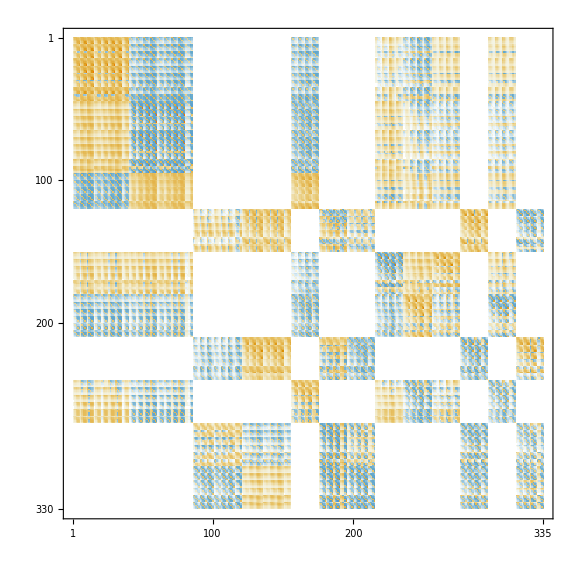
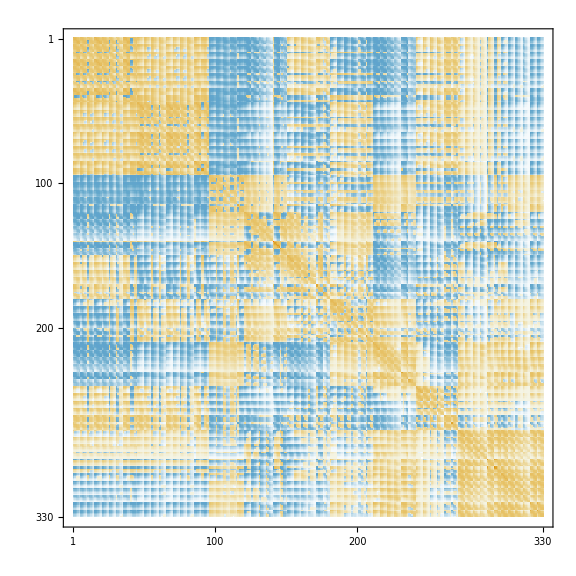
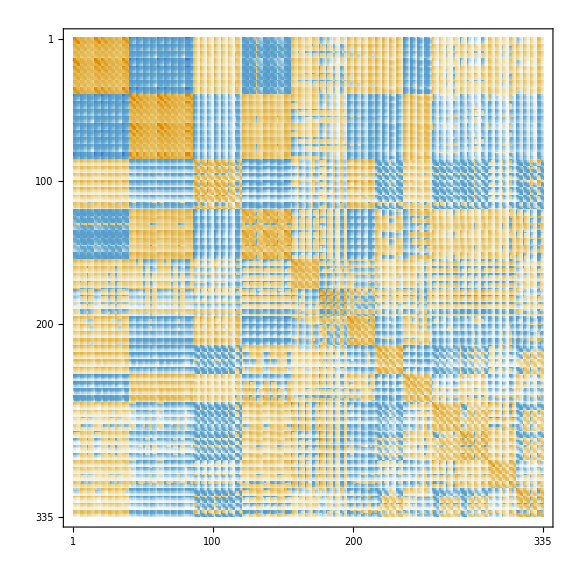
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
nb=1;nj=2;
Grid[{{
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[FSHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[DHam],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{D Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

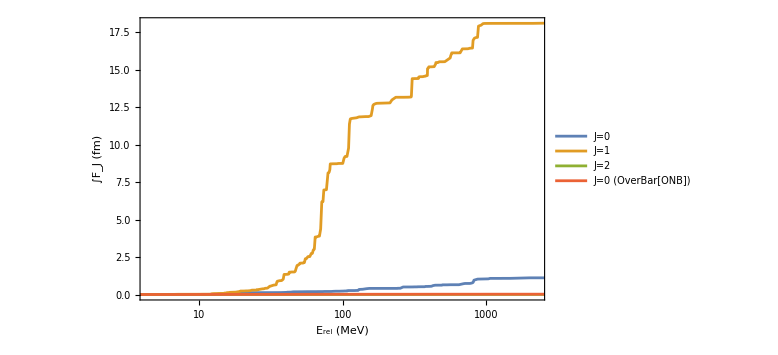

```mathematica
inhomoEBp=Table[{},{nj,Length[Subscript[I, n]]}];
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[(* final-state-J loop *)
Do[(* basis-scenario loop *)
Do[(* Subscript[m, L] loop *)
tmpt=Transpose[fulltrafosαβ[[nj]][[nb]]].CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].fulltrafonm;
tmpf=Table[{
esysFS[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmpt.evecGS)^2
},{nfs,1,FSDim[[nj]]}];

AppendTo[inhomoEB[[nj]],tmpf];

tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
tmpg=Table[{
esysFSp[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmp.evecGS)^2
},{nfs,1,FSDimp[[nj]]}];

AppendTo[inhomoEBp[[nj]],tmpg];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
fns=Table[Transpose[{inhomoEB[[Inn]][[1]][[All,1]],Accumulate[inhomoEB[[Inn]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]}];
fnsp=Table[Transpose[{inhomoEBp[[Inn]][[1]][[All,1]],Accumulate[inhomoEBp[[Inn]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]}];
ListLogLinearPlot[Join[fns,fnsp],PlotRange->{{0,2250},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J=0","J=1","J=2","J=0 (OverBar[ONB])","J=1 (OverBar[ONB])","J=2 (OverBar[ONB])"}]
```